# Durability of Immunity against reinfection of SARS-CoV-2

Jeffrey P. Townsend, Hayley B. Hassler, Zheng Wang, Sayaka Miura, Jaiveer Singh, Sudhir Kumar, Nancy H. Ruddle, Alison P. Galvani, and Alex Dornburg

Input Data: updated_OD _filev7.csv contains a processed supplementary dataset from Edridge et al. 2020, “Seasonal coronavirus protective immunity is short-lasting”, Nature Medicine.

```mathematica
headerrow=Take[Import["updated_OD_filev7.csv"], 1]
```

{{,X,Date,Virus,OD_value,V4,V5,V6,V8,V9}}

```mathematica
noheaderdataset=Drop[Import["updated_OD_filev7.csv"], 1]
```

{{1,1,1985-08-20,229E,0.614941,FALSE,NA,NA,0.149344,NA},{2,2,1985-11-18,229E,0.870174,FALSE,90,0.00283593,0.21133,0.000688733},3035,{3038,3038,1987-02-24,SOSIP_HIV,0.98111,NA,103,-0.000675504,0.724089,-0.000498542}}
 |  |  |  |

```mathematica
fulldataset=Transpose[Drop[Transpose[noheaderdataset], 1]]
```

{{1,1985-08-20,229E,0.614941,FALSE,NA,NA,0.149344,NA},{2,1985-11-18,229E,0.870174,FALSE,90,0.00283593,0.21133,0.000688733},3035,{3038,1987-02-24,SOSIP_HIV,0.98111,NA,103,-0.000675504,0.724089,-0.000498542}}
 |  |  |  |

```mathematica
Length[fulldataset]
```

3038

## OC43

Input Data: ELIZA ODs for HCoV-OC43 S IgG antibodies from the processed supplementary dataset from Edridge et al. 2020, “Seasonal coronavirus protective immunity is short-lasting”, Nature Medicine

```mathematica
oc43data=Select[fulldataset,MemberQ[#, "OC43"]&]
```

{{186,1985-08-20,OC43,0.625865,FALSE,NA,NA,0.17478,NA},{187,1985-11-18,OC43,0.567409,FALSE,90,-0.000649511,0.158456,-0.000181384},{188,1986-02-14,OC43,0.623283,FALSE,88,0.000634933,0.174059,0.000177313},{189,1986-05-29,OC43,0.548912,FALSE,104,-0.000715109,0.15329,-0.000199703},{190,1986-09-05,OC43,0.650512,FALSE,99,0.00102626,0.181663,0.000286595},{191,1986-11-26,OC43,0.485384,FALSE,82,-0.00201375,0.135549,-0.000562363},{192,1987-03-04,OC43,0.429709,TRUE,98,-0.000568119,0.120001,-0.000158654},{193,1987-06-01,OC43,1.57553,FALSE,89,0.0128744,0.439986,0.00359534},{194,1987-08-20,OC43,0.742936,FALSE,80,-0.0104075,0.207474,-0.00290641},{195,1987-11-19,OC43,0.803369,FALSE,91,0.000664099,0.22435,0.000185458},{196,1988-02-25,OC43,0.69314,FALSE,98,-0.00112479,0.193568,-0.00031411},{197,1988-05-19,OC43,0.76153,FALSE,84,0.000814164,0.212666,0.000227365},{198,1988-09-28,OC43,0.753975,FALSE,132,-0.0000572385,0.210556,-0.0000159845},{199,1988-12-14,OC43,0.352112,FALSE,77,-0.005219,0.0983314,-0.00145747},{200,1989-11-14,OC43,0.558201,FALSE,335,0.000615191,0.155884,0.000171799},{201,1990-06-11,OC43,0.520877,FALSE,209,-0.000178581,0.145461,-0.000049871},{202,1990-12-17,OC43,0.51518,FALSE,189,-0.0000301419,0.14387,-8.41749×10^-6},{203,1991-06-26,OC43,0.481127,FALSE,191,-0.000178288,0.134361,-0.0000497891},{204,1991-12-20,OC43,0.621467,FALSE,177,0.000792882,0.173552,0.000221422},{205,1992-12-11,OC43,0.525467,FALSE,357,-0.000268909,0.146743,-0.0000750959},{206,1993-06-11,OC43,0.420322,FALSE,182,-0.000577719,0.11738,-0.000161335},{207,1993-12-09,OC43,0.463572,TRUE,181,0.00023895,0.129458,0.0000667297},{208,1994-06-09,OC43,1.64436,FALSE,182,0.00648786,0.459208,0.00181181},{209,1994-12-08,OC43,0.993244,FALSE,182,-0.00357757,0.277375,-0.000999079},{210,1995-06-15,OC43,0.647702,FALSE,189,-0.00182827,0.180878,-0.000510565},{211,1995-12-11,OC43,0.900287,FALSE,179,0.00141109,0.251416,0.000394064},{212,1996-06-10,OC43,0.73542,FALSE,182,-0.000905861,0.205375,-0.000252973},{213,1996-12-02,OC43,0.545086,TRUE,175,-0.00108763,0.152222,-0.000303733},{214,2003-04-28,OC43,1.42408,FALSE,2338,0.000375961,0.397692,0.000104992},{215,2003-10-27,OC43,1.42167,FALSE,182,-0.0000132652,0.397018,-3.70446×10^-6},{216,2004-04-26,OC43,1.13369,FALSE,182,-0.00158232,0.316595,-0.00044188},{217,2004-10-25,OC43,1.14116,FALSE,182,0.0000410407,0.318681,0.0000114611},{218,2005-04-20,OC43,1.04744,FALSE,177,-0.000529479,0.292509,-0.000147863},{219,2005-11-02,OC43,0.959667,TRUE,196,-0.000447808,0.267999,-0.000125056},{220,2006-04-26,OC43,6.3461,FALSE,175,0.0307796,1.77222,0.00859557},{221,2006-10-25,OC43,3.93188,FALSE,182,-0.0132649,1.09802,-0.00370439},{222,2007-04-25,OC43,3.09606,FALSE,182,-0.0045924,0.864613,-0.00128248},{223,2008-07-16,OC43,1.61025,FALSE,448,-0.00331656,0.449681,-0.000926188},{224,2008-11-19,OC43,1.7298,FALSE,126,0.000948814,0.483067,0.000264968},{225,2009-05-18,OC43,1.65492,TRUE,180,-0.000416013,0.462155,-0.000116177},{226,2010-04-01,OC43,4.60792,FALSE,318,0.00928619,1.28682,0.00259328},{227,2011-04-12,OC43,1.77396,TRUE,376,-0.00753712,0.495401,-0.00210483},{228,2012-04-11,OC43,5.54096,FALSE,365,0.0103205,1.54738,0.00288213},{229,2013-04-09,OC43,2.20143,FALSE,363,-0.00919981,0.614775,-0.00256916},{230,2014-04-15,OC43,1.56626,FALSE,371,-0.00171204,0.437398,-0.000478107},{231,2015-04-28,OC43,1.34889,FALSE,378,-0.00057506,0.376694,-0.000160592},{232,2017-08-30,OC43,1.33132,NA,855,-0.0000205536,0.371786,-5.73983×10^-6},{504,1985-03-01,OC43,1.01262,FALSE,NA,NA,0.282786,NA},{505,1985-05-31,OC43,1.0175,FALSE,91,0.0000536686,0.28415,0.0000149876},{506,1985-09-05,OC43,0.914606,FALSE,97,-0.00106081,0.255415,-0.000296243},{507,1985-12-05,OC43,1.05222,FALSE,91,0.00151225,0.293845,0.000422313},{508,1986-03-20,OC43,0.980345,FALSE,105,-0.000684535,0.273773,-0.000191165},{509,1986-06-26,OC43,1.11123,FALSE,98,0.00133556,0.310324,0.000372972},{510,1986-09-18,OC43,0.902972,FALSE,84,-0.00247925,0.252166,-0.000692361},{511,1986-12-18,OC43,0.910291,FALSE,91,0.0000804214,0.25421,0.0000224586},{512,1987-03-19,OC43,0.938138,FALSE,91,0.000306016,0.261986,0.0000854585},{513,1987-06-25,OC43,0.9097,FALSE,98,-0.000290185,0.254045,-0.0000810375},{514,1987-09-14,OC43,1.06236,FALSE,81,0.00188463,0.296675,0.000526305},{515,1987-12-03,OC43,1.03307,FALSE,80,-0.000366051,0.288497,-0.000102224},{516,1988-03-03,OC43,0.990883,FALSE,91,-0.000463609,0.276716,-0.000129468},{517,1988-06-02,OC43,1.19579,FALSE,91,0.00225177,0.33394,0.000628833},{518,1988-09-06,OC43,1.25438,FALSE,96,0.000610226,0.350299,0.000170413},{519,1988-12-08,OC43,1.1625,FALSE,93,-0.00098789,0.324642,-0.00027588},{520,1989-06-08,OC43,0.818337,FALSE,182,-0.00189101,0.22853,-0.000528088},{521,1989-12-07,OC43,0.776383,FALSE,182,-0.000230517,0.216814,-0.0000643747},{522,1990-06-07,OC43,0.822597,FALSE,182,0.000253925,0.22972,0.0000709116},{523,1990-12-07,OC43,0.787488,FALSE,183,-0.000191856,0.219915,-0.000053578},{524,1991-06-07,OC43,1.02234,FALSE,182,0.00129041,0.285501,0.000360361},{525,1991-12-04,OC43,0.81014,FALSE,180,-0.0011789,0.226241,-0.000329221},{526,1992-06-03,OC43,1.01937,FALSE,182,0.0011496,0.28467,0.000321039},{527,1992-12-03,OC43,1.43204,FALSE,183,0.00225504,0.399914,0.000629747},{528,1993-06-03,OC43,0.760763,FALSE,182,-0.00368833,0.212452,-0.00103001},{529,1993-12-08,OC43,0.803748,FALSE,188,0.000228645,0.224456,0.000063852},{530,1994-06-16,OC43,0.855547,FALSE,190,0.000272627,0.238922,0.0000761342},{531,1994-12-14,OC43,0.81404,FALSE,181,-0.000229322,0.22733,-0.0000640409},{532,1995-06-21,OC43,0.843804,TRUE,189,0.000157481,0.235642,0.0000439784},{533,1995-12-06,OC43,1.97626,FALSE,168,0.0067408,0.551894,0.00188245},{534,1996-06-11,OC43,1.17406,FALSE,188,-0.00426699,0.327871,-0.00119161},{535,1996-12-04,OC43,0.913764,FALSE,176,-0.00147898,0.255179,-0.000413022},{536,2005-10-17,OC43,1.07497,FALSE,3239,0.000049771,0.300199,0.0000138991},{537,2006-04-18,OC43,0.963074,FALSE,183,-0.000611467,0.26895,-0.000170759},{538,2006-10-24,OC43,0.953165,FALSE,189,-0.0000524281,0.266183,-0.0000146412},{539,2007-04-24,OC43,0.878166,FALSE,182,-0.000412081,0.245238,-0.000115079},{540,2007-10-23,OC43,1.00831,FALSE,182,0.00071505,0.281581,0.000199686},{541,2008-04-15,OC43,1.30659,FALSE,175,0.00170448,0.364881,0.000475997},{542,2008-10-14,OC43,1.21888,FALSE,182,-0.000481904,0.340388,-0.000134578},{543,2009-04-07,OC43,0.990704,FALSE,175,-0.00130388,0.276666,-0.000364124},{544,2009-10-13,OC43,1.29532,FALSE,189,0.00161172,0.361733,0.000450091},{545,2010-04-13,OC43,1.1504,FALSE,182,-0.000796234,0.321264,-0.000222358},{546,2010-10-12,OC43,0.975702,FALSE,182,-0.000959898,0.272476,-0.000268063},{547,2011-04-26,OC43,0.929606,FALSE,196,-0.000235183,0.259604,-0.0000656776},{548,2011-10-18,OC43,0.944535,FALSE,175,0.0000853053,0.263773,0.0000238225},{549,2012-04-24,OC43,0.976784,FALSE,189,0.00017063,0.272779,0.0000476506},{550,2012-10-30,OC43,0.906027,FALSE,189,-0.000374373,0.253019,-0.000104548},{551,2013-04-22,OC43,1.17865,FALSE,174,0.00156678,0.329151,0.000437541},{552,2013-10-28,OC43,0.91647,FALSE,189,-0.00138718,0.255935,-0.000387387},{553,2014-04-29,OC43,0.910606,FALSE,183,-0.0000320423,0.254298,-8.9482×10^-6},{554,2014-10-29,OC43,0.93817,FALSE,183,0.000150622,0.261995,0.000042063},{555,2015-04-22,OC43,1.02803,FALSE,175,0.000513476,0.287089,0.000143394},{556,2015-10-27,OC43,1.01526,FALSE,188,-0.0000679356,0.283522,-0.0000189718},{557,2016-04-19,OC43,1.04833,FALSE,175,0.000188985,0.292758,0.0000527764},{558,2016-10-18,OC43,1.15757,FALSE,182,0.000600228,0.323265,0.000167621},{559,2017-04-25,OC43,0.984391,FALSE,189,-0.000916292,0.274903,-0.000255886},{560,2017-10-31,OC43,0.963975,FALSE,189,-0.00010802,0.269201,-0.0000301659},{561,2018-05-22,OC43,0.940506,FALSE,203,-0.000115612,0.262647,-0.0000322861},{562,2018-11-20,OC43,0.994532,FALSE,182,0.000296847,0.277735,0.000082898},{563,2019-05-16,OC43,1.03409,FALSE,177,0.000223474,0.288781,0.0000624079},{564,2019-11-19,OC43,0.958223,NA,187,-0.00040569,0.267595,-0.000113294},{870,1985-01-31,OC43,1.11052,FALSE,NA,NA,0.310127,NA},{871,1985-05-02,OC43,1.23607,FALSE,91,0.00137965,0.345188,0.000385285},{872,1985-08-06,OC43,1.15164,FALSE,96,-0.000879514,0.321609,-0.000245615},{873,1985-11-05,OC43,1.0021,FALSE,91,-0.00164326,0.279849,-0.000458899},{874,1986-02-04,OC43,1.21024,FALSE,91,0.00228723,0.337974,0.000638737},{875,1986-05-06,OC43,1.25105,FALSE,91,0.000448386,0.349369,0.000125217},{876,1986-08-06,OC43,1.17978,FALSE,92,-0.000774614,0.329468,-0.00021632},{877,1986-11-11,OC43,1.17653,FALSE,97,-0.0000335627,0.328559,-9.37277×10^-6},{878,1987-02-11,OC43,1.10933,FALSE,92,-0.000730424,0.309793,-0.00020398},{879,1987-05-11,OC43,1.17633,FALSE,89,0.000752875,0.328505,0.000210249},{880,1987-08-18,OC43,1.08154,FALSE,99,-0.000957483,0.302033,-0.000267389},{881,1987-11-04,OC43,1.05455,FALSE,78,-0.000346068,0.294495,-0.0000966436},{882,1988-02-03,OC43,1.08797,FALSE,91,0.000367289,0.303829,0.00010257},{883,1988-05-04,OC43,1.20005,FALSE,91,0.0012316,0.335127,0.00034394},{884,1988-08-10,OC43,1.06748,FALSE,98,-0.00135271,0.298107,-0.000377762},{885,1988-11-09,OC43,1.14189,FALSE,91,0.000817657,0.318886,0.00022834},{886,1989-05-10,OC43,1.00212,FALSE,182,-0.000767943,0.279854,-0.000214457},{887,1989-11-09,OC43,0.927181,FALSE,183,-0.000409513,0.258926,-0.000114361},{888,1990-05-09,OC43,0.900519,FALSE,181,-0.000147305,0.251481,-0.0000411368},{889,1990-11-07,OC43,0.91382,FALSE,182,0.0000730815,0.255195,0.0000204089},{890,1991-05-13,OC43,0.888239,FALSE,187,-0.000136795,0.248051,-0.0000382016},{891,1991-11-11,OC43,1.35832,FALSE,182,0.00258287,0.379327,0.000721296},{892,1992-05-11,OC43,1.10377,FALSE,182,-0.00139862,0.308241,-0.000390581},{893,1992-11-10,OC43,1.01514,FALSE,183,-0.000484334,0.28349,-0.000135256},{894,1993-05-10,OC43,1.07983,FALSE,181,0.000357418,0.301556,0.0000998133},{895,1993-11-10,OC43,0.934244,FALSE,184,-0.000791235,0.260899,-0.000220962},{896,1994-05-16,OC43,1.05246,FALSE,187,0.000632191,0.293913,0.000176547},{897,1994-11-07,OC43,0.867392,FALSE,175,-0.00105755,0.24223,-0.000295334},{898,1995-05-08,OC43,1.02907,FALSE,182,0.00088836,0.287381,0.000248085},{899,1995-11-06,OC43,0.994958,FALSE,182,-0.000187452,0.277854,-0.0000523483},{900,1996-05-13,OC43,1.05174,FALSE,189,0.000300428,0.29371,0.000083898},{901,1996-11-04,OC43,0.858943,FALSE,175,-0.00110169,0.23987,-0.000307659},{902,2003-06-25,OC43,0.924129,FALSE,2424,0.0000268918,0.258074,7.50986×10^-6},{903,2004-01-13,OC43,1.06539,FALSE,202,0.000699304,0.297522,0.000195289},{904,2004-08-03,OC43,0.954328,FALSE,203,-0.000547093,0.266508,-0.000152782},{905,2005-01-19,OC43,0.907421,FALSE,169,-0.000277557,0.253408,-0.0000775111},{906,2005-07-26,OC43,0.900932,FALSE,188,-0.0000345159,0.251596,-9.63899×10^-6},{907,2006-02-09,OC43,0.982929,FALSE,198,0.000414127,0.274495,0.00011565},{908,2006-08-08,OC43,0.932744,FALSE,180,-0.000278808,0.26048,-0.0000778604},{909,2007-02-20,OC43,0.817682,FALSE,196,-0.000587051,0.228347,-0.000163941},{910,2007-08-29,OC43,0.896349,FALSE,190,0.000414037,0.250316,0.000115625},{911,2008-02-20,OC43,0.826435,FALSE,175,-0.000399506,0.230792,-0.000111567},{912,2008-10-15,OC43,0.816271,FALSE,238,-0.0000427088,0.227953,-0.0000119269},{913,2009-04-23,OC43,0.725355,FALSE,190,-0.000478502,0.202564,-0.000133627},{914,2009-10-06,OC43,0.816856,FALSE,166,0.000551213,0.228117,0.000153933},{915,2010-03-30,OC43,0.842943,FALSE,175,0.000149068,0.235402,0.0000416289},{916,2010-09-30,OC43,0.935561,FALSE,184,0.000503356,0.261266,0.000140568},{917,2011-03-23,OC43,0.885157,FALSE,174,-0.000289678,0.247191,-0.0000808961},{918,2011-09-21,OC43,1.04633,FALSE,182,0.000885585,0.292201,0.00024731},{919,2012-05-02,OC43,0.900439,FALSE,224,-0.000651315,0.251458,-0.000181887},{920,2012-10-30,OC43,0.872725,FALSE,181,-0.000153116,0.243719,-0.0000427595},{921,2013-05-14,OC43,0.943629,FALSE,196,0.000361757,0.26352,0.000101025},{922,2013-11-06,OC43,0.966459,FALSE,176,0.000129714,0.269895,0.0000362243},{923,2014-05-07,OC43,1.00437,FALSE,182,0.000208311,0.280483,0.0000581734},{924,2014-11-05,OC43,0.942739,FALSE,182,-0.000338638,0.263271,-0.0000945687},{925,2015-04-14,OC43,1.02164,FALSE,160,0.0004931,0.285304,0.000137704},{926,2015-11-19,OC43,0.996832,FALSE,219,-0.000113255,0.278377,-0.0000316279},{927,2016-05-17,OC43,0.971104,FALSE,180,-0.000142935,0.271192,-0.0000399164},{928,2016-11-21,OC43,0.968628,FALSE,188,-0.000013169,0.270501,-3.67761×10^-6},{929,2017-05-02,OC43,0.864092,FALSE,162,-0.000645287,0.241308,-0.000180204},{930,2017-11-30,OC43,1.00635,FALSE,212,0.000671016,0.281034,0.000187389},{931,2018-05-29,OC43,1.22589,FALSE,180,0.00121968,0.342345,0.000340612},{932,2019-01-07,OC43,1.13047,FALSE,223,-0.000427907,0.315696,-0.000119498},{933,2019-07-16,OC43,1.09188,FALSE,190,-0.000203094,0.30492,-0.0000567164},{934,2020-01-14,OC43,1.25607,NA,182,0.000902171,0.350774,0.000251942},{1186,1985-01-31,OC43,0.619687,FALSE,NA,NA,0.173055,NA},{1187,1985-05-08,OC43,0.700189,FALSE,97,0.000829915,0.195536,0.000231764},{1188,1985-08-09,OC43,0.574213,FALSE,93,-0.00135458,0.160356,-0.000378282},{1189,1985-11-13,OC43,0.703528,FALSE,96,0.00134702,0.196469,0.000376172},{1190,1986-02-13,OC43,0.66472,FALSE,92,-0.000421823,0.185631,-0.000117799},{1191,1986-05-15,OC43,0.894791,FALSE,91,0.00252826,0.249881,0.000706045},{1192,1986-09-05,OC43,0.752774,FALSE,113,-0.00125679,0.210221,-0.000350973},{1193,1986-11-17,OC43,0.752006,FALSE,73,-0.0000105187,0.210007,-2.93747×10^-6},{1194,1987-02-03,OC43,0.503012,FALSE,78,-0.00319223,0.140472,-0.000891469},{1195,1987-04-23,OC43,0.641649,FALSE,79,0.0017549,0.179188,0.000490075},{1196,1987-07-27,OC43,0.61945,TRUE,95,-0.000233677,0.172989,-0.0000652572},{1197,1987-10-26,OC43,1.61758,FALSE,91,0.0109685,0.45173,0.00306309},{1198,1988-01-20,OC43,1.1189,FALSE,86,-0.00579869,0.312465,-0.00161935},{1199,1988-04-20,OC43,0.921407,FALSE,91,-0.00217022,0.257314,-0.00060606},{1200,1988-07-27,OC43,0.926743,FALSE,98,0.0000544582,0.258804,0.0000152081},{1201,1988-10-25,OC43,0.858822,FALSE,90,-0.00075468,0.239836,-0.000210754},{1202,1989-04-26,OC43,0.736844,FALSE,183,-0.000666548,0.205772,-0.000186141},{1203,1989-10-25,OC43,0.839219,FALSE,182,0.000562501,0.234362,0.000157085},{1204,1990-04-25,OC43,0.856507,FALSE,182,0.0000949864,0.23919,0.0000265261},{1205,1990-10-19,OC43,0.806769,TRUE,177,-0.000281005,0.2253,-0.000078474},{1206,1991-04-24,OC43,2.11447,FALSE,187,0.00699303,0.59049,0.00195289},{1207,1991-10-30,OC43,0.938054,FALSE,189,-0.0062244,0.261963,-0.00173824},{1208,1992-04-28,OC43,0.861073,FALSE,181,-0.00042531,0.240465,-0.000118773},{1209,1992-10-28,OC43,0.867629,FALSE,183,0.0000358247,0.242296,0.0000100045},{1210,1993-04-27,OC43,0.815697,FALSE,181,-0.000286914,0.227793,-0.0000801241},{1211,1993-11-08,OC43,0.861131,FALSE,195,0.000232993,0.240481,0.0000650662},{1212,1994-05-16,OC43,0.826661,FALSE,189,-0.00018238,0.230855,-0.0000509317},{1213,1994-11-09,OC43,0.809047,FALSE,177,-0.0000995133,0.225936,-0.0000277903},{1214,1995-05-10,OC43,0.738667,FALSE,182,-0.000386704,0.206282,-0.000107992},{1215,1995-11-08,OC43,0.775279,FALSE,182,0.000201161,0.216506,0.0000561766},{1216,1996-04-22,OC43,0.816842,FALSE,166,0.000250379,0.228113,0.0000699214},{1217,1996-10-22,OC43,0.741863,TRUE,183,-0.000409721,0.207174,-0.00011442},{1218,2003-05-13,OC43,1.26003,FALSE,2394,0.000216446,0.35188,0.0000604451},{1219,2003-11-25,OC43,1.15927,TRUE,196,-0.000514108,0.32374,-0.000143571},{1220,2004-05-10,OC43,2.1894,FALSE,167,0.00616845,0.611416,0.00172261},{1221,2004-10-13,OC43,1.61609,FALSE,156,-0.00367506,0.451313,-0.0010263},{1222,2005-04-13,OC43,1.41059,FALSE,182,-0.00112911,0.393925,-0.000315316},{1223,2005-10-12,OC43,1.32682,FALSE,182,-0.000460293,0.37053,-0.000128542},{1224,2006-04-19,OC43,2.08048,FALSE,189,0.00398763,0.581,0.00111359},{1225,2006-10-24,OC43,2.07505,FALSE,188,-0.0000289172,0.579482,-8.07546×10^-6},{1226,2007-05-03,OC43,1.47883,FALSE,191,-0.00312157,0.41298,-0.000871736},{1227,2007-10-09,OC43,1.40274,FALSE,159,-0.000478511,0.391733,-0.00013363},{1228,2008-04-09,OC43,1.30813,FALSE,183,-0.000517035,0.36531,-0.000144388},{1229,2008-11-06,OC43,1.30914,FALSE,211,4.82676×10^-6,0.365594,1.34793×10^-6},{1230,2009-04-23,OC43,1.14783,FALSE,168,-0.000960225,0.320544,-0.000268154},{1231,2009-10-29,OC43,1.05719,FALSE,189,-0.000479542,0.295234,-0.000133918},{1232,2010-04-28,OC43,1.05142,TRUE,181,-0.0000318877,0.293622,-8.90501×10^-6},{1233,2010-10-20,OC43,3.26778,NA,175,0.0126649,0.912567,0.00353683},{1469,1985-05-06,OC43,0.856016,FALSE,NA,NA,0.239053,NA},{1470,1985-08-06,OC43,0.864658,FALSE,92,0.0000939365,0.241466,0.0000262329},{1471,1985-11-06,OC43,0.823214,FALSE,92,-0.000450479,0.229892,-0.000125802},{1472,1986-02-05,OC43,0.828595,FALSE,91,0.000059131,0.231395,0.000016513},{1473,1986-04-28,OC43,0.749655,FALSE,82,-0.000962685,0.20935,-0.000268841},{1474,1986-07-31,OC43,0.808141,FALSE,94,0.000622195,0.225683,0.000173755},{1475,1986-10-30,OC43,0.729551,FALSE,91,-0.000863626,0.203736,-0.000241178},{1476,1987-02-03,OC43,0.913351,FALSE,96,0.00191458,0.255064,0.000534669},{1477,1987-05-07,OC43,0.825076,FALSE,93,-0.000949189,0.230412,-0.000265072},{1478,1987-08-06,OC43,0.798298,FALSE,91,-0.000294271,0.222934,-0.0000821788},{1479,1987-11-02,OC43,0.774756,FALSE,88,-0.000267512,0.21636,-0.000074706},{1480,1988-02-03,OC43,0.723319,FALSE,93,-0.000553087,0.201996,-0.000154456},{1481,1988-05-11,OC43,0.856454,FALSE,98,0.00135851,0.239175,0.000379381},{1482,1988-08-17,OC43,0.951213,FALSE,98,0.000966932,0.265638,0.000270027},{1483,1988-11-14,OC43,0.838305,FALSE,89,-0.00126863,0.234107,-0.00035428},{1484,1989-02-06,OC43,1.14157,FALSE,84,0.00361032,0.318797,0.00100822},{1485,1989-08-02,OC43,1.02655,FALSE,177,-0.000649832,0.286677,-0.000181473},{1486,1990-02-19,OC43,1.01905,FALSE,201,-0.0000373299,0.284581,-0.0000104248},{1487,1990-08-08,OC43,0.990796,FALSE,170,-0.000166187,0.276692,-0.0000464096},{1488,1991-02-07,OC43,0.88311,FALSE,183,-0.000588447,0.246619,-0.000164331},{1489,1991-08-07,OC43,0.936884,FALSE,181,0.000297094,0.261636,0.0000829672},{1490,1992-02-05,OC43,1.01235,FALSE,182,0.000414621,0.28271,0.000115788},{1491,1992-07-22,OC43,1.00561,FALSE,168,-0.0000400689,0.28083,-0.0000111897},{1492,1993-02-04,OC43,1.19722,FALSE,197,0.000972614,0.334338,0.000271614},{1493,1993-08-04,OC43,1.00322,FALSE,181,-0.0010718,0.280162,-0.000299312},{1494,1994-02-02,OC43,1.09798,FALSE,182,0.000520658,0.306625,0.0001454},{1495,1994-08-03,OC43,1.07407,FALSE,182,-0.000131374,0.299948,-0.0000366877},{1496,1995-02-01,OC43,1.22678,FALSE,182,0.000839052,0.342593,0.000234315},{1497,1995-07-31,OC43,1.15337,FALSE,180,-0.000407853,0.322092,-0.000113898},{1498,1996-02-05,OC43,1.12914,FALSE,189,-0.000128199,0.315325,-0.0000358011},{1499,1996-08-27,OC43,1.38254,FALSE,204,0.00124218,0.386091,0.000346894},{1500,1997-02-27,OC43,1.26761,FALSE,184,-0.000624606,0.353997,-0.000174429},{1501,2003-04-17,OC43,1.1504,FALSE,2240,-0.0000523267,0.321264,-0.0000146129},{1502,2003-10-13,OC43,1.21787,FALSE,179,0.000376895,0.340104,0.000105252},{1503,2004-04-20,OC43,1.04557,FALSE,190,-0.000906839,0.291987,-0.000253246},{1504,2004-10-20,OC43,0.956249,FALSE,183,-0.000488081,0.267044,-0.000136303},{1505,2005-04-19,OC43,1.15218,FALSE,181,0.00108251,0.321761,0.000302305},{1506,2005-10-26,OC43,1.22357,FALSE,190,0.000375696,0.341695,0.000104918},{1507,2006-04-24,OC43,1.04095,FALSE,180,-0.00101456,0.290696,-0.000283327},{1508,2006-10-23,OC43,1.21382,FALSE,182,0.000949854,0.338973,0.000265258},{1509,2007-04-25,OC43,1.07483,FALSE,184,-0.000755399,0.300158,-0.000210954},{1510,2007-10-23,OC43,1.24451,FALSE,181,0.000937475,0.347544,0.000261801},{1511,2008-04-24,OC43,1.04848,FALSE,184,-0.00106537,0.292801,-0.000297516},{1512,2008-10-21,OC43,0.968739,FALSE,180,-0.000443012,0.270532,-0.000123716},{1513,2009-04-15,OC43,0.927875,FALSE,176,-0.000232183,0.25912,-0.00006484},{1514,2009-10-15,OC43,1.064,FALSE,183,0.000743879,0.297136,0.000207737},{1515,2010-04-08,OC43,1.21481,FALSE,175,0.00086174,0.33925,0.000240651},{1516,2010-10-07,OC43,1.2112,NA,182,-0.0000198171,0.338243,-5.53415×10^-6},{1754,1984-11-28,OC43,0.655497,TRUE,NA,NA,0.183055,NA},{1755,1985-02-27,OC43,2.07962,FALSE,91,0.0156497,0.580758,0.00437035},{1756,1985-05-24,OC43,0.77723,FALSE,86,-0.015144,0.217051,-0.00422915},{1757,1985-08-27,OC43,0.935571,FALSE,95,0.00166675,0.261269,0.000465461},{1758,1985-11-29,OC43,1.07747,FALSE,94,0.00150958,0.300897,0.000421569},{1759,1986-02-28,OC43,0.905004,FALSE,91,-0.00189526,0.252733,-0.000529273},{1760,1986-05-30,OC43,0.872945,FALSE,91,-0.000352303,0.24378,-0.0000983848},{1761,1986-08-28,OC43,0.992467,FALSE,90,0.00132803,0.277158,0.000370867},{1762,1986-11-24,OC43,1.12014,FALSE,88,0.00145082,0.312812,0.000405157},{1763,1987-02-23,OC43,0.937705,FALSE,91,-0.00200476,0.261865,-0.000559854},{1764,1987-05-18,OC43,0.919192,FALSE,84,-0.000220391,0.256695,-0.0000615467},{1765,1987-08-17,OC43,1.21725,FALSE,91,0.00327536,0.339932,0.000914684},{1766,1987-11-16,OC43,1.11345,FALSE,91,-0.00114071,0.310943,-0.000318558},{1767,1988-02-18,OC43,1.06043,FALSE,94,-0.000564006,0.296137,-0.000157506},{1768,1988-05-26,OC43,0.958156,FALSE,98,-0.0010436,0.267576,-0.000291438},{1769,1988-08-26,OC43,1.0517,FALSE,92,0.00101681,0.2937,0.000283957},{1770,1988-11-28,OC43,1.1399,FALSE,94,0.000938295,0.318331,0.00026203},{1771,1989-02-23,OC43,1.14179,FALSE,87,0.0000216627,0.318858,6.04958×10^-6},{1772,1989-05-18,OC43,1.20506,FALSE,84,0.00075322,0.336527,0.000210346},{1773,1989-08-08,OC43,1.06234,FALSE,82,-0.00174041,0.296672,-0.000486031},{1774,1989-11-07,OC43,0.989575,FALSE,91,-0.000799651,0.276351,-0.000223312},{1775,1990-02-06,OC43,1.00313,FALSE,91,0.000148915,0.280135,0.0000415863},{1776,1990-05-07,OC43,1.07662,FALSE,90,0.000816571,0.300658,0.000228037},{1777,1990-07-11,OC43,1.04189,FALSE,65,-0.000534232,0.290961,-0.000149191},{1778,1990-11-12,OC43,1.07224,FALSE,124,0.000244739,0.299436,0.0000683463},{1779,1991-02-05,OC43,1.21024,FALSE,85,0.00162347,0.337973,0.000453373},{1780,1991-05-15,OC43,1.01374,FALSE,99,-0.00198484,0.283098,-0.000554291},{1781,1991-08-07,OC43,0.884425,FALSE,84,-0.00153942,0.246986,-0.000429901},{1782,1991-11-20,OC43,0.967089,FALSE,105,0.00078728,0.270071,0.000219857},{1783,1992-02-19,OC43,0.940401,FALSE,91,-0.000293279,0.262618,-0.0000819017},{1784,1992-05-20,OC43,1.00364,FALSE,91,0.00069494,0.280279,0.00019407},{1785,1992-08-20,OC43,1.11965,FALSE,92,0.00126093,0.312675,0.000352131},{1786,1992-11-18,OC43,1.10359,FALSE,90,-0.000178405,0.308191,-0.0000498218},{1787,1993-02-18,OC43,0.932223,FALSE,92,-0.00186269,0.260334,-0.000520178},{1788,1993-06-03,OC43,1.11902,FALSE,105,0.00177907,0.312501,0.000496825},{1789,1993-09-16,OC43,1.1665,FALSE,105,0.000452113,0.325758,0.000126258},{1790,1993-12-16,OC43,1.0778,FALSE,91,-0.000974629,0.30099,-0.000272177},{1791,1994-03-17,OC43,1.09164,FALSE,91,0.000152042,0.304854,0.0000424594},{1792,1994-06-27,OC43,0.934357,FALSE,102,-0.001542,0.26093,-0.000430622},{1793,1994-10-12,OC43,1.07413,FALSE,107,0.00130631,0.299964,0.000364804},{1794,1995-01-18,OC43,0.943519,FALSE,98,-0.00133279,0.263489,-0.000372197},{1795,1995-04-18,OC43,0.875234,FALSE,90,-0.000758722,0.24442,-0.000211882},{1796,1995-07-11,OC43,0.899518,FALSE,84,0.000289089,0.251201,0.0000807316},{1797,1995-10-10,OC43,0.843866,FALSE,91,-0.000611557,0.23566,-0.000170785},{1798,1996-01-11,OC43,0.829847,FALSE,93,-0.000150738,0.231745,-0.0000420955},{1799,1996-04-15,OC43,0.766134,FALSE,95,-0.000670669,0.213952,-0.000187292},{1800,1996-08-05,OC43,0.802569,FALSE,112,0.000325316,0.224127,0.0000908483},{1801,1996-11-05,OC43,0.879469,FALSE,92,0.000835864,0.245602,0.000233425},{1802,1997-02-11,OC43,0.867863,NA,98,-0.000118422,0.242361,-0.0000330707},{1976,1985-06-26,OC43,0.817139,FALSE,NA,NA,0.228196,NA},{1977,1985-09-25,OC43,0.826999,FALSE,91,0.000108349,0.230949,0.0000302576},{1978,1985-12-18,OC43,0.684031,FALSE,84,-0.001702,0.191024,-0.000475305},{1979,1986-03-26,OC43,0.827308,FALSE,98,0.00146201,0.231036,0.000408285},{1980,1986-07-02,OC43,0.988001,FALSE,98,0.00163972,0.275911,0.000457913},{1981,1986-10-01,OC43,0.77334,FALSE,91,-0.00235891,0.215964,-0.000658755},{1982,1987-01-07,OC43,0.835269,FALSE,98,0.000631924,0.233259,0.000176472},{1983,1987-03-25,OC43,0.951329,FALSE,77,0.00150728,0.26567,0.000420925},{1984,1987-07-01,OC43,0.828184,FALSE,98,-0.00125658,0.23128,-0.000350916},{1985,1987-09-30,OC43,0.877837,FALSE,91,0.000545644,0.245146,0.000152377},{1986,1988-01-06,OC43,0.769623,FALSE,98,-0.00110423,0.214926,-0.000308369},{1987,1988-03-30,OC43,0.64748,FALSE,84,-0.00145409,0.180816,-0.000406071},{1988,1988-06-29,OC43,0.681461,FALSE,91,0.000373423,0.190306,0.000104283},{1989,1988-09-28,OC43,0.718093,TRUE,91,0.000402543,0.200536,0.000112415},{1990,1989-01-03,OC43,2.18885,FALSE,97,0.0151625,0.611263,0.0042343},{1991,1989-07-03,OC43,0.816872,FALSE,181,-0.00758,0.228121,-0.0021168},{1992,1990-06-20,OC43,0.980074,FALSE,352,0.000463643,0.273697,0.000129478},{1993,1990-12-20,OC43,0.992426,FALSE,183,0.0000674975,0.277147,0.0000188495},{1994,1991-06-13,OC43,1.02323,FALSE,175,0.000176027,0.285749,0.0000491576},{1995,1991-12-16,OC43,1.17407,FALSE,186,0.000810964,0.327873,0.000226471},{1996,1992-07-02,OC43,1.20446,FALSE,199,0.000152731,0.336361,0.000042652},{1997,1993-01-08,OC43,0.910972,FALSE,190,-0.00154469,0.2544,-0.000431374},{1998,1993-07-02,OC43,1.39843,FALSE,175,0.00278545,0.390527,0.00077787},{1999,1994-01-07,OC43,2.13195,FALSE,189,0.00388109,0.595373,0.00108384},{2000,1994-06-28,OC43,1.32001,FALSE,172,-0.00472062,0.368627,-0.00131829},{2001,1995-01-06,OC43,0.858639,FALSE,192,-0.00240295,0.239785,-0.000671052},{2002,1995-06-30,OC43,0.769155,FALSE,175,-0.000511336,0.214796,-0.000142797},{2003,1996-01-03,OC43,0.990076,TRUE,187,0.00118139,0.276491,0.000329918},{2004,1996-06-26,OC43,2.46278,FALSE,175,0.00841543,0.687759,0.00235011},{2005,1996-12-18,OC43,1.00644,FALSE,175,-0.00832191,0.281061,-0.00232399},{2006,2003-03-03,OC43,1.66154,NA,2266,0.0002891,0.464006,0.0000807347},{2225,1986-09-08,OC43,1.46188,FALSE,NA,NA,0.408248,NA},{2226,1986-12-08,OC43,1.07474,TRUE,91,-0.0042543,0.300134,-0.00118806},{2227,1987-03-13,OC43,2.8319,FALSE,95,0.0184964,0.790842,0.00516534},{2228,1987-06-15,OC43,1.78145,FALSE,94,-0.011175,0.497493,-0.00312074},{2229,1987-09-07,OC43,1.43564,FALSE,84,-0.00411683,0.40092,-0.00114967},{2230,1987-12-14,OC43,1.33797,FALSE,98,-0.000996627,0.373645,-0.00027832},{2231,1988-03-14,OC43,1.2443,FALSE,91,-0.00102941,0.347484,-0.000287475},{2232,1988-06-13,OC43,1.22734,FALSE,91,-0.000186316,0.34275,-0.0000520309},{2233,1988-09-16,OC43,1.23956,FALSE,95,0.000128597,0.346161,0.0000359121},{2234,1988-12-16,OC43,1.10416,FALSE,91,-0.0014879,0.308349,-0.000415514},{2235,1989-06-09,OC43,1.29075,FALSE,175,0.00106626,0.360458,0.000297765},{2236,1989-12-15,OC43,1.16234,FALSE,189,-0.000679418,0.324598,-0.000189735},{2237,1990-06-15,OC43,1.14636,FALSE,182,-0.0000878231,0.320135,-0.0000245257},{2238,1990-12-10,OC43,1.12227,FALSE,178,-0.000135316,0.313408,-0.0000377887},{2239,1991-06-10,OC43,1.10827,FALSE,182,-0.000076917,0.309499,-0.00002148},{2240,1991-12-09,OC43,1.19435,FALSE,182,0.000472915,0.333535,0.000132067},{2241,1992-06-10,OC43,1.14176,FALSE,184,-0.000285786,0.31885,-0.0000798091},{2242,1992-12-21,OC43,1.18495,FALSE,194,0.000222626,0.330911,0.0000621709},{2243,1993-06-28,OC43,1.10417,FALSE,189,-0.000427389,0.308354,-0.000119353},{2244,1993-12-13,OC43,1.01308,FALSE,168,-0.000542243,0.282914,-0.000151428},{2245,1994-07-18,OC43,0.843724,FALSE,217,-0.000780428,0.23562,-0.000217944},{2246,1995-01-16,OC43,0.936867,FALSE,182,0.000511775,0.261631,0.000142919},{2247,1995-07-17,OC43,1.05034,FALSE,182,0.0006235,0.293321,0.00017412},{2248,1996-01-19,OC43,1.07807,FALSE,186,0.000149081,0.301065,0.0000416326},{2249,1996-07-09,OC43,1.09689,FALSE,172,0.000109411,0.30632,0.0000305542},{2250,1996-12-16,OC43,0.999847,FALSE,160,-0.000606531,0.279219,-0.000169381},{2251,2003-04-07,OC43,1.07805,FALSE,2303,0.0000339568,0.301058,9.48283×10^-6},{2252,2003-10-13,OC43,0.955232,FALSE,189,-0.000649828,0.26676,-0.000181472},{2253,2004-04-19,OC43,0.765217,FALSE,189,-0.00100537,0.213696,-0.000280762},{2254,2004-10-11,OC43,0.784986,FALSE,175,0.000112966,0.219217,0.0000315471},{2255,2005-04-11,OC43,0.70269,FALSE,182,-0.000452175,0.196235,-0.000126275},{2256,2005-10-17,OC43,0.726994,FALSE,189,0.000128595,0.203022,0.0000359116},{2257,2006-04-24,OC43,0.77299,FALSE,189,0.000243361,0.215867,0.0000679614},{2258,2007-03-26,OC43,0.819285,FALSE,336,0.000137783,0.228795,0.0000384776},{2259,2007-09-24,OC43,0.836123,FALSE,182,0.0000925167,0.233497,0.0000258364},{2260,2008-04-21,OC43,0.731993,FALSE,210,-0.000495856,0.204418,-0.000138474},{2261,2008-10-13,OC43,0.706283,FALSE,175,-0.000146917,0.197238,-0.0000410283},{2262,2009-04-06,OC43,0.673115,FALSE,175,-0.000189532,0.187975,-0.000052929},{2263,2009-10-05,OC43,0.735947,FALSE,182,0.000345232,0.205522,0.0000964102},{2264,2010-06-07,OC43,0.699592,FALSE,245,-0.000148385,0.19537,-0.0000414384},{2265,2010-12-13,OC43,0.858617,FALSE,189,0.000841401,0.239779,0.000234971},{2266,2011-05-09,OC43,0.80513,FALSE,147,-0.000363861,0.224842,-0.000101612},{2267,2011-11-07,OC43,1.24667,FALSE,182,0.00242606,0.348148,0.000677505},{2268,2012-07-09,OC43,0.890077,FALSE,245,-0.00145549,0.248565,-0.000406462},{2269,2013-01-07,OC43,0.871971,FALSE,182,-0.0000994843,0.243508,-0.0000277822},{2270,2013-07-08,OC43,0.74937,FALSE,182,-0.000673634,0.20927,-0.00018812},{2271,2014-01-27,OC43,0.650925,FALSE,203,-0.000484953,0.181778,-0.000135429},{2272,2014-07-14,OC43,0.846369,NA,168,0.00116336,0.236359,0.000324882},{2587,1984-11-14,OC43,0.768444,FALSE,NA,NA,0.214597,NA},{2588,1985-02-15,OC43,0.665329,TRUE,93,-0.00110877,0.185801,-0.000309636},{2589,1985-05-20,OC43,1.66069,FALSE,94,0.010589,0.463768,0.00295709},{2590,1985-08-16,OC43,0.98497,FALSE,88,-0.00767866,0.275065,-0.00214436},{2591,1985-11-15,OC43,0.802994,FALSE,91,-0.00199974,0.224246,-0.00055845},{2592,1986-02-14,OC43,0.782615,FALSE,91,-0.000223944,0.218555,-0.0000625389},{2593,1986-05-21,OC43,0.684316,FALSE,96,-0.00102394,0.191103,-0.000285949},{2594,1986-08-25,OC43,0.772448,FALSE,96,0.000918043,0.215715,0.000256375},{2595,1986-11-17,OC43,0.87901,TRUE,84,0.00126859,0.245474,0.000354268},{2596,1987-02-16,OC43,3.65401,FALSE,91,0.0304945,1.02043,0.00851596},{2597,1987-05-18,OC43,2.03539,FALSE,91,-0.0177871,0.568406,-0.00496727},{2598,1987-08-17,OC43,1.21653,FALSE,91,-0.00899844,0.33973,-0.00251292},{2599,1987-11-11,OC43,0.959217,FALSE,86,-0.00299198,0.267873,-0.000835545},{2600,1988-02-09,OC43,0.85408,FALSE,90,-0.00116819,0.238512,-0.000326231},{2601,1988-06-09,OC43,1.03014,FALSE,121,0.00145506,0.28768,0.000406344},{2602,1988-08-10,OC43,0.851858,FALSE,62,-0.00287556,0.237891,-0.000803034},{2603,1988-11-14,OC43,0.818581,FALSE,96,-0.000346632,0.228599,-0.0000968012},{2604,1989-05-30,OC43,0.600007,FALSE,197,-0.00110951,0.167559,-0.000309845},{2605,1989-11-06,OC43,0.627144,FALSE,160,0.00016961,0.175138,0.0000473656},{2606,1990-05-14,OC43,0.544103,FALSE,189,-0.000439372,0.151947,-0.0001227},{2607,1990-11-06,OC43,0.531814,TRUE,176,-0.0000698233,0.148515,-0.000019499},{2608,1991-05-23,OC43,1.16068,FALSE,198,0.00317611,0.324135,0.000886967},{2609,1991-11-04,OC43,1.1401,FALSE,165,-0.00012474,0.318387,-0.0000348352},{2610,1992-05-10,OC43,0.79401,FALSE,188,-0.00184092,0.221737,-0.000514098},{2611,1992-11-09,OC43,0.638715,FALSE,183,-0.000848603,0.178369,-0.000236983},{2612,1993-05-11,OC43,0.53987,FALSE,183,-0.000540135,0.150765,-0.000150839},{2613,1993-11-22,OC43,0.506982,FALSE,195,-0.00016866,0.141581,-0.0000471003},{2614,1994-05-24,OC43,0.441599,FALSE,183,-0.000357282,0.123322,-0.0000997754},{2615,1994-11-29,OC43,0.443725,FALSE,189,0.0000112484,0.123916,3.14124×10^-6},{2616,1995-05-30,OC43,0.496229,FALSE,182,0.000288482,0.138578,0.0000805621},{2617,1995-12-04,OC43,0.467986,FALSE,188,-0.000150228,0.130691,-0.000041953},{2618,1996-05-30,OC43,0.453912,FALSE,178,-0.0000790665,0.12676,-0.0000220803},{2619,1996-12-03,OC43,0.402286,TRUE,187,-0.000276075,0.112343,-0.0000770972},{2620,2003-04-10,OC43,2.84597,FALSE,2319,0.00105377,0.794772,0.000294277},{2621,2003-10-13,OC43,0.721084,FALSE,186,-0.0114241,0.201371,-0.00319033},{2622,2004-04-13,OC43,0.594698,FALSE,183,-0.000690635,0.166076,-0.000192868},{2623,2004-10-12,OC43,0.57937,FALSE,182,-0.000084216,0.161796,-0.0000235183},{2624,2005-04-11,OC43,0.794052,FALSE,181,0.00118609,0.221749,0.00033123},{2625,2005-10-10,OC43,0.654846,TRUE,182,-0.000764869,0.182874,-0.000213599},{2626,2006-04-11,OC43,1.41576,FALSE,183,0.00415802,0.395369,0.00116118},{2627,2006-10-10,OC43,1.40311,TRUE,182,-0.0000695313,0.391835,-0.0000194174},{2628,2007-04-10,OC43,2.34913,FALSE,182,0.00519789,0.656021,0.00145157},{2629,2007-10-08,OC43,1.57635,FALSE,181,-0.00426947,0.440215,-0.0011923},{2630,2008-04-07,OC43,1.46178,FALSE,182,-0.000629522,0.408219,-0.000175801},{2631,2008-10-09,OC43,1.3816,FALSE,185,-0.000433388,0.385829,-0.000121029},{2632,2009-04-09,OC43,1.26492,FALSE,182,-0.000641095,0.353245,-0.000179033},{2633,2009-10-08,OC43,1.21812,FALSE,182,-0.000257153,0.340175,-0.000071813},{2634,2010-04-01,OC43,1.30672,FALSE,175,0.000506295,0.364918,0.000141389},{2635,2010-10-04,OC43,1.28474,FALSE,186,-0.00011817,0.35878,-0.0000330005},{2636,2011-04-04,OC43,1.20269,FALSE,182,-0.000450828,0.335866,-0.000125899},{2637,2011-09-29,OC43,1.28522,FALSE,178,0.000463664,0.358914,0.000129484},{2638,2012-04-16,OC43,1.46999,FALSE,200,0.000923817,0.410512,0.000257987},{2639,2012-12-03,OC43,1.35549,FALSE,231,-0.00049565,0.378537,-0.000138416},{2640,2013-06-03,OC43,1.22514,FALSE,182,-0.000716215,0.342135,-0.000200011},{2641,2013-12-16,OC43,1.19229,FALSE,196,-0.000167628,0.33296,-0.000046812},{2642,2014-06-16,OC43,1.67205,FALSE,182,0.00263606,0.46694,0.00073615},{2643,2014-12-11,OC43,1.41617,FALSE,178,-0.00143749,0.395484,-0.000401437},{2644,2015-06-11,OC43,1.98807,FALSE,182,0.00314226,0.555191,0.000877513},{2645,2015-12-17,OC43,1.53248,FALSE,189,-0.00241049,0.427964,-0.000673157},{2646,2016-06-23,OC43,1.60767,FALSE,189,0.00039782,0.448962,0.000111096},{2647,2016-12-15,OC43,1.39921,FALSE,175,-0.00119123,0.390745,-0.000332666},{2648,2017-04-24,OC43,1.32544,FALSE,130,-0.0005674,0.370146,-0.000158453},{2649,2017-09-26,OC43,1.31051,FALSE,155,-0.0000963473,0.365976,-0.0000269061},{2650,2018-03-27,OC43,1.314,FALSE,182,0.0000191774,0.36695,5.35551×10^-6},{2651,2018-09-27,OC43,1.26205,FALSE,184,-0.000282354,0.352442,-0.0000788507},{2652,2019-04-04,OC43,1.23684,FALSE,189,-0.000133355,0.345403,-0.0000372409},{2653,2019-10-08,OC43,1.25918,NA,187,0.000119474,0.351642,0.0000333645},{2932,1985-04-24,OC43,0.972319,FALSE,NA,NA,0.271532,NA},{2933,1985-05-23,OC43,0.955702,TRUE,29,-0.000572995,0.266891,-0.000160016},{2934,1985-08-23,OC43,10.4494,FALSE,92,0.103192,2.91811,0.0288176},{2935,1985-11-22,OC43,2.19536,FALSE,91,-0.0907035,0.61308,-0.02533},{2936,1986-02-21,OC43,1.44476,FALSE,91,-0.00824828,0.403468,-0.00230343},{2937,1986-05-23,OC43,1.14924,FALSE,91,-0.00324756,0.320938,-0.000906919},{2938,1986-08-11,OC43,1.2448,FALSE,80,0.00119455,0.347625,0.000333591},{2939,1986-11-13,OC43,1.20385,FALSE,94,-0.000435623,0.33619,-0.000121653},{2940,1987-02-24,OC43,1.10067,FALSE,103,-0.0010018,0.307374,-0.000279765},{2941,1987-05-21,OC43,1.73599,FALSE,86,0.00738754,0.484797,0.00206306},{2942,1987-08-27,OC43,1.18028,FALSE,98,-0.0056706,0.329606,-0.00158358},{2943,1987-11-24,OC43,1.00793,FALSE,89,-0.00193647,0.281476,-0.000540782},{2944,1988-02-11,OC43,0.928748,FALSE,79,-0.0010023,0.259364,-0.000279904},{2945,1988-05-19,OC43,0.844213,FALSE,98,-0.000862607,0.235757,-0.000240893},{2946,1988-08-18,OC43,1.09674,FALSE,91,0.00277505,0.306278,0.000774966},{2947,1988-11-17,OC43,1.13051,TRUE,91,0.000371021,0.315707,0.000103612},{2948,1989-05-29,OC43,2.68913,FALSE,193,0.00807579,0.750972,0.00225526},{2949,1989-11-27,OC43,0.907328,FALSE,182,-0.00979013,0.253382,-0.00273401},{2950,1990-05-21,OC43,0.909422,FALSE,175,0.0000119683,0.253967,3.34229×10^-6},{2951,1990-11-19,OC43,0.754705,FALSE,182,-0.000850096,0.21076,-0.0002374},{2952,1991-05-21,OC43,0.900575,FALSE,183,0.000797106,0.251496,0.000222601},{2953,1991-11-25,OC43,0.70221,TRUE,188,-0.00105513,0.1961,-0.000294659},{2954,1992-05-25,OC43,1.9633,FALSE,182,0.00692905,0.548274,0.00193502},{2955,1992-11-06,OC43,0.945054,FALSE,165,-0.00617117,0.263918,-0.00172337},{2956,1993-05-10,OC43,0.843221,FALSE,185,-0.000550446,0.23548,-0.000153719},{2957,1993-11-08,OC43,0.814913,FALSE,182,-0.00015554,0.227574,-0.0000434365},{2958,1994-05-16,OC43,0.867824,FALSE,189,0.00027995,0.24235,0.0000781793},{2959,1994-11-07,OC43,0.721667,FALSE,175,-0.000835182,0.201534,-0.000233234},{2960,1995-05-08,OC43,0.759167,FALSE,182,0.000206043,0.212006,0.0000575401},{2961,1995-11-06,OC43,0.690932,FALSE,182,-0.000374914,0.192951,-0.000104699},{2962,1996-05-13,OC43,0.748468,FALSE,189,0.000304423,0.209019,0.0000850136},{2963,1996-11-11,OC43,0.929141,FALSE,182,0.000992711,0.259474,0.000277226},{2964,2003-04-28,OC43,0.773081,FALSE,2359,-0.0000661554,0.215892,-0.0000184747},{2965,2003-10-27,OC43,0.770555,FALSE,182,-0.0000138789,0.215187,-3.87584×10^-6},{2966,2004-04-26,OC43,0.730038,FALSE,182,-0.00022262,0.203872,-0.0000621693},{2967,2004-10-25,OC43,0.696947,FALSE,182,-0.000181819,0.194631,-0.0000507753},{2968,2005-04-12,OC43,0.656367,FALSE,169,-0.000240117,0.183298,-0.0000670555},{2969,2005-10-10,OC43,0.638425,FALSE,181,-0.0000991269,0.178288,-0.0000276824},{2970,2006-04-10,OC43,0.634534,FALSE,182,-0.0000213819,0.177201,-5.97115×10^-6},{2971,2006-10-09,OC43,0.640226,TRUE,182,0.000031277,0.178791,8.73447×10^-6},{2972,2007-04-10,OC43,1.17811,FALSE,183,0.00293924,0.329,0.000820818},{2973,2007-10-08,OC43,0.740314,TRUE,181,-0.00241875,0.206741,-0.000675464},{2974,2008-04-07,OC43,2.70236,FALSE,182,0.0107805,0.754665,0.00301057},{2975,2008-10-06,OC43,0.872352,FALSE,182,-0.010055,0.243615,-0.00280797},{2976,2009-04-06,OC43,0.782122,FALSE,182,-0.00049577,0.218417,-0.00013845},{2977,2009-10-05,OC43,0.691562,FALSE,182,-0.000497579,0.193127,-0.000138955},{2978,2010-03-29,OC43,0.761198,FALSE,175,0.000397922,0.212574,0.000111124},{2979,2010-09-20,OC43,0.736182,FALSE,175,-0.000142951,0.205588,-0.0000399208},{2980,2011-03-21,OC43,0.85221,NA,182,0.000637515,0.23799,0.000178034}}

```mathematica
oc43data[[1]]
```

{186,1985-08-20,OC43,0.625865,FALSE,NA,NA,0.17478,NA}

```mathematica
oc43peakdata=Select[fulldataset,MemberQ[#, "TRUE"]&]
```

{{7,1987-03-04,229E,0.702607,TRUE,98,-0.000611339,0.170635,-0.00014847},{44,2013-04-09,229E,0.929824,TRUE,363,0.0000138429,0.225817,3.36188×10^-6},{139,1985-08-20,NL63,0.677122,TRUE,NA,NA,0.311365,NA},{142,1986-05-29,NL63,0.736037,TRUE,104,-0.000331352,0.338456,-0.000152368},{182,2013-04-09,NL63,0.693761,TRUE,363,-0.000264812,0.319016,-0.00012177},{192,1987-03-04,OC43,0.429709,TRUE,98,-0.000568119,0.120001,-0.000158654},{207,1993-12-09,OC43,0.463572,TRUE,181,0.00023895,0.129458,0.0000667297},{213,1996-12-02,OC43,0.545086,TRUE,175,-0.00108763,0.152222,-0.000303733},{219,2005-11-02,OC43,0.959667,TRUE,196,-0.000447808,0.267999,-0.000125056},{225,2009-05-18,OC43,1.65492,TRUE,180,-0.000416013,0.462155,-0.000116177},{227,2011-04-12,OC43,1.77396,TRUE,376,-0.00753712,0.495401,-0.00210483},{288,1987-06-25,229E,0.608087,TRUE,98,-0.000828589,0.14768,-0.000201231},{296,1989-12-07,229E,0.543344,TRUE,182,-0.000408541,0.131956,-0.0000992183},{310,1996-12-04,229E,0.72338,TRUE,176,-0.00037597,0.17568,-0.0000913081},{313,2006-10-24,229E,1.29019,TRUE,189,-0.00122843,0.313336,-0.000298336},{329,2014-10-29,229E,0.781329,TRUE,183,-0.000767176,0.189753,-0.000186316},{362,1992-06-03,HKU1,0.675184,TRUE,182,0.0000377788,0.381591,0.0000213513},{371,1996-12-04,HKU1,1.14143,TRUE,176,0.000135305,0.645095,0.0000764697},{452,1987-06-25,NL63,0.635486,TRUE,98,-0.00126023,0.292219,-0.000579497},{470,1994-12-14,NL63,0.769809,TRUE,181,-0.00043024,0.353986,-0.00019784},{477,2006-10-24,NL63,0.889053,TRUE,189,0.000313845,0.408818,0.000144317},{489,2012-10-30,NL63,0.940782,TRUE,189,-0.000301395,0.432605,-0.000138592},{532,1995-06-21,OC43,0.843804,TRUE,189,0.000157481,0.235642,0.0000439784},{650,1990-11-07,229E,0.930288,TRUE,182,-0.0000260593,0.22593,-6.32877×10^-6},{670,2007-02-20,229E,0.656621,TRUE,196,-0.000700086,0.159467,-0.000170023},{689,2016-11-21,229E,0.738086,TRUE,188,-0.00114468,0.179251,-0.000277997},{844,2007-02-20,NL63,0.642492,TRUE,196,-0.0000234362,0.295441,-0.0000107768},{861,2015-11-19,NL63,0.869989,TRUE,219,-9.50724×10^-6,0.400052,-4.37177×10^-6},{1001,1985-11-13,229E,0.54552,TRUE,96,-0.000183845,0.132485,-0.0000446486},{1005,1986-11-17,229E,0.459476,TRUE,73,-0.0000736348,0.111588,-0.0000178829},{1009,1987-10-26,229E,0.937605,TRUE,91,-0.00143813,0.227707,-0.000349265},{1025,1994-11-09,229E,0.609956,TRUE,177,-0.000223231,0.148134,-0.0000542138},{1027,1995-11-08,229E,0.667492,TRUE,182,-0.00452131,0.162107,-0.00109804},{1033,2004-10-13,229E,0.870649,TRUE,156,-0.000110596,0.211446,-0.0000268593},{1035,2005-10-12,229E,0.81793,TRUE,182,-0.00526981,0.198642,-0.00127983},{1038,2007-05-03,229E,1.04132,TRUE,191,-0.00129505,0.252895,-0.000314515},{1041,2008-11-06,229E,1.05672,TRUE,211,-0.000904492,0.256634,-0.000219665},{1145,1986-11-17,NL63,0.680449,TRUE,73,0.000687266,0.312895,0.00031603},{1155,1989-10-25,NL63,0.687444,TRUE,182,-0.000335083,0.316112,-0.000154083},{1167,1995-11-08,NL63,0.957847,TRUE,182,-0.000559272,0.440453,-0.000257173},{1196,1987-07-27,OC43,0.61945,TRUE,95,-0.000233677,0.172989,-0.0000652572},{1205,1990-10-19,OC43,0.806769,TRUE,177,-0.000281005,0.2253,-0.000078474},{1217,1996-10-22,OC43,0.741863,TRUE,183,-0.000409721,0.207174,-0.00011442},{1219,2003-11-25,OC43,1.15927,TRUE,196,-0.000514108,0.32374,-0.000143571},{1232,2010-04-28,OC43,1.05142,TRUE,181,-0.0000318877,0.293622,-8.90501×10^-6},{1294,1988-08-17,229E,0.645553,TRUE,98,-0.000662331,0.156779,-0.000160854},{1316,2004-10-20,229E,0.733826,TRUE,183,-0.000728652,0.178217,-0.00017696},{1424,1986-02-05,NL63,0.646036,TRUE,91,-0.000267026,0.297071,-0.000122788},{1456,2004-10-20,NL63,0.715865,TRUE,183,-0.000264899,0.32918,-0.00012181},{1710,1986-02-28,NL63,0.811469,TRUE,91,-0.0000345659,0.373143,-0.0000158946},{1754,1984-11-28,OC43,0.655497,TRUE,NA,NA,0.183055,NA},{1857,1986-10-01,229E,0.906239,TRUE,91,-0.00233363,0.220089,-0.000566745},{1879,1996-01-03,229E,0.833213,TRUE,187,0.00129058,0.202354,0.00031343},{1881,1996-12-18,229E,0.703233,TRUE,175,-0.00414787,0.170787,-0.00100735},{1947,1985-12-18,NL63,0.80848,TRUE,84,-0.00049129,0.371768,-0.000225913},{1955,1988-01-06,NL63,0.719424,TRUE,98,-0.00171897,0.330817,-0.000790444},{1974,1996-12-18,NL63,0.68894,TRUE,175,-0.00123729,0.3168,-0.000568949},{1989,1988-09-28,OC43,0.718093,TRUE,91,0.000402543,0.200536,0.000112415},{2003,1996-01-03,OC43,0.990076,TRUE,187,0.00118139,0.276491,0.000329918},{2050,1990-06-15,229E,0.869439,TRUE,182,0.000109997,0.211152,0.0000267137},{2061,1996-01-19,229E,0.980129,TRUE,186,-0.000297171,0.238034,-0.0000721709},{2083,2013-07-08,229E,0.734963,TRUE,182,-0.0000639418,0.178493,-0.0000155289},{2189,1990-06-15,NL63,0.966153,TRUE,182,0.000149046,0.444272,0.0000685369},{2213,2008-10-13,NL63,0.723197,TRUE,175,-0.000416685,0.332552,-0.000191607},{2226,1986-12-08,OC43,1.07474,TRUE,91,-0.0042543,0.300134,-0.00118806},{2336,1988-11-14,229E,0.656467,TRUE,96,0.00116375,0.159429,0.000282627},{2344,1992-11-09,229E,0.653394,TRUE,183,-0.000286206,0.158683,-0.0000695079},{2359,2006-04-11,229E,0.414672,TRUE,183,-0.00018856,0.100707,-0.0000457937},{2374,2013-12-16,229E,1.21948,TRUE,196,-0.000135874,0.296162,-0.0000329984},{2380,2016-12-15,229E,1.21511,TRUE,175,-0.000859234,0.295102,-0.000208673},{2395,1986-11-17,HKU1,0.63896,TRUE,84,0.00046934,0.361118,0.000265255},{2419,1996-12-03,HKU1,0.466164,TRUE,187,-0.0000329603,0.26346,-0.000018628},{2425,2005-10-10,HKU1,0.446607,TRUE,182,-0.00028214,0.252407,-0.000159456},{2542,1991-11-04,NL63,0.478,TRUE,165,-0.000342818,0.219802,-0.00015764},{2544,1992-11-09,NL63,0.809953,TRUE,183,-0.00190099,0.372446,-0.000874144},{2559,2006-04-11,NL63,0.501408,TRUE,183,-0.00102047,0.230565,-0.000469247},{2568,2010-10-04,NL63,1.0919,TRUE,186,0.000826801,0.502097,0.000380193},{2580,2016-12-15,NL63,1.00262,TRUE,175,-0.000551006,0.46104,-0.000253373},{2588,1985-02-15,OC43,0.665329,TRUE,93,-0.00110877,0.185801,-0.000309636},{2595,1986-11-17,OC43,0.87901,TRUE,84,0.00126859,0.245474,0.000354268},{2607,1990-11-06,OC43,0.531814,TRUE,176,-0.0000698233,0.148515,-0.000019499},{2619,1996-12-03,OC43,0.402286,TRUE,187,-0.000276075,0.112343,-0.0000770972},{2625,2005-10-10,OC43,0.654846,TRUE,182,-0.000764869,0.182874,-0.000213599},{2627,2006-10-10,OC43,1.40311,TRUE,182,-0.0000695313,0.391835,-0.0000194174},{2693,2006-04-11,SARS_CoV_2,0.629076,TRUE,183,-0.000447389,0.470388,-0.000334533},{2737,1985-04-24,229E,1.02554,TRUE,NA,NA,0.249061,NA},{2756,1990-11-19,229E,0.813215,TRUE,182,-0.000650936,0.197497,-0.000158086},{2762,1993-11-08,229E,0.877245,TRUE,182,-0.000787818,0.213048,-0.000191329},{2782,2009-10-05,229E,0.562211,TRUE,182,-0.000481748,0.136538,-0.000116997},{2799,1988-05-19,HKU1,0.871346,TRUE,98,-0.00117,0.492455,-0.000661244},{2825,2006-10-09,HKU1,0.783302,TRUE,182,-0.000548659,0.442695,-0.000310083},{2883,1985-04-24,NL63,0.950845,TRUE,NA,NA,0.437233,NA},{2889,1986-08-11,NL63,1.07408,TRUE,80,0.000978264,0.493902,0.000449841},{2928,2009-10-05,NL63,0.594215,TRUE,182,-0.000318892,0.273241,-0.000146638},{2933,1985-05-23,OC43,0.955702,TRUE,29,-0.000572995,0.266891,-0.000160016},{2947,1988-11-17,OC43,1.13051,TRUE,91,0.000371021,0.315707,0.000103612},{2953,1991-11-25,OC43,0.70221,TRUE,188,-0.00105513,0.1961,-0.000294659},{2971,2006-10-09,OC43,0.640226,TRUE,182,0.000031277,0.178791,8.73447×10^-6},{2973,2007-10-08,OC43,0.740314,TRUE,181,-0.00241875,0.206741,-0.000675464}}

```mathematica
lloc43length=Length[oc43data]
```

513

### OC43 Probability of Infection | Antibody OD

```mathematica
lloc43lrdaily=
Sum[
logisticprobability=1/(1+Exp[-(a+b*oc43data[[i,8]])]);
FullSimplify[
PowerExpand[
Log[
Which[
oc43data[[i,5]]=="NA", 1,
oc43data[[i,6]]=="NA", 1,
oc43data[[i,5]]=="TRUE", logisticprobability*(1-logisticprobability)^(oc43data[[i,6]]-1),
oc43data[[i,5]]=="FALSE",(1-logisticprobability)^oc43data[[i,6]],
True,  Abort[]
]
]
]
],
{i, lloc43length}
];
```

```mathematica
maxlloc43lrdaily=NMaximize[{lloc43lrdaily}, {a, b}]
```

{-233.442,{a→-5.9714,b→-8.29052}}

These values for a and b go into the ancestral and dependent states analysis for lambda for the zoonotic coronaviruses.

```mathematica
oc43probinfgivenaod[aod_]:=1/(1+Exp[-(a+b*aod)]) /. maxlloc43lrdaily[[2]]
```

```mathematica
oc43probinfgivenaod[aod]
```

1/(1+ⅇ^(5.9714+8.29052 aod))

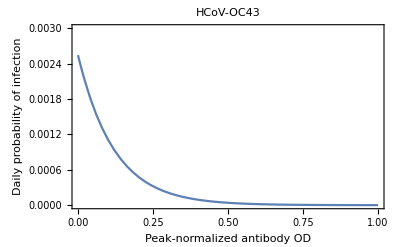

```mathematica
Plot[1/(1+Exp[-(a+b*x)]) /. maxlloc43lrdaily[[2]],{x,0,1},
PlotRange->{0,.003},
PlotLabel->"HCoV-OC43",
Frame->{{True,False},{True,False}},
FrameLabel->{"Peak-normalized antibody OD", "Daily probability of infection"}
]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["HCoV-OC43_PrInf-by-nOD_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Plot[1/(1+Exp[-(a+b*x)]) /. maxlloc43lrdaily[[2]],{x,0,1},
PlotRange->{0,.003},
PlotLabel->"HCoV-OC43",
Frame->{{True,False},{True,False}},
FrameLabel->{"Peak-normalized antibody OD", "Daily probability of infection"}
]
]
```

HCoV-OC43_PrInf-by-nOD_21Jan2021.pdf

### OC43 Waning of Antibody OD

```mathematica
oc43data;
```

```mathematica
Table[
{aod,
Table[
If [
Or[
oc43data[[index-1, 8]]≥aod≥oc43data[[index, 8]],
oc43data[[index-1, 8]]≤aod≤oc43data[[index, 8]]],
If[
And[
oc43data[[index, 9]]≠"NA",
StringMatchQ[oc43data[[index-1, 5]],"F*E"]
],
oc43data[[index, 9]], 
Nothing],
Nothing],
{index, 2, lloc43length}
]
}
, {aod, 0,4, 0.05}];
```

```mathematica
oc43paddedmeanwaning=Table[
{aod,
Mean[
Table[
If [
Or[
oc43data[[index-1, 8]]≥aod≥oc43data[[index, 8]],
oc43data[[index-1, 8]]≤aod≤oc43data[[index, 8]]],
If[
And[
oc43data[[index, 9]]≠"NA",
StringMatchQ[oc43data[[index-1, 5]],"F*E"]
],
oc43data[[index, 9]], 
Nothing],
Nothing],
{index, 2, lloc43length}
]
]
}
, {aod, 0,2.9, 0.05}]
```

{{0.,Mean[{}]},{0.05,Mean[{}]},{0.1,-0.000642834},{0.15,-0.000221957},{0.2,-0.000103434},{0.25,-0.000239906},{0.3,-0.000323961},{0.35,-0.000689892},{0.4,-0.00099706},{0.45,-0.00110724},{0.5,-0.00154385},{0.55,-0.00153569},{0.6,-0.00225325},{0.65,-0.00466062},{0.7,-0.00530561},{0.75,-0.00530561},{0.8,-0.00717949},{0.85,-0.00717949},{0.9,-0.00725075},{0.95,-0.00725075},{1.,-0.00725075},{1.05,-0.00782162},{1.1,-0.0084271},{1.15,-0.0084271},{1.2,-0.0084271},{1.25,-0.0084271},{1.3,-0.0105345},{1.35,-0.0105345},{1.4,-0.0105345},{1.45,-0.0105345},{1.5,-0.0105345},{1.55,-0.0145172},{1.6,-0.0145172},{1.65,-0.0145172},{1.7,-0.0145172},{1.75,-0.0145172},{1.8,-0.02533},{1.85,-0.02533},{1.9,-0.02533},{1.95,-0.02533},{2.,-0.02533},{2.05,-0.02533},{2.1,-0.02533},{2.15,-0.02533},{2.2,-0.02533},{2.25,-0.02533},{2.3,-0.02533},{2.35,-0.02533},{2.4,-0.02533},{2.45,-0.02533},{2.5,-0.02533},{2.55,-0.02533},{2.6,-0.02533},{2.65,-0.02533},{2.7,-0.02533},{2.75,-0.02533},{2.8,-0.02533},{2.85,-0.02533},{2.9,-0.02533}}

```mathematica
oc43meanwaning=Drop[oc43paddedmeanwaning, 2]
```

{{0.1,-0.000642834},{0.15,-0.000221957},{0.2,-0.000103434},{0.25,-0.000239906},{0.3,-0.000323961},{0.35,-0.000689892},{0.4,-0.00099706},{0.45,-0.00110724},{0.5,-0.00154385},{0.55,-0.00153569},{0.6,-0.00225325},{0.65,-0.00466062},{0.7,-0.00530561},{0.75,-0.00530561},{0.8,-0.00717949},{0.85,-0.00717949},{0.9,-0.00725075},{0.95,-0.00725075},{1.,-0.00725075},{1.05,-0.00782162},{1.1,-0.0084271},{1.15,-0.0084271},{1.2,-0.0084271},{1.25,-0.0084271},{1.3,-0.0105345},{1.35,-0.0105345},{1.4,-0.0105345},{1.45,-0.0105345},{1.5,-0.0105345},{1.55,-0.0145172},{1.6,-0.0145172},{1.65,-0.0145172},{1.7,-0.0145172},{1.75,-0.0145172},{1.8,-0.02533},{1.85,-0.02533},{1.9,-0.02533},{1.95,-0.02533},{2.,-0.02533},{2.05,-0.02533},{2.1,-0.02533},{2.15,-0.02533},{2.2,-0.02533},{2.25,-0.02533},{2.3,-0.02533},{2.35,-0.02533},{2.4,-0.02533},{2.45,-0.02533},{2.5,-0.02533},{2.55,-0.02533},{2.6,-0.02533},{2.65,-0.02533},{2.7,-0.02533},{2.75,-0.02533},{2.8,-0.02533},{2.85,-0.02533},{2.9,-0.02533}}

```mathematica
oc43meanwaning=Prepend[oc43meanwaning, {0.05, 0}]
```

{{0.05,0},{0.1,-0.000642834},{0.15,-0.000221957},{0.2,-0.000103434},{0.25,-0.000239906},{0.3,-0.000323961},{0.35,-0.000689892},{0.4,-0.00099706},{0.45,-0.00110724},{0.5,-0.00154385},{0.55,-0.00153569},{0.6,-0.00225325},{0.65,-0.00466062},{0.7,-0.00530561},{0.75,-0.00530561},{0.8,-0.00717949},{0.85,-0.00717949},{0.9,-0.00725075},{0.95,-0.00725075},{1.,-0.00725075},{1.05,-0.00782162},{1.1,-0.0084271},{1.15,-0.0084271},{1.2,-0.0084271},{1.25,-0.0084271},{1.3,-0.0105345},{1.35,-0.0105345},{1.4,-0.0105345},{1.45,-0.0105345},{1.5,-0.0105345},{1.55,-0.0145172},{1.6,-0.0145172},{1.65,-0.0145172},{1.7,-0.0145172},{1.75,-0.0145172},{1.8,-0.02533},{1.85,-0.02533},{1.9,-0.02533},{1.95,-0.02533},{2.,-0.02533},{2.05,-0.02533},{2.1,-0.02533},{2.15,-0.02533},{2.2,-0.02533},{2.25,-0.02533},{2.3,-0.02533},{2.35,-0.02533},{2.4,-0.02533},{2.45,-0.02533},{2.5,-0.02533},{2.55,-0.02533},{2.6,-0.02533},{2.65,-0.02533},{2.7,-0.02533},{2.75,-0.02533},{2.8,-0.02533},{2.85,-0.02533},{2.9,-0.02533}}

```mathematica
oc43meanwaning=Prepend[oc43meanwaning, {0, 0}]
```

{{0,0},{0.05,0},{0.1,-0.000642834},{0.15,-0.000221957},{0.2,-0.000103434},{0.25,-0.000239906},{0.3,-0.000323961},{0.35,-0.000689892},{0.4,-0.00099706},{0.45,-0.00110724},{0.5,-0.00154385},{0.55,-0.00153569},{0.6,-0.00225325},{0.65,-0.00466062},{0.7,-0.00530561},{0.75,-0.00530561},{0.8,-0.00717949},{0.85,-0.00717949},{0.9,-0.00725075},{0.95,-0.00725075},{1.,-0.00725075},{1.05,-0.00782162},{1.1,-0.0084271},{1.15,-0.0084271},{1.2,-0.0084271},{1.25,-0.0084271},{1.3,-0.0105345},{1.35,-0.0105345},{1.4,-0.0105345},{1.45,-0.0105345},{1.5,-0.0105345},{1.55,-0.0145172},{1.6,-0.0145172},{1.65,-0.0145172},{1.7,-0.0145172},{1.75,-0.0145172},{1.8,-0.02533},{1.85,-0.02533},{1.9,-0.02533},{1.95,-0.02533},{2.,-0.02533},{2.05,-0.02533},{2.1,-0.02533},{2.15,-0.02533},{2.2,-0.02533},{2.25,-0.02533},{2.3,-0.02533},{2.35,-0.02533},{2.4,-0.02533},{2.45,-0.02533},{2.5,-0.02533},{2.55,-0.02533},{2.6,-0.02533},{2.65,-0.02533},{2.7,-0.02533},{2.75,-0.02533},{2.8,-0.02533},{2.85,-0.02533},{2.9,-0.02533}}

```mathematica
TableForm[oc43meanwaning]
```

0 | 0
0.05 | 0
0.1 | -0.000642834
0.15 | -0.000221957
0.2 | -0.000103434
0.25 | -0.000239906
0.3 | -0.000323961
0.35 | -0.000689892
0.4 | -0.00099706
0.45 | -0.00110724
0.5 | -0.00154385
0.55 | -0.00153569
0.6 | -0.00225325
0.65 | -0.00466062
0.7 | -0.00530561
0.75 | -0.00530561
0.8 | -0.00717949
0.85 | -0.00717949
0.9 | -0.00725075
0.95 | -0.00725075
1. | -0.00725075
1.05 | -0.00782162
1.1 | -0.0084271
1.15 | -0.0084271
1.2 | -0.0084271
1.25 | -0.0084271
1.3 | -0.0105345
1.35 | -0.0105345
1.4 | -0.0105345
1.45 | -0.0105345
1.5 | -0.0105345
1.55 | -0.0145172
1.6 | -0.0145172
1.65 | -0.0145172
1.7 | -0.0145172
1.75 | -0.0145172
1.8 | -0.02533
1.85 | -0.02533
1.9 | -0.02533
1.95 | -0.02533
2. | -0.02533
2.05 | -0.02533
2.1 | -0.02533
2.15 | -0.02533
2.2 | -0.02533
2.25 | -0.02533
2.3 | -0.02533
2.35 | -0.02533
2.4 | -0.02533
2.45 | -0.02533
2.5 | -0.02533
2.55 | -0.02533
2.6 | -0.02533
2.65 | -0.02533
2.7 | -0.02533
2.75 | -0.02533
2.8 | -0.02533
2.85 | -0.02533
2.9 | -0.02533

```mathematica
oc43antibodywaning=Interpolation[oc43meanwaning]
```

InterpolatingFunction[…]

```mathematica
oc43antibodytimecourse={1};
day=1;
While[oc43antibodytimecourse[[day]]>0.1,
oc43antibodytimecourse=Append[oc43antibodytimecourse, oc43antibodytimecourse[[day]]+oc43antibodywaning[oc43antibodytimecourse[[day]]]];
Increment[day]
]
```

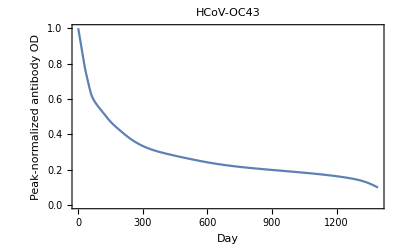

```mathematica
ListLinePlot[oc43antibodytimecourse, PlotRange->{0, 1},
PlotLabel->"HCoV-OC43",
Frame->{{True,False},{True,False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
```

```mathematica
Export["OC43-Antibody-Time-Course.csv",oc43antibodytimecourse]
```

OC43-Antibody-Time-Course.csv

```mathematica
Length[oc43antibodytimecourse]
```

1392

```mathematica
Take[oc43antibodytimecourse,-1]
```

{0.0994986}

This estimate for the baseline S IgG antibody level for HCoV-OC43 of .0996472 goes into the the ancestral and descendent states analysis of the baselines for the zoonotic coronaviruses.

```mathematica
oc43lsfunc=Sum[(oc43antibodytimecourse[[index]]-(baseline+ (1-baseline)*Exp[-lambda*index]))^2, {index, 1, Length[oc43antibodytimecourse]}]
```

(0.0994986-baseline-(1-baseline) ⅇ^(-1392 lambda))^2+(0.100141-baseline-(1-baseline) ⅇ^(-1391 lambda))^2+1389+(1-baseline-(1-baseline) ⅇ^-lambda)^2
 |  |  |  |

```mathematica
FindMinimum[{oc43lsfunc,0<baseline≤0.09964716261621707, lambda >0},{{baseline, 0.1}, {lambda, 0.005}}]
```

{7.36258,{baseline→0.0996472,lambda→0.00420199}}

This estimate of lambda for HCoV-OC43 of 0.00420101 goes into the the ancestral and descendent states analysis.

```mathematica
oc43halflife=Log[2]/ lambda /.lambda->0.0042019881376685235
```

164.957

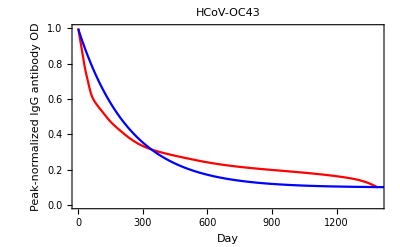

```mathematica
Show[
ListLinePlot[oc43antibodytimecourse,
PlotStyle->Red,
PlotRange-> {0,1}
],
Plot[baseline+(1-baseline)*Exp[-lambda days]/.{baseline->0.09964716261621707,lambda->0.00420101},{days,1,3208},
PlotStyle->Blue,
PlotRange->{0,1}
],
PlotLabel->"HCoV-OC43",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Peak-normalized IgG antibody OD"}]
```

```mathematica
Length[oc43antibodytimecourse]
```

1392

```mathematica
oc43antibodytimecourseplusexp=oc43antibodytimecourse;
day=Length[oc43antibodytimecourse];
While[day<4393,
Increment[day];
AppendTo[oc43antibodytimecourseplusexp, 0.09964716261621707+(oc43antibodytimecourseplusexp[[day-1]]- 0.09964716261621707)*Exp[-0.00420101]]
]
```

```mathematica
oc43antibodytimecourseplusexp
```

{1,0.992749,0.98552,0.978303,0.971089,0.963871,0.956645,0.949406,0.942156,0.934903,0.927649,0.920394,0.913139,0.905884,0.898631,0.891382,0.884142,0.876913,0.869695,0.862488,0.855292,0.848106,0.840915,0.833684,0.826418,0.819128,0.811833,0.804557,0.797329,0.790236,0.783392,0.776812,0.770496,0.764436,0.758616,0.753017,0.747614,0.742331,0.737084,0.731857,0.726635,0.72141,0.716172,0.710917,0.705644,0.700353,0.695048,0.689759,0.684497,0.67927,0.674089,0.668967,0.663915,0.658945,0.654072,0.649308,0.644677,0.640249,0.636028,0.632011,0.628193,0.624569,0.62113,0.617865,0.614767,0.611823,0.609025,0.606362,0.603824,0.601402,0.599089,0.596861,0.594692,0.592578,0.590515,0.588498,0.586525,0.584591,0.582694,0.580832,0.579001,0.577199,0.575425,0.573675,0.571949,0.570245,0.568561,0.566895,0.565246,0.563613,0.561994,0.560389,0.558796,0.557214,0.555642,0.554079,0.552525,0.550979,0.549439,0.547905,0.546376,0.54485,0.543327,0.541807,0.540288,0.538771,0.537255,0.53574,0.534225,0.532709,0.531194,0.529677,0.528159,0.52664,0.52512,0.523598,0.522074,0.520548,0.519021,0.517491,0.515959,0.514426,0.51289,0.511353,0.509814,0.508273,0.506731,0.505189,0.503645,0.502101,0.500556,0.499012,0.497475,0.495949,0.494435,0.492932,0.49144,0.489961,0.488494,0.487039,0.485597,0.484167,0.48275,0.481346,0.479954,0.478575,0.477209,0.475855,0.474514,0.473186,0.47187,0.470566,0.469275,0.467996,0.466729,0.465474,0.46423,0.462998,0.461778,0.460569,0.45937,0.458183,0.457006,0.45584,0.454683,0.453537,0.452401,0.451274,0.450156,0.449048,0.447944,0.446844,0.445748,0.444656,0.443566,0.442481,0.441398,0.440318,0.439242,0.438168,0.437097,0.436028,0.434962,0.433898,0.432837,0.431778,0.430721,0.429666,0.428614,0.427563,0.426514,0.425468,0.424423,0.42338,0.422338,0.421299,0.420261,0.419225,0.418191,0.417159,0.416128,0.415099,0.414072,0.413047,0.412023,0.411001,0.409982,0.408963,0.407947,0.406933,0.405921,0.404911,0.403902,0.402897,0.401893,0.400891,0.399892,0.398895,0.397904,0.396916,0.395934,0.394956,0.393984,0.393016,0.392053,0.391095,0.390142,0.389195,0.388252,0.387315,0.386382,0.385455,0.384533,0.383617,0.382705,0.381799,0.380898,0.380003,0.379113,0.378228,0.377349,0.376475,0.375606,0.374743,0.373885,0.373033,0.372185,0.371344,0.370508,0.369677,0.368851,0.368031,0.367217,0.366407,0.365603,0.364805,0.364012,0.363224,0.362441,0.361664,0.360892,0.360126,0.359364,0.358608,0.357857,0.357112,0.356371,0.355636,0.354906,0.354181,0.353462,0.352747,0.352037,0.351333,0.350634,0.349939,0.34925,0.348566,0.347887,0.347214,0.346546,0.345883,0.345226,0.344574,0.343927,0.343285,0.342649,0.342017,0.34139,0.340769,0.340152,0.33954,0.338934,0.338332,0.337734,0.337142,0.336554,0.335971,0.335392,0.334819,0.334249,0.333684,0.333124,0.332568,0.332016,0.331469,0.330926,0.330387,0.329853,0.329323,0.328796,0.328274,0.327756,0.327242,0.326732,0.326226,0.325723,0.325225,0.32473,0.324239,0.323752,0.323269,0.322789,0.322312,0.32184,0.32137,0.320905,0.320442,0.319984,0.319528,0.319076,0.318627,0.318182,0.317739,0.3173,0.316864,0.316431,0.316002,0.315575,0.315151,0.314731,0.314313,0.313898,0.313486,0.313077,0.312671,0.312267,0.311866,0.311468,0.311073,0.31068,0.31029,0.309903,0.309518,0.309136,0.308756,0.308379,0.308004,0.307631,0.307261,0.306894,0.306528,0.306165,0.305805,0.305446,0.30509,0.304736,0.304384,0.304034,0.303687,0.303341,0.302998,0.302656,0.302317,0.30198,0.301644,0.301311,0.30098,0.30065,0.300322,0.299997,0.299673,0.29935,0.299028,0.298707,0.298388,0.298069,0.297751,0.297435,0.297119,0.296804,0.296491,0.296178,0.295866,0.295555,0.295245,0.294936,0.294628,0.294321,0.294014,0.293709,0.293404,0.2931,0.292797,0.292494,0.292193,0.291892,0.291592,0.291293,0.290994,0.290697,0.2904,0.290103,0.289808,0.289513,0.289219,0.288925,0.288633,0.288341,0.288049,0.287758,0.287468,0.287179,0.28689,0.286602,0.286314,0.286027,0.28574,0.285455,0.285169,0.284885,0.2846,0.284317,0.284034,0.283751,0.283469,0.283188,0.282907,0.282627,0.282347,0.282068,0.281789,0.281511,0.281233,0.280955,0.280679,0.280402,0.280126,0.279851,0.279576,0.279301,0.279027,0.278754,0.27848,0.278208,0.277935,0.277663,0.277392,0.277121,0.27685,0.27658,0.27631,0.276041,0.275771,0.275503,0.275234,0.274967,0.274699,0.274432,0.274165,0.273899,0.273633,0.273367,0.273101,0.272836,0.272572,0.272307,0.272043,0.27178,0.271517,0.271254,0.270991,0.270729,0.270467,0.270205,0.269944,0.269683,0.269422,0.269162,0.268901,0.268642,0.268382,0.268123,0.267864,0.267605,0.267347,0.267089,0.266831,0.266574,0.266317,0.26606,0.265803,0.265547,0.265291,0.265035,0.26478,0.264525,0.26427,0.264015,0.263761,0.263507,0.263253,0.262999,0.262746,0.262493,0.26224,0.261988,0.261736,0.261484,0.261232,0.26098,0.260729,0.260478,0.260228,0.259977,0.259727,0.259477,0.259227,0.258978,0.258729,0.25848,0.258231,0.257983,0.257734,0.257487,0.257239,0.256991,0.256744,0.256497,0.256251,0.256004,0.255758,0.255512,0.255266,0.255021,0.254776,0.254531,0.254286,0.254042,0.253798,0.253554,0.25331,0.253067,0.252823,0.252581,0.252338,0.252096,0.251853,0.251611,0.25137,0.251128,0.250887,0.250646,0.250406,0.250165,0.249925,0.249686,0.249447,0.249209,0.248971,0.248735,0.248499,0.248264,0.24803,0.247796,0.247563,0.247331,0.2471,0.24687,0.24664,0.246411,0.246183,0.245955,0.245729,0.245503,0.245278,0.245053,0.244829,0.244606,0.244384,0.244163,0.243942,0.243722,0.243503,0.243284,0.243066,0.242849,0.242633,0.242417,0.242202,0.241988,0.241774,0.241561,0.241349,0.241138,0.240927,0.240717,0.240507,0.240299,0.240091,0.239884,0.239677,0.239471,0.239266,0.239061,0.238857,0.238654,0.238452,0.23825,0.238049,0.237848,0.237648,0.237449,0.237251,0.237053,0.236856,0.236659,0.236463,0.236268,0.236073,0.235879,0.235686,0.235493,0.235301,0.23511,0.234919,0.234729,0.234539,0.23435,0.234162,0.233974,0.233787,0.2336,0.233414,0.233229,0.233044,0.23286,0.232677,0.232494,0.232311,0.23213,0.231948,0.231768,0.231588,0.231408,0.231229,0.231051,0.230873,0.230696,0.23052,0.230344,0.230168,0.229993,0.229819,0.229645,0.229472,0.229299,0.229127,0.228955,0.228784,0.228613,0.228443,0.228274,0.228105,0.227936,0.227769,0.227601,0.227434,0.227268,0.227102,0.226937,0.226772,0.226607,0.226443,0.22628,0.226117,0.225955,0.225793,0.225632,0.225471,0.22531,0.22515,0.224991,0.224832,0.224673,0.224515,0.224358,0.224201,0.224044,0.223888,0.223732,0.223577,0.223422,0.223268,0.223114,0.22296,0.222807,0.222655,0.222503,0.222351,0.2222,0.222049,0.221899,0.221749,0.221599,0.22145,0.221301,0.221153,0.221005,0.220858,0.220711,0.220564,0.220418,0.220272,0.220127,0.219982,0.219837,0.219693,0.219549,0.219406,0.219263,0.21912,0.218978,0.218836,0.218695,0.218553,0.218413,0.218272,0.218132,0.217993,0.217854,0.217715,0.217576,0.217438,0.2173,0.217163,0.217026,0.216889,0.216753,0.216617,0.216481,0.216346,0.216211,0.216076,0.215942,0.215808,0.215675,0.215541,0.215408,0.215276,0.215144,0.215012,0.21488,0.214749,0.214618,0.214487,0.214357,0.214227,0.214097,0.213968,0.213839,0.21371,0.213581,0.213453,0.213325,0.213198,0.21307,0.212943,0.212817,0.21269,0.212564,0.212438,0.212313,0.212188,0.212063,0.211938,0.211814,0.21169,0.211566,0.211442,0.211319,0.211196,0.211073,0.210951,0.210829,0.210707,0.210585,0.210464,0.210342,0.210222,0.210101,0.209981,0.20986,0.209741,0.209621,0.209502,0.209382,0.209264,0.209145,0.209026,0.208908,0.20879,0.208673,0.208555,0.208438,0.208321,0.208204,0.208088,0.207972,0.207855,0.20774,0.207624,0.207509,0.207393,0.207278,0.207164,0.207049,0.206935,0.206821,0.206707,0.206593,0.20648,0.206366,0.206253,0.206141,0.206028,0.205915,0.205803,0.205691,0.205579,0.205468,0.205356,0.205245,0.205134,0.205023,0.204912,0.204802,0.204691,0.204581,0.204471,0.204361,0.204252,0.204142,0.204033,0.203924,0.203815,0.203706,0.203598,0.203489,0.203381,0.203273,0.203165,0.203057,0.20295,0.202842,0.202735,0.202628,0.202521,0.202414,0.202307,0.202201,0.202095,0.201989,0.201882,0.201777,0.201671,0.201565,0.20146,0.201355,0.201249,0.201144,0.201039,0.200935,0.20083,0.200726,0.200621,0.200517,0.200413,0.200309,0.200205,0.200102,0.199998,0.199895,0.199791,0.199688,0.199585,0.199481,0.199378,0.199275,0.199172,0.199068,0.198965,0.198862,0.198759,0.198656,0.198553,0.19845,0.198347,0.198244,0.198141,0.198038,0.197935,0.197832,0.197729,0.197626,0.197523,0.19742,0.197317,0.197214,0.197111,0.197008,0.196906,0.196803,0.1967,0.196597,0.196494,0.196391,0.196288,0.196185,0.196082,0.19598,0.195877,0.195774,0.195671,0.195568,0.195465,0.195362,0.195259,0.195156,0.195053,0.19495,0.194847,0.194744,0.194641,0.194538,0.194435,0.194331,0.194228,0.194125,0.194022,0.193919,0.193815,0.193712,0.193609,0.193505,0.193402,0.193298,0.193195,0.193091,0.192988,0.192884,0.192781,0.192677,0.192573,0.192469,0.192366,0.192262,0.192158,0.192054,0.19195,0.191846,0.191742,0.191638,0.191533,0.191429,0.191325,0.19122,0.191116,0.191011,0.190907,0.190802,0.190698,0.190593,0.190488,0.190383,0.190278,0.190173,0.190068,0.189963,0.189858,0.189752,0.189647,0.189541,0.189436,0.18933,0.189224,0.189119,0.189013,0.188907,0.188801,0.188695,0.188588,0.188482,0.188376,0.188269,0.188163,0.188056,0.187949,0.187842,0.187735,0.187628,0.187521,0.187414,0.187306,0.187199,0.187091,0.186983,0.186876,0.186768,0.18666,0.186551,0.186443,0.186335,0.186226,0.186118,0.186009,0.1859,0.185791,0.185682,0.185573,0.185463,0.185354,0.185244,0.185134,0.185024,0.184914,0.184804,0.184694,0.184584,0.184473,0.184362,0.184251,0.18414,0.184029,0.183918,0.183806,0.183695,0.183583,0.183471,0.183359,0.183247,0.183134,0.183022,0.182909,0.182796,0.182683,0.18257,0.182457,0.182343,0.182229,0.182115,0.182001,0.181887,0.181773,0.181658,0.181543,0.181428,0.181313,0.181198,0.181082,0.180967,0.180851,0.180734,0.180618,0.180502,0.180385,0.180268,0.180151,0.180034,0.179916,0.179798,0.17968,0.179562,0.179444,0.179325,0.179206,0.179087,0.178968,0.178849,0.178729,0.178609,0.178489,0.178368,0.178248,0.178127,0.178006,0.177884,0.177763,0.177641,0.177519,0.177396,0.177274,0.177151,0.177028,0.176905,0.176781,0.176657,0.176533,0.176408,0.176284,0.176159,0.176034,0.175908,0.175782,0.175656,0.17553,0.175403,0.175276,0.175149,0.175022,0.174894,0.174766,0.174637,0.174509,0.17438,0.17425,0.174121,0.173991,0.17386,0.17373,0.173599,0.173468,0.173336,0.173204,0.173072,0.172939,0.172806,0.172673,0.17254,0.172406,0.172271,0.172137,0.172002,0.171866,0.171731,0.171595,0.171458,0.171321,0.171184,0.171047,0.170909,0.17077,0.170632,0.170492,0.170353,0.170213,0.170073,0.169932,0.169791,0.169649,0.169507,0.169365,0.169222,0.169079,0.168935,0.168791,0.168647,0.168502,0.168357,0.168211,0.168064,0.167918,0.167771,0.167623,0.167475,0.167326,0.167177,0.167028,0.166878,0.166727,0.166576,0.166425,0.166273,0.16612,0.165967,0.165814,0.16566,0.165505,0.16535,0.165194,0.165038,0.164882,0.164724,0.164567,0.164408,0.164249,0.16409,0.16393,0.163769,0.163608,0.163446,0.163284,0.163121,0.162958,0.162794,0.162629,0.162463,0.162298,0.162131,0.161964,0.161796,0.161627,0.161458,0.161288,0.161118,0.160947,0.160775,0.160602,0.160429,0.160255,0.160081,0.159906,0.15973,0.159553,0.159376,0.159198,0.159019,0.158839,0.158659,0.158478,0.158296,0.158113,0.15793,0.157745,0.15756,0.157375,0.157188,0.157001,0.156812,0.156623,0.156433,0.156243,0.156051,0.155859,0.155665,0.155471,0.155276,0.15508,0.154883,0.154685,0.154486,0.154287,0.154086,0.153885,0.153682,0.153478,0.153274,0.153069,0.152862,0.152655,0.152446,0.152237,0.152026,0.151814,0.151602,0.151388,0.151173,0.150957,0.15074,0.150522,0.150303,0.150083,0.149861,0.149638,0.149412,0.149184,0.148954,0.148722,0.148487,0.14825,0.14801,0.147768,0.147524,0.147277,0.147028,0.146776,0.146521,0.146264,0.146004,0.145741,0.145476,0.145208,0.144937,0.144664,0.144387,0.144108,0.143826,0.14354,0.143252,0.142961,0.142666,0.142369,0.142068,0.141765,0.141458,0.141147,0.140834,0.140517,0.140197,0.139873,0.139546,0.139216,0.138882,0.138544,0.138203,0.137859,0.13751,0.137158,0.136802,0.136443,0.136079,0.135712,0.135341,0.134966,0.134587,0.134204,0.133817,0.133426,0.133031,0.132631,0.132228,0.13182,0.131409,0.130992,0.130572,0.130147,0.129718,0.129285,0.128847,0.128405,0.127958,0.127507,0.127052,0.126592,0.126127,0.125658,0.125184,0.124706,0.124223,0.123736,0.123244,0.122748,0.122246,0.121741,0.12123,0.120716,0.120196,0.119672,0.119144,0.118611,0.118073,0.117532,0.116985,0.116434,0.115879,0.11532,0.114756,0.114188,0.113616,0.11304,0.11246,0.111876,0.111287,0.110695,0.1101,0.1095,0.108897,0.108291,0.107681,0.107068,0.106451,0.105832,0.105209,0.104584,0.103956,0.103326,0.102693,0.102058,0.101421,0.100782,0.100141,0.0994986,0.0994992,0.0994999,0.0995005,0.0995011,0.0995017,0.0995023,0.0995029,0.0995035,0.0995041,0.0995047,0.0995053,0.0995059,0.0995065,0.0995071,0.0995077,0.0995083,0.0995089,0.0995094,0.09951,0.0995106,0.0995112,0.0995117,0.0995123,0.0995129,0.0995134,0.099514,0.0995145,0.0995151,0.0995157,0.0995162,0.0995168,0.0995173,0.0995178,0.0995184,0.0995189,0.0995195,0.09952,0.0995205,0.0995211,0.0995216,0.0995221,0.0995226,0.0995232,0.0995237,0.0995242,0.0995247,0.0995252,0.0995257,0.0995263,0.0995268,0.0995273,0.0995278,0.0995283,0.0995288,0.0995293,0.0995298,0.0995302,0.0995307,0.0995312,0.0995317,0.0995322,0.0995327,0.0995332,0.0995336,0.0995341,0.0995346,0.0995351,0.0995355,0.099536,0.0995365,0.0995369,0.0995374,0.0995378,0.0995383,0.0995388,0.0995392,0.0995397,0.0995401,0.0995406,0.099541,0.0995415,0.0995419,0.0995423,0.0995428,0.0995432,0.0995437,0.0995441,0.0995445,0.099545,0.0995454,0.0995458,0.0995462,0.0995467,0.0995471,0.0995475,0.0995479,0.0995483,0.0995487,0.0995492,0.0995496,0.09955,0.0995504,0.0995508,0.0995512,0.0995516,0.099552,0.0995524,0.0995528,0.0995532,0.0995536,0.099554,0.0995544,0.0995548,0.0995551,0.0995555,0.0995559,0.0995563,0.0995567,0.0995571,0.0995574,0.0995578,0.0995582,0.0995586,0.0995589,0.0995593,0.0995597,0.09956,0.0995604,0.0995608,0.0995611,0.0995615,0.0995618,0.0995622,0.0995626,0.0995629,0.0995633,0.0995636,0.099564,0.0995643,0.0995647,0.099565,0.0995654,0.0995657,0.099566,0.0995664,0.0995667,0.0995671,0.0995674,0.0995677,0.0995681,0.0995684,0.0995687,0.099569,0.0995694,0.0995697,0.09957,0.0995704,0.0995707,0.099571,0.0995713,0.0995716,0.0995719,0.0995723,0.0995726,0.0995729,0.0995732,0.0995735,0.0995738,0.0995741,0.0995744,0.0995747,0.099575,0.0995753,0.0995756,0.0995759,0.0995762,0.0995765,0.0995768,0.0995771,0.0995774,0.0995777,0.099578,0.0995783,0.0995786,0.0995789,0.0995792,0.0995794,0.0995797,0.09958,0.0995803,0.0995806,0.0995809,0.0995811,0.0995814,0.0995817,0.099582,0.0995822,0.0995825,0.0995828,0.099583,0.0995833,0.0995836,0.0995838,0.0995841,0.0995844,0.0995846,0.0995849,0.0995852,0.0995854,0.0995857,0.0995859,0.0995862,0.0995865,0.0995867,0.099587,0.0995872,0.0995875,0.0995877,0.099588,0.0995882,0.0995885,0.0995887,0.099589,0.0995892,0.0995894,0.0995897,0.0995899,0.0995902,0.0995904,0.0995906,0.0995909,0.0995911,0.0995913,0.0995916,0.0995918,0.099592,0.0995923,0.0995925,0.0995927,0.099593,0.0995932,0.0995934,0.0995936,0.0995939,0.0995941,0.0995943,0.0995945,0.0995948,0.099595,0.0995952,0.0995954,0.0995956,0.0995958,0.0995961,0.0995963,0.0995965,0.0995967,0.0995969,0.0995971,0.0995973,0.0995975,0.0995977,0.099598,0.0995982,0.0995984,0.0995986,0.0995988,0.099599,0.0995992,0.0995994,0.0995996,0.0995998,0.0996,0.0996002,0.0996004,0.0996006,0.0996008,0.099601,0.0996012,0.0996013,0.0996015,0.0996017,0.0996019,0.0996021,0.0996023,0.0996025,0.0996027,0.0996029,0.099603,0.0996032,0.0996034,0.0996036,0.0996038,0.099604,0.0996041,0.0996043,0.0996045,0.0996047,0.0996049,0.099605,0.0996052,0.0996054,0.0996056,0.0996057,0.0996059,0.0996061,0.0996063,0.0996064,0.0996066,0.0996068,0.0996069,0.0996071,0.0996073,0.0996074,0.0996076,0.0996078,0.0996079,0.0996081,0.0996083,0.0996084,0.0996086,0.0996088,0.0996089,0.0996091,0.0996092,0.0996094,0.0996096,0.0996097,0.0996099,0.09961,0.0996102,0.0996103,0.0996105,0.0996106,0.0996108,0.099611,0.0996111,0.0996113,0.0996114,0.0996116,0.0996117,0.0996119,0.099612,0.0996121,0.0996123,0.0996124,0.0996126,0.0996127,0.0996129,0.099613,0.0996132,0.0996133,0.0996134,0.0996136,0.0996137,0.0996139,0.099614,0.0996141,0.0996143,0.0996144,0.0996146,0.0996147,0.0996148,0.099615,0.0996151,0.0996152,0.0996154,0.0996155,0.0996156,0.0996158,0.0996159,0.099616,0.0996162,0.0996163,0.0996164,0.0996166,0.0996167,0.0996168,0.0996169,0.0996171,0.0996172,0.0996173,0.0996174,0.0996176,0.0996177,0.0996178,0.0996179,0.0996181,0.0996182,0.0996183,0.0996184,0.0996185,0.0996187,0.0996188,0.0996189,0.099619,0.0996191,0.0996193,0.0996194,0.0996195,0.0996196,0.0996197,0.0996198,0.0996199,0.0996201,0.0996202,0.0996203,0.0996204,0.0996205,0.0996206,0.0996207,0.0996208,0.099621,0.0996211,0.0996212,0.0996213,0.0996214,0.0996215,0.0996216,0.0996217,0.0996218,0.0996219,0.099622,0.0996221,0.0996222,0.0996224,0.0996225,0.0996226,0.0996227,0.0996228,0.0996229,0.099623,0.0996231,0.0996232,0.0996233,0.0996234,0.0996235,0.0996236,0.0996237,0.0996238,0.0996239,0.099624,0.0996241,0.0996242,0.0996243,0.0996244,0.0996244,0.0996245,0.0996246,0.0996247,0.0996248,0.0996249,0.099625,0.0996251,0.0996252,0.0996253,0.0996254,0.0996255,0.0996256,0.0996257,0.0996257,0.0996258,0.0996259,0.099626,0.0996261,0.0996262,0.0996263,0.0996264,0.0996265,0.0996265,0.0996266,0.0996267,0.0996268,0.0996269,0.099627,0.0996271,0.0996271,0.0996272,0.0996273,0.0996274,0.0996275,0.0996276,0.0996276,0.0996277,0.0996278,0.0996279,0.099628,0.099628,0.0996281,0.0996282,0.0996283,0.0996284,0.0996284,0.0996285,0.0996286,0.0996287,0.0996288,0.0996288,0.0996289,0.099629,0.0996291,0.0996291,0.0996292,0.0996293,0.0996294,0.0996294,0.0996295,0.0996296,0.0996297,0.0996297,0.0996298,0.0996299,0.0996299,0.09963,0.0996301,0.0996302,0.0996302,0.0996303,0.0996304,0.0996304,0.0996305,0.0996306,0.0996307,0.0996307,0.0996308,0.0996309,0.0996309,0.099631,0.0996311,0.0996311,0.0996312,0.0996313,0.0996313,0.0996314,0.0996315,0.0996315,0.0996316,0.0996317,0.0996317,0.0996318,0.0996319,0.0996319,0.099632,0.099632,0.0996321,0.0996322,0.0996322,0.0996323,0.0996324,0.0996324,0.0996325,0.0996325,0.0996326,0.0996327,0.0996327,0.0996328,0.0996329,0.0996329,0.099633,0.099633,0.0996331,0.0996332,0.0996332,0.0996333,0.0996333,0.0996334,0.0996334,0.0996335,0.0996336,0.0996336,0.0996337,0.0996337,0.0996338,0.0996338,0.0996339,0.099634,0.099634,0.0996341,0.0996341,0.0996342,0.0996342,0.0996343,0.0996343,0.0996344,0.0996344,0.0996345,0.0996345,0.0996346,0.0996347,0.0996347,0.0996348,0.0996348,0.0996349,0.0996349,0.099635,0.099635,0.0996351,0.0996351,0.0996352,0.0996352,0.0996353,0.0996353,0.0996354,0.0996354,0.0996355,0.0996355,0.0996356,0.0996356,0.0996357,0.0996357,0.0996358,0.0996358,0.0996359,0.0996359,0.0996359,0.099636,0.099636,0.0996361,0.0996361,0.0996362,0.0996362,0.0996363,0.0996363,0.0996364,0.0996364,0.0996365,0.0996365,0.0996365,0.0996366,0.0996366,0.0996367,0.0996367,0.0996368,0.0996368,0.0996369,0.0996369,0.0996369,0.099637,0.099637,0.0996371,0.0996371,0.0996371,0.0996372,0.0996372,0.0996373,0.0996373,0.0996374,0.0996374,0.0996374,0.0996375,0.0996375,0.0996376,0.0996376,0.0996376,0.0996377,0.0996377,0.0996378,0.0996378,0.0996378,0.0996379,0.0996379,0.099638,0.099638,0.099638,0.0996381,0.0996381,0.0996381,0.0996382,0.0996382,0.0996383,0.0996383,0.0996383,0.0996384,0.0996384,0.0996384,0.0996385,0.0996385,0.0996386,0.0996386,0.0996386,0.0996387,0.0996387,0.0996387,0.0996388,0.0996388,0.0996388,0.0996389,0.0996389,0.0996389,0.099639,0.099639,0.099639,0.0996391,0.0996391,0.0996391,0.0996392,0.0996392,0.0996392,0.0996393,0.0996393,0.0996393,0.0996394,0.0996394,0.0996394,0.0996395,0.0996395,0.0996395,0.0996396,0.0996396,0.0996396,0.0996397,0.0996397,0.0996397,0.0996398,0.0996398,0.0996398,0.0996399,0.0996399,0.0996399,0.0996399,0.09964,0.09964,0.09964,0.0996401,0.0996401,0.0996401,0.0996402,0.0996402,0.0996402,0.0996402,0.0996403,0.0996403,0.0996403,0.0996404,0.0996404,0.0996404,0.0996404,0.0996405,0.0996405,0.0996405,0.0996406,0.0996406,0.0996406,0.0996406,0.0996407,0.0996407,0.0996407,0.0996407,0.0996408,0.0996408,0.0996408,0.0996409,0.0996409,0.0996409,0.0996409,0.099641,0.099641,0.099641,0.099641,0.0996411,0.0996411,0.0996411,0.0996411,0.0996412,0.0996412,0.0996412,0.0996412,0.0996413,0.0996413,0.0996413,0.0996413,0.0996414,0.0996414,0.0996414,0.0996414,0.0996415,0.0996415,0.0996415,0.0996415,0.0996416,0.0996416,0.0996416,0.0996416,0.0996416,0.0996417,0.0996417,0.0996417,0.0996417,0.0996418,0.0996418,0.0996418,0.0996418,0.0996419,0.0996419,0.0996419,0.0996419,0.0996419,0.099642,0.099642,0.099642,0.099642,0.0996421,0.0996421,0.0996421,0.0996421,0.0996421,0.0996422,0.0996422,0.0996422,0.0996422,0.0996422,0.0996423,0.0996423,0.0996423,0.0996423,0.0996423,0.0996424,0.0996424,0.0996424,0.0996424,0.0996424,0.0996425,0.0996425,0.0996425,0.0996425,0.0996425,0.0996426,0.0996426,0.0996426,0.0996426,0.0996426,0.0996427,0.0996427,0.0996427,0.0996427,0.0996427,0.0996427,0.0996428,0.0996428,0.0996428,0.0996428,0.0996428,0.0996429,0.0996429,0.0996429,0.0996429,0.0996429,0.0996429,0.099643,0.099643,0.099643,0.099643,0.099643,0.0996431,0.0996431,0.0996431,0.0996431,0.0996431,0.0996431,0.0996432,0.0996432,0.0996432,0.0996432,0.0996432,0.0996432,0.0996433,0.0996433,0.0996433,0.0996433,0.0996433,0.0996433,0.0996434,0.0996434,0.0996434,0.0996434,0.0996434,0.0996434,0.0996434,0.0996435,0.0996435,0.0996435,0.0996435,0.0996435,0.0996435,0.0996436,0.0996436,0.0996436,0.0996436,0.0996436,0.0996436,0.0996436,0.0996437,0.0996437,0.0996437,0.0996437,0.0996437,0.0996437,0.0996437,0.0996438,0.0996438,0.0996438,0.0996438,0.0996438,0.0996438,0.0996438,0.0996439,0.0996439,0.0996439,0.0996439,0.0996439,0.0996439,0.0996439,0.099644,0.099644,0.099644,0.099644,0.099644,0.099644,0.099644,0.099644,0.0996441,0.0996441,0.0996441,0.0996441,0.0996441,0.0996441,0.0996441,0.0996442,0.0996442,0.0996442,0.0996442,0.0996442,0.0996442,0.0996442,0.0996442,0.0996443,0.0996443,0.0996443,0.0996443,0.0996443,0.0996443,0.0996443,0.0996443,0.0996443,0.0996444,0.0996444,0.0996444,0.0996444,0.0996444,0.0996444,0.0996444,0.0996444,0.0996445,0.0996445,0.0996445,0.0996445,0.0996445,0.0996445,0.0996445,0.0996445,0.0996445,0.0996446,0.0996446,0.0996446,0.0996446,0.0996446,0.0996446,0.0996446,0.0996446,0.0996446,0.0996446,0.0996447,0.0996447,0.0996447,0.0996447,0.0996447,0.0996447,0.0996447,0.0996447,0.0996447,0.0996448,0.0996448,0.0996448,0.0996448,0.0996448,0.0996448,0.0996448,0.0996448,0.0996448,0.0996448,0.0996449,0.0996449,0.0996449,0.0996449,0.0996449,0.0996449,0.0996449,0.0996449,0.0996449,0.0996449,0.0996449,0.099645,0.099645,0.099645,0.099645,0.099645,0.099645,0.099645,0.099645,0.099645,0.099645,0.099645,0.0996451,0.0996451,0.0996451,0.0996451,0.0996451,0.0996451,0.0996451,0.0996451,0.0996451,0.0996451,0.0996451,0.0996452,0.0996452,0.0996452,0.0996452,0.0996452,0.0996452,0.0996452,0.0996452,0.0996452,0.0996452,0.0996452,0.0996452,0.0996452,0.0996453,0.0996453,0.0996453,0.0996453,0.0996453,0.0996453,0.0996453,0.0996453,0.0996453,0.0996453,0.0996453,0.0996453,0.0996454,0.0996454,0.0996454,0.0996454,0.0996454,0.0996454,0.0996454,0.0996454,0.0996454,0.0996454,0.0996454,0.0996454,0.0996454,0.0996454,0.0996455,0.0996455,0.0996455,0.0996455,0.0996455,0.0996455,0.0996455,0.0996455,0.0996455,0.0996455,0.0996455,0.0996455,0.0996455,0.0996455,0.0996456,0.0996456,0.0996456,0.0996456,0.0996456,0.0996456,0.0996456,0.0996456,0.0996456,0.0996456,0.0996456,0.0996456,0.0996456,0.0996456,0.0996456,0.0996457,0.0996457,0.0996457,0.0996457,0.0996457,0.0996457,0.0996457,0.0996457,0.0996457,0.0996457,0.0996457,0.0996457,0.0996457,0.0996457,0.0996457,0.0996457,0.0996457,0.0996458,0.0996458,0.0996458,0.0996458,0.0996458,0.0996458,0.0996458,0.0996458,0.0996458,0.0996458,0.0996458,0.0996458,0.0996458,0.0996458,0.0996458,0.0996458,0.0996458,0.0996459,0.0996459,0.0996459,0.0996459,0.0996459,0.0996459,0.0996459,0.0996459,0.0996459,0.0996459,0.0996459,0.0996459,0.0996459,0.0996459,0.0996459,0.0996459,0.0996459,0.0996459,0.0996459,0.099646,0.099646,0.099646,0.099646,0.099646,0.099646,0.099646,0.099646,0.099646,0.099646,0.099646,0.099646,0.099646,0.099646,0.099646,0.099646,0.099646,0.099646,0.099646,0.099646,0.099646,0.0996461,0.0996461,0.0996461,0.0996461,0.0996461,0.0996461,0.0996461,0.0996461,0.0996461,0.0996461,0.0996461,0.0996461,0.0996461,0.0996461,0.0996461,0.0996461,0.0996461,0.0996461,0.0996461,0.0996461,0.0996461,0.0996461,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996462,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996463,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996464,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996465,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996466,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996467,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996468,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.0996469,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.099647,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996471,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472,0.0996472}

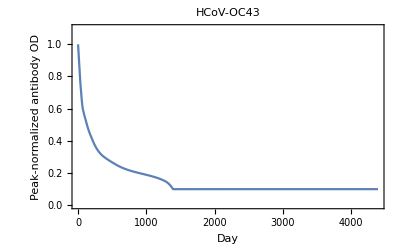

```mathematica
ListLinePlot[oc43antibodytimecourseplusexp,
PlotRange->{0, 1.1},
PlotLabel->"HCoV-OC43",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["HCoV-OC43_nOD-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[oc43antibodytimecourseplusexp, PlotRange->{0, 1.1}, PlotLabel->"HCoV-OC43", Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Peak-normalized antibody OD"}]
]
```

HCoV-OC43_nOD-by-Day_21Jan2021.pdf

```mathematica
lengthabtc=Length[oc43antibodytimecourse]
```

1392

```mathematica
oc43probnoreinfectiontimecourse={1};
day=1;
AppendTo[oc43probnoreinfectiontimecourse, 
oc43probnoreinfectiontimecourse[[day]]*(1-oc43probinfgivenaod[oc43antibodytimecourse[[day+1]]])
];

While[day<4393,
Increment[day];
AppendTo[oc43probnoreinfectiontimecourse, 
If[day<lengthabtc,
oc43probnoreinfectiontimecourse[[day]]*(1-oc43probinfgivenaod[oc43antibodytimecourse[[day+1]] ]),
oc43probnoreinfectiontimecourse[[day]]*(1-oc43probinfgivenaod[oc43antibodytimecourse[[lengthabtc]]])
]
]
];

oc43probnoreinfectiontimecourse
```

{1,0.999999,0.999999,0.999998,0.999997,0.999996,0.999995,0.999994,0.999993,0.999992,0.999991,0.99999,0.999988,0.999987,0.999986,0.999984,0.999982,0.999981,0.999979,0.999977,0.999975,0.999972,0.99997,0.999967,0.999965,0.999962,0.999959,0.999955,0.999952,0.999948,0.999945,0.99994,0.999936,0.999932,0.999927,0.999922,0.999917,0.999911,0.999906,0.9999,0.999894,0.999887,0.99988,0.999873,0.999866,0.999858,0.99985,0.999842,0.999833,0.999824,0.999815,0.999805,0.999794,0.999783,0.999772,0.99976,0.999748,0.999736,0.999723,0.999709,0.999695,0.999681,0.999666,0.999651,0.999635,0.999619,0.999603,0.999586,0.999569,0.999552,0.999534,0.999516,0.999497,0.999479,0.99946,0.99944,0.99942,0.9994,0.99938,0.999359,0.999338,0.999317,0.999296,0.999274,0.999251,0.999229,0.999206,0.999183,0.999159,0.999135,0.999111,0.999087,0.999062,0.999037,0.999012,0.998986,0.99896,0.998933,0.998906,0.998879,0.998852,0.998824,0.998796,0.998767,0.998738,0.998709,0.998679,0.998649,0.998619,0.998588,0.998557,0.998526,0.998494,0.998461,0.998429,0.998395,0.998362,0.998328,0.998293,0.998259,0.998223,0.998187,0.998151,0.998114,0.998077,0.99804,0.998002,0.997963,0.997924,0.997884,0.997844,0.997803,0.997762,0.997721,0.997678,0.997636,0.997592,0.997549,0.997504,0.997459,0.997414,0.997368,0.997321,0.997274,0.997227,0.997179,0.99713,0.997081,0.997031,0.996981,0.99693,0.996879,0.996827,0.996774,0.996721,0.996667,0.996613,0.996559,0.996503,0.996447,0.996391,0.996334,0.996277,0.996219,0.99616,0.996101,0.996041,0.995981,0.99592,0.995859,0.995797,0.995734,0.995671,0.995608,0.995543,0.995478,0.995413,0.995347,0.995281,0.995213,0.995146,0.995077,0.995009,0.994939,0.994869,0.994798,0.994727,0.994655,0.994582,0.994509,0.994435,0.99436,0.994285,0.994209,0.994133,0.994056,0.993978,0.9939,0.993821,0.993741,0.99366,0.993579,0.993497,0.993415,0.993332,0.993248,0.993163,0.993078,0.992992,0.992905,0.992817,0.992729,0.99264,0.99255,0.99246,0.992369,0.992277,0.992184,0.992091,0.991997,0.991902,0.991806,0.991709,0.991612,0.991514,0.991415,0.991316,0.991215,0.991114,0.991012,0.99091,0.990806,0.990702,0.990597,0.990491,0.990385,0.990277,0.990169,0.99006,0.98995,0.98984,0.989728,0.989616,0.989503,0.98939,0.989275,0.98916,0.989044,0.988927,0.988809,0.988691,0.988571,0.988451,0.98833,0.988209,0.988086,0.987963,0.987839,0.987714,0.987589,0.987462,0.987335,0.987207,0.987078,0.986949,0.986818,0.986687,0.986555,0.986422,0.986289,0.986155,0.98602,0.985884,0.985747,0.98561,0.985472,0.985333,0.985193,0.985053,0.984912,0.98477,0.984627,0.984483,0.984339,0.984194,0.984048,0.983902,0.983754,0.983606,0.983458,0.983308,0.983158,0.983007,0.982855,0.982703,0.98255,0.982396,0.982241,0.982086,0.98193,0.981773,0.981616,0.981458,0.981299,0.981139,0.980979,0.980818,0.980656,0.980494,0.980331,0.980167,0.980003,0.979838,0.979672,0.979505,0.979338,0.979171,0.979002,0.978833,0.978663,0.978493,0.978322,0.97815,0.977978,0.977805,0.977631,0.977457,0.977282,0.977106,0.97693,0.976753,0.976576,0.976397,0.976219,0.976039,0.975859,0.975679,0.975498,0.975316,0.975134,0.974951,0.974767,0.974583,0.974398,0.974213,0.974027,0.97384,0.973653,0.973465,0.973277,0.973088,0.972899,0.972708,0.972518,0.972327,0.972135,0.971943,0.97175,0.971556,0.971362,0.971168,0.970973,0.970777,0.970581,0.970384,0.970187,0.969989,0.969791,0.969592,0.969393,0.969193,0.968992,0.968791,0.96859,0.968388,0.968185,0.967982,0.967779,0.967575,0.96737,0.967165,0.966959,0.966753,0.966546,0.966339,0.966132,0.965923,0.965715,0.965506,0.965296,0.965086,0.964875,0.964664,0.964452,0.96424,0.964027,0.963814,0.963601,0.963386,0.963172,0.962957,0.962741,0.962525,0.962308,0.962091,0.961873,0.961655,0.961437,0.961218,0.960998,0.960778,0.960557,0.960336,0.960115,0.959893,0.95967,0.959447,0.959223,0.958999,0.958775,0.95855,0.958324,0.958098,0.957872,0.957645,0.957418,0.95719,0.956961,0.956732,0.956503,0.956273,0.956043,0.955812,0.95558,0.955349,0.955116,0.954884,0.95465,0.954416,0.954182,0.953947,0.953712,0.953477,0.95324,0.953004,0.952767,0.952529,0.952291,0.952052,0.951813,0.951573,0.951333,0.951093,0.950852,0.95061,0.950368,0.950126,0.949883,0.949639,0.949395,0.949151,0.948906,0.948661,0.948415,0.948168,0.947922,0.947674,0.947426,0.947178,0.946929,0.94668,0.94643,0.94618,0.945929,0.945678,0.945426,0.945174,0.944921,0.944668,0.944415,0.944161,0.943906,0.943651,0.943395,0.943139,0.942883,0.942626,0.942368,0.94211,0.941852,0.941593,0.941333,0.941073,0.940813,0.940552,0.94029,0.940029,0.939766,0.939503,0.93924,0.938976,0.938712,0.938447,0.938182,0.937916,0.93765,0.937383,0.937116,0.936848,0.93658,0.936311,0.936042,0.935772,0.935502,0.935231,0.93496,0.934688,0.934416,0.934143,0.93387,0.933597,0.933323,0.933048,0.932773,0.932497,0.932221,0.931945,0.931668,0.93139,0.931112,0.930834,0.930555,0.930275,0.929995,0.929715,0.929434,0.929152,0.92887,0.928588,0.928305,0.928021,0.927737,0.927453,0.927168,0.926883,0.926597,0.92631,0.926023,0.925736,0.925448,0.92516,0.924871,0.924582,0.924292,0.924001,0.923711,0.923419,0.923127,0.922835,0.922542,0.922249,0.921955,0.921661,0.921366,0.921071,0.920775,0.920479,0.920182,0.919885,0.919587,0.919289,0.91899,0.918691,0.918391,0.918091,0.917791,0.91749,0.917188,0.916886,0.916583,0.91628,0.915977,0.915673,0.915368,0.915063,0.914758,0.914452,0.914146,0.913839,0.913532,0.913224,0.912916,0.912608,0.912298,0.911989,0.911679,0.911369,0.911058,0.910746,0.910435,0.910122,0.90981,0.909497,0.909183,0.908869,0.908555,0.90824,0.907924,0.907609,0.907292,0.906976,0.906659,0.906341,0.906023,0.905705,0.905386,0.905067,0.904747,0.904427,0.904107,0.903786,0.903465,0.903143,0.902821,0.902498,0.902175,0.901852,0.901528,0.901204,0.900879,0.900554,0.900229,0.899903,0.899577,0.899251,0.898924,0.898596,0.898268,0.89794,0.897612,0.897283,0.896953,0.896623,0.896293,0.895963,0.895632,0.895301,0.894969,0.894637,0.894305,0.893972,0.893639,0.893305,0.892971,0.892637,0.892302,0.891967,0.891632,0.891296,0.89096,0.890623,0.890286,0.889949,0.889612,0.889274,0.888935,0.888597,0.888258,0.887918,0.887579,0.887238,0.886898,0.886557,0.886216,0.885875,0.885533,0.885191,0.884848,0.884506,0.884162,0.883819,0.883475,0.883131,0.882786,0.882442,0.882096,0.881751,0.881405,0.881059,0.880712,0.880366,0.880018,0.879671,0.879323,0.878975,0.878627,0.878278,0.877929,0.87758,0.87723,0.87688,0.87653,0.876179,0.875828,0.875477,0.875125,0.874774,0.874422,0.874069,0.873716,0.873363,0.87301,0.872656,0.872302,0.871948,0.871594,0.871239,0.870884,0.870528,0.870173,0.869817,0.869461,0.869104,0.868747,0.86839,0.868033,0.867675,0.867317,0.866959,0.8666,0.866242,0.865883,0.865523,0.865164,0.864804,0.864444,0.864083,0.863722,0.863362,0.863,0.862639,0.862277,0.861915,0.861553,0.86119,0.860827,0.860464,0.860101,0.859737,0.859374,0.85901,0.858645,0.858281,0.857916,0.857551,0.857185,0.85682,0.856454,0.856088,0.855721,0.855355,0.854988,0.854621,0.854254,0.853886,0.853518,0.85315,0.852782,0.852414,0.852045,0.851676,0.851307,0.850937,0.850568,0.850198,0.849827,0.849457,0.849087,0.848716,0.848345,0.847973,0.847602,0.84723,0.846858,0.846486,0.846114,0.845741,0.845368,0.844995,0.844622,0.844248,0.843875,0.843501,0.843127,0.842752,0.842378,0.842003,0.841628,0.841253,0.840878,0.840502,0.840126,0.83975,0.839374,0.838998,0.838621,0.838244,0.837867,0.83749,0.837112,0.836735,0.836357,0.835979,0.835601,0.835222,0.834844,0.834465,0.834086,0.833707,0.833327,0.832948,0.832568,0.832188,0.831808,0.831428,0.831047,0.830666,0.830285,0.829904,0.829523,0.829142,0.82876,0.828378,0.827996,0.827614,0.827232,0.826849,0.826466,0.826084,0.8257,0.825317,0.824934,0.82455,0.824166,0.823782,0.823398,0.823014,0.82263,0.822245,0.82186,0.821475,0.82109,0.820705,0.820319,0.819934,0.819548,0.819162,0.818776,0.818389,0.818003,0.817616,0.817229,0.816842,0.816455,0.816068,0.81568,0.815293,0.814905,0.814517,0.814129,0.813741,0.813352,0.812964,0.812575,0.812186,0.811797,0.811408,0.811019,0.810629,0.81024,0.80985,0.80946,0.80907,0.80868,0.808289,0.807899,0.807508,0.807117,0.806726,0.806335,0.805944,0.805552,0.805161,0.804769,0.804377,0.803985,0.803593,0.803201,0.802808,0.802416,0.802023,0.80163,0.801237,0.800844,0.800451,0.800057,0.799664,0.79927,0.798876,0.798482,0.798088,0.797694,0.797299,0.796905,0.79651,0.796115,0.79572,0.795325,0.79493,0.794534,0.794139,0.793743,0.793347,0.792951,0.792555,0.792159,0.791762,0.791366,0.790969,0.790572,0.790175,0.789778,0.789381,0.788984,0.788586,0.788188,0.787791,0.787393,0.786995,0.786596,0.786198,0.7858,0.785401,0.785002,0.784603,0.784204,0.783805,0.783406,0.783006,0.782607,0.782207,0.781807,0.781407,0.781007,0.780607,0.780206,0.779806,0.779405,0.779004,0.778603,0.778202,0.777801,0.777399,0.776998,0.776596,0.776194,0.775793,0.77539,0.774988,0.774586,0.774183,0.773781,0.773378,0.772975,0.772572,0.772169,0.771766,0.771362,0.770959,0.770555,0.770151,0.769747,0.769343,0.768939,0.768534,0.76813,0.767725,0.76732,0.766915,0.76651,0.766105,0.765699,0.765294,0.764888,0.764482,0.764076,0.76367,0.763264,0.762858,0.762451,0.762044,0.761638,0.761231,0.760824,0.760416,0.760009,0.759601,0.759194,0.758786,0.758378,0.75797,0.757562,0.757153,0.756745,0.756336,0.755927,0.755518,0.755109,0.7547,0.754291,0.753881,0.753472,0.753062,0.752652,0.752242,0.751831,0.751421,0.751011,0.7506,0.750189,0.749778,0.749367,0.748956,0.748544,0.748133,0.747721,0.747309,0.746897,0.746485,0.746073,0.74566,0.745247,0.744835,0.744422,0.744009,0.743595,0.743182,0.742769,0.742355,0.741941,0.741527,0.741113,0.740699,0.740284,0.73987,0.739455,0.73904,0.738625,0.73821,0.737794,0.737379,0.736963,0.736547,0.736131,0.735715,0.735298,0.734882,0.734465,0.734048,0.733631,0.733214,0.732797,0.732379,0.731962,0.731544,0.731126,0.730708,0.730289,0.729871,0.729452,0.729033,0.728614,0.728195,0.727776,0.727356,0.726937,0.726517,0.726097,0.725677,0.725256,0.724836,0.724415,0.723994,0.723573,0.723152,0.72273,0.722309,0.721887,0.721465,0.721043,0.720621,0.720198,0.719776,0.719353,0.71893,0.718506,0.718083,0.717659,0.717236,0.716812,0.716387,0.715963,0.715539,0.715114,0.714689,0.714264,0.713838,0.713413,0.712987,0.712561,0.712135,0.711709,0.711282,0.710856,0.710429,0.710002,0.709574,0.709147,0.708719,0.708291,0.707863,0.707435,0.707006,0.706578,0.706149,0.70572,0.70529,0.704861,0.704431,0.704001,0.703571,0.70314,0.70271,0.702279,0.701848,0.701416,0.700985,0.700553,0.700121,0.699689,0.699256,0.698824,0.698391,0.697958,0.697524,0.697091,0.696657,0.696223,0.695788,0.695354,0.694919,0.694484,0.694049,0.693613,0.693178,0.692742,0.692305,0.691869,0.691432,0.690995,0.690558,0.69012,0.689683,0.689245,0.688806,0.688368,0.687929,0.68749,0.687051,0.686611,0.686171,0.685731,0.685291,0.68485,0.684409,0.683968,0.683526,0.683084,0.682642,0.6822,0.681757,0.681314,0.680871,0.680428,0.679984,0.67954,0.679095,0.678651,0.678206,0.67776,0.677315,0.676869,0.676423,0.675976,0.675529,0.675082,0.674635,0.674187,0.673739,0.67329,0.672841,0.672392,0.671943,0.671493,0.671043,0.670593,0.670142,0.669691,0.669239,0.668788,0.668335,0.667883,0.66743,0.666977,0.666523,0.666069,0.665615,0.665161,0.664705,0.66425,0.663794,0.663338,0.662882,0.662425,0.661967,0.66151,0.661052,0.660593,0.660134,0.659675,0.659216,0.658755,0.658295,0.657834,0.657373,0.656911,0.656449,0.655986,0.655523,0.65506,0.654596,0.654132,0.653667,0.653202,0.652736,0.65227,0.651803,0.651336,0.650869,0.650401,0.649933,0.649464,0.648994,0.648525,0.648054,0.647583,0.647112,0.64664,0.646168,0.645695,0.645222,0.644748,0.644273,0.643798,0.643323,0.642847,0.64237,0.641893,0.641416,0.640937,0.640458,0.639979,0.639499,0.639018,0.638537,0.638055,0.637572,0.637089,0.636605,0.63612,0.635635,0.635149,0.634662,0.634174,0.633686,0.633197,0.632707,0.632217,0.631725,0.631233,0.63074,0.630246,0.629752,0.629256,0.62876,0.628263,0.627764,0.627265,0.626765,0.626264,0.625762,0.62526,0.624756,0.624251,0.623745,0.623238,0.62273,0.622221,0.621711,0.6212,0.620687,0.620174,0.619659,0.619143,0.618626,0.618108,0.617589,0.617068,0.616546,0.616023,0.615498,0.614972,0.614445,0.613917,0.613387,0.612855,0.612322,0.611788,0.611252,0.610715,0.610176,0.609636,0.609094,0.608551,0.608006,0.607459,0.606911,0.606361,0.605809,0.605256,0.6047,0.604143,0.603585,0.603024,0.602462,0.601897,0.601331,0.600763,0.600193,0.599621,0.599046,0.59847,0.597892,0.597312,0.59673,0.596145,0.595558,0.59497,0.594378,0.593785,0.59319,0.592592,0.591992,0.591389,0.590784,0.590177,0.589567,0.588955,0.588341,0.587723,0.587104,0.586482,0.585857,0.58523,0.5846,0.583968,0.583333,0.582695,0.582055,0.581411,0.580766,0.580117,0.579469,0.578822,0.578176,0.57753,0.576885,0.576241,0.575598,0.574955,0.574313,0.573672,0.573031,0.572391,0.571752,0.571114,0.570476,0.569839,0.569202,0.568567,0.567932,0.567298,0.566664,0.566032,0.5654,0.564768,0.564137,0.563508,0.562878,0.56225,0.561622,0.560995,0.560368,0.559743,0.559118,0.558493,0.55787,0.557247,0.556624,0.556003,0.555382,0.554762,0.554142,0.553524,0.552905,0.552288,0.551671,0.551055,0.55044,0.549825,0.549211,0.548598,0.547985,0.547374,0.546762,0.546152,0.545542,0.544933,0.544324,0.543716,0.543109,0.542503,0.541897,0.541292,0.540687,0.540084,0.539481,0.538878,0.538276,0.537675,0.537075,0.536475,0.535876,0.535278,0.53468,0.534083,0.533487,0.532891,0.532296,0.531701,0.531108,0.530515,0.529922,0.52933,0.528739,0.528149,0.527559,0.52697,0.526382,0.525794,0.525207,0.52462,0.524034,0.523449,0.522865,0.522281,0.521698,0.521115,0.520533,0.519952,0.519371,0.518791,0.518212,0.517633,0.517055,0.516478,0.515901,0.515325,0.51475,0.514175,0.513601,0.513027,0.512454,0.511882,0.511311,0.51074,0.510169,0.5096,0.509031,0.508462,0.507894,0.507327,0.506761,0.506195,0.50563,0.505065,0.504501,0.503938,0.503375,0.502813,0.502251,0.501691,0.50113,0.500571,0.500012,0.499453,0.498896,0.498339,0.497782,0.497226,0.496671,0.496116,0.495562,0.495009,0.494456,0.493904,0.493353,0.492802,0.492251,0.491702,0.491153,0.490604,0.490056,0.489509,0.488963,0.488417,0.487871,0.487326,0.486782,0.486239,0.485696,0.485153,0.484612,0.48407,0.48353,0.48299,0.482451,0.481912,0.481374,0.480836,0.480299,0.479763,0.479227,0.478692,0.478158,0.477624,0.47709,0.476558,0.476025,0.475494,0.474963,0.474433,0.473903,0.473374,0.472845,0.472317,0.47179,0.471263,0.470736,0.470211,0.469686,0.469161,0.468637,0.468114,0.467591,0.467069,0.466548,0.466027,0.465506,0.464987,0.464467,0.463949,0.463431,0.462913,0.462396,0.46188,0.461364,0.460849,0.460334,0.45982,0.459307,0.458794,0.458282,0.45777,0.457259,0.456748,0.456238,0.455729,0.45522,0.454711,0.454204,0.453696,0.45319,0.452684,0.452178,0.451673,0.451169,0.450665,0.450162,0.449659,0.449157,0.448656,0.448155,0.447654,0.447154,0.446655,0.446156,0.445658,0.44516,0.444663,0.444167,0.443671,0.443175,0.44268,0.442186,0.441692,0.441199,0.440706,0.440214,0.439723,0.439232,0.438741,0.438251,0.437762,0.437273,0.436785,0.436297,0.43581,0.435323,0.434837,0.434352,0.433867,0.433382,0.432898,0.432415,0.431932,0.43145,0.430968,0.430487,0.430006,0.429526,0.429046,0.428567,0.428088,0.42761,0.427133,0.426656,0.426179,0.425704,0.425228,0.424753,0.424279,0.423805,0.423332,0.422859,0.422387,0.421915,0.421444,0.420974,0.420504,0.420034,0.419565,0.419097,0.418629,0.418161,0.417694,0.417228,0.416762,0.416296,0.415832,0.415367,0.414903,0.41444,0.413977,0.413515,0.413053,0.412592,0.412131,0.411671,0.411211,0.410752,0.410294,0.409835,0.409378,0.408921,0.408464,0.408008,0.407552,0.407097,0.406643,0.406189,0.405735,0.405282,0.404829,0.404377,0.403926,0.403475,0.403024,0.402574,0.402125,0.401676,0.401227,0.400779,0.400331,0.399884,0.399438,0.398992,0.398546,0.398101,0.397657,0.397213,0.396769,0.396326,0.395883,0.395441,0.395,0.394559,0.394118,0.393678,0.393238,0.392799,0.392361,0.391923,0.391485,0.391048,0.390611,0.390175,0.389739,0.389304,0.388869,0.388435,0.388001,0.387568,0.387135,0.386703,0.386271,0.38584,0.385409,0.384979,0.384549,0.384119,0.38369,0.383262,0.382834,0.382407,0.381979,0.381553,0.381127,0.380701,0.380276,0.379852,0.379427,0.379004,0.37858,0.378158,0.377735,0.377314,0.376892,0.376471,0.376051,0.375631,0.375212,0.374793,0.374374,0.373956,0.373539,0.373121,0.372705,0.372289,0.371873,0.371458,0.371043,0.370629,0.370215,0.369801,0.369388,0.368976,0.368564,0.368152,0.367741,0.367331,0.36692,0.366511,0.366101,0.365693,0.365284,0.364876,0.364469,0.364062,0.363655,0.363249,0.362844,0.362438,0.362034,0.361629,0.361226,0.360822,0.360419,0.360017,0.359615,0.359213,0.358812,0.358412,0.358011,0.357612,0.357212,0.356813,0.356415,0.356017,0.355619,0.355222,0.354826,0.354429,0.354034,0.353638,0.353243,0.352849,0.352455,0.352061,0.351668,0.351276,0.350883,0.350491,0.3501,0.349709,0.349319,0.348929,0.348539,0.34815,0.347761,0.347373,0.346985,0.346597,0.34621,0.345824,0.345437,0.345052,0.344666,0.344282,0.343897,0.343513,0.34313,0.342746,0.342364,0.341981,0.341599,0.341218,0.340837,0.340456,0.340076,0.339696,0.339317,0.338938,0.33856,0.338182,0.337804,0.337427,0.33705,0.336674,0.336298,0.335922,0.335547,0.335172,0.334798,0.334424,0.334051,0.333678,0.333305,0.332933,0.332561,0.33219,0.331819,0.331448,0.331078,0.330709,0.330339,0.32997,0.329602,0.329234,0.328866,0.328499,0.328132,0.327766,0.3274,0.327034,0.326669,0.326304,0.32594,0.325576,0.325212,0.324849,0.324486,0.324124,0.323762,0.323401,0.32304,0.322679,0.322319,0.321959,0.321599,0.32124,0.320881,0.320523,0.320165,0.319807,0.31945,0.319094,0.318737,0.318381,0.318026,0.317671,0.317316,0.316962,0.316608,0.316254,0.315901,0.315548,0.315196,0.314844,0.314492,0.314141,0.31379,0.31344,0.31309,0.31274,0.312391,0.312042,0.311694,0.311346,0.310998,0.310651,0.310304,0.309958,0.309611,0.309266,0.30892,0.308575,0.308231,0.307887,0.307543,0.307199,0.306856,0.306514,0.306171,0.30583,0.305488,0.305147,0.304806,0.304466,0.304126,0.303786,0.303447,0.303108,0.30277,0.302432,0.302094,0.301757,0.30142,0.301083,0.300747,0.300411,0.300076,0.29974,0.299406,0.299071,0.298737,0.298404,0.298071,0.297738,0.297405,0.297073,0.296742,0.29641,0.296079,0.295749,0.295418,0.295088,0.294759,0.29443,0.294101,0.293773,0.293445,0.293117,0.29279,0.292463,0.292136,0.29181,0.291484,0.291158,0.290833,0.290509,0.290184,0.28986,0.289536,0.289213,0.28889,0.288568,0.288245,0.287924,0.287602,0.287281,0.28696,0.28664,0.28632,0.286,0.28568,0.285361,0.285043,0.284724,0.284407,0.284089,0.283772,0.283455,0.283138,0.282822,0.282506,0.282191,0.281876,0.281561,0.281247,0.280933,0.280619,0.280306,0.279992,0.27968,0.279368,0.279056,0.278744,0.278433,0.278122,0.277811,0.277501,0.277191,0.276882,0.276572,0.276264,0.275955,0.275647,0.275339,0.275032,0.274725,0.274418,0.274111,0.273805,0.2735,0.273194,0.272889,0.272584,0.27228,0.271976,0.271672,0.271369,0.271066,0.270763,0.270461,0.270159,0.269857,0.269556,0.269255,0.268954,0.268654,0.268354,0.268054,0.267755,0.267456,0.267157,0.266859,0.266561,0.266263,0.265966,0.265669,0.265372,0.265076,0.26478,0.264484,0.264189,0.263894,0.263599,0.263305,0.263011,0.262717,0.262424,0.262131,0.261838,0.261546,0.261254,0.260962,0.26067,0.260379,0.260089,0.259798,0.259508,0.259218,0.258929,0.25864,0.258351,0.258062,0.257774,0.257486,0.257199,0.256912,0.256625,0.256338,0.256052,0.255766,0.25548,0.255195,0.25491,0.254626,0.254341,0.254057,0.253773,0.25349,0.253207,0.252924,0.252642,0.25236,0.252078,0.251796,0.251515,0.251234,0.250954,0.250674,0.250394,0.250114,0.249835,0.249556,0.249277,0.248999,0.248721,0.248443,0.248166,0.247889,0.247612,0.247335,0.247059,0.246783,0.246508,0.246232,0.245957,0.245683,0.245408,0.245134,0.244861,0.244587,0.244314,0.244041,0.243769,0.243497,0.243225,0.242953,0.242682,0.242411,0.24214,0.24187,0.2416,0.24133,0.24106,0.240791,0.240522,0.240254,0.239985,0.239717,0.23945,0.239182,0.238915,0.238648,0.238382,0.238116,0.23785,0.237584,0.237319,0.237054,0.236789,0.236525,0.236261,0.235997,0.235733,0.23547,0.235207,0.234945,0.234682,0.23442,0.234158,0.233897,0.233636,0.233375,0.233114,0.232854,0.232594,0.232334,0.232075,0.231816,0.231557,0.231298,0.23104,0.230782,0.230524,0.230267,0.23001,0.229753,0.229496,0.22924,0.228984,0.228728,0.228473,0.228218,0.227963,0.227708,0.227454,0.2272,0.226946,0.226693,0.22644,0.226187,0.225934,0.225682,0.22543,0.225178,0.224927,0.224676,0.224425,0.224174,0.223924,0.223674,0.223424,0.223175,0.222925,0.222677,0.222428,0.22218,0.221931,0.221684,0.221436,0.221189,0.220942,0.220695,0.220449,0.220202,0.219957,0.219711,0.219466,0.219221,0.218976,0.218731,0.218487,0.218243,0.217999,0.217756,0.217513,0.21727,0.217027,0.216785,0.216543,0.216301,0.216059,0.215818,0.215577,0.215336,0.215096,0.214856,0.214616,0.214376,0.214137,0.213898,0.213659,0.21342,0.213182,0.212944,0.212706,0.212469,0.212231,0.211994,0.211758,0.211521,0.211285,0.211049,0.210813,0.210578,0.210343,0.210108,0.209873,0.209639,0.209405,0.209171,0.208938,0.208704,0.208471,0.208238,0.208006,0.207774,0.207542,0.20731,0.207078,0.206847,0.206616,0.206385,0.206155,0.205925,0.205695,0.205465,0.205236,0.205006,0.204778,0.204549,0.20432,0.204092,0.203864,0.203637,0.203409,0.203182,0.202955,0.202729,0.202502,0.202276,0.20205,0.201825,0.201599,0.201374,0.201149,0.200925,0.2007,0.200476,0.200252,0.200029,0.199805,0.199582,0.199359,0.199137,0.198914,0.198692,0.19847,0.198249,0.198027,0.197806,0.197585,0.197365,0.197144,0.196924,0.196704,0.196485,0.196265,0.196046,0.195827,0.195609,0.19539,0.195172,0.194954,0.194736,0.194519,0.194302,0.194085,0.193868,0.193651,0.193435,0.193219,0.193003,0.192788,0.192573,0.192358,0.192143,0.191928,0.191714,0.1915,0.191286,0.191072,0.190859,0.190646,0.190433,0.19022,0.190008,0.189796,0.189584,0.189372,0.189161,0.18895,0.188739,0.188528,0.188317,0.188107,0.187897,0.187687,0.187478,0.187268,0.187059,0.18685,0.186642,0.186433,0.186225,0.186017,0.185809,0.185602,0.185395,0.185188,0.184981,0.184774,0.184568,0.184362,0.184156,0.18395,0.183745,0.18354,0.183335,0.18313,0.182925,0.182721,0.182517,0.182313,0.18211,0.181906,0.181703,0.1815,0.181298,0.181095,0.180893,0.180691,0.180489,0.180288,0.180086,0.179885,0.179684,0.179484,0.179283,0.179083,0.178883,0.178683,0.178484,0.178285,0.178086,0.177887,0.177688,0.17749,0.177291,0.177093,0.176896,0.176698,0.176501,0.176304,0.176107,0.17591,0.175714,0.175518,0.175322,0.175126,0.17493,0.174735,0.17454,0.174345,0.17415,0.173956,0.173762,0.173567,0.173374,0.17318,0.172987,0.172794,0.172601,0.172408,0.172215,0.172023,0.171831,0.171639,0.171447,0.171256,0.171065,0.170874,0.170683,0.170492,0.170302,0.170112,0.169922,0.169732,0.169542,0.169353,0.169164,0.168975,0.168786,0.168598,0.16841,0.168222,0.168034,0.167846,0.167659,0.167472,0.167285,0.167098,0.166911,0.166725,0.166539,0.166353,0.166167,0.165981,0.165796,0.165611,0.165426,0.165241,0.165057,0.164872,0.164688,0.164504,0.164321,0.164137,0.163954,0.163771,0.163588,0.163405,0.163223,0.163041,0.162858,0.162677,0.162495,0.162314,0.162132,0.161951,0.16177,0.16159,0.161409,0.161229,0.161049,0.160869,0.16069,0.16051,0.160331,0.160152,0.159973,0.159794,0.159616,0.159438,0.15926,0.159082,0.158904,0.158727,0.158549,0.158372,0.158196,0.158019,0.157842,0.157666,0.15749,0.157314,0.157139,0.156963,0.156788,0.156613,0.156438,0.156263,0.156089,0.155914,0.15574,0.155566,0.155393,0.155219,0.155046,0.154873,0.1547,0.154527,0.154355,0.154182,0.15401,0.153838,0.153666,0.153495,0.153323,0.153152,0.152981,0.15281,0.15264,0.152469,0.152299,0.152129,0.151959,0.151789,0.15162,0.15145,0.151281,0.151112,0.150944,0.150775,0.150607,0.150439,0.150271,0.150103,0.149935,0.149768,0.1496,0.149433,0.149267,0.1491,0.148933,0.148767,0.148601,0.148435,0.148269,0.148104,0.147938,0.147773,0.147608,0.147443,0.147279,0.147114,0.14695,0.146786,0.146622,0.146458,0.146295,0.146131,0.145968,0.145805,0.145642,0.14548,0.145317,0.145155,0.144993,0.144831,0.144669,0.144508,0.144346,0.144185,0.144024,0.143863,0.143703,0.143542,0.143382,0.143222,0.143062,0.142902,0.142743,0.142583,0.142424,0.142265,0.142106,0.141947,0.141789,0.14163,0.141472,0.141314,0.141157,0.140999,0.140841,0.140684,0.140527,0.14037,0.140213,0.140057,0.1399,0.139744,0.139588,0.139432,0.139277,0.139121,0.138966,0.138811,0.138656,0.138501,0.138346,0.138192,0.138037,0.137883,0.137729,0.137575,0.137422,0.137268,0.137115,0.136962,0.136809,0.136656,0.136504,0.136351,0.136199,0.136047,0.135895,0.135743,0.135592,0.13544,0.135289,0.135138,0.134987,0.134836,0.134686,0.134535,0.134385,0.134235,0.134085,0.133935,0.133786,0.133636,0.133487,0.133338,0.133189,0.133041,0.132892,0.132744,0.132595,0.132447,0.132299,0.132152,0.132004,0.131857,0.131709,0.131562,0.131415,0.131269,0.131122,0.130976,0.130829,0.130683,0.130537,0.130392,0.130246,0.130101,0.129955,0.12981,0.129665,0.12952,0.129376,0.129231,0.129087,0.128943,0.128799,0.128655,0.128511,0.128368,0.128225,0.128081,0.127938,0.127796,0.127653,0.12751,0.127368,0.127226,0.127084,0.126942,0.1268,0.126658,0.126517,0.126376,0.126235,0.126094,0.125953,0.125812,0.125672,0.125531,0.125391,0.125251,0.125111,0.124972,0.124832,0.124693,0.124553,0.124414,0.124275,0.124137,0.123998,0.123859,0.123721,0.123583,0.123445,0.123307,0.123169,0.123032,0.122895,0.122757,0.12262,0.122483,0.122347,0.12221,0.122073,0.121937,0.121801,0.121665,0.121529,0.121393,0.121258,0.121122,0.120987,0.120852,0.120717,0.120582,0.120448,0.120313,0.120179,0.120045,0.119911,0.119777,0.119643,0.119509,0.119376,0.119243,0.119109,0.118976,0.118844,0.118711,0.118578,0.118446,0.118314,0.118182,0.11805,0.117918,0.117786,0.117655,0.117523,0.117392,0.117261,0.11713,0.116999,0.116868,0.116738,0.116608,0.116477,0.116347,0.116217,0.116088,0.115958,0.115829,0.115699,0.11557,0.115441,0.115312,0.115183,0.115055,0.114926,0.114798,0.11467,0.114542,0.114414,0.114286,0.114158,0.114031,0.113903,0.113776,0.113649,0.113522,0.113396,0.113269,0.113142,0.113016,0.11289,0.112764,0.112638,0.112512,0.112387,0.112261,0.112136,0.11201,0.111885,0.11176,0.111636,0.111511,0.111386,0.111262,0.111138,0.111014,0.11089,0.110766,0.110642,0.110519,0.110395,0.110272,0.110149,0.110026,0.109903,0.10978,0.109658,0.109535,0.109413,0.109291,0.109169,0.109047,0.108925,0.108803,0.108682,0.108561,0.108439,0.108318,0.108197,0.108077,0.107956,0.107835,0.107715,0.107595,0.107474,0.107354,0.107235,0.107115,0.106995,0.106876,0.106756,0.106637,0.106518,0.106399,0.10628,0.106162,0.106043,0.105925,0.105806,0.105688,0.10557,0.105452,0.105335,0.105217,0.105099,0.104982,0.104865,0.104748,0.104631,0.104514,0.104397,0.104281,0.104164,0.104048,0.103932,0.103816,0.1037,0.103584,0.103468,0.103353,0.103237,0.103122,0.103007,0.102892,0.102777,0.102662,0.102548,0.102433,0.102319,0.102204,0.10209,0.101976,0.101862,0.101749,0.101635,0.101522,0.101408,0.101295,0.101182,0.101069,0.100956,0.100843,0.100731,0.100618,0.100506,0.100394,0.100282,0.10017,0.100058,0.099946,0.0998344,0.0997229,0.0996115,0.0995003,0.0993892,0.0992782,0.0991673,0.0990566,0.098946,0.0988355,0.0987251,0.0986149,0.0985048,0.0983948,0.0982849,0.0981752,0.0980655,0.097956,0.0978466,0.0977374,0.0976282,0.0975192,0.0974103,0.0973016,0.0971929,0.0970844,0.096976,0.0968677,0.0967595,0.0966515,0.0965435,0.0964357,0.096328,0.0962205,0.096113,0.0960057,0.0958985,0.0957914,0.0956844,0.0955776,0.0954709,0.0953643,0.0952578,0.0951514,0.0950452,0.094939,0.094833,0.0947271,0.0946213,0.0945157,0.0944101,0.0943047,0.0941994,0.0940942,0.0939891,0.0938842,0.0937794,0.0936746,0.09357,0.0934655,0.0933612,0.0932569,0.0931528,0.0930488,0.0929449,0.0928411,0.0927374,0.0926338,0.0925304,0.0924271,0.0923239,0.0922208,0.0921178,0.0920149,0.0919122,0.0918096,0.091707,0.0916046,0.0915023,0.0914002,0.0912981,0.0911961,0.0910943,0.0909926,0.090891,0.0907895,0.0906881,0.0905868,0.0904857,0.0903846,0.0902837,0.0901829,0.0900822,0.0899816,0.0898811,0.0897808,0.0896805,0.0895804,0.0894803,0.0893804,0.0892806,0.0891809,0.0890813,0.0889819,0.0888825,0.0887832,0.0886841,0.0885851,0.0884862,0.0883873,0.0882886,0.0881901,0.0880916,0.0879932,0.087895,0.0877968,0.0876988,0.0876008,0.087503,0.0874053,0.0873077,0.0872102,0.0871128,0.0870156,0.0869184,0.0868213,0.0867244,0.0866275,0.0865308,0.0864342,0.0863377,0.0862413,0.0861449,0.0860488,0.0859527,0.0858567,0.0857608,0.0856651,0.0855694,0.0854738,0.0853784,0.0852831,0.0851878,0.0850927,0.0849977,0.0849028,0.084808,0.0847133,0.0846187,0.0845242,0.0844298,0.0843355,0.0842413,0.0841473,0.0840533,0.0839594,0.0838657,0.083772,0.0836785,0.0835851,0.0834917,0.0833985,0.0833054,0.0832123,0.0831194,0.0830266,0.0829339,0.0828413,0.0827488,0.0826564,0.0825641,0.0824719,0.0823798,0.0822878,0.0821959,0.0821041,0.0820124,0.0819209,0.0818294,0.081738,0.0816467,0.0815556,0.0814645,0.0813735,0.0812827,0.0811919,0.0811012,0.0810107,0.0809202,0.0808298,0.0807396,0.0806494,0.0805594,0.0804694,0.0803796,0.0802898,0.0802001,0.0801106,0.0800211,0.0799318,0.0798425,0.0797534,0.0796643,0.0795754,0.0794865,0.0793977,0.0793091,0.0792205,0.079132,0.0790437,0.0789554,0.0788673,0.0787792,0.0786912,0.0786033,0.0785156,0.0784279,0.0783403,0.0782528,0.0781655,0.0780782,0.077991,0.0779039,0.0778169,0.07773,0.0776432,0.0775565,0.0774699,0.0773834,0.077297,0.0772107,0.0771245,0.0770383,0.0769523,0.0768664,0.0767806,0.0766948,0.0766092,0.0765236,0.0764382,0.0763528,0.0762676,0.0761824,0.0760973,0.0760124,0.0759275,0.0758427,0.075758,0.0756734,0.0755889,0.0755045,0.0754202,0.075336,0.0752518,0.0751678,0.0750839,0.075,0.0749163,0.0748326,0.0747491,0.0746656,0.0745822,0.0744989,0.0744157,0.0743326,0.0742496,0.0741667,0.0740839,0.0740012,0.0739186,0.073836,0.0737536,0.0736712,0.0735889,0.0735068,0.0734247,0.0733427,0.0732608,0.073179,0.0730973,0.0730156,0.0729341,0.0728527,0.0727713,0.0726901,0.0726089,0.0725278,0.0724468,0.0723659,0.0722851,0.0722044,0.0721238,0.0720432,0.0719628,0.0718824,0.0718022,0.071722,0.0716419,0.0715619,0.071482,0.0714022,0.0713224,0.0712428,0.0711632,0.0710838,0.0710044,0.0709251,0.0708459,0.0707668,0.0706878,0.0706088,0.07053,0.0704512,0.0703726,0.070294,0.0702155,0.0701371,0.0700588,0.0699805,0.0699024,0.0698243,0.0697464,0.0696685,0.0695907,0.069513,0.0694353,0.0693578,0.0692804,0.069203,0.0691257,0.0690485,0.0689714,0.0688944,0.0688175,0.0687406,0.0686639,0.0685872,0.0685106,0.0684341,0.0683577,0.0682814,0.0682051,0.068129,0.0680529,0.0679769,0.067901,0.0678252,0.0677494,0.0676738,0.0675982,0.0675227,0.0674473,0.067372,0.0672968,0.0672216,0.0671466,0.0670716,0.0669967,0.0669219,0.0668471,0.0667725,0.0666979,0.0666235,0.0665491,0.0664747,0.0664005,0.0663264,0.0662523,0.0661783,0.0661044,0.0660306,0.0659569,0.0658832,0.0658097,0.0657362,0.0656628,0.0655894,0.0655162,0.065443,0.06537,0.065297,0.0652241,0.0651512,0.0650785,0.0650058,0.0649332,0.0648607,0.0647883,0.0647159,0.0646437,0.0645715,0.0644994,0.0644274,0.0643554,0.0642835,0.0642118,0.0641401,0.0640684,0.0639969,0.0639254,0.0638541,0.0637827,0.0637115,0.0636404,0.0635693,0.0634983,0.0634274,0.0633566,0.0632859,0.0632152,0.0631446,0.0630741,0.0630036,0.0629333,0.062863,0.0627928,0.0627227,0.0626527,0.0625827,0.0625128,0.062443,0.0623733,0.0623036,0.0622341,0.0621646,0.0620952,0.0620258,0.0619566,0.0618874,0.0618183,0.0617492,0.0616803,0.0616114,0.0615426,0.0614739,0.0614052,0.0613367,0.0612682,0.0611998,0.0611314,0.0610632,0.060995,0.0609269,0.0608588,0.0607909,0.060723,0.0606552,0.0605875,0.0605198,0.0604522,0.0603847,0.0603173,0.0602499,0.0601827,0.0601154,0.0600483,0.0599813,0.0599143,0.0598474,0.0597806,0.0597138,0.0596471,0.0595805,0.059514,0.0594475,0.0593811,0.0593148,0.0592486,0.0591824,0.0591164,0.0590503,0.0589844,0.0589185,0.0588527,0.058787,0.0587214,0.0586558,0.0585903,0.0585249,0.0584595,0.0583943,0.0583291,0.0582639,0.0581989,0.0581339,0.058069,0.0580041,0.0579393,0.0578746,0.05781,0.0577455,0.057681,0.0576166,0.0575522,0.057488,0.0574238,0.0573596,0.0572956,0.0572316,0.0571677,0.0571039,0.0570401,0.0569764,0.0569128,0.0568492,0.0567858,0.0567223,0.056659,0.0565957,0.0565325,0.0564694,0.0564064,0.0563434,0.0562805,0.0562176,0.0561548,0.0560921,0.0560295,0.0559669,0.0559044,0.055842,0.0557796,0.0557174,0.0556551,0.055593,0.0555309,0.0554689,0.055407,0.0553451,0.0552833,0.0552216,0.0551599,0.0550983,0.0550368,0.0549753,0.0549139,0.0548526,0.0547914,0.0547302,0.0546691,0.054608,0.054547,0.0544861,0.0544253,0.0543645,0.0543038,0.0542432,0.0541826,0.0541221,0.0540617,0.0540013,0.053941,0.0538808,0.0538206,0.0537605,0.0537005,0.0536405,0.0535806,0.0535208,0.053461,0.0534013,0.0533417,0.0532821,0.0532226,0.0531632,0.0531038,0.0530445,0.0529853,0.0529261,0.052867,0.052808,0.052749,0.0526901,0.0526313,0.0525725,0.0525138,0.0524552,0.0523966,0.0523381,0.0522796,0.0522212,0.0521629,0.0521047,0.0520465,0.0519884,0.0519303,0.0518723,0.0518144,0.0517566,0.0516988,0.051641,0.0515834,0.0515258,0.0514682,0.0514108,0.0513534,0.051296,0.0512387,0.0511815,0.0511244,0.0510673,0.0510102,0.0509533,0.0508964,0.0508396,0.0507828,0.0507261,0.0506694,0.0506129,0.0505563,0.0504999,0.0504435,0.0503872,0.0503309,0.0502747,0.0502186,0.0501625,0.0501065,0.0500505,0.0499946,0.0499388,0.049883,0.0498273,0.0497717,0.0497161,0.0496606,0.0496051,0.0495498,0.0494944,0.0494392,0.0493839,0.0493288,0.0492737,0.0492187,0.0491637,0.0491088,0.049054,0.0489992,0.0489445,0.0488899,0.0488353,0.0487807,0.0487263,0.0486718,0.0486175,0.0485632,0.048509,0.0484548,0.0484007,0.0483467,0.0482927,0.0482387,0.0481849,0.0481311,0.0480773,0.0480236,0.04797,0.0479164,0.0478629,0.0478095,0.0477561,0.0477028,0.0476495,0.0475963,0.0475432,0.0474901,0.047437,0.0473841,0.0473312,0.0472783,0.0472255,0.0471728,0.0471201,0.0470675,0.0470149,0.0469624,0.04691,0.0468576,0.0468053,0.046753,0.0467008,0.0466487,0.0465966,0.0465445,0.0464926,0.0464406,0.0463888,0.046337,0.0462852,0.0462336,0.0461819,0.0461304,0.0460788,0.0460274,0.045976,0.0459247,0.0458734,0.0458221,0.045771,0.0457199,0.0456688,0.0456178,0.0455669,0.045516,0.0454652,0.0454144,0.0453637,0.045313,0.0452624,0.0452119,0.0451614,0.045111,0.0450606,0.0450103,0.04496,0.0449098,0.0448597,0.0448096,0.0447595,0.0447096,0.0446596,0.0446098,0.04456,0.0445102,0.0444605,0.0444108,0.0443613,0.0443117,0.0442622,0.0442128,0.0441634,0.0441141,0.0440649,0.0440157,0.0439665,0.0439174,0.0438684,0.0438194,0.0437705,0.0437216,0.0436728,0.043624,0.0435753,0.0435266,0.043478,0.0434295,0.043381,0.0433325,0.0432841,0.0432358,0.0431875,0.0431393,0.0430911,0.043043,0.0429949,0.0429469,0.042899,0.0428511,0.0428032,0.0427554,0.0427077,0.04266,0.0426124,0.0425648,0.0425172,0.0424698,0.0424223,0.042375,0.0423277,0.0422804,0.0422332,0.042186,0.0421389,0.0420919,0.0420449,0.0419979,0.041951,0.0419042,0.0418574,0.0418106,0.0417639,0.0417173,0.0416707,0.0416242,0.0415777,0.0415313,0.0414849,0.0414386,0.0413923,0.0413461,0.0412999,0.0412538,0.0412077,0.0411617,0.0411158,0.0410698,0.041024,0.0409782,0.0409324,0.0408867,0.040841,0.0407954,0.0407499,0.0407044,0.0406589,0.0406135,0.0405682,0.0405229,0.0404776,0.0404324,0.0403873,0.0403422,0.0402971,0.0402521,0.0402072,0.0401623,0.0401174,0.0400726,0.0400279,0.0399832,0.0399385,0.039894,0.0398494,0.0398049,0.0397605,0.0397161,0.0396717,0.0396274,0.0395832,0.039539,0.0394948,0.0394507,0.0394067,0.0393626,0.0393187,0.0392748,0.0392309,0.0391871,0.0391434,0.0390997,0.039056,0.0390124,0.0389688,0.0389253,0.0388818,0.0388384,0.0387951,0.0387517,0.0387085,0.0386652,0.0386221,0.0385789,0.0385359,0.0384928,0.0384498,0.0384069,0.038364,0.0383212,0.0382784,0.0382356,0.0381929,0.0381503,0.0381077,0.0380651,0.0380226,0.0379802,0.0379378,0.0378954,0.0378531,0.0378108,0.0377686,0.0377264,0.0376843,0.0376422,0.0376002,0.0375582,0.0375163,0.0374744,0.0374325,0.0373907,0.037349,0.0373073,0.0372656,0.037224,0.0371824,0.0371409,0.0370994,0.037058,0.0370166,0.0369753,0.036934,0.0368927,0.0368516,0.0368104,0.0367693,0.0367282,0.0366872,0.0366463,0.0366053,0.0365645,0.0365236,0.0364828,0.0364421,0.0364014,0.0363608,0.0363202,0.0362796,0.0362391,0.0361986,0.0361582,0.0361178,0.0360775,0.0360372,0.035997,0.0359568,0.0359166,0.0358765,0.0358365,0.0357964,0.0357565,0.0357165,0.0356767,0.0356368,0.035597,0.0355573,0.0355176,0.0354779,0.0354383,0.0353987,0.0353592,0.0353197,0.0352803,0.0352409,0.0352015,0.0351622,0.0351229,0.0350837,0.0350446,0.0350054,0.0349663,0.0349273,0.0348883,0.0348493,0.0348104,0.0347715,0.0347327,0.0346939,0.0346552,0.0346165,0.0345778,0.0345392,0.0345007,0.0344621,0.0344236,0.0343852,0.0343468,0.0343085,0.0342701,0.0342319,0.0341936,0.0341555,0.0341173,0.0340792,0.0340412,0.0340032,0.0339652,0.0339273,0.0338894,0.0338515,0.0338137,0.033776,0.0337383,0.0337006,0.033663,0.0336254,0.0335878,0.0335503,0.0335128,0.0334754,0.033438,0.0334007,0.0333634,0.0333262,0.0332889,0.0332518,0.0332146,0.0331775,0.0331405,0.0331035,0.0330665,0.0330296,0.0329927,0.0329559,0.0329191,0.0328823,0.0328456,0.0328089,0.0327723,0.0327357,0.0326991,0.0326626,0.0326262,0.0325897,0.0325533,0.032517,0.0324807,0.0324444,0.0324082,0.032372,0.0323358,0.0322997,0.0322637,0.0322276,0.0321916,0.0321557,0.0321198,0.0320839,0.0320481,0.0320123,0.0319766,0.0319409,0.0319052,0.0318696,0.031834,0.0317984,0.0317629,0.0317274,0.031692,0.0316566,0.0316213,0.031586,0.0315507,0.0315155,0.0314803,0.0314451,0.03141,0.0313749,0.0313399,0.0313049,0.0312699,0.031235,0.0312001,0.0311653,0.0311305,0.0310957,0.031061,0.0310263,0.0309917,0.0309571,0.0309225,0.030888,0.0308535,0.030819,0.0307846,0.0307503,0.0307159,0.0306816,0.0306474,0.0306131,0.0305789,0.0305448,0.0305107,0.0304766,0.0304426,0.0304086,0.0303746,0.0303407,0.0303068,0.030273,0.0302392,0.0302054,0.0301717,0.030138,0.0301044,0.0300707,0.0300372,0.0300036,0.0299701,0.0299367,0.0299032,0.0298698,0.0298365,0.0298032,0.0297699,0.0297366,0.0297034,0.0296703,0.0296371,0.029604,0.029571,0.029538,0.029505,0.029472,0.0294391,0.0294062,0.0293734,0.0293406,0.0293078,0.0292751,0.0292424,0.0292098,0.0291772,0.0291446,0.029112,0.0290795,0.029047,0.0290146,0.0289822,0.0289499,0.0289175,0.0288852,0.028853,0.0288208,0.0287886,0.0287564,0.0287243,0.0286922,0.0286602,0.0286282,0.0285962,0.0285643,0.0285324,0.0285005,0.0284687,0.0284369,0.0284052,0.0283735,0.0283418,0.0283101,0.0282785,0.0282469,0.0282154,0.0281839,0.0281524,0.028121,0.0280896,0.0280582,0.0280269,0.0279956,0.0279643,0.0279331,0.0279019,0.0278707,0.0278396,0.0278085,0.0277775,0.0277465,0.0277155,0.0276845,0.0276536,0.0276227,0.0275919,0.0275611,0.0275303,0.0274996,0.0274689,0.0274382,0.0274075,0.0273769,0.0273464,0.0273158,0.0272853,0.0272549,0.0272244,0.027194,0.0271637,0.0271333,0.027103,0.0270728,0.0270425,0.0270123,0.0269822,0.026952,0.0269219,0.0268919,0.0268619,0.0268319,0.0268019,0.026772,0.0267421,0.0267122,0.0266824,0.0266526,0.0266228,0.0265931,0.0265634,0.0265337,0.0265041,0.0264745,0.026445,0.0264154,0.0263859,0.0263565,0.026327,0.0262976,0.0262683,0.0262389,0.0262096,0.0261804,0.0261511,0.0261219,0.0260928,0.0260636,0.0260345,0.0260054,0.0259764,0.0259474,0.0259184,0.0258895,0.0258606,0.0258317,0.0258029,0.025774,0.0257453,0.0257165,0.0256878,0.0256591,0.0256305,0.0256018,0.0255732,0.0255447,0.0255162,0.0254877,0.0254592,0.0254308,0.0254024,0.025374,0.0253457,0.0253174,0.0252891,0.0252609,0.0252327,0.0252045,0.0251763,0.0251482,0.0251202,0.0250921,0.0250641,0.0250361,0.0250081,0.0249802,0.0249523,0.0249245,0.0248966,0.0248688,0.0248411,0.0248133,0.0247856,0.0247579,0.0247303,0.0247027,0.0246751,0.0246475,0.02462,0.0245925,0.0245651,0.0245376,0.0245102,0.0244829,0.0244555,0.0244282,0.0244009,0.0243737,0.0243465,0.0243193,0.0242921,0.024265,0.0242379,0.0242108,0.0241838,0.0241568,0.0241298,0.0241029,0.024076,0.0240491,0.0240222,0.0239954,0.0239686,0.0239418,0.0239151,0.0238884,0.0238617,0.0238351,0.0238085,0.0237819,0.0237553,0.0237288,0.0237023,0.0236758,0.0236494,0.023623,0.0235966,0.0235703,0.0235439,0.0235176,0.0234914,0.0234651,0.0234389,0.0234128,0.0233866,0.0233605,0.0233344,0.0233084,0.0232823,0.0232563,0.0232304,0.0232044,0.0231785,0.0231526,0.0231268,0.023101,0.0230752,0.0230494,0.0230237,0.022998,0.0229723,0.0229466,0.022921,0.0228954,0.0228698,0.0228443,0.0228188,0.0227933,0.0227679,0.0227424,0.022717,0.0226917,0.0226663,0.022641,0.0226157,0.0225905,0.0225653,0.0225401,0.0225149,0.0224897,0.0224646,0.0224395,0.0224145,0.0223895,0.0223645,0.0223395,0.0223145,0.0222896,0.0222647,0.0222399,0.022215,0.0221902,0.0221655,0.0221407,0.022116,0.0220913,0.0220666,0.022042,0.0220174,0.0219928,0.0219682,0.0219437,0.0219192,0.0218947,0.0218703,0.0218458,0.0218214,0.0217971,0.0217727,0.0217484,0.0217241,0.0216999,0.0216756,0.0216514,0.0216273,0.0216031,0.021579,0.0215549,0.0215308,0.0215068,0.0214828,0.0214588,0.0214348,0.0214109,0.021387,0.0213631,0.0213392,0.0213154,0.0212916,0.0212678,0.0212441,0.0212204,0.0211967,0.021173,0.0211493,0.0211257,0.0211021,0.0210786,0.021055,0.0210315,0.021008,0.0209846,0.0209612,0.0209377,0.0209144,0.020891,0.0208677,0.0208444,0.0208211,0.0207979,0.0207746,0.0207514,0.0207283,0.0207051,0.020682,0.0206589,0.0206358,0.0206128,0.0205898,0.0205668,0.0205438,0.0205209,0.020498,0.0204751,0.0204522,0.0204294,0.0204066,0.0203838,0.020361,0.0203383,0.0203156,0.0202929,0.0202702}

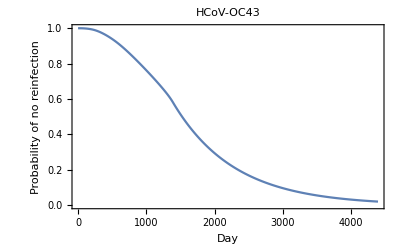

```mathematica
ListLinePlot[oc43probnoreinfectiontimecourse,
PlotRange->{0,1},
PlotLabel->"HCoV-OC43",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability of no reinfection"}]
```

```mathematica
oc43continuousprobnoreinfection=Interpolation[oc43probnoreinfectiontimecourse]
```

InterpolatingFunction[…]

```mathematica
1-oc43continuousprobnoreinfection[365]
```

0.0296156

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[oc43continuousprobnoreinfection[x]-0.95],
 1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{457.518,15.2506,1.25347}

These are the 5% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[oc43continuousprobnoreinfection[x]-0.50], 
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{1525.02,50.834,4.17814}

These are the 50% quantiles (medians) for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[oc43continuousprobnoreinfection[x]-0.05], 
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{3585.9,119.53,9.82439}

These are the 95% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
oc43probreinfectiondensity={};
day=0;
While[day<4393,
Increment[day];
AppendTo[oc43probreinfectiondensity, 
If[day<lengthabtc,
oc43probinfgivenaod[oc43antibodytimecourse[[day]]]*oc43probnoreinfectiontimecourse[[day]],
oc43probinfgivenaod[oc43antibodytimecourse[[lengthabtc]]]*oc43probnoreinfectiontimecourse[[day]]
]
]
];
```

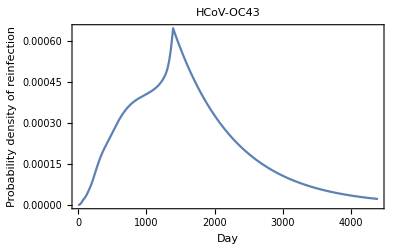

```mathematica
ListLinePlot[oc43probreinfectiondensity,
PlotLabel->"HCoV-OC43",
Frame->{{True,False},{True,False}},
FrameLabel->{"Day", "Probability density of reinfection"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["HCoV-OC43_PrInf-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[oc43probreinfectiondensity,
PlotLabel->"HCoV-OC43",
Frame->{{True,False},{True,False}},FrameLabel->{"Day", "Probability density of reinfection"}]
]
```

HCoV-OC43_PrInf-by-Day_21Jan2021.pdf

## NL63

Input Data: ELIZA ODs for HCoV-NL63 S IgG antibodies from the processed supplementary dataset from Edridge et al. 2020, “Seasonal coronavirus protective immunity is short-lasting”, Nature Medicine

```mathematica
nl63data=Select[fulldataset,MemberQ[#, "NL63"]&];
```

```mathematica
nl63data[[1]]
```

{139,1985-08-20,NL63,0.677122,TRUE,NA,NA,0.311365,NA}

```mathematica
llnl63length=Length[nl63data]
```

513

### Probability of Infection | Antibody OD

```mathematica
llnl63lrdaily=
Sum[
logisticprobability=1/(1+Exp[-(a+b*nl63data[[i,8]])]);
FullSimplify[
PowerExpand[
Log[
Which[
nl63data[[i,5]]=="NA", 1,
nl63data[[i,6]]=="NA", 1,
nl63data[[i,5]]=="TRUE", logisticprobability*(1-logisticprobability)^(nl63data[[i,6]]-1),
nl63data[[i,5]]=="FALSE",(1-logisticprobability)^nl63data[[i,6]],
True,  Abort[]
]
]
]
],
{i, llnl63length}
]
```

-Log[1+ⅇ^(-a-0.502097 b)]-Log[1+ⅇ^(-a-0.493902 b)]-Log[1+ⅇ^(-a-0.46104 b)]-Log[1+ⅇ^(-a-0.444272 b)]-Log[1+ⅇ^(-a-0.440453 b)]-Log[1+ⅇ^(-a-0.432605 b)]-Log[1+ⅇ^(-a-0.408818 b)]-Log[1+ⅇ^(-a-0.400052 b)]-Log[1+ⅇ^(-a-0.373143 b)]-Log[1+ⅇ^(-a-0.372446 b)]-Log[1+ⅇ^(-a-0.371768 b)]-Log[1+ⅇ^(-a-0.353986 b)]-Log[1+ⅇ^(-a-0.338456 b)]-Log[1+ⅇ^(-a-0.332552 b)]-Log[1+ⅇ^(-a-0.330817 b)]-Log[1+ⅇ^(-a-0.32918 b)]-Log[1+ⅇ^(-a-0.319016 b)]-Log[1+ⅇ^(-a-0.3168 b)]-Log[1+ⅇ^(-a-0.316112 b)]-Log[1+ⅇ^(-a-0.312895 b)]-Log[1+ⅇ^(-a-0.297071 b)]-Log[1+ⅇ^(-a-0.295441 b)]-Log[1+ⅇ^(-a-0.292219 b)]-Log[1+ⅇ^(-a-0.273241 b)]-Log[1+ⅇ^(-a-0.230565 b)]-Log[1+ⅇ^(-a-0.219802 b)]+164 Log[1/(1+ⅇ^(a+0.219802 b))]+182 Log[1/(1+ⅇ^(a+0.230565 b))]+198 Log[1/(1+ⅇ^(a+0.245812 b))]+187 Log[1/(1+ⅇ^(a+0.268173 b))]+181 Log[1/(1+ⅇ^(a+0.273241 b))]+178 Log[1/(1+ⅇ^(a+0.277028 b))]+176 Log[1/(1+ⅇ^(a+0.278557 b))]+186 Log[1/(1+ⅇ^(a+0.281283 b))]+113 Log[1/(1+ⅇ^(a+0.289825 b))]+97 Log[1/(1+ⅇ^(a+0.292219 b))]+62 Log[1/(1+ⅇ^(a+0.29316 b))]+195 Log[1/(1+ⅇ^(a+0.295441 b))]+90 Log[1/(1+ⅇ^(a+0.297071 b))]+180 Log[1/(1+ⅇ^(a+0.297553 b))]+169 Log[1/(1+ⅇ^(a+0.297692 b))]+199 Log[1/(1+ⅇ^(a+0.299759 b))]+182 Log[1/(1+ⅇ^(a+0.299929 b))]+121 Log[1/(1+ⅇ^(a+0.300923 b))]+91 Log[1/(1+ⅇ^(a+0.301214 b))]+189 Log[1/(1+ⅇ^(a+0.301575 b))]+188 Log[1/(1+ⅇ^(a+0.303954 b))]+180 Log[1/(1+ⅇ^(a+0.306538 b))]+175 Log[1/(1+ⅇ^(a+0.307908 b))]+92 Log[1/(1+ⅇ^(a+0.308244 b))]+182 Log[1/(1+ⅇ^(a+0.30959 b))]+188 Log[1/(1+ⅇ^(a+0.311134 b))]+96 Log[1/(1+ⅇ^(a+0.311343 b))]+72 Log[1/(1+ⅇ^(a+0.312895 b))]+175 Log[1/(1+ⅇ^(a+0.313523 b))]+2319 Log[1/(1+ⅇ^(a+0.314408 b))]+198 Log[1/(1+ⅇ^(a+0.315535 b))]+378 Log[1/(1+ⅇ^(a+0.31572 b))]+97 Log[1/(1+ⅇ^(a+0.315938 b))]+181 Log[1/(1+ⅇ^(a+0.316112 b))]+182 Log[1/(1+ⅇ^(a+0.316438 b))]+174 Log[1/(1+ⅇ^(a+0.3168 b))]+203 Log[1/(1+ⅇ^(a+0.317653 b))]+362 Log[1/(1+ⅇ^(a+0.319016 b))]+184 Log[1/(1+ⅇ^(a+0.319166 b))]+182 Log[1/(1+ⅇ^(a+0.320021 b))]+86 Log[1/(1+ⅇ^(a+0.320515 b))]+90 Log[1/(1+ⅇ^(a+0.321327 b))]+2424 Log[1/(1+ⅇ^(a+0.323241 b))]+96 Log[1/(1+ⅇ^(a+0.325522 b))]+92 Log[1/(1+ⅇ^(a+0.327585 b))]+176 Log[1/(1+ⅇ^(a+0.329118 b))]+84 Log[1/(1+ⅇ^(a+0.329163 b))]+182 Log[1/(1+ⅇ^(a+0.32918 b))]+97 Log[1/(1+ⅇ^(a+0.330817 b))]+174 Log[1/(1+ⅇ^(a+0.332552 b))]+86 Log[1/(1+ⅇ^(a+0.332929 b))]+181 Log[1/(1+ⅇ^(a+0.332944 b))]+175 Log[1/(1+ⅇ^(a+0.335902 b))]+202 Log[1/(1+ⅇ^(a+0.336171 b))]+103 Log[1/(1+ⅇ^(a+0.338456 b))]+90 Log[1/(1+ⅇ^(a+0.338467 b))]+182 Log[1/(1+ⅇ^(a+0.340494 b))]+182 Log[1/(1+ⅇ^(a+0.340758 b))]+91 Log[1/(1+ⅇ^(a+0.341866 b))]+182 Log[1/(1+ⅇ^(a+0.343016 b))]+183 Log[1/(1+ⅇ^(a+0.344155 b))]+182 Log[1/(1+ⅇ^(a+0.346321 b))]+181 Log[1/(1+ⅇ^(a+0.347349 b))]+91 Log[1/(1+ⅇ^(a+0.34901 b))]+180 Log[1/(1+ⅇ^(a+0.349357 b))]+182 Log[1/(1+ⅇ^(a+0.351115 b))]+190 Log[1/(1+ⅇ^(a+0.351472 b))]+112 Log[1/(1+ⅇ^(a+0.351852 b))]+98 Log[1/(1+ⅇ^(a+0.352037 b))]+180 Log[1/(1+ⅇ^(a+0.353986 b))]+183 Log[1/(1+ⅇ^(a+0.354043 b))]+88 Log[1/(1+ⅇ^(a+0.354302 b))]+181 Log[1/(1+ⅇ^(a+0.354347 b))]+376 Log[1/(1+ⅇ^(a+0.355394 b))]+175 Log[1/(1+ⅇ^(a+0.356572 b))]+91 Log[1/(1+ⅇ^(a+0.358221 b))]+179 Log[1/(1+ⅇ^(a+0.358753 b))]+175 Log[1/(1+ⅇ^(a+0.358826 b))]+160 Log[1/(1+ⅇ^(a+0.358885 b))]+95 Log[1/(1+ⅇ^(a+0.360017 b))]+105 Log[1/(1+ⅇ^(a+0.361708 b))]+93 Log[1/(1+ⅇ^(a+0.361857 b))]+180 Log[1/(1+ⅇ^(a+0.362028 b))]+182 Log[1/(1+ⅇ^(a+0.362286 b))]+92 Log[1/(1+ⅇ^(a+0.362369 b))]+184 Log[1/(1+ⅇ^(a+0.362603 b))]+365 Log[1/(1+ⅇ^(a+0.363219 b))]+91 Log[1/(1+ⅇ^(a+0.363963 b))]+2240 Log[1/(1+ⅇ^(a+0.364052 b))]+182 Log[1/(1+ⅇ^(a+0.364924 b))]+210 Log[1/(1+ⅇ^(a+0.366083 b))]+352 Log[1/(1+ⅇ^(a+0.366948 b))]+181 Log[1/(1+ⅇ^(a+0.367326 b))]+95 Log[1/(1+ⅇ^(a+0.367618 b))]+182 Log[1/(1+ⅇ^(a+0.367949 b))]+182 Log[1/(1+ⅇ^(a+0.368287 b))]+183 Log[1/(1+ⅇ^(a+0.368452 b))]+175 Log[1/(1+ⅇ^(a+0.369079 b))]+186 Log[1/(1+ⅇ^(a+0.369592 b))]+182 Log[1/(1+ⅇ^(a+0.370928 b))]+93 Log[1/(1+ⅇ^(a+0.37108 b))]+83 Log[1/(1+ⅇ^(a+0.371768 b))]+182 Log[1/(1+ⅇ^(a+0.372446 b))]+90 Log[1/(1+ⅇ^(a+0.373143 b))]+169 Log[1/(1+ⅇ^(a+0.373434 b))]+98 Log[1/(1+ⅇ^(a+0.373741 b))]+91 Log[1/(1+ⅇ^(a+0.374211 b))]+94 Log[1/(1+ⅇ^(a+0.374589 b))]+92 Log[1/(1+ⅇ^(a+0.375796 b))]+97 Log[1/(1+ⅇ^(a+0.375814 b))]+91 Log[1/(1+ⅇ^(a+0.377657 b))]+189 Log[1/(1+ⅇ^(a+0.378452 b))]+188 Log[1/(1+ⅇ^(a+0.378849 b))]+189 Log[1/(1+ⅇ^(a+0.379012 b))]+183 Log[1/(1+ⅇ^(a+0.381543 b))]+336 Log[1/(1+ⅇ^(a+0.381608 b))]+182 Log[1/(1+ⅇ^(a+0.381732 b))]+182 Log[1/(1+ⅇ^(a+0.383472 b))]+91 Log[1/(1+ⅇ^(a+0.38424 b))]+182 Log[1/(1+ⅇ^(a+0.384504 b))]+318 Log[1/(1+ⅇ^(a+0.386372 b))]+182 Log[1/(1+ⅇ^(a+0.386824 b))]+189 Log[1/(1+ⅇ^(a+0.386999 b))]+182 Log[1/(1+ⅇ^(a+0.388223 b))]+196 Log[1/(1+ⅇ^(a+0.388637 b))]+182 Log[1/(1+ⅇ^(a+0.389005 b))]+190 Log[1/(1+ⅇ^(a+0.389795 b))]+91 Log[1/(1+ⅇ^(a+0.390745 b))]+175 Log[1/(1+ⅇ^(a+0.39114 b))]+182 Log[1/(1+ⅇ^(a+0.391338 b))]+90 Log[1/(1+ⅇ^(a+0.391501 b))]+184 Log[1/(1+ⅇ^(a+0.391717 b))]+175 Log[1/(1+ⅇ^(a+0.392243 b))]+84 Log[1/(1+ⅇ^(a+0.392273 b))]+182 Log[1/(1+ⅇ^(a+0.392712 b))]+182 Log[1/(1+ⅇ^(a+0.393809 b))]+177 Log[1/(1+ⅇ^(a+0.393873 b))]+181 Log[1/(1+ⅇ^(a+0.395268 b))]+182 Log[1/(1+ⅇ^(a+0.396207 b))]+182 Log[1/(1+ⅇ^(a+0.396851 b))]+183 Log[1/(1+ⅇ^(a+0.397357 b))]+182 Log[1/(1+ⅇ^(a+0.397498 b))]+183 Log[1/(1+ⅇ^(a+0.398176 b))]+182 Log[1/(1+ⅇ^(a+0.39821 b))]+218 Log[1/(1+ⅇ^(a+0.400052 b))]+189 Log[1/(1+ⅇ^(a+0.400085 b))]+203 Log[1/(1+ⅇ^(a+0.400088 b))]+91 Log[1/(1+ⅇ^(a+0.400244 b))]+182 Log[1/(1+ⅇ^(a+0.400944 b))]+160 Log[1/(1+ⅇ^(a+0.401009 b))]+189 Log[1/(1+ⅇ^(a+0.401253 b))]+182 Log[1/(1+ⅇ^(a+0.40133 b))]+197 Log[1/(1+ⅇ^(a+0.403562 b))]+182 Log[1/(1+ⅇ^(a+0.403623 b))]+245 Log[1/(1+ⅇ^(a+0.404268 b))]+177 Log[1/(1+ⅇ^(a+0.404696 b))]+191 Log[1/(1+ⅇ^(a+0.406219 b))]+86 Log[1/(1+ⅇ^(a+0.406287 b))]+189 Log[1/(1+ⅇ^(a+0.406611 b))]+217 Log[1/(1+ⅇ^(a+0.406673 b))]+183 Log[1/(1+ⅇ^(a+0.407284 b))]+91 Log[1/(1+ⅇ^(a+0.407419 b))]+91 Log[1/(1+ⅇ^(a+0.408281 b))]+181 Log[1/(1+ⅇ^(a+0.40881 b))]+188 Log[1/(1+ⅇ^(a+0.408818 b))]+182 Log[1/(1+ⅇ^(a+0.409146 b))]+168 Log[1/(1+ⅇ^(a+0.410105 b))]+187 Log[1/(1+ⅇ^(a+0.41076 b))]+156 Log[1/(1+ⅇ^(a+0.410874 b))]+182 Log[1/(1+ⅇ^(a+0.411075 b))]+176 Log[1/(1+ⅇ^(a+0.41136 b))]+181 Log[1/(1+ⅇ^(a+0.411494 b))]+187 Log[1/(1+ⅇ^(a+0.411843 b))]+182 Log[1/(1+ⅇ^(a+0.412834 b))]+90 Log[1/(1+ⅇ^(a+0.413868 b))]+91 Log[1/(1+ⅇ^(a+0.414115 b))]+3239 Log[1/(1+ⅇ^(a+0.414137 b))]+196 Log[1/(1+ⅇ^(a+0.414797 b))]+2338 Log[1/(1+ⅇ^(a+0.41488 b))]+98 Log[1/(1+ⅇ^(a+0.414979 b))]+183 Log[1/(1+ⅇ^(a+0.415508 b))]+182 Log[1/(1+ⅇ^(a+0.416029 b))]+186 Log[1/(1+ⅇ^(a+0.416122 b))]+175 Log[1/(1+ⅇ^(a+0.416366 b))]+97 Log[1/(1+ⅇ^(a+0.416729 b))]+175 Log[1/(1+ⅇ^(a+0.417438 b))]+182 Log[1/(1+ⅇ^(a+0.417891 b))]+102 Log[1/(1+ⅇ^(a+0.418627 b))]+126 Log[1/(1+ⅇ^(a+0.419174 b))]+191 Log[1/(1+ⅇ^(a+0.420361 b))]+189 Log[1/(1+ⅇ^(a+0.420796 b))]+65 Log[1/(1+ⅇ^(a+0.421715 b))]+2303 Log[1/(1+ⅇ^(a+0.42181 b))]+180 Log[1/(1+ⅇ^(a+0.423275 b))]+196 Log[1/(1+ⅇ^(a+0.42328 b))]+182 Log[1/(1+ⅇ^(a+0.424797 b))]+448 Log[1/(1+ⅇ^(a+0.425293 b))]+194 Log[1/(1+ⅇ^(a+0.427085 b))]+2359 Log[1/(1+ⅇ^(a+0.427347 b))]+182 Log[1/(1+ⅇ^(a+0.427407 b))]+98 Log[1/(1+ⅇ^(a+0.427839 b))]+182 Log[1/(1+ⅇ^(a+0.428029 b))]+181 Log[1/(1+ⅇ^(a+0.429037 b))]+182 Log[1/(1+ⅇ^(a+0.429569 b))]+189 Log[1/(1+ⅇ^(a+0.429905 b))]+175 Log[1/(1+ⅇ^(a+0.430233 b))]+182 Log[1/(1+ⅇ^(a+0.430371 b))]+95 Log[1/(1+ⅇ^(a+0.430394 b))]+182 Log[1/(1+ⅇ^(a+0.431268 b))]+175 Log[1/(1+ⅇ^(a+0.431381 b))]+189 Log[1/(1+ⅇ^(a+0.431798 b))]+181 Log[1/(1+ⅇ^(a+0.431844 b))]+182 Log[1/(1+ⅇ^(a+0.431845 b))]+188 Log[1/(1+ⅇ^(a+0.432605 b))]+177 Log[1/(1+ⅇ^(a+0.432881 b))]+189 Log[1/(1+ⅇ^(a+0.433155 b))]+168 Log[1/(1+ⅇ^(a+0.433338 b))]+182 Log[1/(1+ⅇ^(a+0.433477 b))]+82 Log[1/(1+ⅇ^(a+0.433556 b))]+189 Log[1/(1+ⅇ^(a+0.434149 b))]+91 Log[1/(1+ⅇ^(a+0.434175 b))]+197 Log[1/(1+ⅇ^(a+0.434211 b))]+91 Log[1/(1+ⅇ^(a+0.436975 b))]+124 Log[1/(1+ⅇ^(a+0.437825 b))]+84 Log[1/(1+ⅇ^(a+0.438193 b))]+182 Log[1/(1+ⅇ^(a+0.43857 b))]+211 Log[1/(1+ⅇ^(a+0.438581 b))]+91 Log[1/(1+ⅇ^(a+0.439213 b))]+223 Log[1/(1+ⅇ^(a+0.4396 b))]+189 Log[1/(1+ⅇ^(a+0.439792 b))]+91 Log[1/(1+ⅇ^(a+0.440366 b))]+181 Log[1/(1+ⅇ^(a+0.440453 b))]+212 Log[1/(1+ⅇ^(a+0.441079 b))]+183 Log[1/(1+ⅇ^(a+0.442086 b))]+190 Log[1/(1+ⅇ^(a+0.442111 b))]+84 Log[1/(1+ⅇ^(a+0.443305 b))]+181 Log[1/(1+ⅇ^(a+0.444272 b))]+192 Log[1/(1+ⅇ^(a+0.446141 b))]+91 Log[1/(1+ⅇ^(a+0.446421 b))]+93 Log[1/(1+ⅇ^(a+0.447528 b))]+170 Log[1/(1+ⅇ^(a+0.449378 b))]+91 Log[1/(1+ⅇ^(a+0.449549 b))]+84 Log[1/(1+ⅇ^(a+0.449782 b))]+98 Log[1/(1+ⅇ^(a+0.450279 b))]+181 Log[1/(1+ⅇ^(a+0.451373 b))]+89 Log[1/(1+ⅇ^(a+0.45168 b))]+96 Log[1/(1+ⅇ^(a+0.45169 b))]+190 Log[1/(1+ⅇ^(a+0.452271 b))]+91 Log[1/(1+ⅇ^(a+0.452295 b))]+189 Log[1/(1+ⅇ^(a+0.45235 b))]+98 Log[1/(1+ⅇ^(a+0.452746 b))]+188 Log[1/(1+ⅇ^(a+0.454202 b))]+189 Log[1/(1+ⅇ^(a+0.454384 b))]+182 Log[1/(1+ⅇ^(a+0.454444 b))]+183 Log[1/(1+ⅇ^(a+0.454807 b))]+182 Log[1/(1+ⅇ^(a+0.454948 b))]+189 Log[1/(1+ⅇ^(a+0.455229 b))]+183 Log[1/(1+ⅇ^(a+0.45558 b))]+147 Log[1/(1+ⅇ^(a+0.455977 b))]+165 Log[1/(1+ⅇ^(a+0.457001 b))]+177 Log[1/(1+ⅇ^(a+0.457752 b))]+91 Log[1/(1+ⅇ^(a+0.457915 b))]+189 Log[1/(1+ⅇ^(a+0.458799 b))]+91 Log[1/(1+ⅇ^(a+0.460131 b))]+182 Log[1/(1+ⅇ^(a+0.460159 b))]+175 Log[1/(1+ⅇ^(a+0.461026 b))]+174 Log[1/(1+ⅇ^(a+0.46104 b))]+209 Log[1/(1+ⅇ^(a+0.462813 b))]+190 Log[1/(1+ⅇ^(a+0.463269 b))]+105 Log[1/(1+ⅇ^(a+0.463464 b))]+181 Log[1/(1+ⅇ^(a+0.465213 b))]+183 Log[1/(1+ⅇ^(a+0.46593 b))]+188 Log[1/(1+ⅇ^(a+0.466556 b))]+185 Log[1/(1+ⅇ^(a+0.466648 b))]+98 Log[1/(1+ⅇ^(a+0.467446 b))]+92 Log[1/(1+ⅇ^(a+0.468553 b))]+189 Log[1/(1+ⅇ^(a+0.468887 b))]+195 Log[1/(1+ⅇ^(a+0.471115 b))]+91 Log[1/(1+ⅇ^(a+0.47146 b))]+168 Log[1/(1+ⅇ^(a+0.471491 b))]+2394 Log[1/(1+ⅇ^(a+0.471659 b))]+167 Log[1/(1+ⅇ^(a+0.472194 b))]+94 Log[1/(1+ⅇ^(a+0.473467 b))]+175 Log[1/(1+ⅇ^(a+0.47347 b))]+91 Log[1/(1+ⅇ^(a+0.47438 b))]+91 Log[1/(1+ⅇ^(a+0.47538 b))]+96 Log[1/(1+ⅇ^(a+0.476014 b))]+196 Log[1/(1+ⅇ^(a+0.476315 b))]+92 Log[1/(1+ⅇ^(a+0.476887 b))]+78 Log[1/(1+ⅇ^(a+0.477223 b))]+189 Log[1/(1+ⅇ^(a+0.47802 b))]+91 Log[1/(1+ⅇ^(a+0.478099 b))]+107 Log[1/(1+ⅇ^(a+0.479568 b))]+201 Log[1/(1+ⅇ^(a+0.479988 b))]+77 Log[1/(1+ⅇ^(a+0.481074 b))]+181 Log[1/(1+ⅇ^(a+0.481394 b))]+90 Log[1/(1+ⅇ^(a+0.481766 b))]+182 Log[1/(1+ⅇ^(a+0.48358 b))]+196 Log[1/(1+ⅇ^(a+0.484908 b))]+224 Log[1/(1+ⅇ^(a+0.48508 b))]+91 Log[1/(1+ⅇ^(a+0.485176 b))]+96 Log[1/(1+ⅇ^(a+0.486054 b))]+175 Log[1/(1+ⅇ^(a+0.486626 b))]+182 Log[1/(1+ⅇ^(a+0.487258 b))]+85 Log[1/(1+ⅇ^(a+0.488448 b))]+91 Log[1/(1+ⅇ^(a+0.489327 b))]+98 Log[1/(1+ⅇ^(a+0.489877 b))]+98 Log[1/(1+ⅇ^(a+0.49005 b))]+95 Log[1/(1+ⅇ^(a+0.490869 b))]+91 Log[1/(1+ⅇ^(a+0.491115 b))]+181 Log[1/(1+ⅇ^(a+0.49369 b))]+182 Log[1/(1+ⅇ^(a+0.493834 b))]+79 Log[1/(1+ⅇ^(a+0.493902 b))]+98 Log[1/(1+ⅇ^(a+0.495097 b))]+93 Log[1/(1+ⅇ^(a+0.49601 b))]+91 Log[1/(1+ⅇ^(a+0.497001 b))]+189 Log[1/(1+ⅇ^(a+0.498201 b))]+160 Log[1/(1+ⅇ^(a+0.499188 b))]+84 Log[1/(1+ⅇ^(a+0.499458 b))]+189 Log[1/(1+ⅇ^(a+0.499583 b))]+91 Log[1/(1+ⅇ^(a+0.500321 b))]+99 Log[1/(1+ⅇ^(a+0.500706 b))]+95 Log[1/(1+ⅇ^(a+0.500935 b))]+182 Log[1/(1+ⅇ^(a+0.501372 b))]+180 Log[1/(1+ⅇ^(a+0.501734 b))]+185 Log[1/(1+ⅇ^(a+0.502097 b))]+175 Log[1/(1+ⅇ^(a+0.502733 b))]+182 Log[1/(1+ⅇ^(a+0.504339 b))]+176 Log[1/(1+ⅇ^(a+0.505312 b))]+79 Log[1/(1+ⅇ^(a+0.505368 b))]+189 Log[1/(1+ⅇ^(a+0.50538 b))]+182 Log[1/(1+ⅇ^(a+0.505641 b))]+188 Log[1/(1+ⅇ^(a+0.50567 b))]+184 Log[1/(1+ⅇ^(a+0.506126 b))]+168 Log[1/(1+ⅇ^(a+0.506881 b))]+185 Log[1/(1+ⅇ^(a+0.507149 b))]+182 Log[1/(1+ⅇ^(a+0.507164 b))]+99 Log[1/(1+ⅇ^(a+0.507724 b))]+87 Log[1/(1+ⅇ^(a+0.508201 b))]+94 Log[1/(1+ⅇ^(a+0.508796 b))]+182 Log[1/(1+ⅇ^(a+0.50983 b))]+182 Log[1/(1+ⅇ^(a+0.51054 b))]+182 Log[1/(1+ⅇ^(a+0.510614 b))]+184 Log[1/(1+ⅇ^(a+0.511628 b))]+162 Log[1/(1+ⅇ^(a+0.513016 b))]+182 Log[1/(1+ⅇ^(a+0.514162 b))]+91 Log[1/(1+ⅇ^(a+0.514828 b))]+183 Log[1/(1+ⅇ^(a+0.51491 b))]+91 Log[1/(1+ⅇ^(a+0.51623 b))]+94 Log[1/(1+ⅇ^(a+0.517206 b))]+231 Log[1/(1+ⅇ^(a+0.517651 b))]+182 Log[1/(1+ⅇ^(a+0.517893 b))]+182 Log[1/(1+ⅇ^(a+0.518362 b))]+188 Log[1/(1+ⅇ^(a+0.51896 b))]+91 Log[1/(1+ⅇ^(a+0.519976 b))]+98 Log[1/(1+ⅇ^(a+0.520123 b))]+105 Log[1/(1+ⅇ^(a+0.523836 b))]+79 Log[1/(1+ⅇ^(a+0.524045 b))]+183 Log[1/(1+ⅇ^(a+0.525829 b))]+357 Log[1/(1+ⅇ^(a+0.525977 b))]+92 Log[1/(1+ⅇ^(a+0.52619 b))]+182 Log[1/(1+ⅇ^(a+0.526788 b))]+179 Log[1/(1+ⅇ^(a+0.527154 b))]+204 Log[1/(1+ⅇ^(a+0.52853 b))]+187 Log[1/(1+ⅇ^(a+0.530611 b))]+91 Log[1/(1+ⅇ^(a+0.531577 b))]+182 Log[1/(1+ⅇ^(a+0.531778 b))]+188 Log[1/(1+ⅇ^(a+0.532414 b))]+172 Log[1/(1+ⅇ^(a+0.532721 b))]+92 Log[1/(1+ⅇ^(a+0.533065 b))]+183 Log[1/(1+ⅇ^(a+0.533796 b))]+175 Log[1/(1+ⅇ^(a+0.534205 b))]+177 Log[1/(1+ⅇ^(a+0.535424 b))]+91 Log[1/(1+ⅇ^(a+0.536049 b))]+84 Log[1/(1+ⅇ^(a+0.536475 b))]+188 Log[1/(1+ⅇ^(a+0.536764 b))]+182 Log[1/(1+ⅇ^(a+0.537681 b))]+132 Log[1/(1+ⅇ^(a+0.538025 b))]+88 Log[1/(1+ⅇ^(a+0.544067 b))]+91 Log[1/(1+ⅇ^(a+0.544128 b))]+189 Log[1/(1+ⅇ^(a+0.544789 b))]+89 Log[1/(1+ⅇ^(a+0.54514 b))]+245 Log[1/(1+ⅇ^(a+0.54542 b))]+182 Log[1/(1+ⅇ^(a+0.547732 b))]+175 Log[1/(1+ⅇ^(a+0.547997 b))]+189 Log[1/(1+ⅇ^(a+0.550315 b))]+159 Log[1/(1+ⅇ^(a+0.551094 b))]+91 Log[1/(1+ⅇ^(a+0.551206 b))]+97 Log[1/(1+ⅇ^(a+0.551397 b))]+174 Log[1/(1+ⅇ^(a+0.55145 b))]+193 Log[1/(1+ⅇ^(a+0.552116 b))]+172 Log[1/(1+ⅇ^(a+0.552784 b))]+335 Log[1/(1+ⅇ^(a+0.553861 b))]+91 Log[1/(1+ⅇ^(a+0.558646 b))]+371 Log[1/(1+ⅇ^(a+0.558685 b))]+183 Log[1/(1+ⅇ^(a+0.55956 b))]+80 Log[1/(1+ⅇ^(a+0.560059 b))]+182 Log[1/(1+ⅇ^(a+0.560607 b))]+80 Log[1/(1+ⅇ^(a+0.560758 b))]+182 Log[1/(1+ⅇ^(a+0.562504 b))]+91 Log[1/(1+ⅇ^(a+0.564261 b))]+98 Log[1/(1+ⅇ^(a+0.565172 b))]+189 Log[1/(1+ⅇ^(a+0.565772 b))]+98 Log[1/(1+ⅇ^(a+0.5667 b))]+175 Log[1/(1+ⅇ^(a+0.568706 b))]+182 Log[1/(1+ⅇ^(a+0.56891 b))]+166 Log[1/(1+ⅇ^(a+0.569266 b))]+84 Log[1/(1+ⅇ^(a+0.56933 b))]+181 Log[1/(1+ⅇ^(a+0.569718 b))]+182 Log[1/(1+ⅇ^(a+0.570036 b))]+91 Log[1/(1+ⅇ^(a+0.570382 b))]+91 Log[1/(1+ⅇ^(a+0.572113 b))]+91 Log[1/(1+ⅇ^(a+0.574041 b))]+178 Log[1/(1+ⅇ^(a+0.575019 b))]+184 Log[1/(1+ⅇ^(a+0.58085 b))]+183 Log[1/(1+ⅇ^(a+0.581476 b))]+88 Log[1/(1+ⅇ^(a+0.581481 b))]+175 Log[1/(1+ⅇ^(a+0.583732 b))]+175 Log[1/(1+ⅇ^(a+0.584495 b))]+181 Log[1/(1+ⅇ^(a+0.585776 b))]+105 Log[1/(1+ⅇ^(a+0.586974 b))]+182 Log[1/(1+ⅇ^(a+0.587319 b))]+182 Log[1/(1+ⅇ^(a+0.589018 b))]+91 Log[1/(1+ⅇ^(a+0.589265 b))]+96 Log[1/(1+ⅇ^(a+0.589601 b))]+96 Log[1/(1+ⅇ^(a+0.594728 b))]+84 Log[1/(1+ⅇ^(a+0.600603 b))]+203 Log[1/(1+ⅇ^(a+0.604699 b))]+184 Log[1/(1+ⅇ^(a+0.606373 b))]+182 Log[1/(1+ⅇ^(a+0.607601 b))]+91 Log[1/(1+ⅇ^(a+0.610533 b))]+189 Log[1/(1+ⅇ^(a+0.610572 b))]+82 Log[1/(1+ⅇ^(a+0.611264 b))]+182 Log[1/(1+ⅇ^(a+0.61136 b))]+91 Log[1/(1+ⅇ^(a+0.612671 b))]+175 Log[1/(1+ⅇ^(a+0.614603 b))]+190 Log[1/(1+ⅇ^(a+0.616656 b))]+91 Log[1/(1+ⅇ^(a+0.624986 b))]+92 Log[1/(1+ⅇ^(a+0.627131 b))]+86 Log[1/(1+ⅇ^(a+0.629762 b))]+98 Log[1/(1+ⅇ^(a+0.632328 b))]+92 Log[1/(1+ⅇ^(a+0.634337 b))]+77 Log[1/(1+ⅇ^(a+0.635838 b))]+189 Log[1/(1+ⅇ^(a+0.640158 b))]+88 Log[1/(1+ⅇ^(a+0.641766 b))]+195 Log[1/(1+ⅇ^(a+0.648465 b))]+175 Log[1/(1+ⅇ^(a+0.648714 b))]+103 Log[1/(1+ⅇ^(a+0.649441 b))]+89 Log[1/(1+ⅇ^(a+0.650155 b))]+99 Log[1/(1+ⅇ^(a+0.65445 b))]+178 Log[1/(1+ⅇ^(a+0.655717 b))]+98 Log[1/(1+ⅇ^(a+0.656946 b))]+181 Log[1/(1+ⅇ^(a+0.656985 b))]+238 Log[1/(1+ⅇ^(a+0.665707 b))]+182 Log[1/(1+ⅇ^(a+0.666362 b))]+91 Log[1/(1+ⅇ^(a+0.674265 b))]+94 Log[1/(1+ⅇ^(a+0.677334 b))]+91 Log[1/(1+ⅇ^(a+0.683203 b))]+182 Log[1/(1+ⅇ^(a+0.684159 b))]+90 Log[1/(1+ⅇ^(a+0.689304 b))]+180 Log[1/(1+ⅇ^(a+0.690768 b))]+200 Log[1/(1+ⅇ^(a+0.696666 b))]+93 Log[1/(1+ⅇ^(a+0.702852 b))]+189 Log[1/(1+ⅇ^(a+0.72398 b))]+182 Log[1/(1+ⅇ^(a+0.724808 b))]+180 Log[1/(1+ⅇ^(a+0.729362 b))]+187 Log[1/(1+ⅇ^(a+0.729827 b))]+78 Log[1/(1+ⅇ^(a+0.731254 b))]+155 Log[1/(1+ⅇ^(a+0.732627 b))]+98 Log[1/(1+ⅇ^(a+0.749681 b))]+94 Log[1/(1+ⅇ^(a+0.752401 b))]+89 Log[1/(1+ⅇ^(a+0.771954 b))]+183 Log[1/(1+ⅇ^(a+0.780301 b))]+175 Log[1/(1+ⅇ^(a+0.782638 b))]+91 Log[1/(1+ⅇ^(a+0.806087 b))]+177 Log[1/(1+ⅇ^(a+0.812416 b))]+183 Log[1/(1+ⅇ^(a+0.822578 b))]+94 Log[1/(1+ⅇ^(a+0.833427 b))]+189 Log[1/(1+ⅇ^(a+0.841001 b))]+174 Log[1/(1+ⅇ^(a+0.855121 b))]+178 Log[1/(1+ⅇ^(a+0.861946 b))]+93 Log[1/(1+ⅇ^(a+0.868685 b))]+182 Log[1/(1+ⅇ^(a+0.87776 b))]+81 Log[1/(1+ⅇ^(a+0.907469 b))]+84 Log[1/(1+ⅇ^(a+0.965345 b))]+190 Log[1/(1+ⅇ^(a+0.974292 b))]+90 Log[1/(1+ⅇ^(a+0.974452 b))]+29 Log[1/(1+ⅇ^(a+0.988753 b))]+166 Log[1/(1+ⅇ^(a+0.997889 b))]+182 Log[1/(1+ⅇ^(a+1.00472 b))]+182 Log[1/(1+ⅇ^(a+1.05389 b))]+130 Log[1/(1+ⅇ^(a+1.10095 b))]+82 Log[1/(1+ⅇ^(a+1.14295 b))]

```mathematica
maxllnl63lrdaily=NMaximize[{llnl63lrdaily}, {a, b}]
```

{-225.216,{a→-2.79029,b→-13.68}}

These values of a and b go into the the ancestral and descendent states analysis to estimate a and b for the zoonotic coronaviruses.

```mathematica
nl63probinfgivenaod[aod_]:=1/(1+Exp[-(a+b*aod)]) /. maxllnl63lrdaily[[2]]
```

```mathematica
nl63probinfgivenaod[aod]
```

1/(1+ⅇ^(2.79029+13.68 aod))

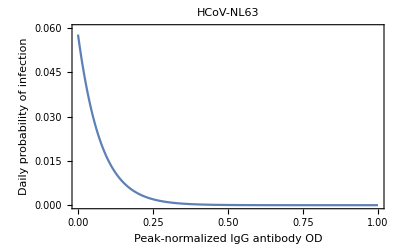

```mathematica
Plot[1/(1+Exp[-(a+b*x)]) /. maxllnl63lrdaily[[2]],{x,0,1},
PlotRange->{0,0.06},
PlotLabel->"HCoV-NL63",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["HCoV-NL63_PrInf-by-nOD_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Plot[1/(1+Exp[-(a+b*x)]) /. maxllnl63lrdaily[[2]],{x,0,1},
PlotRange->{0,0.06},
PlotLabel->"HCoV-NL63",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
]
```

HCoV-NL63_PrInf-by-nOD_21Jan2021.pdf

### NL63 Waning of Antibody OD

```mathematica
nl63data
```

{{139,1985-08-20,NL63,0.677122,TRUE,NA,NA,0.311365,NA},{140,1985-11-18,NL63,2.11913,FALSE,90,0.0160223,0.974452,0.00736763},{141,1986-02-14,NL63,0.770497,FALSE,88,-0.0153254,0.354302,-0.00704715},{142,1986-05-29,NL63,0.736037,TRUE,104,-0.000331352,0.338456,-0.000152368},{143,1986-09-05,NL63,1.42322,FALSE,99,0.00694129,0.65445,0.00319185},{144,1986-11-26,NL63,1.32931,FALSE,82,-0.00114532,0.611264,-0.000526658},{145,1987-03-04,NL63,1.13111,FALSE,98,-0.00202247,0.520123,-0.000930007},{146,1987-06-01,NL63,1.67876,FALSE,89,0.00615342,0.771954,0.00282956},{147,1987-08-20,NL63,1.21795,FALSE,80,-0.00576008,0.560059,-0.00264869},{148,1987-11-19,NL63,1.28147,FALSE,91,0.000697949,0.589265,0.000320942},{149,1988-02-25,NL63,1.22907,FALSE,98,-0.000534627,0.565172,-0.000245841},{150,1988-05-19,NL63,1.16667,FALSE,84,-0.000742948,0.536475,-0.000341634},{151,1988-09-28,NL63,1.17004,FALSE,132,0.000025537,0.538025,0.0000117428},{152,1988-12-14,NL63,1.38275,FALSE,77,0.0027625,0.635838,0.0012703},{153,1989-11-14,NL63,1.20448,FALSE,335,-0.000532162,0.553861,-0.000244707},{154,1990-06-11,NL63,1.00647,FALSE,209,-0.000947377,0.462813,-0.000435638},{155,1990-12-17,NL63,0.988144,FALSE,189,-0.0000969831,0.454384,-0.0000445963},{156,1991-06-26,NL63,0.883399,FALSE,191,-0.0005484,0.406219,-0.000252174},{157,1991-12-20,NL63,0.880087,FALSE,177,-0.0000187157,0.404696,-8.60614×10^-6},{158,1992-12-11,NL63,1.14384,FALSE,357,0.000738791,0.525977,0.000339723},{159,1993-06-11,NL63,0.989369,FALSE,182,-0.000848714,0.454948,-0.000390269},{160,1993-12-09,NL63,0.889035,FALSE,181,-0.000554335,0.40881,-0.000254903},{161,1994-06-09,NL63,0.929477,FALSE,182,0.000222209,0.427407,0.00010218},{162,1994-12-08,NL63,1.09961,FALSE,182,0.000934805,0.505641,0.000429857},{163,1995-06-15,NL63,0.87006,FALSE,189,-0.00121456,0.400085,-0.000558497},{164,1995-12-11,NL63,1.1464,FALSE,179,0.00154378,0.527154,0.000709885},{165,1996-06-10,NL63,1.05164,FALSE,182,-0.000520664,0.48358,-0.00023942},{166,1996-12-02,NL63,0.802632,FALSE,175,-0.00142288,0.369079,-0.000654291},{167,2003-04-28,NL63,0.902234,FALSE,2338,0.0000426015,0.41488,0.0000195897},{168,2003-10-27,NL63,0.937873,FALSE,182,0.000195817,0.431268,0.0000900439},{169,2004-04-26,NL63,0.800908,FALSE,182,-0.000752551,0.368287,-0.00034605},{170,2004-10-25,NL63,0.930831,FALSE,182,0.000713859,0.428029,0.000328258},{171,2005-04-20,NL63,0.941381,FALSE,177,0.0000596039,0.432881,0.000027408},{172,2005-11-02,NL63,0.902055,FALSE,196,-0.000200643,0.414797,-0.000092263},{173,2006-04-26,NL63,1.00259,FALSE,175,0.000574472,0.461026,0.000264163},{174,2006-10-25,NL63,1.21915,FALSE,182,0.00118989,0.560607,0.000547152},{175,2007-04-25,NL63,1.11043,FALSE,182,-0.000597359,0.510614,-0.000274687},{176,2008-07-16,NL63,0.92488,FALSE,448,-0.000414167,0.425293,-0.000190449},{177,2008-11-19,NL63,0.911574,FALSE,126,-0.000105604,0.419174,-0.0000485605},{178,2009-05-18,NL63,0.920491,FALSE,180,0.000049539,0.423275,0.0000227798},{179,2010-04-01,NL63,0.840238,FALSE,318,-0.000252369,0.386372,-0.000116048},{180,2011-04-12,NL63,0.772871,FALSE,376,-0.000179167,0.355394,-0.0000823872},{181,2012-04-11,NL63,0.789888,FALSE,365,0.0000466217,0.363219,0.0000214383},{182,2013-04-09,NL63,0.693761,TRUE,363,-0.000264812,0.319016,-0.00012177},{183,2014-04-15,NL63,1.21497,FALSE,371,0.00140486,0.558685,0.000646007},{184,2015-04-28,NL63,0.686593,FALSE,378,-0.00139781,0.31572,-0.000642764},{185,2017-08-30,NL63,0.699511,NA,855,0.0000151089,0.32166,6.94762×10^-6},{443,1985-03-01,NL63,0.805333,FALSE,NA,NA,0.370321,NA},{444,1985-05-31,NL63,0.779018,FALSE,91,-0.00028917,0.358221,-0.000132971},{445,1985-09-05,NL63,0.817279,FALSE,97,0.000394438,0.375814,0.000181377},{446,1985-12-05,NL63,0.813791,FALSE,91,-0.0000383263,0.374211,-0.0000176238},{447,1986-03-20,NL63,0.786601,FALSE,105,-0.000258951,0.361708,-0.000119075},{448,1986-06-26,NL63,0.765571,FALSE,98,-0.000214598,0.352037,-0.0000986799},{449,1986-09-18,NL63,0.715826,FALSE,84,-0.000592202,0.329163,-0.000272316},{450,1986-12-18,NL63,0.743452,FALSE,91,0.000303579,0.341866,0.000139597},{451,1987-03-19,NL63,0.758988,FALSE,91,0.000170728,0.34901,0.0000785068},{452,1987-06-25,NL63,0.635486,TRUE,98,-0.00126023,0.292219,-0.000579497},{453,1987-09-14,NL63,1.97346,FALSE,81,0.0165182,0.907469,0.00759568},{454,1987-12-03,NL63,1.21947,FALSE,80,-0.00942487,0.560758,-0.00433389},{455,1988-03-03,NL63,1.0338,FALSE,91,-0.00204034,0.47538,-0.00093822},{456,1988-06-02,NL63,0.957658,FALSE,91,-0.000836763,0.440366,-0.000384774},{457,1988-09-06,NL63,0.982284,FALSE,96,0.000256525,0.45169,0.000117959},{458,1988-12-08,NL63,0.973233,FALSE,93,-0.0000973249,0.447528,-0.0000447535},{459,1989-06-08,NL63,0.889765,FALSE,182,-0.000458612,0.409146,-0.000210886},{460,1989-12-07,NL63,0.865984,FALSE,182,-0.00013067,0.39821,-0.0000600866},{461,1990-06-07,NL63,1.23965,FALSE,182,0.00205312,0.570036,0.000944097},{462,1990-12-07,NL63,0.865908,FALSE,183,-0.00204231,0.398176,-0.000939127},{463,1991-06-07,NL63,0.806653,FALSE,182,-0.000325581,0.370928,-0.000149714},{464,1991-12-04,NL63,0.759743,FALSE,180,-0.000260607,0.349357,-0.000119837},{465,1992-06-03,NL63,0.793596,FALSE,182,0.000186003,0.364924,0.0000855308},{466,1992-12-03,NL63,0.990746,FALSE,183,0.00107732,0.45558,0.000495391},{467,1993-06-03,NL63,0.864433,FALSE,182,-0.000694023,0.397498,-0.000319137},{468,1993-12-08,NL63,0.823879,FALSE,188,-0.000215717,0.378849,-0.0000991943},{469,1994-06-16,NL63,0.847683,FALSE,190,0.000125284,0.389795,0.0000576101},{470,1994-12-14,NL63,0.769809,TRUE,181,-0.00043024,0.353986,-0.00019784},{471,1995-06-21,NL63,1.57443,FALSE,189,0.00425726,0.72398,0.00195764},{472,1995-12-06,NL63,1.10231,FALSE,168,-0.00281026,0.506881,-0.00129226},{473,1996-06-11,NL63,1.09967,FALSE,188,-0.000014004,0.50567,-6.43956×10^-6},{474,1996-12-04,NL63,1.0989,FALSE,176,-4.42239×10^-6,0.505312,-2.03358×10^-6},{475,2005-10-17,NL63,0.90062,FALSE,3239,-0.0000612153,0.414137,-0.000028149},{476,2006-04-18,NL63,0.829736,FALSE,183,-0.000387342,0.381543,-0.000178114},{477,2006-10-24,NL63,0.889053,TRUE,189,0.000313845,0.408818,0.000144317},{478,2007-04-24,NL63,2.18496,FALSE,182,0.00712038,1.00472,0.00327421},{479,2007-10-23,NL63,1.48783,FALSE,182,-0.00383038,0.684159,-0.00176135},{480,2008-04-15,NL63,1.33657,FALSE,175,-0.000864353,0.614603,-0.00039746},{481,2008-10-14,NL63,1.27724,FALSE,182,-0.000326014,0.587319,-0.000149913},{482,2009-04-07,NL63,1.23676,FALSE,175,-0.000231309,0.568706,-0.000106364},{483,2009-10-13,NL63,1.3278,FALSE,189,0.000481731,0.610572,0.000221517},{484,2010-04-13,NL63,1.32952,FALSE,182,9.40947×10^-6,0.61136,4.32681×10^-6},{485,2010-10-12,NL63,1.16929,FALSE,182,-0.000880371,0.537681,-0.000404826},{486,2011-04-26,NL63,1.03584,FALSE,196,-0.000680878,0.476315,-0.000313092},{487,2011-10-18,NL63,1.02965,FALSE,175,-0.0000353591,0.47347,-0.0000162594},{488,2012-04-24,NL63,0.997746,FALSE,189,-0.000168803,0.458799,-0.0000776217},{489,2012-10-30,NL63,0.940782,TRUE,189,-0.000301395,0.432605,-0.000138592},{490,2013-04-22,NL63,1.85962,FALSE,174,0.00528068,0.855121,0.00242825},{491,2013-10-28,NL63,0.93491,FALSE,189,-0.00489265,0.429905,-0.00224982},{492,2014-04-29,NL63,1.16084,FALSE,183,0.0012346,0.533796,0.000567712},{493,2014-10-29,NL63,0.989064,FALSE,183,-0.000938669,0.454807,-0.000431634},{494,2015-04-22,NL63,1.09329,FALSE,175,0.000595558,0.502733,0.000273859},{495,2015-10-27,NL63,0.987748,FALSE,188,-0.000561378,0.454202,-0.000258142},{496,2016-04-19,NL63,1.05826,FALSE,175,0.000402931,0.486626,0.000185282},{497,2016-10-18,NL63,1.12626,FALSE,182,0.000373601,0.517893,0.000171795},{498,2017-04-25,NL63,1.03955,FALSE,189,-0.00045879,0.47802,-0.000210968},{499,2017-10-31,NL63,0.941977,FALSE,189,-0.000516236,0.433155,-0.000237384},{500,2018-05-22,NL63,0.870068,FALSE,203,-0.00035423,0.400088,-0.000162888},{501,2018-11-20,NL63,0.845965,FALSE,182,-0.00013243,0.389005,-0.0000608963},{502,2019-05-16,NL63,0.856551,FALSE,177,0.0000598067,0.393873,0.0000275013},{503,2019-11-19,NL63,0.811657,NA,187,-0.000240075,0.373229,-0.000110395},{805,1985-01-31,NL63,1.33134,FALSE,NA,NA,0.612199,NA},{806,1985-05-02,NL63,1.33237,FALSE,91,0.0000112795,0.612671,5.18674×10^-6},{807,1985-08-06,NL63,1.2822,FALSE,96,-0.000522593,0.589601,-0.000240307},{808,1985-11-05,NL63,1.15602,FALSE,91,-0.00138664,0.531577,-0.000637626},{809,1986-02-04,NL63,1.24836,FALSE,91,0.00101479,0.574041,0.000466638},{810,1986-05-06,NL63,1.1987,FALSE,91,-0.000545703,0.551206,-0.000250934},{811,1986-08-06,NL63,1.15925,FALSE,92,-0.000428817,0.533065,-0.000197186},{812,1986-11-11,NL63,1.19912,FALSE,97,0.00041099,0.551397,0.000188988},{813,1987-02-11,NL63,1.01896,FALSE,92,-0.00195827,0.468553,-0.000900483},{814,1987-05-11,NL63,0.982264,FALSE,89,-0.000412273,0.45168,-0.000189578},{815,1987-08-18,NL63,1.08888,FALSE,99,0.00107693,0.500706,0.000495212},{816,1987-11-04,NL63,1.03781,FALSE,78,-0.00065472,0.477223,-0.000301064},{817,1988-02-03,NL63,0.983602,FALSE,91,-0.000595718,0.452295,-0.000273933},{818,1988-05-04,NL63,1.06802,FALSE,91,0.000927695,0.491115,0.000426588},{819,1988-08-10,NL63,1.06571,FALSE,98,-0.000023642,0.49005,-0.0000108714},{820,1988-11-09,NL63,1.05511,FALSE,91,-0.000116464,0.485176,-0.0000535542},{821,1989-05-10,NL63,1.10292,FALSE,182,0.000262727,0.507164,0.000120811},{822,1989-11-09,NL63,1.01325,FALSE,183,-0.000490003,0.46593,-0.000225321},{823,1990-05-09,NL63,0.981596,FALSE,181,-0.000174896,0.451373,-0.0000804237},{824,1990-11-07,NL63,0.893959,FALSE,182,-0.000481522,0.411075,-0.000221421},{825,1991-05-13,NL63,1.15391,FALSE,187,0.00139013,0.530611,0.000639233},{826,1991-11-11,NL63,0.939128,FALSE,182,-0.00118014,0.431845,-0.000542672},{827,1992-05-11,NL63,0.851038,FALSE,182,-0.000484011,0.391338,-0.000222566},{828,1992-11-10,NL63,0.961399,FALSE,183,0.000603067,0.442086,0.000277312},{829,1993-05-10,NL63,0.939126,FALSE,181,-0.000123055,0.431844,-0.0000565851},{830,1993-11-10,NL63,0.851862,FALSE,184,-0.000474264,0.391717,-0.000218084},{831,1994-05-16,NL63,0.895629,FALSE,187,0.000234052,0.411843,0.000107626},{832,1994-11-07,NL63,0.780334,FALSE,175,-0.000658832,0.358826,-0.000302955},{833,1995-05-08,NL63,0.830148,FALSE,182,0.000273706,0.381732,0.00012586},{834,1995-11-06,NL63,0.745952,FALSE,182,-0.000462616,0.343016,-0.000212727},{835,1996-05-13,NL63,0.824232,FALSE,189,0.000414179,0.379012,0.000190455},{836,1996-11-04,NL63,0.730482,FALSE,175,-0.000535714,0.335902,-0.000246341},{837,2003-06-25,NL63,0.702948,FALSE,2424,-0.0000113588,0.323241,-5.22319×10^-6},{838,2004-01-13,NL63,0.731067,FALSE,202,0.000139201,0.336171,0.0000640098},{839,2004-08-03,NL63,0.690797,FALSE,203,-0.000198377,0.317653,-0.000091221},{840,2005-01-19,NL63,0.647388,FALSE,169,-0.000256858,0.297692,-0.000118113},{841,2005-07-26,NL63,0.661005,FALSE,188,0.000072431,0.303954,0.0000333064},{842,2006-02-09,NL63,0.686191,FALSE,198,0.000127202,0.315535,0.0000584922},{843,2006-08-08,NL63,0.647085,FALSE,180,-0.000217251,0.297553,-0.0000998998},{844,2007-02-20,NL63,0.642492,TRUE,196,-0.0000234362,0.295441,-0.0000107768},{845,2007-08-29,NL63,2.11878,FALSE,190,0.00776994,0.974292,0.0035729},{846,2008-02-20,NL63,1.70199,FALSE,175,-0.00238164,0.782638,-0.00109517},{847,2008-10-15,NL63,1.44771,FALSE,238,-0.00106843,0.665707,-0.000491303},{848,2009-04-23,NL63,1.34103,FALSE,190,-0.000561431,0.616656,-0.000258166},{849,2009-10-06,NL63,1.23798,FALSE,166,-0.000620833,0.569266,-0.000285481},{850,2010-03-30,NL63,1.2711,FALSE,175,0.000189251,0.584495,0.0000870245},{851,2010-09-30,NL63,1.31867,FALSE,184,0.000258574,0.606373,0.000118902},{852,2011-03-23,NL63,1.19923,FALSE,174,-0.000686436,0.55145,-0.000315648},{853,2011-09-21,NL63,1.09033,FALSE,182,-0.000598383,0.501372,-0.000275158},{854,2012-05-02,NL63,1.0549,FALSE,224,-0.000158164,0.48508,-0.0000727295},{855,2012-10-30,NL63,0.933023,FALSE,181,-0.000673345,0.429037,-0.000309628},{856,2013-05-14,NL63,0.845164,FALSE,196,-0.000448261,0.388637,-0.000206126},{857,2013-11-06,NL63,0.894581,FALSE,176,0.000280778,0.41136,0.000129112},{858,2014-05-07,NL63,0.897785,FALSE,182,0.0000176042,0.412834,8.09503×10^-6},{859,2014-11-05,NL63,0.871929,FALSE,182,-0.000142066,0.400944,-0.0000653269},{860,2015-04-14,NL63,0.872071,FALSE,160,8.86788×10^-7,0.401009,4.07777×10^-7},{861,2015-11-19,NL63,0.869989,TRUE,219,-9.50724×10^-6,0.400052,-4.37177×10^-6},{862,2016-05-17,NL63,1.58613,FALSE,180,0.00397859,0.729362,0.0018295},{863,2016-11-21,NL63,1.16729,FALSE,188,-0.00222788,0.536764,-0.00102446},{864,2017-05-02,NL63,1.11565,FALSE,162,-0.000318791,0.513016,-0.000146592},{865,2017-11-30,NL63,0.959209,FALSE,212,-0.000737927,0.441079,-0.000339325},{866,2018-05-29,NL63,1.09111,FALSE,180,0.000732811,0.501734,0.000336973},{867,2019-01-07,NL63,0.955993,FALSE,223,-0.000605928,0.4396,-0.000278627},{868,2019-07-16,NL63,0.983549,FALSE,190,0.000145033,0.452271,0.0000666912},{869,2020-01-14,NL63,0.971216,NA,182,-0.0000677621,0.4466,-0.0000311595},{1138,1985-01-31,NL63,0.724384,FALSE,NA,NA,0.333098,NA},{1139,1985-05-08,NL63,0.687067,FALSE,97,-0.000384708,0.315938,-0.000176903},{1140,1985-08-09,NL63,0.786925,FALSE,93,0.00107374,0.361857,0.000493745},{1141,1985-11-13,NL63,0.677075,FALSE,96,-0.00114428,0.311343,-0.000526179},{1142,1986-02-13,NL63,0.712396,FALSE,92,0.000383923,0.327585,0.000176541},{1143,1986-05-15,NL63,0.655048,FALSE,91,-0.000630198,0.301214,-0.000289788},{1144,1986-09-05,NL63,0.630278,FALSE,113,-0.000219199,0.289825,-0.000100795},{1145,1986-11-17,NL63,0.680449,TRUE,73,0.000687266,0.312895,0.00031603},{1146,1987-02-03,NL63,1.59025,FALSE,78,0.0116641,0.731254,0.00536358},{1147,1987-04-23,NL63,1.09902,FALSE,79,-0.00621812,0.505368,-0.00285931},{1148,1987-07-27,NL63,1.08938,FALSE,95,-0.000101488,0.500935,-0.0000466677},{1149,1987-10-26,NL63,0.950284,FALSE,91,-0.0015285,0.436975,-0.000702857},{1150,1988-01-20,NL63,0.883548,FALSE,86,-0.000776001,0.406287,-0.000356833},{1151,1988-04-20,NL63,0.835603,FALSE,91,-0.000526867,0.38424,-0.000242272},{1152,1988-07-27,NL63,0.812771,FALSE,98,-0.00023298,0.373741,-0.000107133},{1153,1988-10-25,NL63,0.73606,FALSE,90,-0.000852343,0.338467,-0.000391938},{1154,1989-04-26,NL63,0.748429,FALSE,183,0.0000675937,0.344155,0.000031082},{1155,1989-10-25,NL63,0.687444,TRUE,182,-0.000335083,0.316112,-0.000154083},{1156,1990-04-25,NL63,2.29188,FALSE,182,0.00881557,1.05389,0.00405371},{1157,1990-10-19,NL63,1.76675,FALSE,177,-0.00296682,0.812416,-0.00136425},{1158,1991-04-24,NL63,1.58715,FALSE,187,-0.000960455,0.729827,-0.000441652},{1159,1991-10-30,NL63,1.39214,FALSE,189,-0.00103176,0.640158,-0.000474439},{1160,1992-04-28,NL63,1.27388,FALSE,181,-0.000653382,0.585776,-0.000300448},{1161,1992-10-28,NL63,1.21687,FALSE,183,-0.000311549,0.55956,-0.000143262},{1162,1993-04-27,NL63,1.04688,FALSE,181,-0.000939145,0.481394,-0.000431853},{1163,1993-11-08,NL63,1.02453,FALSE,195,-0.000114633,0.471115,-0.0000527122},{1164,1994-05-16,NL63,1.08343,FALSE,189,0.000311657,0.498201,0.000143311},{1165,1994-11-09,NL63,0.995468,FALSE,177,-0.000496975,0.457752,-0.000228527},{1166,1995-05-10,NL63,1.05963,FALSE,182,0.000352568,0.487258,0.000162123},{1167,1995-11-08,NL63,0.957847,TRUE,182,-0.000559272,0.440453,-0.000257173},{1168,1996-04-22,NL63,2.1701,FALSE,166,0.00730272,0.997889,0.00335805},{1169,1996-10-22,NL63,1.78885,FALSE,183,-0.00208332,0.822578,-0.000957986},{1170,2003-05-13,NL63,1.02571,FALSE,2394,-0.000318772,0.471659,-0.000146583},{1171,2003-11-25,NL63,0.920503,FALSE,196,-0.000536778,0.42328,-0.00024683},{1172,2004-05-10,NL63,1.02687,FALSE,167,0.00063696,0.472194,0.000292897},{1173,2004-10-13,NL63,0.893523,FALSE,156,-0.000854822,0.410874,-0.000393078},{1174,2005-04-13,NL63,0.904733,FALSE,182,0.0000615961,0.416029,0.0000283241},{1175,2005-10-12,NL63,0.861628,FALSE,182,-0.000236843,0.396207,-0.000108909},{1176,2006-04-19,NL63,1.18475,FALSE,189,0.00170962,0.544789,0.000786145},{1177,2006-10-24,NL63,1.12858,FALSE,188,-0.000298777,0.51896,-0.000137388},{1178,2007-05-03,NL63,0.914153,FALSE,191,-0.00112263,0.420361,-0.000516226},{1179,2007-10-09,NL63,1.19846,FALSE,159,0.00178808,0.551094,0.000822222},{1180,2008-04-09,NL63,1.14351,FALSE,183,-0.000300237,0.525829,-0.00013806},{1181,2008-11-06,NL63,0.953778,FALSE,211,-0.000899222,0.438581,-0.000413495},{1182,2009-04-23,NL63,0.942375,FALSE,168,-0.0000678741,0.433338,-0.0000312109},{1183,2009-10-29,NL63,0.841602,FALSE,189,-0.000533191,0.386999,-0.00024518},{1184,2010-04-28,NL63,1.07362,FALSE,181,0.00128187,0.49369,0.000589452},{1185,2010-10-20,NL63,0.789155,NA,175,-0.00162552,0.362882,-0.000747474},{1421,1985-05-06,NL63,0.912168,FALSE,NA,NA,0.419448,NA},{1422,1985-08-06,NL63,0.81724,FALSE,92,-0.00103182,0.375796,-0.000474469},{1423,1985-11-06,NL63,0.670336,FALSE,92,-0.00159679,0.308244,-0.00073426},{1424,1986-02-05,NL63,0.646036,TRUE,91,-0.000267026,0.297071,-0.000122788},{1425,1986-04-28,NL63,2.48557,FALSE,82,0.0224333,1.14295,0.0103156},{1426,1986-07-31,NL63,1.63624,FALSE,94,-0.00903541,0.752401,-0.00415481},{1427,1986-10-30,NL63,1.35915,FALSE,91,-0.00304491,0.624986,-0.00140016},{1428,1987-02-03,NL63,1.29335,FALSE,96,-0.00068544,0.594728,-0.00031519},{1429,1987-05-07,NL63,1.88912,FALSE,93,0.00640615,0.868685,0.00294578},{1430,1987-08-06,NL63,1.32772,FALSE,91,-0.00616925,0.610533,-0.00283684},{1431,1987-11-02,NL63,1.18318,FALSE,88,-0.00164252,0.544067,-0.000755291},{1432,1988-02-03,NL63,1.07867,FALSE,93,-0.00112377,0.49601,-0.000516748},{1433,1988-05-11,NL63,0.984582,FALSE,98,-0.000960045,0.452746,-0.000441463},{1434,1988-08-17,NL63,0.979217,FALSE,98,-0.0000547475,0.450279,-0.0000251749},{1435,1988-11-14,NL63,1.41389,FALSE,89,0.00488392,0.650155,0.0022458},{1436,1989-02-06,NL63,1.23812,FALSE,84,-0.00209249,0.56933,-0.000962204},{1437,1989-08-02,NL63,1.16438,FALSE,177,-0.000416586,0.535424,-0.000191561},{1438,1990-02-19,NL63,1.04382,FALSE,201,-0.000599781,0.479988,-0.000275801},{1439,1990-08-08,NL63,0.977257,FALSE,170,-0.000391574,0.449378,-0.00018006},{1440,1991-02-07,NL63,0.885715,FALSE,183,-0.000500229,0.407284,-0.000230023},{1441,1991-08-07,NL63,0.894871,FALSE,181,0.0000505869,0.411494,0.0000232617},{1442,1992-02-05,NL63,0.833933,FALSE,182,-0.000334826,0.383472,-0.000153965},{1443,1992-07-22,NL63,0.891851,FALSE,168,0.000344748,0.410105,0.000158528},{1444,1993-02-04,NL63,0.944274,FALSE,197,0.000266108,0.434211,0.000122366},{1445,1993-08-04,NL63,1.01169,FALSE,181,0.000372486,0.465213,0.000171282},{1446,1994-02-02,NL63,0.856412,FALSE,182,-0.000853197,0.393809,-0.000392331},{1447,1994-08-03,NL63,1.32134,FALSE,182,0.00255457,0.607601,0.00117468},{1448,1995-02-01,NL63,1.11814,FALSE,182,-0.00111649,0.514162,-0.000513403},{1449,1995-07-31,NL63,1.5022,FALSE,180,0.00213369,0.690768,0.000981146},{1450,1996-02-05,NL63,1.19676,FALSE,189,-0.0016161,0.550315,-0.000743139},{1451,1996-08-27,NL63,1.14939,FALSE,204,-0.000232227,0.52853,-0.000106786},{1452,1997-02-27,NL63,1.26317,FALSE,184,0.00061837,0.58085,0.000284349},{1453,2003-04-17,NL63,0.7917,FALSE,2240,-0.000210477,0.364052,-0.0000967849},{1454,2003-10-13,NL63,0.780177,FALSE,179,-0.0000643789,0.358753,-0.0000296037},{1455,2004-04-20,NL63,0.764341,FALSE,190,-0.0000833431,0.351472,-0.0000383242},{1456,2004-10-20,NL63,0.715865,TRUE,183,-0.000264899,0.32918,-0.00012181},{1457,2005-04-19,NL63,1.42874,FALSE,181,0.00393852,0.656985,0.00181107},{1458,2005-10-26,NL63,0.961454,FALSE,190,-0.00245939,0.442111,-0.00113091},{1459,2006-04-24,NL63,0.787297,FALSE,180,-0.000967534,0.362028,-0.000444907},{1460,2006-10-23,NL63,0.935923,FALSE,182,0.000816625,0.430371,0.000375514},{1461,2007-04-25,NL63,0.788548,FALSE,184,-0.000800951,0.362603,-0.000368306},{1462,2007-10-23,NL63,0.859584,FALSE,181,0.000392464,0.395268,0.000180469},{1463,2008-04-24,NL63,0.694088,FALSE,184,-0.000899438,0.319166,-0.000413594},{1464,2008-10-21,NL63,0.666626,FALSE,180,-0.000152567,0.306538,-0.000070156},{1465,2009-04-15,NL63,0.715728,FALSE,176,0.000278993,0.329118,0.000128291},{1466,2009-10-15,NL63,0.769933,FALSE,183,0.000296202,0.354043,0.000136205},{1467,2010-04-08,NL63,0.775434,FALSE,175,0.0000314295,0.356572,0.0000144524},{1468,2010-10-07,NL63,0.791874,NA,182,0.0000903346,0.364132,0.0000415391},{1705,1984-11-28,NL63,0.788057,FALSE,NA,NA,0.362377,NA},{1706,1985-02-27,NL63,0.791506,FALSE,91,0.0000379018,0.363963,0.0000174286},{1707,1985-05-24,NL63,0.697021,FALSE,86,-0.00109867,0.320515,-0.000505206},{1708,1985-08-27,NL63,0.799455,FALSE,95,0.00107825,0.367618,0.000495819},{1709,1985-11-29,NL63,0.814615,FALSE,94,0.000161277,0.374589,0.0000741608},{1710,1986-02-28,NL63,0.811469,TRUE,91,-0.0000345659,0.373143,-0.0000158946},{1711,1986-05-30,NL63,1.75299,FALSE,91,0.0103464,0.806087,0.00475763},{1712,1986-08-28,NL63,1.49902,FALSE,90,-0.00282184,0.689304,-0.00129758},{1713,1986-11-24,NL63,1.39564,FALSE,88,-0.00117479,0.641766,-0.00054021},{1714,1987-02-23,NL63,1.46632,FALSE,91,0.00077665,0.674265,0.000357132},{1715,1987-05-18,NL63,1.30613,FALSE,84,-0.00190703,0.600603,-0.000876922},{1716,1987-08-17,NL63,1.22709,FALSE,91,-0.000868503,0.564261,-0.000399369},{1717,1987-11-16,NL63,1.12264,FALSE,91,-0.00114784,0.51623,-0.000527816},{1718,1988-02-18,NL63,1.12476,FALSE,94,0.0000225879,0.517206,0.0000103867},{1719,1988-05-26,NL63,1.01655,FALSE,98,-0.00110421,0.467446,-0.000507755},{1720,1988-08-26,NL63,1.1443,FALSE,92,0.00138859,0.52619,0.000638522},{1721,1988-11-28,NL63,1.02964,FALSE,94,-0.00121974,0.473467,-0.00056088},{1722,1989-02-23,NL63,1.10518,FALSE,87,0.000868234,0.508201,0.000399245},{1723,1989-05-18,NL63,0.978136,FALSE,84,-0.00151242,0.449782,-0.000695467},{1724,1989-08-08,NL63,0.942848,FALSE,82,-0.000430339,0.433556,-0.000197885},{1725,1989-11-07,NL63,0.955151,FALSE,91,0.000135198,0.439213,0.0000621688},{1726,1990-02-06,NL63,0.944195,FALSE,91,-0.000120404,0.434175,-0.0000553661},{1727,1990-05-07,NL63,0.900034,FALSE,90,-0.000490668,0.413868,-0.000225627},{1728,1990-07-11,NL63,0.917098,FALSE,65,0.000262517,0.421715,0.000120715},{1729,1990-11-12,NL63,0.952133,FALSE,124,0.000282537,0.437825,0.000129921},{1730,1991-02-05,NL63,1.06222,FALSE,85,0.00129518,0.488448,0.00059557},{1731,1991-05-15,NL63,1.10414,FALSE,99,0.000423422,0.507724,0.000194705},{1732,1991-08-07,NL63,0.952933,FALSE,84,-0.0018001,0.438193,-0.00082775},{1733,1991-11-20,NL63,1.00789,FALSE,105,0.000523396,0.463464,0.000240676},{1734,1992-02-19,NL63,1.00064,FALSE,91,-0.0000796418,0.460131,-0.0000366222},{1735,1992-05-20,NL63,1.03163,FALSE,91,0.000340498,0.47438,0.000156573},{1736,1992-08-20,NL63,1.03708,FALSE,92,0.0000592655,0.476887,0.0000272524},{1737,1992-11-18,NL63,1.04769,FALSE,90,0.000117893,0.481766,0.0000542115},{1738,1993-02-18,NL63,1.36381,FALSE,92,0.00343612,0.627131,0.00158005},{1739,1993-06-03,NL63,1.27649,FALSE,105,-0.000831692,0.586974,-0.000382442},{1740,1993-09-16,NL63,1.13918,FALSE,105,-0.00130768,0.523836,-0.000601316},{1741,1993-12-16,NL63,1.03972,FALSE,91,-0.001093,0.478099,-0.000502599},{1742,1994-03-17,NL63,1.11959,FALSE,91,0.000877735,0.514828,0.000403614},{1743,1994-06-27,NL63,0.910384,FALSE,102,-0.00205105,0.418627,-0.000943145},{1744,1994-10-12,NL63,1.04291,FALSE,107,0.00123857,0.479568,0.00056954},{1745,1995-01-18,NL63,0.902451,FALSE,98,-0.00143327,0.414979,-0.000659071},{1746,1995-04-18,NL63,0.851392,FALSE,90,-0.000567317,0.391501,-0.000260873},{1747,1995-07-11,NL63,0.853071,FALSE,84,0.0000199868,0.392273,9.19066×10^-6},{1748,1995-10-10,NL63,0.870407,FALSE,91,0.000190501,0.400244,0.0000875994},{1749,1996-01-11,NL63,0.806983,FALSE,93,-0.000681978,0.37108,-0.000313598},{1750,1996-04-15,NL63,0.782925,FALSE,95,-0.000253239,0.360017,-0.000116448},{1751,1996-08-05,NL63,0.765169,FALSE,112,-0.000158535,0.351852,-0.0000729003},{1752,1996-11-05,NL63,0.788041,FALSE,92,0.000248604,0.362369,0.000114317},{1753,1997-02-11,NL63,0.76792,NA,98,-0.000205312,0.353117,-0.0000944096},{1945,1985-06-26,NL63,0.767612,FALSE,NA,NA,0.352976,NA},{1946,1985-09-25,NL63,0.849749,FALSE,91,0.0009026,0.390745,0.000415048},{1947,1985-12-18,NL63,0.80848,TRUE,84,-0.00049129,0.371768,-0.000225913},{1948,1986-03-26,NL63,1.63032,FALSE,98,0.00838615,0.749681,0.00385626},{1949,1986-07-02,NL63,1.37512,FALSE,98,-0.00260415,0.632328,-0.00119748},{1950,1986-10-01,NL63,1.08804,FALSE,91,-0.00315465,0.500321,-0.00145062},{1951,1987-01-07,NL63,1.42865,FALSE,98,0.00347561,0.656946,0.00159821},{1952,1987-03-25,NL63,1.04619,FALSE,77,-0.00496711,0.481074,-0.00228406},{1953,1987-07-01,NL63,0.930417,FALSE,98,-0.0011813,0.427839,-0.000543206},{1954,1987-09-30,NL63,0.887883,FALSE,91,-0.000467411,0.408281,-0.000214933},{1955,1988-01-06,NL63,0.719424,TRUE,98,-0.00171897,0.330817,-0.000790444},{1956,1988-03-30,NL63,2.09932,FALSE,84,0.0164274,0.965345,0.00755391},{1957,1988-06-29,NL63,1.48575,FALSE,91,-0.00674255,0.683203,-0.00310047},{1958,1988-09-28,NL63,1.13079,FALSE,91,-0.00390074,0.519976,-0.0017937},{1959,1989-01-03,NL63,0.906256,FALSE,97,-0.00231474,0.416729,-0.0010644},{1960,1989-07-03,NL63,0.770594,FALSE,181,-0.000749514,0.354347,-0.000344653},{1961,1990-06-20,NL63,0.797997,FALSE,352,0.0000778492,0.366948,0.0000357979},{1962,1990-12-20,NL63,0.864129,FALSE,183,0.000361375,0.397357,0.000166173},{1963,1991-06-13,NL63,0.681814,FALSE,175,-0.0010418,0.313523,-0.000479057},{1964,1991-12-16,NL63,0.803748,FALSE,186,0.00065556,0.369592,0.00030145},{1965,1992-07-02,NL63,0.651883,FALSE,199,-0.000763139,0.299759,-0.000350919},{1966,1993-01-08,NL63,1.00747,FALSE,190,0.00187148,0.463269,0.000860576},{1967,1993-07-02,NL63,1.19172,FALSE,175,0.0010529,0.547997,0.000484163},{1968,1994-01-07,NL63,0.915101,FALSE,189,-0.00146361,0.420796,-0.000673022},{1969,1994-06-28,NL63,1.20213,FALSE,172,0.0016688,0.552784,0.000767373},{1970,1995-01-06,NL63,0.970218,FALSE,192,-0.0012079,0.446141,-0.000555435},{1971,1995-06-30,NL63,0.850608,FALSE,175,-0.000683485,0.39114,-0.000314291},{1972,1996-01-03,NL63,0.893274,FALSE,187,0.000228163,0.41076,0.000104917},{1973,1996-06-26,NL63,0.905465,FALSE,175,0.0000696641,0.416366,0.0000320341},{1974,1996-12-18,NL63,0.68894,TRUE,175,-0.00123729,0.3168,-0.000568949},{1975,2003-03-03,NL63,2.37467,NA,2266,0.000743923,1.09196,0.000342083},{2177,1986-09-08,NL63,1.15562,FALSE,NA,NA,0.531394,NA},{2178,1986-12-08,NL63,0.97763,FALSE,91,-0.00195589,0.449549,-0.000899389},{2179,1987-03-13,NL63,0.935974,FALSE,95,-0.000438489,0.430394,-0.000201633},{2180,1987-06-15,NL63,1.10647,FALSE,94,0.00181383,0.508796,0.000834064},{2181,1987-09-07,NL63,1.08617,FALSE,84,-0.000241759,0.499458,-0.00011117},{2182,1987-12-14,NL63,1.07668,FALSE,98,-0.0000967833,0.495097,-0.0000445044},{2183,1988-03-14,NL63,0.970827,FALSE,91,-0.00116323,0.446421,-0.000534894},{2184,1988-06-13,NL63,1.08082,FALSE,91,0.00120874,0.497001,0.00055582},{2185,1988-09-16,NL63,1.06749,FALSE,95,-0.00014038,0.490869,-0.0000645518},{2186,1988-12-16,NL63,1.02528,FALSE,91,-0.000463829,0.47146,-0.000213285},{2187,1989-06-09,NL63,0.907798,FALSE,175,-0.000671311,0.417438,-0.000308693},{2188,1989-12-15,NL63,0.939027,FALSE,189,0.000165231,0.431798,0.000075979},{2189,1990-06-15,NL63,0.966153,TRUE,182,0.000149046,0.444272,0.0000685369},{2190,1990-12-10,NL63,1.87446,FALSE,178,0.00510287,0.861946,0.00234649},{2191,1991-06-10,NL63,1.12728,FALSE,182,-0.00410544,0.518362,-0.00188783},{2192,1991-12-09,NL63,1.10872,FALSE,182,-0.000101939,0.50983,-0.0000468753},{2193,1992-06-10,NL63,1.10067,FALSE,184,-0.0000437809,0.506126,-0.000020132},{2194,1992-12-21,NL63,0.928776,FALSE,194,-0.000886035,0.427085,-0.000407431},{2195,1993-06-28,NL63,0.989982,FALSE,189,0.000323844,0.455229,0.000148915},{2196,1993-12-13,NL63,1.02535,FALSE,168,0.000210499,0.471491,0.0000967948},{2197,1994-07-18,NL63,0.884386,FALSE,217,-0.000649585,0.406673,-0.000298703},{2198,1995-01-16,NL63,0.934179,FALSE,182,0.00027359,0.429569,0.000125806},{2199,1995-07-17,NL63,0.872767,FALSE,182,-0.00033743,0.40133,-0.000155162},{2200,1996-01-19,NL63,0.904937,FALSE,186,0.000172954,0.416122,0.0000795303},{2201,1996-07-09,NL63,1.1585,FALSE,172,0.00147422,0.532721,0.000677901},{2202,1996-12-16,NL63,1.08558,FALSE,160,-0.000455784,0.499188,-0.000209586},{2203,2003-04-07,NL63,0.917305,FALSE,2303,-0.0000730666,0.42181,-0.0000335986},{2204,2003-10-13,NL63,0.944138,FALSE,189,0.000141971,0.434149,0.0000652835},{2205,2004-04-19,NL63,0.872599,FALSE,189,-0.000378511,0.401253,-0.000174053},{2206,2004-10-11,NL63,0.853006,FALSE,175,-0.000111962,0.392243,-0.0000514843},{2207,2005-04-11,NL63,0.800174,FALSE,182,-0.000290288,0.367949,-0.000133485},{2208,2005-10-17,NL63,0.823014,FALSE,189,0.000120851,0.378452,0.0000555715},{2209,2006-04-24,NL63,0.95641,FALSE,189,0.000705797,0.439792,0.000324551},{2210,2007-03-26,NL63,0.829878,FALSE,336,-0.000376584,0.381608,-0.000173167},{2211,2007-09-24,NL63,0.844264,FALSE,182,0.0000790459,0.388223,0.0000363481},{2212,2008-04-21,NL63,0.796117,FALSE,210,-0.000229275,0.366083,-0.000105429},{2213,2008-10-13,NL63,0.723197,TRUE,175,-0.000416685,0.332552,-0.000191607},{2214,2009-04-06,NL63,1.41075,FALSE,175,0.00392888,0.648714,0.00180664},{2215,2009-10-05,NL63,1.22327,FALSE,182,-0.00103011,0.562504,-0.00047368},{2216,2010-06-07,NL63,1.18612,FALSE,245,-0.000151646,0.54542,-0.0000697323},{2217,2010-12-13,NL63,1.08644,FALSE,189,-0.000527412,0.499583,-0.000242523},{2218,2011-05-09,NL63,0.991609,FALSE,147,-0.000645091,0.455977,-0.000296636},{2219,2011-11-07,NL63,0.942678,FALSE,182,-0.000268848,0.433477,-0.000123626},{2220,2012-07-09,NL63,0.879157,FALSE,245,-0.00025927,0.404268,-0.000119221},{2221,2013-01-07,NL63,0.923801,FALSE,182,0.000245298,0.424797,0.000112797},{2222,2013-07-08,NL63,0.908783,FALSE,182,-0.0000825164,0.417891,-0.000037944},{2223,2014-01-27,NL63,1.31503,FALSE,203,0.00200122,0.604699,0.000920235},{2224,2014-07-14,NL63,1.17203,NA,168,-0.000851173,0.538944,-0.0003914},{2520,1984-11-14,NL63,1.70073,FALSE,NA,NA,0.782058,NA},{2521,1985-02-15,NL63,1.52848,FALSE,93,-0.00185214,0.702852,-0.000851679},{2522,1985-05-20,NL63,1.47299,FALSE,94,-0.000590363,0.677334,-0.00027147},{2523,1985-08-16,NL63,1.26454,FALSE,88,-0.00236876,0.581481,-0.00108924},{2524,1985-11-15,NL63,1.06413,FALSE,91,-0.00220226,0.489327,-0.00101268},{2525,1986-02-14,NL63,1.16574,FALSE,91,0.00111655,0.536049,0.000513429},{2526,1986-05-21,NL63,1.05702,FALSE,96,-0.00113254,0.486054,-0.000520784},{2527,1986-08-25,NL63,1.03518,FALSE,96,-0.000227426,0.476014,-0.000104579},{2528,1986-11-17,NL63,0.964051,FALSE,84,-0.000846801,0.443305,-0.00038939},{2529,1987-02-16,NL63,0.88601,FALSE,91,-0.000857597,0.407419,-0.000394354},{2530,1987-05-18,NL63,0.900572,FALSE,91,0.000160023,0.414115,0.0000735845},{2531,1987-08-17,NL63,0.821287,FALSE,91,-0.000871262,0.377657,-0.000400638},{2532,1987-11-11,NL63,0.724016,FALSE,86,-0.00113106,0.332929,-0.0005201},{2533,1988-02-09,NL63,0.698785,FALSE,90,-0.000280343,0.321327,-0.000128912},{2534,1988-06-09,NL63,0.654414,FALSE,121,-0.000366701,0.300923,-0.000168622},{2535,1988-08-10,NL63,0.637531,FALSE,62,-0.00027232,0.29316,-0.000125222},{2536,1988-11-14,NL63,0.70791,FALSE,96,0.000733114,0.325522,0.000337112},{2537,1989-05-30,NL63,0.877621,FALSE,197,0.00086148,0.403562,0.000396139},{2538,1989-11-06,NL63,0.780462,FALSE,160,-0.000607244,0.358885,-0.000279232},{2539,1990-05-14,NL63,0.655832,FALSE,189,-0.00065942,0.301575,-0.000303225},{2540,1990-11-06,NL63,0.605775,FALSE,176,-0.000284412,0.278557,-0.000130783},{2541,1991-05-23,NL63,0.534565,FALSE,198,-0.000359645,0.245812,-0.000165378},{2542,1991-11-04,NL63,0.478,TRUE,165,-0.000342818,0.219802,-0.00015764},{2543,1992-05-10,NL63,1.15783,FALSE,188,0.00361614,0.532414,0.00166283},{2544,1992-11-09,NL63,0.809953,TRUE,183,-0.00190099,0.372446,-0.000874144},{2545,1993-05-11,NL63,1.69691,FALSE,183,0.00484676,0.780301,0.00222872},{2546,1993-11-22,NL63,1.41021,FALSE,195,-0.00147027,0.648465,-0.000676082},{2547,1994-05-24,NL63,1.11977,FALSE,183,-0.0015871,0.51491,-0.000729806},{2548,1994-11-29,NL63,0.983721,FALSE,189,-0.000719831,0.45235,-0.000331004},{2549,1995-05-30,NL63,0.753141,FALSE,182,-0.00126692,0.346321,-0.000582577},{2550,1995-12-04,NL63,0.676619,FALSE,188,-0.000407035,0.311134,-0.000187169},{2551,1996-05-30,NL63,0.60245,FALSE,178,-0.000416679,0.277028,-0.000191604},{2552,1996-12-03,NL63,0.583192,FALSE,187,-0.000102982,0.268173,-0.000047355},{2553,2003-04-10,NL63,0.68374,FALSE,2319,0.0000433584,0.314408,0.0000199377},{2554,2003-10-13,NL63,0.611702,FALSE,186,-0.000387301,0.281283,-0.000178095},{2555,2004-04-13,NL63,0.903601,FALSE,183,0.00159508,0.415508,0.000733474},{2556,2004-10-12,NL63,0.763566,FALSE,182,-0.000769427,0.351115,-0.00035381},{2557,2005-04-11,NL63,0.724049,FALSE,181,-0.000218323,0.332944,-0.000100393},{2558,2005-10-10,NL63,0.688153,FALSE,182,-0.00019723,0.316438,-0.0000906933},{2559,2006-04-11,NL63,0.501408,TRUE,183,-0.00102047,0.230565,-0.000469247},{2560,2006-10-10,NL63,1.57623,FALSE,182,0.00590562,0.724808,0.00271562},{2561,2007-04-10,NL63,1.28093,FALSE,182,-0.00162253,0.589018,-0.000746098},{2562,2007-10-08,NL63,1.23896,FALSE,181,-0.000231881,0.569718,-0.000106627},{2563,2008-04-07,NL63,1.19115,FALSE,182,-0.000262711,0.547732,-0.000120804},{2564,2008-10-09,NL63,1.10289,FALSE,185,-0.000477063,0.507149,-0.000219371},{2565,2009-04-09,NL63,1.09678,FALSE,182,-0.0000335677,0.504339,-0.0000154356},{2566,2009-10-08,NL63,0.953753,FALSE,182,-0.000785865,0.43857,-0.000361369},{2567,2010-04-01,NL63,0.938119,FALSE,175,-0.0000893404,0.431381,-0.0000410819},{2568,2010-10-04,NL63,1.0919,TRUE,186,0.000826801,0.502097,0.000380193},{2569,2011-04-04,NL63,1.90885,FALSE,182,0.00448874,0.87776,0.00206409},{2570,2011-09-29,NL63,1.42598,FALSE,178,-0.00271278,0.655717,-0.00124743},{2571,2012-04-16,NL63,1.51503,FALSE,200,0.00044526,0.696666,0.000204746},{2572,2012-12-03,NL63,1.12573,FALSE,231,-0.00168529,0.517651,-0.000774956},{2573,2013-06-03,NL63,1.11027,FALSE,182,-0.0000849696,0.51054,-0.0000390721},{2574,2013-12-16,NL63,1.05452,FALSE,196,-0.000284394,0.484908,-0.000130775},{2575,2014-06-16,NL63,1.44913,FALSE,182,0.00216816,0.666362,0.000996998},{2576,2014-12-11,NL63,1.25049,FALSE,178,-0.00111598,0.575019,-0.000513166},{2577,2015-06-11,NL63,1.15645,FALSE,182,-0.000516669,0.531778,-0.000237583},{2578,2015-12-17,NL63,1.01968,FALSE,189,-0.000723648,0.468887,-0.000332759},{2579,2016-06-23,NL63,1.09904,FALSE,189,0.000419904,0.50538,0.000193087},{2580,2016-12-15,NL63,1.00262,TRUE,175,-0.000551006,0.46104,-0.000253373},{2581,2017-04-24,NL63,2.39422,FALSE,130,0.0107046,1.10095,0.00492236},{2582,2017-09-26,NL63,1.59323,FALSE,155,-0.00516762,0.732627,-0.00237626},{2583,2018-03-27,NL63,1.2372,FALSE,182,-0.00195623,0.56891,-0.000899544},{2584,2018-09-27,NL63,1.11263,FALSE,184,-0.000677008,0.511628,-0.000311313},{2585,2019-04-04,NL63,1.82892,FALSE,189,0.00378986,0.841001,0.00174272},{2586,2019-10-08,NL63,1.67851,NA,187,-0.000804319,0.771839,-0.000369855},{2883,1985-04-24,NL63,0.950845,TRUE,NA,NA,0.437233,NA},{2884,1985-05-23,NL63,2.15023,FALSE,29,0.0413581,0.988753,0.0190179},{2885,1985-08-23,NL63,1.37949,FALSE,92,-0.00837764,0.634337,-0.00385234},{2886,1985-11-22,NL63,1.24417,FALSE,91,-0.00148701,0.572113,-0.000683783},{2887,1986-02-21,NL63,1.18331,FALSE,91,-0.000668771,0.544128,-0.000307525},{2888,1986-05-23,NL63,0.995822,FALSE,91,-0.0020603,0.457915,-0.0009474},{2889,1986-08-11,NL63,1.07408,TRUE,80,0.000978264,0.493902,0.000449841},{2890,1986-11-13,NL63,1.81244,FALSE,94,0.0078549,0.833427,0.00361197},{2891,1987-02-24,NL63,1.41233,FALSE,103,-0.00388458,0.649441,-0.00178627},{2892,1987-05-21,NL63,1.36954,FALSE,86,-0.000497624,0.629762,-0.000228825},{2893,1987-08-27,NL63,1.2324,FALSE,98,-0.00139939,0.5667,-0.00064349},{2894,1987-11-24,NL63,1.18551,FALSE,89,-0.000526822,0.54514,-0.000242252},{2895,1988-02-11,NL63,1.13963,FALSE,79,-0.000580693,0.524045,-0.000267024},{2896,1988-05-19,NL63,1.06533,FALSE,98,-0.000758206,0.489877,-0.00034865},{2897,1988-08-18,NL63,1.21488,FALSE,91,0.00164342,0.558646,0.000755701},{2898,1988-11-17,NL63,1.2404,FALSE,91,0.00028047,0.570382,0.00012897},{2899,1989-05-29,NL63,1.20068,FALSE,193,-0.000205822,0.552116,-0.0000946443},{2900,1989-11-27,NL63,1.1456,FALSE,182,-0.000302638,0.526788,-0.000139164},{2901,1990-05-21,NL63,1.16173,FALSE,175,0.0000921716,0.534205,0.0000423838},{2902,1990-11-19,NL63,1.07394,FALSE,182,-0.000482388,0.493834,-0.00022182},{2903,1991-05-21,NL63,1.26453,FALSE,183,0.00104149,0.581476,0.000478914},{2904,1991-11-25,NL63,1.01461,FALSE,188,-0.00132933,0.466556,-0.000611273},{2905,1992-05-25,NL63,1.0007,FALSE,182,-0.0000764336,0.460159,-0.0000351469},{2906,1992-11-06,NL63,0.993835,FALSE,165,-0.0000416276,0.457001,-0.0000191419},{2907,1993-05-10,NL63,1.01481,FALSE,185,0.000113398,0.466648,0.0000521447},{2908,1993-11-08,NL63,0.988275,FALSE,182,-0.000145818,0.454444,-0.0000670524},{2909,1994-05-16,NL63,1.23038,FALSE,189,0.00128096,0.565772,0.000589033},{2910,1994-11-07,NL63,0.935622,FALSE,175,-0.00168431,0.430233,-0.000774507},{2911,1995-05-08,NL63,0.877754,FALSE,182,-0.000317956,0.403623,-0.000146208},{2912,1995-11-06,NL63,0.863027,FALSE,182,-0.0000809171,0.396851,-0.0000372086},{2913,1996-05-13,NL63,0.884252,FALSE,189,0.000112297,0.406611,0.0000516384},{2914,1996-11-11,NL63,0.854025,FALSE,182,-0.000166077,0.392712,-0.0000763682},{2915,2003-04-28,NL63,0.929346,FALSE,2359,0.0000319292,0.427347,0.0000146822},{2916,2003-10-27,NL63,0.841222,FALSE,182,-0.000484202,0.386824,-0.000222654},{2917,2004-04-26,NL63,0.787859,FALSE,182,-0.0002932,0.362286,-0.000134824},{2918,2004-10-25,NL63,0.836177,FALSE,182,0.00026548,0.384504,0.000122077},{2919,2005-04-12,NL63,0.812102,FALSE,169,-0.000142454,0.373434,-0.0000655056},{2920,2005-10-10,NL63,0.755377,FALSE,181,-0.000313398,0.347349,-0.000144112},{2921,2006-04-10,NL63,0.740469,FALSE,182,-0.0000819128,0.340494,-0.0000376665},{2922,2006-10-09,NL63,0.695945,FALSE,182,-0.000244636,0.320021,-0.000112492},{2923,2007-04-10,NL63,0.801268,FALSE,183,0.000575538,0.368452,0.000264653},{2924,2007-10-08,NL63,0.798819,FALSE,181,-0.0000135303,0.367326,-6.2217×10^-6},{2925,2008-04-07,NL63,0.741043,FALSE,182,-0.000317452,0.340758,-0.000145976},{2926,2008-10-06,NL63,0.673262,FALSE,182,-0.000372424,0.30959,-0.000171254},{2927,2009-04-06,NL63,0.652253,FALSE,182,-0.000115434,0.299929,-0.0000530805},{2928,2009-10-05,NL63,0.594215,TRUE,182,-0.000318892,0.273241,-0.000146638},{2929,2010-03-29,NL63,1.26944,FALSE,175,0.00385841,0.583732,0.00177423},{2930,2010-09-20,NL63,0.669604,FALSE,175,-0.00342761,0.307908,-0.00157614},{2931,2011-03-21,NL63,0.969932,NA,182,0.00165016,0.44601,0.000758801}}

```mathematica
Table[
{aod,
Table[
If [
Or[
nl63data[[index-1, 8]]≥aod≥nl63data[[index, 8]],
nl63data[[index-1, 8]]≤aod≤nl63data[[index, 8]]],
If[
And[
nl63data[[index, 9]]≠"NA",
StringMatchQ[nl63data[[index-1, 5]],"F*E"]
],
nl63data[[index, 9]], 
Nothing],
Nothing],
{index, 2, llnl63length}
]
}
, {aod, 0,1.1, 0.05}]
```

{{0.,{}},{0.05,{}},{0.1,{}},{0.15,{}},{0.2,{}},{0.25,{-0.000165378,-0.000469247}},{0.3,{-0.000579497,-0.000118113,0.0000333064,-0.0000998998,-0.000100795,0.00031603,-0.000122788,-0.000350919,0.000860576,-0.000125222,0.000337112,-0.000130783,-0.000191604,0.0000199377,-0.000178095,0.000733474,-0.000469247,-0.0000530805}},{0.35,{-0.000152368,-0.00012177,-0.000642764,-0.000272316,-0.000119837,0.0000855308,-0.000212727,0.000190455,-0.000246341,0.000493745,-0.000526179,-0.000391938,-0.00073426,-0.00012181,-0.000413594,0.000136205,-0.000505206,0.000495819,-0.000790444,-0.000479057,0.00030145,-0.000350919,0.000860576,-0.000568949,-0.000191607,-0.0005201,0.000396139,-0.000303225,-0.000582577,0.000733474,-0.000100393,-0.000144112,0.000264653,-0.000145976,-0.00157614,0.000758801}},{0.4,{-0.00704715,-0.000654291,0.0000195897,-0.00034605,0.000328258,-0.000116048,-0.000642764,-0.0000600866,0.000944097,-0.000939127,0.000495391,-0.000319137,-0.000178114,0.000144317,-0.0000608963,-0.000222566,0.000277312,-0.000218084,0.000107626,-0.000302955,-0.000206126,0.000129112,-0.000242272,-0.000108909,0.000786145,-0.00024518,0.000589452,-0.000747474,-0.000474469,-0.000153965,0.000158528,-0.000392331,0.00117468,-0.0000967849,-0.000444907,0.000375514,-0.000368306,-0.000260873,0.0000875994,-0.000313598,-0.000790444,-0.000344653,0.000860576,-0.000314291,0.000104917,-0.000568949,-0.0000514843,0.000324551,-0.000173167,-0.000400638,0.000396139,-0.000279232,-0.000874144,-0.000582577,0.000733474,-0.00035381,-0.0000372086,0.0000516384,-0.0000763682,0.0000146822,-0.000222654,-0.00157614,0.000758801}},{0.45,{-0.00704715,-0.000252174,0.000339723,-0.000254903,0.000429857,-0.000558497,0.000709885,-0.000654291,0.000264163,-0.000190449,-0.000642764,-0.000384774,0.000117959,-0.0000447535,0.000944097,-0.000939127,0.000495391,-0.000319137,-0.000028149,-0.000138592,-0.00224982,0.000567712,-0.000237384,-0.000221421,0.000639233,-0.000542672,-0.000309628,-0.000339325,0.000336973,-0.000278627,0.0000666912,-0.0000311595,-0.000702857,-0.000257173,-0.00024683,0.000292897,-0.000393078,0.000786145,-0.000516226,0.000822222,-0.000413495,0.000589452,-0.000747474,-0.00018006,0.000171282,-0.000392331,0.00117468,-0.0000967849,-0.00113091,-0.000695467,0.00059557,-0.00082775,0.000240676,-0.000943145,0.00056954,-0.000659071,-0.000543206,-0.0010644,0.000860576,-0.000673022,0.000767373,-0.000555435,-0.000899389,0.000834064,-0.000534894,0.00055582,-0.000308693,-0.000407431,0.000148915,-0.000298703,0.000677901,-0.0000335986,-0.000123626,0.000920235,-0.00038939,-0.000874144,-0.000582577,-0.000361369,0.000380193,-0.000774507,-0.00157614}},{0.5,{-0.00704715,-0.000435638,0.000339723,-0.000390269,0.000429857,-0.000558497,0.000709885,-0.00023942,0.000547152,-0.000190449,-0.000642764,-0.00093822,0.000944097,-0.000939127,-0.000028149,-0.000313092,-0.00224982,0.000567712,-0.000431634,0.000273859,-0.000258142,0.000171795,-0.000210968,-0.000900483,0.000495212,-0.000301064,0.000120811,-0.000225321,0.000639233,-0.000542672,-0.0000727295,-0.000339325,0.000336973,-0.000278627,-0.000702857,-0.000431853,-0.000146583,0.000786145,-0.000516226,0.000822222,-0.000413495,-0.000516748,0.0022458,-0.000275801,0.00117468,-0.0000967849,-0.00113091,-0.000507755,0.000638522,-0.00056088,0.000399245,-0.000695467,0.000194705,-0.00082775,0.00158005,-0.000502599,0.000403614,-0.000943145,-0.00228406,-0.0010644,0.000484163,-0.000673022,0.000767373,-0.000555435,-0.000899389,0.000834064,-0.00011117,-0.000407431,0.000677901,-0.000209586,-0.000242523,0.000920235,-0.00101268,0.000513429,-0.000520784,-0.000874144,-0.000331004,-0.000361369,0.000380193,-0.000130775,0.000996998,-0.000332759,0.000193087,-0.000253373,-0.0009474,-0.00034865,0.000755701,-0.00022182,0.000478914,-0.000611273,0.000589033,-0.000774507,-0.00157614}},{0.55,{-0.00704715,-0.000930007,0.00282956,-0.000341634,0.0012703,-0.000435638,0.000547152,-0.000274687,-0.000642764,-0.00093822,0.000944097,-0.000939127,-0.00129226,-0.000404826,-0.00224982,-0.000637626,0.000466638,-0.000197186,0.000188988,-0.000900483,-0.000275158,-0.00102446,-0.00285931,-0.000431853,-0.000146583,0.000822222,-0.00013806,-0.000755291,0.0022458,-0.000191561,0.00117468,-0.000513403,0.000981146,-0.000106786,0.000284349,-0.0000967849,-0.00113091,-0.000527816,0.00158005,-0.000601316,-0.00145062,0.00159821,-0.00228406,-0.0017937,0.000767373,-0.000555435,-0.00188783,-0.0000697323,0.000920235,-0.0003914,-0.00101268,-0.000729806,-0.000120804,-0.000774956,0.000996998,-0.000237583,-0.000311313,0.00174272,-0.000307525,-0.000242252,0.000755701,-0.000139164,0.000478914,-0.000611273,0.000589033,-0.000774507,-0.00157614}},{0.6,{-0.00704715,-0.000930007,0.00282956,-0.00264869,0.0012703,-0.000244707,-0.00433389,-0.00129226,-0.000149913,0.000221517,-0.000404826,-0.00224982,-0.000240307,-0.000285481,0.000118902,-0.000315648,-0.00102446,-0.00285931,-0.000300448,-0.000146583,-0.00031519,0.00294578,-0.000755291,0.0022458,-0.000962204,0.00117468,-0.000513403,0.000981146,-0.000743139,-0.00113091,-0.000399369,0.00158005,-0.000382442,-0.00145062,0.00159821,-0.00228406,-0.0017937,-0.00188783,-0.00047368,0.000920235,-0.0003914,-0.00108924,-0.000729806,-0.000746098,-0.000774956,0.000996998,-0.000513166,-0.000899544,0.00174272,-0.000683783,-0.00064349}},{0.65,{-0.00704715,-0.000526658,0.00282956,-0.00264869,-0.00433389,-0.00129226,-0.00039746,-0.00224982,-0.000258166,-0.00102446,-0.00285931,-0.000474439,-0.000146583,-0.00140016,0.00294578,-0.00283684,0.0022458,-0.000962204,0.000981146,-0.000743139,-0.00113091,-0.00054021,0.000357132,-0.000876922,-0.00119748,0.00159821,-0.00228406,-0.0017937,-0.00188783,-0.00108924,-0.000676082,-0.000746098,-0.000774956,0.000996998,-0.000513166,-0.000899544,0.00174272,-0.00385234,-0.00178627}},{0.7,{-0.00704715,0.00282956,-0.00264869,-0.00433389,-0.00129226,-0.00176135,-0.00224982,-0.000491303,-0.00102446,-0.00285931,-0.000474439,-0.000146583,-0.00140016,0.00294578,-0.00283684,-0.00129758,-0.00119748,-0.00310047,-0.00188783,-0.00027147,-0.000676082,-0.000746098,-0.00124743,-0.000899544,0.00174272,-0.00385234,-0.00178627}},{0.75,{-0.00704715,0.00282956,-0.00264869,-0.00433389,-0.00176135,-0.00224982,-0.000491303,-0.000441652,-0.000146583,-0.00140016,0.00294578,-0.00283684,-0.00129758,-0.00310047,-0.00188783,-0.000851679,-0.000676082,-0.00124743,-0.00237626,0.00174272,-0.00385234,-0.00178627}},{0.8,{-0.00704715,-0.00433389,-0.00176135,-0.00224982,-0.00109517,-0.000441652,-0.000146583,-0.00415481,0.00294578,-0.00283684,-0.00129758,-0.00310047,-0.00188783,-0.00124743,-0.00237626,0.00174272,-0.000369855,-0.00385234,-0.00178627}},{0.85,{-0.00704715,-0.00433389,-0.00176135,-0.00224982,-0.00109517,-0.00136425,-0.000957986,-0.00415481,0.00294578,-0.00283684,-0.00310047,-0.00188783,-0.00124743,-0.00237626,-0.00385234}},{0.9,{-0.00704715,-0.00433389,-0.00176135,-0.00109517,-0.00136425,-0.000957986,-0.00415481,-0.00310047,-0.00237626,-0.00385234}},{0.95,{-0.00704715,-0.00176135,-0.00109517,-0.00136425,-0.000957986,-0.00415481,-0.00310047,-0.00237626,-0.00385234}},{1.,{-0.00176135,-0.00136425,-0.00415481,-0.00237626}},{1.05,{-0.00136425,-0.00415481,-0.00237626}},{1.1,{-0.00415481,-0.00237626}}}

```mathematica
nl63paddedmeanwaning=Table[
{aod,
Mean[
Table[
If [
Or[
nl63data[[index-1, 8]]≥aod≥nl63data[[index, 8]],
nl63data[[index-1, 8]]≤aod≤nl63data[[index, 8]]],
If[
And[
nl63data[[index, 9]]≠"NA",
StringMatchQ[nl63data[[index-1, 5]],"F*E"]
],
nl63data[[index, 9]], 
Nothing],
Nothing],
{index, 2, llnl63length}
]
]
}
, {aod, 0,1.1, 0.05}]
```

{{0.,Mean[{}]},{0.05,Mean[{}]},{0.1,Mean[{}]},{0.15,Mean[{}]},{0.2,Mean[{}]},{0.25,-0.000317312},{0.3,-0.0000122005},{0.35,-0.000152715},{0.4,-0.000205489},{0.45,-0.000229244},{0.5,-0.000205739},{0.55,-0.000300259},{0.6,-0.000498254},{0.65,-0.000911608},{0.7,-0.00140781},{0.75,-0.00149615},{0.8,-0.00185773},{0.85,-0.00235465},{0.9,-0.00300437},{0.95,-0.00285664},{1.,-0.00241417},{1.05,-0.00263177},{1.1,-0.00326553}}

```mathematica
nl63paddedmeanwaning=Drop[nl63paddedmeanwaning, 5]
```

{{0.25,-0.000317312},{0.3,-0.0000122005},{0.35,-0.000152715},{0.4,-0.000205489},{0.45,-0.000229244},{0.5,-0.000205739},{0.55,-0.000300259},{0.6,-0.000498254},{0.65,-0.000911608},{0.7,-0.00140781},{0.75,-0.00149615},{0.8,-0.00185773},{0.85,-0.00235465},{0.9,-0.00300437},{0.95,-0.00285664},{1.,-0.00241417},{1.05,-0.00263177},{1.1,-0.00326553}}

```mathematica
nl63paddedmeanwaning=Prepend[nl63paddedmeanwaning, {0.20, 0}]
```

{{0.2,0},{0.25,-0.000317312},{0.3,-0.0000122005},{0.35,-0.000152715},{0.4,-0.000205489},{0.45,-0.000229244},{0.5,-0.000205739},{0.55,-0.000300259},{0.6,-0.000498254},{0.65,-0.000911608},{0.7,-0.00140781},{0.75,-0.00149615},{0.8,-0.00185773},{0.85,-0.00235465},{0.9,-0.00300437},{0.95,-0.00285664},{1.,-0.00241417},{1.05,-0.00263177},{1.1,-0.00326553}}

```mathematica
nl63paddedmeanwaning=Prepend[nl63paddedmeanwaning, {0.15, 0}]
```

{{0.15,0},{0.2,0},{0.25,-0.000317312},{0.3,-0.0000122005},{0.35,-0.000152715},{0.4,-0.000205489},{0.45,-0.000229244},{0.5,-0.000205739},{0.55,-0.000300259},{0.6,-0.000498254},{0.65,-0.000911608},{0.7,-0.00140781},{0.75,-0.00149615},{0.8,-0.00185773},{0.85,-0.00235465},{0.9,-0.00300437},{0.95,-0.00285664},{1.,-0.00241417},{1.05,-0.00263177},{1.1,-0.00326553}}

```mathematica
nl63paddedmeanwaning=Prepend[nl63paddedmeanwaning, {0.10, 0}]
```

{{0.1,0},{0.15,0},{0.2,0},{0.25,-0.000317312},{0.3,-0.0000122005},{0.35,-0.000152715},{0.4,-0.000205489},{0.45,-0.000229244},{0.5,-0.000205739},{0.55,-0.000300259},{0.6,-0.000498254},{0.65,-0.000911608},{0.7,-0.00140781},{0.75,-0.00149615},{0.8,-0.00185773},{0.85,-0.00235465},{0.9,-0.00300437},{0.95,-0.00285664},{1.,-0.00241417},{1.05,-0.00263177},{1.1,-0.00326553}}

```mathematica
nl63paddedmeanwaning=Prepend[nl63paddedmeanwaning, {0.05, 0}]
```

{{0.05,0},{0.1,0},{0.15,0},{0.2,0},{0.25,-0.000317312},{0.3,-0.0000122005},{0.35,-0.000152715},{0.4,-0.000205489},{0.45,-0.000229244},{0.5,-0.000205739},{0.55,-0.000300259},{0.6,-0.000498254},{0.65,-0.000911608},{0.7,-0.00140781},{0.75,-0.00149615},{0.8,-0.00185773},{0.85,-0.00235465},{0.9,-0.00300437},{0.95,-0.00285664},{1.,-0.00241417},{1.05,-0.00263177},{1.1,-0.00326553}}

```mathematica
nl63paddedmeanwaning=Prepend[nl63paddedmeanwaning, {0, 0}]
```

{{0,0},{0.05,0},{0.1,0},{0.15,0},{0.2,0},{0.25,-0.000317312},{0.3,-0.0000122005},{0.35,-0.000152715},{0.4,-0.000205489},{0.45,-0.000229244},{0.5,-0.000205739},{0.55,-0.000300259},{0.6,-0.000498254},{0.65,-0.000911608},{0.7,-0.00140781},{0.75,-0.00149615},{0.8,-0.00185773},{0.85,-0.00235465},{0.9,-0.00300437},{0.95,-0.00285664},{1.,-0.00241417},{1.05,-0.00263177},{1.1,-0.00326553}}

```mathematica
nl63meanwaning=nl63paddedmeanwaning
```

{{0,0},{0.05,0},{0.1,0},{0.15,0},{0.2,0},{0.25,-0.000317312},{0.3,-0.0000122005},{0.35,-0.000152715},{0.4,-0.000205489},{0.45,-0.000229244},{0.5,-0.000205739},{0.55,-0.000300259},{0.6,-0.000498254},{0.65,-0.000911608},{0.7,-0.00140781},{0.75,-0.00149615},{0.8,-0.00185773},{0.85,-0.00235465},{0.9,-0.00300437},{0.95,-0.00285664},{1.,-0.00241417},{1.05,-0.00263177},{1.1,-0.00326553}}

```mathematica
TableForm[nl63meanwaning]
```

0 | 0
0.05 | 0
0.1 | 0
0.15 | 0
0.2 | 0
0.25 | -0.000317312
0.3 | -0.0000122005
0.35 | -0.000152715
0.4 | -0.000205489
0.45 | -0.000229244
0.5 | -0.000205739
0.55 | -0.000300259
0.6 | -0.000498254
0.65 | -0.000911608
0.7 | -0.00140781
0.75 | -0.00149615
0.8 | -0.00185773
0.85 | -0.00235465
0.9 | -0.00300437
0.95 | -0.00285664
1. | -0.00241417
1.05 | -0.00263177
1.1 | -0.00326553

```mathematica
nl63antibodywaning=Interpolation[nl63meanwaning]
```

InterpolatingFunction[…]

```mathematica
nl63antibodytimecourse={1};
day=1;
While[nl63antibodytimecourse[[day]]≥0.25,
nl63antibodytimecourse=Append[nl63antibodytimecourse, nl63antibodytimecourse[[day]]+nl63antibodywaning[nl63antibodytimecourse[[day]]]];
Increment[day]
]
```

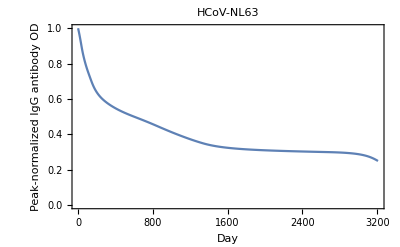

```mathematica
ListLinePlot[nl63antibodytimecourse, PlotRange->{0, 1}, PlotLabel->"HCoV-NL63", Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Peak-normalized IgG antibody OD"}]
```

```mathematica
Export["NL63-Antibody-Time-Course.csv", nl63antibodytimecourse]
```

NL63-Antibody-Time-Course.csv

```mathematica
Length[nl63antibodytimecourse]
```

3208

```mathematica
Take[nl63antibodytimecourse,-1]
```

{0.249691}

This estimate for the baseline S IgG antibody level for HCoV-OC43 of 0.249691 goes into the the ancestral and descendent states analysis of the baselines for the zoonotic coronaviruses.

```mathematica
nl63lsfunc=Sum[(nl63antibodytimecourse[[index]]-(baseline+(1-baseline)*Exp[-lambda*index]))^2, {index, 1, Length[nl63antibodytimecourse]}]
```

(0.249691-baseline-(1-baseline) ⅇ^(-3208 lambda))^2+(0.250008-baseline-(1-baseline) ⅇ^(-3207 lambda))^2+3205+(1-baseline-(1-baseline) ⅇ^-lambda)^2
 |  |  |  |

```mathematica
FindMinimum[{nl63lsfunc,0<baseline≤0.24969097900264375, lambda >0},{ {baseline, 0.249}, {lambda, 0.005}}]
```

{8.20776,{baseline→0.249691,lambda→0.0017924}}

This estimate of lambda for HCoV-NL63 of .0017924 goes into the the ancestral and descendent states analysis for the values of a and b for the zoonotic coronaviruses.

```mathematica
nl63halflife=Log[2]/ lambda /.lambda->0.0017923992943053057
```

386.715

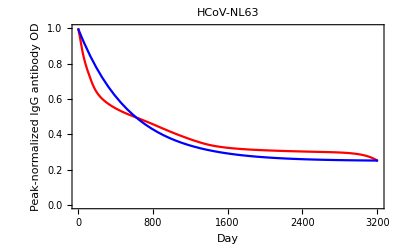

```mathematica
Show[
ListLinePlot[nl63antibodytimecourse,
PlotStyle->Red,
 PlotRange-> {0,1}
],
Plot[baseline+(1-baseline)*Exp[-lambda days]/.{baseline->0.249691,lambda->0.0017923992943053057},{days,1,3208}, 
PlotStyle->Blue,
PlotRange->{0,1}],
PlotLabel->"HCoV-NL63",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized IgG antibody OD"}]
```

```mathematica
nl63antibodytimecourseplusexp=nl63antibodytimecourse;
day=Length[nl63antibodytimecourse];
While[day<4393,
Increment[day];
AppendTo[nl63antibodytimecourseplusexp, 0.249691+(nl63antibodytimecourseplusexp[[day-1]]- 0.249691)*Exp[-0.0017923992943053057]]
]
```

```mathematica
nl63antibodytimecourseplusexp
```

{1,0.997586,0.995158,0.992714,0.990254,0.987776,0.985278,0.982759,0.980218,0.977655,0.975068,0.972456,0.969819,0.967155,0.964465,0.961749,0.959005,0.956234,0.953436,0.950611,0.94776,0.944887,0.941993,0.93908,0.936148,0.9332,0.930236,0.927257,0.924267,0.921266,0.918256,0.915239,0.912219,0.909196,0.906174,0.903155,0.900141,0.897137,0.894157,0.891206,0.888285,0.885396,0.882541,0.879722,0.876939,0.874192,0.871484,0.868813,0.866181,0.863587,0.861031,0.858513,0.856032,0.853588,0.851181,0.848809,0.846468,0.844153,0.841864,0.8396,0.837361,0.835145,0.832954,0.830785,0.828638,0.826513,0.82441,0.822328,0.820266,0.818224,0.816202,0.814199,0.812214,0.810249,0.808301,0.80637,0.804457,0.802561,0.800681,0.798817,0.79697,0.79514,0.793325,0.791527,0.789744,0.787976,0.786222,0.784484,0.782759,0.781048,0.779351,0.777667,0.775996,0.774337,0.77269,0.771056,0.769433,0.767821,0.76622,0.76463,0.76305,0.76148,0.75992,0.75837,0.756828,0.755296,0.753772,0.752256,0.750749,0.749249,0.747754,0.746263,0.744774,0.743288,0.741805,0.740324,0.738845,0.737368,0.735893,0.73442,0.732949,0.73148,0.730012,0.728546,0.727081,0.725618,0.724157,0.722698,0.72124,0.719784,0.718331,0.716879,0.71543,0.713983,0.712539,0.711097,0.709659,0.708223,0.706791,0.705362,0.703937,0.702517,0.7011,0.699689,0.698283,0.696889,0.695505,0.694132,0.692771,0.691421,0.690083,0.688757,0.687443,0.68614,0.68485,0.683572,0.682306,0.681053,0.679812,0.678583,0.677366,0.676162,0.67497,0.67379,0.672623,0.671467,0.670324,0.669193,0.668074,0.666967,0.665872,0.664788,0.663716,0.662656,0.661607,0.66057,0.659544,0.658529,0.657525,0.656532,0.65555,0.654578,0.653617,0.652667,0.651726,0.650796,0.649876,0.648966,0.648064,0.647171,0.646286,0.645409,0.644541,0.643681,0.642829,0.641985,0.641149,0.64032,0.639499,0.638686,0.637879,0.637081,0.636289,0.635505,0.634727,0.633957,0.633193,0.632436,0.631686,0.630943,0.630206,0.629475,0.628751,0.628032,0.62732,0.626615,0.625915,0.625221,0.624533,0.62385,0.623173,0.622502,0.621837,0.621177,0.620522,0.619873,0.619228,0.61859,0.617956,0.617327,0.616703,0.616084,0.61547,0.614861,0.614256,0.613656,0.613061,0.61247,0.611884,0.611302,0.610724,0.610151,0.609582,0.609017,0.608456,0.607899,0.607347,0.606798,0.606253,0.605713,0.605175,0.604642,0.604113,0.603587,0.603064,0.602546,0.60203,0.601519,0.60101,0.600505,0.600004,0.599506,0.59901,0.598517,0.598028,0.597541,0.597056,0.596574,0.596095,0.595619,0.595145,0.594674,0.594205,0.593738,0.593274,0.592813,0.592354,0.591897,0.591442,0.59099,0.59054,0.590093,0.589647,0.589204,0.588763,0.588324,0.587887,0.587452,0.587019,0.586589,0.58616,0.585733,0.585309,0.584886,0.584465,0.584046,0.583629,0.583214,0.582801,0.582389,0.581979,0.581572,0.581165,0.580761,0.580358,0.579957,0.579558,0.57916,0.578764,0.57837,0.577977,0.577586,0.577197,0.576809,0.576422,0.576037,0.575654,0.575272,0.574892,0.574513,0.574135,0.573759,0.573385,0.573012,0.57264,0.572269,0.5719,0.571533,0.571167,0.570802,0.570438,0.570076,0.569715,0.569355,0.568996,0.568639,0.568283,0.567928,0.567575,0.567222,0.566871,0.566521,0.566173,0.565825,0.565479,0.565133,0.564789,0.564446,0.564104,0.563764,0.563424,0.563085,0.562748,0.562411,0.562076,0.561742,0.561408,0.561076,0.560745,0.560414,0.560085,0.559757,0.55943,0.559103,0.558778,0.558454,0.55813,0.557808,0.557486,0.557166,0.556846,0.556527,0.556209,0.555892,0.555576,0.555261,0.554947,0.554634,0.554321,0.554009,0.553699,0.553389,0.553079,0.552771,0.552464,0.552157,0.551851,0.551546,0.551242,0.550938,0.550636,0.550334,0.550033,0.549732,0.549433,0.549134,0.548836,0.54854,0.548244,0.547949,0.547654,0.547361,0.547068,0.546777,0.546486,0.546196,0.545906,0.545618,0.54533,0.545044,0.544758,0.544472,0.544188,0.543904,0.543621,0.543339,0.543058,0.542777,0.542497,0.542218,0.54194,0.541662,0.541385,0.541109,0.540834,0.540559,0.540285,0.540011,0.539739,0.539467,0.539196,0.538925,0.538655,0.538386,0.538117,0.537849,0.537582,0.537316,0.53705,0.536785,0.53652,0.536256,0.535993,0.53573,0.535468,0.535206,0.534945,0.534685,0.534426,0.534167,0.533908,0.53365,0.533393,0.533136,0.53288,0.532625,0.53237,0.532115,0.531862,0.531608,0.531356,0.531103,0.530852,0.530601,0.53035,0.5301,0.529851,0.529602,0.529354,0.529106,0.528858,0.528612,0.528365,0.52812,0.527874,0.527629,0.527385,0.527141,0.526898,0.526655,0.526413,0.526171,0.525929,0.525689,0.525448,0.525208,0.524968,0.524729,0.524491,0.524253,0.524015,0.523778,0.523541,0.523304,0.523068,0.522833,0.522598,0.522363,0.522129,0.521895,0.521661,0.521428,0.521195,0.520963,0.520731,0.5205,0.520269,0.520038,0.519808,0.519578,0.519349,0.51912,0.518891,0.518662,0.518434,0.518207,0.51798,0.517753,0.517526,0.5173,0.517074,0.516849,0.516624,0.516399,0.516174,0.51595,0.515726,0.515503,0.51528,0.515057,0.514835,0.514613,0.514391,0.514169,0.513948,0.513727,0.513507,0.513286,0.513066,0.512847,0.512627,0.512408,0.51219,0.511971,0.511753,0.511535,0.511318,0.5111,0.510883,0.510666,0.51045,0.510234,0.510018,0.509802,0.509587,0.509372,0.509157,0.508942,0.508728,0.508513,0.5083,0.508086,0.507872,0.507659,0.507446,0.507234,0.507021,0.506809,0.506597,0.506385,0.506174,0.505962,0.505751,0.50554,0.50533,0.505119,0.504909,0.504699,0.504489,0.50428,0.50407,0.503861,0.503652,0.503443,0.503234,0.503026,0.502818,0.50261,0.502402,0.502194,0.501987,0.501779,0.501572,0.501365,0.501158,0.500952,0.500745,0.500539,0.500333,0.500127,0.499921,0.499715,0.499509,0.499304,0.499098,0.498893,0.498687,0.498481,0.498276,0.49807,0.497865,0.497659,0.497454,0.497248,0.497043,0.496837,0.496632,0.496426,0.496221,0.496016,0.49581,0.495605,0.495399,0.495194,0.494988,0.494783,0.494577,0.494372,0.494166,0.49396,0.493755,0.493549,0.493344,0.493138,0.492932,0.492727,0.492521,0.492315,0.492109,0.491903,0.491697,0.491492,0.491286,0.49108,0.490874,0.490667,0.490461,0.490255,0.490049,0.489843,0.489636,0.48943,0.489224,0.489017,0.488811,0.488604,0.488397,0.488191,0.487984,0.487777,0.48757,0.487363,0.487156,0.486949,0.486742,0.486534,0.486327,0.48612,0.485912,0.485705,0.485497,0.485289,0.485081,0.484873,0.484666,0.484457,0.484249,0.484041,0.483833,0.483624,0.483416,0.483207,0.482999,0.48279,0.482581,0.482372,0.482163,0.481954,0.481745,0.481535,0.481326,0.481116,0.480906,0.480697,0.480487,0.480277,0.480067,0.479857,0.479646,0.479436,0.479225,0.479015,0.478804,0.478593,0.478382,0.478171,0.47796,0.477748,0.477537,0.477325,0.477114,0.476902,0.47669,0.476478,0.476266,0.476053,0.475841,0.475628,0.475416,0.475203,0.47499,0.474777,0.474564,0.47435,0.474137,0.473923,0.473709,0.473496,0.473282,0.473068,0.472853,0.472639,0.472424,0.47221,0.471995,0.47178,0.471565,0.47135,0.471134,0.470919,0.470703,0.470487,0.470271,0.470055,0.469839,0.469623,0.469406,0.469189,0.468973,0.468756,0.468539,0.468321,0.468104,0.467886,0.467669,0.467451,0.467233,0.467015,0.466797,0.466578,0.46636,0.466141,0.465922,0.465703,0.465484,0.465265,0.465045,0.464826,0.464606,0.464386,0.464166,0.463946,0.463725,0.463505,0.463284,0.463063,0.462842,0.462621,0.4624,0.462179,0.461957,0.461735,0.461513,0.461291,0.461069,0.460847,0.460625,0.460402,0.460179,0.459956,0.459733,0.45951,0.459287,0.459063,0.458839,0.458616,0.458392,0.458168,0.457943,0.457719,0.457494,0.45727,0.457045,0.45682,0.456595,0.456369,0.456144,0.455918,0.455693,0.455467,0.455241,0.455015,0.454788,0.454562,0.454335,0.454109,0.453882,0.453655,0.453428,0.453201,0.452973,0.452746,0.452518,0.45229,0.452062,0.451834,0.451606,0.451378,0.451149,0.45092,0.450692,0.450463,0.450234,0.450005,0.449776,0.449546,0.449317,0.449088,0.448859,0.44863,0.4484,0.448171,0.447942,0.447713,0.447484,0.447255,0.447026,0.446797,0.446568,0.446339,0.44611,0.445881,0.445653,0.445424,0.445195,0.444966,0.444738,0.444509,0.44428,0.444052,0.443823,0.443595,0.443366,0.443138,0.44291,0.442681,0.442453,0.442225,0.441997,0.441768,0.44154,0.441312,0.441084,0.440856,0.440628,0.440401,0.440173,0.439945,0.439717,0.43949,0.439262,0.439035,0.438807,0.43858,0.438353,0.438125,0.437898,0.437671,0.437444,0.437217,0.43699,0.436763,0.436536,0.436309,0.436083,0.435856,0.43563,0.435403,0.435177,0.434951,0.434724,0.434498,0.434272,0.434046,0.43382,0.433594,0.433369,0.433143,0.432917,0.432692,0.432466,0.432241,0.432016,0.43179,0.431565,0.43134,0.431115,0.430891,0.430666,0.430441,0.430217,0.429992,0.429768,0.429543,0.429319,0.429095,0.428871,0.428647,0.428423,0.4282,0.427976,0.427752,0.427529,0.427306,0.427082,0.426859,0.426636,0.426413,0.426191,0.425968,0.425745,0.425523,0.4253,0.425078,0.424856,0.424634,0.424412,0.42419,0.423968,0.423747,0.423525,0.423304,0.423083,0.422861,0.42264,0.422419,0.422199,0.421978,0.421757,0.421537,0.421317,0.421096,0.420876,0.420656,0.420436,0.420217,0.419997,0.419778,0.419558,0.419339,0.41912,0.418901,0.418682,0.418463,0.418245,0.418026,0.417808,0.41759,0.417371,0.417153,0.416936,0.416718,0.4165,0.416283,0.416066,0.415848,0.415631,0.415415,0.415198,0.414981,0.414765,0.414548,0.414332,0.414116,0.4139,0.413684,0.413469,0.413253,0.413038,0.412823,0.412608,0.412393,0.412178,0.411963,0.411749,0.411534,0.41132,0.411106,0.410892,0.410678,0.410465,0.410251,0.410038,0.409825,0.409612,0.409399,0.409186,0.408974,0.408761,0.408549,0.408337,0.408125,0.407913,0.407701,0.40749,0.407279,0.407067,0.406856,0.406646,0.406435,0.406224,0.406014,0.405804,0.405594,0.405384,0.405174,0.404964,0.404755,0.404545,0.404336,0.404127,0.403919,0.40371,0.403501,0.403293,0.403085,0.402877,0.402669,0.402462,0.402254,0.402047,0.40184,0.401633,0.401426,0.401219,0.401013,0.400806,0.4006,0.400394,0.400188,0.399983,0.399777,0.399572,0.399367,0.399162,0.398957,0.398752,0.398547,0.398342,0.398138,0.397933,0.397729,0.397525,0.397321,0.397117,0.396913,0.396709,0.396506,0.396302,0.396099,0.395896,0.395693,0.39549,0.395287,0.395085,0.394882,0.39468,0.394477,0.394275,0.394073,0.393871,0.393669,0.393468,0.393266,0.393065,0.392864,0.392663,0.392462,0.392261,0.39206,0.39186,0.391659,0.391459,0.391259,0.391059,0.390859,0.390659,0.390459,0.39026,0.390061,0.389862,0.389662,0.389464,0.389265,0.389066,0.388868,0.388669,0.388471,0.388273,0.388075,0.387878,0.38768,0.387483,0.387285,0.387088,0.386891,0.386694,0.386498,0.386301,0.386105,0.385908,0.385712,0.385516,0.385321,0.385125,0.384929,0.384734,0.384539,0.384344,0.384149,0.383954,0.38376,0.383566,0.383371,0.383177,0.382983,0.38279,0.382596,0.382403,0.382209,0.382016,0.381823,0.381631,0.381438,0.381246,0.381053,0.380861,0.380669,0.380478,0.380286,0.380095,0.379903,0.379712,0.379522,0.379331,0.37914,0.37895,0.37876,0.37857,0.37838,0.37819,0.378001,0.377811,0.377622,0.377433,0.377244,0.377056,0.376867,0.376679,0.376491,0.376303,0.376116,0.375928,0.375741,0.375554,0.375367,0.37518,0.374993,0.374807,0.374621,0.374435,0.374249,0.374063,0.373878,0.373692,0.373507,0.373323,0.373138,0.372953,0.372769,0.372585,0.372401,0.372217,0.372034,0.371851,0.371667,0.371485,0.371302,0.371119,0.370937,0.370755,0.370573,0.370391,0.37021,0.370028,0.369847,0.369666,0.369486,0.369305,0.369125,0.368945,0.368765,0.368585,0.368406,0.368227,0.368048,0.367869,0.36769,0.367512,0.367334,0.367156,0.366978,0.366801,0.366623,0.366446,0.366269,0.366093,0.365916,0.36574,0.365564,0.365388,0.365212,0.365037,0.364862,0.364687,0.364512,0.364338,0.364164,0.36399,0.363816,0.363642,0.363469,0.363296,0.363123,0.36295,0.362778,0.362606,0.362434,0.362262,0.36209,0.361919,0.361748,0.361577,0.361407,0.361236,0.361066,0.360896,0.360727,0.360557,0.360388,0.360219,0.36005,0.359882,0.359714,0.359546,0.359378,0.35921,0.359043,0.358876,0.358709,0.358543,0.358376,0.35821,0.358044,0.357879,0.357713,0.357548,0.357383,0.357219,0.357054,0.35689,0.356726,0.356563,0.356399,0.356236,0.356073,0.355911,0.355748,0.355586,0.355424,0.355263,0.355101,0.35494,0.354779,0.354619,0.354458,0.354298,0.354138,0.353979,0.353819,0.35366,0.353501,0.353343,0.353184,0.353026,0.352869,0.352711,0.352554,0.352397,0.35224,0.352083,0.351927,0.351771,0.351615,0.35146,0.351305,0.35115,0.350995,0.350841,0.350686,0.350533,0.350379,0.350226,0.350072,0.34992,0.349767,0.349615,0.349464,0.349313,0.349163,0.349014,0.348865,0.348716,0.348568,0.348421,0.348274,0.348128,0.347982,0.347837,0.347692,0.347548,0.347405,0.347262,0.347119,0.346977,0.346836,0.346695,0.346555,0.346415,0.346276,0.346137,0.345999,0.345861,0.345724,0.345588,0.345452,0.345316,0.345181,0.345047,0.344913,0.344779,0.344646,0.344514,0.344382,0.34425,0.344119,0.343989,0.343859,0.34373,0.343601,0.343472,0.343344,0.343217,0.34309,0.342963,0.342837,0.342712,0.342587,0.342462,0.342338,0.342215,0.342092,0.341969,0.341847,0.341725,0.341604,0.341483,0.341363,0.341243,0.341124,0.341005,0.340886,0.340768,0.340651,0.340534,0.340417,0.340301,0.340185,0.34007,0.339955,0.339841,0.339727,0.339613,0.3395,0.339388,0.339275,0.339164,0.339052,0.338941,0.338831,0.338721,0.338611,0.338502,0.338393,0.338285,0.338177,0.338069,0.337962,0.337855,0.337749,0.337643,0.337538,0.337432,0.337328,0.337223,0.337119,0.337016,0.336913,0.33681,0.336708,0.336606,0.336504,0.336403,0.336302,0.336202,0.336102,0.336002,0.335903,0.335804,0.335705,0.335607,0.335509,0.335412,0.335315,0.335218,0.335122,0.335026,0.33493,0.334835,0.33474,0.334646,0.334551,0.334458,0.334364,0.334271,0.334178,0.334086,0.333994,0.333902,0.333811,0.33372,0.333629,0.333538,0.333448,0.333359,0.333269,0.33318,0.333092,0.333003,0.332915,0.332827,0.33274,0.332653,0.332566,0.33248,0.332393,0.332308,0.332222,0.332137,0.332052,0.331967,0.331883,0.331799,0.331716,0.331632,0.331549,0.331466,0.331384,0.331302,0.33122,0.331139,0.331057,0.330976,0.330896,0.330815,0.330735,0.330655,0.330576,0.330497,0.330418,0.330339,0.330261,0.330183,0.330105,0.330027,0.32995,0.329873,0.329796,0.32972,0.329644,0.329568,0.329492,0.329417,0.329342,0.329267,0.329192,0.329118,0.329044,0.32897,0.328896,0.328823,0.32875,0.328677,0.328605,0.328533,0.328461,0.328389,0.328317,0.328246,0.328175,0.328104,0.328034,0.327964,0.327894,0.327824,0.327754,0.327685,0.327616,0.327547,0.327478,0.32741,0.327342,0.327274,0.327206,0.327139,0.327072,0.327005,0.326938,0.326871,0.326805,0.326739,0.326673,0.326608,0.326542,0.326477,0.326412,0.326347,0.326283,0.326218,0.326154,0.32609,0.326027,0.325963,0.3259,0.325837,0.325774,0.325711,0.325649,0.325587,0.325525,0.325463,0.325401,0.32534,0.325279,0.325218,0.325157,0.325096,0.325036,0.324976,0.324916,0.324856,0.324796,0.324737,0.324678,0.324619,0.32456,0.324501,0.324443,0.324384,0.324326,0.324268,0.324211,0.324153,0.324096,0.324038,0.323981,0.323925,0.323868,0.323812,0.323755,0.323699,0.323643,0.323588,0.323532,0.323477,0.323421,0.323366,0.323311,0.323257,0.323202,0.323148,0.323094,0.32304,0.322986,0.322932,0.322879,0.322825,0.322772,0.322719,0.322666,0.322613,0.322561,0.322509,0.322456,0.322404,0.322352,0.322301,0.322249,0.322198,0.322146,0.322095,0.322044,0.321994,0.321943,0.321892,0.321842,0.321792,0.321742,0.321692,0.321642,0.321593,0.321543,0.321494,0.321445,0.321396,0.321347,0.321298,0.32125,0.321201,0.321153,0.321105,0.321057,0.321009,0.320961,0.320914,0.320866,0.320819,0.320772,0.320725,0.320678,0.320631,0.320584,0.320538,0.320492,0.320445,0.320399,0.320353,0.320308,0.320262,0.320216,0.320171,0.320126,0.32008,0.320035,0.319991,0.319946,0.319901,0.319857,0.319812,0.319768,0.319724,0.31968,0.319636,0.319592,0.319548,0.319505,0.319462,0.319418,0.319375,0.319332,0.319289,0.319246,0.319204,0.319161,0.319119,0.319076,0.319034,0.318992,0.31895,0.318908,0.318866,0.318825,0.318783,0.318742,0.318701,0.318659,0.318618,0.318577,0.318536,0.318496,0.318455,0.318415,0.318374,0.318334,0.318294,0.318254,0.318214,0.318174,0.318134,0.318094,0.318055,0.318015,0.317976,0.317937,0.317898,0.317859,0.31782,0.317781,0.317742,0.317703,0.317665,0.317626,0.317588,0.31755,0.317512,0.317474,0.317436,0.317398,0.31736,0.317323,0.317285,0.317248,0.31721,0.317173,0.317136,0.317099,0.317062,0.317025,0.316988,0.316952,0.316915,0.316879,0.316842,0.316806,0.31677,0.316734,0.316698,0.316662,0.316626,0.31659,0.316554,0.316519,0.316483,0.316448,0.316412,0.316377,0.316342,0.316307,0.316272,0.316237,0.316202,0.316168,0.316133,0.316099,0.316064,0.31603,0.315995,0.315961,0.315927,0.315893,0.315859,0.315825,0.315791,0.315758,0.315724,0.315691,0.315657,0.315624,0.31559,0.315557,0.315524,0.315491,0.315458,0.315425,0.315392,0.31536,0.315327,0.315294,0.315262,0.315229,0.315197,0.315165,0.315132,0.3151,0.315068,0.315036,0.315004,0.314972,0.314941,0.314909,0.314877,0.314846,0.314814,0.314783,0.314752,0.31472,0.314689,0.314658,0.314627,0.314596,0.314565,0.314534,0.314504,0.314473,0.314442,0.314412,0.314381,0.314351,0.31432,0.31429,0.31426,0.31423,0.3142,0.31417,0.31414,0.31411,0.31408,0.31405,0.314021,0.313991,0.313961,0.313932,0.313903,0.313873,0.313844,0.313815,0.313786,0.313756,0.313727,0.313698,0.31367,0.313641,0.313612,0.313583,0.313555,0.313526,0.313497,0.313469,0.313441,0.313412,0.313384,0.313356,0.313328,0.313299,0.313271,0.313243,0.313215,0.313188,0.31316,0.313132,0.313104,0.313077,0.313049,0.313022,0.312994,0.312967,0.312939,0.312912,0.312885,0.312858,0.312831,0.312804,0.312777,0.31275,0.312723,0.312696,0.312669,0.312642,0.312616,0.312589,0.312562,0.312536,0.31251,0.312483,0.312457,0.31243,0.312404,0.312378,0.312352,0.312326,0.3123,0.312274,0.312248,0.312222,0.312196,0.31217,0.312145,0.312119,0.312093,0.312068,0.312042,0.312017,0.311991,0.311966,0.311941,0.311915,0.31189,0.311865,0.31184,0.311815,0.31179,0.311765,0.31174,0.311715,0.31169,0.311665,0.311641,0.311616,0.311591,0.311567,0.311542,0.311518,0.311493,0.311469,0.311444,0.31142,0.311396,0.311372,0.311347,0.311323,0.311299,0.311275,0.311251,0.311227,0.311203,0.311179,0.311156,0.311132,0.311108,0.311084,0.311061,0.311037,0.311014,0.31099,0.310967,0.310943,0.31092,0.310896,0.310873,0.31085,0.310827,0.310803,0.31078,0.310757,0.310734,0.310711,0.310688,0.310665,0.310642,0.31062,0.310597,0.310574,0.310551,0.310529,0.310506,0.310483,0.310461,0.310438,0.310416,0.310393,0.310371,0.310349,0.310326,0.310304,0.310282,0.31026,0.310237,0.310215,0.310193,0.310171,0.310149,0.310127,0.310105,0.310083,0.310061,0.31004,0.310018,0.309996,0.309974,0.309953,0.309931,0.309909,0.309888,0.309866,0.309845,0.309823,0.309802,0.309781,0.309759,0.309738,0.309717,0.309695,0.309674,0.309653,0.309632,0.309611,0.30959,0.309569,0.309548,0.309527,0.309506,0.309485,0.309464,0.309443,0.309422,0.309402,0.309381,0.30936,0.30934,0.309319,0.309298,0.309278,0.309257,0.309237,0.309216,0.309196,0.309175,0.309155,0.309135,0.309114,0.309094,0.309074,0.309054,0.309034,0.309013,0.308993,0.308973,0.308953,0.308933,0.308913,0.308893,0.308873,0.308853,0.308834,0.308814,0.308794,0.308774,0.308754,0.308735,0.308715,0.308695,0.308676,0.308656,0.308637,0.308617,0.308598,0.308578,0.308559,0.308539,0.30852,0.308501,0.308481,0.308462,0.308443,0.308423,0.308404,0.308385,0.308366,0.308347,0.308328,0.308309,0.30829,0.308271,0.308252,0.308233,0.308214,0.308195,0.308176,0.308157,0.308138,0.308119,0.308101,0.308082,0.308063,0.308044,0.308026,0.308007,0.307989,0.30797,0.307951,0.307933,0.307914,0.307896,0.307878,0.307859,0.307841,0.307822,0.307804,0.307786,0.307767,0.307749,0.307731,0.307713,0.307694,0.307676,0.307658,0.30764,0.307622,0.307604,0.307586,0.307568,0.30755,0.307532,0.307514,0.307496,0.307478,0.30746,0.307442,0.307424,0.307407,0.307389,0.307371,0.307353,0.307336,0.307318,0.3073,0.307283,0.307265,0.307248,0.30723,0.307212,0.307195,0.307177,0.30716,0.307142,0.307125,0.307108,0.30709,0.307073,0.307056,0.307038,0.307021,0.307004,0.306986,0.306969,0.306952,0.306935,0.306918,0.3069,0.306883,0.306866,0.306849,0.306832,0.306815,0.306798,0.306781,0.306764,0.306747,0.30673,0.306713,0.306696,0.30668,0.306663,0.306646,0.306629,0.306612,0.306596,0.306579,0.306562,0.306545,0.306529,0.306512,0.306495,0.306479,0.306462,0.306446,0.306429,0.306412,0.306396,0.306379,0.306363,0.306346,0.30633,0.306314,0.306297,0.306281,0.306264,0.306248,0.306232,0.306215,0.306199,0.306183,0.306167,0.30615,0.306134,0.306118,0.306102,0.306086,0.30607,0.306053,0.306037,0.306021,0.306005,0.305989,0.305973,0.305957,0.305941,0.305925,0.305909,0.305893,0.305877,0.305861,0.305845,0.30583,0.305814,0.305798,0.305782,0.305766,0.30575,0.305735,0.305719,0.305703,0.305687,0.305672,0.305656,0.30564,0.305625,0.305609,0.305593,0.305578,0.305562,0.305547,0.305531,0.305516,0.3055,0.305485,0.305469,0.305454,0.305438,0.305423,0.305407,0.305392,0.305377,0.305361,0.305346,0.30533,0.305315,0.3053,0.305284,0.305269,0.305254,0.305239,0.305223,0.305208,0.305193,0.305178,0.305163,0.305148,0.305132,0.305117,0.305102,0.305087,0.305072,0.305057,0.305042,0.305027,0.305012,0.304997,0.304982,0.304967,0.304952,0.304937,0.304922,0.304907,0.304892,0.304877,0.304862,0.304847,0.304833,0.304818,0.304803,0.304788,0.304773,0.304759,0.304744,0.304729,0.304714,0.3047,0.304685,0.30467,0.304655,0.304641,0.304626,0.304611,0.304597,0.304582,0.304568,0.304553,0.304538,0.304524,0.304509,0.304495,0.30448,0.304466,0.304451,0.304437,0.304422,0.304408,0.304393,0.304379,0.304364,0.30435,0.304336,0.304321,0.304307,0.304292,0.304278,0.304264,0.304249,0.304235,0.304221,0.304207,0.304192,0.304178,0.304164,0.304149,0.304135,0.304121,0.304107,0.304093,0.304078,0.304064,0.30405,0.304036,0.304022,0.304008,0.303994,0.303979,0.303965,0.303951,0.303937,0.303923,0.303909,0.303895,0.303881,0.303867,0.303853,0.303839,0.303825,0.303811,0.303797,0.303783,0.303769,0.303755,0.303741,0.303728,0.303714,0.3037,0.303686,0.303672,0.303658,0.303644,0.30363,0.303617,0.303603,0.303589,0.303575,0.303561,0.303548,0.303534,0.30352,0.303506,0.303493,0.303479,0.303465,0.303452,0.303438,0.303424,0.303411,0.303397,0.303383,0.30337,0.303356,0.303342,0.303329,0.303315,0.303302,0.303288,0.303274,0.303261,0.303247,0.303234,0.30322,0.303207,0.303193,0.30318,0.303166,0.303153,0.303139,0.303126,0.303112,0.303099,0.303085,0.303072,0.303059,0.303045,0.303032,0.303018,0.303005,0.302992,0.302978,0.302965,0.302951,0.302938,0.302925,0.302911,0.302898,0.302885,0.302871,0.302858,0.302845,0.302832,0.302818,0.302805,0.302792,0.302779,0.302765,0.302752,0.302739,0.302726,0.302712,0.302699,0.302686,0.302673,0.30266,0.302647,0.302633,0.30262,0.302607,0.302594,0.302581,0.302568,0.302555,0.302541,0.302528,0.302515,0.302502,0.302489,0.302476,0.302463,0.30245,0.302437,0.302424,0.302411,0.302398,0.302385,0.302372,0.302359,0.302346,0.302333,0.30232,0.302307,0.302294,0.302281,0.302268,0.302255,0.302242,0.302229,0.302216,0.302203,0.30219,0.302177,0.302164,0.302152,0.302139,0.302126,0.302113,0.3021,0.302087,0.302074,0.302061,0.302049,0.302036,0.302023,0.30201,0.301997,0.301985,0.301972,0.301959,0.301946,0.301933,0.301921,0.301908,0.301895,0.301882,0.301869,0.301857,0.301844,0.301831,0.301818,0.301806,0.301793,0.30178,0.301768,0.301755,0.301742,0.301729,0.301717,0.301704,0.301691,0.301679,0.301666,0.301653,0.301641,0.301628,0.301615,0.301603,0.30159,0.301578,0.301565,0.301552,0.30154,0.301527,0.301514,0.301502,0.301489,0.301477,0.301464,0.301451,0.301439,0.301426,0.301414,0.301401,0.301389,0.301376,0.301364,0.301351,0.301338,0.301326,0.301313,0.301301,0.301288,0.301276,0.301263,0.301251,0.301238,0.301226,0.301213,0.301201,0.301188,0.301176,0.301163,0.301151,0.301138,0.301126,0.301114,0.301101,0.301089,0.301076,0.301064,0.301051,0.301039,0.301026,0.301014,0.301002,0.300989,0.300977,0.300964,0.300952,0.300939,0.300927,0.300915,0.300902,0.30089,0.300877,0.300865,0.300853,0.30084,0.300828,0.300816,0.300803,0.300791,0.300779,0.300766,0.300754,0.300741,0.300729,0.300717,0.300704,0.300692,0.30068,0.300667,0.300655,0.300643,0.30063,0.300618,0.300606,0.300594,0.300581,0.300569,0.300557,0.300544,0.300532,0.30052,0.300507,0.300495,0.300483,0.300471,0.300458,0.300446,0.300434,0.300421,0.300409,0.300397,0.300385,0.300372,0.30036,0.300348,0.300336,0.300323,0.300311,0.300299,0.300287,0.300274,0.300262,0.30025,0.300238,0.300225,0.300213,0.300201,0.300189,0.300176,0.300164,0.300152,0.30014,0.300128,0.300115,0.300103,0.300091,0.300079,0.300066,0.300054,0.300042,0.30003,0.300018,0.300005,0.299993,0.299981,0.299969,0.299956,0.299944,0.299931,0.299919,0.299906,0.299894,0.299881,0.299868,0.299855,0.299842,0.299829,0.299816,0.299803,0.29979,0.299776,0.299763,0.299749,0.299736,0.299722,0.299709,0.299695,0.299681,0.299667,0.299653,0.299639,0.299625,0.299611,0.299597,0.299583,0.299568,0.299554,0.299539,0.299525,0.29951,0.299495,0.29948,0.299465,0.29945,0.299435,0.29942,0.299405,0.299389,0.299374,0.299359,0.299343,0.299327,0.299312,0.299296,0.29928,0.299264,0.299248,0.299232,0.299215,0.299199,0.299183,0.299166,0.299149,0.299133,0.299116,0.299099,0.299082,0.299065,0.299048,0.299031,0.299013,0.298996,0.298978,0.298961,0.298943,0.298925,0.298907,0.298889,0.298871,0.298853,0.298835,0.298817,0.298798,0.298779,0.298761,0.298742,0.298723,0.298704,0.298685,0.298666,0.298647,0.298627,0.298608,0.298588,0.298568,0.298548,0.298528,0.298508,0.298488,0.298468,0.298448,0.298427,0.298407,0.298386,0.298365,0.298344,0.298323,0.298302,0.29828,0.298259,0.298238,0.298216,0.298194,0.298172,0.29815,0.298128,0.298106,0.298084,0.298061,0.298038,0.298016,0.297993,0.29797,0.297947,0.297923,0.2979,0.297877,0.297853,0.297829,0.297805,0.297781,0.297757,0.297733,0.297708,0.297684,0.297659,0.297634,0.297609,0.297584,0.297559,0.297533,0.297508,0.297482,0.297456,0.29743,0.297404,0.297378,0.297351,0.297325,0.297298,0.297271,0.297244,0.297217,0.297189,0.297162,0.297134,0.297106,0.297078,0.29705,0.297022,0.296994,0.296965,0.296936,0.296907,0.296878,0.296849,0.296819,0.29679,0.29676,0.29673,0.2967,0.29667,0.296639,0.296608,0.296578,0.296547,0.296515,0.296484,0.296453,0.296421,0.296389,0.296357,0.296325,0.296292,0.296259,0.296227,0.296194,0.29616,0.296127,0.296093,0.296059,0.296025,0.295991,0.295957,0.295922,0.295887,0.295852,0.295817,0.295782,0.295746,0.29571,0.295674,0.295638,0.295601,0.295565,0.295528,0.295491,0.295453,0.295416,0.295378,0.29534,0.295302,0.295263,0.295224,0.295185,0.295146,0.295107,0.295067,0.295027,0.294987,0.294947,0.294906,0.294865,0.294824,0.294783,0.294741,0.2947,0.294657,0.294615,0.294573,0.29453,0.294487,0.294443,0.2944,0.294356,0.294312,0.294267,0.294222,0.294177,0.294132,0.294087,0.294041,0.293995,0.293948,0.293902,0.293855,0.293808,0.29376,0.293712,0.293664,0.293616,0.293567,0.293518,0.293469,0.293419,0.293369,0.293319,0.293268,0.293218,0.293166,0.293115,0.293063,0.293011,0.292958,0.292906,0.292853,0.292799,0.292745,0.292691,0.292637,0.292582,0.292527,0.292471,0.292416,0.292359,0.292303,0.292246,0.292189,0.292131,0.292073,0.292015,0.291956,0.291897,0.291837,0.291777,0.291717,0.291657,0.291596,0.291534,0.291472,0.29141,0.291348,0.291285,0.291221,0.291157,0.291093,0.291029,0.290963,0.290898,0.290832,0.290766,0.290699,0.290632,0.290564,0.290496,0.290428,0.290359,0.290289,0.290219,0.290149,0.290078,0.290007,0.289935,0.289863,0.289791,0.289717,0.289644,0.28957,0.289495,0.28942,0.289345,0.289268,0.289192,0.289115,0.289037,0.288959,0.28888,0.288801,0.288722,0.288641,0.288561,0.288479,0.288398,0.288315,0.288232,0.288149,0.288065,0.28798,0.287895,0.287809,0.287723,0.287636,0.287548,0.28746,0.287372,0.287282,0.287192,0.287102,0.287011,0.286919,0.286827,0.286734,0.28664,0.286546,0.286451,0.286355,0.286259,0.286162,0.286065,0.285967,0.285868,0.285768,0.285668,0.285567,0.285465,0.285363,0.28526,0.285156,0.285052,0.284947,0.284841,0.284734,0.284627,0.284519,0.28441,0.2843,0.28419,0.284078,0.283967,0.283854,0.28374,0.283626,0.283511,0.283395,0.283278,0.283161,0.283042,0.282923,0.282803,0.282682,0.282561,0.282438,0.282315,0.282191,0.282065,0.281939,0.281812,0.281685,0.281556,0.281426,0.281296,0.281164,0.281032,0.280899,0.280764,0.280629,0.280493,0.280356,0.280218,0.280079,0.279939,0.279798,0.279656,0.279513,0.279369,0.279224,0.279078,0.278931,0.278783,0.278633,0.278483,0.278332,0.278179,0.278026,0.277872,0.277716,0.277559,0.277401,0.277242,0.277082,0.276921,0.276759,0.276595,0.276431,0.276265,0.276098,0.27593,0.275761,0.27559,0.275419,0.275246,0.275072,0.274896,0.27472,0.274542,0.274363,0.274183,0.274001,0.273818,0.273634,0.273449,0.273262,0.273075,0.272885,0.272695,0.272503,0.27231,0.272115,0.27192,0.271723,0.271524,0.271324,0.271123,0.27092,0.270717,0.270511,0.270304,0.270096,0.269887,0.269676,0.269464,0.26925,0.269035,0.268818,0.2686,0.268381,0.26816,0.267937,0.267714,0.267488,0.267262,0.267033,0.266804,0.266573,0.26634,0.266106,0.26587,0.265633,0.265395,0.265155,0.264913,0.26467,0.264425,0.264179,0.263932,0.263683,0.263432,0.26318,0.262926,0.262671,0.262414,0.262156,0.261897,0.261635,0.261373,0.261108,0.260843,0.260576,0.260307,0.260037,0.259765,0.259492,0.259217,0.258941,0.258663,0.258384,0.258104,0.257821,0.257538,0.257253,0.256967,0.256679,0.25639,0.256099,0.255807,0.255514,0.255219,0.254923,0.254625,0.254326,0.254026,0.253724,0.253422,0.253117,0.252812,0.252505,0.252197,0.251888,0.251578,0.251266,0.250953,0.25064,0.250324,0.250008,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691,0.249691}

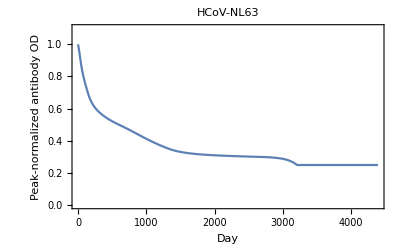

```mathematica
ListLinePlot[nl63antibodytimecourseplusexp,
PlotRange->{0, 1.1},
PlotLabel->"HCoV-NL63",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["HCoV-NL63_nOD-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[nl63antibodytimecourseplusexp,
PlotRange->{0, 1.1},
PlotLabel->"HCoV-NL63",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
]
```

HCoV-NL63_nOD-by-Day_21Jan2021.pdf

```mathematica
nl63probnoreinfectiontimecourse={1};
day=1;
AppendTo[nl63probnoreinfectiontimecourse, 
nl63probnoreinfectiontimecourse[[day]]*(1-nl63probinfgivenaod[nl63antibodytimecourse[[day+1]]])
];

While[day<4393,
Increment[day];
AppendTo[nl63probnoreinfectiontimecourse, 
If[day<lengthabtc,
nl63probnoreinfectiontimecourse[[day]]*(1-nl63probinfgivenaod[nl63antibodytimecourse[[day+1]] ]),
nl63probnoreinfectiontimecourse[[day]]*(1-nl63probinfgivenaod[nl63antibodytimecourse[[lengthabtc]]])
]
]
];

nl63probnoreinfectiontimecourse
```

{1,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999996,0.999996,0.999996,0.999996,0.999995,0.999995,0.999995,0.999995,0.999994,0.999994,0.999994,0.999993,0.999993,0.999993,0.999992,0.999992,0.999992,0.999991,0.999991,0.99999,0.99999,0.999989,0.999989,0.999988,0.999988,0.999987,0.999987,0.999986,0.999986,0.999985,0.999984,0.999984,0.999983,0.999982,0.999982,0.999981,0.99998,0.999979,0.999979,0.999978,0.999977,0.999976,0.999975,0.999974,0.999973,0.999972,0.999971,0.99997,0.999969,0.999968,0.999967,0.999966,0.999965,0.999964,0.999962,0.999961,0.99996,0.999959,0.999957,0.999956,0.999954,0.999953,0.999952,0.99995,0.999948,0.999947,0.999945,0.999944,0.999942,0.99994,0.999938,0.999937,0.999935,0.999933,0.999931,0.999929,0.999927,0.999925,0.999923,0.999921,0.999919,0.999916,0.999914,0.999912,0.99991,0.999907,0.999905,0.999902,0.9999,0.999897,0.999894,0.999892,0.999889,0.999886,0.999883,0.99988,0.999877,0.999874,0.999871,0.999868,0.999865,0.999861,0.999858,0.999854,0.999851,0.999847,0.999844,0.99984,0.999836,0.999832,0.999828,0.999824,0.99982,0.999816,0.999812,0.999807,0.999803,0.999798,0.999794,0.999789,0.999784,0.999779,0.999774,0.999769,0.999764,0.999759,0.999754,0.999748,0.999743,0.999737,0.999731,0.999726,0.99972,0.999714,0.999708,0.999701,0.999695,0.999689,0.999682,0.999676,0.999669,0.999662,0.999655,0.999648,0.999641,0.999634,0.999627,0.999619,0.999612,0.999604,0.999596,0.999589,0.999581,0.999573,0.999564,0.999556,0.999548,0.999539,0.999531,0.999522,0.999513,0.999505,0.999496,0.999486,0.999477,0.999468,0.999459,0.999449,0.999439,0.99943,0.99942,0.99941,0.9994,0.99939,0.999379,0.999369,0.999358,0.999348,0.999337,0.999326,0.999315,0.999304,0.999293,0.999282,0.99927,0.999259,0.999247,0.999236,0.999224,0.999212,0.9992,0.999188,0.999175,0.999163,0.99915,0.999138,0.999125,0.999112,0.999099,0.999086,0.999073,0.99906,0.999046,0.999033,0.999019,0.999005,0.998991,0.998977,0.998963,0.998949,0.998935,0.99892,0.998906,0.998891,0.998876,0.998861,0.998846,0.998831,0.998816,0.998801,0.998785,0.99877,0.998754,0.998738,0.998722,0.998706,0.99869,0.998674,0.998658,0.998641,0.998625,0.998608,0.998591,0.998574,0.998557,0.99854,0.998523,0.998505,0.998488,0.99847,0.998452,0.998434,0.998417,0.998398,0.99838,0.998362,0.998344,0.998325,0.998306,0.998288,0.998269,0.99825,0.998231,0.998211,0.998192,0.998172,0.998153,0.998133,0.998113,0.998093,0.998073,0.998053,0.998033,0.998012,0.997992,0.997971,0.99795,0.99793,0.997909,0.997887,0.997866,0.997845,0.997823,0.997802,0.99778,0.997758,0.997736,0.997714,0.997692,0.99767,0.997647,0.997625,0.997602,0.997579,0.997556,0.997533,0.99751,0.997487,0.997463,0.99744,0.997416,0.997392,0.997369,0.997345,0.99732,0.997296,0.997272,0.997247,0.997223,0.997198,0.997173,0.997148,0.997123,0.997098,0.997072,0.997047,0.997021,0.996995,0.99697,0.996944,0.996917,0.996891,0.996865,0.996838,0.996812,0.996785,0.996758,0.996731,0.996704,0.996677,0.996649,0.996622,0.996594,0.996566,0.996539,0.996511,0.996482,0.996454,0.996426,0.996397,0.996369,0.99634,0.996311,0.996282,0.996253,0.996223,0.996194,0.996164,0.996135,0.996105,0.996075,0.996045,0.996015,0.995984,0.995954,0.995923,0.995893,0.995862,0.995831,0.9958,0.995768,0.995737,0.995706,0.995674,0.995642,0.99561,0.995578,0.995546,0.995514,0.995481,0.995449,0.995416,0.995383,0.99535,0.995317,0.995284,0.99525,0.995217,0.995183,0.995149,0.995115,0.995081,0.995047,0.995013,0.994978,0.994944,0.994909,0.994874,0.994839,0.994804,0.994769,0.994733,0.994697,0.994662,0.994626,0.99459,0.994554,0.994518,0.994481,0.994445,0.994408,0.994371,0.994334,0.994297,0.99426,0.994223,0.994185,0.994147,0.99411,0.994072,0.994034,0.993995,0.993957,0.993919,0.99388,0.993841,0.993802,0.993763,0.993724,0.993685,0.993645,0.993606,0.993566,0.993526,0.993486,0.993446,0.993405,0.993365,0.993324,0.993284,0.993243,0.993202,0.99316,0.993119,0.993078,0.993036,0.992994,0.992952,0.99291,0.992868,0.992826,0.992783,0.992741,0.992698,0.992655,0.992612,0.992569,0.992525,0.992482,0.992438,0.992394,0.99235,0.992306,0.992262,0.992218,0.992173,0.992129,0.992084,0.992039,0.991994,0.991948,0.991903,0.991857,0.991812,0.991766,0.99172,0.991674,0.991627,0.991581,0.991534,0.991488,0.991441,0.991394,0.991346,0.991299,0.991252,0.991204,0.991156,0.991108,0.99106,0.991012,0.990963,0.990915,0.990866,0.990817,0.990768,0.990719,0.99067,0.99062,0.990571,0.990521,0.990471,0.990421,0.99037,0.99032,0.990269,0.990219,0.990168,0.990117,0.990066,0.990014,0.989963,0.989911,0.989859,0.989807,0.989755,0.989703,0.989651,0.989598,0.989545,0.989492,0.989439,0.989386,0.989333,0.989279,0.989225,0.989171,0.989117,0.989063,0.989009,0.988954,0.9889,0.988845,0.98879,0.988735,0.988679,0.988624,0.988568,0.988512,0.988457,0.9884,0.988344,0.988288,0.988231,0.988174,0.988117,0.98806,0.988003,0.987945,0.987888,0.98783,0.987772,0.987714,0.987656,0.987597,0.987539,0.98748,0.987421,0.987362,0.987303,0.987243,0.987184,0.987124,0.987064,0.987004,0.986943,0.986883,0.986822,0.986762,0.986701,0.986639,0.986578,0.986517,0.986455,0.986393,0.986331,0.986269,0.986207,0.986144,0.986081,0.986018,0.985955,0.985892,0.985829,0.985765,0.985701,0.985638,0.985573,0.985509,0.985445,0.98538,0.985315,0.98525,0.985185,0.98512,0.985054,0.984989,0.984923,0.984857,0.98479,0.984724,0.984657,0.98459,0.984523,0.984456,0.984389,0.984321,0.984254,0.984186,0.984118,0.984049,0.983981,0.983912,0.983843,0.983774,0.983705,0.983636,0.983566,0.983496,0.983426,0.983356,0.983286,0.983215,0.983144,0.983074,0.983002,0.982931,0.982859,0.982788,0.982716,0.982644,0.982571,0.982499,0.982426,0.982353,0.98228,0.982207,0.982133,0.982059,0.981986,0.981911,0.981837,0.981763,0.981688,0.981613,0.981538,0.981462,0.981387,0.981311,0.981235,0.981159,0.981082,0.981006,0.980929,0.980852,0.980775,0.980697,0.980619,0.980541,0.980463,0.980385,0.980306,0.980228,0.980149,0.98007,0.97999,0.97991,0.979831,0.97975,0.97967,0.97959,0.979509,0.979428,0.979347,0.979265,0.979184,0.979102,0.97902,0.978937,0.978855,0.978772,0.978689,0.978606,0.978522,0.978438,0.978355,0.97827,0.978186,0.978101,0.978016,0.977931,0.977846,0.97776,0.977674,0.977588,0.977502,0.977415,0.977329,0.977241,0.977154,0.977067,0.976979,0.976891,0.976803,0.976714,0.976625,0.976536,0.976447,0.976357,0.976268,0.976177,0.976087,0.975997,0.975906,0.975815,0.975723,0.975632,0.97554,0.975448,0.975355,0.975263,0.97517,0.975077,0.974983,0.97489,0.974796,0.974702,0.974607,0.974512,0.974417,0.974322,0.974226,0.974131,0.974034,0.973938,0.973841,0.973744,0.973647,0.97355,0.973452,0.973354,0.973255,0.973157,0.973058,0.972959,0.972859,0.972759,0.972659,0.972559,0.972458,0.972357,0.972256,0.972155,0.972053,0.971951,0.971848,0.971746,0.971643,0.971539,0.971436,0.971332,0.971228,0.971123,0.971019,0.970913,0.970808,0.970702,0.970596,0.97049,0.970383,0.970276,0.970169,0.970061,0.969954,0.969845,0.969737,0.969628,0.969519,0.969409,0.969299,0.969189,0.969079,0.968968,0.968857,0.968746,0.968634,0.968522,0.968409,0.968296,0.968183,0.96807,0.967956,0.967842,0.967728,0.967613,0.967498,0.967382,0.967266,0.96715,0.967034,0.966917,0.9668,0.966682,0.966564,0.966446,0.966328,0.966209,0.966089,0.96597,0.96585,0.965729,0.965609,0.965487,0.965366,0.965244,0.965122,0.964999,0.964877,0.964753,0.96463,0.964506,0.964381,0.964256,0.964131,0.964006,0.96388,0.963754,0.963627,0.9635,0.963372,0.963245,0.963116,0.962988,0.962859,0.96273,0.9626,0.96247,0.962339,0.962208,0.962077,0.961945,0.961813,0.961681,0.961548,0.961414,0.961281,0.961147,0.961012,0.960877,0.960742,0.960606,0.96047,0.960334,0.960197,0.96006,0.959922,0.959784,0.959645,0.959506,0.959367,0.959227,0.959087,0.958946,0.958805,0.958664,0.958522,0.958379,0.958237,0.958093,0.95795,0.957806,0.957661,0.957517,0.957371,0.957226,0.957079,0.956933,0.956786,0.956638,0.95649,0.956342,0.956193,0.956044,0.955894,0.955744,0.955594,0.955443,0.955291,0.95514,0.954987,0.954834,0.954681,0.954528,0.954373,0.954219,0.954064,0.953908,0.953752,0.953596,0.953439,0.953282,0.953124,0.952966,0.952807,0.952648,0.952489,0.952328,0.952168,0.952007,0.951845,0.951684,0.951521,0.951358,0.951195,0.951031,0.950867,0.950702,0.950537,0.950371,0.950205,0.950038,0.949871,0.949703,0.949535,0.949366,0.949197,0.949028,0.948858,0.948687,0.948516,0.948344,0.948172,0.948,0.947827,0.947653,0.947479,0.947305,0.94713,0.946954,0.946778,0.946601,0.946424,0.946247,0.946069,0.94589,0.945711,0.945532,0.945352,0.945171,0.94499,0.944808,0.944626,0.944444,0.94426,0.944077,0.943893,0.943708,0.943523,0.943337,0.943151,0.942964,0.942777,0.942589,0.9424,0.942212,0.942022,0.941832,0.941642,0.941451,0.941259,0.941067,0.940875,0.940681,0.940488,0.940294,0.940099,0.939904,0.939708,0.939511,0.939314,0.939117,0.938919,0.93872,0.938521,0.938322,0.938122,0.937921,0.93772,0.937518,0.937315,0.937112,0.936909,0.936705,0.9365,0.936295,0.936089,0.935883,0.935676,0.935469,0.935261,0.935053,0.934843,0.934634,0.934424,0.934213,0.934001,0.93379,0.933577,0.933364,0.93315,0.932936,0.932722,0.932506,0.93229,0.932074,0.931857,0.931639,0.931421,0.931202,0.930983,0.930763,0.930542,0.930321,0.930099,0.929877,0.929654,0.929431,0.929207,0.928982,0.928757,0.928531,0.928305,0.928078,0.92785,0.927622,0.927393,0.927164,0.926934,0.926703,0.926472,0.92624,0.926008,0.925775,0.925541,0.925307,0.925072,0.924837,0.924601,0.924364,0.924127,0.923889,0.923651,0.923412,0.923172,0.922932,0.922691,0.922449,0.922207,0.921965,0.921721,0.921477,0.921233,0.920988,0.920742,0.920495,0.920248,0.920001,0.919752,0.919504,0.919254,0.919004,0.918753,0.918502,0.91825,0.917997,0.917744,0.91749,0.917235,0.91698,0.916724,0.916468,0.91621,0.915953,0.915694,0.915435,0.915175,0.914915,0.914654,0.914393,0.91413,0.913867,0.913604,0.91334,0.913075,0.912809,0.912543,0.912276,0.912009,0.911741,0.911472,0.911203,0.910933,0.910662,0.910391,0.910119,0.909846,0.909573,0.909299,0.909024,0.908749,0.908473,0.908196,0.907919,0.907641,0.907362,0.907083,0.906803,0.906522,0.906241,0.905959,0.905676,0.905393,0.905109,0.904824,0.904539,0.904253,0.903966,0.903679,0.903391,0.903102,0.902812,0.902522,0.902232,0.90194,0.901648,0.901355,0.901062,0.900768,0.900473,0.900177,0.899881,0.899584,0.899286,0.898988,0.898689,0.89839,0.898089,0.897788,0.897486,0.897184,0.896881,0.896577,0.896273,0.895967,0.895662,0.895355,0.895048,0.89474,0.894431,0.894122,0.893812,0.893501,0.89319,0.892877,0.892565,0.892251,0.891937,0.891622,0.891306,0.89099,0.890673,0.890355,0.890037,0.889717,0.889398,0.889077,0.888756,0.888434,0.888111,0.887788,0.887464,0.887139,0.886813,0.886487,0.88616,0.885833,0.885504,0.885175,0.884845,0.884515,0.884184,0.883852,0.883519,0.883186,0.882852,0.882517,0.882182,0.881846,0.881509,0.881171,0.880833,0.880494,0.880154,0.879814,0.879473,0.879131,0.878788,0.878445,0.878101,0.877756,0.877411,0.877065,0.876718,0.87637,0.876022,0.875673,0.875323,0.874973,0.874621,0.87427,0.873917,0.873564,0.87321,0.872855,0.872499,0.872143,0.871786,0.871429,0.87107,0.870711,0.870352,0.869991,0.86963,0.869268,0.868905,0.868542,0.868178,0.867813,0.867448,0.867081,0.866714,0.866347,0.865978,0.865609,0.86524,0.864869,0.864498,0.864126,0.863753,0.86338,0.863006,0.862631,0.862255,0.861879,0.861502,0.861125,0.860746,0.860367,0.859987,0.859607,0.859226,0.858844,0.858461,0.858078,0.857694,0.857309,0.856923,0.856537,0.85615,0.855763,0.855374,0.854985,0.854595,0.854205,0.853814,0.853422,0.853029,0.852636,0.852242,0.851847,0.851452,0.851056,0.850659,0.850262,0.849863,0.849464,0.849065,0.848664,0.848263,0.847862,0.847459,0.847056,0.846652,0.846248,0.845843,0.845437,0.84503,0.844623,0.844215,0.843806,0.843397,0.842987,0.842576,0.842164,0.841752,0.841339,0.840926,0.840512,0.840097,0.839681,0.839265,0.838848,0.83843,0.838012,0.837593,0.837173,0.836753,0.836332,0.83591,0.835488,0.835065,0.834641,0.834216,0.833791,0.833365,0.832939,0.832512,0.832084,0.831656,0.831226,0.830797,0.830366,0.829935,0.829503,0.829071,0.828638,0.828204,0.82777,0.827335,0.826899,0.826463,0.826026,0.825589,0.825151,0.824712,0.824272,0.823832,0.823392,0.822951,0.822509,0.822066,0.821623,0.82118,0.820736,0.820291,0.819845,0.819399,0.818953,0.818506,0.818058,0.81761,0.817161,0.816711,0.816261,0.815811,0.81536,0.814908,0.814456,0.814003,0.81355,0.813096,0.812641,0.812186,0.811731,0.811275,0.810818,0.810361,0.809903,0.809445,0.808987,0.808527,0.808068,0.807607,0.807147,0.806688,0.806228,0.805769,0.80531,0.804852,0.804393,0.803935,0.803477,0.80302,0.802562,0.802105,0.801648,0.801192,0.800735,0.800279,0.799823,0.799368,0.798913,0.798458,0.798003,0.797548,0.797094,0.79664,0.796186,0.795733,0.79528,0.794827,0.794374,0.793922,0.79347,0.793018,0.792566,0.792115,0.791663,0.791213,0.790762,0.790311,0.789861,0.789412,0.788962,0.788513,0.788063,0.787615,0.787166,0.786718,0.78627,0.785822,0.785374,0.784927,0.78448,0.784033,0.783587,0.78314,0.782694,0.782248,0.781803,0.781358,0.780913,0.780468,0.780023,0.779579,0.779135,0.778691,0.778248,0.777805,0.777362,0.776919,0.776476,0.776034,0.775592,0.77515,0.774709,0.774268,0.773827,0.773386,0.772945,0.772505,0.772065,0.771626,0.771186,0.770747,0.770308,0.769869,0.769431,0.768992,0.768554,0.768117,0.767679,0.767242,0.766805,0.766368,0.765932,0.765496,0.76506,0.764624,0.764188,0.763753,0.763318,0.762883,0.762449,0.762015,0.761581,0.761147,0.760713,0.76028,0.759847,0.759414,0.758982,0.75855,0.758118,0.757686,0.757254,0.756823,0.756392,0.755961,0.755531,0.7551,0.75467,0.75424,0.753811,0.753381,0.752952,0.752523,0.752095,0.751667,0.751238,0.750811,0.750383,0.749956,0.749528,0.749102,0.748675,0.748248,0.747822,0.747396,0.746971,0.746545,0.74612,0.745695,0.74527,0.744846,0.744422,0.743998,0.743574,0.743151,0.742727,0.742304,0.741881,0.741459,0.741037,0.740615,0.740193,0.739771,0.73935,0.738929,0.738508,0.738087,0.737667,0.737247,0.736827,0.736407,0.735988,0.735569,0.73515,0.734731,0.734313,0.733894,0.733476,0.733059,0.732641,0.732224,0.731807,0.73139,0.730973,0.730557,0.730141,0.729725,0.72931,0.728894,0.728479,0.728064,0.727649,0.727235,0.726821,0.726407,0.725993,0.72558,0.725166,0.724753,0.724341,0.723928,0.723516,0.723104,0.722692,0.72228,0.721869,0.721458,0.721047,0.720636,0.720226,0.719816,0.719406,0.718996,0.718586,0.718177,0.717768,0.717359,0.716951,0.716542,0.716134,0.715726,0.715319,0.714911,0.714504,0.714097,0.71369,0.713284,0.712878,0.712472,0.712066,0.71166,0.711255,0.71085,0.710445,0.71004,0.709636,0.709232,0.708828,0.708424,0.708021,0.707617,0.707214,0.706812,0.706409,0.706007,0.705605,0.705203,0.704801,0.7044,0.703999,0.703598,0.703197,0.702796,0.702396,0.701996,0.701596,0.701197,0.700797,0.700398,0.699999,0.699601,0.699202,0.698804,0.698406,0.698008,0.697611,0.697213,0.696816,0.696419,0.696023,0.695626,0.69523,0.694834,0.694438,0.694043,0.693647,0.693252,0.692858,0.692463,0.692069,0.691674,0.69128,0.690887,0.690493,0.6901,0.689707,0.689314,0.688922,0.688529,0.688137,0.687745,0.687353,0.686962,0.686571,0.68618,0.685789,0.685398,0.685008,0.684618,0.684228,0.683838,0.683449,0.683059,0.68267,0.682281,0.681893,0.681505,0.681116,0.680728,0.680341,0.679953,0.679566,0.679179,0.678792,0.678406,0.678019,0.677633,0.677247,0.676861,0.676476,0.676091,0.675705,0.675321,0.674936,0.674552,0.674167,0.673783,0.6734,0.673016,0.672633,0.67225,0.671867,0.671484,0.671102,0.67072,0.670338,0.669956,0.669574,0.669193,0.668812,0.668431,0.66805,0.66767,0.667289,0.666909,0.666529,0.66615,0.66577,0.665391,0.665012,0.664633,0.664255,0.663877,0.663498,0.663121,0.662743,0.662365,0.661988,0.661611,0.661234,0.660858,0.660481,0.660105,0.659729,0.659353,0.658978,0.658603,0.658228,0.657853,0.657478,0.657103,0.656729,0.656355,0.655981,0.655608,0.655234,0.654861,0.654488,0.654115,0.653743,0.653371,0.652998,0.652627,0.652255,0.651883,0.651512,0.651141,0.65077,0.650399,0.650029,0.649659,0.649289,0.648919,0.648549,0.64818,0.647811,0.647442,0.647073,0.646705,0.646336,0.645968,0.6456,0.645233,0.644865,0.644498,0.644131,0.643764,0.643397,0.643031,0.642665,0.642299,0.641933,0.641567,0.641202,0.640836,0.640472,0.640107,0.639742,0.639378,0.639014,0.63865,0.638286,0.637922,0.637559,0.637196,0.636833,0.63647,0.636108,0.635746,0.635383,0.635022,0.63466,0.634298,0.633937,0.633576,0.633215,0.632855,0.632494,0.632134,0.631774,0.631414,0.631054,0.630695,0.630336,0.629977,0.629618,0.629259,0.628901,0.628543,0.628185,0.627827,0.62747,0.627112,0.626755,0.626398,0.626041,0.625685,0.625328,0.624972,0.624616,0.624261,0.623905,0.62355,0.623194,0.62284,0.622485,0.62213,0.621776,0.621422,0.621068,0.620714,0.620361,0.620007,0.619654,0.619301,0.618949,0.618596,0.618244,0.617892,0.61754,0.617188,0.616836,0.616485,0.616134,0.615783,0.615432,0.615082,0.614732,0.614381,0.614031,0.613682,0.613332,0.612983,0.612634,0.612285,0.611936,0.611588,0.611239,0.610891,0.610543,0.610196,0.609848,0.609501,0.609153,0.608807,0.60846,0.608113,0.607767,0.607421,0.607075,0.606729,0.606383,0.606038,0.605693,0.605348,0.605003,0.604659,0.604314,0.60397,0.603626,0.603282,0.602939,0.602595,0.602252,0.601909,0.601566,0.601224,0.600881,0.600539,0.600197,0.599855,0.599513,0.599172,0.598831,0.59849,0.598149,0.597808,0.597468,0.597127,0.596787,0.596447,0.596108,0.595768,0.595429,0.59509,0.594751,0.594412,0.594074,0.593735,0.593397,0.593059,0.592721,0.592384,0.592046,0.591709,0.591372,0.591035,0.590699,0.590362,0.590026,0.58969,0.589354,0.589018,0.588683,0.588348,0.588013,0.587678,0.587343,0.587008,0.586674,0.58634,0.586006,0.585672,0.585339,0.585005,0.584672,0.584339,0.584006,0.583674,0.583341,0.583009,0.582677,0.582345,0.582013,0.581682,0.581351,0.58102,0.580689,0.580358,0.580027,0.579697,0.579367,0.579037,0.578707,0.578378,0.578048,0.577719,0.57739,0.577061,0.576732,0.576404,0.576076,0.575747,0.57542,0.575092,0.574764,0.574437,0.57411,0.573783,0.573456,0.573129,0.572803,0.572477,0.572151,0.571825,0.571499,0.571174,0.570848,0.570523,0.570198,0.569873,0.569549,0.569225,0.5689,0.568576,0.568252,0.567929,0.567605,0.567282,0.566959,0.566636,0.566313,0.565991,0.565668,0.565346,0.565024,0.564702,0.564381,0.564059,0.563738,0.563417,0.563096,0.562775,0.562455,0.562135,0.561814,0.561494,0.561175,0.560855,0.560536,0.560216,0.559897,0.559578,0.55926,0.558941,0.558623,0.558305,0.557987,0.557669,0.557351,0.557034,0.556717,0.5564,0.556083,0.555766,0.555449,0.555133,0.554817,0.554501,0.554185,0.553869,0.553554,0.553239,0.552924,0.552609,0.552294,0.551979,0.551665,0.551351,0.551037,0.550723,0.550409,0.550096,0.549782,0.549469,0.549156,0.548844,0.548531,0.548219,0.547906,0.547594,0.547282,0.546971,0.546659,0.546348,0.546037,0.545726,0.545415,0.545104,0.544794,0.544484,0.544173,0.543863,0.543554,0.543244,0.542935,0.542626,0.542316,0.542008,0.541699,0.54139,0.541082,0.540774,0.540466,0.540158,0.53985,0.539543,0.539236,0.538928,0.538622,0.538315,0.538008,0.537702,0.537396,0.537089,0.536784,0.536478,0.536172,0.535867,0.535562,0.535257,0.534952,0.534647,0.534343,0.534038,0.533734,0.53343,0.533126,0.532823,0.532519,0.532216,0.531913,0.53161,0.531307,0.531004,0.530702,0.5304,0.530098,0.529796,0.529494,0.529192,0.528891,0.52859,0.528289,0.527988,0.527687,0.527387,0.527086,0.526786,0.526486,0.526186,0.525887,0.525587,0.525288,0.524988,0.524689,0.524391,0.524092,0.523793,0.523495,0.523197,0.522899,0.522601,0.522304,0.522006,0.521709,0.521412,0.521115,0.520818,0.520521,0.520225,0.519928,0.519632,0.519336,0.519041,0.518745,0.51845,0.518154,0.517859,0.517564,0.517269,0.516975,0.51668,0.516386,0.516092,0.515798,0.515504,0.515211,0.514917,0.514624,0.514331,0.514038,0.513745,0.513453,0.51316,0.512868,0.512576,0.512284,0.511992,0.5117,0.511409,0.511118,0.510827,0.510536,0.510245,0.509954,0.509664,0.509374,0.509083,0.508794,0.508504,0.508214,0.507925,0.507635,0.507346,0.507057,0.506769,0.50648,0.506191,0.505903,0.505615,0.505327,0.505039,0.504752,0.504464,0.504177,0.50389,0.503603,0.503316,0.503029,0.502743,0.502456,0.50217,0.501884,0.501598,0.501313,0.501027,0.500742,0.500457,0.500172,0.499887,0.499602,0.499317,0.499033,0.498749,0.498465,0.498181,0.497897,0.497613,0.49733,0.497047,0.496764,0.496481,0.496198,0.495915,0.495633,0.495351,0.495069,0.494787,0.494505,0.494223,0.493942,0.49366,0.493379,0.493098,0.492817,0.492537,0.492256,0.491976,0.491696,0.491416,0.491136,0.490856,0.490576,0.490297,0.490018,0.489739,0.48946,0.489181,0.488902,0.488624,0.488346,0.488067,0.487789,0.487512,0.487234,0.486956,0.486679,0.486402,0.486125,0.485848,0.485571,0.485295,0.485018,0.484742,0.484466,0.48419,0.483914,0.483639,0.483363,0.483088,0.482813,0.482538,0.482263,0.481988,0.481714,0.481439,0.481165,0.480891,0.480617,0.480344,0.48007,0.479797,0.479523,0.47925,0.478977,0.478704,0.478432,0.478159,0.477887,0.477615,0.477343,0.477071,0.476799,0.476528,0.476256,0.475985,0.475714,0.475443,0.475172,0.474902,0.474631,0.474361,0.474091,0.473821,0.473551,0.473281,0.473011,0.472742,0.472473,0.472204,0.471935,0.471666,0.471397,0.471129,0.470861,0.470592,0.470324,0.470056,0.469789,0.469521,0.469254,0.468986,0.468719,0.468452,0.468186,0.467919,0.467652,0.467386,0.46712,0.466854,0.466588,0.466322,0.466057,0.465791,0.465526,0.465261,0.464996,0.464731,0.464466,0.464202,0.463937,0.463673,0.463409,0.463145,0.462881,0.462618,0.462354,0.462091,0.461828,0.461565,0.461302,0.461039,0.460776,0.460514,0.460252,0.45999,0.459728,0.459466,0.459204,0.458943,0.458681,0.45842,0.458159,0.457898,0.457637,0.457376,0.457116,0.456856,0.456595,0.456335,0.456075,0.455816,0.455556,0.455297,0.455037,0.454778,0.454519,0.45426,0.454002,0.453743,0.453485,0.453226,0.452968,0.45271,0.452452,0.452195,0.451937,0.45168,0.451422,0.451165,0.450908,0.450652,0.450395,0.450138,0.449882,0.449626,0.44937,0.449114,0.448858,0.448602,0.448347,0.448091,0.447836,0.447581,0.447326,0.447071,0.446817,0.446562,0.446308,0.446054,0.4458,0.445546,0.445292,0.445038,0.444785,0.444532,0.444279,0.444025,0.443773,0.44352,0.443267,0.443015,0.442762,0.44251,0.442258,0.442006,0.441755,0.441503,0.441252,0.441,0.440749,0.440498,0.440247,0.439996,0.439746,0.439495,0.439245,0.438995,0.438745,0.438495,0.438245,0.437996,0.437746,0.437497,0.437248,0.436999,0.43675,0.436501,0.436252,0.436004,0.435756,0.435507,0.435259,0.435011,0.434764,0.434516,0.434269,0.434021,0.433774,0.433527,0.43328,0.433033,0.432787,0.43254,0.432294,0.432048,0.431802,0.431556,0.43131,0.431064,0.430819,0.430573,0.430328,0.430083,0.429838,0.429593,0.429349,0.429104,0.42886,0.428615,0.428371,0.428127,0.427883,0.42764,0.427396,0.427153,0.426909,0.426666,0.426423,0.42618,0.425938,0.425695,0.425453,0.42521,0.424968,0.424726,0.424484,0.424242,0.424001,0.423759,0.423518,0.423277,0.423036,0.422795,0.422554,0.422313,0.422073,0.421832,0.421592,0.421352,0.421112,0.420872,0.420633,0.420393,0.420154,0.419914,0.419675,0.419436,0.419197,0.418958,0.41872,0.418481,0.418243,0.418005,0.417767,0.417529,0.417291,0.417053,0.416816,0.416578,0.416341,0.416104,0.415867,0.41563,0.415393,0.415157,0.41492,0.414684,0.414448,0.414212,0.413976,0.41374,0.413504,0.413269,0.413034,0.412798,0.412563,0.412328,0.412093,0.411859,0.411624,0.41139,0.411155,0.410921,0.410687,0.410453,0.41022,0.409986,0.409752,0.409519,0.409286,0.409053,0.40882,0.408587,0.408354,0.408122,0.407889,0.407657,0.407425,0.407193,0.406961,0.406729,0.406497,0.406266,0.406034,0.405803,0.405572,0.405341,0.40511,0.404879,0.404649,0.404418,0.404188,0.403958,0.403728,0.403498,0.403268,0.403038,0.402809,0.402579,0.40235,0.402121,0.401892,0.401663,0.401434,0.401206,0.400977,0.400749,0.40052,0.400292,0.400064,0.399836,0.399609,0.399381,0.399154,0.398926,0.398699,0.398472,0.398245,0.398018,0.397792,0.397565,0.397339,0.397112,0.396886,0.39666,0.396434,0.396208,0.395983,0.395757,0.395532,0.395306,0.395081,0.394856,0.394631,0.394407,0.394182,0.393958,0.393733,0.393509,0.393285,0.393061,0.392837,0.392613,0.39239,0.392166,0.391943,0.391719,0.391496,0.391273,0.391051,0.390828,0.390605,0.390383,0.39016,0.389938,0.389716,0.389494,0.389272,0.389051,0.388829,0.388608,0.388386,0.388165,0.387944,0.387723,0.387502,0.387282,0.387061,0.38684,0.38662,0.3864,0.38618,0.38596,0.38574,0.38552,0.385301,0.385081,0.384862,0.384643,0.384424,0.384205,0.383986,0.383767,0.383549,0.38333,0.383112,0.382894,0.382676,0.382458,0.38224,0.382022,0.381805,0.381587,0.38137,0.381153,0.380936,0.380719,0.380502,0.380285,0.380068,0.379852,0.379636,0.379419,0.379203,0.378987,0.378772,0.378556,0.37834,0.378125,0.377909,0.377694,0.377479,0.377264,0.377049,0.376834,0.37662,0.376405,0.376191,0.375977,0.375762,0.375548,0.375335,0.375121,0.374907,0.374694,0.37448,0.374267,0.374054,0.373841,0.373628,0.373415,0.373202,0.37299,0.372777,0.372565,0.372353,0.372141,0.371929,0.371717,0.371505,0.371294,0.371082,0.370871,0.37066,0.370449,0.370238,0.370027,0.369816,0.369605,0.369395,0.369184,0.368974,0.368764,0.368554,0.368344,0.368134,0.367925,0.367715,0.367506,0.367296,0.367087,0.366878,0.366669,0.36646,0.366252,0.366043,0.365834,0.365626,0.365418,0.36521,0.365002,0.364794,0.364586,0.364378,0.364171,0.363963,0.363756,0.363549,0.363342,0.363135,0.362928,0.362721,0.362515,0.362308,0.362102,0.361896,0.36169,0.361484,0.361278,0.361072,0.360866,0.360661,0.360456,0.36025,0.360045,0.35984,0.359635,0.35943,0.359225,0.359021,0.358816,0.358612,0.358408,0.358204,0.358,0.357796,0.357592,0.357388,0.357185,0.356981,0.356778,0.356575,0.356372,0.356169,0.355966,0.355763,0.355561,0.355358,0.355156,0.354953,0.354751,0.354549,0.354347,0.354145,0.353944,0.353742,0.353541,0.353339,0.353138,0.352937,0.352736,0.352535,0.352334,0.352134,0.351933,0.351733,0.351532,0.351332,0.351132,0.350932,0.350732,0.350532,0.350333,0.350133,0.349934,0.349734,0.349535,0.349336,0.349137,0.348938,0.34874,0.348541,0.348342,0.348144,0.347946,0.347748,0.34755,0.347352,0.347154,0.346956,0.346758,0.346561,0.346364,0.346166,0.345969,0.345772,0.345575,0.345378,0.345182,0.344985,0.344789,0.344592,0.344396,0.3442,0.344004,0.343808,0.343612,0.343416,0.343221,0.343025,0.34283,0.342635,0.342439,0.342244,0.342049,0.341855,0.34166,0.341465,0.341271,0.341076,0.340882,0.340688,0.340494,0.3403,0.340106,0.339913,0.339719,0.339526,0.339332,0.339139,0.338946,0.338753,0.33856,0.338367,0.338174,0.337982,0.337789,0.337597,0.337404,0.337212,0.33702,0.336828,0.336636,0.336445,0.336253,0.336062,0.33587,0.335679,0.335488,0.335297,0.335106,0.334915,0.334724,0.334533,0.334343,0.334152,0.333962,0.333772,0.333582,0.333392,0.333202,0.333012,0.332822,0.332633,0.332443,0.332254,0.332065,0.331876,0.331687,0.331498,0.331309,0.33112,0.330932,0.330743,0.330555,0.330367,0.330178,0.32999,0.329802,0.329615,0.329427,0.329239,0.329052,0.328864,0.328677,0.32849,0.328303,0.328116,0.327929,0.327742,0.327555,0.327369,0.327182,0.326996,0.32681,0.326624,0.326438,0.326252,0.326066,0.32588,0.325695,0.325509,0.325324,0.325138,0.324953,0.324768,0.324583,0.324398,0.324214,0.324029,0.323844,0.32366,0.323476,0.323291,0.323107,0.322923,0.322739,0.322556,0.322372,0.322188,0.322005,0.321821,0.321638,0.321455,0.321272,0.321089,0.320906,0.320723,0.32054,0.320358,0.320175,0.319993,0.319811,0.319629,0.319447,0.319265,0.319083,0.318901,0.31872,0.318538,0.318357,0.318175,0.317994,0.317813,0.317632,0.317451,0.31727,0.317089,0.316909,0.316728,0.316548,0.316368,0.316188,0.316007,0.315827,0.315648,0.315468,0.315288,0.315109,0.314929,0.31475,0.31457,0.314391,0.314212,0.314033,0.313854,0.313676,0.313497,0.313318,0.31314,0.312962,0.312783,0.312605,0.312427,0.312249,0.312071,0.311894,0.311716,0.311539,0.311361,0.311184,0.311007,0.310829,0.310652,0.310475,0.310299,0.310122,0.309945,0.309769,0.309592,0.309416,0.30924,0.309064,0.308888,0.308712,0.308536,0.30836,0.308184,0.308009,0.307834,0.307658,0.307483,0.307308,0.307133,0.306958,0.306783,0.306608,0.306434,0.306259,0.306085,0.30591,0.305736,0.305562,0.305388,0.305214,0.30504,0.304867,0.304693,0.304519,0.304346,0.304173,0.303999,0.303826,0.303653,0.30348,0.303307,0.303135,0.302962,0.302789,0.302617,0.302445,0.302272,0.3021,0.301928,0.301756,0.301584,0.301413,0.301241,0.301069,0.300898,0.300726,0.300555,0.300384,0.300213,0.300042,0.299871,0.2997,0.29953,0.299359,0.299188,0.299018,0.298848,0.298678,0.298507,0.298337,0.298168,0.297998,0.297828,0.297658,0.297489,0.297319,0.29715,0.296981,0.296812,0.296643,0.296474,0.296305,0.296136,0.295967,0.295799,0.29563,0.295462,0.295294,0.295126,0.294957,0.294789,0.294622,0.294454,0.294286,0.294118,0.293951,0.293783,0.293616,0.293449,0.293282,0.293115,0.292948,0.292781,0.292614,0.292448,0.292281,0.292115,0.291948,0.291782,0.291616,0.29145,0.291284,0.291118,0.290952,0.290786,0.290621,0.290455,0.29029,0.290124,0.289959,0.289794,0.289629,0.289464,0.289299,0.289134,0.28897,0.288805,0.288641,0.288476,0.288312,0.288148,0.287984,0.28782,0.287656,0.287492,0.287328,0.287164,0.287001,0.286837,0.286674,0.286511,0.286348,0.286184,0.286021,0.285859,0.285696,0.285533,0.28537,0.285208,0.285045,0.284883,0.284721,0.284559,0.284397,0.284235,0.284073,0.283911,0.283749,0.283588,0.283426,0.283265,0.283103,0.282942,0.282781,0.28262,0.282459,0.282298,0.282137,0.281977,0.281816,0.281655,0.281495,0.281335,0.281175,0.281014,0.280854,0.280694,0.280534,0.280375,0.280215,0.280055,0.279896,0.279737,0.279577,0.279418,0.279259,0.2791,0.278941,0.278782,0.278623,0.278464,0.278306,0.278147,0.277989,0.277831,0.277672,0.277514,0.277356,0.277198,0.27704,0.276883,0.276725,0.276567,0.27641,0.276252,0.276095,0.275938,0.275781,0.275623,0.275466,0.27531,0.275153,0.274996,0.274839,0.274683,0.274526,0.27437,0.274214,0.274058,0.273902,0.273746,0.27359,0.273434,0.273278,0.273122,0.272967,0.272811,0.272656,0.272501,0.272346,0.27219,0.272035,0.271881,0.271726,0.271571,0.271416,0.271262,0.271107,0.270953,0.270798,0.270644,0.27049,0.270336,0.270182,0.270028,0.269874,0.269721,0.269567,0.269413,0.26926,0.269107,0.268953,0.2688,0.268647,0.268494,0.268341,0.268188,0.268036,0.267883,0.26773,0.267578,0.267426,0.267273,0.267121,0.266969,0.266817,0.266665,0.266513,0.266361,0.266209,0.266058,0.265906,0.265755,0.265604,0.265452,0.265301,0.26515,0.264999,0.264848,0.264697,0.264546,0.264396,0.264245,0.264095,0.263944,0.263794,0.263644,0.263494,0.263343,0.263193,0.263044,0.262894,0.262744,0.262594,0.262445,0.262295,0.262146,0.261997,0.261847,0.261698,0.261549,0.2614,0.261251,0.261103,0.260954,0.260805,0.260657,0.260508,0.26036,0.260212,0.260063,0.259915,0.259767,0.259619,0.259471,0.259324,0.259176,0.259028,0.258881,0.258733,0.258586,0.258439,0.258292,0.258144,0.257997,0.25785,0.257704,0.257557,0.25741,0.257264,0.257117,0.256971,0.256824,0.256678,0.256532,0.256386,0.25624,0.256094,0.255948,0.255802,0.255656,0.255511,0.255365,0.25522,0.255074,0.254929,0.254784,0.254639,0.254494,0.254349,0.254204,0.254059,0.253915,0.25377,0.253625,0.253481,0.253337,0.253192,0.253048,0.252904,0.25276,0.252616,0.252472,0.252328,0.252185,0.252041,0.251897,0.251754,0.251611,0.251467,0.251324,0.251181,0.251038,0.250895,0.250752,0.250609,0.250466,0.250324,0.250181,0.250039,0.249896,0.249754,0.249612,0.24947,0.249327,0.249185,0.249043,0.248902,0.24876,0.248618,0.248477,0.248335,0.248194,0.248052,0.247911,0.24777,0.247629,0.247488,0.247347,0.247206,0.247065,0.246924,0.246784,0.246643,0.246503,0.246362,0.246222,0.246082,0.245942,0.245801,0.245661,0.245522,0.245382,0.245242,0.245102,0.244963,0.244823,0.244684,0.244544,0.244405,0.244266,0.244127,0.243988,0.243849,0.24371,0.243571,0.243432,0.243294,0.243155,0.243017,0.242878,0.24274,0.242602,0.242464,0.242325,0.242187,0.242049,0.241912,0.241774,0.241636,0.241499,0.241361,0.241223,0.241086,0.240949,0.240812,0.240674,0.240537,0.2404,0.240263,0.240127,0.23999,0.239853,0.239717,0.23958,0.239444,0.239307,0.239171,0.239035,0.238899,0.238762,0.238626,0.238491,0.238355,0.238219,0.238083,0.237948,0.237812,0.237677,0.237541,0.237406,0.237271,0.237136,0.237001,0.236866,0.236731,0.236596,0.236461,0.236327,0.236192,0.236057,0.235923,0.235789,0.235654,0.23552,0.235386,0.235252,0.235118,0.234984,0.23485,0.234716,0.234583,0.234449,0.234316,0.234182,0.234049,0.233915,0.233782,0.233649,0.233516,0.233383,0.23325,0.233117,0.232984,0.232852,0.232719,0.232587,0.232454,0.232322,0.232189,0.232057,0.231925,0.231793,0.231661,0.231529,0.231397,0.231265,0.231134,0.231002,0.23087,0.230739,0.230607,0.230476,0.230345,0.230214,0.230083,0.229951,0.229821,0.22969,0.229559,0.229428,0.229297,0.229167,0.229036,0.228906,0.228775,0.228645,0.228515,0.228385,0.228255,0.228125,0.227995,0.227865,0.227735,0.227605,0.227476,0.227346,0.227217,0.227087,0.226958,0.226829,0.2267,0.22657,0.226441,0.226312,0.226184,0.226055,0.225926,0.225797,0.225669,0.22554,0.225412,0.225283,0.225155,0.225027,0.224899,0.224771,0.224643,0.224515,0.224387,0.224259,0.224131,0.224004,0.223876,0.223748,0.223621,0.223494,0.223366,0.223239,0.223112,0.222985,0.222858,0.222731,0.222604,0.222477,0.222351,0.222224,0.222097,0.221971,0.221844,0.221718,0.221592,0.221466,0.22134,0.221213,0.221087,0.220962,0.220836,0.22071,0.220584,0.220459,0.220333,0.220208,0.220082,0.219957,0.219831,0.219706,0.219581,0.219456,0.219331,0.219206,0.219081,0.218957,0.218832,0.218707,0.218583,0.218458,0.218334,0.218209,0.218085,0.217961,0.217837,0.217713,0.217589,0.217465,0.217341,0.217217,0.217093,0.21697,0.216846,0.216723,0.216599,0.216476,0.216353,0.216229,0.216106,0.215983,0.21586,0.215737,0.215614,0.215492,0.215369,0.215246,0.215124,0.215001,0.214879,0.214756,0.214634,0.214512,0.214389,0.214267,0.214145,0.214023,0.213901,0.21378,0.213658,0.213536,0.213415,0.213293,0.213172,0.21305,0.212929,0.212807,0.212686,0.212565,0.212444,0.212323,0.212202,0.212081,0.211961,0.21184,0.211719,0.211599,0.211478,0.211358,0.211237,0.211117,0.210997,0.210876,0.210756,0.210636,0.210516,0.210396,0.210277,0.210157,0.210037,0.209918,0.209798,0.209679,0.209559,0.20944,0.20932,0.209201,0.209082,0.208963,0.208844,0.208725,0.208606,0.208487,0.208369,0.20825,0.208131,0.208013,0.207894,0.207776,0.207658,0.207539,0.207421,0.207303,0.207185,0.207067,0.206949,0.206831,0.206713,0.206596,0.206478,0.20636,0.206243,0.206125,0.206008,0.205891,0.205773,0.205656,0.205539,0.205422,0.205305,0.205188,0.205071,0.204954,0.204838,0.204721,0.204604,0.204488,0.204371,0.204255,0.204139,0.204022,0.203906,0.20379,0.203674,0.203558,0.203442,0.203326,0.20321,0.203095,0.202979,0.202863,0.202748,0.202632,0.202517,0.202402,0.202286,0.202171,0.202056,0.201941,0.201826,0.201711,0.201596,0.201481,0.201366,0.201252,0.201137,0.201023,0.200908,0.200794,0.200679,0.200565,0.200451,0.200337,0.200222,0.200108,0.199994,0.199881,0.199767,0.199653,0.199539,0.199426,0.199312,0.199198,0.199085,0.198972,0.198858,0.198745,0.198632,0.198519,0.198406,0.198293,0.19818,0.198067,0.197954,0.197841,0.197729,0.197616,0.197503,0.197391,0.197279,0.197166,0.197054,0.196942,0.196829,0.196717,0.196605,0.196493,0.196381,0.19627,0.196158,0.196046,0.195934,0.195823,0.195711,0.1956,0.195488,0.195377,0.195266,0.195155,0.195043,0.194932,0.194821,0.19471,0.1946,0.194489,0.194378,0.194267,0.194157,0.194046,0.193935,0.193825,0.193715,0.193604,0.193494,0.193384,0.193274,0.193164,0.193054,0.192944,0.192834,0.192724,0.192614,0.192504,0.192395,0.192285,0.192176,0.192066,0.191957,0.191848,0.191738,0.191629,0.19152,0.191411,0.191302,0.191193,0.191084,0.190975,0.190866,0.190758,0.190649,0.19054,0.190432,0.190323,0.190215,0.190107,0.189998,0.18989,0.189782,0.189674,0.189566,0.189458,0.18935,0.189242,0.189134,0.189027,0.188919,0.188811,0.188704,0.188596,0.188489,0.188382,0.188274,0.188167,0.18806,0.187953,0.187846,0.187739,0.187632,0.187525,0.187418,0.187312,0.187205,0.187098,0.186992,0.186885,0.186779,0.186672,0.186566,0.18646,0.186354,0.186247,0.186141,0.186035,0.185929,0.185823,0.185718,0.185612,0.185506,0.185401,0.185295,0.185189,0.185084,0.184978,0.184873,0.184768,0.184663,0.184557,0.184452,0.184347,0.184242,0.184137,0.184032,0.183928,0.183823,0.183718,0.183614,0.183509,0.183404,0.1833,0.183196,0.183091,0.182987,0.182883,0.182779,0.182675,0.18257,0.182466,0.182363,0.182259,0.182155,0.182051,0.181947,0.181844,0.18174,0.181637,0.181533,0.18143,0.181327,0.181223,0.18112,0.181017,0.180914,0.180811,0.180708,0.180605,0.180502,0.180399,0.180296,0.180194,0.180091,0.179989,0.179886,0.179784,0.179681,0.179579,0.179477,0.179374,0.179272,0.17917,0.179068,0.178966,0.178864,0.178762,0.17866,0.178559,0.178457,0.178355,0.178254,0.178152,0.178051,0.177949,0.177848,0.177747,0.177646,0.177544,0.177443,0.177342,0.177241,0.17714,0.177039,0.176939,0.176838,0.176737,0.176636,0.176536,0.176435,0.176335,0.176234,0.176134,0.176034,0.175933,0.175833,0.175733,0.175633,0.175533,0.175433,0.175333,0.175233,0.175133,0.175034,0.174934,0.174834,0.174735,0.174635,0.174536,0.174436,0.174337,0.174238,0.174138,0.174039,0.17394,0.173841,0.173742,0.173643,0.173544,0.173445,0.173347,0.173248,0.173149,0.173051,0.172952,0.172853,0.172755,0.172657,0.172558,0.17246,0.172362,0.172264,0.172166,0.172067,0.171969,0.171872,0.171774,0.171676,0.171578,0.17148,0.171383,0.171285,0.171187,0.17109,0.170993,0.170895,0.170798,0.170701,0.170603,0.170506,0.170409,0.170312,0.170215,0.170118,0.170021,0.169924,0.169828,0.169731,0.169634,0.169538,0.169441,0.169344,0.169248,0.169152,0.169055,0.168959,0.168863,0.168767,0.16867,0.168574,0.168478,0.168382,0.168287,0.168191,0.168095,0.167999,0.167903,0.167808,0.167712,0.167617,0.167521,0.167426,0.16733,0.167235,0.16714,0.167045,0.16695,0.166855,0.166759,0.166665,0.16657,0.166475,0.16638,0.166285,0.16619,0.166096,0.166001,0.165907,0.165812,0.165718,0.165623,0.165529,0.165435,0.16534,0.165246,0.165152,0.165058,0.164964,0.16487,0.164776,0.164682,0.164589,0.164495,0.164401,0.164308,0.164214,0.16412,0.164027,0.163934,0.16384,0.163747,0.163654,0.16356,0.163467,0.163374,0.163281,0.163188,0.163095,0.163002,0.162909,0.162817,0.162724,0.162631,0.162539,0.162446,0.162354,0.162261,0.162169,0.162076,0.161984,0.161892,0.1618,0.161707,0.161615,0.161523,0.161431,0.161339,0.161247,0.161156,0.161064,0.160972,0.16088,0.160789,0.160697,0.160606,0.160514,0.160423,0.160331,0.16024,0.160149,0.160058,0.159966,0.159875,0.159784,0.159693,0.159602,0.159511,0.159421,0.15933,0.159239,0.159148,0.159058,0.158967,0.158877,0.158786,0.158696,0.158605,0.158515,0.158425,0.158334,0.158244,0.158154,0.158064,0.157974,0.157884,0.157794,0.157704,0.157614,0.157525,0.157435,0.157345,0.157256,0.157166,0.157077,0.156987,0.156898,0.156808,0.156719,0.15663,0.156541,0.156451,0.156362,0.156273,0.156184,0.156095,0.156006,0.155917,0.155829,0.15574,0.155651,0.155563,0.155474,0.155385,0.155297,0.155208,0.15512,0.155032,0.154943,0.154855,0.154767,0.154679,0.154591,0.154503,0.154415,0.154327,0.154239,0.154151,0.154063,0.153975,0.153888,0.1538,0.153713,0.153625,0.153537,0.15345,0.153363,0.153275,0.153188,0.153101,0.153014,0.152926,0.152839,0.152752,0.152665,0.152578,0.152491,0.152405,0.152318,0.152231,0.152144,0.152058,0.151971,0.151884,0.151798,0.151712,0.151625,0.151539,0.151452,0.151366,0.15128,0.151194,0.151108,0.151022,0.150936,0.15085,0.150764,0.150678,0.150592,0.150506,0.150421,0.150335,0.150249,0.150164,0.150078,0.149993,0.149907,0.149822,0.149737,0.149651,0.149566,0.149481,0.149396,0.149311,0.149226,0.149141,0.149056,0.148971,0.148886,0.148801,0.148716,0.148632,0.148547,0.148462,0.148378,0.148293,0.148209,0.148125,0.14804,0.147956,0.147872,0.147787,0.147703,0.147619,0.147535,0.147451,0.147367,0.147283,0.147199,0.147115,0.147032,0.146948,0.146864,0.14678,0.146697,0.146613,0.14653,0.146446,0.146363,0.14628,0.146196,0.146113,0.14603}

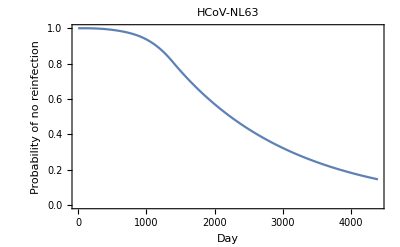

```mathematica
ListLinePlot[nl63probnoreinfectiontimecourse, PlotRange->{0,1}, PlotLabel->"HCoV-NL63", Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability of no reinfection"}]
```

```mathematica
nl63continuousprobnoreinfection=Interpolation[nl63probnoreinfectiontimecourse]
```

InterpolatingFunction[…]

```mathematica
1-nl63continuousprobnoreinfection[365]
```

0.00377656

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[nl63continuousprobnoreinfection[x]-0.95],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{930.227,31.0076,2.54857}

These are the 5% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[nl63continuousprobnoreinfection[x]-0.50],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{2233.6,74.4534,6.11946}

These are the 50% quantiles (medians) for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[nl63continuousprobnoreinfection[x]-0.05], 
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{4390.,146.333,12.0274}

These are the 95% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
nl63probreinfectiondensity={};
day=0;
While[day<4393,
Increment[day];
AppendTo[nl63probreinfectiondensity, 
If[day<lengthabtc,
nl63probinfgivenaod[oc43antibodytimecourse[[day]]]*nl63probnoreinfectiontimecourse[[day]],
nl63probinfgivenaod[oc43antibodytimecourse[[lengthabtc]]]*nl63probnoreinfectiontimecourse[[day]]
]
]
];
```

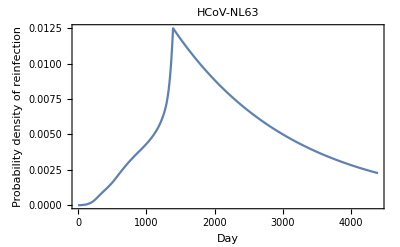

```mathematica
ListLinePlot[nl63probreinfectiondensity,
PlotLabel->"HCoV-NL63",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability density of reinfection"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["HCoV-NL63_PrInf-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[nl63probreinfectiondensity,
PlotLabel->"HCoV-NL63",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability density of reinfection"}]
]
```

HCoV-NL63_PrInf-by-Day_21Jan2021.pdf

## 229E

Input Data: ELIZA ODs for HCoV-229E S IgG antibodies from the processed supplementary dataset from Edridge et al. 2020, “Seasonal coronavirus protective immunity is short-lasting”, Nature Medicine

```mathematica
x229edata=Select[fulldataset,MemberQ[#, "229E"]&];
```

```mathematica
x229edata[[1]]
```

{1,1985-08-20,229E,0.614941,FALSE,NA,NA,0.149344,NA}

```mathematica
llx229elength=Length[x229edata]
```

513

### Probability of Infection | Antibody OD

```mathematica
llx229elrdaily=
Sum[
logisticprobability=1/(1+Exp[-(a+b*x229edata[[i,8]])]);
FullSimplify[
PowerExpand[
Log[
Which[
x229edata[[i,5]]=="NA", 1,
x229edata[[i,6]]=="NA", 1,
x229edata[[i,5]]=="TRUE", logisticprobability*(1-logisticprobability)^(x229edata[[i,6]]-1),
x229edata[[i,5]]=="FALSE",(1-logisticprobability)^x229edata[[i,6]],
True,  Abort[]
]
]
]
],
{i, llx229elength}
]
```

-Log[1+ⅇ^(-a-0.313336 b)]-Log[1+ⅇ^(-a-0.296162 b)]-Log[1+ⅇ^(-a-0.295102 b)]-Log[1+ⅇ^(-a-0.256634 b)]-Log[1+ⅇ^(-a-0.252895 b)]-Log[1+ⅇ^(-a-0.238034 b)]-Log[1+ⅇ^(-a-0.227707 b)]-Log[1+ⅇ^(-a-0.22593 b)]-Log[1+ⅇ^(-a-0.225817 b)]-Log[1+ⅇ^(-a-0.220089 b)]-Log[1+ⅇ^(-a-0.213048 b)]-Log[1+ⅇ^(-a-0.211446 b)]-Log[1+ⅇ^(-a-0.211152 b)]-Log[1+ⅇ^(-a-0.202354 b)]-Log[1+ⅇ^(-a-0.198642 b)]-Log[1+ⅇ^(-a-0.197497 b)]-Log[1+ⅇ^(-a-0.189753 b)]-Log[1+ⅇ^(-a-0.179251 b)]-Log[1+ⅇ^(-a-0.178493 b)]-Log[1+ⅇ^(-a-0.178217 b)]-Log[1+ⅇ^(-a-0.17568 b)]-Log[1+ⅇ^(-a-0.170787 b)]-Log[1+ⅇ^(-a-0.170635 b)]-Log[1+ⅇ^(-a-0.162107 b)]-Log[1+ⅇ^(-a-0.159467 b)]-Log[1+ⅇ^(-a-0.159429 b)]-Log[1+ⅇ^(-a-0.158683 b)]-Log[1+ⅇ^(-a-0.156779 b)]-Log[1+ⅇ^(-a-0.148134 b)]-Log[1+ⅇ^(-a-0.14768 b)]-Log[1+ⅇ^(-a-0.136538 b)]-Log[1+ⅇ^(-a-0.132485 b)]-Log[1+ⅇ^(-a-0.131956 b)]-Log[1+ⅇ^(-a-0.111588 b)]-Log[1+ⅇ^(-a-0.100707 b)]+181 Log[1/(1+ⅇ^(a+0.0999282 b))]+182 Log[1/(1+ⅇ^(a+0.100707 b))]+182 Log[1/(1+ⅇ^(a+0.109087 b))]+72 Log[1/(1+ⅇ^(a+0.111588 b))]+113 Log[1/(1+ⅇ^(a+0.112894 b))]+186 Log[1/(1+ⅇ^(a+0.12191 b))]+2319 Log[1/(1+ⅇ^(a+0.125404 b))]+181 Log[1/(1+ⅇ^(a+0.131956 b))]+62 Log[1/(1+ⅇ^(a+0.132297 b))]+95 Log[1/(1+ⅇ^(a+0.132485 b))]+121 Log[1/(1+ⅇ^(a+0.135726 b))]+183 Log[1/(1+ⅇ^(a+0.136066 b))]+181 Log[1/(1+ⅇ^(a+0.136538 b))]+86 Log[1/(1+ⅇ^(a+0.136716 b))]+93 Log[1/(1+ⅇ^(a+0.136771 b))]+182 Log[1/(1+ⅇ^(a+0.141967 b))]+175 Log[1/(1+ⅇ^(a+0.143743 b))]+97 Log[1/(1+ⅇ^(a+0.14768 b))]+176 Log[1/(1+ⅇ^(a+0.148134 b))]+97 Log[1/(1+ⅇ^(a+0.149048 b))]+91 Log[1/(1+ⅇ^(a+0.149274 b))]+182 Log[1/(1+ⅇ^(a+0.150014 b))]+104 Log[1/(1+ⅇ^(a+0.150019 b))]+181 Log[1/(1+ⅇ^(a+0.150865 b))]+93 Log[1/(1+ⅇ^(a+0.150894 b))]+90 Log[1/(1+ⅇ^(a+0.151063 b))]+192 Log[1/(1+ⅇ^(a+0.151457 b))]+91 Log[1/(1+ⅇ^(a+0.152848 b))]+112 Log[1/(1+ⅇ^(a+0.154137 b))]+178 Log[1/(1+ⅇ^(a+0.154602 b))]+165 Log[1/(1+ⅇ^(a+0.155915 b))]+84 Log[1/(1+ⅇ^(a+0.155967 b))]+95 Log[1/(1+ⅇ^(a+0.156434 b))]+182 Log[1/(1+ⅇ^(a+0.156659 b))]+97 Log[1/(1+ⅇ^(a+0.156779 b))]+189 Log[1/(1+ⅇ^(a+0.15773 b))]+182 Log[1/(1+ⅇ^(a+0.157832 b))]+182 Log[1/(1+ⅇ^(a+0.158633 b))]+182 Log[1/(1+ⅇ^(a+0.158683 b))]+95 Log[1/(1+ⅇ^(a+0.159429 b))]+195 Log[1/(1+ⅇ^(a+0.159467 b))]+91 Log[1/(1+ⅇ^(a+0.160199 b))]+84 Log[1/(1+ⅇ^(a+0.160952 b))]+182 Log[1/(1+ⅇ^(a+0.161565 b))]+93 Log[1/(1+ⅇ^(a+0.161638 b))]+181 Log[1/(1+ⅇ^(a+0.162107 b))]+181 Log[1/(1+ⅇ^(a+0.162398 b))]+182 Log[1/(1+ⅇ^(a+0.162736 b))]+91 Log[1/(1+ⅇ^(a+0.163506 b))]+182 Log[1/(1+ⅇ^(a+0.16385 b))]+80 Log[1/(1+ⅇ^(a+0.164108 b))]+182 Log[1/(1+ⅇ^(a+0.164872 b))]+93 Log[1/(1+ⅇ^(a+0.165513 b))]+96 Log[1/(1+ⅇ^(a+0.165532 b))]+102 Log[1/(1+ⅇ^(a+0.166154 b))]+92 Log[1/(1+ⅇ^(a+0.167259 b))]+91 Log[1/(1+ⅇ^(a+0.1674 b))]+195 Log[1/(1+ⅇ^(a+0.167779 b))]+175 Log[1/(1+ⅇ^(a+0.169388 b))]+99 Log[1/(1+ⅇ^(a+0.169707 b))]+92 Log[1/(1+ⅇ^(a+0.170094 b))]+90 Log[1/(1+ⅇ^(a+0.170266 b))]+91 Log[1/(1+ⅇ^(a+0.170433 b))]+97 Log[1/(1+ⅇ^(a+0.170635 b))]+174 Log[1/(1+ⅇ^(a+0.170787 b))]+91 Log[1/(1+ⅇ^(a+0.170937 b))]+91 Log[1/(1+ⅇ^(a+0.17111 b))]+188 Log[1/(1+ⅇ^(a+0.171403 b))]+88 Log[1/(1+ⅇ^(a+0.172253 b))]+98 Log[1/(1+ⅇ^(a+0.172542 b))]+90 Log[1/(1+ⅇ^(a+0.172785 b))]+175 Log[1/(1+ⅇ^(a+0.172882 b))]+182 Log[1/(1+ⅇ^(a+0.173357 b))]+91 Log[1/(1+ⅇ^(a+0.173994 b))]+98 Log[1/(1+ⅇ^(a+0.175022 b))]+188 Log[1/(1+ⅇ^(a+0.175671 b))]+175 Log[1/(1+ⅇ^(a+0.17568 b))]+92 Log[1/(1+ⅇ^(a+0.176113 b))]+105 Log[1/(1+ⅇ^(a+0.177424 b))]+245 Log[1/(1+ⅇ^(a+0.177618 b))]+172 Log[1/(1+ⅇ^(a+0.177844 b))]+182 Log[1/(1+ⅇ^(a+0.178217 b))]+189 Log[1/(1+ⅇ^(a+0.178326 b))]+181 Log[1/(1+ⅇ^(a+0.178493 b))]+187 Log[1/(1+ⅇ^(a+0.179186 b))]+187 Log[1/(1+ⅇ^(a+0.179251 b))]+91 Log[1/(1+ⅇ^(a+0.18068 b))]+182 Log[1/(1+ⅇ^(a+0.181319 b))]+182 Log[1/(1+ⅇ^(a+0.181598 b))]+183 Log[1/(1+ⅇ^(a+0.18263 b))]+181 Log[1/(1+ⅇ^(a+0.182788 b))]+91 Log[1/(1+ⅇ^(a+0.182901 b))]+88 Log[1/(1+ⅇ^(a+0.182993 b))]+189 Log[1/(1+ⅇ^(a+0.183142 b))]+97 Log[1/(1+ⅇ^(a+0.183215 b))]+2303 Log[1/(1+ⅇ^(a+0.183319 b))]+169 Log[1/(1+ⅇ^(a+0.183337 b))]+169 Log[1/(1+ⅇ^(a+0.183603 b))]+181 Log[1/(1+ⅇ^(a+0.183793 b))]+82 Log[1/(1+ⅇ^(a+0.185185 b))]+98 Log[1/(1+ⅇ^(a+0.185825 b))]+91 Log[1/(1+ⅇ^(a+0.185868 b))]+175 Log[1/(1+ⅇ^(a+0.185902 b))]+183 Log[1/(1+ⅇ^(a+0.186068 b))]+182 Log[1/(1+ⅇ^(a+0.186166 b))]+199 Log[1/(1+ⅇ^(a+0.186491 b))]+98 Log[1/(1+ⅇ^(a+0.187467 b))]+168 Log[1/(1+ⅇ^(a+0.188214 b))]+198 Log[1/(1+ⅇ^(a+0.188453 b))]+180 Log[1/(1+ⅇ^(a+0.189412 b))]+182 Log[1/(1+ⅇ^(a+0.189469 b))]+176 Log[1/(1+ⅇ^(a+0.18953 b))]+336 Log[1/(1+ⅇ^(a+0.18954 b))]+182 Log[1/(1+ⅇ^(a+0.189753 b))]+181 Log[1/(1+ⅇ^(a+0.190637 b))]+91 Log[1/(1+ⅇ^(a+0.19096 b))]+188 Log[1/(1+ⅇ^(a+0.19175 b))]+84 Log[1/(1+ⅇ^(a+0.191903 b))]+210 Log[1/(1+ⅇ^(a+0.191998 b))]+357 Log[1/(1+ⅇ^(a+0.192188 b))]+180 Log[1/(1+ⅇ^(a+0.192791 b))]+189 Log[1/(1+ⅇ^(a+0.193912 b))]+182 Log[1/(1+ⅇ^(a+0.19451 b))]+175 Log[1/(1+ⅇ^(a+0.194532 b))]+189 Log[1/(1+ⅇ^(a+0.195238 b))]+181 Log[1/(1+ⅇ^(a+0.195391 b))]+182 Log[1/(1+ⅇ^(a+0.195941 b))]+95 Log[1/(1+ⅇ^(a+0.196507 b))]+182 Log[1/(1+ⅇ^(a+0.196934 b))]+175 Log[1/(1+ⅇ^(a+0.197343 b))]+91 Log[1/(1+ⅇ^(a+0.197398 b))]+181 Log[1/(1+ⅇ^(a+0.197497 b))]+182 Log[1/(1+ⅇ^(a+0.198588 b))]+181 Log[1/(1+ⅇ^(a+0.198642 b))]+91 Log[1/(1+ⅇ^(a+0.198718 b))]+107 Log[1/(1+ⅇ^(a+0.19922 b))]+181 Log[1/(1+ⅇ^(a+0.199275 b))]+182 Log[1/(1+ⅇ^(a+0.199512 b))]+182 Log[1/(1+ⅇ^(a+0.199973 b))]+84 Log[1/(1+ⅇ^(a+0.201361 b))]+91 Log[1/(1+ⅇ^(a+0.201427 b))]+98 Log[1/(1+ⅇ^(a+0.201805 b))]+198 Log[1/(1+ⅇ^(a+0.202081 b))]+186 Log[1/(1+ⅇ^(a+0.202354 b))]+84 Log[1/(1+ⅇ^(a+0.202641 b))]+182 Log[1/(1+ⅇ^(a+0.202661 b))]+189 Log[1/(1+ⅇ^(a+0.202806 b))]+176 Log[1/(1+ⅇ^(a+0.203203 b))]+175 Log[1/(1+ⅇ^(a+0.203276 b))]+182 Log[1/(1+ⅇ^(a+0.203404 b))]+175 Log[1/(1+ⅇ^(a+0.203486 b))]+91 Log[1/(1+ⅇ^(a+0.203892 b))]+92 Log[1/(1+ⅇ^(a+0.204323 b))]+190 Log[1/(1+ⅇ^(a+0.204895 b))]+91 Log[1/(1+ⅇ^(a+0.20502 b))]+238 Log[1/(1+ⅇ^(a+0.205135 b))]+188 Log[1/(1+ⅇ^(a+0.205307 b))]+191 Log[1/(1+ⅇ^(a+0.205689 b))]+189 Log[1/(1+ⅇ^(a+0.20629 b))]+188 Log[1/(1+ⅇ^(a+0.206342 b))]+318 Log[1/(1+ⅇ^(a+0.206367 b))]+448 Log[1/(1+ⅇ^(a+0.206994 b))]+105 Log[1/(1+ⅇ^(a+0.207109 b))]+179 Log[1/(1+ⅇ^(a+0.207215 b))]+166 Log[1/(1+ⅇ^(a+0.207776 b))]+94 Log[1/(1+ⅇ^(a+0.207847 b))]+96 Log[1/(1+ⅇ^(a+0.20798 b))]+180 Log[1/(1+ⅇ^(a+0.208664 b))]+217 Log[1/(1+ⅇ^(a+0.20872 b))]+189 Log[1/(1+ⅇ^(a+0.209514 b))]+182 Log[1/(1+ⅇ^(a+0.209818 b))]+147 Log[1/(1+ⅇ^(a+0.210014 b))]+2424 Log[1/(1+ⅇ^(a+0.210132 b))]+184 Log[1/(1+ⅇ^(a+0.210592 b))]+190 Log[1/(1+ⅇ^(a+0.210601 b))]+352 Log[1/(1+ⅇ^(a+0.210918 b))]+181 Log[1/(1+ⅇ^(a+0.211152 b))]+182 Log[1/(1+ⅇ^(a+0.21117 b))]+90 Log[1/(1+ⅇ^(a+0.21133 b))]+105 Log[1/(1+ⅇ^(a+0.21142 b))]+155 Log[1/(1+ⅇ^(a+0.211446 b))]+177 Log[1/(1+ⅇ^(a+0.211528 b))]+376 Log[1/(1+ⅇ^(a+0.211847 b))]+176 Log[1/(1+ⅇ^(a+0.212022 b))]+2240 Log[1/(1+ⅇ^(a+0.212505 b))]+99 Log[1/(1+ⅇ^(a+0.21253 b))]+186 Log[1/(1+ⅇ^(a+0.212849 b))]+180 Log[1/(1+ⅇ^(a+0.212945 b))]+181 Log[1/(1+ⅇ^(a+0.213048 b))]+190 Log[1/(1+ⅇ^(a+0.213207 b))]+183 Log[1/(1+ⅇ^(a+0.213304 b))]+189 Log[1/(1+ⅇ^(a+0.213907 b))]+182 Log[1/(1+ⅇ^(a+0.213909 b))]+98 Log[1/(1+ⅇ^(a+0.214068 b))]+189 Log[1/(1+ⅇ^(a+0.214817 b))]+177 Log[1/(1+ⅇ^(a+0.215093 b))]+189 Log[1/(1+ⅇ^(a+0.215187 b))]+224 Log[1/(1+ⅇ^(a+0.215193 b))]+167 Log[1/(1+ⅇ^(a+0.215636 b))]+175 Log[1/(1+ⅇ^(a+0.215954 b))]+190 Log[1/(1+ⅇ^(a+0.216008 b))]+94 Log[1/(1+ⅇ^(a+0.216078 b))]+91 Log[1/(1+ⅇ^(a+0.216494 b))]+203 Log[1/(1+ⅇ^(a+0.217014 b))]+175 Log[1/(1+ⅇ^(a+0.217549 b))]+97 Log[1/(1+ⅇ^(a+0.217573 b))]+91 Log[1/(1+ⅇ^(a+0.217735 b))]+105 Log[1/(1+ⅇ^(a+0.217924 b))]+182 Log[1/(1+ⅇ^(a+0.21824 b))]+189 Log[1/(1+ⅇ^(a+0.218497 b))]+223 Log[1/(1+ⅇ^(a+0.218656 b))]+182 Log[1/(1+ⅇ^(a+0.218868 b))]+98 Log[1/(1+ⅇ^(a+0.219393 b))]+182 Log[1/(1+ⅇ^(a+0.219702 b))]+98 Log[1/(1+ⅇ^(a+0.220048 b))]+90 Log[1/(1+ⅇ^(a+0.220089 b))]+91 Log[1/(1+ⅇ^(a+0.220462 b))]+189 Log[1/(1+ⅇ^(a+0.220596 b))]+92 Log[1/(1+ⅇ^(a+0.221312 b))]+168 Log[1/(1+ⅇ^(a+0.221315 b))]+175 Log[1/(1+ⅇ^(a+0.221525 b))]+182 Log[1/(1+ⅇ^(a+0.221545 b))]+175 Log[1/(1+ⅇ^(a+0.221566 b))]+189 Log[1/(1+ⅇ^(a+0.221655 b))]+99 Log[1/(1+ⅇ^(a+0.222198 b))]+184 Log[1/(1+ⅇ^(a+0.22294 b))]+2359 Log[1/(1+ⅇ^(a+0.223186 b))]+202 Log[1/(1+ⅇ^(a+0.223284 b))]+196 Log[1/(1+ⅇ^(a+0.223454 b))]+91 Log[1/(1+ⅇ^(a+0.223719 b))]+183 Log[1/(1+ⅇ^(a+0.223849 b))]+365 Log[1/(1+ⅇ^(a+0.224596 b))]+175 Log[1/(1+ⅇ^(a+0.224897 b))]+84 Log[1/(1+ⅇ^(a+0.22495 b))]+182 Log[1/(1+ⅇ^(a+0.225383 b))]+92 Log[1/(1+ⅇ^(a+0.225653 b))]+362 Log[1/(1+ⅇ^(a+0.225817 b))]+181 Log[1/(1+ⅇ^(a+0.22593 b))]+182 Log[1/(1+ⅇ^(a+0.226166 b))]+175 Log[1/(1+ⅇ^(a+0.226269 b))]+91 Log[1/(1+ⅇ^(a+0.226833 b))]+84 Log[1/(1+ⅇ^(a+0.226961 b))]+181 Log[1/(1+ⅇ^(a+0.227081 b))]+168 Log[1/(1+ⅇ^(a+0.227457 b))]+182 Log[1/(1+ⅇ^(a+0.227617 b))]+90 Log[1/(1+ⅇ^(a+0.227707 b))]+203 Log[1/(1+ⅇ^(a+0.228222 b))]+124 Log[1/(1+ⅇ^(a+0.228561 b))]+182 Log[1/(1+ⅇ^(a+0.228768 b))]+89 Log[1/(1+ⅇ^(a+0.228812 b))]+96 Log[1/(1+ⅇ^(a+0.229515 b))]+93 Log[1/(1+ⅇ^(a+0.230276 b))]+175 Log[1/(1+ⅇ^(a+0.230458 b))]+98 Log[1/(1+ⅇ^(a+0.230755 b))]+126 Log[1/(1+ⅇ^(a+0.230777 b))]+189 Log[1/(1+ⅇ^(a+0.231236 b))]+182 Log[1/(1+ⅇ^(a+0.231262 b))]+197 Log[1/(1+ⅇ^(a+0.231477 b))]+180 Log[1/(1+ⅇ^(a+0.231515 b))]+189 Log[1/(1+ⅇ^(a+0.231883 b))]+91 Log[1/(1+ⅇ^(a+0.231904 b))]+96 Log[1/(1+ⅇ^(a+0.232374 b))]+79 Log[1/(1+ⅇ^(a+0.234977 b))]+91 Log[1/(1+ⅇ^(a+0.235081 b))]+174 Log[1/(1+ⅇ^(a+0.235118 b))]+165 Log[1/(1+ⅇ^(a+0.235446 b))]+91 Log[1/(1+ⅇ^(a+0.235524 b))]+182 Log[1/(1+ⅇ^(a+0.236015 b))]+89 Log[1/(1+ⅇ^(a+0.236931 b))]+85 Log[1/(1+ⅇ^(a+0.236944 b))]+188 Log[1/(1+ⅇ^(a+0.236994 b))]+160 Log[1/(1+ⅇ^(a+0.237086 b))]+185 Log[1/(1+ⅇ^(a+0.238034 b))]+91 Log[1/(1+ⅇ^(a+0.238114 b))]+189 Log[1/(1+ⅇ^(a+0.2384 b))]+91 Log[1/(1+ⅇ^(a+0.238496 b))]+189 Log[1/(1+ⅇ^(a+0.238601 b))]+78 Log[1/(1+ⅇ^(a+0.238922 b))]+181 Log[1/(1+ⅇ^(a+0.239417 b))]+179 Log[1/(1+ⅇ^(a+0.239434 b))]+182 Log[1/(1+ⅇ^(a+0.239646 b))]+91 Log[1/(1+ⅇ^(a+0.239671 b))]+182 Log[1/(1+ⅇ^(a+0.241322 b))]+196 Log[1/(1+ⅇ^(a+0.241684 b))]+175 Log[1/(1+ⅇ^(a+0.241861 b))]+183 Log[1/(1+ⅇ^(a+0.242032 b))]+90 Log[1/(1+ⅇ^(a+0.242587 b))]+182 Log[1/(1+ⅇ^(a+0.242975 b))]+181 Log[1/(1+ⅇ^(a+0.243183 b))]+90 Log[1/(1+ⅇ^(a+0.243189 b))]+91 Log[1/(1+ⅇ^(a+0.24415 b))]+185 Log[1/(1+ⅇ^(a+0.244528 b))]+189 Log[1/(1+ⅇ^(a+0.244989 b))]+98 Log[1/(1+ⅇ^(a+0.245206 b))]+183 Log[1/(1+ⅇ^(a+0.245407 b))]+183 Log[1/(1+ⅇ^(a+0.245691 b))]+204 Log[1/(1+ⅇ^(a+0.246104 b))]+183 Log[1/(1+ⅇ^(a+0.24612 b))]+65 Log[1/(1+ⅇ^(a+0.246715 b))]+82 Log[1/(1+ⅇ^(a+0.247527 b))]+175 Log[1/(1+ⅇ^(a+0.247817 b))]+185 Log[1/(1+ⅇ^(a+0.24787 b))]+189 Log[1/(1+ⅇ^(a+0.248014 b))]+181 Log[1/(1+ⅇ^(a+0.248475 b))]+182 Log[1/(1+ⅇ^(a+0.248612 b))]+245 Log[1/(1+ⅇ^(a+0.24952 b))]+189 Log[1/(1+ⅇ^(a+0.250125 b))]+91 Log[1/(1+ⅇ^(a+0.250562 b))]+91 Log[1/(1+ⅇ^(a+0.251306 b))]+182 Log[1/(1+ⅇ^(a+0.251458 b))]+182 Log[1/(1+ⅇ^(a+0.252546 b))]+182 Log[1/(1+ⅇ^(a+0.252793 b))]+190 Log[1/(1+ⅇ^(a+0.252895 b))]+190 Log[1/(1+ⅇ^(a+0.253123 b))]+209 Log[1/(1+ⅇ^(a+0.253292 b))]+91 Log[1/(1+ⅇ^(a+0.253372 b))]+335 Log[1/(1+ⅇ^(a+0.253507 b))]+193 Log[1/(1+ⅇ^(a+0.254665 b))]+212 Log[1/(1+ⅇ^(a+0.254787 b))]+91 Log[1/(1+ⅇ^(a+0.255574 b))]+97 Log[1/(1+ⅇ^(a+0.255661 b))]+182 Log[1/(1+ⅇ^(a+0.256014 b))]+210 Log[1/(1+ⅇ^(a+0.256634 b))]+86 Log[1/(1+ⅇ^(a+0.256779 b))]+91 Log[1/(1+ⅇ^(a+0.257268 b))]+182 Log[1/(1+ⅇ^(a+0.257483 b))]+91 Log[1/(1+ⅇ^(a+0.259015 b))]+95 Log[1/(1+ⅇ^(a+0.25949 b))]+184 Log[1/(1+ⅇ^(a+0.259766 b))]+219 Log[1/(1+ⅇ^(a+0.260001 b))]+182 Log[1/(1+ⅇ^(a+0.260117 b))]+194 Log[1/(1+ⅇ^(a+0.260249 b))]+183 Log[1/(1+ⅇ^(a+0.261049 b))]+184 Log[1/(1+ⅇ^(a+0.261053 b))]+184 Log[1/(1+ⅇ^(a+0.261834 b))]+81 Log[1/(1+ⅇ^(a+0.262353 b))]+182 Log[1/(1+ⅇ^(a+0.263043 b))]+91 Log[1/(1+ⅇ^(a+0.263279 b))]+186 Log[1/(1+ⅇ^(a+0.265388 b))]+180 Log[1/(1+ⅇ^(a+0.265912 b))]+92 Log[1/(1+ⅇ^(a+0.266529 b))]+80 Log[1/(1+ⅇ^(a+0.266723 b))]+180 Log[1/(1+ⅇ^(a+0.268406 b))]+96 Log[1/(1+ⅇ^(a+0.269131 b))]+182 Log[1/(1+ⅇ^(a+0.269993 b))]+189 Log[1/(1+ⅇ^(a+0.270047 b))]+84 Log[1/(1+ⅇ^(a+0.270973 b))]+98 Log[1/(1+ⅇ^(a+0.271663 b))]+187 Log[1/(1+ⅇ^(a+0.271931 b))]+175 Log[1/(1+ⅇ^(a+0.272144 b))]+95 Log[1/(1+ⅇ^(a+0.272685 b))]+177 Log[1/(1+ⅇ^(a+0.273197 b))]+189 Log[1/(1+ⅇ^(a+0.273987 b))]+91 Log[1/(1+ⅇ^(a+0.274737 b))]+91 Log[1/(1+ⅇ^(a+0.275174 b))]+98 Log[1/(1+ⅇ^(a+0.27543 b))]+160 Log[1/(1+ⅇ^(a+0.275985 b))]+98 Log[1/(1+ⅇ^(a+0.27636 b))]+91 Log[1/(1+ⅇ^(a+0.276429 b))]+181 Log[1/(1+ⅇ^(a+0.277088 b))]+82 Log[1/(1+ⅇ^(a+0.278612 b))]+182 Log[1/(1+ⅇ^(a+0.278788 b))]+188 Log[1/(1+ⅇ^(a+0.279517 b))]+182 Log[1/(1+ⅇ^(a+0.279696 b))]+91 Log[1/(1+ⅇ^(a+0.280062 b))]+170 Log[1/(1+ⅇ^(a+0.280145 b))]+180 Log[1/(1+ⅇ^(a+0.280988 b))]+181 Log[1/(1+ⅇ^(a+0.281929 b))]+91 Log[1/(1+ⅇ^(a+0.282172 b))]+201 Log[1/(1+ⅇ^(a+0.283085 b))]+184 Log[1/(1+ⅇ^(a+0.283488 b))]+84 Log[1/(1+ⅇ^(a+0.284705 b))]+182 Log[1/(1+ⅇ^(a+0.284827 b))]+86 Log[1/(1+ⅇ^(a+0.285637 b))]+190 Log[1/(1+ⅇ^(a+0.285959 b))]+87 Log[1/(1+ⅇ^(a+0.286489 b))]+2394 Log[1/(1+ⅇ^(a+0.286524 b))]+2338 Log[1/(1+ⅇ^(a+0.287618 b))]+175 Log[1/(1+ⅇ^(a+0.289161 b))]+91 Log[1/(1+ⅇ^(a+0.292213 b))]+184 Log[1/(1+ⅇ^(a+0.292866 b))]+98 Log[1/(1+ⅇ^(a+0.293904 b))]+182 Log[1/(1+ⅇ^(a+0.29396 b))]+92 Log[1/(1+ⅇ^(a+0.294311 b))]+196 Log[1/(1+ⅇ^(a+0.294345 b))]+132 Log[1/(1+ⅇ^(a+0.29459 b))]+160 Log[1/(1+ⅇ^(a+0.294719 b))]+183 Log[1/(1+ⅇ^(a+0.294719 b))]+174 Log[1/(1+ⅇ^(a+0.295102 b))]+77 Log[1/(1+ⅇ^(a+0.295169 b))]+182 Log[1/(1+ⅇ^(a+0.295496 b))]+182 Log[1/(1+ⅇ^(a+0.295591 b))]+195 Log[1/(1+ⅇ^(a+0.296162 b))]+182 Log[1/(1+ⅇ^(a+0.296763 b))]+80 Log[1/(1+ⅇ^(a+0.297273 b))]+88 Log[1/(1+ⅇ^(a+0.297439 b))]+182 Log[1/(1+ⅇ^(a+0.298231 b))]+103 Log[1/(1+ⅇ^(a+0.29868 b))]+95 Log[1/(1+ⅇ^(a+0.299406 b))]+94 Log[1/(1+ⅇ^(a+0.299919 b))]+92 Log[1/(1+ⅇ^(a+0.300619 b))]+182 Log[1/(1+ⅇ^(a+0.302629 b))]+183 Log[1/(1+ⅇ^(a+0.302983 b))]+91 Log[1/(1+ⅇ^(a+0.303194 b))]+183 Log[1/(1+ⅇ^(a+0.304781 b))]+189 Log[1/(1+ⅇ^(a+0.306142 b))]+91 Log[1/(1+ⅇ^(a+0.311199 b))]+91 Log[1/(1+ⅇ^(a+0.311902 b))]+188 Log[1/(1+ⅇ^(a+0.312967 b))]+188 Log[1/(1+ⅇ^(a+0.313336 b))]+79 Log[1/(1+ⅇ^(a+0.313389 b))]+231 Log[1/(1+ⅇ^(a+0.313676 b))]+91 Log[1/(1+ⅇ^(a+0.313818 b))]+182 Log[1/(1+ⅇ^(a+0.313882 b))]+175 Log[1/(1+ⅇ^(a+0.317984 b))]+175 Log[1/(1+ⅇ^(a+0.318322 b))]+94 Log[1/(1+ⅇ^(a+0.322096 b))]+91 Log[1/(1+ⅇ^(a+0.322911 b))]+94 Log[1/(1+ⅇ^(a+0.323082 b))]+182 Log[1/(1+ⅇ^(a+0.325904 b))]+178 Log[1/(1+ⅇ^(a+0.328625 b))]+181 Log[1/(1+ⅇ^(a+0.328889 b))]+175 Log[1/(1+ⅇ^(a+0.329051 b))]+182 Log[1/(1+ⅇ^(a+0.330258 b))]+190 Log[1/(1+ⅇ^(a+0.330629 b))]+189 Log[1/(1+ⅇ^(a+0.33162 b))]+91 Log[1/(1+ⅇ^(a+0.332428 b))]+92 Log[1/(1+ⅇ^(a+0.332659 b))]+3239 Log[1/(1+ⅇ^(a+0.333083 b))]+183 Log[1/(1+ⅇ^(a+0.334306 b))]+196 Log[1/(1+ⅇ^(a+0.334737 b))]+84 Log[1/(1+ⅇ^(a+0.340901 b))]+182 Log[1/(1+ⅇ^(a+0.341604 b))]+182 Log[1/(1+ⅇ^(a+0.342204 b))]+182 Log[1/(1+ⅇ^(a+0.344938 b))]+175 Log[1/(1+ⅇ^(a+0.347073 b))]+200 Log[1/(1+ⅇ^(a+0.347842 b))]+177 Log[1/(1+ⅇ^(a+0.348216 b))]+189 Log[1/(1+ⅇ^(a+0.348853 b))]+94 Log[1/(1+ⅇ^(a+0.353502 b))]+195 Log[1/(1+ⅇ^(a+0.357303 b))]+91 Log[1/(1+ⅇ^(a+0.361223 b))]+182 Log[1/(1+ⅇ^(a+0.361951 b))]+181 Log[1/(1+ⅇ^(a+0.361995 b))]+189 Log[1/(1+ⅇ^(a+0.365723 b))]+183 Log[1/(1+ⅇ^(a+0.369721 b))]+177 Log[1/(1+ⅇ^(a+0.370997 b))]+182 Log[1/(1+ⅇ^(a+0.371011 b))]+175 Log[1/(1+ⅇ^(a+0.37484 b))]+189 Log[1/(1+ⅇ^(a+0.376429 b))]+189 Log[1/(1+ⅇ^(a+0.380985 b))]+162 Log[1/(1+ⅇ^(a+0.382851 b))]+182 Log[1/(1+ⅇ^(a+0.38461 b))]+182 Log[1/(1+ⅇ^(a+0.396064 b))]+155 Log[1/(1+ⅇ^(a+0.397872 b))]+88 Log[1/(1+ⅇ^(a+0.416501 b))]+94 Log[1/(1+ⅇ^(a+0.428123 b))]+93 Log[1/(1+ⅇ^(a+0.429962 b))]+182 Log[1/(1+ⅇ^(a+0.431571 b))]+187 Log[1/(1+ⅇ^(a+0.435264 b))]+172 Log[1/(1+ⅇ^(a+0.436348 b))]+174 Log[1/(1+ⅇ^(a+0.441664 b))]+183 Log[1/(1+ⅇ^(a+0.453362 b))]+86 Log[1/(1+ⅇ^(a+0.464951 b))]+89 Log[1/(1+ⅇ^(a+0.479436 b))]+159 Log[1/(1+ⅇ^(a+0.482934 b))]+90 Log[1/(1+ⅇ^(a+0.484894 b))]+182 Log[1/(1+ⅇ^(a+0.49316 b))]+187 Log[1/(1+ⅇ^(a+0.495122 b))]+183 Log[1/(1+ⅇ^(a+0.499485 b))]+378 Log[1/(1+ⅇ^(a+0.505397 b))]+130 Log[1/(1+ⅇ^(a+0.521206 b))]+168 Log[1/(1+ⅇ^(a+0.531919 b))]+178 Log[1/(1+ⅇ^(a+0.538429 b))]+29 Log[1/(1+ⅇ^(a+0.549924 b))]+77 Log[1/(1+ⅇ^(a+0.552212 b))]+197 Log[1/(1+ⅇ^(a+0.563384 b))]+78 Log[1/(1+ⅇ^(a+0.569297 b))]+182 Log[1/(1+ⅇ^(a+0.569831 b))]+183 Log[1/(1+ⅇ^(a+0.615408 b))]+182 Log[1/(1+ⅇ^(a+0.622708 b))]+203 Log[1/(1+ⅇ^(a+0.685255 b))]+84 Log[1/(1+ⅇ^(a+0.688761 b))]+181 Log[1/(1+ⅇ^(a+0.690347 b))]+189 Log[1/(1+ⅇ^(a+0.715212 b))]+182 Log[1/(1+ⅇ^(a+0.746002 b))]+182 Log[1/(1+ⅇ^(a+0.808426 b))]+166 Log[1/(1+ⅇ^(a+0.88396 b))]+98 Log[1/(1+ⅇ^(a+1.15654 b))]+89 Log[1/(1+ⅇ^(a+1.15987 b))]+175 Log[1/(1+ⅇ^(a+1.3933 b))]+178 Log[1/(1+ⅇ^(a+1.40637 b))]+371 Log[1/(1+ⅇ^(a+1.52537 b))]

```mathematica
x229emlparams=maxllx229elrdaily=NMaximize[{llx229elrdaily}, {a, b}]
```

{-299.729,{a→-4.80403,b→-14.3412}}

These values of a and b go into the the ancestral and descendent states analysis to estimate a and b for the zoonotic coronaviruses.

```mathematica
x229eprobinfgivenaod[aod_]:=1/(1+Exp[-(a+b*aod)]) /. maxllx229elrdaily[[2]]
```

```mathematica
x229eprobinfgivenaod[aod]
```

1/(1+ⅇ^(4.80403+14.3412 aod))

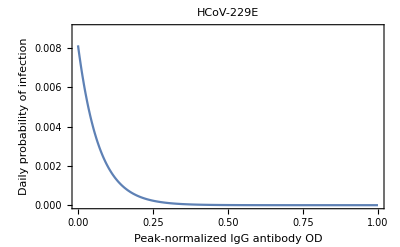

```mathematica
Plot[x229eprobinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.009},
PlotLabel->"HCoV-229E",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["HCoV-229E_PrInf-by-nOD_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Plot[x229eprobinfgivenaod[x],{x,0,1},
PlotRange->{0,0.009},
PlotLabel->"HCoV-229E",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
]
```

HCoV-229E_PrInf-by-nOD_21Jan2021.pdf

### 229E Waning of Antibody OD

```mathematica
x229edata
```

{{1,1985-08-20,229E,0.614941,FALSE,NA,NA,0.149344,NA},{2,1985-11-18,229E,0.870174,FALSE,90,0.00283593,0.21133,0.000688733},{3,1986-02-14,229E,0.709271,FALSE,88,-0.00182845,0.172253,-0.000444057},{4,1986-05-29,229E,0.617718,FALSE,104,-0.000880309,0.150019,-0.000213792},{5,1986-09-05,229E,0.698786,FALSE,99,0.000818863,0.169707,0.000198869},{6,1986-11-26,229E,0.762518,FALSE,82,0.000777221,0.185185,0.000188756},{7,1987-03-04,229E,0.702607,TRUE,98,-0.000611339,0.170635,-0.00014847},{8,1987-06-01,229E,1.97413,FALSE,89,0.0142867,0.479436,0.00346967},{9,1987-08-20,229E,1.09826,FALSE,80,-0.0109483,0.266723,-0.0026589},{10,1987-11-19,229E,1.00531,FALSE,91,-0.00102139,0.24415,-0.000248054},{11,1988-02-25,229E,0.903371,FALSE,98,-0.00104023,0.219393,-0.000252631},{12,1988-05-19,229E,0.926253,FALSE,84,0.000272399,0.22495,0.0000661548},{13,1988-09-28,229E,1.213,FALSE,132,0.00217236,0.29459,0.000527579},{14,1988-12-14,229E,1.21539,FALSE,77,0.0000309684,0.295169,7.52097×10^-6},{15,1989-11-14,229E,1.04384,FALSE,335,-0.000512088,0.253507,-0.000124365},{16,1990-06-11,229E,1.04295,FALSE,209,-4.23459×10^-6,0.253292,-1.02841×10^-6},{17,1990-12-17,229E,0.912688,FALSE,189,-0.000689242,0.221655,-0.000167389},{18,1991-06-26,229E,0.846944,FALSE,191,-0.000344209,0.205689,-0.0000835945},{19,1991-12-20,229E,0.87099,FALSE,177,0.000135854,0.211528,0.0000329935},{20,1992-12-11,229E,0.791354,FALSE,357,-0.000223072,0.192188,-0.0000541752},{21,1993-06-11,229E,0.823409,FALSE,182,0.000176131,0.199973,0.0000427751},{22,1993-12-09,229E,0.752649,FALSE,181,-0.000390941,0.182788,-0.0000949438},{23,1994-06-09,229E,0.810898,FALSE,182,0.000320048,0.196934,0.0000777268},{24,1994-12-08,229E,1.05416,FALSE,182,0.00133662,0.256014,0.000324611},{25,1995-06-15,229E,0.734274,FALSE,189,-0.00169253,0.178326,-0.000411048},{26,1995-12-11,229E,0.985894,FALSE,179,0.0014057,0.239434,0.000341387},{27,1996-06-10,229E,0.937236,FALSE,182,-0.000267353,0.227617,-0.0000649293},{28,1996-12-02,229E,0.801007,FALSE,175,-0.000778451,0.194532,-0.000189054},{29,2003-04-28,229E,1.1843,FALSE,2338,0.000163939,0.287618,0.0000398142},{30,2003-10-27,229E,1.0409,FALSE,182,-0.000787877,0.252793,-0.000191344},{31,2004-04-26,229E,0.869514,FALSE,182,-0.000941695,0.21117,-0.0002287},{32,2004-10-25,229E,1.06021,FALSE,182,0.00104778,0.257483,0.000254464},{33,2005-04-20,229E,1.12492,FALSE,177,0.000365576,0.273197,0.0000887837},{34,2005-11-02,229E,1.212,FALSE,196,0.000444275,0.294345,0.000107897},{35,2006-04-26,229E,1.12058,FALSE,175,-0.000522377,0.272144,-0.000126864},{36,2006-10-25,229E,1.42032,FALSE,182,0.00164692,0.344938,0.000399971},{37,2007-04-25,229E,1.21713,FALSE,182,-0.00111644,0.295591,-0.000271138},{38,2008-07-16,229E,0.852319,FALSE,448,-0.000814304,0.206994,-0.000197762},{39,2008-11-19,229E,0.950249,FALSE,126,0.00077722,0.230777,0.000188755},{40,2009-05-18,229E,0.859197,FALSE,180,-0.000505843,0.208664,-0.000122849},{41,2010-04-01,229E,0.849737,FALSE,318,-0.0000297489,0.206367,-7.22481×10^-6},{42,2011-04-12,229E,0.872302,FALSE,376,0.0000600114,0.211847,0.0000145744},{43,2012-04-11,229E,0.924799,FALSE,365,0.000143828,0.224596,0.00003493},{44,2013-04-09,229E,0.929824,TRUE,363,0.0000138429,0.225817,3.36188×10^-6},{45,2014-04-15,229E,6.28088,FALSE,371,0.0144233,1.52537,0.00350285},{46,2015-04-28,229E,2.08102,FALSE,378,-0.0111107,0.505397,-0.00269835},{47,2017-08-30,229E,1.45823,NA,855,-0.000728415,0.354145,-0.000176903},{279,1985-03-01,229E,0.851638,FALSE,NA,NA,0.206829,NA},{280,1985-05-31,229E,0.765329,FALSE,91,-0.000948452,0.185868,-0.000230341},{281,1985-09-05,229E,0.754407,FALSE,97,-0.000112596,0.183215,-0.0000273451},{282,1985-12-05,229E,0.743969,FALSE,91,-0.000114704,0.18068,-0.0000278571},{283,1986-03-20,229E,0.730563,FALSE,105,-0.00012768,0.177424,-0.0000310083},{284,1986-06-26,229E,0.765153,FALSE,98,0.000352966,0.185825,0.0000857212},{285,1986-09-18,229E,0.662736,FALSE,84,-0.00121926,0.160952,-0.000296109},{286,1986-12-18,229E,0.659634,FALSE,91,-0.00003408,0.160199,-8.27667×10^-6},{287,1987-03-19,229E,0.689289,FALSE,91,0.000325869,0.1674,0.0000791405},{288,1987-06-25,229E,0.608087,TRUE,98,-0.000828589,0.14768,-0.000201231},{289,1987-09-14,229E,1.08027,FALSE,81,0.00582937,0.262353,0.00141572},{290,1987-12-03,229E,0.675733,FALSE,80,-0.00505667,0.164108,-0.00122806},{291,1988-03-03,229E,0.61465,FALSE,91,-0.000671238,0.149274,-0.000163017},{292,1988-06-02,229E,0.701776,FALSE,91,0.000957433,0.170433,0.000232522},{293,1988-09-06,229E,0.681595,FALSE,96,-0.000210226,0.165532,-0.0000510554},{294,1988-12-08,229E,0.62132,FALSE,93,-0.000648112,0.150894,-0.0001574},{295,1989-06-08,229E,0.617699,FALSE,182,-0.0000198979,0.150014,-4.8324×10^-6},{296,1989-12-07,229E,0.543344,TRUE,182,-0.000408541,0.131956,-0.0000992183},{297,1990-06-07,229E,3.32878,FALSE,182,0.0153046,0.808426,0.00371686},{298,1990-12-07,229E,1.37654,FALSE,183,-0.010668,0.334306,-0.00259082},{299,1991-06-07,229E,1.02369,FALSE,182,-0.00193874,0.248612,-0.000470842},{300,1991-12-04,229E,0.876824,FALSE,180,-0.000815905,0.212945,-0.000198151},{301,1992-06-03,229E,0.817708,FALSE,182,-0.000324815,0.198588,-0.0000788845},{302,1992-12-03,229E,1.01166,FALSE,183,0.00105983,0.245691,0.000257391},{303,1993-06-03,229E,1.14794,FALSE,182,0.00074879,0.278788,0.000181851},{304,1993-12-08,229E,0.849633,FALSE,188,-0.00158672,0.206342,-0.000385351},{305,1994-06-16,229E,0.889437,FALSE,190,0.000209494,0.216008,0.0000508778},{306,1994-12-14,229E,0.784969,FALSE,181,-0.000577173,0.190637,-0.000140172},{307,1995-06-21,229E,0.862697,FALSE,189,0.000411262,0.209514,0.000099879},{308,1995-12-06,229E,0.774991,FALSE,168,-0.000522059,0.188214,-0.000126787},{309,1996-06-11,229E,0.789551,FALSE,188,0.0000774446,0.19175,0.0000188082},{310,1996-12-04,229E,0.72338,TRUE,176,-0.00037597,0.17568,-0.0000913081},{311,2005-10-17,229E,1.3715,FALSE,3239,0.0002001,0.333083,0.0000485962},{312,2006-04-18,229E,1.52237,FALSE,183,0.000824384,0.369721,0.00020021},{313,2006-10-24,229E,1.29019,TRUE,189,-0.00122843,0.313336,-0.000298336},{314,2007-04-24,229E,2.56406,FALSE,182,0.00699929,0.622708,0.00169985},{315,2007-10-23,229E,1.63083,FALSE,182,-0.00512763,0.396064,-0.0012453},{316,2008-04-15,229E,1.54344,FALSE,175,-0.000499385,0.37484,-0.00012128},{317,2008-10-14,229E,1.29244,FALSE,182,-0.00137911,0.313882,-0.00033493},{318,2009-04-07,229E,1.30933,FALSE,175,0.0000965136,0.317984,0.0000234393},{319,2009-10-13,229E,1.5059,FALSE,189,0.00104005,0.365723,0.000252587},{320,2010-04-13,229E,2.34634,FALSE,182,0.00461778,0.569831,0.00112147},{321,2010-10-12,229E,1.52768,FALSE,182,-0.00449814,0.371011,-0.00109242},{322,2011-04-26,229E,1.37832,FALSE,196,-0.000762048,0.334737,-0.000185071},{323,2011-10-18,229E,1.19065,FALSE,175,-0.00107238,0.289161,-0.000260437},{324,2012-04-24,229E,1.26057,FALSE,189,0.000369964,0.306142,0.0000898494},{325,2012-10-30,229E,1.12817,FALSE,189,-0.000700539,0.273987,-0.000170133},{326,2013-04-22,229E,1.8186,FALSE,174,0.00396796,0.441664,0.000963658},{327,2013-10-28,229E,0.798452,FALSE,189,-0.00539759,0.193912,-0.00131086},{328,2014-04-29,229E,0.921722,FALSE,183,0.000673606,0.223849,0.000163592},{329,2014-10-29,229E,0.781329,TRUE,183,-0.000767176,0.189753,-0.000186316},{330,2015-04-22,229E,1.3549,FALSE,175,0.00327757,0.329051,0.000795989},{331,2015-10-27,229E,1.15094,FALSE,188,-0.00108492,0.279517,-0.000263484},{332,2016-04-19,229E,1.31072,FALSE,175,0.000913051,0.318322,0.000221743},{333,2016-10-18,229E,1.228,FALSE,182,-0.000454532,0.298231,-0.000110388},{334,2017-04-25,229E,1.11195,FALSE,189,-0.000614032,0.270047,-0.000149124},{335,2017-10-31,229E,0.835073,FALSE,189,-0.00146493,0.202806,-0.000355773},{336,2018-05-22,229E,0.939726,FALSE,203,0.000515531,0.228222,0.000125202},{337,2018-11-20,229E,0.837536,FALSE,182,-0.000561483,0.203404,-0.000136362},{338,2019-05-16,229E,0.885666,FALSE,177,0.000271922,0.215093,0.0000660388},{339,2019-11-19,229E,0.869493,NA,187,-0.000086487,0.211165,-0.0000210042},{631,1985-01-31,229E,1.14969,FALSE,NA,NA,0.279213,NA},{632,1985-05-02,229E,1.16187,FALSE,91,0.000133903,0.282172,0.0000325196},{633,1985-08-06,229E,1.10817,FALSE,96,-0.000559366,0.269131,-0.000135848},{634,1985-11-05,229E,1.03172,FALSE,91,-0.000840205,0.250562,-0.000204052},{635,1986-02-04,229E,1.15318,FALSE,91,0.00133481,0.280062,0.000324171},{636,1986-05-06,229E,1.13126,FALSE,91,-0.00024095,0.274737,-0.0000585171},{637,1986-08-06,229E,1.09746,FALSE,92,-0.000367347,0.266529,-0.0000892137},{638,1986-11-11,229E,1.05271,FALSE,97,-0.000461354,0.255661,-0.000112044},{639,1987-02-11,229E,0.911273,FALSE,92,-0.00153736,0.221312,-0.000373362},{640,1987-05-11,229E,0.942158,FALSE,89,0.000347019,0.228812,0.0000842769},{641,1987-08-18,229E,0.914924,FALSE,99,-0.00027509,0.222198,-0.0000668083},{642,1987-11-04,229E,0.983784,FALSE,78,0.000882829,0.238922,0.000214404},{643,1988-02-03,229E,0.896546,FALSE,91,-0.000958665,0.217735,-0.000232821},{644,1988-05-04,229E,0.980461,FALSE,91,0.000922141,0.238114,0.000223951},{645,1988-08-10,229E,0.950156,FALSE,98,-0.000309233,0.230755,-0.0000751002},{646,1988-11-09,229E,0.967972,FALSE,91,0.000195782,0.235081,0.0000475475},{647,1989-05-10,229E,1.34194,FALSE,182,0.00205478,0.325904,0.000499024},{648,1989-11-09,229E,1.01342,FALSE,183,-0.00179518,0.24612,-0.000435977},{649,1990-05-09,229E,0.935031,FALSE,181,-0.00043311,0.227081,-0.000105185},{650,1990-11-07,229E,0.930288,TRUE,182,-0.0000260593,0.22593,-6.32877×10^-6},{651,1991-05-13,229E,1.79224,FALSE,187,0.00460938,0.435264,0.00111943},{652,1991-11-11,229E,1.58367,FALSE,182,-0.00114599,0.38461,-0.000278316},{653,1992-05-11,229E,1.35987,FALSE,182,-0.00122968,0.330258,-0.00029864},{654,1992-11-10,229E,1.21354,FALSE,183,-0.000799637,0.294719,-0.0001942},{655,1993-05-10,229E,1.16087,FALSE,181,-0.000290976,0.281929,-0.0000706663},{656,1993-11-10,229E,1.07813,FALSE,184,-0.000449692,0.261834,-0.000109212},{657,1994-05-16,229E,1.1197,FALSE,187,0.000222329,0.271931,0.0000539947},{658,1994-11-07,229E,0.995888,FALSE,175,-0.000707509,0.241861,-0.000171825},{659,1995-05-08,229E,1.03989,FALSE,182,0.000241747,0.252546,0.0000587105},{660,1995-11-06,229E,0.971814,FALSE,182,-0.000374021,0.236015,-0.0000908346},{661,1996-05-13,229E,1.02122,FALSE,189,0.000261432,0.248014,0.0000634913},{662,1996-11-04,229E,0.765469,FALSE,175,-0.00146146,0.185902,-0.00035493},{663,2003-06-25,229E,0.865239,FALSE,2424,0.0000411595,0.210132,9.99598×10^-6},{664,2004-01-13,229E,0.919394,FALSE,202,0.00026809,0.223284,0.0000651082},{665,2004-08-03,229E,0.893577,FALSE,203,-0.000127175,0.217014,-0.0000308857},{666,2005-01-19,229E,0.756005,FALSE,169,-0.000814038,0.183603,-0.000197697},{667,2005-07-26,229E,0.845375,FALSE,188,0.000475372,0.205307,0.000115449},{668,2006-02-09,229E,0.83209,FALSE,198,-0.0000670938,0.202081,-0.0000162944},{669,2006-08-08,229E,0.793838,FALSE,180,-0.000212512,0.192791,-0.0000516106},{670,2007-02-20,229E,0.656621,TRUE,196,-0.000700086,0.159467,-0.000170023},{671,2007-08-29,229E,1.17747,FALSE,190,0.00274129,0.285959,0.000665748},{672,2008-02-20,229E,0.912319,FALSE,175,-0.00151512,0.221566,-0.000367962},{673,2008-10-15,229E,0.844663,FALSE,238,-0.00028427,0.205135,-0.0000690378},{674,2009-04-23,229E,0.843676,FALSE,190,-5.19247×10^-6,0.204895,-1.26104×10^-6},{675,2009-10-06,229E,0.855541,FALSE,166,0.0000714739,0.207776,0.0000173581},{676,2010-03-30,229E,0.837011,FALSE,175,-0.000105885,0.203276,-0.0000257153},{677,2010-09-30,229E,0.917977,FALSE,184,0.00044003,0.22294,0.000106865},{678,2011-03-23,229E,0.968123,FALSE,174,0.0002882,0.235118,0.0000699923},{679,2011-09-21,229E,1.15168,FALSE,182,0.00100854,0.279696,0.000244934},{680,2012-05-02,229E,0.886079,FALSE,224,-0.00118571,0.215193,-0.000287962},{681,2012-10-30,229E,0.820536,FALSE,181,-0.000362118,0.199275,-0.0000879439},{682,2013-05-14,229E,0.920094,FALSE,196,0.000507953,0.223454,0.000123361},{683,2013-11-06,229E,0.873024,FALSE,176,-0.000267447,0.212022,-0.0000649522},{684,2014-05-07,229E,0.904647,FALSE,182,0.000173755,0.219702,0.0000421981},{685,2014-11-05,229E,0.941976,FALSE,182,0.000205104,0.228768,0.0000498115},{686,2015-04-14,229E,0.976224,FALSE,160,0.00021405,0.237086,0.000051984},{687,2015-11-19,229E,1.07058,FALSE,219,0.000430857,0.260001,0.000104638},{688,2016-05-17,229E,0.953286,FALSE,180,-0.000651641,0.231515,-0.000158257},{689,2016-11-21,229E,0.738086,TRUE,188,-0.00114468,0.179251,-0.000277997},{690,2017-05-02,229E,1.57643,FALSE,162,0.00517495,0.382851,0.00125679},{691,2017-11-30,229E,1.04911,FALSE,212,-0.00248734,0.254787,-0.000604075},{692,2018-05-29,229E,1.157,FALSE,180,0.000599376,0.280988,0.000145564},{693,2019-01-07,229E,0.900337,FALSE,223,-0.00115095,0.218656,-0.00027952},{694,2019-07-16,229E,1.04226,FALSE,190,0.000746969,0.253123,0.000181409},{695,2020-01-14,229E,1.29857,NA,182,0.00140828,0.31537,0.000342015},{998,1985-01-31,229E,0.640654,FALSE,NA,NA,0.155589,NA},{999,1985-05-08,229E,0.61372,FALSE,97,-0.000277678,0.149048,-0.0000674367},{1000,1985-08-09,229E,0.563169,FALSE,93,-0.000543556,0.136771,-0.000132008},{1001,1985-11-13,229E,0.54552,TRUE,96,-0.000183845,0.132485,-0.0000446486},{1002,1986-02-13,229E,1.21185,FALSE,92,0.00724276,0.294311,0.00175898},{1003,1986-05-15,229E,0.629368,FALSE,91,-0.00640094,0.152848,-0.00155453},{1004,1986-09-05,229E,0.464851,FALSE,113,-0.0014559,0.112894,-0.00035358},{1005,1986-11-17,229E,0.459476,TRUE,73,-0.0000736348,0.111588,-0.0000178829},{1006,1987-02-03,229E,2.34414,FALSE,78,0.0241623,0.569297,0.00586806},{1007,1987-04-23,229E,1.29041,FALSE,79,-0.0133383,0.313389,-0.00323934},{1008,1987-07-27,229E,1.06848,FALSE,95,-0.00233617,0.25949,-0.000567362},{1009,1987-10-26,229E,0.937605,TRUE,91,-0.00143813,0.227707,-0.000349265},{1010,1988-01-20,229E,1.91448,FALSE,86,0.011359,0.464951,0.00275866},{1011,1988-04-20,229E,0.84419,FALSE,91,-0.0117615,0.20502,-0.00285638},{1012,1988-07-27,229E,0.830951,FALSE,98,-0.000135091,0.201805,-0.0000328082},{1013,1988-10-25,229E,0.711459,FALSE,90,-0.0013277,0.172785,-0.000322445},{1014,1989-04-26,229E,0.751997,FALSE,183,0.000221523,0.18263,0.0000537989},{1015,1989-10-25,229E,0.670083,FALSE,182,-0.000450079,0.162736,-0.000109306},{1016,1990-04-25,229E,0.90121,FALSE,182,0.00126993,0.218868,0.000308414},{1017,1990-10-19,229E,1.43382,FALSE,177,0.00300907,0.348216,0.000730783},{1018,1991-04-24,229E,2.03872,FALSE,187,0.00323476,0.495122,0.000785593},{1019,1991-10-30,229E,0.880786,FALSE,189,-0.00612661,0.213907,-0.00148791},{1020,1992-04-28,229E,0.804541,FALSE,181,-0.000421243,0.195391,-0.000102303},{1021,1992-10-28,229E,0.766155,FALSE,183,-0.000209758,0.186068,-0.0000509418},{1022,1993-04-27,229E,0.668691,FALSE,181,-0.000538472,0.162398,-0.000130773},{1023,1993-11-08,229E,0.690846,FALSE,195,0.000113611,0.167779,0.0000275916},{1024,1994-05-16,229E,0.649468,FALSE,189,-0.000218928,0.15773,-0.0000531688},{1025,1994-11-09,229E,0.609956,TRUE,177,-0.000223231,0.148134,-0.0000542138},{1026,1995-05-10,229E,1.49037,FALSE,182,0.00483744,0.361951,0.00117482},{1027,1995-11-08,229E,0.667492,TRUE,182,-0.00452131,0.162107,-0.00109804},{1028,1996-04-22,229E,3.6398,FALSE,166,0.0179055,0.88396,0.00434851},{1029,1996-10-22,229E,1.86676,FALSE,183,-0.00968872,0.453362,-0.002353},{1030,2003-05-13,229E,1.17979,FALSE,2394,-0.000286955,0.286524,-0.0000696898},{1031,2003-11-25,229E,0.995158,FALSE,196,-0.000942011,0.241684,-0.000228777},{1032,2004-05-10,229E,0.887902,FALSE,167,-0.000642252,0.215636,-0.000155977},{1033,2004-10-13,229E,0.870649,TRUE,156,-0.000110596,0.211446,-0.0000268593},{1034,2005-04-13,229E,1.77704,FALSE,182,0.00498015,0.431571,0.00120948},{1035,2005-10-12,229E,0.81793,TRUE,182,-0.00526981,0.198642,-0.00127983},{1036,2006-04-19,229E,1.54998,FALSE,189,0.0038733,0.376429,0.000940669},{1037,2006-10-24,229E,1.28868,FALSE,188,-0.00138994,0.312967,-0.000337561},{1038,2007-05-03,229E,1.04132,TRUE,191,-0.00129505,0.252895,-0.000314515},{1039,2007-10-09,229E,1.98853,FALSE,159,0.0059573,0.482934,0.00144679},{1040,2008-04-09,229E,1.24756,FALSE,183,-0.00404901,0.302983,-0.000983342},{1041,2008-11-06,229E,1.05672,TRUE,211,-0.000904492,0.256634,-0.000219665},{1042,2009-04-23,229E,2.19023,FALSE,168,0.00674712,0.531919,0.0016386},{1043,2009-10-29,229E,0.899683,FALSE,189,-0.0068283,0.218497,-0.00165832},{1044,2010-04-28,229E,1.49055,FALSE,181,0.00326446,0.361995,0.000792805},{1045,2010-10-20,229E,0.931823,NA,175,-0.00319272,0.226302,-0.000775384},{1281,1985-05-06,229E,0.816494,FALSE,NA,NA,0.198294,NA},{1282,1985-08-06,229E,0.725165,FALSE,92,-0.00099271,0.176113,-0.000241089},{1283,1985-11-06,229E,0.700381,FALSE,92,-0.000269388,0.170094,-0.0000654235},{1284,1986-02-05,229E,0.716439,FALSE,91,0.000176452,0.173994,0.0000428532},{1285,1986-04-28,229E,1.14721,FALSE,82,0.00525336,0.278612,0.00127583},{1286,1986-07-31,229E,0.889723,FALSE,94,-0.00273927,0.216078,-0.00066526},{1287,1986-10-30,229E,0.812808,FALSE,91,-0.000845209,0.197398,-0.000205267},{1288,1987-02-03,229E,0.85638,FALSE,96,0.000453874,0.20798,0.000110228},{1289,1987-05-07,229E,0.948186,FALSE,93,0.000987153,0.230276,0.00023974},{1290,1987-08-06,229E,0.753113,FALSE,91,-0.00214366,0.182901,-0.000520608},{1291,1987-11-02,229E,0.753494,FALSE,88,4.3259×10^-6,0.182993,1.05059×10^-6},{1292,1988-02-03,229E,0.681519,FALSE,93,-0.000773924,0.165513,-0.000187955},{1293,1988-05-11,229E,0.710461,FALSE,98,0.000295335,0.172542,0.000071725},{1294,1988-08-17,229E,0.645553,TRUE,98,-0.000662331,0.156779,-0.000160854},{1295,1988-11-14,229E,4.77589,FALSE,89,0.0464083,1.15987,0.0112707},{1296,1989-02-06,229E,2.83605,FALSE,84,-0.0230934,0.688761,-0.00560847},{1297,1989-08-02,229E,1.52762,FALSE,177,-0.00739225,0.370997,-0.00179528},{1298,1990-02-19,229E,1.16563,FALSE,201,-0.00180093,0.283085,-0.000437375},{1299,1990-08-08,229E,1.15353,FALSE,170,-0.0000711934,0.280145,-0.00001729},{1300,1991-02-07,229E,1.01049,FALSE,183,-0.000781634,0.245407,-0.000189827},{1301,1991-08-07,229E,1.02312,FALSE,181,0.0000698041,0.248475,0.0000169526},{1302,1992-02-05,229E,0.898628,FALSE,182,-0.000684038,0.21824,-0.000166125},{1303,1992-07-22,229E,0.936578,FALSE,168,0.000225895,0.227457,0.0000548607},{1304,1993-02-04,229E,0.953131,FALSE,197,0.0000840259,0.231477,0.0000204065},{1305,1993-08-04,229E,1.00133,FALSE,181,0.000266296,0.243183,0.0000646725},{1306,1994-02-02,229E,0.821511,FALSE,182,-0.000988019,0.199512,-0.00023995},{1307,1994-08-03,229E,1.08311,FALSE,182,0.00143734,0.263043,0.000349071},{1308,1995-02-01,229E,0.993669,FALSE,182,-0.000491416,0.241322,-0.000119345},{1309,1995-07-31,229E,1.09492,FALSE,180,0.000562503,0.265912,0.000136609},{1310,1996-02-05,229E,0.95214,FALSE,189,-0.000755445,0.231236,-0.000183467},{1311,1996-08-27,229E,1.01336,FALSE,204,0.0003001,0.246104,0.0000728822},{1312,1997-02-27,229E,1.07491,FALSE,184,0.000334513,0.261053,0.0000812397},{1313,2003-04-17,229E,0.87501,FALSE,2240,-0.0000892412,0.212505,-0.0000216731},{1314,2003-10-13,229E,0.853227,FALSE,179,-0.000121695,0.207215,-0.0000295547},{1315,2004-04-20,229E,0.86717,FALSE,190,0.0000733817,0.210601,0.0000178215},{1316,2004-10-20,229E,0.733826,TRUE,183,-0.000728652,0.178217,-0.00017696},{1317,2005-04-19,229E,2.84257,FALSE,181,0.0116505,0.690347,0.00282945},{1318,2005-10-26,229E,1.3614,FALSE,190,-0.00779566,0.330629,-0.00189325},{1319,2006-04-24,229E,1.10519,FALSE,180,-0.00142337,0.268406,-0.000345679},{1320,2006-10-23,229E,1.22195,FALSE,182,0.000641546,0.296763,0.000155806},{1321,2007-04-25,229E,1.06962,FALSE,184,-0.000827921,0.259766,-0.000201069},{1322,2007-10-23,229E,1.14094,FALSE,181,0.000394043,0.277088,0.0000956973},{1323,2008-04-24,229E,0.867134,FALSE,184,-0.00148806,0.210592,-0.00036139},{1324,2008-10-21,229E,0.779925,FALSE,180,-0.000484497,0.189412,-0.000117665},{1325,2009-04-15,229E,0.836711,FALSE,176,0.000322651,0.203203,0.0000783589},{1326,2009-10-15,229E,0.878299,FALSE,183,0.000227258,0.213304,0.0000551919},{1327,2010-04-08,229E,0.889212,FALSE,175,0.0000623556,0.215954,0.0000151437},{1328,2010-10-07,229E,0.906809,NA,182,0.00009669,0.220227,0.0000234821},{1564,1984-11-28,229E,1.29948,FALSE,NA,NA,0.315592,NA},{1565,1985-02-27,229E,1.36881,FALSE,91,0.000761822,0.332428,0.000185016},{1566,1985-05-24,229E,1.17614,FALSE,86,-0.00224031,0.285637,-0.00054408},{1567,1985-08-27,229E,1.23283,FALSE,95,0.000596777,0.299406,0.000144933},{1568,1985-11-29,229E,1.23495,FALSE,94,0.0000224726,0.299919,5.45768×10^-6},{1569,1986-02-28,229E,1.20322,FALSE,91,-0.000348662,0.292213,-0.0000846761},{1570,1986-05-30,229E,1.29218,FALSE,91,0.000977563,0.313818,0.000237411},{1571,1986-08-28,229E,1.9966,FALSE,90,0.00782692,0.484894,0.00190084},{1572,1986-11-24,229E,1.71499,FALSE,88,-0.00320015,0.416501,-0.000777188},{1573,1987-02-23,229E,1.48737,FALSE,91,-0.00250126,0.361223,-0.000607454},{1574,1987-05-18,229E,1.4037,FALSE,84,-0.000996151,0.340901,-0.000241925},{1575,1987-08-17,229E,1.32962,FALSE,91,-0.000814036,0.322911,-0.000197697},{1576,1987-11-16,229E,1.28429,FALSE,91,-0.000498115,0.311902,-0.000120972},{1577,1988-02-18,229E,1.32626,FALSE,94,0.000446532,0.322096,0.000108445},{1578,1988-05-26,229E,1.13794,FALSE,98,-0.00192167,0.27636,-0.000466696},{1579,1988-08-26,229E,1.36976,FALSE,92,0.00251976,0.332659,0.000611949},{1580,1988-11-28,229E,1.33032,FALSE,94,-0.000419511,0.323082,-0.000101882},{1581,1989-02-23,229E,1.17965,FALSE,87,-0.00173191,0.286489,-0.000420611},{1582,1989-05-18,229E,1.1723,FALSE,84,-0.0000874718,0.284705,-0.0000212434},{1583,1989-08-08,229E,1.01922,FALSE,82,-0.00186685,0.247527,-0.000453383},{1584,1989-11-07,229E,1.06652,FALSE,91,0.000519805,0.259015,0.00012624},{1585,1990-02-06,229E,1.04329,FALSE,91,-0.000255327,0.253372,-0.0000620087},{1586,1990-05-07,229E,0.998877,FALSE,90,-0.000493447,0.242587,-0.000119838},{1587,1990-07-11,229E,1.01587,FALSE,65,0.000261484,0.246715,0.0000635038},{1588,1990-11-12,229E,0.941125,FALSE,124,-0.000602809,0.228561,-0.000146398},{1589,1991-02-05,229E,0.975641,FALSE,85,0.000406072,0.236944,0.0000986185},{1590,1991-05-15,229E,0.875116,FALSE,99,-0.00101541,0.21253,-0.000246602},{1591,1991-08-07,229E,0.834394,FALSE,84,-0.000484782,0.202641,-0.000117734},{1592,1991-11-20,229E,0.870545,FALSE,105,0.000344294,0.21142,0.0000836151},{1593,1992-02-19,229E,0.982031,FALSE,91,0.00122513,0.238496,0.000297535},{1594,1992-05-20,229E,0.907776,FALSE,91,-0.000816,0.220462,-0.000198173},{1595,1992-08-20,229E,0.929149,FALSE,92,0.000232322,0.225653,0.0000564218},{1596,1992-11-18,229E,1.00135,FALSE,90,0.000802287,0.243189,0.000194843},{1597,1993-02-18,229E,0.841322,FALSE,92,-0.00173949,0.204323,-0.000422453},{1598,1993-06-03,229E,0.897324,FALSE,105,0.000533358,0.217924,0.000129531},{1599,1993-09-16,229E,0.852791,FALSE,105,-0.000424129,0.207109,-0.000103004},{1600,1993-12-16,229E,0.818241,FALSE,91,-0.00037967,0.198718,-0.0000922065},{1601,1994-03-17,229E,0.839547,FALSE,91,0.000234137,0.203892,0.0000568625},{1602,1994-06-27,229E,0.684156,FALSE,102,-0.00152344,0.166154,-0.000369982},{1603,1994-10-12,229E,0.820307,FALSE,107,0.00127244,0.19922,0.000309024},{1604,1995-01-18,229E,0.72067,FALSE,98,-0.0010167,0.175022,-0.000246917},{1605,1995-04-18,229E,0.70109,FALSE,90,-0.000217562,0.170266,-0.0000528371},{1606,1995-07-11,229E,0.642209,FALSE,84,-0.000700955,0.155967,-0.000170234},{1607,1995-10-10,229E,0.704564,FALSE,91,0.000685211,0.17111,0.00016641},{1608,1996-01-11,229E,0.665561,FALSE,93,-0.000419379,0.161638,-0.00010185},{1609,1996-04-15,229E,0.644132,FALSE,95,-0.000225577,0.156434,-0.0000547836},{1610,1996-08-05,229E,0.634673,FALSE,112,-0.0000844482,0.154137,-0.0000205091},{1611,1996-11-05,229E,0.688708,FALSE,92,0.000587329,0.167259,0.000142639},{1612,1997-02-11,229E,0.734225,NA,98,0.000464466,0.178314,0.0001128},{1852,1985-06-26,229E,0.89482,FALSE,NA,NA,0.217316,NA},{1853,1985-09-25,229E,1.03478,FALSE,91,0.00153799,0.251306,0.000373515},{1854,1985-12-18,229E,0.934537,FALSE,84,-0.00119333,0.226961,-0.000289812},{1855,1986-03-26,229E,1.21018,FALSE,98,0.00281267,0.293904,0.000683084},{1856,1986-07-02,229E,1.1186,FALSE,98,-0.000934475,0.271663,-0.000226946},{1857,1986-10-01,229E,0.906239,TRUE,91,-0.00233363,0.220089,-0.000566745},{1858,1987-01-07,229E,4.76215,FALSE,98,0.0393461,1.15654,0.00955557},{1859,1987-03-25,229E,2.27379,FALSE,77,-0.0323164,0.552212,-0.00784836},{1860,1987-07-01,229E,1.13411,FALSE,98,-0.0116294,0.27543,-0.00282431},{1861,1987-09-30,229E,1.05933,FALSE,91,-0.000821811,0.257268,-0.000199585},{1862,1988-01-06,229E,0.771913,FALSE,98,-0.00293279,0.187467,-0.000712256},{1863,1988-03-30,229E,1.11576,FALSE,84,0.0040934,0.270973,0.000994123},{1864,1988-06-29,229E,0.921187,FALSE,91,-0.00213815,0.223719,-0.000519271},{1865,1988-09-28,229E,0.891436,FALSE,91,-0.000326928,0.216494,-0.0000793977},{1866,1989-01-03,229E,0.895878,FALSE,97,0.0000457861,0.217573,0.0000111196},{1867,1989-07-03,229E,1.35423,FALSE,181,0.00253236,0.328889,0.000615008},{1868,1990-06-20,229E,0.868475,FALSE,352,-0.00138,0.210918,-0.000335146},{1869,1990-12-20,229E,0.996593,FALSE,183,0.000700098,0.242032,0.000170026},{1870,1991-06-13,229E,0.812578,FALSE,175,-0.00105151,0.197343,-0.00025537},{1871,1991-12-16,229E,1.09276,FALSE,186,0.00150636,0.265388,0.000365833},{1872,1992-07-02,229E,0.767896,FALSE,199,-0.00163249,0.186491,-0.000396466},{1873,1993-01-08,229E,0.8779,FALSE,190,0.000578971,0.213207,0.000140609},{1874,1993-07-02,229E,0.711859,FALSE,175,-0.000948805,0.172882,-0.000230426},{1875,1994-01-07,229E,0.803912,FALSE,189,0.000487053,0.195238,0.000118286},{1876,1994-06-28,229E,0.732291,FALSE,172,-0.000416401,0.177844,-0.000101127},{1877,1995-01-06,229E,0.623639,FALSE,192,-0.000565899,0.151457,-0.000137434},{1878,1995-06-30,229E,0.591875,FALSE,175,-0.00018151,0.143743,-0.0000440815},{1879,1996-01-03,229E,0.833213,TRUE,187,0.00129058,0.202354,0.00031343},{1880,1996-06-26,229E,1.42911,FALSE,175,0.00340513,0.347073,0.000826969},{1881,1996-12-18,229E,0.703233,TRUE,175,-0.00414787,0.170787,-0.00100735},{1882,2003-03-03,229E,1.25752,NA,2266,0.00024461,0.305401,0.0000594059},{2038,1986-09-08,229E,1.01587,FALSE,NA,NA,0.246715,NA},{2039,1986-12-08,229E,0.93401,FALSE,91,-0.000899616,0.226833,-0.00021848},{2040,1987-03-13,229E,0.809139,FALSE,95,-0.00131442,0.196507,-0.000319221},{2041,1987-06-15,229E,0.85583,FALSE,94,0.00049671,0.207847,0.000120631},{2042,1987-09-07,229E,0.829123,FALSE,84,-0.000317941,0.201361,-0.0000772151},{2043,1987-12-14,229E,0.906071,FALSE,98,0.000785187,0.220048,0.00019069},{2044,1988-03-14,229E,0.786297,FALSE,91,-0.0013162,0.19096,-0.000319653},{2045,1988-06-13,229E,1.28139,FALSE,91,0.0054406,0.311199,0.0013213},{2046,1988-09-16,229E,1.12281,FALSE,95,-0.00166931,0.272685,-0.000405407},{2047,1988-12-16,229E,0.98687,FALSE,91,-0.00149381,0.239671,-0.000362788},{2048,1989-06-09,229E,0.895781,FALSE,175,-0.000520514,0.217549,-0.000126412},{2049,1989-12-15,229E,0.84942,FALSE,189,-0.000245296,0.20629,-0.0000595726},{2050,1990-06-15,229E,0.869439,TRUE,182,0.000109997,0.211152,0.0000267137},{2051,1990-12-10,229E,5.79088,FALSE,178,0.0276485,1.40637,0.00671472},{2052,1991-06-10,229E,1.40659,FALSE,182,-0.0240895,0.341604,-0.00585037},{2053,1991-12-09,229E,1.21041,FALSE,182,-0.0010779,0.29396,-0.000261778},{2054,1992-06-10,229E,1.16729,FALSE,184,-0.000234348,0.283488,-0.0000569138},{2055,1992-12-21,229E,1.0716,FALSE,194,-0.000493258,0.260249,-0.000119792},{2056,1993-06-28,229E,1.00877,FALSE,189,-0.000332442,0.244989,-0.0000807369},{2057,1993-12-13,229E,0.911288,FALSE,168,-0.000580244,0.221315,-0.000140918},{2058,1994-07-18,229E,0.859428,FALSE,217,-0.000238986,0.20872,-0.00005804},{2059,1995-01-16,229E,1.00047,FALSE,182,0.000774973,0.242975,0.00018821},{2060,1995-07-17,229E,1.0354,FALSE,182,0.000191925,0.251458,0.0000466108},{2061,1996-01-19,229E,0.980129,TRUE,186,-0.000297171,0.238034,-0.0000721709},{2062,1996-07-09,229E,1.79671,FALSE,172,0.00474754,0.436348,0.00115299},{2063,1996-12-16,229E,1.21353,FALSE,160,-0.00364483,0.294719,-0.000885182},{2064,2003-04-07,229E,0.754837,FALSE,2303,-0.000199174,0.183319,-0.0000483714},{2065,2003-10-13,229E,0.754107,FALSE,189,-3.86004×10^-6,0.183142,-9.37449×10^-7},{2066,2004-04-19,229E,1.02991,FALSE,189,0.00145929,0.250125,0.000354403},{2067,2004-10-11,229E,0.926036,FALSE,175,-0.000593586,0.224897,-0.000144158},{2068,2005-04-11,229E,0.800917,FALSE,182,-0.00068747,0.19451,-0.000166959},{2069,2005-10-17,229E,0.88453,FALSE,189,0.000442399,0.214817,0.000107441},{2070,2006-04-24,229E,0.908327,FALSE,189,0.000125911,0.220596,0.0000305786},{2071,2007-03-26,229E,0.78045,FALSE,336,-0.000380586,0.18954,-0.0000924291},{2072,2007-09-24,229E,0.780157,FALSE,182,-1.60975×10^-6,0.189469,-3.90944×10^-7},{2073,2008-04-21,229E,0.79057,FALSE,210,0.0000495868,0.191998,0.0000120426},{2074,2008-10-13,229E,0.697474,FALSE,175,-0.000531981,0.169388,-0.000129197},{2075,2009-04-06,229E,0.837875,FALSE,175,0.000802296,0.203486,0.000194845},{2076,2009-10-05,229E,1.21674,FALSE,182,0.00208166,0.295496,0.000505551},{2077,2010-06-07,229E,1.02743,FALSE,245,-0.000772699,0.24952,-0.000187657},{2078,2010-12-13,229E,0.981636,FALSE,189,-0.000242275,0.2384,-0.0000588389},{2079,2011-05-09,229E,0.864753,FALSE,147,-0.000795117,0.210014,-0.000193102},{2080,2011-11-07,229E,0.713814,FALSE,182,-0.00082934,0.173357,-0.000201413},{2081,2012-07-09,229E,0.73136,FALSE,245,0.0000716173,0.177618,0.0000173929},{2082,2013-01-07,229E,0.7466,FALSE,182,0.0000837385,0.181319,0.0000203367},{2083,2013-07-08,229E,0.734963,TRUE,182,-0.0000639418,0.178493,-0.0000155289},{2084,2014-01-27,229E,2.82161,FALSE,203,0.010279,0.685255,0.00249636},{2085,2014-07-14,229E,1.50866,NA,168,-0.00781518,0.366392,-0.00189799},{2320,1984-11-14,229E,2.36571,FALSE,NA,NA,0.574536,NA},{2321,1985-02-15,229E,1.77041,FALSE,93,-0.00640105,0.429962,-0.00155456},{2322,1985-05-20,229E,1.45558,FALSE,94,-0.00334928,0.353502,-0.000813407},{2323,1985-08-16,229E,1.22474,FALSE,88,-0.00262321,0.297439,-0.000637073},{2324,1985-11-15,229E,0.969795,FALSE,91,-0.00280156,0.235524,-0.000680387},{2325,1986-02-14,229E,1.13822,FALSE,91,0.00185086,0.276429,0.0004495},{2326,1986-05-21,229E,0.956824,FALSE,96,-0.00188958,0.232374,-0.000458904},{2327,1986-08-25,229E,0.945053,FALSE,96,-0.000122611,0.229515,-0.0000297772},{2328,1986-11-17,229E,0.79018,FALSE,84,-0.00184373,0.191903,-0.000447768},{2329,1987-02-16,229E,0.829396,FALSE,91,0.000430942,0.201427,0.000104658},{2330,1987-05-18,229E,0.70385,FALSE,91,-0.00137963,0.170937,-0.000335056},{2331,1987-08-17,229E,0.673254,FALSE,91,-0.000336221,0.163506,-0.0000816545},{2332,1987-11-11,229E,0.562942,FALSE,86,-0.00128269,0.136716,-0.000311514},{2333,1988-02-09,229E,0.622019,FALSE,90,0.000656406,0.151063,0.000159414},{2334,1988-06-09,229E,0.558865,FALSE,121,-0.000521933,0.135726,-0.000126756},{2335,1988-08-10,229E,0.544748,FALSE,62,-0.000227697,0.132297,-0.0000552984},{2336,1988-11-14,229E,0.656467,TRUE,96,0.00116375,0.159429,0.000282627},{2337,1989-05-30,229E,2.31979,FALSE,197,0.00844328,0.563384,0.00205053},{2338,1989-11-06,229E,1.1364,FALSE,160,-0.00739622,0.275985,-0.00179624},{2339,1990-05-14,229E,0.954802,FALSE,189,-0.000960824,0.231883,-0.000233345},{2340,1990-11-06,229E,0.780409,FALSE,176,-0.000990871,0.18953,-0.000240643},{2341,1991-05-23,229E,0.775973,FALSE,198,-0.0000224021,0.188453,-5.44057×10^-6},{2342,1991-11-04,229E,0.641995,FALSE,165,-0.000811991,0.155915,-0.0001972},{2343,1992-05-10,229E,0.70577,FALSE,188,0.00033923,0.171403,0.0000823854},{2344,1992-11-09,229E,0.653394,TRUE,183,-0.000286206,0.158683,-0.0000695079},{2345,1993-05-11,229E,2.53401,FALSE,183,0.0102766,0.615408,0.00249577},{2346,1993-11-22,229E,1.47123,FALSE,195,-0.00545013,0.357303,-0.00132362},{2347,1994-05-24,229E,1.25497,FALSE,183,-0.00118178,0.304781,-0.000287007},{2348,1994-11-29,229E,0.982465,FALSE,189,-0.0014418,0.238601,-0.000350155},{2349,1995-05-30,229E,0.678879,FALSE,182,-0.00166805,0.164872,-0.000405103},{2350,1995-12-04,229E,0.723342,FALSE,188,0.000236507,0.175671,0.000057438},{2351,1996-05-30,229E,0.636589,FALSE,178,-0.000487377,0.154602,-0.000118364},{2352,1996-12-03,229E,0.737818,FALSE,187,0.000541328,0.179186,0.000131467},{2353,2003-04-10,229E,0.516364,FALSE,2319,-0.0000954951,0.125404,-0.0000231919},{2354,2003-10-13,229E,0.501978,FALSE,186,-0.0000773432,0.12191,-0.0000187836},{2355,2004-04-13,229E,0.560264,FALSE,183,0.0003185,0.136066,0.0000773508},{2356,2004-10-12,229E,0.653187,FALSE,182,0.000510568,0.158633,0.000123996},{2357,2005-04-11,229E,0.411465,FALSE,181,-0.00133548,0.0999282,-0.000324335},{2358,2005-10-10,229E,0.449178,FALSE,182,0.000207217,0.109087,0.0000503246},{2359,2006-04-11,229E,0.414672,TRUE,183,-0.00018856,0.100707,-0.0000457937},{2360,2006-10-10,229E,1.11172,FALSE,182,0.00382995,0.269993,0.000930142},{2361,2007-04-10,229E,0.952246,FALSE,182,-0.000876247,0.231262,-0.000212805},{2362,2007-10-08,229E,0.985825,FALSE,181,0.000185516,0.239417,0.0000450544},{2363,2008-04-07,229E,1.07106,FALSE,182,0.000468315,0.260117,0.000113735},{2364,2008-10-09,229E,1.00687,FALSE,185,-0.000346968,0.244528,-0.0000842645},{2365,2009-04-09,229E,0.928038,FALSE,182,-0.000433136,0.225383,-0.000105191},{2366,2009-10-08,229E,0.931263,FALSE,182,0.0000177178,0.226166,4.30295×10^-6},{2367,2010-04-01,229E,0.948936,FALSE,175,0.000100987,0.230458,0.0000245258},{2368,2010-10-04,229E,0.876429,FALSE,186,-0.000389821,0.212849,-0.0000946718},{2369,2011-04-04,229E,1.17281,FALSE,182,0.00162844,0.284827,0.000395483},{2370,2011-09-29,229E,1.35315,FALSE,178,0.00101315,0.328625,0.000246053},{2371,2012-04-16,229E,1.43227,FALSE,200,0.000395644,0.347842,0.0000960859},{2372,2012-12-03,229E,1.29159,FALSE,231,-0.00060902,0.313676,-0.000147906},{2373,2013-06-03,229E,1.24611,FALSE,182,-0.000249913,0.302629,-0.0000606937},{2374,2013-12-16,229E,1.21948,TRUE,196,-0.000135874,0.296162,-0.0000329984},{2375,2014-06-16,229E,3.07174,FALSE,182,0.0101773,0.746002,0.00247165},{2376,2014-12-11,229E,2.21704,FALSE,178,-0.00480171,0.538429,-0.00116614},{2377,2015-06-11,229E,2.03064,FALSE,182,-0.00102418,0.49316,-0.000248732},{2378,2015-12-17,229E,1.43644,FALSE,189,-0.00314389,0.348853,-0.000763525},{2379,2016-06-23,229E,1.36548,FALSE,189,-0.000375443,0.33162,-0.0000911799},{2380,2016-12-15,229E,1.21511,TRUE,175,-0.000859234,0.295102,-0.000208673},{2381,2017-04-24,229E,2.14612,FALSE,130,0.00716158,0.521206,0.00173926},{2382,2017-09-26,229E,1.63828,FALSE,155,-0.00327639,0.397872,-0.000795704},{2383,2018-03-27,229E,1.40906,FALSE,182,-0.00125945,0.342204,-0.00030587},{2384,2018-09-27,229E,1.20591,FALSE,184,-0.00110408,0.292866,-0.000268138},{2385,2019-04-04,229E,1.56874,FALSE,189,0.00191978,0.380985,0.000466237},{2386,2019-10-08,229E,1.59231,NA,187,0.000126036,0.386709,0.0000306091},{2737,1985-04-24,229E,1.02554,TRUE,NA,NA,0.249061,NA},{2738,1985-05-23,229E,2.26437,FALSE,29,0.0427184,0.549924,0.0103746},{2739,1985-08-23,229E,1.23783,FALSE,92,-0.011158,0.300619,-0.00270984},{2740,1985-11-22,229E,1.13306,FALSE,91,-0.00115133,0.275174,-0.000279611},{2741,1986-02-21,229E,1.24843,FALSE,91,0.00126785,0.303194,0.000307911},{2742,1986-05-23,229E,1.08408,FALSE,91,-0.00180608,0.263279,-0.000438625},{2743,1986-08-11,229E,1.22405,FALSE,80,0.00174967,0.297273,0.000424924},{2744,1986-11-13,229E,1.76284,FALSE,94,0.00573179,0.428123,0.00139202},{2745,1987-02-24,229E,1.22985,FALSE,103,-0.00517471,0.29868,-0.00125673},{2746,1987-05-21,229E,1.05731,FALSE,86,-0.0020062,0.256779,-0.000487224},{2747,1987-08-27,229E,1.00966,FALSE,98,-0.000486235,0.245206,-0.000118087},{2748,1987-11-24,229E,0.975587,FALSE,89,-0.000382861,0.236931,-0.0000929815},{2749,1988-02-11,229E,0.967542,FALSE,79,-0.000101832,0.234977,-0.0000247308},{2750,1988-05-19,229E,0.881448,FALSE,98,-0.000878509,0.214068,-0.000213354},{2751,1988-08-18,229E,0.954887,FALSE,91,0.000807016,0.231904,0.000195992},{2752,1988-11-17,229E,1.05235,FALSE,91,0.00107106,0.255574,0.000260118},{2753,1989-05-29,229E,1.04861,FALSE,193,-0.0000193938,0.254665,-4.70996×10^-6},{2754,1989-11-27,229E,0.912234,FALSE,182,-0.000749321,0.221545,-0.00018198},{2755,1990-05-21,229E,0.931686,FALSE,175,0.000111154,0.226269,0.0000269947},{2756,1990-11-19,229E,0.813215,TRUE,182,-0.000650936,0.197497,-0.000158086},{2757,1991-05-21,229E,2.05668,FALSE,183,0.00679488,0.499485,0.0016502},{2758,1991-11-25,229E,0.975846,FALSE,188,-0.00574911,0.236994,-0.00139623},{2759,1992-05-25,229E,0.986768,FALSE,182,0.0000600106,0.239646,0.0000145742},{2760,1992-11-06,229E,0.969474,FALSE,165,-0.000104814,0.235446,-0.0000254552},{2761,1993-05-10,229E,1.02063,FALSE,185,0.00027651,0.24787,0.0000671531},{2762,1993-11-08,229E,0.877245,TRUE,182,-0.000787818,0.213048,-0.000191329},{2763,1994-05-16,229E,2.94496,FALSE,189,0.0109403,0.715212,0.00265696},{2764,1994-11-07,229E,0.912152,FALSE,175,-0.011616,0.221525,-0.00282107},{2765,1995-05-08,229E,0.863948,FALSE,182,-0.000264854,0.209818,-0.0000643224},{2766,1995-11-06,229E,0.74775,FALSE,182,-0.000638452,0.181598,-0.000155054},{2767,1996-05-13,229E,0.886056,FALSE,189,0.00073178,0.215187,0.00017772},{2768,1996-11-11,229E,0.806808,FALSE,182,-0.00043543,0.195941,-0.000105748},{2769,2003-04-28,229E,0.918991,FALSE,2359,0.0000475554,0.223186,0.0000115493},{2770,2003-10-27,229E,0.880794,FALSE,182,-0.000209875,0.213909,-0.0000509701},{2771,2004-04-26,229E,0.834476,FALSE,182,-0.000254498,0.202661,-0.0000618073},{2772,2004-10-25,229E,0.766557,FALSE,182,-0.000373179,0.186166,-0.0000906302},{2773,2005-04-12,229E,0.75491,FALSE,169,-0.0000689169,0.183337,-0.0000167371},{2774,2005-10-10,229E,0.621204,FALSE,181,-0.00073871,0.150865,-0.000179403},{2775,2006-04-10,229E,0.674671,FALSE,182,0.000293777,0.16385,0.0000713465},{2776,2006-10-09,229E,0.645061,FALSE,182,-0.00016269,0.156659,-0.0000395108},{2777,2007-04-10,229E,1.0749,FALSE,183,0.00234883,0.261049,0.000570436},{2778,2007-10-08,229E,0.756785,FALSE,181,-0.00175753,0.183793,-0.000426833},{2779,2008-04-07,229E,0.66526,FALSE,182,-0.000502884,0.161565,-0.00012213},{2780,2008-10-06,229E,0.584562,FALSE,182,-0.000443394,0.141967,-0.000107683},{2781,2009-04-06,229E,0.649889,FALSE,182,0.000358937,0.157832,0.0000871714},{2782,2009-10-05,229E,0.562211,TRUE,182,-0.000481748,0.136538,-0.000116997},{2783,2010-03-29,229E,5.73707,FALSE,175,0.0295706,1.3933,0.00718151},{2784,2010-09-20,229E,1.02041,FALSE,175,-0.0269523,0.247817,-0.00654563},{2785,2011-03-21,229E,0.873955,NA,182,-0.00080471,0.212248,-0.000195432}}

```mathematica
Table[
{aod,
Table[
If [
Or[
x229edata[[index-1, 8]]≥aod≥x229edata[[index, 8]],
x229edata[[index-1, 8]]≤aod≤x229edata[[index, 8]]],
If[
And[
x229edata[[index, 9]]≠"NA",
StringMatchQ[x229edata[[index-1, 5]],"F*E"]
],
x229edata[[index,9]], 
Nothing],
Nothing],
{index, 2, llx229elength}
]
}
, {aod, 0,4, 0.05}]
```

{{0.,{}},{0.05,{}},{0.1,{-0.000324335,0.0000503246}},{0.15,{0.000688733,-0.000201231,-0.000163017,0.000232522,-0.0000992183,-0.0000674367,-0.00035358,-0.0000542138,-0.0000440815,0.00031343,-0.000311514,0.000159414,-0.000126756,0.000282627,-0.0000231919,0.000123996,-0.000324335,-0.000107683,0.0000871714,-0.000116997}},{0.2,{0.000688733,-0.000444057,-0.0000541752,0.000324611,-0.000411048,0.000341387,-0.000189054,0.0000398142,-0.000230341,-0.00122806,-0.0000788845,0.000257391,-0.000140172,0.000099879,-0.000126787,-0.00131086,0.000163592,-0.000186316,-0.00035493,9.99598×10^-6,-0.000197697,0.000115449,-0.0000516106,-0.0000879439,0.000123361,-0.000277997,-0.00155453,-0.000322445,0.000308414,-0.000102303,-0.00109804,-0.00127983,0.00127583,-0.000205267,0.000110228,-0.000520608,-0.00023995,0.000349071,-0.00017696,-0.000117665,0.0000783589,-0.0000922065,0.0000568625,-0.000369982,-0.000712256,0.000994123,-0.00025537,0.000365833,-0.000396466,0.000140609,-0.000230426,0.00031343,-0.00100735,-0.000319221,0.000120631,-0.000319653,0.0013213,-0.0000483714,0.000354403,-0.000166959,0.000107441,-0.0000924291,0.000194845,-0.000201413,-0.000447768,0.000104658,-0.000335056,-0.000240643,-0.000405103,-0.000158086,-0.000155054,0.00017772,-0.000105748,0.0000115493,-0.0000906302,0.000570436,-0.000426833}},{0.25,{-0.000248054,0.000527579,-0.000167389,0.000324611,-0.000411048,0.0000398142,-0.0002287,0.000254464,-0.000197762,-0.00122806,-0.000470842,0.000181851,-0.000385351,-0.00131086,-0.000355773,-0.000373362,0.000499024,-0.000435977,-0.000171825,0.0000587105,-0.0000908346,-0.000367962,0.000244934,-0.000287962,0.000104638,-0.000158257,-0.00027952,0.000181409,-0.00155453,-0.000349265,-0.00285638,0.000730783,-0.00148791,-0.00109804,-0.000228777,-0.00127983,-0.00165832,0.000792805,-0.000775384,0.00127583,-0.00066526,-0.000189827,0.000349071,-0.000119345,0.000136609,-0.000183467,0.0000812397,-0.0000216731,-0.00036139,-0.000453383,0.00012624,-0.000119838,0.000373515,-0.000289812,0.000683084,-0.000566745,-0.000712256,0.000994123,-0.000519271,0.000615008,-0.000335146,0.000365833,-0.000396466,-0.00100735,0.0013213,-0.000362788,-0.0000807369,0.0000466108,-0.0000721709,-0.0000483714,0.000354403,-0.000144158,0.000505551,-0.000187657,-0.000680387,0.0004495,-0.000458904,-0.000233345,-0.000350155,-0.000212805,0.000113735,-0.0000842645,0.000395483,-0.000118087,0.000260118,-0.00018198,-0.00139623,-0.00282107,0.000570436,-0.000426833,-0.00654563}},{0.3,{-0.0026589,0.000399971,-0.000271138,-0.000470842,-0.000260437,0.0000898494,-0.000170133,0.000963658,-0.00131086,-0.000263484,0.000221743,-0.000110388,0.000499024,-0.000435977,-0.0001942,-0.000604075,0.000342015,-0.000567362,-0.00285638,0.000730783,-0.00148791,-0.00109804,-0.0000696898,-0.00127983,-0.000314515,-0.000219665,-0.00165832,0.000792805,-0.000775384,-0.000437375,-0.000345679,-0.00054408,0.000237411,-0.000466696,0.000611949,-0.000420611,-0.00282431,0.000615008,-0.000335146,-0.00100735,0.0013213,-0.000405407,-0.000261778,-0.000885182,-0.000637073,-0.00179624,-0.000350155,0.000246053,-0.0000329984,-0.000208673,-0.000268138,0.000466237,-0.000279611,0.000307911,-0.000438625,0.00139202,-0.00125673,-0.00139623,-0.00282107,-0.00654563}},{0.35,{-0.0026589,-0.00259082,0.00020021,-0.000298336,-0.00033493,0.000252587,-0.000185071,0.000963658,-0.00131086,-0.00029864,-0.000604075,-0.00323934,-0.00285638,0.000785593,-0.00148791,-0.00109804,-0.0000696898,-0.00127983,-0.000337561,-0.000983342,-0.00165832,0.000792805,-0.000775384,-0.000437375,-0.00189325,0.00190084,-0.000241925,-0.00282431,-0.00585037,-0.000885182,-0.000637073,-0.00179624,-0.000287007,-0.000763525,-0.00030587,0.000466237,-0.00270984,0.00139202,-0.00125673,-0.00139623,-0.00282107,-0.00654563}},{0.4,{-0.0026589,-0.000176903,-0.00259082,-0.0012453,0.00112147,-0.00109242,0.000963658,-0.00131086,-0.000278316,-0.00323934,-0.00285638,0.000785593,-0.00148791,-0.0000696898,-0.00127983,-0.000983342,-0.00165832,-0.00179528,-0.00189325,0.00190084,-0.000607454,-0.00282431,-0.00585037,-0.000885182,-0.00189799,-0.000813407,-0.00179624,-0.00132362,-0.000763525,-0.000795704,-0.00270984,0.00139202,-0.00125673,-0.00139623,-0.00282107,-0.00654563}},{0.45,{-0.0026589,-0.000176903,-0.00259082,-0.0012453,0.00112147,-0.00109242,-0.00323934,-0.00285638,0.000785593,-0.00148791,-0.0000696898,-0.000983342,-0.00165832,-0.00179528,-0.00189325,0.00190084,-0.000777188,-0.00282431,-0.00585037,-0.00189799,-0.00155456,-0.00179624,-0.00132362,-0.000763525,-0.000795704,-0.00270984,-0.00139623,-0.00282107,-0.00654563}},{0.5,{-0.000176903,-0.00259082,-0.0012453,0.00112147,-0.00109242,-0.00323934,-0.002353,-0.00165832,-0.00179528,-0.00189325,-0.00282431,-0.00585037,-0.00189799,-0.00155456,-0.00179624,-0.00132362,-0.000248732,-0.000795704,-0.00270984,-0.00282107,-0.00654563}},{0.55,{-0.00269835,-0.00259082,-0.0012453,0.00112147,-0.00109242,-0.00323934,-0.002353,-0.00179528,-0.00189325,-0.00282431,-0.00585037,-0.00189799,-0.00155456,-0.00179624,-0.00132362,-0.00116614,-0.00282107,-0.00654563}},{0.6,{-0.00269835,-0.00259082,-0.0012453,-0.002353,-0.00179528,-0.00189325,-0.00784836,-0.00585037,-0.00189799,-0.00132362,-0.00116614,-0.00282107,-0.00654563}},{0.65,{-0.00269835,-0.00259082,-0.002353,-0.00179528,-0.00189325,-0.00784836,-0.00585037,-0.00189799,-0.00116614,-0.00282107,-0.00654563}},{0.7,{-0.00269835,-0.00259082,-0.002353,-0.00560847,-0.00784836,-0.00585037,-0.00116614,-0.00282107,-0.00654563}},{0.75,{-0.00269835,-0.00259082,-0.002353,-0.00560847,-0.00784836,-0.00585037,-0.00654563}},{0.8,{-0.00269835,-0.00259082,-0.002353,-0.00560847,-0.00784836,-0.00585037,-0.00654563}},{0.85,{-0.00269835,-0.002353,-0.00560847,-0.00784836,-0.00585037,-0.00654563}},{0.9,{-0.00269835,-0.00560847,-0.00784836,-0.00585037,-0.00654563}},{0.95,{-0.00269835,-0.00560847,-0.00784836,-0.00585037,-0.00654563}},{1.,{-0.00269835,-0.00560847,-0.00784836,-0.00585037,-0.00654563}},{1.05,{-0.00269835,-0.00560847,-0.00784836,-0.00585037,-0.00654563}},{1.1,{-0.00269835,-0.00560847,-0.00784836,-0.00585037,-0.00654563}},{1.15,{-0.00269835,-0.00560847,-0.00784836,-0.00585037,-0.00654563}},{1.2,{-0.00269835,-0.00585037,-0.00654563}},{1.25,{-0.00269835,-0.00585037,-0.00654563}},{1.3,{-0.00269835,-0.00585037,-0.00654563}},{1.35,{-0.00269835,-0.00585037,-0.00654563}},{1.4,{-0.00269835,-0.00585037}},{1.45,{-0.00269835}},{1.5,{-0.00269835}},{1.55,{}},{1.6,{}},{1.65,{}},{1.7,{}},{1.75,{}},{1.8,{}},{1.85,{}},{1.9,{}},{1.95,{}},{2.,{}},{2.05,{}},{2.1,{}},{2.15,{}},{2.2,{}},{2.25,{}},{2.3,{}},{2.35,{}},{2.4,{}},{2.45,{}},{2.5,{}},{2.55,{}},{2.6,{}},{2.65,{}},{2.7,{}},{2.75,{}},{2.8,{}},{2.85,{}},{2.9,{}},{2.95,{}},{3.,{}},{3.05,{}},{3.1,{}},{3.15,{}},{3.2,{}},{3.25,{}},{3.3,{}},{3.35,{}},{3.4,{}},{3.45,{}},{3.5,{}},{3.55,{}},{3.6,{}},{3.65,{}},{3.7,{}},{3.75,{}},{3.8,{}},{3.85,{}},{3.9,{}},{3.95,{}},{4.,{}}}

```mathematica
x229epaddedmeanwaning=Table[
{aod,
Mean[
Table[
If [
Or[
x229edata[[index-1, 8]]≥aod≥x229edata[[index, 8]],
x229edata[[index-1, 8]]≤aod≤x229edata[[index, 8]]],
If[
And[
x229edata[[index, 9]]≠"NA",
StringMatchQ[x229edata[[index-1, 5]],"F*E"]
],
x229edata[[index, 9]], 
Nothing],
Nothing],
{index, 2, llx229elength}
]
]
}
, {aod, 0,1.5,0.05}]
```

{{0.,Mean[{}]},{0.05,Mean[{}]},{0.1,-0.000137005},{0.15,-5.26811×10^-6},{0.2,-0.00010967},{0.25,-0.000284027},{0.3,-0.000530076},{0.35,-0.00109441},{0.4,-0.00140946},{0.45,-0.00168952},{0.5,-0.00206149},{0.55,-0.00230923},{0.6,-0.00307917},{0.65,-0.00340548},{0.7,-0.00416469},{0.75,-0.004785},{0.8,-0.004785},{0.85,-0.0051507},{0.9,-0.00571024},{0.95,-0.00571024},{1.,-0.00571024},{1.05,-0.00571024},{1.1,-0.00571024},{1.15,-0.00571024},{1.2,-0.00503145},{1.25,-0.00503145},{1.3,-0.00503145},{1.35,-0.00503145},{1.4,-0.00427436},{1.45,-0.00269835},{1.5,-0.00269835}}

```mathematica
x229epaddedmeanwaning=Drop[x229epaddedmeanwaning, 2]
```

{{0.1,-0.000137005},{0.15,-5.26811×10^-6},{0.2,-0.00010967},{0.25,-0.000284027},{0.3,-0.000530076},{0.35,-0.00109441},{0.4,-0.00140946},{0.45,-0.00168952},{0.5,-0.00206149},{0.55,-0.00230923},{0.6,-0.00307917},{0.65,-0.00340548},{0.7,-0.00416469},{0.75,-0.004785},{0.8,-0.004785},{0.85,-0.0051507},{0.9,-0.00571024},{0.95,-0.00571024},{1.,-0.00571024},{1.05,-0.00571024},{1.1,-0.00571024},{1.15,-0.00571024},{1.2,-0.00503145},{1.25,-0.00503145},{1.3,-0.00503145},{1.35,-0.00503145},{1.4,-0.00427436},{1.45,-0.00269835},{1.5,-0.00269835}}

```mathematica
x229epaddedmeanwaning=Prepend[x229epaddedmeanwaning, {0.05, 0}]
```

{{0.05,0},{0.1,-0.000137005},{0.15,-5.26811×10^-6},{0.2,-0.00010967},{0.25,-0.000284027},{0.3,-0.000530076},{0.35,-0.00109441},{0.4,-0.00140946},{0.45,-0.00168952},{0.5,-0.00206149},{0.55,-0.00230923},{0.6,-0.00307917},{0.65,-0.00340548},{0.7,-0.00416469},{0.75,-0.004785},{0.8,-0.004785},{0.85,-0.0051507},{0.9,-0.00571024},{0.95,-0.00571024},{1.,-0.00571024},{1.05,-0.00571024},{1.1,-0.00571024},{1.15,-0.00571024},{1.2,-0.00503145},{1.25,-0.00503145},{1.3,-0.00503145},{1.35,-0.00503145},{1.4,-0.00427436},{1.45,-0.00269835},{1.5,-0.00269835}}

```mathematica
x229epaddedmeanwaning=Prepend[x229epaddedmeanwaning, {0, 0}]
```

{{0,0},{0.05,0},{0.1,-0.000137005},{0.15,-5.26811×10^-6},{0.2,-0.00010967},{0.25,-0.000284027},{0.3,-0.000530076},{0.35,-0.00109441},{0.4,-0.00140946},{0.45,-0.00168952},{0.5,-0.00206149},{0.55,-0.00230923},{0.6,-0.00307917},{0.65,-0.00340548},{0.7,-0.00416469},{0.75,-0.004785},{0.8,-0.004785},{0.85,-0.0051507},{0.9,-0.00571024},{0.95,-0.00571024},{1.,-0.00571024},{1.05,-0.00571024},{1.1,-0.00571024},{1.15,-0.00571024},{1.2,-0.00503145},{1.25,-0.00503145},{1.3,-0.00503145},{1.35,-0.00503145},{1.4,-0.00427436},{1.45,-0.00269835},{1.5,-0.00269835}}

```mathematica
x229emeanwaning=x229epaddedmeanwaning
```

{{0,0},{0.05,0},{0.1,-0.000137005},{0.15,-5.26811×10^-6},{0.2,-0.00010967},{0.25,-0.000284027},{0.3,-0.000530076},{0.35,-0.00109441},{0.4,-0.00140946},{0.45,-0.00168952},{0.5,-0.00206149},{0.55,-0.00230923},{0.6,-0.00307917},{0.65,-0.00340548},{0.7,-0.00416469},{0.75,-0.004785},{0.8,-0.004785},{0.85,-0.0051507},{0.9,-0.00571024},{0.95,-0.00571024},{1.,-0.00571024},{1.05,-0.00571024},{1.1,-0.00571024},{1.15,-0.00571024},{1.2,-0.00503145},{1.25,-0.00503145},{1.3,-0.00503145},{1.35,-0.00503145},{1.4,-0.00427436},{1.45,-0.00269835},{1.5,-0.00269835}}

```mathematica
TableForm[x229emeanwaning]
```

0 | 0
0.05 | 0
0.1 | -0.000137005
0.15 | -5.26811×10^-6
0.2 | -0.00010967
0.25 | -0.000284027
0.3 | -0.000530076
0.35 | -0.00109441
0.4 | -0.00140946
0.45 | -0.00168952
0.5 | -0.00206149
0.55 | -0.00230923
0.6 | -0.00307917
0.65 | -0.00340548
0.7 | -0.00416469
0.75 | -0.004785
0.8 | -0.004785
0.85 | -0.0051507
0.9 | -0.00571024
0.95 | -0.00571024
1. | -0.00571024
1.05 | -0.00571024
1.1 | -0.00571024
1.15 | -0.00571024
1.2 | -0.00503145
1.25 | -0.00503145
1.3 | -0.00503145
1.35 | -0.00503145
1.4 | -0.00427436
1.45 | -0.00269835
1.5 | -0.00269835

```mathematica
x229eantibodywaning=Interpolation[x229emeanwaning]
```

InterpolatingFunction[…]

```mathematica
x229eantibodytimecourse={1};
day=1;
While[x229eantibodytimecourse[[day]]≥0.1,
x229eantibodytimecourse=Append[x229eantibodytimecourse, x229eantibodytimecourse[[day]]+x229eantibodywaning[x229eantibodytimecourse[[day]]]];
Increment[day]
]
```

```mathematica
x229eantibodytimecourse
```

{1,0.99429,0.98858,0.982869,0.977159,0.971449,0.965739,0.960028,0.954318,0.948608,0.942895,0.937172,0.931439,0.925699,0.919954,0.914208,0.908465,0.902731,0.897012,0.891327,0.885694,0.88012,0.874607,0.869159,0.863775,0.858458,0.853206,0.848017,0.842886,0.837803,0.832766,0.827772,0.822818,0.817901,0.813018,0.808166,0.803342,0.798542,0.793757,0.788972,0.784184,0.779392,0.774595,0.769793,0.764989,0.760184,0.755381,0.750583,0.745797,0.741047,0.736341,0.731684,0.72708,0.722531,0.718041,0.713611,0.709244,0.70494,0.7007,0.696524,0.692414,0.68837,0.684391,0.680475,0.676622,0.672829,0.669097,0.665421,0.661801,0.658234,0.654718,0.651251,0.647829,0.64444,0.641077,0.637736,0.634417,0.631118,0.62784,0.62458,0.62134,0.618118,0.614915,0.611732,0.608569,0.605427,0.602306,0.599209,0.596141,0.593118,0.59014,0.587208,0.584322,0.581482,0.578688,0.575939,0.573234,0.570574,0.567956,0.56538,0.562844,0.560349,0.557891,0.55547,0.553085,0.550733,0.548414,0.546117,0.543838,0.541574,0.539326,0.537091,0.53487,0.532661,0.530464,0.528278,0.526103,0.523937,0.521782,0.519635,0.517497,0.515368,0.513247,0.511134,0.50903,0.506933,0.504844,0.502764,0.500691,0.498627,0.496575,0.494538,0.492515,0.490506,0.488512,0.486533,0.484569,0.482619,0.480684,0.478763,0.476857,0.474965,0.473088,0.471225,0.469376,0.467542,0.465721,0.463914,0.462121,0.460342,0.458576,0.456823,0.455083,0.453356,0.451642,0.449941,0.448252,0.446573,0.444904,0.443245,0.441596,0.439956,0.438326,0.436706,0.435095,0.433492,0.431899,0.430315,0.42874,0.427173,0.425615,0.424066,0.422525,0.420993,0.419469,0.417953,0.416446,0.414946,0.413455,0.411972,0.410497,0.40903,0.407572,0.406121,0.404677,0.403242,0.401815,0.400395,0.398984,0.39758,0.396183,0.394794,0.393412,0.392037,0.39067,0.38931,0.387958,0.386613,0.385276,0.383946,0.382623,0.381308,0.380001,0.378701,0.377409,0.376125,0.374849,0.37358,0.372319,0.371066,0.369821,0.368583,0.367354,0.366133,0.36492,0.363715,0.362519,0.361331,0.360151,0.358979,0.357816,0.356661,0.355515,0.354378,0.353249,0.352129,0.351017,0.349915,0.348821,0.347739,0.346669,0.345611,0.344565,0.34353,0.342506,0.341494,0.340494,0.339505,0.338527,0.337561,0.336606,0.335662,0.334728,0.333806,0.332895,0.331994,0.331104,0.330224,0.329354,0.328495,0.327646,0.326807,0.325978,0.325158,0.324348,0.323548,0.322757,0.321976,0.321203,0.32044,0.319685,0.31894,0.318203,0.317474,0.316754,0.316042,0.315338,0.314643,0.313955,0.313275,0.312603,0.311938,0.311281,0.310631,0.309989,0.309353,0.308724,0.308103,0.307488,0.30688,0.306278,0.305683,0.305094,0.304512,0.303935,0.303365,0.302801,0.302242,0.301689,0.301142,0.300601,0.300064,0.299534,0.299007,0.298484,0.297965,0.297449,0.296937,0.296429,0.295924,0.295423,0.294925,0.29443,0.293939,0.29345,0.292965,0.292483,0.292005,0.291529,0.291056,0.290586,0.290119,0.289655,0.289194,0.288736,0.28828,0.287827,0.287377,0.286929,0.286484,0.286042,0.285602,0.285164,0.284729,0.284297,0.283867,0.283439,0.283014,0.28259,0.28217,0.281751,0.281335,0.28092,0.280508,0.280098,0.279691,0.279285,0.278881,0.27848,0.27808,0.277683,0.277287,0.276893,0.276502,0.276112,0.275724,0.275338,0.274953,0.274571,0.27419,0.273811,0.273434,0.273059,0.272685,0.272313,0.271943,0.271574,0.271207,0.270842,0.270478,0.270116,0.269756,0.269397,0.269039,0.268683,0.268329,0.267976,0.267625,0.267275,0.266926,0.266579,0.266234,0.26589,0.265547,0.265206,0.264866,0.264527,0.26419,0.263854,0.26352,0.263187,0.262855,0.262524,0.262195,0.261867,0.26154,0.261215,0.26089,0.260567,0.260246,0.259925,0.259606,0.259288,0.258971,0.258655,0.25834,0.258027,0.257715,0.257404,0.257094,0.256785,0.256477,0.25617,0.255865,0.25556,0.255257,0.254955,0.254654,0.254354,0.254054,0.253756,0.25346,0.253164,0.252869,0.252575,0.252282,0.25199,0.251699,0.25141,0.251121,0.250833,0.250546,0.25026,0.249975,0.249691,0.249409,0.249127,0.248847,0.248567,0.248289,0.248013,0.247737,0.247462,0.247189,0.246916,0.246645,0.246375,0.246106,0.245838,0.245571,0.245306,0.245041,0.244777,0.244515,0.244254,0.243993,0.243734,0.243476,0.243218,0.242962,0.242707,0.242453,0.2422,0.241947,0.241696,0.241446,0.241197,0.240949,0.240702,0.240455,0.24021,0.239966,0.239722,0.23948,0.239239,0.238998,0.238759,0.23852,0.238282,0.238045,0.23781,0.237575,0.23734,0.237107,0.236875,0.236644,0.236413,0.236184,0.235955,0.235727,0.2355,0.235274,0.235048,0.234824,0.2346,0.234378,0.234156,0.233935,0.233714,0.233495,0.233276,0.233058,0.232841,0.232625,0.23241,0.232195,0.231981,0.231768,0.231556,0.231345,0.231134,0.230924,0.230715,0.230507,0.230299,0.230092,0.229886,0.229681,0.229476,0.229272,0.229069,0.228867,0.228665,0.228464,0.228264,0.228064,0.227865,0.227667,0.22747,0.227273,0.227077,0.226882,0.226687,0.226493,0.2263,0.226108,0.225916,0.225724,0.225534,0.225344,0.225155,0.224966,0.224778,0.224591,0.224405,0.224219,0.224033,0.223849,0.223665,0.223481,0.223299,0.223117,0.222935,0.222754,0.222574,0.222394,0.222215,0.222037,0.221859,0.221682,0.221505,0.221329,0.221154,0.220979,0.220805,0.220631,0.220458,0.220286,0.220114,0.219943,0.219772,0.219602,0.219432,0.219263,0.219095,0.218927,0.21876,0.218593,0.218426,0.218261,0.218096,0.217931,0.217767,0.217603,0.21744,0.217278,0.217116,0.216955,0.216794,0.216633,0.216474,0.216314,0.216156,0.215997,0.21584,0.215682,0.215526,0.215369,0.215214,0.215058,0.214904,0.214749,0.214596,0.214442,0.21429,0.214137,0.213985,0.213834,0.213683,0.213533,0.213383,0.213234,0.213085,0.212936,0.212788,0.212641,0.212494,0.212347,0.212201,0.212055,0.21191,0.211765,0.211621,0.211477,0.211333,0.21119,0.211048,0.210906,0.210764,0.210623,0.210482,0.210342,0.210202,0.210062,0.209923,0.209785,0.209646,0.209508,0.209371,0.209234,0.209098,0.208961,0.208826,0.20869,0.208556,0.208421,0.208287,0.208153,0.20802,0.207887,0.207755,0.207623,0.207491,0.20736,0.207229,0.207098,0.206968,0.206838,0.206709,0.20658,0.206451,0.206323,0.206195,0.206068,0.205941,0.205814,0.205688,0.205562,0.205436,0.205311,0.205186,0.205062,0.204938,0.204814,0.204691,0.204568,0.204445,0.204323,0.204201,0.204079,0.203958,0.203837,0.203716,0.203596,0.203476,0.203357,0.203238,0.203119,0.203,0.202882,0.202764,0.202647,0.20253,0.202413,0.202296,0.20218,0.202065,0.201949,0.201834,0.201719,0.201605,0.20149,0.201377,0.201263,0.20115,0.201037,0.200924,0.200812,0.2007,0.200589,0.200477,0.200366,0.200256,0.200145,0.200035,0.199925,0.199816,0.199707,0.199598,0.19949,0.199382,0.199274,0.199167,0.19906,0.198954,0.198847,0.198742,0.198636,0.198531,0.198426,0.198322,0.198218,0.198114,0.19801,0.197907,0.197805,0.197702,0.1976,0.197498,0.197397,0.197296,0.197195,0.197095,0.196995,0.196895,0.196795,0.196696,0.196598,0.196499,0.196401,0.196303,0.196206,0.196108,0.196011,0.195915,0.195819,0.195723,0.195627,0.195532,0.195437,0.195342,0.195247,0.195153,0.19506,0.194966,0.194873,0.19478,0.194687,0.194595,0.194503,0.194411,0.19432,0.194228,0.194137,0.194047,0.193957,0.193867,0.193777,0.193687,0.193598,0.193509,0.193421,0.193332,0.193244,0.193156,0.193069,0.192982,0.192895,0.192808,0.192721,0.192635,0.192549,0.192464,0.192378,0.192293,0.192208,0.192124,0.192039,0.191955,0.191872,0.191788,0.191705,0.191622,0.191539,0.191456,0.191374,0.191292,0.19121,0.191129,0.191047,0.190966,0.190886,0.190805,0.190725,0.190645,0.190565,0.190485,0.190406,0.190327,0.190248,0.190169,0.190091,0.190013,0.189935,0.189857,0.18978,0.189703,0.189626,0.189549,0.189472,0.189396,0.18932,0.189244,0.189169,0.189093,0.189018,0.188943,0.188868,0.188794,0.188719,0.188645,0.188572,0.188498,0.188424,0.188351,0.188278,0.188205,0.188133,0.188061,0.187988,0.187916,0.187845,0.187773,0.187702,0.187631,0.18756,0.187489,0.187419,0.187348,0.187278,0.187208,0.187139,0.187069,0.187,0.186931,0.186862,0.186793,0.186725,0.186657,0.186589,0.186521,0.186453,0.186385,0.186318,0.186251,0.186184,0.186117,0.186051,0.185984,0.185918,0.185852,0.185786,0.185721,0.185655,0.18559,0.185525,0.18546,0.185395,0.185331,0.185266,0.185202,0.185138,0.185074,0.185011,0.184947,0.184884,0.184821,0.184758,0.184695,0.184632,0.18457,0.184508,0.184446,0.184384,0.184322,0.18426,0.184199,0.184138,0.184077,0.184016,0.183955,0.183894,0.183834,0.183774,0.183714,0.183654,0.183594,0.183534,0.183475,0.183416,0.183357,0.183298,0.183239,0.18318,0.183122,0.183063,0.183005,0.182947,0.182889,0.182832,0.182774,0.182717,0.18266,0.182602,0.182546,0.182489,0.182432,0.182376,0.182319,0.182263,0.182207,0.182151,0.182095,0.18204,0.181984,0.181929,0.181874,0.181819,0.181764,0.181709,0.181655,0.1816,0.181546,0.181492,0.181438,0.181384,0.18133,0.181277,0.181223,0.18117,0.181117,0.181063,0.181011,0.180958,0.180905,0.180853,0.1808,0.180748,0.180696,0.180644,0.180592,0.18054,0.180489,0.180437,0.180386,0.180335,0.180284,0.180233,0.180182,0.180131,0.180081,0.18003,0.17998,0.17993,0.17988,0.17983,0.17978,0.179731,0.179681,0.179632,0.179582,0.179533,0.179484,0.179435,0.179387,0.179338,0.179289,0.179241,0.179193,0.179144,0.179096,0.179048,0.179,0.178953,0.178905,0.178858,0.17881,0.178763,0.178716,0.178669,0.178622,0.178575,0.178529,0.178482,0.178435,0.178389,0.178343,0.178297,0.178251,0.178205,0.178159,0.178113,0.178068,0.178022,0.177977,0.177932,0.177887,0.177842,0.177797,0.177752,0.177707,0.177663,0.177618,0.177574,0.17753,0.177485,0.177441,0.177397,0.177354,0.17731,0.177266,0.177223,0.177179,0.177136,0.177093,0.17705,0.177007,0.176964,0.176921,0.176878,0.176835,0.176793,0.17675,0.176708,0.176666,0.176624,0.176582,0.17654,0.176498,0.176456,0.176415,0.176373,0.176332,0.17629,0.176249,0.176208,0.176167,0.176126,0.176085,0.176044,0.176003,0.175963,0.175922,0.175882,0.175842,0.175801,0.175761,0.175721,0.175681,0.175641,0.175601,0.175562,0.175522,0.175483,0.175443,0.175404,0.175365,0.175326,0.175286,0.175247,0.175209,0.17517,0.175131,0.175092,0.175054,0.175015,0.174977,0.174939,0.174901,0.174862,0.174824,0.174786,0.174749,0.174711,0.174673,0.174636,0.174598,0.174561,0.174523,0.174486,0.174449,0.174412,0.174375,0.174338,0.174301,0.174264,0.174227,0.174191,0.174154,0.174118,0.174081,0.174045,0.174009,0.173972,0.173936,0.1739,0.173864,0.173829,0.173793,0.173757,0.173721,0.173686,0.17365,0.173615,0.17358,0.173545,0.173509,0.173474,0.173439,0.173404,0.173369,0.173335,0.1733,0.173265,0.173231,0.173196,0.173162,0.173127,0.173093,0.173059,0.173025,0.172991,0.172957,0.172923,0.172889,0.172855,0.172822,0.172788,0.172754,0.172721,0.172687,0.172654,0.172621,0.172588,0.172554,0.172521,0.172488,0.172455,0.172423,0.17239,0.172357,0.172324,0.172292,0.172259,0.172227,0.172194,0.172162,0.17213,0.172097,0.172065,0.172033,0.172001,0.171969,0.171937,0.171906,0.171874,0.171842,0.171811,0.171779,0.171748,0.171716,0.171685,0.171653,0.171622,0.171591,0.17156,0.171529,0.171498,0.171467,0.171436,0.171405,0.171375,0.171344,0.171313,0.171283,0.171252,0.171222,0.171191,0.171161,0.171131,0.171101,0.17107,0.17104,0.17101,0.17098,0.170951,0.170921,0.170891,0.170861,0.170832,0.170802,0.170772,0.170743,0.170713,0.170684,0.170655,0.170626,0.170596,0.170567,0.170538,0.170509,0.17048,0.170451,0.170422,0.170393,0.170365,0.170336,0.170307,0.170279,0.17025,0.170222,0.170193,0.170165,0.170137,0.170108,0.17008,0.170052,0.170024,0.169996,0.169968,0.16994,0.169912,0.169884,0.169856,0.169829,0.169801,0.169773,0.169746,0.169718,0.169691,0.169664,0.169636,0.169609,0.169582,0.169554,0.169527,0.1695,0.169473,0.169446,0.169419,0.169392,0.169365,0.169339,0.169312,0.169285,0.169258,0.169232,0.169205,0.169179,0.169152,0.169126,0.1691,0.169073,0.169047,0.169021,0.168995,0.168968,0.168942,0.168916,0.16889,0.168864,0.168839,0.168813,0.168787,0.168761,0.168736,0.16871,0.168684,0.168659,0.168633,0.168608,0.168582,0.168557,0.168532,0.168506,0.168481,0.168456,0.168431,0.168406,0.168381,0.168356,0.168331,0.168306,0.168281,0.168256,0.168231,0.168207,0.168182,0.168157,0.168133,0.168108,0.168084,0.168059,0.168035,0.16801,0.167986,0.167962,0.167937,0.167913,0.167889,0.167865,0.167841,0.167817,0.167793,0.167769,0.167745,0.167721,0.167697,0.167673,0.167649,0.167626,0.167602,0.167578,0.167555,0.167531,0.167508,0.167484,0.167461,0.167438,0.167414,0.167391,0.167368,0.167344,0.167321,0.167298,0.167275,0.167252,0.167229,0.167206,0.167183,0.16716,0.167137,0.167114,0.167092,0.167069,0.167046,0.167023,0.167001,0.166978,0.166956,0.166933,0.166911,0.166888,0.166866,0.166843,0.166821,0.166799,0.166776,0.166754,0.166732,0.16671,0.166688,0.166666,0.166644,0.166622,0.1666,0.166578,0.166556,0.166534,0.166512,0.16649,0.166469,0.166447,0.166425,0.166404,0.166382,0.166361,0.166339,0.166317,0.166296,0.166275,0.166253,0.166232,0.166211,0.166189,0.166168,0.166147,0.166126,0.166104,0.166083,0.166062,0.166041,0.16602,0.165999,0.165978,0.165957,0.165937,0.165916,0.165895,0.165874,0.165853,0.165833,0.165812,0.165791,0.165771,0.16575,0.16573,0.165709,0.165689,0.165668,0.165648,0.165627,0.165607,0.165587,0.165567,0.165546,0.165526,0.165506,0.165486,0.165466,0.165446,0.165426,0.165406,0.165386,0.165366,0.165346,0.165326,0.165306,0.165286,0.165266,0.165246,0.165227,0.165207,0.165187,0.165168,0.165148,0.165128,0.165109,0.165089,0.16507,0.16505,0.165031,0.165012,0.164992,0.164973,0.164954,0.164934,0.164915,0.164896,0.164877,0.164857,0.164838,0.164819,0.1648,0.164781,0.164762,0.164743,0.164724,0.164705,0.164686,0.164667,0.164649,0.16463,0.164611,0.164592,0.164573,0.164555,0.164536,0.164517,0.164499,0.16448,0.164462,0.164443,0.164425,0.164406,0.164388,0.164369,0.164351,0.164333,0.164314,0.164296,0.164278,0.164259,0.164241,0.164223,0.164205,0.164187,0.164168,0.16415,0.164132,0.164114,0.164096,0.164078,0.16406,0.164042,0.164024,0.164007,0.163989,0.163971,0.163953,0.163935,0.163918,0.1639,0.163882,0.163864,0.163847,0.163829,0.163812,0.163794,0.163777,0.163759,0.163742,0.163724,0.163707,0.163689,0.163672,0.163654,0.163637,0.16362,0.163602,0.163585,0.163568,0.163551,0.163534,0.163516,0.163499,0.163482,0.163465,0.163448,0.163431,0.163414,0.163397,0.16338,0.163363,0.163346,0.163329,0.163312,0.163295,0.163279,0.163262,0.163245,0.163228,0.163212,0.163195,0.163178,0.163162,0.163145,0.163128,0.163112,0.163095,0.163079,0.163062,0.163046,0.163029,0.163013,0.162996,0.16298,0.162963,0.162947,0.162931,0.162914,0.162898,0.162882,0.162866,0.162849,0.162833,0.162817,0.162801,0.162785,0.162769,0.162752,0.162736,0.16272,0.162704,0.162688,0.162672,0.162656,0.16264,0.162625,0.162609,0.162593,0.162577,0.162561,0.162545,0.16253,0.162514,0.162498,0.162482,0.162467,0.162451,0.162435,0.16242,0.162404,0.162388,0.162373,0.162357,0.162342,0.162326,0.162311,0.162295,0.16228,0.162264,0.162249,0.162234,0.162218,0.162203,0.162188,0.162172,0.162157,0.162142,0.162127,0.162111,0.162096,0.162081,0.162066,0.162051,0.162036,0.16202,0.162005,0.16199,0.161975,0.16196,0.161945,0.16193,0.161915,0.1619,0.161885,0.161871,0.161856,0.161841,0.161826,0.161811,0.161796,0.161782,0.161767,0.161752,0.161737,0.161723,0.161708,0.161693,0.161679,0.161664,0.161649,0.161635,0.16162,0.161606,0.161591,0.161577,0.161562,0.161548,0.161533,0.161519,0.161504,0.16149,0.161475,0.161461,0.161447,0.161432,0.161418,0.161404,0.161389,0.161375,0.161361,0.161347,0.161332,0.161318,0.161304,0.16129,0.161276,0.161262,0.161248,0.161234,0.161219,0.161205,0.161191,0.161177,0.161163,0.161149,0.161135,0.161122,0.161108,0.161094,0.16108,0.161066,0.161052,0.161038,0.161024,0.161011,0.160997,0.160983,0.160969,0.160956,0.160942,0.160928,0.160914,0.160901,0.160887,0.160873,0.16086,0.160846,0.160833,0.160819,0.160806,0.160792,0.160778,0.160765,0.160752,0.160738,0.160725,0.160711,0.160698,0.160684,0.160671,0.160658,0.160644,0.160631,0.160618,0.160604,0.160591,0.160578,0.160564,0.160551,0.160538,0.160525,0.160512,0.160498,0.160485,0.160472,0.160459,0.160446,0.160433,0.16042,0.160407,0.160394,0.16038,0.160367,0.160354,0.160341,0.160328,0.160316,0.160303,0.16029,0.160277,0.160264,0.160251,0.160238,0.160225,0.160212,0.1602,0.160187,0.160174,0.160161,0.160148,0.160136,0.160123,0.16011,0.160098,0.160085,0.160072,0.160059,0.160047,0.160034,0.160022,0.160009,0.159996,0.159984,0.159971,0.159959,0.159946,0.159934,0.159921,0.159909,0.159896,0.159884,0.159871,0.159859,0.159847,0.159834,0.159822,0.159809,0.159797,0.159785,0.159772,0.15976,0.159748,0.159735,0.159723,0.159711,0.159699,0.159686,0.159674,0.159662,0.15965,0.159638,0.159626,0.159613,0.159601,0.159589,0.159577,0.159565,0.159553,0.159541,0.159529,0.159517,0.159505,0.159493,0.159481,0.159469,0.159457,0.159445,0.159433,0.159421,0.159409,0.159397,0.159385,0.159373,0.159361,0.15935,0.159338,0.159326,0.159314,0.159302,0.15929,0.159279,0.159267,0.159255,0.159243,0.159232,0.15922,0.159208,0.159197,0.159185,0.159173,0.159162,0.15915,0.159138,0.159127,0.159115,0.159104,0.159092,0.159081,0.159069,0.159057,0.159046,0.159034,0.159023,0.159011,0.159,0.158989,0.158977,0.158966,0.158954,0.158943,0.158931,0.15892,0.158909,0.158897,0.158886,0.158875,0.158863,0.158852,0.158841,0.158829,0.158818,0.158807,0.158796,0.158784,0.158773,0.158762,0.158751,0.15874,0.158728,0.158717,0.158706,0.158695,0.158684,0.158673,0.158662,0.15865,0.158639,0.158628,0.158617,0.158606,0.158595,0.158584,0.158573,0.158562,0.158551,0.15854,0.158529,0.158518,0.158507,0.158496,0.158485,0.158474,0.158464,0.158453,0.158442,0.158431,0.15842,0.158409,0.158398,0.158388,0.158377,0.158366,0.158355,0.158344,0.158334,0.158323,0.158312,0.158301,0.158291,0.15828,0.158269,0.158258,0.158248,0.158237,0.158226,0.158216,0.158205,0.158195,0.158184,0.158173,0.158163,0.158152,0.158142,0.158131,0.15812,0.15811,0.158099,0.158089,0.158078,0.158068,0.158057,0.158047,0.158036,0.158026,0.158016,0.158005,0.157995,0.157984,0.157974,0.157963,0.157953,0.157943,0.157932,0.157922,0.157912,0.157901,0.157891,0.157881,0.15787,0.15786,0.15785,0.157839,0.157829,0.157819,0.157809,0.157798,0.157788,0.157778,0.157768,0.157758,0.157747,0.157737,0.157727,0.157717,0.157707,0.157697,0.157687,0.157676,0.157666,0.157656,0.157646,0.157636,0.157626,0.157616,0.157606,0.157596,0.157586,0.157576,0.157566,0.157556,0.157546,0.157536,0.157526,0.157516,0.157506,0.157496,0.157486,0.157476,0.157466,0.157456,0.157446,0.157437,0.157427,0.157417,0.157407,0.157397,0.157387,0.157377,0.157368,0.157358,0.157348,0.157338,0.157328,0.157319,0.157309,0.157299,0.157289,0.15728,0.15727,0.15726,0.157251,0.157241,0.157231,0.157221,0.157212,0.157202,0.157192,0.157183,0.157173,0.157164,0.157154,0.157144,0.157135,0.157125,0.157116,0.157106,0.157096,0.157087,0.157077,0.157068,0.157058,0.157049,0.157039,0.15703,0.15702,0.157011,0.157001,0.156992,0.156982,0.156973,0.156963,0.156954,0.156945,0.156935,0.156926,0.156916,0.156907,0.156897,0.156888,0.156879,0.156869,0.15686,0.156851,0.156841,0.156832,0.156823,0.156813,0.156804,0.156795,0.156786,0.156776,0.156767,0.156758,0.156748,0.156739,0.15673,0.156721,0.156712,0.156702,0.156693,0.156684,0.156675,0.156666,0.156656,0.156647,0.156638,0.156629,0.15662,0.156611,0.156602,0.156592,0.156583,0.156574,0.156565,0.156556,0.156547,0.156538,0.156529,0.15652,0.156511,0.156502,0.156493,0.156484,0.156475,0.156466,0.156457,0.156448,0.156439,0.15643,0.156421,0.156412,0.156403,0.156394,0.156385,0.156376,0.156367,0.156358,0.156349,0.15634,0.156331,0.156323,0.156314,0.156305,0.156296,0.156287,0.156278,0.156269,0.156261,0.156252,0.156243,0.156234,0.156225,0.156217,0.156208,0.156199,0.15619,0.156182,0.156173,0.156164,0.156155,0.156147,0.156138,0.156129,0.15612,0.156112,0.156103,0.156094,0.156086,0.156077,0.156068,0.15606,0.156051,0.156042,0.156034,0.156025,0.156016,0.156008,0.155999,0.155991,0.155982,0.155973,0.155965,0.155956,0.155948,0.155939,0.155931,0.155922,0.155913,0.155905,0.155896,0.155888,0.155879,0.155871,0.155862,0.155854,0.155845,0.155837,0.155828,0.15582,0.155812,0.155803,0.155795,0.155786,0.155778,0.155769,0.155761,0.155753,0.155744,0.155736,0.155727,0.155719,0.155711,0.155702,0.155694,0.155685,0.155677,0.155669,0.15566,0.155652,0.155644,0.155635,0.155627,0.155619,0.155611,0.155602,0.155594,0.155586,0.155577,0.155569,0.155561,0.155553,0.155544,0.155536,0.155528,0.15552,0.155512,0.155503,0.155495,0.155487,0.155479,0.155471,0.155462,0.155454,0.155446,0.155438,0.15543,0.155422,0.155413,0.155405,0.155397,0.155389,0.155381,0.155373,0.155365,0.155357,0.155348,0.15534,0.155332,0.155324,0.155316,0.155308,0.1553,0.155292,0.155284,0.155276,0.155268,0.15526,0.155252,0.155244,0.155236,0.155228,0.15522,0.155212,0.155204,0.155196,0.155188,0.15518,0.155172,0.155164,0.155156,0.155148,0.15514,0.155132,0.155124,0.155116,0.155109,0.155101,0.155093,0.155085,0.155077,0.155069,0.155061,0.155053,0.155045,0.155038,0.15503,0.155022,0.155014,0.155006,0.154998,0.154991,0.154983,0.154975,0.154967,0.154959,0.154952,0.154944,0.154936,0.154928,0.15492,0.154913,0.154905,0.154897,0.154889,0.154882,0.154874,0.154866,0.154858,0.154851,0.154843,0.154835,0.154828,0.15482,0.154812,0.154805,0.154797,0.154789,0.154782,0.154774,0.154766,0.154759,0.154751,0.154743,0.154736,0.154728,0.15472,0.154713,0.154705,0.154698,0.15469,0.154682,0.154675,0.154667,0.15466,0.154652,0.154644,0.154637,0.154629,0.154622,0.154614,0.154607,0.154599,0.154592,0.154584,0.154576,0.154569,0.154561,0.154554,0.154546,0.154539,0.154531,0.154524,0.154516,0.154509,0.154502,0.154494,0.154487,0.154479,0.154472,0.154464,0.154457,0.154449,0.154442,0.154434,0.154427,0.15442,0.154412,0.154405,0.154397,0.15439,0.154383,0.154375,0.154368,0.15436,0.154353,0.154346,0.154338,0.154331,0.154324,0.154316,0.154309,0.154302,0.154294,0.154287,0.15428,0.154272,0.154265,0.154258,0.15425,0.154243,0.154236,0.154229,0.154221,0.154214,0.154207,0.154199,0.154192,0.154185,0.154178,0.15417,0.154163,0.154156,0.154149,0.154141,0.154134,0.154127,0.15412,0.154113,0.154105,0.154098,0.154091,0.154084,0.154077,0.154069,0.154062,0.154055,0.154048,0.154041,0.154034,0.154026,0.154019,0.154012,0.154005,0.153998,0.153991,0.153984,0.153977,0.153969,0.153962,0.153955,0.153948,0.153941,0.153934,0.153927,0.15392,0.153913,0.153906,0.153898,0.153891,0.153884,0.153877,0.15387,0.153863,0.153856,0.153849,0.153842,0.153835,0.153828,0.153821,0.153814,0.153807,0.1538,0.153793,0.153786,0.153779,0.153772,0.153765,0.153758,0.153751,0.153744,0.153737,0.15373,0.153723,0.153716,0.153709,0.153702,0.153695,0.153688,0.153681,0.153675,0.153668,0.153661,0.153654,0.153647,0.15364,0.153633,0.153626,0.153619,0.153612,0.153605,0.153599,0.153592,0.153585,0.153578,0.153571,0.153564,0.153557,0.153551,0.153544,0.153537,0.15353,0.153523,0.153516,0.15351,0.153503,0.153496,0.153489,0.153482,0.153475,0.153469,0.153462,0.153455,0.153448,0.153441,0.153435,0.153428,0.153421,0.153414,0.153408,0.153401,0.153394,0.153387,0.153381,0.153374,0.153367,0.15336,0.153354,0.153347,0.15334,0.153333,0.153327,0.15332,0.153313,0.153307,0.1533,0.153293,0.153286,0.15328,0.153273,0.153266,0.15326,0.153253,0.153246,0.15324,0.153233,0.153226,0.15322,0.153213,0.153206,0.1532,0.153193,0.153186,0.15318,0.153173,0.153167,0.15316,0.153153,0.153147,0.15314,0.153133,0.153127,0.15312,0.153114,0.153107,0.1531,0.153094,0.153087,0.153081,0.153074,0.153068,0.153061,0.153054,0.153048,0.153041,0.153035,0.153028,0.153022,0.153015,0.153009,0.153002,0.152996,0.152989,0.152983,0.152976,0.152969,0.152963,0.152956,0.15295,0.152943,0.152937,0.15293,0.152924,0.152917,0.152911,0.152905,0.152898,0.152892,0.152885,0.152879,0.152872,0.152866,0.152859,0.152853,0.152846,0.15284,0.152833,0.152827,0.152821,0.152814,0.152808,0.152801,0.152795,0.152788,0.152782,0.152776,0.152769,0.152763,0.152756,0.15275,0.152744,0.152737,0.152731,0.152725,0.152718,0.152712,0.152705,0.152699,0.152693,0.152686,0.15268,0.152674,0.152667,0.152661,0.152655,0.152648,0.152642,0.152636,0.152629,0.152623,0.152617,0.15261,0.152604,0.152598,0.152591,0.152585,0.152579,0.152572,0.152566,0.15256,0.152553,0.152547,0.152541,0.152535,0.152528,0.152522,0.152516,0.15251,0.152503,0.152497,0.152491,0.152484,0.152478,0.152472,0.152466,0.152459,0.152453,0.152447,0.152441,0.152435,0.152428,0.152422,0.152416,0.15241,0.152403,0.152397,0.152391,0.152385,0.152379,0.152372,0.152366,0.15236,0.152354,0.152348,0.152341,0.152335,0.152329,0.152323,0.152317,0.152311,0.152304,0.152298,0.152292,0.152286,0.15228,0.152274,0.152267,0.152261,0.152255,0.152249,0.152243,0.152237,0.152231,0.152225,0.152218,0.152212,0.152206,0.1522,0.152194,0.152188,0.152182,0.152176,0.15217,0.152163,0.152157,0.152151,0.152145,0.152139,0.152133,0.152127,0.152121,0.152115,0.152109,0.152103,0.152097,0.15209,0.152084,0.152078,0.152072,0.152066,0.15206,0.152054,0.152048,0.152042,0.152036,0.15203,0.152024,0.152018,0.152012,0.152006,0.152,0.151994,0.151988,0.151982,0.151976,0.15197,0.151964,0.151958,0.151952,0.151946,0.15194,0.151934,0.151928,0.151922,0.151916,0.15191,0.151904,0.151898,0.151892,0.151886,0.15188,0.151874,0.151868,0.151862,0.151856,0.15185,0.151844,0.151838,0.151832,0.151827,0.151821,0.151815,0.151809,0.151803,0.151797,0.151791,0.151785,0.151779,0.151773,0.151767,0.151761,0.151755,0.15175,0.151744,0.151738,0.151732,0.151726,0.15172,0.151714,0.151708,0.151702,0.151697,0.151691,0.151685,0.151679,0.151673,0.151667,0.151661,0.151655,0.15165,0.151644,0.151638,0.151632,0.151626,0.15162,0.151614,0.151609,0.151603,0.151597,0.151591,0.151585,0.151579,0.151574,0.151568,0.151562,0.151556,0.15155,0.151545,0.151539,0.151533,0.151527,0.151521,0.151515,0.15151,0.151504,0.151498,0.151492,0.151487,0.151481,0.151475,0.151469,0.151463,0.151458,0.151452,0.151446,0.15144,0.151434,0.151429,0.151423,0.151417,0.151411,0.151406,0.1514,0.151394,0.151388,0.151383,0.151377,0.151371,0.151365,0.15136,0.151354,0.151348,0.151343,0.151337,0.151331,0.151325,0.15132,0.151314,0.151308,0.151302,0.151297,0.151291,0.151285,0.15128,0.151274,0.151268,0.151262,0.151257,0.151251,0.151245,0.15124,0.151234,0.151228,0.151223,0.151217,0.151211,0.151206,0.1512,0.151194,0.151189,0.151183,0.151177,0.151172,0.151166,0.15116,0.151155,0.151149,0.151143,0.151138,0.151132,0.151126,0.151121,0.151115,0.151109,0.151104,0.151098,0.151093,0.151087,0.151081,0.151076,0.15107,0.151064,0.151059,0.151053,0.151048,0.151042,0.151036,0.151031,0.151025,0.15102,0.151014,0.151008,0.151003,0.150997,0.150992,0.150986,0.15098,0.150975,0.150969,0.150964,0.150958,0.150952,0.150947,0.150941,0.150936,0.15093,0.150925,0.150919,0.150913,0.150908,0.150902,0.150897,0.150891,0.150886,0.15088,0.150875,0.150869,0.150863,0.150858,0.150852,0.150847,0.150841,0.150836,0.15083,0.150825,0.150819,0.150814,0.150808,0.150803,0.150797,0.150791,0.150786,0.15078,0.150775,0.150769,0.150764,0.150758,0.150753,0.150747,0.150742,0.150736,0.150731,0.150725,0.15072,0.150714,0.150709,0.150703,0.150698,0.150692,0.150687,0.150681,0.150676,0.150671,0.150665,0.15066,0.150654,0.150649,0.150643,0.150638,0.150632,0.150627,0.150621,0.150616,0.15061,0.150605,0.150599,0.150594,0.150589,0.150583,0.150578,0.150572,0.150567,0.150561,0.150556,0.15055,0.150545,0.15054,0.150534,0.150529,0.150523,0.150518,0.150512,0.150507,0.150502,0.150496,0.150491,0.150485,0.15048,0.150474,0.150469,0.150464,0.150458,0.150453,0.150447,0.150442,0.150437,0.150431,0.150426,0.15042,0.150415,0.15041,0.150404,0.150399,0.150393,0.150388,0.150383,0.150377,0.150372,0.150367,0.150361,0.150356,0.15035,0.150345,0.15034,0.150334,0.150329,0.150324,0.150318,0.150313,0.150308,0.150302,0.150297,0.150291,0.150286,0.150281,0.150275,0.15027,0.150265,0.150259,0.150254,0.150249,0.150243,0.150238,0.150233,0.150227,0.150222,0.150217,0.150211,0.150206,0.150201,0.150195,0.15019,0.150185,0.150179,0.150174,0.150169,0.150163,0.150158,0.150153,0.150147,0.150142,0.150137,0.150132,0.150126,0.150121,0.150116,0.15011,0.150105,0.1501,0.150094,0.150089,0.150084,0.150079,0.150073,0.150068,0.150063,0.150057,0.150052,0.150047,0.150042,0.150036,0.150031,0.150026,0.15002,0.150015,0.15001,0.150005,0.149999,0.149994,0.149989,0.149983,0.149978,0.149973,0.149968,0.149962,0.149957,0.149952,0.149946,0.149941,0.149935,0.14993,0.149925,0.149919,0.149914,0.149908,0.149903,0.149897,0.149892,0.149886,0.149881,0.149875,0.14987,0.149864,0.149859,0.149853,0.149848,0.149842,0.149837,0.149831,0.149825,0.14982,0.149814,0.149809,0.149803,0.149797,0.149792,0.149786,0.14978,0.149775,0.149769,0.149763,0.149757,0.149752,0.149746,0.14974,0.149734,0.149729,0.149723,0.149717,0.149711,0.149705,0.149699,0.149694,0.149688,0.149682,0.149676,0.14967,0.149664,0.149658,0.149652,0.149646,0.14964,0.149634,0.149628,0.149622,0.149616,0.14961,0.149604,0.149598,0.149592,0.149586,0.14958,0.149574,0.149568,0.149562,0.149556,0.149549,0.149543,0.149537,0.149531,0.149525,0.149518,0.149512,0.149506,0.1495,0.149494,0.149487,0.149481,0.149475,0.149468,0.149462,0.149456,0.149449,0.149443,0.149437,0.14943,0.149424,0.149417,0.149411,0.149405,0.149398,0.149392,0.149385,0.149379,0.149372,0.149366,0.149359,0.149353,0.149346,0.149339,0.149333,0.149326,0.14932,0.149313,0.149306,0.1493,0.149293,0.149286,0.14928,0.149273,0.149266,0.14926,0.149253,0.149246,0.149239,0.149233,0.149226,0.149219,0.149212,0.149205,0.149198,0.149192,0.149185,0.149178,0.149171,0.149164,0.149157,0.14915,0.149143,0.149136,0.149129,0.149122,0.149115,0.149108,0.149101,0.149094,0.149087,0.14908,0.149073,0.149066,0.149058,0.149051,0.149044,0.149037,0.14903,0.149023,0.149015,0.149008,0.149001,0.148994,0.148986,0.148979,0.148972,0.148964,0.148957,0.14895,0.148942,0.148935,0.148927,0.14892,0.148913,0.148905,0.148898,0.14889,0.148883,0.148875,0.148868,0.14886,0.148853,0.148845,0.148837,0.14883,0.148822,0.148815,0.148807,0.148799,0.148792,0.148784,0.148776,0.148768,0.148761,0.148753,0.148745,0.148737,0.148729,0.148722,0.148714,0.148706,0.148698,0.14869,0.148682,0.148674,0.148666,0.148658,0.14865,0.148642,0.148634,0.148626,0.148618,0.14861,0.148602,0.148594,0.148586,0.148578,0.14857,0.148562,0.148553,0.148545,0.148537,0.148529,0.148521,0.148512,0.148504,0.148496,0.148487,0.148479,0.148471,0.148462,0.148454,0.148446,0.148437,0.148429,0.14842,0.148412,0.148403,0.148395,0.148386,0.148378,0.148369,0.148361,0.148352,0.148343,0.148335,0.148326,0.148317,0.148309,0.1483,0.148291,0.148283,0.148274,0.148265,0.148256,0.148247,0.148239,0.14823,0.148221,0.148212,0.148203,0.148194,0.148185,0.148176,0.148167,0.148158,0.148149,0.14814,0.148131,0.148122,0.148113,0.148104,0.148095,0.148085,0.148076,0.148067,0.148058,0.148049,0.148039,0.14803,0.148021,0.148011,0.148002,0.147993,0.147983,0.147974,0.147964,0.147955,0.147946,0.147936,0.147927,0.147917,0.147908,0.147898,0.147888,0.147879,0.147869,0.147859,0.14785,0.14784,0.14783,0.147821,0.147811,0.147801,0.147791,0.147782,0.147772,0.147762,0.147752,0.147742,0.147732,0.147722,0.147712,0.147702,0.147692,0.147682,0.147672,0.147662,0.147652,0.147642,0.147632,0.147622,0.147612,0.147601,0.147591,0.147581,0.147571,0.14756,0.14755,0.14754,0.147529,0.147519,0.147508,0.147498,0.147488,0.147477,0.147467,0.147456,0.147446,0.147435,0.147424,0.147414,0.147403,0.147393,0.147382,0.147371,0.14736,0.14735,0.147339,0.147328,0.147317,0.147306,0.147296,0.147285,0.147274,0.147263,0.147252,0.147241,0.14723,0.147219,0.147208,0.147197,0.147186,0.147174,0.147163,0.147152,0.147141,0.14713,0.147118,0.147107,0.147096,0.147085,0.147073,0.147062,0.14705,0.147039,0.147027,0.147016,0.147005,0.146993,0.146981,0.14697,0.146958,0.146947,0.146935,0.146923,0.146912,0.1469,0.146888,0.146876,0.146864,0.146853,0.146841,0.146829,0.146817,0.146805,0.146793,0.146781,0.146769,0.146757,0.146745,0.146733,0.14672,0.146708,0.146696,0.146684,0.146672,0.146659,0.146647,0.146635,0.146622,0.14661,0.146598,0.146585,0.146573,0.14656,0.146548,0.146535,0.146522,0.14651,0.146497,0.146485,0.146472,0.146459,0.146446,0.146434,0.146421,0.146408,0.146395,0.146382,0.146369,0.146356,0.146343,0.14633,0.146317,0.146304,0.146291,0.146278,0.146265,0.146251,0.146238,0.146225,0.146212,0.146198,0.146185,0.146172,0.146158,0.146145,0.146131,0.146118,0.146104,0.146091,0.146077,0.146063,0.14605,0.146036,0.146022,0.146009,0.145995,0.145981,0.145967,0.145953,0.145939,0.145925,0.145911,0.145897,0.145883,0.145869,0.145855,0.145841,0.145827,0.145813,0.145799,0.145784,0.14577,0.145756,0.145741,0.145727,0.145712,0.145698,0.145683,0.145669,0.145654,0.14564,0.145625,0.14561,0.145596,0.145581,0.145566,0.145551,0.145536,0.145522,0.145507,0.145492,0.145477,0.145462,0.145447,0.145432,0.145416,0.145401,0.145386,0.145371,0.145356,0.14534,0.145325,0.14531,0.145294,0.145279,0.145263,0.145248,0.145232,0.145217,0.145201,0.145185,0.14517,0.145154,0.145138,0.145122,0.145106,0.14509,0.145075,0.145059,0.145043,0.145026,0.14501,0.144994,0.144978,0.144962,0.144946,0.144929,0.144913,0.144897,0.14488,0.144864,0.144847,0.144831,0.144814,0.144798,0.144781,0.144765,0.144748,0.144731,0.144714,0.144697,0.144681,0.144664,0.144647,0.14463,0.144613,0.144596,0.144578,0.144561,0.144544,0.144527,0.14451,0.144492,0.144475,0.144458,0.14444,0.144423,0.144405,0.144387,0.14437,0.144352,0.144335,0.144317,0.144299,0.144281,0.144263,0.144245,0.144227,0.144209,0.144191,0.144173,0.144155,0.144137,0.144119,0.1441,0.144082,0.144064,0.144045,0.144027,0.144008,0.14399,0.143971,0.143953,0.143934,0.143915,0.143896,0.143878,0.143859,0.14384,0.143821,0.143802,0.143783,0.143764,0.143745,0.143725,0.143706,0.143687,0.143668,0.143648,0.143629,0.143609,0.14359,0.14357,0.143551,0.143531,0.143511,0.143491,0.143472,0.143452,0.143432,0.143412,0.143392,0.143372,0.143352,0.143332,0.143311,0.143291,0.143271,0.14325,0.14323,0.14321,0.143189,0.143168,0.143148,0.143127,0.143106,0.143086,0.143065,0.143044,0.143023,0.143002,0.142981,0.14296,0.142939,0.142918,0.142896,0.142875,0.142854,0.142832,0.142811,0.142789,0.142768,0.142746,0.142724,0.142703,0.142681,0.142659,0.142637,0.142615,0.142593,0.142571,0.142549,0.142527,0.142504,0.142482,0.14246,0.142437,0.142415,0.142392,0.14237,0.142347,0.142324,0.142302,0.142279,0.142256,0.142233,0.14221,0.142187,0.142164,0.142141,0.142117,0.142094,0.142071,0.142047,0.142024,0.142,0.141977,0.141953,0.141929,0.141906,0.141882,0.141858,0.141834,0.14181,0.141786,0.141762,0.141737,0.141713,0.141689,0.141664,0.14164,0.141615,0.141591,0.141566,0.141541,0.141517,0.141492,0.141467,0.141442,0.141417,0.141392,0.141367,0.141341,0.141316,0.141291,0.141265,0.14124,0.141214,0.141188,0.141163,0.141137,0.141111,0.141085,0.141059,0.141033,0.141007,0.140981,0.140955,0.140928,0.140902,0.140875,0.140849,0.140822,0.140795,0.140769,0.140742,0.140715,0.140688,0.140661,0.140634,0.140607,0.140579,0.140552,0.140525,0.140497,0.14047,0.140442,0.140414,0.140387,0.140359,0.140331,0.140303,0.140275,0.140247,0.140218,0.14019,0.140162,0.140133,0.140105,0.140076,0.140048,0.140019,0.13999,0.139961,0.139932,0.139903,0.139874,0.139845,0.139815,0.139786,0.139757,0.139727,0.139697,0.139668,0.139638,0.139608,0.139578,0.139548,0.139518,0.139488,0.139458,0.139427,0.139397,0.139366,0.139336,0.139305,0.139274,0.139243,0.139212,0.139181,0.13915,0.139119,0.139088,0.139056,0.139025,0.138993,0.138962,0.13893,0.138898,0.138866,0.138834,0.138802,0.13877,0.138738,0.138706,0.138673,0.138641,0.138608,0.138575,0.138543,0.13851,0.138477,0.138444,0.138411,0.138377,0.138344,0.138311,0.138277,0.138244,0.13821,0.138176,0.138142,0.138108,0.138074,0.13804,0.138006,0.137971,0.137937,0.137902,0.137868,0.137833,0.137798,0.137763,0.137728,0.137693,0.137658,0.137622,0.137587,0.137551,0.137516,0.13748,0.137444,0.137408,0.137372,0.137336,0.1373,0.137263,0.137227,0.13719,0.137154,0.137117,0.13708,0.137043,0.137006,0.136969,0.136931,0.136894,0.136857,0.136819,0.136781,0.136743,0.136705,0.136667,0.136629,0.136591,0.136553,0.136514,0.136476,0.136437,0.136398,0.136359,0.13632,0.136281,0.136242,0.136202,0.136163,0.136123,0.136084,0.136044,0.136004,0.135964,0.135924,0.135883,0.135843,0.135802,0.135762,0.135721,0.13568,0.135639,0.135598,0.135557,0.135515,0.135474,0.135432,0.135391,0.135349,0.135307,0.135265,0.135223,0.13518,0.135138,0.135095,0.135053,0.13501,0.134967,0.134924,0.134881,0.134837,0.134794,0.13475,0.134707,0.134663,0.134619,0.134575,0.134531,0.134486,0.134442,0.134397,0.134352,0.134308,0.134263,0.134217,0.134172,0.134127,0.134081,0.134036,0.13399,0.133944,0.133898,0.133852,0.133805,0.133759,0.133712,0.133665,0.133618,0.133571,0.133524,0.133477,0.13343,0.133382,0.133334,0.133286,0.133238,0.13319,0.133142,0.133093,0.133045,0.132996,0.132947,0.132898,0.132849,0.1328,0.13275,0.132701,0.132651,0.132601,0.132551,0.132501,0.13245,0.1324,0.132349,0.132298,0.132247,0.132196,0.132145,0.132094,0.132042,0.13199,0.131938,0.131886,0.131834,0.131782,0.131729,0.131677,0.131624,0.131571,0.131518,0.131464,0.131411,0.131357,0.131303,0.131249,0.131195,0.131141,0.131087,0.131032,0.130977,0.130922,0.130867,0.130812,0.130757,0.130701,0.130645,0.130589,0.130533,0.130477,0.13042,0.130364,0.130307,0.13025,0.130193,0.130136,0.130078,0.13002,0.129963,0.129905,0.129846,0.129788,0.129729,0.129671,0.129612,0.129553,0.129493,0.129434,0.129374,0.129315,0.129255,0.129194,0.129134,0.129074,0.129013,0.128952,0.128891,0.12883,0.128768,0.128706,0.128645,0.128583,0.12852,0.128458,0.128395,0.128333,0.12827,0.128206,0.128143,0.128079,0.128016,0.127952,0.127888,0.127823,0.127759,0.127694,0.127629,0.127564,0.127499,0.127433,0.127367,0.127301,0.127235,0.127169,0.127102,0.127036,0.126969,0.126902,0.126834,0.126767,0.126699,0.126631,0.126563,0.126494,0.126426,0.126357,0.126288,0.126219,0.126149,0.12608,0.12601,0.12594,0.125869,0.125799,0.125728,0.125657,0.125586,0.125515,0.125443,0.125371,0.125299,0.125227,0.125154,0.125082,0.125009,0.124936,0.124862,0.124789,0.124715,0.124641,0.124566,0.124492,0.124417,0.124342,0.124267,0.124192,0.124116,0.12404,0.123964,0.123888,0.123811,0.123734,0.123657,0.12358,0.123503,0.123425,0.123347,0.123269,0.12319,0.123111,0.123033,0.122953,0.122874,0.122794,0.122714,0.122634,0.122554,0.122473,0.122392,0.122311,0.12223,0.122148,0.122067,0.121984,0.121902,0.12182,0.121737,0.121654,0.12157,0.121487,0.121403,0.121319,0.121234,0.12115,0.121065,0.12098,0.120894,0.120809,0.120723,0.120637,0.12055,0.120464,0.120377,0.12029,0.120202,0.120115,0.120027,0.119938,0.11985,0.119761,0.119672,0.119583,0.119494,0.119404,0.119314,0.119223,0.119133,0.119042,0.118951,0.118859,0.118768,0.118676,0.118584,0.118491,0.118398,0.118305,0.118212,0.118119,0.118025,0.117931,0.117836,0.117742,0.117647,0.117551,0.117456,0.11736,0.117264,0.117168,0.117071,0.116975,0.116877,0.11678,0.116682,0.116584,0.116486,0.116387,0.116289,0.11619,0.11609,0.115991,0.115891,0.11579,0.11569,0.115589,0.115488,0.115387,0.115285,0.115183,0.115081,0.114978,0.114875,0.114772,0.114669,0.114565,0.114461,0.114357,0.114253,0.114148,0.114043,0.113937,0.113832,0.113726,0.11362,0.113513,0.113406,0.113299,0.113192,0.113084,0.112976,0.112868,0.112759,0.11265,0.112541,0.112432,0.112322,0.112212,0.112102,0.111991,0.11188,0.111769,0.111658,0.111546,0.111434,0.111321,0.111209,0.111096,0.110983,0.110869,0.110755,0.110641,0.110527,0.110412,0.110297,0.110182,0.110066,0.109951,0.109834,0.109718,0.109601,0.109484,0.109367,0.10925,0.109132,0.109014,0.108895,0.108776,0.108657,0.108538,0.108418,0.108299,0.108178,0.108058,0.107937,0.107816,0.107695,0.107573,0.107451,0.107329,0.107207,0.107084,0.106961,0.106838,0.106714,0.10659,0.106466,0.106342,0.106217,0.106092,0.105967,0.105842,0.105716,0.10559,0.105463,0.105337,0.10521,0.105083,0.104955,0.104828,0.1047,0.104572,0.104443,0.104314,0.104185,0.104056,0.103926,0.103797,0.103666,0.103536,0.103406,0.103275,0.103144,0.103012,0.102881,0.102749,0.102617,0.102484,0.102352,0.102219,0.102086,0.101952,0.101819,0.101685,0.101551,0.101416,0.101282,0.101147,0.101012,0.100876,0.100741,0.100605,0.100469,0.100333,0.100196,0.10006,0.0999229}

```mathematica
Export["x229E-Antibody-Time-Course.csv", x229eantibodytimecourse]
```

x229E-Antibody-Time-Course.csv

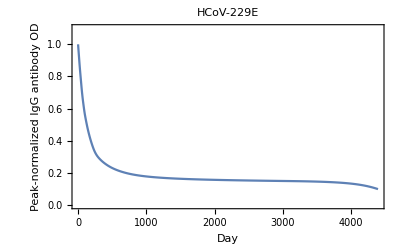

```mathematica
ListLinePlot[x229eantibodytimecourse,
PlotRange->{0, 1.1},
PlotLabel->"HCoV-229E",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized IgG antibody OD"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["HCoV-229E_nOD-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[x229eantibodytimecourse,
PlotRange->{0, 1.1},
PlotLabel->"HCoV-229E",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized IgG antibody OD"}]
]
```

HCoV-229E_nOD-by-Day_21Jan2021.pdf

```mathematica
x229elsfunc=Sum[(x229eantibodytimecourse[[index]]-(baseline+(1-baseline)*Exp[-lambda*index]))^2, {index, 1, Length[x229eantibodytimecourse]}]
```

(0.0999229-baseline-(1-baseline) ⅇ^(-4393 lambda))^2+(0.10006-baseline-(1-baseline) ⅇ^(-4392 lambda))^2+4390+(1-baseline-(1-baseline) ⅇ^-lambda)^2
 |  |  |  |

```mathematica
Length[x229eantibodytimecourse]
```

4393

```mathematica
Take[x229eantibodytimecourse, -1]
```

{0.0999229}

This estimate for the baseline S IgG antibody level for HCoV-229E of 0.0999229 goes into the the ancestral and descendent states analysis of the baselines for the zoonotic coronaviruses.

```mathematica
FindMinimum[{x229elsfunc,0<baseline≤.0999229,lambda >0}, {{baseline, 0.15},{lambda, 0.005}}
]
```

{12.9521,{baseline→0.0999229,lambda→0.0048135}}

This estimate of lambda for HCoV-229E of 0.0048135 goes into the the ancestral and descendent states analysis.

```mathematica
x229ehalflife=Log[2]/ lambda /.lambda->0.00481350458361269
```

144.001

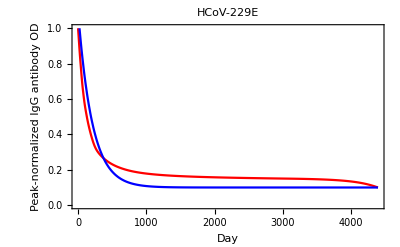

```mathematica
Show[
{ListLinePlot[x229eantibodytimecourse,
PlotStyle->Red,
PlotRange->{0,1}],Plot[baseline+Exp[-lambda days]/.{baseline->0.0999228974812187,lambda->0.00481350458361269},{days,1,Length[x229eantibodytimecourse]},
PlotStyle->Blue,
PlotRange->{0,1}]
},
PlotLabel->"HCoV-229E",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Peak-normalized IgG antibody OD"}]
```

```mathematica
x229eprobnoreinfectiontimecourse={1};
day=1;
AppendTo[x229eprobnoreinfectiontimecourse, 
x229eprobnoreinfectiontimecourse[[day]]*(1-x229eprobinfgivenaod[x229eantibodytimecourse[[day+1]]])
];

While[day<4393,
Increment[day];
AppendTo[x229eprobnoreinfectiontimecourse, 
If[day<lengthabtc,
x229eprobnoreinfectiontimecourse[[day]]*(1-x229eprobinfgivenaod[x229eantibodytimecourse[[day+1]] ]),
x229eprobnoreinfectiontimecourse[[day]]*(1-x229eprobinfgivenaod[x229eantibodytimecourse[[lengthabtc]]])
]
]
];

x229eprobnoreinfectiontimecourse
```

{1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999997,0.999997,0.999997,0.999997,0.999996,0.999996,0.999996,0.999996,0.999995,0.999995,0.999995,0.999994,0.999994,0.999993,0.999993,0.999993,0.999992,0.999992,0.999991,0.99999,0.99999,0.999989,0.999988,0.999988,0.999987,0.999986,0.999985,0.999984,0.999984,0.999983,0.999982,0.99998,0.999979,0.999978,0.999977,0.999976,0.999974,0.999973,0.999972,0.99997,0.999968,0.999967,0.999965,0.999963,0.999961,0.999959,0.999957,0.999955,0.999953,0.999951,0.999948,0.999946,0.999943,0.999941,0.999938,0.999935,0.999932,0.999929,0.999926,0.999923,0.999919,0.999916,0.999912,0.999909,0.999905,0.999901,0.999897,0.999893,0.999888,0.999884,0.999879,0.999874,0.99987,0.999864,0.999859,0.999854,0.999848,0.999843,0.999837,0.999831,0.999824,0.999818,0.999811,0.999805,0.999798,0.99979,0.999783,0.999775,0.999767,0.999759,0.999751,0.999743,0.999734,0.999725,0.999715,0.999706,0.999696,0.999686,0.999676,0.999665,0.999654,0.999643,0.999632,0.99962,0.999608,0.999596,0.999583,0.99957,0.999557,0.999544,0.99953,0.999515,0.999501,0.999486,0.999471,0.999455,0.999439,0.999423,0.999406,0.999389,0.999371,0.999354,0.999335,0.999317,0.999297,0.999278,0.999258,0.999237,0.999217,0.999195,0.999173,0.999151,0.999129,0.999105,0.999082,0.999057,0.999033,0.999007,0.998982,0.998955,0.998929,0.998901,0.998873,0.998845,0.998816,0.998786,0.998756,0.998725,0.998694,0.998662,0.998629,0.998596,0.998562,0.998528,0.998493,0.998457,0.99842,0.998383,0.998345,0.998307,0.998267,0.998227,0.998187,0.998145,0.998103,0.99806,0.998017,0.997972,0.997927,0.997881,0.997834,0.997787,0.997739,0.997689,0.997639,0.997589,0.997537,0.997485,0.997432,0.997377,0.997322,0.997267,0.99721,0.997152,0.997094,0.997035,0.996975,0.996914,0.996852,0.996789,0.996725,0.996661,0.996595,0.996529,0.996462,0.996394,0.996325,0.996255,0.996184,0.996113,0.99604,0.995967,0.995892,0.995817,0.995741,0.995664,0.995586,0.995507,0.995428,0.995347,0.995266,0.995183,0.9951,0.995016,0.994931,0.994845,0.994758,0.99467,0.994582,0.994492,0.994402,0.994311,0.994219,0.994126,0.994032,0.993937,0.993842,0.993745,0.993648,0.99355,0.993451,0.993351,0.99325,0.993149,0.993046,0.992943,0.992839,0.992734,0.992628,0.992522,0.992414,0.992306,0.992197,0.992087,0.991976,0.991864,0.991752,0.991639,0.991524,0.991409,0.991294,0.991177,0.99106,0.990941,0.990822,0.990702,0.990582,0.99046,0.990338,0.990215,0.990091,0.989966,0.98984,0.989713,0.989586,0.989458,0.989329,0.989199,0.989068,0.988937,0.988805,0.988671,0.988537,0.988403,0.988267,0.98813,0.987993,0.987855,0.987716,0.987576,0.987436,0.987294,0.987152,0.987009,0.986865,0.98672,0.986574,0.986428,0.986281,0.986132,0.985984,0.985834,0.985683,0.985532,0.985379,0.985226,0.985072,0.984918,0.984762,0.984605,0.984448,0.98429,0.984131,0.983971,0.983811,0.983649,0.983487,0.983324,0.98316,0.982995,0.982829,0.982663,0.982495,0.982327,0.982158,0.981988,0.981818,0.981646,0.981474,0.981301,0.981126,0.980952,0.980776,0.980599,0.980422,0.980244,0.980064,0.979885,0.979704,0.979522,0.97934,0.979156,0.978972,0.978787,0.978601,0.978415,0.978227,0.978039,0.977849,0.977659,0.977468,0.977277,0.977084,0.976891,0.976696,0.976501,0.976305,0.976108,0.975911,0.975712,0.975513,0.975313,0.975111,0.97491,0.974707,0.974503,0.974299,0.974093,0.973887,0.97368,0.973472,0.973264,0.973054,0.972844,0.972632,0.97242,0.972207,0.971994,0.971779,0.971563,0.971347,0.97113,0.970912,0.970693,0.970473,0.970253,0.970031,0.969809,0.969586,0.969362,0.969137,0.968911,0.968685,0.968457,0.968229,0.968,0.96777,0.967539,0.967308,0.967075,0.966842,0.966608,0.966373,0.966137,0.965901,0.965663,0.965425,0.965186,0.964946,0.964705,0.964464,0.964221,0.963978,0.963734,0.963489,0.963243,0.962997,0.962749,0.962501,0.962252,0.962002,0.961752,0.9615,0.961248,0.960995,0.960741,0.960486,0.960231,0.959974,0.959717,0.959459,0.959201,0.958941,0.958681,0.958419,0.958157,0.957895,0.957631,0.957367,0.957101,0.956835,0.956569,0.956301,0.956033,0.955763,0.955494,0.955223,0.954951,0.954679,0.954406,0.954132,0.953857,0.953582,0.953305,0.953028,0.952751,0.952472,0.952193,0.951913,0.951632,0.95135,0.951067,0.950784,0.9505,0.950215,0.94993,0.949644,0.949357,0.949069,0.94878,0.948491,0.948201,0.94791,0.947618,0.947326,0.947033,0.946739,0.946444,0.946149,0.945853,0.945556,0.945258,0.94496,0.944661,0.944361,0.94406,0.943759,0.943457,0.943154,0.942851,0.942546,0.942241,0.941936,0.941629,0.941322,0.941014,0.940706,0.940396,0.940086,0.939775,0.939464,0.939152,0.938839,0.938525,0.938211,0.937896,0.93758,0.937263,0.936946,0.936628,0.93631,0.93599,0.93567,0.93535,0.935028,0.934706,0.934383,0.93406,0.933736,0.933411,0.933085,0.932759,0.932432,0.932105,0.931776,0.931447,0.931118,0.930787,0.930456,0.930125,0.929792,0.929459,0.929126,0.928791,0.928456,0.928121,0.927784,0.927447,0.92711,0.926771,0.926432,0.926093,0.925752,0.925411,0.92507,0.924727,0.924385,0.924041,0.923697,0.923352,0.923006,0.92266,0.922314,0.921966,0.921618,0.921269,0.92092,0.92057,0.92022,0.919869,0.919517,0.919164,0.918811,0.918458,0.918103,0.917748,0.917393,0.917037,0.91668,0.916323,0.915965,0.915606,0.915247,0.914887,0.914527,0.914166,0.913804,0.913442,0.913079,0.912716,0.912352,0.911987,0.911622,0.911256,0.91089,0.910523,0.910155,0.909787,0.909418,0.909049,0.908679,0.908309,0.907938,0.907566,0.907194,0.906822,0.906448,0.906074,0.9057,0.905325,0.904949,0.904573,0.904197,0.90382,0.903442,0.903063,0.902685,0.902305,0.901925,0.901545,0.901164,0.900782,0.9004,0.900017,0.899634,0.89925,0.898866,0.898481,0.898096,0.89771,0.897323,0.896936,0.896549,0.896161,0.895772,0.895383,0.894994,0.894604,0.894213,0.893822,0.89343,0.893038,0.892646,0.892253,0.891859,0.891465,0.89107,0.890675,0.890279,0.889883,0.889486,0.889089,0.888692,0.888293,0.887895,0.887496,0.887096,0.886696,0.886295,0.885894,0.885493,0.885091,0.884688,0.884285,0.883882,0.883478,0.883073,0.882669,0.882263,0.881857,0.881451,0.881044,0.880637,0.88023,0.879822,0.879413,0.879004,0.878594,0.878185,0.877774,0.877363,0.876952,0.87654,0.876128,0.875716,0.875303,0.874889,0.874475,0.874061,0.873646,0.873231,0.872815,0.872399,0.871983,0.871566,0.871149,0.870731,0.870313,0.869894,0.869475,0.869056,0.868636,0.868216,0.867795,0.867374,0.866953,0.866531,0.866109,0.865686,0.865263,0.86484,0.864416,0.863992,0.863568,0.863143,0.862717,0.862292,0.861866,0.861439,0.861012,0.860585,0.860158,0.85973,0.859302,0.858873,0.858444,0.858015,0.857585,0.857155,0.856724,0.856294,0.855862,0.855431,0.854999,0.854567,0.854134,0.853702,0.853268,0.852835,0.852401,0.851967,0.851532,0.851097,0.850662,0.850227,0.849791,0.849354,0.848918,0.848481,0.848044,0.847606,0.847169,0.846731,0.846292,0.845853,0.845414,0.844975,0.844535,0.844095,0.843655,0.843214,0.842774,0.842332,0.841891,0.841449,0.841007,0.840565,0.840122,0.839679,0.839236,0.838793,0.838349,0.837905,0.83746,0.837016,0.836571,0.836126,0.83568,0.835235,0.834789,0.834343,0.833896,0.833449,0.833002,0.832555,0.832107,0.83166,0.831212,0.830763,0.830315,0.829866,0.829417,0.828967,0.828518,0.828068,0.827618,0.827168,0.826717,0.826266,0.825815,0.825364,0.824913,0.824461,0.824009,0.823557,0.823104,0.822652,0.822199,0.821746,0.821293,0.820839,0.820385,0.819931,0.819477,0.819023,0.818568,0.818113,0.817658,0.817203,0.816748,0.816292,0.815836,0.81538,0.814924,0.814468,0.814011,0.813554,0.813097,0.81264,0.812182,0.811725,0.811267,0.810809,0.810351,0.809893,0.809434,0.808975,0.808516,0.808057,0.807598,0.807139,0.806679,0.806219,0.805759,0.805299,0.804839,0.804379,0.803918,0.803457,0.802996,0.802535,0.802074,0.801612,0.801151,0.800689,0.800227,0.799765,0.799303,0.798841,0.798378,0.797915,0.797453,0.79699,0.796527,0.796063,0.7956,0.795136,0.794673,0.794209,0.793745,0.793281,0.792817,0.792353,0.791888,0.791423,0.790959,0.790494,0.790029,0.789564,0.789099,0.788633,0.788168,0.787702,0.787237,0.786771,0.786305,0.785839,0.785373,0.784906,0.78444,0.783973,0.783507,0.78304,0.782573,0.782106,0.781639,0.781172,0.780705,0.780238,0.77977,0.779303,0.778835,0.778367,0.7779,0.777432,0.776964,0.776496,0.776028,0.775559,0.775091,0.774623,0.774154,0.773685,0.773217,0.772748,0.772279,0.77181,0.771341,0.770872,0.770403,0.769934,0.769465,0.768995,0.768526,0.768056,0.767587,0.767117,0.766647,0.766178,0.765708,0.765238,0.764768,0.764298,0.763828,0.763358,0.762887,0.762417,0.761947,0.761477,0.761006,0.760536,0.760065,0.759595,0.759124,0.758653,0.758183,0.757712,0.757241,0.75677,0.756299,0.755828,0.755358,0.754887,0.754415,0.753944,0.753473,0.753002,0.752531,0.75206,0.751589,0.751117,0.750646,0.750175,0.749703,0.749232,0.74876,0.748289,0.747818,0.747346,0.746875,0.746403,0.745931,0.74546,0.744988,0.744517,0.744045,0.743573,0.743102,0.74263,0.742158,0.741687,0.741215,0.740743,0.740272,0.7398,0.739328,0.738856,0.738385,0.737913,0.737441,0.736969,0.736498,0.736026,0.735554,0.735082,0.734611,0.734139,0.733667,0.733196,0.732724,0.732252,0.73178,0.731309,0.730837,0.730365,0.729894,0.729422,0.72895,0.728479,0.728007,0.727536,0.727064,0.726592,0.726121,0.725649,0.725178,0.724706,0.724235,0.723763,0.723292,0.722821,0.722349,0.721878,0.721407,0.720935,0.720464,0.719993,0.719522,0.71905,0.718579,0.718108,0.717637,0.717166,0.716695,0.716224,0.715753,0.715282,0.714812,0.714341,0.71387,0.713399,0.712929,0.712458,0.711987,0.711517,0.711046,0.710576,0.710105,0.709635,0.709165,0.708694,0.708224,0.707754,0.707284,0.706814,0.706344,0.705874,0.705404,0.704934,0.704464,0.703994,0.703525,0.703055,0.702586,0.702116,0.701647,0.701177,0.700708,0.700239,0.699769,0.6993,0.698831,0.698362,0.697893,0.697424,0.696955,0.696487,0.696018,0.695549,0.695081,0.694612,0.694144,0.693676,0.693207,0.692739,0.692271,0.691803,0.691335,0.690867,0.690399,0.689931,0.689464,0.688996,0.688529,0.688061,0.687594,0.687127,0.68666,0.686192,0.685725,0.685258,0.684792,0.684325,0.683858,0.683392,0.682925,0.682459,0.681992,0.681526,0.68106,0.680594,0.680128,0.679662,0.679196,0.678731,0.678265,0.677799,0.677334,0.676869,0.676403,0.675938,0.675473,0.675008,0.674544,0.674079,0.673614,0.67315,0.672685,0.672221,0.671757,0.671292,0.670828,0.670364,0.669901,0.669437,0.668973,0.66851,0.668046,0.667583,0.66712,0.666657,0.666194,0.665731,0.665268,0.664806,0.664343,0.663881,0.663418,0.662956,0.662494,0.662032,0.66157,0.661108,0.660647,0.660185,0.659724,0.659263,0.658801,0.65834,0.657879,0.657419,0.656958,0.656497,0.656037,0.655577,0.655116,0.654656,0.654196,0.653736,0.653277,0.652817,0.652358,0.651898,0.651439,0.65098,0.650521,0.650062,0.649603,0.649145,0.648686,0.648228,0.64777,0.647312,0.646854,0.646396,0.645938,0.645481,0.645023,0.644566,0.644109,0.643652,0.643195,0.642738,0.642282,0.641825,0.641369,0.640912,0.640456,0.64,0.639545,0.639089,0.638633,0.638178,0.637723,0.637268,0.636813,0.636358,0.635903,0.635449,0.634994,0.63454,0.634086,0.633632,0.633178,0.632724,0.632271,0.631817,0.631364,0.630911,0.630458,0.630005,0.629553,0.6291,0.628648,0.628196,0.627743,0.627292,0.62684,0.626388,0.625937,0.625485,0.625034,0.624583,0.624132,0.623682,0.623231,0.622781,0.62233,0.62188,0.62143,0.62098,0.620531,0.620081,0.619632,0.619183,0.618734,0.618285,0.617836,0.617388,0.616939,0.616491,0.616043,0.615595,0.615147,0.6147,0.614252,0.613805,0.613358,0.612911,0.612464,0.612018,0.611571,0.611125,0.610679,0.610233,0.609787,0.609341,0.608896,0.608451,0.608005,0.60756,0.607116,0.606671,0.606227,0.605782,0.605338,0.604894,0.60445,0.604007,0.603563,0.60312,0.602677,0.602234,0.601791,0.601348,0.600906,0.600464,0.600021,0.59958,0.599138,0.598696,0.598255,0.597814,0.597372,0.596932,0.596491,0.59605,0.59561,0.59517,0.59473,0.59429,0.59385,0.593411,0.592971,0.592532,0.592093,0.591654,0.591216,0.590777,0.590339,0.589901,0.589463,0.589025,0.588588,0.58815,0.587713,0.587276,0.586839,0.586403,0.585966,0.58553,0.585094,0.584658,0.584222,0.583787,0.583351,0.582916,0.582481,0.582046,0.581612,0.581177,0.580743,0.580309,0.579875,0.579441,0.579008,0.578574,0.578141,0.577708,0.577275,0.576843,0.57641,0.575978,0.575546,0.575114,0.574682,0.574251,0.57382,0.573388,0.572958,0.572527,0.572096,0.571666,0.571236,0.570806,0.570376,0.569946,0.569517,0.569088,0.568659,0.56823,0.567801,0.567373,0.566945,0.566517,0.566089,0.565662,0.565235,0.564808,0.564382,0.563956,0.56353,0.563105,0.56268,0.562255,0.561831,0.561407,0.560983,0.56056,0.560136,0.559714,0.559291,0.558869,0.558447,0.558026,0.557605,0.557184,0.556763,0.556343,0.555923,0.555503,0.555084,0.554665,0.554246,0.553828,0.55341,0.552992,0.552575,0.552158,0.551741,0.551325,0.550908,0.550493,0.550077,0.549662,0.549247,0.548832,0.548418,0.548004,0.547591,0.547177,0.546764,0.546352,0.545939,0.545527,0.545115,0.544704,0.544293,0.543882,0.543471,0.543061,0.542651,0.542242,0.541832,0.541424,0.541015,0.540606,0.540198,0.539791,0.539383,0.538976,0.538569,0.538163,0.537757,0.537351,0.536945,0.53654,0.536135,0.53573,0.535326,0.534922,0.534518,0.534115,0.533711,0.533309,0.532906,0.532504,0.532102,0.5317,0.531299,0.530898,0.530497,0.530097,0.529697,0.529297,0.528897,0.528498,0.528099,0.527701,0.527302,0.526904,0.526507,0.526109,0.525712,0.525315,0.524919,0.524523,0.524127,0.523731,0.523336,0.522941,0.522546,0.522152,0.521757,0.521364,0.52097,0.520577,0.520184,0.519791,0.519399,0.519007,0.518615,0.518224,0.517833,0.517442,0.517051,0.516661,0.516271,0.515881,0.515492,0.515103,0.514714,0.514325,0.513937,0.513549,0.513162,0.512774,0.512387,0.512001,0.511614,0.511228,0.510842,0.510457,0.510071,0.509686,0.509302,0.508917,0.508533,0.508149,0.507766,0.507382,0.506999,0.506617,0.506234,0.505852,0.50547,0.505089,0.504708,0.504327,0.503946,0.503566,0.503186,0.502806,0.502426,0.502047,0.501668,0.501289,0.500911,0.500533,0.500155,0.499778,0.4994,0.499023,0.498647,0.49827,0.497894,0.497519,0.497143,0.496768,0.496393,0.496018,0.495644,0.49527,0.494896,0.494522,0.494149,0.493776,0.493403,0.493031,0.492659,0.492287,0.491915,0.491544,0.491173,0.490802,0.490432,0.490062,0.489692,0.489322,0.488953,0.488584,0.488215,0.487846,0.487478,0.48711,0.486743,0.486375,0.486008,0.485641,0.485275,0.484908,0.484542,0.484177,0.483811,0.483446,0.483081,0.482716,0.482352,0.481988,0.481624,0.481261,0.480897,0.480535,0.480172,0.479809,0.479447,0.479085,0.478724,0.478362,0.478001,0.477641,0.47728,0.47692,0.47656,0.4762,0.475841,0.475481,0.475123,0.474764,0.474406,0.474048,0.47369,0.473332,0.472975,0.472618,0.472261,0.471905,0.471549,0.471193,0.470837,0.470482,0.470126,0.469772,0.469417,0.469063,0.468709,0.468355,0.468001,0.467648,0.467295,0.466942,0.46659,0.466238,0.465886,0.465534,0.465183,0.464832,0.464481,0.46413,0.46378,0.46343,0.46308,0.462731,0.462381,0.462032,0.461684,0.461335,0.460987,0.460639,0.460291,0.459944,0.459597,0.45925,0.458903,0.458557,0.458211,0.457865,0.457519,0.457174,0.456829,0.456484,0.456139,0.455795,0.455451,0.455107,0.454764,0.454421,0.454078,0.453735,0.453392,0.45305,0.452708,0.452366,0.452025,0.451684,0.451343,0.451002,0.450662,0.450322,0.449982,0.449642,0.449303,0.448964,0.448625,0.448286,0.447948,0.44761,0.447272,0.446934,0.446597,0.44626,0.445923,0.445586,0.44525,0.444914,0.444578,0.444243,0.443907,0.443572,0.443237,0.442903,0.442568,0.442234,0.441901,0.441567,0.441234,0.440901,0.440568,0.440235,0.439903,0.439571,0.439239,0.438908,0.438577,0.438245,0.437915,0.437584,0.437254,0.436924,0.436594,0.436264,0.435935,0.435606,0.435277,0.434949,0.434621,0.434292,0.433965,0.433637,0.43331,0.432983,0.432656,0.432329,0.432003,0.431677,0.431351,0.431026,0.4307,0.430375,0.43005,0.429726,0.429401,0.429077,0.428753,0.42843,0.428106,0.427783,0.42746,0.427138,0.426815,0.426493,0.426171,0.42585,0.425528,0.425207,0.424886,0.424565,0.424245,0.423925,0.423605,0.423285,0.422965,0.422646,0.422327,0.422008,0.42169,0.421372,0.421054,0.420736,0.420418,0.420101,0.419784,0.419467,0.41915,0.418834,0.418518,0.418202,0.417886,0.417571,0.417256,0.416941,0.416626,0.416311,0.415997,0.415683,0.415369,0.415056,0.414743,0.41443,0.414117,0.413804,0.413492,0.41318,0.412868,0.412556,0.412245,0.411934,0.411623,0.411312,0.411002,0.410691,0.410381,0.410072,0.409762,0.409453,0.409144,0.408835,0.408526,0.408218,0.40791,0.407602,0.407294,0.406987,0.40668,0.406373,0.406066,0.40576,0.405453,0.405147,0.404842,0.404536,0.404231,0.403926,0.403621,0.403316,0.403012,0.402707,0.402403,0.4021,0.401796,0.401493,0.40119,0.400887,0.400584,0.400282,0.39998,0.399678,0.399376,0.399075,0.398774,0.398473,0.398172,0.397871,0.397571,0.397271,0.396971,0.396672,0.396372,0.396073,0.395774,0.395475,0.395177,0.394878,0.39458,0.394283,0.393985,0.393688,0.39339,0.393094,0.392797,0.3925,0.392204,0.391908,0.391612,0.391317,0.391021,0.390726,0.390431,0.390137,0.389842,0.389548,0.389254,0.38896,0.388666,0.388373,0.38808,0.387787,0.387494,0.387202,0.38691,0.386617,0.386326,0.386034,0.385743,0.385452,0.385161,0.38487,0.384579,0.384289,0.383999,0.383709,0.38342,0.38313,0.382841,0.382552,0.382263,0.381975,0.381686,0.381398,0.38111,0.380823,0.380535,0.380248,0.379961,0.379674,0.379388,0.379101,0.378815,0.378529,0.378244,0.377958,0.377673,0.377388,0.377103,0.376818,0.376534,0.37625,0.375966,0.375682,0.375398,0.375115,0.374832,0.374549,0.374266,0.373984,0.373701,0.373419,0.373138,0.372856,0.372574,0.372293,0.372012,0.371731,0.371451,0.37117,0.37089,0.37061,0.370331,0.370051,0.369772,0.369493,0.369214,0.368935,0.368657,0.368378,0.3681,0.367822,0.367545,0.367267,0.36699,0.366713,0.366436,0.36616,0.365883,0.365607,0.365331,0.365056,0.36478,0.364505,0.36423,0.363955,0.36368,0.363405,0.363131,0.362857,0.362583,0.36231,0.362036,0.361763,0.36149,0.361217,0.360944,0.360672,0.3604,0.360128,0.359856,0.359584,0.359313,0.359041,0.35877,0.3585,0.358229,0.357959,0.357688,0.357419,0.357149,0.356879,0.35661,0.356341,0.356072,0.355803,0.355534,0.355266,0.354998,0.35473,0.354462,0.354195,0.353927,0.35366,0.353393,0.353126,0.35286,0.352594,0.352327,0.352061,0.351796,0.35153,0.351265,0.351,0.350735,0.35047,0.350206,0.349941,0.349677,0.349413,0.349149,0.348886,0.348623,0.348359,0.348096,0.347834,0.347571,0.347309,0.347047,0.346785,0.346523,0.346261,0.346,0.345739,0.345478,0.345217,0.344957,0.344696,0.344436,0.344176,0.343916,0.343657,0.343397,0.343138,0.342879,0.34262,0.342362,0.342103,0.341845,0.341587,0.341329,0.341072,0.340814,0.340557,0.3403,0.340043,0.339786,0.33953,0.339274,0.339018,0.338762,0.338506,0.33825,0.337995,0.33774,0.337485,0.33723,0.336976,0.336721,0.336467,0.336213,0.33596,0.335706,0.335453,0.335199,0.334946,0.334694,0.334441,0.334188,0.333936,0.333684,0.333432,0.333181,0.332929,0.332678,0.332427,0.332176,0.331925,0.331675,0.331424,0.331174,0.330924,0.330674,0.330425,0.330175,0.329926,0.329677,0.329428,0.32918,0.328931,0.328683,0.328435,0.328187,0.327939,0.327692,0.327444,0.327197,0.32695,0.326703,0.326457,0.32621,0.325964,0.325718,0.325472,0.325227,0.324981,0.324736,0.324491,0.324246,0.324001,0.323757,0.323512,0.323268,0.323024,0.32278,0.322537,0.322293,0.32205,0.321807,0.321564,0.321321,0.321079,0.320836,0.320594,0.320352,0.32011,0.319869,0.319627,0.319386,0.319145,0.318904,0.318663,0.318423,0.318182,0.317942,0.317702,0.317463,0.317223,0.316983,0.316744,0.316505,0.316266,0.316027,0.315789,0.315551,0.315312,0.315074,0.314837,0.314599,0.314362,0.314124,0.313887,0.31365,0.313413,0.313177,0.312941,0.312704,0.312468,0.312232,0.311997,0.311761,0.311526,0.311291,0.311056,0.310821,0.310586,0.310352,0.310118,0.309884,0.30965,0.309416,0.309183,0.308949,0.308716,0.308483,0.30825,0.308017,0.307785,0.307553,0.307321,0.307089,0.306857,0.306625,0.306394,0.306162,0.305931,0.3057,0.30547,0.305239,0.305009,0.304779,0.304548,0.304319,0.304089,0.303859,0.30363,0.303401,0.303172,0.302943,0.302714,0.302486,0.302258,0.302029,0.301801,0.301574,0.301346,0.301119,0.300891,0.300664,0.300437,0.30021,0.299984,0.299757,0.299531,0.299305,0.299079,0.298853,0.298628,0.298402,0.298177,0.297952,0.297727,0.297503,0.297278,0.297054,0.296829,0.296605,0.296381,0.296158,0.295934,0.295711,0.295488,0.295265,0.295042,0.294819,0.294597,0.294374,0.294152,0.29393,0.293708,0.293486,0.293265,0.293044,0.292822,0.292601,0.29238,0.29216,0.291939,0.291719,0.291499,0.291279,0.291059,0.290839,0.29062,0.2904,0.290181,0.289962,0.289743,0.289524,0.289306,0.289088,0.288869,0.288651,0.288433,0.288216,0.287998,0.287781,0.287564,0.287347,0.28713,0.286913,0.286696,0.28648,0.286264,0.286048,0.285832,0.285616,0.2854,0.285185,0.28497,0.284755,0.28454,0.284325,0.28411,0.283896,0.283682,0.283468,0.283254,0.28304,0.282826,0.282613,0.282399,0.282186,0.281973,0.28176,0.281548,0.281335,0.281123,0.280911,0.280699,0.280487,0.280275,0.280063,0.279852,0.279641,0.27943,0.279219,0.279008,0.278798,0.278587,0.278377,0.278167,0.277957,0.277747,0.277537,0.277328,0.277118,0.276909,0.2767,0.276491,0.276283,0.276074,0.275866,0.275658,0.27545,0.275242,0.275034,0.274826,0.274619,0.274412,0.274204,0.273997,0.273791,0.273584,0.273378,0.273171,0.272965,0.272759,0.272553,0.272347,0.272142,0.271936,0.271731,0.271526,0.271321,0.271116,0.270912,0.270707,0.270503,0.270299,0.270095,0.269891,0.269687,0.269484,0.26928,0.269077,0.268874,0.268671,0.268468,0.268265,0.268063,0.267861,0.267658,0.267456,0.267254,0.267053,0.266851,0.26665,0.266449,0.266247,0.266046,0.265846,0.265645,0.265444,0.265244,0.265044,0.264844,0.264644,0.264444,0.264245,0.264045,0.263846,0.263647,0.263448,0.263249,0.26305,0.262852,0.262653,0.262455,0.262257,0.262059,0.261861,0.261663,0.261466,0.261269,0.261071,0.260874,0.260677,0.260481,0.260284,0.260088,0.259891,0.259695,0.259499,0.259303,0.259107,0.258912,0.258716,0.258521,0.258326,0.258131,0.257936,0.257742,0.257547,0.257353,0.257158,0.256964,0.25677,0.256577,0.256383,0.256189,0.255996,0.255803,0.25561,0.255417,0.255224,0.255031,0.254839,0.254646,0.254454,0.254262,0.25407,0.253879,0.253687,0.253495,0.253304,0.253113,0.252922,0.252731,0.25254,0.25235,0.252159,0.251969,0.251779,0.251589,0.251399,0.251209,0.251019,0.25083,0.25064,0.250451,0.250262,0.250073,0.249885,0.249696,0.249507,0.249319,0.249131,0.248943,0.248755,0.248567,0.24838,0.248192,0.248005,0.247818,0.247631,0.247444,0.247257,0.24707,0.246884,0.246697,0.246511,0.246325,0.246139,0.245953,0.245768,0.245582,0.245397,0.245212,0.245027,0.244842,0.244657,0.244472,0.244288,0.244103,0.243919,0.243735,0.243551,0.243367,0.243183,0.243,0.242817,0.242633,0.24245,0.242267,0.242084,0.241902,0.241719,0.241536,0.241354,0.241172,0.24099,0.240808,0.240626,0.240445,0.240263,0.240082,0.239901,0.23972,0.239539,0.239358,0.239177,0.238997,0.238816,0.238636,0.238456,0.238276,0.238096,0.237916,0.237737,0.237557,0.237378,0.237199,0.23702,0.236841,0.236662,0.236483,0.236305,0.236127,0.235948,0.23577,0.235592,0.235414,0.235237,0.235059,0.234882,0.234705,0.234527,0.23435,0.234173,0.233997,0.23382,0.233644,0.233467,0.233291,0.233115,0.232939,0.232763,0.232587,0.232412,0.232237,0.232061,0.231886,0.231711,0.231536,0.231361,0.231187,0.231012,0.230838,0.230664,0.23049,0.230316,0.230142,0.229968,0.229794,0.229621,0.229448,0.229274,0.229101,0.228929,0.228756,0.228583,0.228411,0.228238,0.228066,0.227894,0.227722,0.22755,0.227378,0.227206,0.227035,0.226864,0.226692,0.226521,0.22635,0.226179,0.226009,0.225838,0.225668,0.225497,0.225327,0.225157,0.224987,0.224817,0.224648,0.224478,0.224309,0.224139,0.22397,0.223801,0.223632,0.223463,0.223295,0.223126,0.222958,0.222789,0.222621,0.222453,0.222285,0.222118,0.22195,0.221782,0.221615,0.221448,0.22128,0.221113,0.220947,0.22078,0.220613,0.220447,0.22028,0.220114,0.219948,0.219782,0.219616,0.21945,0.219285,0.219119,0.218954,0.218788,0.218623,0.218458,0.218293,0.218129,0.217964,0.217799,0.217635,0.217471,0.217307,0.217143,0.216979,0.216815,0.216651,0.216488,0.216324,0.216161,0.215998,0.215835,0.215672,0.215509,0.215346,0.215184,0.215022,0.214859,0.214697,0.214535,0.214373,0.214211,0.21405,0.213888,0.213727,0.213565,0.213404,0.213243,0.213082,0.212921,0.21276,0.2126,0.212439,0.212279,0.212119,0.211959,0.211799,0.211639,0.211479,0.211319,0.21116,0.211001,0.210841,0.210682,0.210523,0.210364,0.210206,0.210047,0.209888,0.20973,0.209572,0.209413,0.209255,0.209097,0.20894,0.208782,0.208624,0.208467,0.208309,0.208152,0.207995,0.207838,0.207681,0.207524,0.207368,0.207211,0.207055,0.206899,0.206742,0.206586,0.20643,0.206275,0.206119,0.205963,0.205808,0.205653,0.205497,0.205342,0.205187,0.205032,0.204878,0.204723,0.204568,0.204414,0.20426,0.204106,0.203952,0.203798,0.203644,0.20349,0.203336,0.203183,0.20303,0.202876,0.202723,0.20257,0.202417,0.202265,0.202112,0.201959,0.201807,0.201655,0.201502,0.20135,0.201198,0.201046,0.200895,0.200743,0.200592,0.20044,0.200289,0.200138,0.199987,0.199836,0.199685,0.199534,0.199383,0.199233,0.199083,0.198932,0.198782,0.198632,0.198482,0.198332,0.198183,0.198033,0.197884,0.197734,0.197585,0.197436,0.197287,0.197138,0.196989,0.19684,0.196692,0.196543,0.196395,0.196247,0.196099,0.195951,0.195803,0.195655,0.195507,0.19536,0.195212,0.195065,0.194918,0.194771,0.194624,0.194477,0.19433,0.194183,0.194037,0.19389,0.193744,0.193598,0.193451,0.193305,0.19316,0.193014,0.192868,0.192723,0.192577,0.192432,0.192286,0.192141,0.191996,0.191851,0.191707,0.191562,0.191417,0.191273,0.191128,0.190984,0.19084,0.190696,0.190552,0.190408,0.190264,0.190121,0.189977,0.189834,0.189691,0.189547,0.189404,0.189261,0.189119,0.188976,0.188833,0.188691,0.188548,0.188406,0.188264,0.188122,0.18798,0.187838,0.187696,0.187554,0.187413,0.187271,0.18713,0.186989,0.186848,0.186707,0.186566,0.186425,0.186284,0.186143,0.186003,0.185863,0.185722,0.185582,0.185442,0.185302,0.185162,0.185022,0.184883,0.184743,0.184604,0.184464,0.184325,0.184186,0.184047,0.183908,0.183769,0.183631,0.183492,0.183354,0.183215,0.183077,0.182939,0.182801,0.182663,0.182525,0.182387,0.182249,0.182112,0.181974,0.181837,0.1817,0.181563,0.181425,0.181289,0.181152,0.181015,0.180878,0.180742,0.180605,0.180469,0.180333,0.180197,0.180061,0.179925,0.179789,0.179653,0.179518,0.179382,0.179247,0.179111,0.178976,0.178841,0.178706,0.178571,0.178437,0.178302,0.178167,0.178033,0.177898,0.177764,0.17763,0.177496,0.177362,0.177228,0.177094,0.176961,0.176827,0.176694,0.17656,0.176427,0.176294,0.176161,0.176028,0.175895,0.175762,0.175629,0.175497,0.175364,0.175232,0.1751,0.174968,0.174836,0.174704,0.174572,0.17444,0.174308,0.174177,0.174045,0.173914,0.173783,0.173651,0.17352,0.173389,0.173259,0.173128,0.172997,0.172867,0.172736,0.172606,0.172475,0.172345,0.172215,0.172085,0.171955,0.171825,0.171696,0.171566,0.171437,0.171307,0.171178,0.171049,0.17092,0.170791,0.170662,0.170533,0.170404,0.170276,0.170147,0.170019,0.16989,0.169762,0.169634,0.169506,0.169378,0.16925,0.169122,0.168995,0.168867,0.16874,0.168612,0.168485,0.168358,0.168231,0.168104,0.167977,0.16785,0.167723,0.167597,0.16747,0.167344,0.167218,0.167091,0.166965,0.166839,0.166713,0.166588,0.166462,0.166336,0.166211,0.166085,0.16596,0.165834,0.165709,0.165584,0.165459,0.165334,0.16521,0.165085,0.16496,0.164836,0.164711,0.164587,0.164463,0.164339,0.164215,0.164091,0.163967,0.163843,0.163719,0.163596,0.163472,0.163349,0.163226,0.163102,0.162979,0.162856,0.162733,0.162611,0.162488,0.162365,0.162243,0.16212,0.161998,0.161876,0.161753,0.161631,0.161509,0.161387,0.161266,0.161144,0.161022,0.160901,0.160779,0.160658,0.160537,0.160415,0.160294,0.160173,0.160052,0.159932,0.159811,0.15969,0.15957,0.159449,0.159329,0.159209,0.159089,0.158968,0.158848,0.158729,0.158609,0.158489,0.158369,0.15825,0.15813,0.158011,0.157892,0.157773,0.157654,0.157535,0.157416,0.157297,0.157178,0.157059,0.156941,0.156822,0.156704,0.156586,0.156468,0.15635,0.156232,0.156114,0.155996,0.155878,0.15576,0.155643,0.155525,0.155408,0.155291,0.155173,0.155056,0.154939,0.154822,0.154705,0.154589,0.154472,0.154355,0.154239,0.154122,0.154006,0.15389,0.153774,0.153658,0.153542,0.153426,0.15331,0.153194,0.153079,0.152963,0.152848,0.152732,0.152617,0.152502,0.152387,0.152272,0.152157,0.152042,0.151927,0.151812,0.151698,0.151583,0.151469,0.151355,0.15124,0.151126,0.151012,0.150898,0.150784,0.15067,0.150557,0.150443,0.15033,0.150216,0.150103,0.149989,0.149876,0.149763,0.14965,0.149537,0.149424,0.149311,0.149199,0.149086,0.148974,0.148861,0.148749,0.148636,0.148524,0.148412,0.1483,0.148188,0.148076,0.147965,0.147853,0.147741,0.14763,0.147518,0.147407,0.147296,0.147185,0.147073,0.146962,0.146852,0.146741,0.14663,0.146519,0.146409,0.146298,0.146188,0.146077,0.145967,0.145857,0.145747,0.145637,0.145527,0.145417,0.145307,0.145198,0.145088,0.144979,0.144869,0.14476,0.144651,0.144541,0.144432,0.144323,0.144214,0.144105,0.143997,0.143888,0.143779,0.143671,0.143562,0.143454,0.143346,0.143238,0.143129,0.143021,0.142913,0.142806,0.142698,0.14259,0.142482,0.142375,0.142267,0.14216,0.142053,0.141946,0.141838,0.141731,0.141624,0.141517,0.141411,0.141304,0.141197,0.141091,0.140984,0.140878,0.140771,0.140665,0.140559,0.140453,0.140347,0.140241,0.140135,0.140029,0.139924,0.139818,0.139713,0.139607,0.139502,0.139396,0.139291,0.139186,0.139081,0.138976,0.138871,0.138766,0.138662,0.138557,0.138452,0.138348,0.138243,0.138139,0.138035,0.137931,0.137826,0.137722,0.137618,0.137515,0.137411,0.137307,0.137203,0.1371,0.136996,0.136893,0.13679,0.136686,0.136583,0.13648,0.136377,0.136274,0.136171,0.136069,0.135966,0.135863,0.135761,0.135658,0.135556,0.135454,0.135351,0.135249,0.135147,0.135045,0.134943,0.134841,0.134739,0.134638,0.134536,0.134435,0.134333,0.134232,0.13413,0.134029,0.133928,0.133827,0.133726,0.133625,0.133524,0.133423,0.133323,0.133222,0.133121,0.133021,0.132921,0.13282,0.13272,0.13262,0.13252,0.13242,0.13232,0.13222,0.13212,0.13202,0.131921,0.131821,0.131722,0.131622,0.131523,0.131424,0.131324,0.131225,0.131126,0.131027,0.130928,0.130829,0.130731,0.130632,0.130533,0.130435,0.130336,0.130238,0.13014,0.130042,0.129943,0.129845,0.129747,0.129649,0.129552,0.129454,0.129356,0.129258,0.129161,0.129063,0.128966,0.128869,0.128771,0.128674,0.128577,0.12848,0.128383,0.128286,0.128189,0.128093,0.127996,0.127899,0.127803,0.127706,0.12761,0.127513,0.127417,0.127321,0.127225,0.127129,0.127033,0.126937,0.126841,0.126746,0.12665,0.126554,0.126459,0.126363,0.126268,0.126173,0.126077,0.125982,0.125887,0.125792,0.125697,0.125602,0.125507,0.125413,0.125318,0.125224,0.125129,0.125035,0.12494,0.124846,0.124752,0.124657,0.124563,0.124469,0.124375,0.124282,0.124188,0.124094,0.124,0.123907,0.123813,0.12372,0.123626,0.123533,0.12344,0.123347,0.123254,0.123161,0.123068,0.122975,0.122882,0.122789,0.122696,0.122604,0.122511,0.122419,0.122326,0.122234,0.122142,0.12205,0.121957,0.121865,0.121773,0.121682,0.12159,0.121498,0.121406,0.121315,0.121223,0.121131,0.12104,0.120949,0.120857,0.120766,0.120675,0.120584,0.120493,0.120402,0.120311,0.12022,0.12013,0.120039,0.119948,0.119858,0.119767,0.119677,0.119587,0.119496,0.119406,0.119316,0.119226,0.119136,0.119046,0.118956,0.118866,0.118777,0.118687,0.118597,0.118508,0.118418,0.118329,0.11824,0.11815,0.118061,0.117972,0.117883,0.117794,0.117705,0.117616,0.117528,0.117439,0.11735,0.117262,0.117173,0.117085,0.116996,0.116908,0.11682,0.116732,0.116644,0.116556,0.116468,0.11638,0.116292,0.116204,0.116116,0.116029,0.115941,0.115854,0.115766,0.115679,0.115591,0.115504,0.115417,0.11533,0.115243,0.115156,0.115069,0.114982,0.114895,0.114809,0.114722,0.114635,0.114549,0.114462,0.114376,0.11429,0.114203,0.114117,0.114031,0.113945,0.113859,0.113773,0.113687,0.113601,0.113516,0.11343,0.113344,0.113259,0.113173,0.113088,0.113002,0.112917,0.112832,0.112747,0.112662,0.112577,0.112492,0.112407,0.112322,0.112237,0.112152,0.112068,0.111983,0.111899,0.111814,0.11173,0.111645,0.111561,0.111477,0.111393,0.111309,0.111225,0.111141,0.111057,0.110973,0.110889,0.110806,0.110722,0.110638,0.110555,0.110471,0.110388,0.110305,0.110221,0.110138,0.110055,0.109972,0.109889,0.109806,0.109723,0.10964,0.109558,0.109475,0.109392,0.10931,0.109227,0.109145,0.109062,0.10898,0.108898,0.108816,0.108734,0.108651,0.108569,0.108487,0.108406,0.108324,0.108242,0.10816,0.108079,0.107997,0.107916,0.107834,0.107753,0.107671,0.10759,0.107509,0.107428,0.107347,0.107266,0.107185,0.107104,0.107023,0.106942,0.106861,0.106781,0.1067,0.10662,0.106539,0.106459,0.106378,0.106298,0.106218,0.106138,0.106058,0.105978,0.105898,0.105818,0.105738,0.105658,0.105578,0.105499,0.105419,0.105339,0.10526,0.10518,0.105101,0.105022,0.104942,0.104863,0.104784,0.104705,0.104626,0.104547,0.104468,0.104389,0.10431,0.104232,0.104153,0.104074,0.103996,0.103917,0.103839,0.10376,0.103682,0.103604,0.103526,0.103448,0.103369,0.103291,0.103213,0.103136,0.103058,0.10298,0.102902,0.102825,0.102747,0.102669,0.102592,0.102514,0.102437,0.10236,0.102283,0.102205,0.102128,0.102051,0.101974,0.101897,0.10182,0.101743,0.101667,0.10159,0.101513,0.101436,0.10136,0.101283,0.101207,0.101131,0.101054,0.100978,0.100902,0.100826,0.100749,0.100673,0.100597,0.100522,0.100446,0.10037,0.100294,0.100218,0.100143,0.100067,0.0999916,0.0999161,0.0998407,0.0997654,0.09969,0.0996148,0.0995396,0.0994645,0.0993894,0.0993144,0.0992394,0.0991645,0.0990897,0.0990149,0.0989401,0.0988655,0.0987908,0.0987163,0.0986418,0.0985673,0.0984929,0.0984186,0.0983443,0.0982701,0.0981959,0.0981218,0.0980477,0.0979737,0.0978997,0.0978258,0.097752,0.0976782,0.0976045,0.0975308,0.0974572,0.0973837,0.0973101,0.0972367,0.0971633,0.09709,0.0970167,0.0969435,0.0968703,0.0967972,0.0967241,0.0966511,0.0965781,0.0965052,0.0964324,0.0963596,0.0962869,0.0962142,0.0961416,0.096069,0.0959965,0.0959241,0.0958516,0.0957793,0.095707,0.0956348,0.0955626,0.0954905,0.0954184,0.0953464,0.0952744,0.0952025,0.0951306,0.0950588,0.0949871,0.0949154,0.0948437,0.0947721,0.0947006,0.0946291,0.0945577,0.0944863,0.094415,0.0943437,0.0942725,0.0942014,0.0941303,0.0940592,0.0939882,0.0939173,0.0938464,0.0937756,0.0937048,0.0936341,0.0935634,0.0934928,0.0934222,0.0933517,0.0932812,0.0932108,0.0931405,0.0930702,0.0929999,0.0929297,0.0928596,0.0927895,0.0927194,0.0926495,0.0925795,0.0925096,0.0924398,0.09237,0.0923003,0.0922307,0.092161,0.0920915,0.092022,0.0919525,0.0918831,0.0918137,0.0917444,0.0916752,0.091606,0.0915369,0.0914678,0.0913987,0.0913297,0.0912608,0.0911919,0.0911231,0.0910543,0.0909856,0.0909169,0.0908483,0.0907797,0.0907112,0.0906427,0.0905743,0.0905059,0.0904376,0.0903694,0.0903012,0.090233,0.0901649,0.0900968,0.0900288,0.0899609,0.089893,0.0898251,0.0897573,0.0896896,0.0896219,0.0895542,0.0894866,0.0894191,0.0893516,0.0892842,0.0892168,0.0891494,0.0890821,0.0890149,0.0889477,0.0888806,0.0888135,0.0887465,0.0886795,0.0886125,0.0885456,0.0884788,0.088412,0.0883453,0.0882786,0.088212,0.0881454,0.0880789,0.0880124,0.087946,0.0878796,0.0878132,0.087747,0.0876807,0.0876145,0.0875484,0.0874823,0.0874163,0.0873503,0.0872844,0.0872185,0.0871527,0.0870869,0.0870212,0.0869555,0.0868898,0.0868243,0.0867587,0.0866932,0.0866278,0.0865624,0.0864971,0.0864318,0.0863666,0.0863014,0.0862362,0.0861711,0.0861061,0.0860411,0.0859762,0.0859113,0.0858464,0.0857816,0.0857169,0.0856522,0.0855875,0.0855229,0.0854584,0.0853939,0.0853294,0.085265,0.0852007,0.0851363,0.0850721,0.0850079,0.0849437,0.0848796,0.0848155,0.0847515,0.0846875,0.0846236,0.0845597,0.0844959,0.0844321,0.0843684,0.0843047,0.0842411,0.0841775,0.084114,0.0840505,0.083987,0.0839236,0.0838603,0.083797,0.0837338,0.0836706,0.0836074,0.0835443,0.0834812,0.0834182,0.0833553,0.0832923,0.0832295,0.0831667,0.0831039,0.0830412,0.0829785,0.0829158,0.0828533,0.0827907,0.0827282,0.0826658,0.0826034,0.082541,0.0824787,0.0824165,0.0823543,0.0822921,0.08223,0.0821679,0.0821059,0.0820439,0.081982,0.0819201,0.0818583,0.0817965,0.0817348,0.0816731,0.0816114,0.0815498,0.0814883,0.0814268,0.0813653,0.0813039,0.0812425,0.0811812,0.0811199,0.0810587,0.0809975,0.0809364,0.0808753,0.0808143,0.0807533,0.0806923,0.0806314,0.0805705,0.0805097,0.080449,0.0803882,0.0803276,0.0802669,0.0802063,0.0801458,0.0800853,0.0800249,0.0799645,0.0799041,0.0798438,0.0797835,0.0797233,0.0796631,0.079603,0.0795429,0.0794829,0.0794229,0.0793629,0.079303,0.0792432,0.0791834,0.0791236,0.0790639,0.0790042,0.0789446,0.078885,0.0788254,0.0787659,0.0787065,0.0786471,0.0785877,0.0785284,0.0784691,0.0784099,0.0783507,0.0782916,0.0782325,0.0781734,0.0781144,0.0780555,0.0779966,0.0779377,0.0778789,0.0778201,0.0777613,0.0777026,0.077644,0.0775854,0.0775268,0.0774683,0.0774098,0.0773514,0.077293,0.0772347,0.0771764,0.0771181,0.0770599,0.0770018,0.0769436,0.0768856,0.0768275,0.0767695,0.0767116,0.0766537,0.0765958,0.076538,0.0764802,0.0764225,0.0763648,0.0763072,0.0762496,0.076192,0.0761345,0.0760771,0.0760197,0.0759623,0.0759049,0.0758476,0.0757904,0.0757332,0.075676,0.0756189,0.0755618,0.0755048,0.0754478,0.0753909,0.075334,0.0752771,0.0752203,0.0751635,0.0751068,0.0750501,0.0749934,0.0749368,0.0748803,0.0748237,0.0747673,0.0747108,0.0746544,0.0745981,0.0745418,0.0744855,0.0744293,0.0743731,0.074317,0.0742609,0.0742048,0.0741488,0.0740929,0.0740369,0.073981,0.0739252,0.0738694,0.0738137,0.0737579,0.0737023,0.0736466,0.073591,0.0735355,0.07348,0.0734245,0.0733691,0.0733137,0.0732584,0.0732031,0.0731479,0.0730926,0.0730375,0.0729823,0.0729273,0.0728722,0.0728172,0.0727622,0.0727073,0.0726524,0.0725976,0.0725428,0.0724881,0.0724333,0.0723787,0.072324,0.0722694,0.0722149,0.0721604,0.0721059,0.0720515,0.0719971,0.0719428,0.0718885,0.0718342,0.07178,0.0717258,0.0716717,0.0716176,0.0715635,0.0715095,0.0714555,0.0714016,0.0713477,0.0712938,0.07124,0.0711863,0.0711325,0.0710788,0.0710252,0.0709716,0.070918,0.0708645,0.070811,0.0707575,0.0707041,0.0706508,0.0705974,0.0705442,0.0704909,0.0704377,0.0703845,0.0703314,0.0702783,0.0702253,0.0701723,0.0701193,0.0700664,0.0700135,0.0699607,0.0699078,0.0698551,0.0698024,0.0697497,0.069697,0.0696444,0.0695918,0.0695393,0.0694868,0.0694344,0.069382,0.0693296,0.0692773,0.069225,0.0691727,0.0691205,0.0690684,0.0690162,0.0689641,0.0689121,0.0688601,0.0688081,0.0687561,0.0687042,0.0686524,0.0686006,0.0685488,0.0684971,0.0684454,0.0683937,0.0683421,0.0682905,0.0682389,0.0681874,0.068136,0.0680845,0.0680331,0.0679818,0.0679305,0.0678792,0.067828,0.0677768,0.0677256,0.0676745,0.0676234,0.0675724,0.0675214,0.0674704,0.0674195,0.0673686,0.0673177,0.0672669,0.0672162,0.0671654,0.0671147,0.0670641,0.0670135,0.0669629,0.0669123,0.0668618,0.0668114,0.0667609,0.0667105,0.0666602,0.0666099,0.0665596,0.0665094,0.0664592,0.066409,0.0663589,0.0663088,0.0662587,0.0662087,0.0661587,0.0661088,0.0660589,0.066009,0.0659592,0.0659094,0.0658597,0.06581,0.0657603,0.0657107,0.0656611,0.0656115,0.065562,0.0655125,0.0654631,0.0654136,0.0653643,0.0653149,0.0652656,0.0652164,0.0651671,0.065118,0.0650688,0.0650197,0.0649706,0.0649216,0.0648726,0.0648236,0.0647747,0.0647258,0.0646769,0.0646281,0.0645793,0.0645306,0.0644819,0.0644332,0.0643846,0.064336,0.0642874,0.0642389,0.0641904,0.064142,0.0640935,0.0640452,0.0639968,0.0639485,0.0639003,0.063852,0.0638038,0.0637557,0.0637075,0.0636595,0.0636114,0.0635634,0.0635154,0.0634675,0.0634196,0.0633717,0.0633239,0.0632761,0.0632283,0.0631806,0.0631329,0.0630852,0.0630376,0.06299,0.0629425,0.062895,0.0628475,0.0628001,0.0627527,0.0627053,0.062658,0.0626107,0.0625634,0.0625162,0.062469,0.0624219,0.0623748,0.0623277,0.0622806,0.0622336,0.0621867,0.0621397,0.0620928,0.0620459,0.0619991,0.0619523,0.0619056,0.0618588,0.0618121,0.0617655,0.0617189,0.0616723,0.0616257,0.0615792,0.0615327,0.0614863,0.0614399,0.0613935,0.0613472,0.0613009,0.0612546,0.0612084,0.0611622,0.061116,0.0610699,0.0610238,0.0609777,0.0609317,0.0608857,0.0608397,0.0607938,0.0607479,0.0607021,0.0606563,0.0606105,0.0605647,0.060519,0.0604733,0.0604277,0.0603821,0.0603365,0.060291,0.0602454,0.0602,0.0601545,0.0601091,0.0600638,0.0600184,0.0599731,0.0599279,0.0598826,0.0598374,0.0597923,0.0597471,0.059702,0.059657,0.0596119,0.0595669,0.059522,0.0594771,0.0594322,0.0593873,0.0593425,0.0592977,0.0592529,0.0592082,0.0591635,0.0591189,0.0590742,0.0590296,0.0589851,0.0589406,0.0588961,0.0588516,0.0588072,0.0587628}

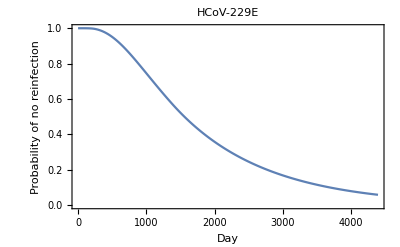

```mathematica
ListLinePlot[x229eprobnoreinfectiontimecourse, PlotRange->{0,1}, PlotLabel->"HCoV-229E", Frame->{{True, False}, {True, False}}, FrameLabel->{"Day", "Probability of no reinfection"}]
```

```mathematica
x229econtinuousprobnoreinfection=Interpolation[x229eprobnoreinfectiontimecourse]
```

InterpolatingFunction[…]

```mathematica
1-x229econtinuousprobnoreinfection[365]
```

0.0181824

```mathematica
{x, x/30, x/365}/.FindMinimum[{Abs[x229econtinuousprobnoreinfection[x]-0.95],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{503.755,16.7918,1.38015}

These are the 5% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.FindMinimum[{Abs[x229econtinuousprobnoreinfection[x]-0.50],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{1558.41,51.947,4.26962}

These are the 50% quantiles (medians) for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.FindMinimum[{Abs[x229econtinuousprobnoreinfection[x]-0.05],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{4390.,146.333,12.0274}

These are the 95% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
x229eprobreinfectiondensity={};
day=0;
While[day<4393,
Increment[day];
AppendTo[x229eprobreinfectiondensity, 
If[day<lengthabtc,
x229eprobinfgivenaod[x229eantibodytimecourse[[day]]]*x229eprobnoreinfectiontimecourse[[day]],
x229eprobinfgivenaod[x229eantibodytimecourse[[lengthabtc]]]*x229eprobnoreinfectiontimecourse[[day]]
]
]
];
```

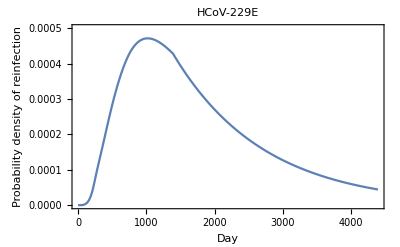

```mathematica
ListLinePlot[x229eprobreinfectiondensity,
PlotLabel->"HCoV-229E",
PlotRange->{0,0.0005},
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability density of reinfection"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["HCoV-229E_PrInf-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[x229eprobreinfectiondensity,
PlotLabel->"HCoV-229E",
PlotRange->{0,0.0005},
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability density of reinfection"}]
]
```

HCoV-229E_PrInf-by-Day_21Jan2021.pdf

## MERS

### MERS Average peak OD post-infection (3 mo.)

Input Data: ELIZA ODs for MERS S IgG antibodies from Alshukairi et al. 2016, “Antibody Response and Disease Severity in Healthcare Worker MERS Survivors”, Emerging Infectious Diseases.

```mathematica
mersavpeakOD=Mean[{3.17, 2.7, 2.91, 1.29, 3.2, 0.07, 0.046, 0.12, 0.07}]
```

1.50844

### MERS peak-normalized OD post-infection (3 mo.)

```mathematica
mersdata={
{1,90, MERS,3.17/mersavpeakOD,  TRUE,NA, NA},
{1.1,300, MERS,2.99/mersavpeakOD, FALSE, (300-90), (2.99/mersavpeakOD-3.17/mersavpeakOD)/(300-90)},
{2, 90, MERS,2.7/mersavpeakOD,  TRUE,NA, NA},
{2.1, 300, MERS,2.09/mersavpeakOD, FALSE,(300-90),  (2.09/mersavpeakOD-2.7/mersavpeakOD)/(300-90)},
{3, 90, MERS,2.91/mersavpeakOD,   TRUE,NA, NA},
{3.1,300, MERS,1.9/mersavpeakOD,FALSE,(300-90),   (1.9/mersavpeakOD-2.91/mersavpeakOD)/(300-90)},
{4, 90, MERS,1.29/mersavpeakOD,   TRUE,NA, NA},
{4.1, 300, MERS,0.65/mersavpeakOD,  FALSE,(300-90), (0.65/mersavpeakOD-1.29/mersavpeakOD)/(300-90)},
{5, 90, MERS,3.2/mersavpeakOD,   TRUE,NA, NA},
{5.1, 300, MERS,1.2/mersavpeakOD,FALSE,(300-90),   (1.2/mersavpeakOD-3.2/mersavpeakOD)/(300-90)},
{6, 90,MERS, 0.07/mersavpeakOD,   TRUE,NA, NA},
{6.1, 300,MERS, 0.07/mersavpeakOD,FALSE,(300-90),   (0.07/mersavpeakOD-0.07/mersavpeakOD)/(300-90)},
{7, 90, MERS,0.046/mersavpeakOD,   TRUE,NA, NA},
{7.1, 300,MERS, 0.04/mersavpeakOD,FALSE,(300-90),  (0.04/mersavpeakOD-0.046/mersavpeakOD)/(300-90)},
{8, 90,MERS, 0.12/mersavpeakOD,  TRUE,NA, NA},
{8.1, 300,MERS, 0.06/mersavpeakOD, FALSE, (300-90),(0.06/mersavpeakOD-0.12/mersavpeakOD)/(300-90)},
{9, 90, MERS,0.07/mersavpeakOD,   TRUE,NA, NA},
{9.1, 300,MERS, 0.04/mersavpeakOD, FALSE,(300-90),  (0.04/mersavpeakOD-0.07/mersavpeakOD)/(300-90)}
}
```

{{1,90,MERS,2.1015,TRUE,NA,NA},{1.1,300,MERS,1.98217,FALSE,210,-0.00056823},{2,90,MERS,1.78992,TRUE,NA,NA},{2.1,300,MERS,1.38553,FALSE,210,-0.00192567},{3,90,MERS,1.92914,TRUE,NA,NA},{3.1,300,MERS,1.25958,FALSE,210,-0.0031884},{4,90,MERS,0.855186,TRUE,NA,NA},{4.1,300,MERS,0.430907,FALSE,210,-0.00202037},{5,90,MERS,2.12139,TRUE,NA,NA},{5.1,300,MERS,0.795522,FALSE,210,-0.00631366},{6,90,MERS,0.0464054,TRUE,NA,NA},{6.1,300,MERS,0.0464054,FALSE,210,0.},{7,90,MERS,0.030495,TRUE,NA,NA},{7.1,300,MERS,0.0265174,FALSE,210,-0.000018941},{8,90,MERS,0.0795522,TRUE,NA,NA},{8.1,300,MERS,0.0397761,FALSE,210,-0.00018941},{9,90,MERS,0.0464054,TRUE,NA,NA},{9.1,300,MERS,0.0265174,FALSE,210,-0.0000947049}}

```mathematica
mersdatalength=Length[mersdata]
```

18

### MERS peak-normalized OD post-infection (> 3 mo.)—Average declines at 0.1 intervals

```mathematica
Table[
{aod,
Table[
If [
Or[
mersdata[[index-1, 4]]≥aod≥mersdata[[index, 4]],
mersdata[[index-1, 4]]≤aod≤mersdata[[index, 4]]],
If[Length[RealDigits[mersdata[[index,1]]][[1]]]>1,
mersdata[[index, 7]], 
Nothing],
Nothing],
{index, 2, mersdatalength}
]
}
, {aod, 0,4, 0.1}]
```

{{0.,{}},{0.1,{}},{0.2,{}},{0.3,{}},{0.4,{}},{0.5,{-0.00202037}},{0.6,{-0.00202037}},{0.7,{-0.00202037}},{0.8,{-0.00202037,-0.00631366}},{0.9,{-0.00631366}},{1.,{-0.00631366}},{1.1,{-0.00631366}},{1.2,{-0.00631366}},{1.3,{-0.0031884,-0.00631366}},{1.4,{-0.00192567,-0.0031884,-0.00631366}},{1.5,{-0.00192567,-0.0031884,-0.00631366}},{1.6,{-0.00192567,-0.0031884,-0.00631366}},{1.7,{-0.00192567,-0.0031884,-0.00631366}},{1.8,{-0.0031884,-0.00631366}},{1.9,{-0.0031884,-0.00631366}},{2.,{-0.00056823,-0.00631366}},{2.1,{-0.00056823,-0.00631366}},{2.2,{}},{2.3,{}},{2.4,{}},{2.5,{}},{2.6,{}},{2.7,{}},{2.8,{}},{2.9,{}},{3.,{}},{3.1,{}},{3.2,{}},{3.3,{}},{3.4,{}},{3.5,{}},{3.6,{}},{3.7,{}},{3.8,{}},{3.9,{}},{4.,{}}}

### MERS peak-normalized OD post-infection (> 3 mo.)—Dropping domains in which there were no measurements (above highest data point or below observed baseline)

```mathematica
merspaddedmeanwaning=Table[
{aod,
Mean[
Table[
If [
Or[
mersdata[[index-1, 4]]≥aod≥mersdata[[index, 4]],
mersdata[[index-1, 4]]≤aod≤mersdata[[index, 4]]],
If[Length[RealDigits[mersdata[[index,1]]][[1]]]>1,
mersdata[[index, 7]], 
Nothing],
Nothing],
{index, 2, mersdatalength}
]
]
}
, {aod, 0,4, 0.1}]
```

{{0.,Mean[{}]},{0.1,Mean[{}]},{0.2,Mean[{}]},{0.3,Mean[{}]},{0.4,Mean[{}]},{0.5,-0.00202037},{0.6,-0.00202037},{0.7,-0.00202037},{0.8,-0.00416702},{0.9,-0.00631366},{1.,-0.00631366},{1.1,-0.00631366},{1.2,-0.00631366},{1.3,-0.00475103},{1.4,-0.00380924},{1.5,-0.00380924},{1.6,-0.00380924},{1.7,-0.00380924},{1.8,-0.00475103},{1.9,-0.00475103},{2.,-0.00344095},{2.1,-0.00344095},{2.2,Mean[{}]},{2.3,Mean[{}]},{2.4,Mean[{}]},{2.5,Mean[{}]},{2.6,Mean[{}]},{2.7,Mean[{}]},{2.8,Mean[{}]},{2.9,Mean[{}]},{3.,Mean[{}]},{3.1,Mean[{}]},{3.2,Mean[{}]},{3.3,Mean[{}]},{3.4,Mean[{}]},{3.5,Mean[{}]},{3.6,Mean[{}]},{3.7,Mean[{}]},{3.8,Mean[{}]},{3.9,Mean[{}]},{4.,Mean[{}]}}

```mathematica
merspaddedmeanwaning=Drop[merspaddedmeanwaning,5]
```

{{0.5,-0.00202037},{0.6,-0.00202037},{0.7,-0.00202037},{0.8,-0.00416702},{0.9,-0.00631366},{1.,-0.00631366},{1.1,-0.00631366},{1.2,-0.00631366},{1.3,-0.00475103},{1.4,-0.00380924},{1.5,-0.00380924},{1.6,-0.00380924},{1.7,-0.00380924},{1.8,-0.00475103},{1.9,-0.00475103},{2.,-0.00344095},{2.1,-0.00344095},{2.2,Mean[{}]},{2.3,Mean[{}]},{2.4,Mean[{}]},{2.5,Mean[{}]},{2.6,Mean[{}]},{2.7,Mean[{}]},{2.8,Mean[{}]},{2.9,Mean[{}]},{3.,Mean[{}]},{3.1,Mean[{}]},{3.2,Mean[{}]},{3.3,Mean[{}]},{3.4,Mean[{}]},{3.5,Mean[{}]},{3.6,Mean[{}]},{3.7,Mean[{}]},{3.8,Mean[{}]},{3.9,Mean[{}]},{4.,Mean[{}]}}

```mathematica
mersmeanwaning=Drop[merspaddedmeanwaning, -19]
```

{{0.5,-0.00202037},{0.6,-0.00202037},{0.7,-0.00202037},{0.8,-0.00416702},{0.9,-0.00631366},{1.,-0.00631366},{1.1,-0.00631366},{1.2,-0.00631366},{1.3,-0.00475103},{1.4,-0.00380924},{1.5,-0.00380924},{1.6,-0.00380924},{1.7,-0.00380924},{1.8,-0.00475103},{1.9,-0.00475103},{2.,-0.00344095},{2.1,-0.00344095}}

```mathematica
TableForm[mersmeanwaning]
```

0.5 | -0.00202037
0.6 | -0.00202037
0.7 | -0.00202037
0.8 | -0.00416702
0.9 | -0.00631366
1. | -0.00631366
1.1 | -0.00631366
1.2 | -0.00631366
1.3 | -0.00475103
1.4 | -0.00380924
1.5 | -0.00380924
1.6 | -0.00380924
1.7 | -0.00380924
1.8 | -0.00475103
1.9 | -0.00475103
2. | -0.00344095
2.1 | -0.00344095

### MERS Empiric waning profile (> 3 mo.)—Interpolation Function

```mathematica
mersantibodywaning=Interpolation[mersmeanwaning]
```

InterpolatingFunction[…]

```mathematica
mersantibodytimecourse={1};
day=1;
While[mersantibodytimecourse[[day]]≥0.5,
mersantibodytimecourse=Append[mersantibodytimecourse, mersantibodytimecourse[[day]]+mersantibodywaning[mersantibodytimecourse[[day]]]];
Increment[day]
]
```

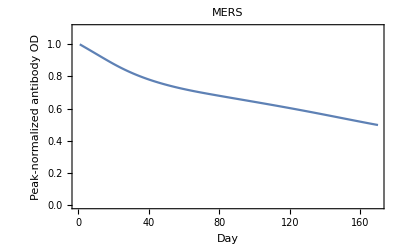

```mathematica
ListLinePlot[mersantibodytimecourse, PlotRange->{0, 1.1}, PlotLabel->"MERS", Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Peak-normalized antibody OD"}]
```

```mathematica
Export["MERS-Antibody-Time-Course.csv", mersantibodytimecourse]
```

MERS-Antibody-Time-Course.csv

### MERS baseline from ancestral and descendent states analysis

```mathematica
mersbaseline=0.1298892
```

0.129889

This estimate of the baseline peak-normalized S IgG antibody level comes from the ancestral and descendent state analysis using the phylogeny and the observational baselines from the “seasonal” coronaviruses to infer the baseline peak-normalized S IgG antibody level for MERS.

### MERS augmented exponential fit of decline to baseline

```mathematica
merslsfuncwfixedbaseline=Sum[(mersantibodytimecourse[[index]]-(mersbaseline+(1-mersbaseline)*Exp[-lambda*index]))^2, {index, 1, Length[mersantibodytimecourse]}]
```

(0.368366-0.870111 ⅇ^(-170 lambda))^2+(0.370388-0.870111 ⅇ^(-169 lambda))^2+(0.372425-0.870111 ⅇ^(-168 lambda))^2+(0.374474-0.870111 ⅇ^(-167 lambda))^2+(0.376536-0.870111 ⅇ^(-166 lambda))^2+(0.37861-0.870111 ⅇ^(-165 lambda))^2+(0.380694-0.870111 ⅇ^(-164 lambda))^2+(0.382789-0.870111 ⅇ^(-163 lambda))^2+(0.384893-0.870111 ⅇ^(-162 lambda))^2+(0.387005-0.870111 ⅇ^(-161 lambda))^2+(0.389125-0.870111 ⅇ^(-160 lambda))^2+(0.391252-0.870111 ⅇ^(-159 lambda))^2+(0.393386-0.870111 ⅇ^(-158 lambda))^2+(0.395524-0.870111 ⅇ^(-157 lambda))^2+(0.397668-0.870111 ⅇ^(-156 lambda))^2+(0.399816-0.870111 ⅇ^(-155 lambda))^2+(0.401967-0.870111 ⅇ^(-154 lambda))^2+(0.40412-0.870111 ⅇ^(-153 lambda))^2+(0.406276-0.870111 ⅇ^(-152 lambda))^2+(0.408433-0.870111 ⅇ^(-151 lambda))^2+(0.410591-0.870111 ⅇ^(-150 lambda))^2+(0.412749-0.870111 ⅇ^(-149 lambda))^2+(0.414907-0.870111 ⅇ^(-148 lambda))^2+(0.417063-0.870111 ⅇ^(-147 lambda))^2+(0.419219-0.870111 ⅇ^(-146 lambda))^2+(0.421372-0.870111 ⅇ^(-145 lambda))^2+(0.423523-0.870111 ⅇ^(-144 lambda))^2+(0.425671-0.870111 ⅇ^(-143 lambda))^2+(0.427815-0.870111 ⅇ^(-142 lambda))^2+(0.429956-0.870111 ⅇ^(-141 lambda))^2+(0.432093-0.870111 ⅇ^(-140 lambda))^2+(0.434225-0.870111 ⅇ^(-139 lambda))^2+(0.436353-0.870111 ⅇ^(-138 lambda))^2+(0.438475-0.870111 ⅇ^(-137 lambda))^2+(0.440592-0.870111 ⅇ^(-136 lambda))^2+(0.442703-0.870111 ⅇ^(-135 lambda))^2+(0.444808-0.870111 ⅇ^(-134 lambda))^2+(0.446907-0.870111 ⅇ^(-133 lambda))^2+(0.448999-0.870111 ⅇ^(-132 lambda))^2+(0.451085-0.870111 ⅇ^(-131 lambda))^2+(0.453165-0.870111 ⅇ^(-130 lambda))^2+(0.455237-0.870111 ⅇ^(-129 lambda))^2+(0.457302-0.870111 ⅇ^(-128 lambda))^2+(0.459361-0.870111 ⅇ^(-127 lambda))^2+(0.461412-0.870111 ⅇ^(-126 lambda))^2+(0.463456-0.870111 ⅇ^(-125 lambda))^2+(0.465493-0.870111 ⅇ^(-124 lambda))^2+(0.467523-0.870111 ⅇ^(-123 lambda))^2+(0.469545-0.870111 ⅇ^(-122 lambda))^2+(0.47156-0.870111 ⅇ^(-121 lambda))^2+(0.473568-0.870111 ⅇ^(-120 lambda))^2+(0.475569-0.870111 ⅇ^(-119 lambda))^2+(0.477563-0.870111 ⅇ^(-118 lambda))^2+(0.47955-0.870111 ⅇ^(-117 lambda))^2+(0.48153-0.870111 ⅇ^(-116 lambda))^2+(0.483503-0.870111 ⅇ^(-115 lambda))^2+(0.48547-0.870111 ⅇ^(-114 lambda))^2+(0.48743-0.870111 ⅇ^(-113 lambda))^2+(0.489384-0.870111 ⅇ^(-112 lambda))^2+(0.491332-0.870111 ⅇ^(-111 lambda))^2+(0.493274-0.870111 ⅇ^(-110 lambda))^2+(0.49521-0.870111 ⅇ^(-109 lambda))^2+(0.497141-0.870111 ⅇ^(-108 lambda))^2+(0.499066-0.870111 ⅇ^(-107 lambda))^2+(0.500987-0.870111 ⅇ^(-106 lambda))^2+(0.502903-0.870111 ⅇ^(-105 lambda))^2+(0.504814-0.870111 ⅇ^(-104 lambda))^2+(0.506721-0.870111 ⅇ^(-103 lambda))^2+(0.508624-0.870111 ⅇ^(-102 lambda))^2+(0.510523-0.870111 ⅇ^(-101 lambda))^2+(0.512419-0.870111 ⅇ^(-100 lambda))^2+(0.514312-0.870111 ⅇ^(-99 lambda))^2+(0.516203-0.870111 ⅇ^(-98 lambda))^2+(0.518091-0.870111 ⅇ^(-97 lambda))^2+(0.519977-0.870111 ⅇ^(-96 lambda))^2+(0.521862-0.870111 ⅇ^(-95 lambda))^2+(0.523746-0.870111 ⅇ^(-94 lambda))^2+(0.525629-0.870111 ⅇ^(-93 lambda))^2+(0.527511-0.870111 ⅇ^(-92 lambda))^2+(0.529394-0.870111 ⅇ^(-91 lambda))^2+(0.531278-0.870111 ⅇ^(-90 lambda))^2+(0.533162-0.870111 ⅇ^(-89 lambda))^2+(0.535048-0.870111 ⅇ^(-88 lambda))^2+(0.536936-0.870111 ⅇ^(-87 lambda))^2+(0.538827-0.870111 ⅇ^(-86 lambda))^2+(0.540721-0.870111 ⅇ^(-85 lambda))^2+(0.542618-0.870111 ⅇ^(-84 lambda))^2+(0.544519-0.870111 ⅇ^(-83 lambda))^2+(0.546426-0.870111 ⅇ^(-82 lambda))^2+(0.548338-0.870111 ⅇ^(-81 lambda))^2+(0.550255-0.870111 ⅇ^(-80 lambda))^2+(0.55218-0.870111 ⅇ^(-79 lambda))^2+(0.554112-0.870111 ⅇ^(-78 lambda))^2+(0.556052-0.870111 ⅇ^(-77 lambda))^2+(0.558001-0.870111 ⅇ^(-76 lambda))^2+(0.559959-0.870111 ⅇ^(-75 lambda))^2+(0.561928-0.870111 ⅇ^(-74 lambda))^2+(0.563908-0.870111 ⅇ^(-73 lambda))^2+(0.5659-0.870111 ⅇ^(-72 lambda))^2+(0.567905-0.870111 ⅇ^(-71 lambda))^2+(0.569924-0.870111 ⅇ^(-70 lambda))^2+(0.571971-0.870111 ⅇ^(-69 lambda))^2+(0.57405-0.870111 ⅇ^(-68 lambda))^2+(0.576161-0.870111 ⅇ^(-67 lambda))^2+(0.578305-0.870111 ⅇ^(-66 lambda))^2+(0.580485-0.870111 ⅇ^(-65 lambda))^2+(0.582702-0.870111 ⅇ^(-64 lambda))^2+(0.584958-0.870111 ⅇ^(-63 lambda))^2+(0.587253-0.870111 ⅇ^(-62 lambda))^2+(0.58959-0.870111 ⅇ^(-61 lambda))^2+(0.591971-0.870111 ⅇ^(-60 lambda))^2+(0.594397-0.870111 ⅇ^(-59 lambda))^2+(0.59687-0.870111 ⅇ^(-58 lambda))^2+(0.599393-0.870111 ⅇ^(-57 lambda))^2+(0.601966-0.870111 ⅇ^(-56 lambda))^2+(0.604593-0.870111 ⅇ^(-55 lambda))^2+(0.607275-0.870111 ⅇ^(-54 lambda))^2+(0.610015-0.870111 ⅇ^(-53 lambda))^2+(0.612814-0.870111 ⅇ^(-52 lambda))^2+(0.615676-0.870111 ⅇ^(-51 lambda))^2+(0.618602-0.870111 ⅇ^(-50 lambda))^2+(0.621595-0.870111 ⅇ^(-49 lambda))^2+(0.624657-0.870111 ⅇ^(-48 lambda))^2+(0.627791-0.870111 ⅇ^(-47 lambda))^2+(0.631-0.870111 ⅇ^(-46 lambda))^2+(0.634286-0.870111 ⅇ^(-45 lambda))^2+(0.637653-0.870111 ⅇ^(-44 lambda))^2+(0.641102-0.870111 ⅇ^(-43 lambda))^2+(0.644637-0.870111 ⅇ^(-42 lambda))^2+(0.64826-0.870111 ⅇ^(-41 lambda))^2+(0.651975-0.870111 ⅇ^(-40 lambda))^2+(0.655785-0.870111 ⅇ^(-39 lambda))^2+(0.659691-0.870111 ⅇ^(-38 lambda))^2+(0.663698-0.870111 ⅇ^(-37 lambda))^2+(0.667807-0.870111 ⅇ^(-36 lambda))^2+(0.672022-0.870111 ⅇ^(-35 lambda))^2+(0.676345-0.870111 ⅇ^(-34 lambda))^2+(0.680779-0.870111 ⅇ^(-33 lambda))^2+(0.685325-0.870111 ⅇ^(-32 lambda))^2+(0.689987-0.870111 ⅇ^(-31 lambda))^2+(0.694767-0.870111 ⅇ^(-30 lambda))^2+(0.699664-0.870111 ⅇ^(-29 lambda))^2+(0.704683-0.870111 ⅇ^(-28 lambda))^2+(0.709822-0.870111 ⅇ^(-27 lambda))^2+(0.715082-0.870111 ⅇ^(-26 lambda))^2+(0.720465-0.870111 ⅇ^(-25 lambda))^2+(0.725968-0.870111 ⅇ^(-24 lambda))^2+(0.731592-0.870111 ⅇ^(-23 lambda))^2+(0.737334-0.870111 ⅇ^(-22 lambda))^2+(0.743192-0.870111 ⅇ^(-21 lambda))^2+(0.749162-0.870111 ⅇ^(-20 lambda))^2+(0.75524-0.870111 ⅇ^(-19 lambda))^2+(0.761421-0.870111 ⅇ^(-18 lambda))^2+(0.7677-0.870111 ⅇ^(-17 lambda))^2+(0.77404-0.870111 ⅇ^(-16 lambda))^2+(0.780416-0.870111 ⅇ^(-15 lambda))^2+(0.786821-0.870111 ⅇ^(-14 lambda))^2+(0.793247-0.870111 ⅇ^(-13 lambda))^2+(0.799688-0.870111 ⅇ^(-12 lambda))^2+(0.806137-0.870111 ⅇ^(-11 lambda))^2+(0.812588-0.870111 ⅇ^(-10 lambda))^2+(0.819037-0.870111 ⅇ^(-9 lambda))^2+(0.825479-0.870111 ⅇ^(-8 lambda))^2+(0.831909-0.870111 ⅇ^(-7 lambda))^2+(0.838325-0.870111 ⅇ^(-6 lambda))^2+(0.844724-0.870111 ⅇ^(-5 lambda))^2+(0.851103-0.870111 ⅇ^(-4 lambda))^2+(0.857461-0.870111 ⅇ^(-3 lambda))^2+(0.863797-0.870111 ⅇ^(-2 lambda))^2+(0.870111-0.870111 ⅇ^-lambda)^2

```mathematica
FindMinimum[{merslsfuncwfixedbaseline, lambda >0}, {lambda, 0.002}]
```

{0.128746,{lambda→0.00539825}}

This value of lambda goes into the ancestral and descendent states analysis estimating a and b for the zoonotic coronaviruses.

```mathematica
mershalflife=Log[2]/ lambda /.lambda->0.005398253035305271
```

128.402

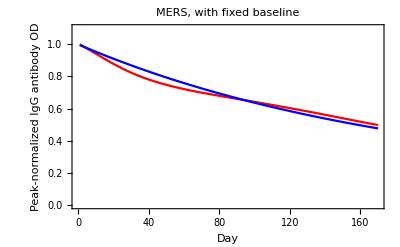

```mathematica
Show[
ListLinePlot[mersantibodytimecourse,
PlotStyle->Red,
PlotRange->{0,1.1}
],
Plot[mersbaseline+(1-mersbaseline)*Exp[-lambda days]/.lambda->0.005398253035305271,{days,1,Length[mersantibodytimecourse]},
PlotStyle->Blue, 
PlotRange->{0,1.1}
], 
PlotLabel->"MERS, with fixed baseline", 
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Peak-normalized IgG antibody OD"}]
```

```mathematica
mersantibodytimecourse
```

{1,0.993686,0.98735,0.980992,0.974613,0.968214,0.961798,0.955368,0.948926,0.942478,0.936026,0.929577,0.923137,0.91671,0.910306,0.903929,0.897589,0.89131,0.885129,0.879051,0.873081,0.867223,0.861481,0.855858,0.850354,0.844972,0.839711,0.834572,0.829554,0.824656,0.819877,0.815215,0.810668,0.806234,0.801911,0.797696,0.793587,0.78958,0.785674,0.781865,0.77815,0.774526,0.770991,0.767542,0.764175,0.760889,0.75768,0.754546,0.751484,0.748491,0.745565,0.742704,0.739904,0.737165,0.734482,0.731856,0.729282,0.72676,0.724286,0.72186,0.719479,0.717142,0.714847,0.712591,0.710375,0.708195,0.70605,0.703939,0.701861,0.699813,0.697794,0.695789,0.693797,0.691817,0.689848,0.68789,0.685941,0.684001,0.682069,0.680145,0.678227,0.676315,0.674409,0.672507,0.67061,0.668716,0.666825,0.664937,0.663051,0.661167,0.659283,0.657401,0.655518,0.653635,0.651751,0.649867,0.64798,0.646092,0.644201,0.642308,0.640412,0.638513,0.63661,0.634703,0.632792,0.630876,0.628956,0.62703,0.625099,0.623163,0.621221,0.619273,0.617319,0.615359,0.613392,0.611419,0.609439,0.607452,0.605458,0.603457,0.601449,0.599434,0.597412,0.595382,0.593345,0.591301,0.58925,0.587192,0.585126,0.583054,0.580974,0.578888,0.576796,0.574697,0.572592,0.570481,0.568364,0.566242,0.564114,0.561982,0.559846,0.557705,0.55556,0.553412,0.551261,0.549108,0.546953,0.544796,0.542638,0.54048,0.538322,0.536165,0.534009,0.531856,0.529705,0.527557,0.525414,0.523275,0.521142,0.519015,0.516894,0.514782,0.512678,0.510584,0.508499,0.506426,0.504364,0.502314,0.500278,0.498255}

```mathematica
Length[mersantibodytimecourse]
```

170

```mathematica
mersantibodytimecourseplusexp=mersantibodytimecourse;
day=Length[mersantibodytimecourse];
While[day<4393,
Increment[day];
AppendTo[mersantibodytimecourseplusexp, mersbaseline+(mersantibodytimecourseplusexp[[day-1]]- mersbaseline)*Exp[-0.005398253035305271]]
]
```

```mathematica
mersantibodytimecourseplusexp
```

{1,0.993686,0.98735,0.980992,0.974613,0.968214,0.961798,0.955368,0.948926,0.942478,0.936026,0.929577,0.923137,0.91671,0.910306,0.903929,0.897589,0.89131,0.885129,0.879051,0.873081,0.867223,0.861481,0.855858,0.850354,0.844972,0.839711,0.834572,0.829554,0.824656,0.819877,0.815215,0.810668,0.806234,0.801911,0.797696,0.793587,0.78958,0.785674,0.781865,0.77815,0.774526,0.770991,0.767542,0.764175,0.760889,0.75768,0.754546,0.751484,0.748491,0.745565,0.742704,0.739904,0.737165,0.734482,0.731856,0.729282,0.72676,0.724286,0.72186,0.719479,0.717142,0.714847,0.712591,0.710375,0.708195,0.70605,0.703939,0.701861,0.699813,0.697794,0.695789,0.693797,0.691817,0.689848,0.68789,0.685941,0.684001,0.682069,0.680145,0.678227,0.676315,0.674409,0.672507,0.67061,0.668716,0.666825,0.664937,0.663051,0.661167,0.659283,0.657401,0.655518,0.653635,0.651751,0.649867,0.64798,0.646092,0.644201,0.642308,0.640412,0.638513,0.63661,0.634703,0.632792,0.630876,0.628956,0.62703,0.625099,0.623163,0.621221,0.619273,0.617319,0.615359,0.613392,0.611419,0.609439,0.607452,0.605458,0.603457,0.601449,0.599434,0.597412,0.595382,0.593345,0.591301,0.58925,0.587192,0.585126,0.583054,0.580974,0.578888,0.576796,0.574697,0.572592,0.570481,0.568364,0.566242,0.564114,0.561982,0.559846,0.557705,0.55556,0.553412,0.551261,0.549108,0.546953,0.544796,0.542638,0.54048,0.538322,0.536165,0.534009,0.531856,0.529705,0.527557,0.525414,0.523275,0.521142,0.519015,0.516894,0.514782,0.512678,0.510584,0.508499,0.506426,0.504364,0.502314,0.500278,0.498255,0.496272,0.4943,0.492338,0.490386,0.488446,0.486515,0.484595,0.482686,0.480786,0.478897,0.477018,0.475149,0.473291,0.471442,0.469603,0.467774,0.465955,0.464146,0.462346,0.460556,0.458776,0.457005,0.455244,0.453493,0.451751,0.450018,0.448294,0.44658,0.444875,0.443179,0.441493,0.439815,0.438146,0.436487,0.434836,0.433195,0.431562,0.429937,0.428322,0.426715,0.425117,0.423528,0.421947,0.420375,0.418811,0.417255,0.415708,0.41417,0.412639,0.411117,0.409603,0.408097,0.406599,0.405109,0.403628,0.402154,0.400688,0.39923,0.39778,0.396338,0.394903,0.393477,0.392058,0.390646,0.389242,0.387846,0.386457,0.385076,0.383702,0.382336,0.380977,0.379625,0.37828,0.376943,0.375613,0.37429,0.372974,0.371666,0.370364,0.369069,0.367782,0.366501,0.365227,0.36396,0.3627,0.361446,0.3602,0.35896,0.357727,0.3565,0.35528,0.354067,0.35286,0.351659,0.350465,0.349278,0.348097,0.346922,0.345754,0.344591,0.343435,0.342286,0.341142,0.340005,0.338874,0.337749,0.33663,0.335517,0.33441,0.333308,0.332213,0.331124,0.330041,0.328963,0.327891,0.326825,0.325765,0.324711,0.323662,0.322619,0.321581,0.320549,0.319522,0.318502,0.317486,0.316476,0.315472,0.314472,0.313479,0.31249,0.311507,0.310529,0.309557,0.30859,0.307628,0.306671,0.305719,0.304772,0.303831,0.302894,0.301963,0.301037,0.300115,0.299199,0.298287,0.297381,0.296479,0.295582,0.29469,0.293803,0.29292,0.292043,0.29117,0.290301,0.289438,0.288579,0.287724,0.286875,0.286029,0.285189,0.284353,0.283521,0.282694,0.281871,0.281053,0.280239,0.27943,0.278625,0.277824,0.277028,0.276236,0.275448,0.274664,0.273885,0.273109,0.272338,0.271571,0.270809,0.27005,0.269295,0.268545,0.267798,0.267056,0.266317,0.265583,0.264852,0.264126,0.263403,0.262684,0.261969,0.261258,0.260551,0.259848,0.259148,0.258452,0.25776,0.257071,0.256387,0.255706,0.255028,0.254355,0.253685,0.253018,0.252355,0.251696,0.25104,0.250388,0.249739,0.249094,0.248452,0.247814,0.247179,0.246548,0.245919,0.245295,0.244673,0.244055,0.243441,0.24283,0.242221,0.241617,0.241015,0.240417,0.239822,0.23923,0.238641,0.238056,0.237474,0.236894,0.236318,0.235745,0.235175,0.234609,0.234045,0.233484,0.232926,0.232372,0.23182,0.231271,0.230725,0.230182,0.229642,0.229105,0.228571,0.22804,0.227512,0.226986,0.226463,0.225943,0.225426,0.224912,0.2244,0.223891,0.223385,0.222882,0.222381,0.221883,0.221388,0.220896,0.220406,0.219918,0.219434,0.218952,0.218472,0.217995,0.217521,0.217049,0.21658,0.216113,0.215649,0.215187,0.214728,0.214271,0.213817,0.213365,0.212916,0.212469,0.212024,0.211582,0.211142,0.210705,0.21027,0.209837,0.209406,0.208978,0.208552,0.208129,0.207708,0.207289,0.206872,0.206458,0.206045,0.205635,0.205228,0.204822,0.204419,0.204017,0.203618,0.203221,0.202827,0.202434,0.202043,0.201655,0.201269,0.200884,0.200502,0.200122,0.199744,0.199368,0.198994,0.198622,0.198252,0.197883,0.197517,0.197153,0.196791,0.196431,0.196073,0.195716,0.195362,0.19501,0.194659,0.19431,0.193963,0.193619,0.193275,0.192934,0.192595,0.192257,0.191921,0.191587,0.191255,0.190925,0.190596,0.190269,0.189944,0.189621,0.189299,0.18898,0.188662,0.188345,0.18803,0.187717,0.187406,0.187096,0.186788,0.186482,0.186177,0.185874,0.185573,0.185273,0.184975,0.184678,0.184383,0.18409,0.183798,0.183508,0.183219,0.182932,0.182647,0.182363,0.18208,0.181799,0.18152,0.181242,0.180965,0.18069,0.180417,0.180145,0.179874,0.179605,0.179337,0.179071,0.178806,0.178543,0.178281,0.178021,0.177762,0.177504,0.177247,0.176992,0.176739,0.176487,0.176236,0.175986,0.175738,0.175491,0.175246,0.175002,0.174759,0.174517,0.174277,0.174038,0.1738,0.173564,0.173329,0.173095,0.172862,0.172631,0.172401,0.172172,0.171944,0.171718,0.171493,0.171269,0.171046,0.170824,0.170604,0.170385,0.170167,0.16995,0.169734,0.16952,0.169306,0.169094,0.168883,0.168673,0.168464,0.168257,0.16805,0.167845,0.16764,0.167437,0.167235,0.167034,0.166834,0.166635,0.166437,0.16624,0.166045,0.16585,0.165656,0.165464,0.165272,0.165082,0.164892,0.164704,0.164516,0.16433,0.164145,0.16396,0.163777,0.163594,0.163413,0.163232,0.163053,0.162874,0.162697,0.16252,0.162344,0.16217,0.161996,0.161823,0.161651,0.16148,0.16131,0.161141,0.160973,0.160805,0.160639,0.160473,0.160309,0.160145,0.159982,0.15982,0.159659,0.159499,0.159339,0.159181,0.159023,0.158866,0.15871,0.158555,0.158401,0.158247,0.158094,0.157943,0.157792,0.157641,0.157492,0.157343,0.157196,0.157049,0.156902,0.156757,0.156612,0.156468,0.156325,0.156183,0.156041,0.155901,0.155761,0.155621,0.155483,0.155345,0.155208,0.155072,0.154936,0.154801,0.154667,0.154534,0.154401,0.154269,0.154138,0.154007,0.153877,0.153748,0.15362,0.153492,0.153365,0.153239,0.153113,0.152988,0.152863,0.15274,0.152617,0.152494,0.152373,0.152252,0.152131,0.152012,0.151892,0.151774,0.151656,0.151539,0.151422,0.151306,0.151191,0.151076,0.150962,0.150849,0.150736,0.150624,0.150512,0.150401,0.150291,0.150181,0.150072,0.149963,0.149855,0.149748,0.149641,0.149534,0.149428,0.149323,0.149219,0.149115,0.149011,0.148908,0.148806,0.148704,0.148603,0.148502,0.148402,0.148302,0.148203,0.148104,0.148006,0.147909,0.147812,0.147715,0.147619,0.147524,0.147429,0.147334,0.14724,0.147147,0.147054,0.146962,0.14687,0.146778,0.146687,0.146597,0.146507,0.146418,0.146329,0.14624,0.146152,0.146065,0.145977,0.145891,0.145805,0.145719,0.145634,0.145549,0.145465,0.145381,0.145297,0.145215,0.145132,0.14505,0.144968,0.144887,0.144806,0.144726,0.144646,0.144567,0.144488,0.144409,0.144331,0.144253,0.144176,0.144099,0.144022,0.143946,0.143871,0.143795,0.143721,0.143646,0.143572,0.143498,0.143425,0.143352,0.14328,0.143208,0.143136,0.143065,0.142994,0.142923,0.142853,0.142783,0.142714,0.142645,0.142576,0.142508,0.14244,0.142372,0.142305,0.142238,0.142172,0.142106,0.14204,0.141974,0.141909,0.141845,0.14178,0.141716,0.141653,0.141589,0.141526,0.141464,0.141401,0.141339,0.141278,0.141216,0.141155,0.141095,0.141034,0.140974,0.140915,0.140855,0.140796,0.140738,0.140679,0.140621,0.140563,0.140506,0.140449,0.140392,0.140335,0.140279,0.140223,0.140168,0.140112,0.140057,0.140002,0.139948,0.139894,0.13984,0.139786,0.139733,0.13968,0.139627,0.139575,0.139523,0.139471,0.139419,0.139368,0.139317,0.139266,0.139216,0.139166,0.139116,0.139066,0.139017,0.138967,0.138919,0.13887,0.138822,0.138773,0.138726,0.138678,0.138631,0.138584,0.138537,0.13849,0.138444,0.138398,0.138352,0.138307,0.138261,0.138216,0.138171,0.138127,0.138082,0.138038,0.137994,0.137951,0.137907,0.137864,0.137821,0.137779,0.137736,0.137694,0.137652,0.13761,0.137569,0.137527,0.137486,0.137445,0.137404,0.137364,0.137324,0.137284,0.137244,0.137204,0.137165,0.137126,0.137087,0.137048,0.13701,0.136971,0.136933,0.136895,0.136857,0.13682,0.136783,0.136745,0.136709,0.136672,0.136635,0.136599,0.136563,0.136527,0.136491,0.136456,0.13642,0.136385,0.13635,0.136315,0.136281,0.136246,0.136212,0.136178,0.136144,0.136111,0.136077,0.136044,0.136011,0.135978,0.135945,0.135912,0.13588,0.135848,0.135816,0.135784,0.135752,0.13572,0.135689,0.135658,0.135627,0.135596,0.135565,0.135535,0.135504,0.135474,0.135444,0.135414,0.135384,0.135355,0.135325,0.135296,0.135267,0.135238,0.135209,0.13518,0.135152,0.135124,0.135095,0.135067,0.13504,0.135012,0.134984,0.134957,0.13493,0.134902,0.134875,0.134849,0.134822,0.134795,0.134769,0.134743,0.134716,0.13469,0.134665,0.134639,0.134613,0.134588,0.134563,0.134537,0.134512,0.134488,0.134463,0.134438,0.134414,0.134389,0.134365,0.134341,0.134317,0.134293,0.134269,0.134246,0.134222,0.134199,0.134176,0.134153,0.13413,0.134107,0.134084,0.134062,0.134039,0.134017,0.133995,0.133973,0.133951,0.133929,0.133907,0.133885,0.133864,0.133842,0.133821,0.1338,0.133779,0.133758,0.133737,0.133716,0.133696,0.133675,0.133655,0.133635,0.133615,0.133595,0.133575,0.133555,0.133535,0.133515,0.133496,0.133476,0.133457,0.133438,0.133419,0.1334,0.133381,0.133362,0.133343,0.133325,0.133306,0.133288,0.13327,0.133251,0.133233,0.133215,0.133197,0.13318,0.133162,0.133144,0.133127,0.133109,0.133092,0.133075,0.133058,0.133041,0.133024,0.133007,0.13299,0.132973,0.132957,0.13294,0.132924,0.132907,0.132891,0.132875,0.132859,0.132843,0.132827,0.132811,0.132795,0.13278,0.132764,0.132749,0.132733,0.132718,0.132703,0.132688,0.132673,0.132658,0.132643,0.132628,0.132613,0.132598,0.132584,0.132569,0.132555,0.132541,0.132526,0.132512,0.132498,0.132484,0.13247,0.132456,0.132442,0.132428,0.132415,0.132401,0.132388,0.132374,0.132361,0.132348,0.132334,0.132321,0.132308,0.132295,0.132282,0.132269,0.132256,0.132244,0.132231,0.132218,0.132206,0.132193,0.132181,0.132169,0.132156,0.132144,0.132132,0.13212,0.132108,0.132096,0.132084,0.132072,0.132061,0.132049,0.132037,0.132026,0.132014,0.132003,0.131991,0.13198,0.131969,0.131958,0.131946,0.131935,0.131924,0.131913,0.131902,0.131892,0.131881,0.13187,0.131859,0.131849,0.131838,0.131828,0.131817,0.131807,0.131797,0.131786,0.131776,0.131766,0.131756,0.131746,0.131736,0.131726,0.131716,0.131706,0.131696,0.131687,0.131677,0.131667,0.131658,0.131648,0.131639,0.131629,0.13162,0.131611,0.131601,0.131592,0.131583,0.131574,0.131565,0.131556,0.131547,0.131538,0.131529,0.13152,0.131511,0.131503,0.131494,0.131485,0.131477,0.131468,0.13146,0.131451,0.131443,0.131435,0.131426,0.131418,0.13141,0.131402,0.131393,0.131385,0.131377,0.131369,0.131361,0.131353,0.131345,0.131338,0.13133,0.131322,0.131314,0.131307,0.131299,0.131291,0.131284,0.131276,0.131269,0.131261,0.131254,0.131247,0.131239,0.131232,0.131225,0.131218,0.131211,0.131203,0.131196,0.131189,0.131182,0.131175,0.131168,0.131162,0.131155,0.131148,0.131141,0.131134,0.131128,0.131121,0.131114,0.131108,0.131101,0.131095,0.131088,0.131082,0.131075,0.131069,0.131063,0.131056,0.13105,0.131044,0.131038,0.131031,0.131025,0.131019,0.131013,0.131007,0.131001,0.130995,0.130989,0.130983,0.130977,0.130971,0.130966,0.13096,0.130954,0.130948,0.130943,0.130937,0.130931,0.130926,0.13092,0.130914,0.130909,0.130903,0.130898,0.130893,0.130887,0.130882,0.130876,0.130871,0.130866,0.130861,0.130855,0.13085,0.130845,0.13084,0.130835,0.13083,0.130825,0.13082,0.130815,0.13081,0.130805,0.1308,0.130795,0.13079,0.130785,0.13078,0.130775,0.130771,0.130766,0.130761,0.130757,0.130752,0.130747,0.130743,0.130738,0.130733,0.130729,0.130724,0.13072,0.130715,0.130711,0.130707,0.130702,0.130698,0.130693,0.130689,0.130685,0.13068,0.130676,0.130672,0.130668,0.130664,0.130659,0.130655,0.130651,0.130647,0.130643,0.130639,0.130635,0.130631,0.130627,0.130623,0.130619,0.130615,0.130611,0.130607,0.130603,0.130599,0.130596,0.130592,0.130588,0.130584,0.130581,0.130577,0.130573,0.130569,0.130566,0.130562,0.130559,0.130555,0.130551,0.130548,0.130544,0.130541,0.130537,0.130534,0.13053,0.130527,0.130523,0.13052,0.130517,0.130513,0.13051,0.130506,0.130503,0.1305,0.130497,0.130493,0.13049,0.130487,0.130484,0.13048,0.130477,0.130474,0.130471,0.130468,0.130465,0.130462,0.130458,0.130455,0.130452,0.130449,0.130446,0.130443,0.13044,0.130437,0.130434,0.130431,0.130429,0.130426,0.130423,0.13042,0.130417,0.130414,0.130411,0.130409,0.130406,0.130403,0.1304,0.130397,0.130395,0.130392,0.130389,0.130387,0.130384,0.130381,0.130379,0.130376,0.130373,0.130371,0.130368,0.130366,0.130363,0.13036,0.130358,0.130355,0.130353,0.13035,0.130348,0.130345,0.130343,0.130341,0.130338,0.130336,0.130333,0.130331,0.130329,0.130326,0.130324,0.130321,0.130319,0.130317,0.130315,0.130312,0.13031,0.130308,0.130305,0.130303,0.130301,0.130299,0.130297,0.130294,0.130292,0.13029,0.130288,0.130286,0.130284,0.130281,0.130279,0.130277,0.130275,0.130273,0.130271,0.130269,0.130267,0.130265,0.130263,0.130261,0.130259,0.130257,0.130255,0.130253,0.130251,0.130249,0.130247,0.130245,0.130243,0.130241,0.130239,0.130238,0.130236,0.130234,0.130232,0.13023,0.130228,0.130226,0.130225,0.130223,0.130221,0.130219,0.130217,0.130216,0.130214,0.130212,0.13021,0.130209,0.130207,0.130205,0.130204,0.130202,0.1302,0.130199,0.130197,0.130195,0.130194,0.130192,0.13019,0.130189,0.130187,0.130185,0.130184,0.130182,0.130181,0.130179,0.130178,0.130176,0.130174,0.130173,0.130171,0.13017,0.130168,0.130167,0.130165,0.130164,0.130162,0.130161,0.130159,0.130158,0.130157,0.130155,0.130154,0.130152,0.130151,0.130149,0.130148,0.130147,0.130145,0.130144,0.130143,0.130141,0.13014,0.130138,0.130137,0.130136,0.130134,0.130133,0.130132,0.13013,0.130129,0.130128,0.130127,0.130125,0.130124,0.130123,0.130122,0.13012,0.130119,0.130118,0.130117,0.130115,0.130114,0.130113,0.130112,0.130111,0.130109,0.130108,0.130107,0.130106,0.130105,0.130103,0.130102,0.130101,0.1301,0.130099,0.130098,0.130097,0.130096,0.130094,0.130093,0.130092,0.130091,0.13009,0.130089,0.130088,0.130087,0.130086,0.130085,0.130084,0.130083,0.130082,0.130081,0.130079,0.130078,0.130077,0.130076,0.130075,0.130074,0.130073,0.130072,0.130071,0.13007,0.130069,0.130069,0.130068,0.130067,0.130066,0.130065,0.130064,0.130063,0.130062,0.130061,0.13006,0.130059,0.130058,0.130057,0.130056,0.130055,0.130055,0.130054,0.130053,0.130052,0.130051,0.13005,0.130049,0.130048,0.130048,0.130047,0.130046,0.130045,0.130044,0.130043,0.130043,0.130042,0.130041,0.13004,0.130039,0.130038,0.130038,0.130037,0.130036,0.130035,0.130034,0.130034,0.130033,0.130032,0.130031,0.130031,0.13003,0.130029,0.130028,0.130028,0.130027,0.130026,0.130025,0.130025,0.130024,0.130023,0.130022,0.130022,0.130021,0.13002,0.13002,0.130019,0.130018,0.130018,0.130017,0.130016,0.130015,0.130015,0.130014,0.130013,0.130013,0.130012,0.130011,0.130011,0.13001,0.130009,0.130009,0.130008,0.130008,0.130007,0.130006,0.130006,0.130005,0.130004,0.130004,0.130003,0.130003,0.130002,0.130001,0.130001,0.13,0.13,0.129999,0.129998,0.129998,0.129997,0.129997,0.129996,0.129995,0.129995,0.129994,0.129994,0.129993,0.129993,0.129992,0.129991,0.129991,0.12999,0.12999,0.129989,0.129989,0.129988,0.129988,0.129987,0.129987,0.129986,0.129986,0.129985,0.129985,0.129984,0.129984,0.129983,0.129983,0.129982,0.129982,0.129981,0.129981,0.12998,0.12998,0.129979,0.129979,0.129978,0.129978,0.129977,0.129977,0.129976,0.129976,0.129975,0.129975,0.129974,0.129974,0.129973,0.129973,0.129973,0.129972,0.129972,0.129971,0.129971,0.12997,0.12997,0.129969,0.129969,0.129969,0.129968,0.129968,0.129967,0.129967,0.129966,0.129966,0.129966,0.129965,0.129965,0.129964,0.129964,0.129964,0.129963,0.129963,0.129962,0.129962,0.129962,0.129961,0.129961,0.12996,0.12996,0.12996,0.129959,0.129959,0.129959,0.129958,0.129958,0.129957,0.129957,0.129957,0.129956,0.129956,0.129956,0.129955,0.129955,0.129955,0.129954,0.129954,0.129953,0.129953,0.129953,0.129952,0.129952,0.129952,0.129951,0.129951,0.129951,0.12995,0.12995,0.12995,0.129949,0.129949,0.129949,0.129948,0.129948,0.129948,0.129948,0.129947,0.129947,0.129947,0.129946,0.129946,0.129946,0.129945,0.129945,0.129945,0.129944,0.129944,0.129944,0.129944,0.129943,0.129943,0.129943,0.129942,0.129942,0.129942,0.129942,0.129941,0.129941,0.129941,0.12994,0.12994,0.12994,0.12994,0.129939,0.129939,0.129939,0.129939,0.129938,0.129938,0.129938,0.129937,0.129937,0.129937,0.129937,0.129936,0.129936,0.129936,0.129936,0.129935,0.129935,0.129935,0.129935,0.129934,0.129934,0.129934,0.129934,0.129933,0.129933,0.129933,0.129933,0.129933,0.129932,0.129932,0.129932,0.129932,0.129931,0.129931,0.129931,0.129931,0.12993,0.12993,0.12993,0.12993,0.12993,0.129929,0.129929,0.129929,0.129929,0.129929,0.129928,0.129928,0.129928,0.129928,0.129927,0.129927,0.129927,0.129927,0.129927,0.129926,0.129926,0.129926,0.129926,0.129926,0.129925,0.129925,0.129925,0.129925,0.129925,0.129925,0.129924,0.129924,0.129924,0.129924,0.129924,0.129923,0.129923,0.129923,0.129923,0.129923,0.129922,0.129922,0.129922,0.129922,0.129922,0.129922,0.129921,0.129921,0.129921,0.129921,0.129921,0.129921,0.12992,0.12992,0.12992,0.12992,0.12992,0.12992,0.129919,0.129919,0.129919,0.129919,0.129919,0.129919,0.129918,0.129918,0.129918,0.129918,0.129918,0.129918,0.129918,0.129917,0.129917,0.129917,0.129917,0.129917,0.129917,0.129916,0.129916,0.129916,0.129916,0.129916,0.129916,0.129916,0.129915,0.129915,0.129915,0.129915,0.129915,0.129915,0.129915,0.129914,0.129914,0.129914,0.129914,0.129914,0.129914,0.129914,0.129914,0.129913,0.129913,0.129913,0.129913,0.129913,0.129913,0.129913,0.129913,0.129912,0.129912,0.129912,0.129912,0.129912,0.129912,0.129912,0.129912,0.129911,0.129911,0.129911,0.129911,0.129911,0.129911,0.129911,0.129911,0.12991,0.12991,0.12991,0.12991,0.12991,0.12991,0.12991,0.12991,0.12991,0.129909,0.129909,0.129909,0.129909,0.129909,0.129909,0.129909,0.129909,0.129909,0.129908,0.129908,0.129908,0.129908,0.129908,0.129908,0.129908,0.129908,0.129908,0.129908,0.129907,0.129907,0.129907,0.129907,0.129907,0.129907,0.129907,0.129907,0.129907,0.129907,0.129907,0.129906,0.129906,0.129906,0.129906,0.129906,0.129906,0.129906,0.129906,0.129906,0.129906,0.129906,0.129905,0.129905,0.129905,0.129905,0.129905,0.129905,0.129905,0.129905,0.129905,0.129905,0.129905,0.129904,0.129904,0.129904,0.129904,0.129904,0.129904,0.129904,0.129904,0.129904,0.129904,0.129904,0.129904,0.129904,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889}

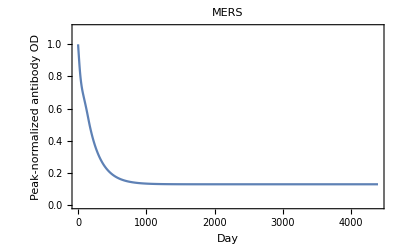

```mathematica
ListLinePlot[mersantibodytimecourseplusexp,
PlotRange->{0, 1.1},
PlotLabel->"MERS",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["MERS_nOD-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[mersantibodytimecourseplusexp,
PlotRange->{0, 1.1},
PlotLabel->"MERS",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
]
```

MERS_nOD-by-Day_21Jan2021.pdf

### MERS Probability of Infection | Antibody OD

```mathematica
mersprobinfgivenaod[aod_]:=1/(1+Exp[-(-4.691845+-12.70282*aod)])
```

These values for a and b come from the ancestral and descendent states analysis to determine them for the zoonotic coronaviruses given baselines and declines for all viruses, and a’s and b’s for the “seasonal” coronaviruses.

```mathematica
mersprobinfgivenaod[aod]
```

1/(1+ⅇ^(4.69185+12.7028 aod))

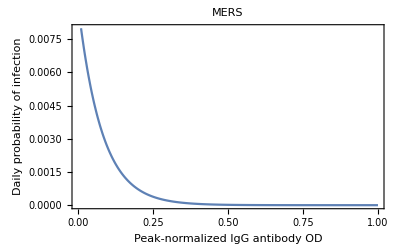

```mathematica
Plot[mersprobinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.008},
PlotLabel->"MERS",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["MERS_PrInf-by-nOD_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Plot[mersprobinfgivenaod[x],{x,0,1},
PlotRange->{0,0.01},
PlotLabel->"MERS",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
]
```

MERS_PrInf-by-nOD_21Jan2021.pdf

```mathematica
mersprobinfgivenall[a_, b_, aod_]:=1/(1+Exp[-(a+b*aod)])
```

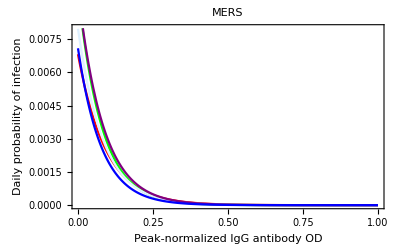

```mathematica
Plot[
{ mersprobinfgivenall[-4.980299, -10.81803, x],
mersprobinfgivenall[-4.630122, -12.68926, x], 
mersprobinfgivenall[-4.823309,-11.950803, x],
mersprobinfgivenall[-4.626306,-11.950803, x],
mersprobinfgivenall[-4.941497, -12.758791, x]},
{x,0,1},
PlotStyle->{Red, Green, LightBlue, Purple, Blue},
PlotRange->{0,0.008},
PlotLabel->"MERS",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
```

The alternate values for a and b above come from our results using different approaches toward building the molecular evolutionary tree of the coronaviruses and toward building the time tree of the coronaviruses (see Supplement).

-Graphics-

This panel goes into a Supplementary Figure.

```mathematica
Export[
StringJoin["MERS_PrInfs-by-nOD_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Plot[
{ mersprobinfgivenall[-4.980299, -10.81803, x],
mersprobinfgivenall[-4.630122, -12.68926, x], 
mersprobinfgivenall[-4.823309,-11.950803, x],
mersprobinfgivenall[-4.626306,-11.950803, x],
mersprobinfgivenall[-4.941497, -12.758791, x]},
{x,0,1},
PlotStyle->{Red, Green, LightBlue, Purple, Blue},
PlotRange->{0,0.008},
PlotLabel->"MERS",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
]
```

MERS_PrInfs-by-nOD_21Jan2021.pdf

### MERS Probability of No Reinfection Time Course

```mathematica
mersprobnoreinfectiontimecourse={1};
day=1;
AppendTo[mersprobnoreinfectiontimecourse, 
mersprobnoreinfectiontimecourse[[day]]*(1-mersprobinfgivenaod[mersantibodytimecourseplusexp[[day+1]]])
];

While[day<4393,
Increment[day];
AppendTo[mersprobnoreinfectiontimecourse, 
If[day<Length[mersantibodytimecourse],
mersprobnoreinfectiontimecourse[[day]]*(1-mersprobinfgivenaod[mersantibodytimecourseplusexp[[day+1]] ]),
mersprobnoreinfectiontimecourse[[day]]*(1-mersprobinfgivenaod[mersantibodytimecourseplusexp[[lengthabtc]]])
]
]
];

mersprobnoreinfectiontimecourse
```

{1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998,0.999998,0.999998,0.999997,0.999997,0.999997,0.999997,0.999996,0.999996,0.999996,0.999996,0.999995,0.999995,0.999994,0.999994,0.999994,0.999993,0.999993,0.999992,0.999992,0.999991,0.999991,0.99999,0.999989,0.999989,0.999988,0.999987,0.999987,0.999986,0.999985,0.999984,0.999984,0.999983,0.999982,0.999981,0.99998,0.999979,0.999978,0.999977,0.999976,0.999975,0.999974,0.999973,0.999972,0.99997,0.999969,0.999968,0.999967,0.999965,0.999964,0.999963,0.999961,0.99996,0.999958,0.999957,0.999955,0.999953,0.999952,0.99995,0.999948,0.999946,0.999945,0.999943,0.999941,0.999939,0.999937,0.999935,0.999933,0.999931,0.999928,0.999926,0.999924,0.999921,0.999919,0.999916,0.999914,0.999911,0.999909,0.999906,0.999903,0.9999,0.999897,0.999894,0.999891,0.999888,0.999885,0.999881,0.999878,0.999874,0.999871,0.999867,0.999863,0.999859,0.999855,0.999851,0.999847,0.999843,0.999838,0.999834,0.999829,0.999824,0.999819,0.999814,0.999809,0.999804,0.999799,0.999793,0.999787,0.999781,0.999775,0.999769,0.999763,0.999756,0.99975,0.999743,0.999736,0.999728,0.999721,0.999713,0.999705,0.999697,0.999689,0.99968,0.999671,0.999662,0.999653,0.999644,0.999634,0.999624,0.999613,0.999603,0.999592,0.99958,0.999569,0.999557,0.999545,0.999532,0.999519,0.999506,0.999492,0.999478,0.999464,0.999449,0.999434,0.999419,0.999403,0.999386,0.997641,0.995898,0.994158,0.992422,0.990688,0.988957,0.98723,0.985505,0.983784,0.982065,0.98035,0.978637,0.976928,0.975221,0.973517,0.971817,0.970119,0.968425,0.966733,0.965044,0.963358,0.961676,0.959996,0.958319,0.956645,0.954973,0.953305,0.95164,0.949978,0.948318,0.946662,0.945008,0.943357,0.941709,0.940064,0.938422,0.936783,0.935146,0.933513,0.931882,0.930254,0.928629,0.927007,0.925388,0.923771,0.922157,0.920547,0.918939,0.917333,0.915731,0.914131,0.912534,0.91094,0.909349,0.90776,0.906175,0.904592,0.903012,0.901434,0.89986,0.898288,0.896718,0.895152,0.893588,0.892027,0.890469,0.888914,0.887361,0.885811,0.884263,0.882719,0.881177,0.879637,0.878101,0.876567,0.875036,0.873507,0.871981,0.870458,0.868937,0.867419,0.865904,0.864392,0.862882,0.861374,0.85987,0.858368,0.856868,0.855371,0.853877,0.852385,0.850896,0.84941,0.847926,0.846445,0.844966,0.84349,0.842017,0.840546,0.839078,0.837612,0.836149,0.834688,0.83323,0.831775,0.830322,0.828871,0.827423,0.825978,0.824535,0.823095,0.821657,0.820222,0.818789,0.817358,0.815931,0.814505,0.813082,0.811662,0.810244,0.808829,0.807416,0.806006,0.804598,0.803192,0.801789,0.800388,0.79899,0.797595,0.796201,0.79481,0.793422,0.792036,0.790652,0.789271,0.787893,0.786516,0.785142,0.783771,0.782402,0.781035,0.779671,0.778309,0.776949,0.775592,0.774237,0.772884,0.771534,0.770187,0.768841,0.767498,0.766157,0.764819,0.763483,0.762149,0.760818,0.759489,0.758162,0.756838,0.755516,0.754196,0.752878,0.751563,0.75025,0.74894,0.747632,0.746326,0.745022,0.74372,0.742421,0.741124,0.73983,0.738537,0.737247,0.735959,0.734674,0.73339,0.732109,0.73083,0.729554,0.728279,0.727007,0.725737,0.724469,0.723204,0.72194,0.720679,0.71942,0.718164,0.716909,0.715657,0.714407,0.713159,0.711913,0.710669,0.709428,0.708189,0.706952,0.705717,0.704484,0.703253,0.702025,0.700798,0.699574,0.698352,0.697132,0.695914,0.694699,0.693485,0.692274,0.691065,0.689857,0.688652,0.687449,0.686248,0.68505,0.683853,0.682658,0.681466,0.680275,0.679087,0.677901,0.676717,0.675534,0.674354,0.673176,0.672,0.670827,0.669655,0.668485,0.667317,0.666152,0.664988,0.663826,0.662667,0.661509,0.660353,0.6592,0.658048,0.656899,0.655751,0.654606,0.653462,0.652321,0.651181,0.650044,0.648908,0.647775,0.646643,0.645514,0.644386,0.64326,0.642137,0.641015,0.639895,0.638777,0.637662,0.636548,0.635436,0.634326,0.633218,0.632111,0.631007,0.629905,0.628805,0.627706,0.62661,0.625515,0.624422,0.623332,0.622243,0.621156,0.620071,0.618988,0.617906,0.616827,0.615749,0.614674,0.6136,0.612528,0.611458,0.61039,0.609324,0.608259,0.607197,0.606136,0.605077,0.60402,0.602965,0.601912,0.60086,0.599811,0.598763,0.597717,0.596673,0.595631,0.59459,0.593552,0.592515,0.59148,0.590446,0.589415,0.588385,0.587358,0.586332,0.585307,0.584285,0.583264,0.582245,0.581228,0.580213,0.579199,0.578188,0.577178,0.576169,0.575163,0.574158,0.573155,0.572154,0.571154,0.570157,0.569161,0.568167,0.567174,0.566183,0.565194,0.564207,0.563221,0.562237,0.561255,0.560275,0.559296,0.558319,0.557344,0.55637,0.555398,0.554428,0.55346,0.552493,0.551528,0.550564,0.549603,0.548642,0.547684,0.546727,0.545772,0.544819,0.543867,0.542917,0.541969,0.541022,0.540077,0.539133,0.538192,0.537252,0.536313,0.535376,0.534441,0.533507,0.532575,0.531645,0.530716,0.529789,0.528864,0.52794,0.527018,0.526097,0.525178,0.524261,0.523345,0.522431,0.521518,0.520607,0.519698,0.51879,0.517884,0.516979,0.516076,0.515174,0.514274,0.513376,0.512479,0.511584,0.51069,0.509798,0.508908,0.508019,0.507131,0.506245,0.505361,0.504478,0.503597,0.502717,0.501839,0.500962,0.500087,0.499214,0.498342,0.497471,0.496602,0.495735,0.494869,0.494004,0.493141,0.49228,0.49142,0.490561,0.489705,0.488849,0.487995,0.487143,0.486292,0.485442,0.484594,0.483748,0.482903,0.482059,0.481217,0.480376,0.479537,0.4787,0.477863,0.477029,0.476195,0.475363,0.474533,0.473704,0.472877,0.472051,0.471226,0.470403,0.469581,0.468761,0.467942,0.467125,0.466309,0.465494,0.464681,0.463869,0.463059,0.46225,0.461442,0.460636,0.459832,0.459028,0.458227,0.457426,0.456627,0.455829,0.455033,0.454238,0.453445,0.452653,0.451862,0.451073,0.450285,0.449498,0.448713,0.447929,0.447147,0.446365,0.445586,0.444807,0.44403,0.443255,0.44248,0.441707,0.440936,0.440166,0.439397,0.438629,0.437863,0.437098,0.436334,0.435572,0.434811,0.434052,0.433294,0.432537,0.431781,0.431027,0.430274,0.429522,0.428772,0.428023,0.427275,0.426529,0.425784,0.42504,0.424298,0.423556,0.422816,0.422078,0.421341,0.420605,0.41987,0.419136,0.418404,0.417673,0.416944,0.416215,0.415488,0.414762,0.414038,0.413315,0.412593,0.411872,0.411152,0.410434,0.409717,0.409002,0.408287,0.407574,0.406862,0.406151,0.405442,0.404733,0.404026,0.403321,0.402616,0.401913,0.401211,0.40051,0.39981,0.399112,0.398415,0.397719,0.397024,0.39633,0.395638,0.394947,0.394257,0.393568,0.392881,0.392194,0.391509,0.390825,0.390143,0.389461,0.388781,0.388102,0.387424,0.386747,0.386071,0.385397,0.384724,0.384052,0.383381,0.382711,0.382043,0.381375,0.380709,0.380044,0.37938,0.378717,0.378056,0.377395,0.376736,0.376078,0.375421,0.374765,0.374111,0.373457,0.372805,0.372154,0.371503,0.370854,0.370207,0.36956,0.368914,0.36827,0.367627,0.366984,0.366343,0.365703,0.365065,0.364427,0.36379,0.363155,0.36252,0.361887,0.361255,0.360624,0.359994,0.359365,0.358737,0.358111,0.357485,0.356861,0.356237,0.355615,0.354994,0.354374,0.353755,0.353137,0.35252,0.351904,0.351289,0.350676,0.350063,0.349451,0.348841,0.348232,0.347623,0.347016,0.34641,0.345805,0.345201,0.344598,0.343996,0.343395,0.342795,0.342196,0.341598,0.341002,0.340406,0.339811,0.339218,0.338625,0.338034,0.337443,0.336854,0.336265,0.335678,0.335091,0.334506,0.333922,0.333338,0.332756,0.332175,0.331595,0.331015,0.330437,0.32986,0.329284,0.328709,0.328134,0.327561,0.326989,0.326418,0.325848,0.325278,0.32471,0.324143,0.323577,0.323011,0.322447,0.321884,0.321322,0.32076,0.3202,0.319641,0.319082,0.318525,0.317968,0.317413,0.316859,0.316305,0.315752,0.315201,0.31465,0.314101,0.313552,0.313004,0.312457,0.311912,0.311367,0.310823,0.31028,0.309738,0.309197,0.308657,0.308118,0.307579,0.307042,0.306506,0.30597,0.305436,0.304902,0.30437,0.303838,0.303307,0.302777,0.302248,0.30172,0.301193,0.300667,0.300142,0.299618,0.299094,0.298572,0.29805,0.29753,0.29701,0.296491,0.295973,0.295456,0.29494,0.294425,0.29391,0.293397,0.292884,0.292373,0.291862,0.291352,0.290843,0.290335,0.289828,0.289322,0.288816,0.288312,0.287808,0.287305,0.286804,0.286303,0.285802,0.285303,0.284805,0.284307,0.283811,0.283315,0.28282,0.282326,0.281833,0.28134,0.280849,0.280358,0.279869,0.27938,0.278892,0.278405,0.277918,0.277433,0.276948,0.276464,0.275981,0.275499,0.275018,0.274538,0.274058,0.273579,0.273101,0.272624,0.272148,0.271673,0.271198,0.270724,0.270251,0.269779,0.269308,0.268838,0.268368,0.267899,0.267431,0.266964,0.266498,0.266032,0.265567,0.265104,0.26464,0.264178,0.263717,0.263256,0.262796,0.262337,0.261879,0.261421,0.260965,0.260509,0.260054,0.259599,0.259146,0.258693,0.258241,0.25779,0.25734,0.25689,0.256442,0.255994,0.255547,0.2551,0.254655,0.25421,0.253766,0.253322,0.25288,0.252438,0.251997,0.251557,0.251117,0.250679,0.250241,0.249804,0.249367,0.248932,0.248497,0.248063,0.24763,0.247197,0.246765,0.246334,0.245904,0.245474,0.245045,0.244617,0.24419,0.243763,0.243338,0.242913,0.242488,0.242065,0.241642,0.24122,0.240798,0.240378,0.239958,0.239539,0.23912,0.238702,0.238285,0.237869,0.237454,0.237039,0.236625,0.236211,0.235799,0.235387,0.234976,0.234565,0.234156,0.233746,0.233338,0.232931,0.232524,0.232117,0.231712,0.231307,0.230903,0.2305,0.230097,0.229695,0.229294,0.228893,0.228494,0.228094,0.227696,0.227298,0.226901,0.226505,0.226109,0.225714,0.22532,0.224926,0.224533,0.224141,0.22375,0.223359,0.222969,0.222579,0.22219,0.221802,0.221415,0.221028,0.220642,0.220256,0.219872,0.219488,0.219104,0.218721,0.218339,0.217958,0.217577,0.217197,0.216818,0.216439,0.216061,0.215683,0.215307,0.214931,0.214555,0.21418,0.213806,0.213433,0.21306,0.212688,0.212316,0.211945,0.211575,0.211205,0.210836,0.210468,0.2101,0.209733,0.209367,0.209001,0.208636,0.208272,0.207908,0.207545,0.207182,0.20682,0.206459,0.206098,0.205738,0.205379,0.20502,0.204662,0.204305,0.203948,0.203591,0.203236,0.202881,0.202526,0.202173,0.201819,0.201467,0.201115,0.200764,0.200413,0.200063,0.199713,0.199364,0.199016,0.198669,0.198321,0.197975,0.197629,0.197284,0.196939,0.196595,0.196252,0.195909,0.195567,0.195225,0.194884,0.194544,0.194204,0.193865,0.193526,0.193188,0.192851,0.192514,0.192177,0.191842,0.191507,0.191172,0.190838,0.190505,0.190172,0.18984,0.189508,0.189177,0.188847,0.188517,0.188187,0.187859,0.18753,0.187203,0.186876,0.186549,0.186224,0.185898,0.185573,0.185249,0.184926,0.184603,0.18428,0.183958,0.183637,0.183316,0.182996,0.182676,0.182357,0.182039,0.181721,0.181403,0.181086,0.18077,0.180454,0.180139,0.179824,0.17951,0.179197,0.178884,0.178571,0.178259,0.177948,0.177637,0.177327,0.177017,0.176708,0.176399,0.176091,0.175783,0.175476,0.17517,0.174864,0.174558,0.174253,0.173949,0.173645,0.173342,0.173039,0.172737,0.172435,0.172134,0.171833,0.171533,0.171233,0.170934,0.170635,0.170337,0.17004,0.169743,0.169446,0.16915,0.168855,0.16856,0.168265,0.167971,0.167678,0.167385,0.167093,0.166801,0.166509,0.166218,0.165928,0.165638,0.165349,0.16506,0.164772,0.164484,0.164197,0.16391,0.163623,0.163338,0.163052,0.162767,0.162483,0.162199,0.161916,0.161633,0.161351,0.161069,0.160788,0.160507,0.160226,0.159946,0.159667,0.159388,0.15911,0.158832,0.158554,0.158277,0.158001,0.157725,0.157449,0.157174,0.1569,0.156626,0.156352,0.156079,0.155806,0.155534,0.155262,0.154991,0.15472,0.15445,0.15418,0.153911,0.153642,0.153374,0.153106,0.152838,0.152571,0.152305,0.152039,0.151773,0.151508,0.151243,0.150979,0.150715,0.150452,0.150189,0.149927,0.149665,0.149404,0.149143,0.148882,0.148622,0.148362,0.148103,0.147845,0.147586,0.147328,0.147071,0.146814,0.146558,0.146302,0.146046,0.145791,0.145536,0.145282,0.145028,0.144775,0.144522,0.14427,0.144018,0.143766,0.143515,0.143264,0.143014,0.142764,0.142515,0.142266,0.142017,0.141769,0.141522,0.141274,0.141028,0.140781,0.140535,0.14029,0.140045,0.1398,0.139556,0.139312,0.139069,0.138826,0.138583,0.138341,0.1381,0.137858,0.137617,0.137377,0.137137,0.136898,0.136658,0.13642,0.136181,0.135943,0.135706,0.135469,0.135232,0.134996,0.13476,0.134525,0.13429,0.134055,0.133821,0.133587,0.133354,0.133121,0.132888,0.132656,0.132425,0.132193,0.131962,0.131732,0.131502,0.131272,0.131043,0.130814,0.130585,0.130357,0.130129,0.129902,0.129675,0.129449,0.129223,0.128997,0.128771,0.128547,0.128322,0.128098,0.127874,0.127651,0.127428,0.127205,0.126983,0.126761,0.12654,0.126319,0.126098,0.125878,0.125658,0.125438,0.125219,0.125,0.124782,0.124564,0.124346,0.124129,0.123912,0.123696,0.12348,0.123264,0.123049,0.122834,0.122619,0.122405,0.122191,0.121978,0.121765,0.121552,0.12134,0.121128,0.120916,0.120705,0.120494,0.120284,0.120074,0.119864,0.119654,0.119445,0.119237,0.119028,0.11882,0.118613,0.118406,0.118199,0.117992,0.117786,0.117581,0.117375,0.11717,0.116965,0.116761,0.116557,0.116354,0.11615,0.115947,0.115745,0.115543,0.115341,0.115139,0.114938,0.114737,0.114537,0.114337,0.114137,0.113938,0.113739,0.11354,0.113342,0.113144,0.112946,0.112749,0.112552,0.112355,0.112159,0.111963,0.111767,0.111572,0.111377,0.111183,0.110989,0.110795,0.110601,0.110408,0.110215,0.110023,0.10983,0.109638,0.109447,0.109256,0.109065,0.108874,0.108684,0.108494,0.108305,0.108116,0.107927,0.107738,0.10755,0.107362,0.107175,0.106987,0.106801,0.106614,0.106428,0.106242,0.106056,0.105871,0.105686,0.105501,0.105317,0.105133,0.104949,0.104766,0.104583,0.1044,0.104218,0.104036,0.103854,0.103673,0.103492,0.103311,0.10313,0.10295,0.10277,0.102591,0.102412,0.102233,0.102054,0.101876,0.101698,0.10152,0.101343,0.101166,0.100989,0.100813,0.100637,0.100461,0.100285,0.10011,0.0999354,0.0997608,0.0995866,0.0994126,0.099239,0.0990656,0.0988925,0.0987198,0.0985473,0.0983752,0.0982034,0.0980318,0.0978606,0.0976896,0.097519,0.0973486,0.0971786,0.0970088,0.0968393,0.0966702,0.0965013,0.0963327,0.0961645,0.0959965,0.0958288,0.0956614,0.0954943,0.0953275,0.0951609,0.0949947,0.0948288,0.0946631,0.0944977,0.0943327,0.0941679,0.0940034,0.0938392,0.0936753,0.0935116,0.0933483,0.0931852,0.0930224,0.0928599,0.0926977,0.0925358,0.0923741,0.0922128,0.0920517,0.0918909,0.0917304,0.0915701,0.0914102,0.0912505,0.0910911,0.090932,0.0907731,0.0906146,0.0904563,0.0902983,0.0901405,0.0899831,0.0898259,0.089669,0.0895123,0.0893559,0.0891999,0.089044,0.0888885,0.0887332,0.0885782,0.0884235,0.088269,0.0881148,0.0879609,0.0878072,0.0876539,0.0875007,0.0873479,0.0871953,0.087043,0.0868909,0.0867391,0.0865876,0.0864364,0.0862854,0.0861347,0.0859842,0.085834,0.085684,0.0855344,0.085385,0.0852358,0.0850869,0.0849383,0.0847899,0.0846418,0.0844939,0.0843463,0.084199,0.0840519,0.0839051,0.0837585,0.0836122,0.0834661,0.0833203,0.0831748,0.0830295,0.0828844,0.0827397,0.0825951,0.0824508,0.0823068,0.082163,0.0820195,0.0818762,0.0817332,0.0815904,0.0814479,0.0813056,0.0811636,0.0810218,0.0808803,0.080739,0.080598,0.0804572,0.0803166,0.0801763,0.0800363,0.0798965,0.0797569,0.0796176,0.0794785,0.0793396,0.079201,0.0790627,0.0789246,0.0787867,0.0786491,0.0785117,0.0783746,0.0782376,0.078101,0.0779645,0.0778283,0.0776924,0.0775567,0.0774212,0.077286,0.0771509,0.0770162,0.0768816,0.0767473,0.0766133,0.0764794,0.0763458,0.0762125,0.0760793,0.0759464,0.0758138,0.0756813,0.0755491,0.0754172,0.0752854,0.0751539,0.0750226,0.0748916,0.0747607,0.0746302,0.0744998,0.0743696,0.0742397,0.07411,0.0739806,0.0738514,0.0737223,0.0735936,0.073465,0.0733367,0.0732086,0.0730807,0.072953,0.0728256,0.0726984,0.0725714,0.0724446,0.072318,0.0721917,0.0720656,0.0719397,0.0718141,0.0716886,0.0715634,0.0714384,0.0713136,0.071189,0.0710646,0.0709405,0.0708166,0.0706929,0.0705694,0.0704461,0.0703231,0.0702002,0.0700776,0.0699552,0.069833,0.069711,0.0695892,0.0694676,0.0693463,0.0692251,0.0691042,0.0689835,0.068863,0.0687427,0.0686226,0.0685028,0.0683831,0.0682636,0.0681444,0.0680253,0.0679065,0.0677879,0.0676695,0.0675513,0.0674333,0.0673155,0.0671979,0.0670805,0.0669633,0.0668463,0.0667296,0.066613,0.0664966,0.0663805,0.0662645,0.0661488,0.0660332,0.0659179,0.0658027,0.0656878,0.065573,0.0654585,0.0653441,0.06523,0.065116,0.0650023,0.0648887,0.0647754,0.0646622,0.0645493,0.0644365,0.064324,0.0642116,0.0640994,0.0639875,0.0638757,0.0637641,0.0636527,0.0635415,0.0634305,0.0633197,0.0632091,0.0630987,0.0629885,0.0628784,0.0627686,0.062659,0.0625495,0.0624402,0.0623312,0.0622223,0.0621136,0.0620051,0.0618968,0.0617886,0.0616807,0.061573,0.0614654,0.061358,0.0612508,0.0611438,0.061037,0.0609304,0.060824,0.0607177,0.0606117,0.0605058,0.0604001,0.0602946,0.0601893,0.0600841,0.0599792,0.0598744,0.0597698,0.0596654,0.0595611,0.0594571,0.0593532,0.0592496,0.0591461,0.0590427,0.0589396,0.0588366,0.0587339,0.0586313,0.0585288,0.0584266,0.0583245,0.0582227,0.0581209,0.0580194,0.0579181,0.0578169,0.0577159,0.0576151,0.0575144,0.057414,0.0573137,0.0572135,0.0571136,0.0570138,0.0569142,0.0568148,0.0567156,0.0566165,0.0565176,0.0564189,0.0563203,0.0562219,0.0561237,0.0560257,0.0559278,0.0558301,0.0557326,0.0556352,0.055538,0.055441,0.0553442,0.0552475,0.055151,0.0550547,0.0549585,0.0548625,0.0547666,0.054671,0.0545755,0.0544801,0.054385,0.05429,0.0541951,0.0541005,0.0540059,0.0539116,0.0538174,0.0537234,0.0536296,0.0535359,0.0534424,0.053349,0.0532558,0.0531628,0.0530699,0.0529772,0.0528847,0.0527923,0.0527001,0.052608,0.0525161,0.0524244,0.0523328,0.0522414,0.0521501,0.052059,0.0519681,0.0518773,0.0517867,0.0516962,0.0516059,0.0515158,0.0514258,0.0513359,0.0512463,0.0511567,0.0510674,0.0509782,0.0508891,0.0508002,0.0507115,0.0506229,0.0505345,0.0504462,0.0503581,0.0502701,0.0501823,0.0500946,0.0500071,0.0499198,0.0498326,0.0497455,0.0496586,0.0495719,0.0494853,0.0493988,0.0493125,0.0492264,0.0491404,0.0490546,0.0489689,0.0488833,0.0487979,0.0487127,0.0486276,0.0485427,0.0484579,0.0483732,0.0482887,0.0482044,0.0481202,0.0480361,0.0479522,0.0478684,0.0477848,0.0477013,0.047618,0.0475348,0.0474518,0.0473689,0.0472861,0.0472035,0.0471211,0.0470388,0.0469566,0.0468746,0.0467927,0.0467109,0.0466294,0.0465479,0.0464666,0.0463854,0.0463044,0.0462235,0.0461428,0.0460621,0.0459817,0.0459014,0.0458212,0.0457411,0.0456612,0.0455815,0.0455018,0.0454224,0.045343,0.0452638,0.0451847,0.0451058,0.045027,0.0449484,0.0448698,0.0447915,0.0447132,0.0446351,0.0445571,0.0444793,0.0444016,0.044324,0.0442466,0.0441693,0.0440922,0.0440151,0.0439383,0.0438615,0.0437849,0.0437084,0.043632,0.0435558,0.0434797,0.0434038,0.043328,0.0432523,0.0431767,0.0431013,0.043026,0.0429508,0.0428758,0.0428009,0.0427262,0.0426515,0.042577,0.0425026,0.0424284,0.0423543,0.0422803,0.0422064,0.0421327,0.0420591,0.0419856,0.0419123,0.0418391,0.041766,0.041693,0.0416202,0.0415475,0.0414749,0.0414025,0.0413301,0.0412579,0.0411859,0.0411139,0.0410421,0.0409704,0.0408988,0.0408274,0.0407561,0.0406849,0.0406138,0.0405429,0.040472,0.0404013,0.0403308,0.0402603,0.04019,0.0401198,0.0400497,0.0399797,0.0399099,0.0398402,0.0397706,0.0397011,0.0396318,0.0395625,0.0394934,0.0394244,0.0393556,0.0392868,0.0392182,0.0391497,0.0390813,0.039013,0.0389449,0.0388768,0.0388089,0.0387411,0.0386735,0.0386059,0.0385385,0.0384711,0.0384039,0.0383368,0.0382699,0.038203,0.0381363,0.0380697,0.0380032,0.0379368,0.0378705,0.0378044,0.0377383,0.0376724,0.0376066,0.0375409,0.0374753,0.0374099,0.0373445,0.0372793,0.0372142,0.0371491,0.0370842,0.0370195,0.0369548,0.0368902,0.0368258,0.0367615,0.0366973,0.0366332,0.0365692,0.0365053,0.0364415,0.0363779,0.0363143,0.0362509,0.0361875,0.0361243,0.0360612,0.0359982,0.0359353,0.0358726,0.0358099,0.0357474,0.0356849,0.0356226,0.0355603,0.0354982,0.0354362,0.0353743,0.0353125,0.0352508,0.0351893,0.0351278,0.0350664,0.0350052,0.034944,0.034883,0.034822,0.0347612,0.0347005,0.0346399,0.0345794,0.034519,0.0344587,0.0343985,0.0343384,0.0342784,0.0342185,0.0341587,0.0340991,0.0340395,0.03398,0.0339207,0.0338614,0.0338023,0.0337432,0.0336843,0.0336254,0.0335667,0.0335081,0.0334495,0.0333911,0.0333328,0.0332745,0.0332164,0.0331584,0.0331005,0.0330427,0.0329849,0.0329273,0.0328698,0.0328124,0.0327551,0.0326978,0.0326407,0.0325837,0.0325268,0.03247,0.0324132,0.0323566,0.0323001,0.0322437,0.0321873,0.0321311,0.032075,0.032019,0.031963,0.0319072,0.0318515,0.0317958,0.0317403,0.0316848,0.0316295,0.0315742,0.0315191,0.031464,0.0314091,0.0313542,0.0312994,0.0312447,0.0311902,0.0311357,0.0310813,0.031027,0.0309728,0.0309187,0.0308647,0.0308108,0.0307569,0.0307032,0.0306496,0.030596,0.0305426,0.0304892,0.030436,0.0303828,0.0303297,0.0302768,0.0302239,0.0301711,0.0301184,0.0300658,0.0300132,0.0299608,0.0299085,0.0298562,0.0298041,0.029752,0.0297,0.0296481,0.0295964,0.0295447,0.029493,0.0294415,0.0293901,0.0293388,0.0292875,0.0292363,0.0291853,0.0291343,0.0290834,0.0290326,0.0289819,0.0289312,0.0288807,0.0288303,0.0287799,0.0287296,0.0286794,0.0286293,0.0285793,0.0285294,0.0284796,0.0284298,0.0283802,0.0283306,0.0282811,0.0282317,0.0281824,0.0281331,0.028084,0.0280349,0.027986,0.0279371,0.0278883,0.0278396,0.0277909,0.0277424,0.0276939,0.0276455,0.0275972,0.027549,0.0275009,0.0274529,0.0274049,0.027357,0.0273093,0.0272616,0.0272139,0.0271664,0.0271189,0.0270716,0.0270243,0.0269771,0.0269299,0.0268829,0.0268359,0.0267891,0.0267423,0.0266955,0.0266489,0.0266024,0.0265559,0.0265095,0.0264632,0.026417,0.0263708,0.0263248,0.0262788,0.0262329,0.026187,0.0261413,0.0260956,0.02605,0.0260045,0.0259591,0.0259138,0.0258685,0.0258233,0.0257782,0.0257332,0.0256882,0.0256433,0.0255985,0.0255538,0.0255092,0.0254646,0.0254201,0.0253757,0.0253314,0.0252872,0.025243,0.0251989,0.0251549,0.0251109,0.0250671,0.0250233,0.0249796,0.0249359,0.0248924,0.0248489,0.0248055,0.0247622,0.0247189,0.0246757,0.0246326,0.0245896,0.0245466,0.0245037,0.0244609,0.0244182,0.0243756,0.024333,0.0242905,0.024248,0.0242057,0.0241634,0.0241212,0.0240791,0.024037,0.023995,0.0239531,0.0239112,0.0238695,0.0238278,0.0237862,0.0237446,0.0237031,0.0236617,0.0236204,0.0235791,0.0235379,0.0234968,0.0234558,0.0234148,0.0233739,0.0233331,0.0232923,0.0232516,0.023211,0.0231705,0.02313,0.0230896,0.0230492,0.023009,0.0229688,0.0229287,0.0228886,0.0228486,0.0228087,0.0227689,0.0227291,0.0226894,0.0226498,0.0226102,0.0225707,0.0225313,0.0224919,0.0224526,0.0224134,0.0223742,0.0223352,0.0222961,0.0222572,0.0222183,0.0221795,0.0221408,0.0221021,0.0220635,0.0220249,0.0219865,0.021948,0.0219097,0.0218714,0.0218332,0.0217951,0.021757,0.021719,0.0216811,0.0216432,0.0216054,0.0215676,0.02153,0.0214924,0.0214548,0.0214173,0.0213799,0.0213426,0.0213053,0.0212681,0.0212309,0.0211938,0.0211568,0.0211199,0.021083,0.0210461,0.0210094,0.0209727,0.020936,0.0208995,0.020863,0.0208265,0.0207901,0.0207538,0.0207176,0.0206814,0.0206452,0.0206092,0.0205732,0.0205372,0.0205014,0.0204655,0.0204298,0.0203941,0.0203585,0.0203229,0.0202874,0.020252,0.0202166,0.0201813,0.020146,0.0201108,0.0200757,0.0200406,0.0200056,0.0199707,0.0199358,0.019901,0.0198662,0.0198315,0.0197969,0.0197623,0.0197278,0.0196933,0.0196589,0.0196246,0.0195903,0.0195561,0.0195219,0.0194878,0.0194538,0.0194198,0.0193858,0.019352,0.0193182,0.0192844,0.0192507,0.0192171,0.0191835,0.01915,0.0191166,0.0190832,0.0190499,0.0190166,0.0189834,0.0189502,0.0189171,0.018884,0.0188511,0.0188181,0.0187853,0.0187524,0.0187197,0.018687,0.0186543,0.0186218,0.0185892,0.0185567,0.0185243,0.018492,0.0184597,0.0184274,0.0183952,0.0183631,0.018331,0.018299,0.018267,0.0182351,0.0182033,0.0181715,0.0181397,0.018108,0.0180764,0.0180448,0.0180133,0.0179818,0.0179504,0.0179191,0.0178878,0.0178565,0.0178253,0.0177942,0.0177631,0.0177321,0.0177011,0.0176702,0.0176393,0.0176085,0.0175777,0.017547,0.0175164,0.0174858,0.0174552,0.0174248,0.0173943,0.0173639,0.0173336,0.0173033,0.0172731,0.0172429,0.0172128,0.0171827,0.0171527,0.0171228,0.0170928,0.017063,0.0170332,0.0170034,0.0169737,0.0169441,0.0169145,0.0168849,0.0168554,0.016826,0.0167966,0.0167672,0.016738,0.0167087,0.0166795,0.0166504,0.0166213,0.0165923,0.0165633,0.0165344,0.0165055,0.0164766,0.0164479,0.0164191,0.0163904,0.0163618,0.0163332,0.0163047,0.0162762,0.0162478,0.0162194,0.0161911,0.0161628,0.0161346,0.0161064,0.0160782,0.0160501,0.0160221,0.0159941,0.0159662,0.0159383,0.0159104,0.0158827,0.0158549,0.0158272,0.0157996,0.015772,0.0157444,0.0157169,0.0156895,0.0156621,0.0156347,0.0156074,0.0155801,0.0155529,0.0155257,0.0154986,0.0154715,0.0154445,0.0154175,0.0153906,0.0153637,0.0153369,0.0153101,0.0152833,0.0152566,0.01523,0.0152034,0.0151768,0.0151503,0.0151239,0.0150974,0.0150711,0.0150447,0.0150185,0.0149922,0.014966,0.0149399,0.0149138,0.0148877,0.0148617,0.0148358,0.0148098,0.014784,0.0147582,0.0147324,0.0147066,0.0146809,0.0146553,0.0146297,0.0146041,0.0145786,0.0145532,0.0145277,0.0145024,0.014477,0.0144517,0.0144265,0.0144013,0.0143761,0.014351,0.014326,0.0143009,0.014276,0.014251,0.0142261,0.0142013,0.0141765,0.0141517,0.014127,0.0141023,0.0140777,0.0140531,0.0140285,0.014004,0.0139796,0.0139551,0.0139308,0.0139064,0.0138821,0.0138579,0.0138337,0.0138095,0.0137854,0.0137613,0.0137373,0.0137133,0.0136893,0.0136654,0.0136415,0.0136177,0.0135939,0.0135702,0.0135465,0.0135228,0.0134992,0.0134756,0.0134521,0.0134286,0.0134051,0.0133817,0.0133583,0.013335,0.0133117,0.0132884,0.0132652,0.013242,0.0132189,0.0131958,0.0131728,0.0131497,0.0131268,0.0131038,0.013081,0.0130581,0.0130353,0.0130125,0.0129898,0.0129671,0.0129445,0.0129218,0.0128993,0.0128767,0.0128542,0.0128318,0.0128094,0.012787,0.0127647,0.0127424,0.0127201,0.0126979,0.0126757,0.0126536,0.0126315,0.0126094,0.0125874,0.0125654,0.0125434,0.0125215,0.0124996,0.0124778,0.012456,0.0124342,0.0124125,0.0123908,0.0123692,0.0123476,0.012326,0.0123045,0.012283,0.0122615,0.0122401,0.0122187,0.0121974,0.0121761,0.0121548,0.0121336,0.0121124,0.0120912,0.0120701,0.012049,0.012028,0.012007,0.011986,0.0119651,0.0119442,0.0119233,0.0119025,0.0118817,0.0118609,0.0118402,0.0118195,0.0117989,0.0117783,0.0117577,0.0117371,0.0117166,0.0116962,0.0116757,0.0116553,0.011635,0.0116147,0.0115944,0.0115741,0.0115539,0.0115337,0.0115136,0.0114934,0.0114734,0.0114533,0.0114333,0.0114134,0.0113934,0.0113735,0.0113536,0.0113338,0.011314,0.0112942,0.0112745,0.0112548,0.0112352,0.0112155,0.0111959,0.0111764,0.0111569,0.0111374,0.0111179,0.0110985,0.0110791,0.0110598,0.0110404,0.0110212,0.0110019,0.0109827,0.0109635,0.0109443,0.0109252,0.0109061,0.0108871,0.0108681,0.0108491,0.0108301,0.0108112,0.0107923,0.0107735,0.0107547,0.0107359,0.0107171,0.0106984,0.0106797,0.0106611,0.0106424,0.0106238,0.0106053,0.0105868,0.0105683,0.0105498,0.0105314,0.010513,0.0104946,0.0104763,0.010458,0.0104397,0.0104215,0.0104033,0.0103851,0.0103669,0.0103488,0.0103308,0.0103127,0.0102947,0.0102767,0.0102588,0.0102408,0.010223,0.0102051,0.0101873,0.0101695,0.0101517,0.010134,0.0101163,0.0100986,0.010081,0.0100634,0.0100458,0.0100282,0.0100107,0.00999322,0.00997576,0.00995834,0.00994094,0.00992358,0.00990624,0.00988894,0.00987166,0.00985442,0.0098372,0.00982002,0.00980286,0.00978574,0.00976865,0.00975158,0.00973455,0.00971754,0.00970057,0.00968362,0.00966671,0.00964982,0.00963296,0.00961614,0.00959934,0.00958257,0.00956583,0.00954912,0.00953244,0.00951579,0.00949916,0.00948257,0.00946601,0.00944947,0.00943296,0.00941649,0.00940004,0.00938362,0.00936722,0.00935086,0.00933453,0.00931822,0.00930194,0.00928569,0.00926947,0.00925328,0.00923712,0.00922098,0.00920487,0.00918879,0.00917274,0.00915672,0.00914072,0.00912476,0.00910882,0.0090929,0.00907702,0.00906116,0.00904533,0.00902953,0.00901376,0.00899802,0.0089823,0.00896661,0.00895094,0.00893531,0.0089197,0.00890412,0.00888856,0.00887304,0.00885754,0.00884206,0.00882662,0.0088112,0.00879581,0.00878044,0.0087651,0.00874979,0.00873451,0.00871925,0.00870402,0.00868881,0.00867364,0.00865848,0.00864336,0.00862826,0.00861319,0.00859814,0.00858312,0.00856813,0.00855316,0.00853822,0.00852331,0.00850842,0.00849355,0.00847872,0.00846391,0.00844912,0.00843436,0.00841963,0.00840492,0.00839024,0.00837558,0.00836095,0.00834634,0.00833176,0.00831721,0.00830268,0.00828818,0.0082737,0.00825925,0.00824482,0.00823042,0.00821604,0.00820169,0.00818736,0.00817306,0.00815878,0.00814453,0.0081303,0.0081161,0.00810192,0.00808777,0.00807364,0.00805954,0.00804546,0.0080314,0.00801737,0.00800337,0.00798939,0.00797543,0.0079615,0.00794759,0.00793371,0.00791985,0.00790601,0.0078922,0.00787842,0.00786466,0.00785092,0.0078372,0.00782351,0.00780985,0.0077962,0.00778258,0.00776899,0.00775542,0.00774187,0.00772835,0.00771485,0.00770137,0.00768792,0.00767449,0.00766108,0.0076477,0.00763434,0.007621,0.00760769,0.0075944,0.00758113,0.00756789,0.00755467,0.00754147,0.0075283,0.00751515,0.00750202,0.00748892,0.00747583,0.00746277,0.00744974,0.00743672,0.00742373,0.00741077,0.00739782,0.0073849,0.007372,0.00735912,0.00734626,0.00733343,0.00732062,0.00730783,0.00729507,0.00728232,0.0072696,0.0072569,0.00724423,0.00723157,0.00721894,0.00720633,0.00719374,0.00718117,0.00716863,0.00715611,0.00714361,0.00713113,0.00711867,0.00710624,0.00709382,0.00708143,0.00706906,0.00705671,0.00704438,0.00703208,0.00701979,0.00700753,0.00699529,0.00698307,0.00697087,0.0069587,0.00694654,0.00693441,0.00692229,0.0069102,0.00689813,0.00688608,0.00687405,0.00686204,0.00685005,0.00683809,0.00682614,0.00681422,0.00680232,0.00679043,0.00677857,0.00676673,0.00675491,0.00674311,0.00673133,0.00671957,0.00670783,0.00669612,0.00668442,0.00667274,0.00666109,0.00664945,0.00663783,0.00662624,0.00661466,0.00660311,0.00659157,0.00658006,0.00656857,0.00655709,0.00654564,0.0065342,0.00652279,0.00651139,0.00650002,0.00648867,0.00647733,0.00646602,0.00645472,0.00644344,0.00643219,0.00642095,0.00640974,0.00639854,0.00638736,0.0063762,0.00636507,0.00635395,0.00634285,0.00633177,0.00632071,0.00630967,0.00629864,0.00628764,0.00627666,0.00626569,0.00625475,0.00624382,0.00623291,0.00622203,0.00621116,0.00620031,0.00618948,0.00617866,0.00616787,0.0061571,0.00614634,0.0061356,0.00612489,0.00611419,0.00610351,0.00609284,0.0060822,0.00607158,0.00606097,0.00605038,0.00603981,0.00602926,0.00601873,0.00600822,0.00599772,0.00598724,0.00597679,0.00596635,0.00595592,0.00594552,0.00593513,0.00592477,0.00591442,0.00590408,0.00589377,0.00588347,0.0058732,0.00586294,0.0058527,0.00584247,0.00583227,0.00582208,0.00581191,0.00580176,0.00579162,0.0057815,0.0057714,0.00576132,0.00575126,0.00574121,0.00573118,0.00572117,0.00571118,0.0057012,0.00569124,0.0056813,0.00567137,0.00566147,0.00565158,0.00564171,0.00563185,0.00562201,0.00561219,0.00560239,0.0055926,0.00558283,0.00557308,0.00556334,0.00555363,0.00554392,0.00553424,0.00552457,0.00551492,0.00550529,0.00549567,0.00548607,0.00547649,0.00546692,0.00545737,0.00544784,0.00543832,0.00542882,0.00541934,0.00540987,0.00540042,0.00539099,0.00538157,0.00537217,0.00536278,0.00535342,0.00534406,0.00533473,0.00532541,0.00531611,0.00530682,0.00529755,0.0052883,0.00527906,0.00526984,0.00526063,0.00525144,0.00524227,0.00523311,0.00522397,0.00521484,0.00520573,0.00519664,0.00518756,0.0051785,0.00516946,0.00516043,0.00515141,0.00514241,0.00513343,0.00512446,0.00511551,0.00510657,0.00509765,0.00508875,0.00507986,0.00507099,0.00506213,0.00505328,0.00504446,0.00503565,0.00502685,0.00501807,0.0050093,0.00500055,0.00499182,0.0049831,0.00497439,0.0049657,0.00495703,0.00494837,0.00493972,0.00493109,0.00492248,0.00491388,0.0049053,0.00489673,0.00488818,0.00487964,0.00487111,0.0048626,0.00485411,0.00484563,0.00483717,0.00482872,0.00482028,0.00481186,0.00480345,0.00479506,0.00478669,0.00477833,0.00476998,0.00476165,0.00475333,0.00474502,0.00473674,0.00472846,0.0047202,0.00471196,0.00470373,0.00469551,0.00468731,0.00467912,0.00467094,0.00466278,0.00465464,0.00464651,0.00463839,0.00463029,0.0046222,0.00461413,0.00460607,0.00459802,0.00458999,0.00458197,0.00457397,0.00456598,0.004558,0.00455004,0.00454209,0.00453416,0.00452623,0.00451833,0.00451044,0.00450256,0.00449469,0.00448684,0.004479,0.00447118,0.00446337,0.00445557,0.00444779,0.00444002,0.00443226,0.00442452,0.00441679,0.00440907,0.00440137,0.00439368,0.00438601,0.00437835,0.0043707,0.00436306,0.00435544,0.00434783,0.00434024,0.00433266,0.00432509,0.00431753,0.00430999,0.00430246,0.00429495,0.00428744,0.00427995,0.00427248,0.00426501,0.00425756,0.00425013,0.0042427,0.00423529,0.00422789,0.00422051,0.00421313,0.00420577,0.00419843,0.00419109,0.00418377,0.00417646,0.00416917,0.00416189,0.00415461,0.00414736,0.00414011,0.00413288,0.00412566,0.00411845,0.00411126,0.00410408,0.00409691,0.00408975,0.00408261,0.00407548,0.00406836,0.00406125,0.00405416,0.00404707,0.00404,0.00403295,0.0040259,0.00401887,0.00401185,0.00400484,0.00399784,0.00399086,0.00398389,0.00397693,0.00396998,0.00396305,0.00395613,0.00394921,0.00394232,0.00393543,0.00392855,0.00392169,0.00391484,0.003908,0.00390118,0.00389436,0.00388756,0.00388077,0.00387399,0.00386722,0.00386047,0.00385372,0.00384699,0.00384027,0.00383356,0.00382686,0.00382018,0.00381351,0.00380684,0.00380019,0.00379356,0.00378693,0.00378031,0.00377371,0.00376712,0.00376054,0.00375397,0.00374741,0.00374087,0.00373433,0.00372781,0.0037213,0.00371479,0.00370831,0.00370183,0.00369536,0.00368891,0.00368246,0.00367603,0.00366961,0.0036632,0.0036568,0.00365041,0.00364403,0.00363767,0.00363131,0.00362497,0.00361864,0.00361232,0.00360601,0.00359971,0.00359342,0.00358714,0.00358088,0.00357462,0.00356838,0.00356214,0.00355592,0.00354971,0.00354351,0.00353732,0.00353114,0.00352497,0.00351881,0.00351267,0.00350653,0.0035004,0.00349429,0.00348819,0.00348209,0.00347601,0.00346994,0.00346388,0.00345783,0.00345178,0.00344575,0.00343974,0.00343373,0.00342773,0.00342174,0.00341576,0.0034098,0.00340384,0.00339789,0.00339196,0.00338603,0.00338012,0.00337421,0.00336832,0.00336244,0.00335656,0.0033507,0.00334485,0.003339,0.00333317,0.00332735,0.00332154,0.00331573,0.00330994,0.00330416,0.00329839,0.00329263,0.00328687,0.00328113,0.0032754,0.00326968,0.00326397,0.00325827,0.00325257,0.00324689,0.00324122,0.00323556,0.00322991,0.00322426,0.00321863,0.00321301,0.0032074,0.00320179,0.0031962,0.00319062,0.00318504,0.00317948,0.00317393,0.00316838,0.00316285,0.00315732,0.00315181,0.0031463,0.0031408,0.00313532,0.00312984,0.00312437,0.00311892,0.00311347,0.00310803,0.0031026,0.00309718,0.00309177,0.00308637,0.00308098,0.00307559,0.00307022,0.00306486,0.00305951,0.00305416,0.00304883,0.0030435,0.00303818,0.00303288,0.00302758,0.00302229,0.00301701,0.00301174,0.00300648,0.00300123,0.00299598,0.00299075,0.00298553,0.00298031,0.0029751,0.00296991,0.00296472,0.00295954,0.00295437,0.00294921,0.00294406,0.00293891,0.00293378,0.00292866,0.00292354,0.00291843,0.00291334,0.00290825,0.00290317,0.00289809,0.00289303,0.00288798,0.00288293,0.0028779,0.00287287,0.00286785,0.00286284,0.00285784,0.00285285,0.00284786,0.00284289,0.00283792,0.00283297,0.00282802,0.00282308,0.00281815,0.00281322,0.00280831,0.0028034,0.00279851,0.00279362,0.00278874,0.00278387,0.002779,0.00277415,0.0027693,0.00276446,0.00275964,0.00275482,0.00275,0.0027452,0.0027404,0.00273562,0.00273084,0.00272607,0.00272131,0.00271655,0.00271181,0.00270707,0.00270234,0.00269762,0.00269291,0.0026882,0.00268351,0.00267882,0.00267414,0.00266947,0.00266481,0.00266015,0.0026555,0.00265086,0.00264623,0.00264161,0.002637,0.00263239,0.00262779,0.0026232,0.00261862,0.00261405,0.00260948,0.00260492,0.00260037,0.00259583,0.00259129,0.00258677,0.00258225,0.00257774,0.00257323,0.00256874,0.00256425,0.00255977,0.0025553,0.00255084,0.00254638,0.00254193,0.00253749,0.00253306,0.00252864,0.00252422,0.00251981,0.00251541,0.00251101,0.00250663,0.00250225,0.00249788,0.00249351,0.00248916,0.00248481,0.00248047,0.00247614,0.00247181,0.00246749,0.00246318,0.00245888,0.00245458,0.0024503,0.00244602,0.00244174,0.00243748,0.00243322,0.00242897,0.00242473,0.00242049,0.00241626,0.00241204,0.00240783,0.00240362,0.00239942,0.00239523,0.00239105,0.00238687,0.0023827,0.00237854,0.00237438,0.00237024,0.0023661,0.00236196,0.00235784,0.00235372,0.00234961,0.0023455,0.0023414,0.00233731,0.00233323,0.00232916,0.00232509,0.00232103,0.00231697,0.00231292,0.00230888,0.00230485,0.00230082,0.0022968,0.00229279,0.00228879,0.00228479,0.0022808,0.00227681,0.00227284,0.00226887,0.0022649,0.00226095,0.002257,0.00225305,0.00224912,0.00224519,0.00224127,0.00223735,0.00223344,0.00222954,0.00222565,0.00222176,0.00221788,0.002214,0.00221014,0.00220628,0.00220242,0.00219857,0.00219473,0.0021909,0.00218707,0.00218325,0.00217944,0.00217563,0.00217183,0.00216804,0.00216425,0.00216047,0.0021567,0.00215293,0.00214917,0.00214541,0.00214166,0.00213792,0.00213419,0.00213046,0.00212674,0.00212302,0.00211932,0.00211561,0.00211192,0.00210823,0.00210455,0.00210087,0.0020972,0.00209354,0.00208988,0.00208623,0.00208258,0.00207895,0.00207531,0.00207169,0.00206807,0.00206446,0.00206085,0.00205725,0.00205366,0.00205007,0.00204649,0.00204291,0.00203935,0.00203578,0.00203223,0.00202868,0.00202513,0.0020216,0.00201806,0.00201454,0.00201102,0.00200751,0.002004,0.0020005,0.001997,0.00199352,0.00199003,0.00198656,0.00198309,0.00197962,0.00197616,0.00197271,0.00196927,0.00196583,0.00196239,0.00195896,0.00195554,0.00195213,0.00194872,0.00194531,0.00194191,0.00193852,0.00193514,0.00193176,0.00192838,0.00192501,0.00192165,0.00191829,0.00191494,0.0019116,0.00190826,0.00190492,0.0019016,0.00189827,0.00189496,0.00189165,0.00188834,0.00188505,0.00188175,0.00187846,0.00187518,0.00187191,0.00186864,0.00186537,0.00186212,0.00185886,0.00185562,0.00185237,0.00184914,0.00184591,0.00184268,0.00183946,0.00183625,0.00183304,0.00182984,0.00182664,0.00182345,0.00182027,0.00181709,0.00181391,0.00181075,0.00180758,0.00180443,0.00180127,0.00179813,0.00179499,0.00179185,0.00178872,0.0017856,0.00178248,0.00177936,0.00177625,0.00177315,0.00177005,0.00176696,0.00176388,0.00176079,0.00175772,0.00175465,0.00175158,0.00174852,0.00174547,0.00174242,0.00173938,0.00173634,0.0017333,0.00173028,0.00172725,0.00172424,0.00172122,0.00171822,0.00171522,0.00171222,0.00170923,0.00170624,0.00170326,0.00170029,0.00169732,0.00169435,0.00169139,0.00168844,0.00168549,0.00168254,0.0016796,0.00167667,0.00167374,0.00167082,0.0016679,0.00166499,0.00166208,0.00165917,0.00165628,0.00165338,0.00165049,0.00164761,0.00164473,0.00164186,0.00163899,0.00163613,0.00163327,0.00163042,0.00162757,0.00162473,0.00162189,0.00161905,0.00161623,0.0016134,0.00161058,0.00160777,0.00160496,0.00160216,0.00159936,0.00159657,0.00159378,0.00159099,0.00158821,0.00158544,0.00158267,0.00157991,0.00157715,0.00157439,0.00157164,0.0015689,0.00156615,0.00156342,0.00156069,0.00155796,0.00155524,0.00155252,0.00154981,0.0015471,0.0015444,0.0015417,0.00153901,0.00153632,0.00153364,0.00153096,0.00152828,0.00152562,0.00152295,0.00152029,0.00151763,0.00151498,0.00151234,0.00150969,0.00150706,0.00150442,0.0015018,0.00149917,0.00149655,0.00149394,0.00149133,0.00148873,0.00148612,0.00148353,0.00148094,0.00147835,0.00147577,0.00147319,0.00147062,0.00146805,0.00146548,0.00146292,0.00146037,0.00145782,0.00145527,0.00145273,0.00145019,0.00144766,0.00144513,0.0014426,0.00144008,0.00143757,0.00143506,0.00143255,0.00143005,0.00142755,0.00142506,0.00142257,0.00142008,0.0014176,0.00141512,0.00141265,0.00141018,0.00140772,0.00140526,0.00140281,0.00140036,0.00139791,0.00139547,0.00139303,0.0013906,0.00138817,0.00138574,0.00138332,0.00138091,0.00137849,0.00137609,0.00137368,0.00137128,0.00136889,0.0013665,0.00136411,0.00136173,0.00135935,0.00135697,0.0013546,0.00135224,0.00134987,0.00134752,0.00134516,0.00134281,0.00134047,0.00133812,0.00133579,0.00133345,0.00133112,0.0013288,0.00132648,0.00132416,0.00132185,0.00131954,0.00131723,0.00131493,0.00131264,0.00131034,0.00130805,0.00130577,0.00130349,0.00130121,0.00129894,0.00129667,0.0012944,0.00129214,0.00128989,0.00128763,0.00128538,0.00128314,0.0012809,0.00127866,0.00127642,0.00127419,0.00127197,0.00126975,0.00126753,0.00126531,0.0012631,0.0012609,0.0012587,0.0012565,0.0012543,0.00125211,0.00124992,0.00124774,0.00124556,0.00124338,0.00124121,0.00123904,0.00123688,0.00123472,0.00123256,0.00123041,0.00122826,0.00122611,0.00122397,0.00122183,0.0012197,0.00121757,0.00121544,0.00121332,0.0012112,0.00120908,0.00120697,0.00120486,0.00120276,0.00120066,0.00119856,0.00119647,0.00119438,0.00119229,0.00119021,0.00118813,0.00118605,0.00118398,0.00118191,0.00117985,0.00117779,0.00117573,0.00117368,0.00117163,0.00116958,0.00116754,0.0011655,0.00116346,0.00116143,0.0011594,0.00115737,0.00115535,0.00115333,0.00115132,0.00114931,0.0011473,0.0011453,0.0011433,0.0011413,0.0011393,0.00113731,0.00113533,0.00113334,0.00113136,0.00112939,0.00112742,0.00112545,0.00112348,0.00112152,0.00111956,0.0011176,0.00111565,0.0011137,0.00111176,0.00110981,0.00110788,0.00110594,0.00110401,0.00110208,0.00110015,0.00109823,0.00109631,0.0010944,0.00109249,0.00109058,0.00108867,0.00108677,0.00108487,0.00108298,0.00108109,0.0010792,0.00107731,0.00107543,0.00107355,0.00107168,0.0010698,0.00106794,0.00106607,0.00106421,0.00106235,0.00106049,0.00105864,0.00105679,0.00105495,0.0010531,0.00105126,0.00104943,0.00104759,0.00104576,0.00104394,0.00104211,0.00104029,0.00103848,0.00103666,0.00103485,0.00103304,0.00103124,0.00102944,0.00102764,0.00102584,0.00102405,0.00102226,0.00102048,0.00101869,0.00101691,0.00101514,0.00101337,0.00101159,0.00100983,0.00100806,0.0010063,0.00100454,0.00100279,0.00100104,0.00099929,0.000997544,0.000995802,0.000994062,0.000992326,0.000990592,0.000988862,0.000987134,0.00098541,0.000983689,0.00098197,0.000980255,0.000978543,0.000976833,0.000975127,0.000973423,0.000971723,0.000970025,0.000968331,0.000966639,0.000964951,0.000963265,0.000961583,0.000959903,0.000958226,0.000956552,0.000954881,0.000953213,0.000951548,0.000949886,0.000948226,0.00094657,0.000944917,0.000943266,0.000941618,0.000939973,0.000938331,0.000936692,0.000935056,0.000933423,0.000931792,0.000930164,0.000928539,0.000926917,0.000925298,0.000923682,0.000922068,0.000920458,0.00091885,0.000917245,0.000915642,0.000914043,0.000912446,0.000910852,0.000909261,0.000907673,0.000906087,0.000904504,0.000902924,0.000901347,0.000899773,0.000898201,0.000896632,0.000895065,0.000893502,0.000891941,0.000890383,0.000888828,0.000887275,0.000885725,0.000884178,0.000882633,0.000881091,0.000879552,0.000878016,0.000876482,0.000874951,0.000873423,0.000871897,0.000870374,0.000868853,0.000867336,0.00086582,0.000864308,0.000862798,0.000861291,0.000859786,0.000858285,0.000856785,0.000855289,0.000853795,0.000852303,0.000850814,0.000849328,0.000847844,0.000846363,0.000844885,0.000843409,0.000841936,0.000840465,0.000838997,0.000837531,0.000836068,0.000834608,0.00083315,0.000831694,0.000830241,0.000828791,0.000827343,0.000825898,0.000824455,0.000823015,0.000821577,0.000820142,0.00081871,0.000817279,0.000815852,0.000814427,0.000813004,0.000811584,0.000810166,0.000808751,0.000807338,0.000805928,0.00080452,0.000803114,0.000801712,0.000800311,0.000798913,0.000797517,0.000796124,0.000794734,0.000793345,0.000791959,0.000790576,0.000789195,0.000787816,0.00078644,0.000785066,0.000783695,0.000782326,0.000780959,0.000779595,0.000778233,0.000776874,0.000775517,0.000774162,0.00077281,0.00077146,0.000770112,0.000768767,0.000767424,0.000766083,0.000764745,0.000763409,0.000762076,0.000760744,0.000759415,0.000758089,0.000756765,0.000755443,0.000754123,0.000752806,0.000751491,0.000750178,0.000748867,0.000747559,0.000746253,0.00074495,0.000743649,0.000742349,0.000741053,0.000739758,0.000738466,0.000737176,0.000735888,0.000734603,0.000733319,0.000732038,0.00073076,0.000729483,0.000728209,0.000726937,0.000725667,0.000724399,0.000723134,0.000721871,0.00072061,0.000719351,0.000718094,0.00071684,0.000715588,0.000714338,0.00071309,0.000711844,0.000710601,0.000709359,0.00070812,0.000706883,0.000705648,0.000704416,0.000703185,0.000701957,0.000700731,0.000699507,0.000698285,0.000697065,0.000695847,0.000694632,0.000693418,0.000692207,0.000690998,0.000689791,0.000688586,0.000687383,0.000686182,0.000684983,0.000683787,0.000682592,0.0006814,0.00068021,0.000679021,0.000677835,0.000676651,0.000675469,0.000674289,0.000673111,0.000671936,0.000670762,0.00066959,0.00066842,0.000667253,0.000666087,0.000664924,0.000663762,0.000662603,0.000661445,0.00066029,0.000659136,0.000657985,0.000656835,0.000655688,0.000654543,0.000653399,0.000652258,0.000651118,0.000649981,0.000648846,0.000647712,0.000646581,0.000645451,0.000644324,0.000643198,0.000642075,0.000640953,0.000639833,0.000638716,0.0006376,0.000636486,0.000635374,0.000634264,0.000633156,0.00063205,0.000630946,0.000629844,0.000628744,0.000627646,0.000626549,0.000625455,0.000624362,0.000623271,0.000622183,0.000621096,0.000620011}

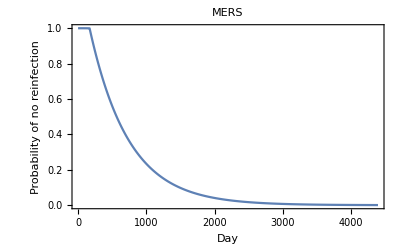

```mathematica
ListLinePlot[mersprobnoreinfectiontimecourse,
PlotRange->{0,1}, 
PlotLabel->"MERS", 
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability of no reinfection"}]
```

```mathematica
merscontinuousprobnoreinfection=Interpolation[mersprobnoreinfectiontimecourse]
```

InterpolatingFunction[…]

```mathematica
merscontinuousprobnoreinfection[1]
```

1.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[merscontinuousprobnoreinfection[x]-0.95],
 1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{37.4312,1.24771,0.102551}

These are the 5% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.FindMinimum[{Abs[merscontinuousprobnoreinfection[x]-0.50],
 1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{566.1,18.87,1.55096}

These are the 50% quantiles (medians) for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.FindMinimum[{Abs[merscontinuousprobnoreinfection[x]-0.05],
  1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{1883.08,62.7694,5.15913}

These are the 95% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
mersprobreinfectiondensity={};
day=0;
While[day<4393,
Increment[day];
AppendTo[mersprobreinfectiondensity, 
If[day<lengthabtc,
mersprobinfgivenaod[mersantibodytimecourseplusexp[[day]]]*mersprobnoreinfectiontimecourse[[day]],
mersprobinfgivenaod[mersantibodytimecourseplusexp[[lengthabtc]]]*mersprobnoreinfectiontimecourse[[day]]
]
]
];
```

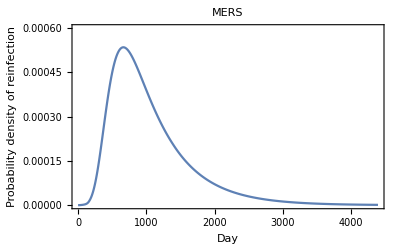

```mathematica
ListLinePlot[mersprobreinfectiondensity,
PlotLabel->"MERS",
PlotRange->{0, 0.0006},
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability density of reinfection"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["MERS_PrInf-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[mersprobreinfectiondensity,
PlotLabel->"MERS",
PlotRange->{0, 0.0007},
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability density of reinfection"}]
]
```

MERS_PrInf-by-Day_21Jan2021.pdf

## SARS-CoV-1

### SARS-CoV-1 Average peak-normalized OD post-infection (3 mo.)

Input Data: Average peak-normalized ELIZA ODs for SARS-CoV-1 S IgG antibodies from Wu et al. 2007, “Duration of antibody responses after severe acute respiratory syndrome”, Emerging Infectious Diseases.

days : 90, 180, 365, 730, 1095
ODs : 1, 0.96, 0.638, 0.516, 0.249

```mathematica
sarscov1data={
{1,90, SARSCoV1,1,  TRUE,NA, NA},
{2,180, SARSCoV1,0.96, FALSE, (180-90), (0.96-1)/(180-90)},
{3,365, SARSCoV1,0.638,  FALSE,(365-180), (0.638-0.96)/(365-180)},
{4,730, SARSCoV1, 0.516, FALSE,(730-365),  (0.516-0.638)/(730-365)},
{5,1095, SARSCoV1, 0.249, FALSE,(1095-730),  (0.249-0.516)/(1095-730)}
}
```

{{1,90,SARSCoV1,1,TRUE,NA,NA},{2,180,SARSCoV1,0.96,FALSE,90,-0.000444444},{3,365,SARSCoV1,0.638,FALSE,185,-0.00174054},{4,730,SARSCoV1,0.516,FALSE,365,-0.000334247},{5,1095,SARSCoV1,0.249,FALSE,365,-0.000731507}}

### SARS-CoV-1 Waning of Antibody OD

```mathematica
sarscov1datalength=Length[sarscov1data]
```

5

```mathematica
Table[
{aod,
Table[
If [
Or[
sarscov1data[[index-1, 4]]≥aod≥sarscov1data[[index, 4]],
sarscov1data[[index-1, 4]]≤aod≤sarscov1data[[index, 4]]],
sarscov1data[[index, 7]],
Nothing],
{index, 2, sarscov1datalength}
]
}
, {aod, 0,1, 0.05}]
```

{{0.,{}},{0.05,{}},{0.1,{}},{0.15,{}},{0.2,{}},{0.25,{-0.000731507}},{0.3,{-0.000731507}},{0.35,{-0.000731507}},{0.4,{-0.000731507}},{0.45,{-0.000731507}},{0.5,{-0.000731507}},{0.55,{-0.000334247}},{0.6,{-0.000334247}},{0.65,{-0.00174054}},{0.7,{-0.00174054}},{0.75,{-0.00174054}},{0.8,{-0.00174054}},{0.85,{-0.00174054}},{0.9,{-0.00174054}},{0.95,{-0.00174054}},{1.,{-0.000444444}}}

```mathematica
sarscov1paddedmeanwaning=Table[
{aod,
Table[
If [
Or[
sarscov1data[[index-1, 4]]≥aod≥sarscov1data[[index, 4]],
sarscov1data[[index-1, 4]]≤aod≤sarscov1data[[index, 4]]],
sarscov1data[[index, 7]],
Nothing],
{index, 2, sarscov1datalength}
]
}
, {aod, 0.25,1, 0.05}]
```

{{0.25,{-0.000731507}},{0.3,{-0.000731507}},{0.35,{-0.000731507}},{0.4,{-0.000731507}},{0.45,{-0.000731507}},{0.5,{-0.000731507}},{0.55,{-0.000334247}},{0.6,{-0.000334247}},{0.65,{-0.00174054}},{0.7,{-0.00174054}},{0.75,{-0.00174054}},{0.8,{-0.00174054}},{0.85,{-0.00174054}},{0.9,{-0.00174054}},{0.95,{-0.00174054}},{1.,{-0.000444444}}}

```mathematica
sarscov1meanwaning=sarscov1paddedmeanwaning
```

{{0.25,{-0.000731507}},{0.3,{-0.000731507}},{0.35,{-0.000731507}},{0.4,{-0.000731507}},{0.45,{-0.000731507}},{0.5,{-0.000731507}},{0.55,{-0.000334247}},{0.6,{-0.000334247}},{0.65,{-0.00174054}},{0.7,{-0.00174054}},{0.75,{-0.00174054}},{0.8,{-0.00174054}},{0.85,{-0.00174054}},{0.9,{-0.00174054}},{0.95,{-0.00174054}},{1.,{-0.000444444}}}

```mathematica
TableForm[sarscov1meanwaning]
```

0.25 | -0.000731507
0.3 | -0.000731507
0.35 | -0.000731507
0.4 | -0.000731507
0.45 | -0.000731507
0.5 | -0.000731507
0.55 | -0.000334247
0.6 | -0.000334247
0.65 | -0.00174054
0.7 | -0.00174054
0.75 | -0.00174054
0.8 | -0.00174054
0.85 | -0.00174054
0.9 | -0.00174054
0.95 | -0.00174054
1. | -0.000444444

```mathematica
sarscov1antibodywaning=Interpolation[sarscov1meanwaning]
```

InterpolatingFunction[…]

```mathematica
sarscov1antibodytimecourse={1.0};
day=1;
While[sarscov1antibodytimecourse[[day]]≥0.25,
sarscov1antibodytimecourse=Append[sarscov1antibodytimecourse, sarscov1antibodytimecourse[[day]]+sarscov1antibodywaning[sarscov1antibodytimecourse[[day]]]];
sarscov1antibodytimecourse=Flatten[sarscov1antibodytimecourse];
Increment[day];
];
sarscov1antibodytimecourse
```

{1.,0.999556,0.99909,0.998603,0.998093,0.99756,0.997002,0.99642,0.995812,0.995178,0.994516,0.993826,0.993108,0.99236,0.991582,0.990773,0.989933,0.989061,0.988156,0.987219,0.986248,0.985243,0.984205,0.983132,0.982026,0.980884,0.979709,0.978499,0.977255,0.975978,0.974667,0.973323,0.971947,0.97054,0.969101,0.967632,0.966134,0.964607,0.963054,0.961474,0.959869,0.958241,0.95659,0.954918,0.953227,0.951517,0.94979,0.948048,0.946291,0.944522,0.942742,0.940952,0.939153,0.937347,0.935535,0.933718,0.931898,0.930076,0.928253,0.926429,0.924606,0.922785,0.920967,0.919151,0.91734,0.915534,0.913733,0.911937,0.910148,0.908366,0.90659,0.904821,0.90306,0.901306,0.89956,0.89782,0.896079,0.894339,0.892598,0.890858,0.889117,0.887376,0.885636,0.883895,0.882155,0.880414,0.878674,0.876933,0.875193,0.873452,0.871712,0.869971,0.868231,0.86649,0.864749,0.863009,0.861268,0.859528,0.857787,0.856047,0.854306,0.852566,0.850825,0.849085,0.847344,0.845604,0.843863,0.842122,0.840382,0.838641,0.836901,0.83516,0.83342,0.831679,0.829939,0.828198,0.826458,0.824717,0.822976,0.821236,0.819495,0.817755,0.816014,0.814274,0.812533,0.810793,0.809052,0.807312,0.805571,0.803831,0.80209,0.800349,0.798609,0.796868,0.795128,0.793387,0.791647,0.789906,0.788166,0.786425,0.784685,0.782944,0.781204,0.779463,0.777722,0.775982,0.774241,0.772501,0.77076,0.76902,0.767279,0.765539,0.763798,0.762058,0.760317,0.758576,0.756836,0.755095,0.753355,0.751614,0.749874,0.748133,0.746393,0.744652,0.742912,0.741171,0.739431,0.73769,0.735949,0.734209,0.732468,0.730728,0.728987,0.727247,0.725506,0.723766,0.722025,0.720285,0.718544,0.716804,0.715063,0.713322,0.711582,0.709841,0.708101,0.70636,0.70462,0.702879,0.701139,0.699398,0.697655,0.695903,0.694144,0.692376,0.690601,0.688818,0.687027,0.68523,0.683426,0.681616,0.679801,0.677982,0.676158,0.674331,0.672502,0.670671,0.668841,0.667011,0.665183,0.663358,0.661538,0.659724,0.657917,0.656119,0.654331,0.652555,0.650793,0.649045,0.647327,0.645651,0.644017,0.642426,0.640878,0.639372,0.637908,0.636485,0.635103,0.633762,0.63246,0.631197,0.629972,0.628783,0.627631,0.626513,0.62543,0.624379,0.623361,0.622373,0.621416,0.620488,0.619587,0.618714,0.617867,0.617046,0.616249,0.615476,0.614725,0.613997,0.61329,0.612603,0.611936,0.611289,0.610659,0.610048,0.609454,0.608876,0.608314,0.607768,0.607236,0.606719,0.606216,0.605726,0.605249,0.604784,0.604332,0.603891,0.603462,0.603043,0.602635,0.602237,0.601849,0.601471,0.601101,0.600741,0.600389,0.600046,0.59971,0.599379,0.599051,0.598727,0.598406,0.598088,0.597773,0.597462,0.597153,0.596847,0.596543,0.596243,0.595945,0.595649,0.595357,0.595066,0.594778,0.594492,0.594208,0.593927,0.593648,0.59337,0.593095,0.592822,0.59255,0.592281,0.592013,0.591747,0.591483,0.59122,0.590959,0.590699,0.590441,0.590185,0.58993,0.589676,0.589424,0.589173,0.588923,0.588675,0.588428,0.588182,0.587937,0.587693,0.58745,0.587209,0.586968,0.586728,0.58649,0.586252,0.586015,0.585779,0.585544,0.58531,0.585076,0.584844,0.584612,0.58438,0.58415,0.58392,0.583691,0.583462,0.583234,0.583006,0.582779,0.582553,0.582326,0.582101,0.581876,0.581651,0.581427,0.581203,0.580979,0.580756,0.580533,0.58031,0.580088,0.579866,0.579644,0.579423,0.579201,0.57898,0.578759,0.578538,0.578317,0.578096,0.577875,0.577655,0.577434,0.577214,0.576993,0.576772,0.576552,0.576331,0.57611,0.57589,0.575669,0.575448,0.575227,0.575005,0.574784,0.574562,0.57434,0.574118,0.573895,0.573673,0.57345,0.573227,0.573003,0.572779,0.572555,0.57233,0.572105,0.57188,0.571654,0.571428,0.571201,0.570974,0.570746,0.570518,0.570289,0.570059,0.569829,0.569599,0.569368,0.569136,0.568904,0.568671,0.568437,0.568202,0.567967,0.567731,0.567495,0.567257,0.567019,0.56678,0.56654,0.5663,0.566058,0.565815,0.565572,0.565328,0.565082,0.564836,0.564589,0.56434,0.564091,0.563841,0.563589,0.563337,0.563083,0.562828,0.562572,0.562315,0.562056,0.561796,0.561535,0.561273,0.56101,0.560745,0.560478,0.560211,0.559942,0.559671,0.559399,0.559126,0.558851,0.558575,0.558296,0.558017,0.557736,0.557453,0.557168,0.556882,0.556594,0.556304,0.556013,0.555719,0.555424,0.555127,0.554828,0.554528,0.554225,0.55392,0.553613,0.553304,0.552994,0.55268,0.552365,0.552048,0.551728,0.551407,0.551082,0.550756,0.550427,0.550096,0.549763,0.549427,0.549089,0.548748,0.548406,0.548061,0.547713,0.547364,0.547011,0.546657,0.546299,0.54594,0.545577,0.545212,0.544845,0.544474,0.544101,0.543725,0.543347,0.542965,0.542581,0.542193,0.541803,0.54141,0.541014,0.540614,0.540212,0.539806,0.539397,0.538985,0.53857,0.538151,0.537729,0.537303,0.536874,0.536442,0.536006,0.535566,0.535123,0.534676,0.534226,0.533772,0.533313,0.532852,0.532386,0.531916,0.531442,0.530965,0.530483,0.529997,0.529507,0.529013,0.528514,0.528012,0.527505,0.526993,0.526478,0.525957,0.525433,0.524904,0.52437,0.523832,0.523289,0.522741,0.522189,0.521632,0.52107,0.520503,0.519932,0.519355,0.518774,0.518188,0.517597,0.517001,0.516399,0.515793,0.515182,0.514566,0.513944,0.513317,0.512686,0.512049,0.511407,0.51076,0.510107,0.50945,0.508787,0.508119,0.507446,0.506768,0.506084,0.505396,0.504702,0.504003,0.5033,0.502591,0.501877,0.501158,0.500434,0.499706,0.498973,0.498239,0.497503,0.496766,0.496027,0.495286,0.494543,0.4938,0.493055,0.492309,0.491561,0.490813,0.490063,0.489313,0.488561,0.487809,0.487056,0.486302,0.485548,0.484793,0.484038,0.483282,0.482526,0.48177,0.481013,0.480257,0.4795,0.478743,0.477986,0.477229,0.476472,0.475715,0.474959,0.474202,0.473446,0.472691,0.471935,0.47118,0.470426,0.469672,0.468918,0.468165,0.467413,0.466661,0.46591,0.465159,0.46441,0.463661,0.462912,0.462165,0.461418,0.460672,0.459927,0.459183,0.45844,0.457698,0.456956,0.456216,0.455476,0.454737,0.454,0.453263,0.452527,0.451792,0.451058,0.450326,0.449594,0.448862,0.448131,0.447399,0.446668,0.445936,0.445205,0.444473,0.443742,0.44301,0.442279,0.441547,0.440816,0.440084,0.439352,0.438621,0.437889,0.437158,0.436426,0.435695,0.434963,0.434232,0.4335,0.432769,0.432037,0.431306,0.430574,0.429843,0.429111,0.42838,0.427648,0.426917,0.426185,0.425454,0.424722,0.423991,0.423259,0.422528,0.421796,0.421065,0.420333,0.419602,0.41887,0.418139,0.417407,0.416676,0.415944,0.415213,0.414481,0.41375,0.413018,0.412287,0.411555,0.410824,0.410092,0.409361,0.408629,0.407898,0.407166,0.406435,0.405703,0.404972,0.40424,0.403509,0.402777,0.402046,0.401314,0.400583,0.399851,0.39912,0.398388,0.397657,0.396925,0.396194,0.395462,0.394731,0.393999,0.393268,0.392536,0.391805,0.391073,0.390342,0.38961,0.388879,0.388147,0.387416,0.386684,0.385952,0.385221,0.384489,0.383758,0.383026,0.382295,0.381563,0.380832,0.3801,0.379369,0.378637,0.377906,0.377174,0.376443,0.375711,0.37498,0.374248,0.373517,0.372785,0.372054,0.371322,0.370591,0.369859,0.369128,0.368396,0.367665,0.366933,0.366202,0.36547,0.364739,0.364007,0.363276,0.362544,0.361813,0.361081,0.36035,0.359618,0.358887,0.358155,0.357424,0.356692,0.355961,0.355229,0.354498,0.353766,0.353035,0.352303,0.351572,0.35084,0.350109,0.349377,0.348646,0.347914,0.347183,0.346451,0.34572,0.344988,0.344257,0.343525,0.342794,0.342062,0.341331,0.340599,0.339868,0.339136,0.338405,0.337673,0.336942,0.33621,0.335479,0.334747,0.334016,0.333284,0.332552,0.331821,0.331089,0.330358,0.329626,0.328895,0.328163,0.327432,0.3267,0.325969,0.325237,0.324506,0.323774,0.323043,0.322311,0.32158,0.320848,0.320117,0.319385,0.318654,0.317922,0.317191,0.316459,0.315728,0.314996,0.314265,0.313533,0.312802,0.31207,0.311339,0.310607,0.309876,0.309144,0.308413,0.307681,0.30695,0.306218,0.305487,0.304755,0.304024,0.303292,0.302561,0.301829,0.301098,0.300366,0.299635,0.298903,0.298172,0.29744,0.296709,0.295977,0.295246,0.294514,0.293783,0.293051,0.29232,0.291588,0.290857,0.290125,0.289394,0.288662,0.287931,0.287199,0.286468,0.285736,0.285005,0.284273,0.283542,0.28281,0.282079,0.281347,0.280616,0.279884,0.279152,0.278421,0.277689,0.276958,0.276226,0.275495,0.274763,0.274032,0.2733,0.272569,0.271837,0.271106,0.270374,0.269643,0.268911,0.26818,0.267448,0.266717,0.265985,0.265254,0.264522,0.263791,0.263059,0.262328,0.261596,0.260865,0.260133,0.259402,0.25867,0.257939,0.257207,0.256476,0.255744,0.255013,0.254281,0.25355,0.252818,0.252087,0.251355,0.250624,0.249892}

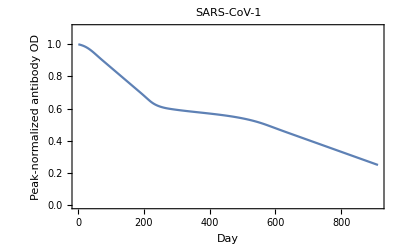

```mathematica
ListLinePlot[sarscov1antibodytimecourse,
PlotRange->{0,1.1}, 
PlotLabel->"SARS-CoV-1", 
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
```

```mathematica
Export["SARS-CoV-1-Antibody-Time-Course.csv", sarscov1antibodytimecourse]
```

SARS-CoV-1-Antibody-Time-Course.csv

```mathematica
sarscov1baseline=.1298892
```

0.129889

This baseline peak-normalized S IgG antibody level for SARS-CoV-1 comes from the ancestral and descendent states analysis that used the baselines for the human “seasonal” coronaviruses to estimate the baselines for the zoonotic coronaviruses.

```mathematica
sarscov1lsfuncwfixedbaseline=Sum[(sarscov1antibodytimecourse[[index]]-(sarscov1baseline+(1-sarscov1baseline)*Exp[-lambda*index]))^2, {index, 1, Length[sarscov1antibodytimecourse]}]
```

(0.120003-0.870111 ⅇ^(-912 lambda))^2+(0.120735-0.870111 ⅇ^(-911 lambda))^2+908+(0.869666-0.870111 ⅇ^(-2 lambda))^2+(0.870111-0.870111 ⅇ^-lambda)^2
 |  |  |  |

```mathematica
FindMinimum[{sarscov1lsfuncwfixedbaseline, lambda >0},{lambda, 0.002}]
```

{1.34955,{lambda→0.00175703}}

This value of lambda goes into the ancestral and descendent states analysis estimating a and b for the zoonotic coronaviruses.

```mathematica
sarscov1halflife=Log[2]/ lambda /.lambda->0.0017570301527402655
```

394.499

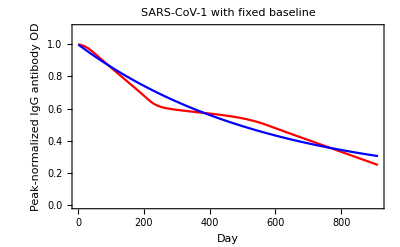

```mathematica
Show[
ListLinePlot[sarscov1antibodytimecourse,
PlotStyle->Red, 
PlotRange->{0,1.1}
],
Plot[sarscov1baseline+(1-sarscov1baseline)*Exp[-lambda days]/.lambda->0.0017570301527402655,{days,1,Length[sarscov1antibodytimecourse]},
PlotStyle->Blue,
PlotRange->{0,1.1}
], 
PlotLabel->"SARS-CoV-1 with fixed baseline", Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Peak-normalized IgG antibody OD"}]
```

```mathematica
Length[sarscov1antibodytimecourse]
```

912

```mathematica
sarscov1antibodytimecourseplusexp=sarscov1antibodytimecourse;
day=Length[sarscov1antibodytimecourse];
While[day<4393,
Increment[day];
AppendTo[sarscov1antibodytimecourseplusexp, sarscov1baseline+(sarscov1antibodytimecourseplusexp[[day-1]]- sarscov1baseline)*Exp[-0.0017570301527402655]]
]
```

```mathematica
sarscov1antibodytimecourseplusexp
```

{1.,0.999556,0.99909,0.998603,0.998093,0.99756,0.997002,0.99642,0.995812,0.995178,0.994516,0.993826,0.993108,0.99236,0.991582,0.990773,0.989933,0.989061,0.988156,0.987219,0.986248,0.985243,0.984205,0.983132,0.982026,0.980884,0.979709,0.978499,0.977255,0.975978,0.974667,0.973323,0.971947,0.97054,0.969101,0.967632,0.966134,0.964607,0.963054,0.961474,0.959869,0.958241,0.95659,0.954918,0.953227,0.951517,0.94979,0.948048,0.946291,0.944522,0.942742,0.940952,0.939153,0.937347,0.935535,0.933718,0.931898,0.930076,0.928253,0.926429,0.924606,0.922785,0.920967,0.919151,0.91734,0.915534,0.913733,0.911937,0.910148,0.908366,0.90659,0.904821,0.90306,0.901306,0.89956,0.89782,0.896079,0.894339,0.892598,0.890858,0.889117,0.887376,0.885636,0.883895,0.882155,0.880414,0.878674,0.876933,0.875193,0.873452,0.871712,0.869971,0.868231,0.86649,0.864749,0.863009,0.861268,0.859528,0.857787,0.856047,0.854306,0.852566,0.850825,0.849085,0.847344,0.845604,0.843863,0.842122,0.840382,0.838641,0.836901,0.83516,0.83342,0.831679,0.829939,0.828198,0.826458,0.824717,0.822976,0.821236,0.819495,0.817755,0.816014,0.814274,0.812533,0.810793,0.809052,0.807312,0.805571,0.803831,0.80209,0.800349,0.798609,0.796868,0.795128,0.793387,0.791647,0.789906,0.788166,0.786425,0.784685,0.782944,0.781204,0.779463,0.777722,0.775982,0.774241,0.772501,0.77076,0.76902,0.767279,0.765539,0.763798,0.762058,0.760317,0.758576,0.756836,0.755095,0.753355,0.751614,0.749874,0.748133,0.746393,0.744652,0.742912,0.741171,0.739431,0.73769,0.735949,0.734209,0.732468,0.730728,0.728987,0.727247,0.725506,0.723766,0.722025,0.720285,0.718544,0.716804,0.715063,0.713322,0.711582,0.709841,0.708101,0.70636,0.70462,0.702879,0.701139,0.699398,0.697655,0.695903,0.694144,0.692376,0.690601,0.688818,0.687027,0.68523,0.683426,0.681616,0.679801,0.677982,0.676158,0.674331,0.672502,0.670671,0.668841,0.667011,0.665183,0.663358,0.661538,0.659724,0.657917,0.656119,0.654331,0.652555,0.650793,0.649045,0.647327,0.645651,0.644017,0.642426,0.640878,0.639372,0.637908,0.636485,0.635103,0.633762,0.63246,0.631197,0.629972,0.628783,0.627631,0.626513,0.62543,0.624379,0.623361,0.622373,0.621416,0.620488,0.619587,0.618714,0.617867,0.617046,0.616249,0.615476,0.614725,0.613997,0.61329,0.612603,0.611936,0.611289,0.610659,0.610048,0.609454,0.608876,0.608314,0.607768,0.607236,0.606719,0.606216,0.605726,0.605249,0.604784,0.604332,0.603891,0.603462,0.603043,0.602635,0.602237,0.601849,0.601471,0.601101,0.600741,0.600389,0.600046,0.59971,0.599379,0.599051,0.598727,0.598406,0.598088,0.597773,0.597462,0.597153,0.596847,0.596543,0.596243,0.595945,0.595649,0.595357,0.595066,0.594778,0.594492,0.594208,0.593927,0.593648,0.59337,0.593095,0.592822,0.59255,0.592281,0.592013,0.591747,0.591483,0.59122,0.590959,0.590699,0.590441,0.590185,0.58993,0.589676,0.589424,0.589173,0.588923,0.588675,0.588428,0.588182,0.587937,0.587693,0.58745,0.587209,0.586968,0.586728,0.58649,0.586252,0.586015,0.585779,0.585544,0.58531,0.585076,0.584844,0.584612,0.58438,0.58415,0.58392,0.583691,0.583462,0.583234,0.583006,0.582779,0.582553,0.582326,0.582101,0.581876,0.581651,0.581427,0.581203,0.580979,0.580756,0.580533,0.58031,0.580088,0.579866,0.579644,0.579423,0.579201,0.57898,0.578759,0.578538,0.578317,0.578096,0.577875,0.577655,0.577434,0.577214,0.576993,0.576772,0.576552,0.576331,0.57611,0.57589,0.575669,0.575448,0.575227,0.575005,0.574784,0.574562,0.57434,0.574118,0.573895,0.573673,0.57345,0.573227,0.573003,0.572779,0.572555,0.57233,0.572105,0.57188,0.571654,0.571428,0.571201,0.570974,0.570746,0.570518,0.570289,0.570059,0.569829,0.569599,0.569368,0.569136,0.568904,0.568671,0.568437,0.568202,0.567967,0.567731,0.567495,0.567257,0.567019,0.56678,0.56654,0.5663,0.566058,0.565815,0.565572,0.565328,0.565082,0.564836,0.564589,0.56434,0.564091,0.563841,0.563589,0.563337,0.563083,0.562828,0.562572,0.562315,0.562056,0.561796,0.561535,0.561273,0.56101,0.560745,0.560478,0.560211,0.559942,0.559671,0.559399,0.559126,0.558851,0.558575,0.558296,0.558017,0.557736,0.557453,0.557168,0.556882,0.556594,0.556304,0.556013,0.555719,0.555424,0.555127,0.554828,0.554528,0.554225,0.55392,0.553613,0.553304,0.552994,0.55268,0.552365,0.552048,0.551728,0.551407,0.551082,0.550756,0.550427,0.550096,0.549763,0.549427,0.549089,0.548748,0.548406,0.548061,0.547713,0.547364,0.547011,0.546657,0.546299,0.54594,0.545577,0.545212,0.544845,0.544474,0.544101,0.543725,0.543347,0.542965,0.542581,0.542193,0.541803,0.54141,0.541014,0.540614,0.540212,0.539806,0.539397,0.538985,0.53857,0.538151,0.537729,0.537303,0.536874,0.536442,0.536006,0.535566,0.535123,0.534676,0.534226,0.533772,0.533313,0.532852,0.532386,0.531916,0.531442,0.530965,0.530483,0.529997,0.529507,0.529013,0.528514,0.528012,0.527505,0.526993,0.526478,0.525957,0.525433,0.524904,0.52437,0.523832,0.523289,0.522741,0.522189,0.521632,0.52107,0.520503,0.519932,0.519355,0.518774,0.518188,0.517597,0.517001,0.516399,0.515793,0.515182,0.514566,0.513944,0.513317,0.512686,0.512049,0.511407,0.51076,0.510107,0.50945,0.508787,0.508119,0.507446,0.506768,0.506084,0.505396,0.504702,0.504003,0.5033,0.502591,0.501877,0.501158,0.500434,0.499706,0.498973,0.498239,0.497503,0.496766,0.496027,0.495286,0.494543,0.4938,0.493055,0.492309,0.491561,0.490813,0.490063,0.489313,0.488561,0.487809,0.487056,0.486302,0.485548,0.484793,0.484038,0.483282,0.482526,0.48177,0.481013,0.480257,0.4795,0.478743,0.477986,0.477229,0.476472,0.475715,0.474959,0.474202,0.473446,0.472691,0.471935,0.47118,0.470426,0.469672,0.468918,0.468165,0.467413,0.466661,0.46591,0.465159,0.46441,0.463661,0.462912,0.462165,0.461418,0.460672,0.459927,0.459183,0.45844,0.457698,0.456956,0.456216,0.455476,0.454737,0.454,0.453263,0.452527,0.451792,0.451058,0.450326,0.449594,0.448862,0.448131,0.447399,0.446668,0.445936,0.445205,0.444473,0.443742,0.44301,0.442279,0.441547,0.440816,0.440084,0.439352,0.438621,0.437889,0.437158,0.436426,0.435695,0.434963,0.434232,0.4335,0.432769,0.432037,0.431306,0.430574,0.429843,0.429111,0.42838,0.427648,0.426917,0.426185,0.425454,0.424722,0.423991,0.423259,0.422528,0.421796,0.421065,0.420333,0.419602,0.41887,0.418139,0.417407,0.416676,0.415944,0.415213,0.414481,0.41375,0.413018,0.412287,0.411555,0.410824,0.410092,0.409361,0.408629,0.407898,0.407166,0.406435,0.405703,0.404972,0.40424,0.403509,0.402777,0.402046,0.401314,0.400583,0.399851,0.39912,0.398388,0.397657,0.396925,0.396194,0.395462,0.394731,0.393999,0.393268,0.392536,0.391805,0.391073,0.390342,0.38961,0.388879,0.388147,0.387416,0.386684,0.385952,0.385221,0.384489,0.383758,0.383026,0.382295,0.381563,0.380832,0.3801,0.379369,0.378637,0.377906,0.377174,0.376443,0.375711,0.37498,0.374248,0.373517,0.372785,0.372054,0.371322,0.370591,0.369859,0.369128,0.368396,0.367665,0.366933,0.366202,0.36547,0.364739,0.364007,0.363276,0.362544,0.361813,0.361081,0.36035,0.359618,0.358887,0.358155,0.357424,0.356692,0.355961,0.355229,0.354498,0.353766,0.353035,0.352303,0.351572,0.35084,0.350109,0.349377,0.348646,0.347914,0.347183,0.346451,0.34572,0.344988,0.344257,0.343525,0.342794,0.342062,0.341331,0.340599,0.339868,0.339136,0.338405,0.337673,0.336942,0.33621,0.335479,0.334747,0.334016,0.333284,0.332552,0.331821,0.331089,0.330358,0.329626,0.328895,0.328163,0.327432,0.3267,0.325969,0.325237,0.324506,0.323774,0.323043,0.322311,0.32158,0.320848,0.320117,0.319385,0.318654,0.317922,0.317191,0.316459,0.315728,0.314996,0.314265,0.313533,0.312802,0.31207,0.311339,0.310607,0.309876,0.309144,0.308413,0.307681,0.30695,0.306218,0.305487,0.304755,0.304024,0.303292,0.302561,0.301829,0.301098,0.300366,0.299635,0.298903,0.298172,0.29744,0.296709,0.295977,0.295246,0.294514,0.293783,0.293051,0.29232,0.291588,0.290857,0.290125,0.289394,0.288662,0.287931,0.287199,0.286468,0.285736,0.285005,0.284273,0.283542,0.28281,0.282079,0.281347,0.280616,0.279884,0.279152,0.278421,0.277689,0.276958,0.276226,0.275495,0.274763,0.274032,0.2733,0.272569,0.271837,0.271106,0.270374,0.269643,0.268911,0.26818,0.267448,0.266717,0.265985,0.265254,0.264522,0.263791,0.263059,0.262328,0.261596,0.260865,0.260133,0.259402,0.25867,0.257939,0.257207,0.256476,0.255744,0.255013,0.254281,0.25355,0.252818,0.252087,0.251355,0.250624,0.249892,0.249682,0.249471,0.249261,0.249052,0.248843,0.248634,0.248425,0.248217,0.24801,0.247802,0.247595,0.247389,0.247182,0.246976,0.246771,0.246566,0.246361,0.246156,0.245952,0.245748,0.245545,0.245342,0.245139,0.244937,0.244735,0.244533,0.244332,0.244131,0.243931,0.243731,0.243531,0.243331,0.243132,0.242933,0.242735,0.242537,0.242339,0.242142,0.241945,0.241748,0.241551,0.241355,0.24116,0.240964,0.240769,0.240575,0.24038,0.240187,0.239993,0.2398,0.239607,0.239414,0.239222,0.23903,0.238838,0.238647,0.238456,0.238265,0.238075,0.237885,0.237696,0.237506,0.237318,0.237129,0.236941,0.236753,0.236565,0.236378,0.236191,0.236004,0.235818,0.235632,0.235446,0.235261,0.235076,0.234892,0.234707,0.234523,0.23434,0.234156,0.233973,0.23379,0.233608,0.233426,0.233244,0.233063,0.232882,0.232701,0.23252,0.23234,0.23216,0.231981,0.231802,0.231623,0.231444,0.231266,0.231088,0.23091,0.230733,0.230556,0.230379,0.230203,0.230027,0.229851,0.229675,0.2295,0.229325,0.229151,0.228976,0.228802,0.228629,0.228456,0.228282,0.22811,0.227937,0.227765,0.227593,0.227422,0.227251,0.22708,0.226909,0.226739,0.226569,0.226399,0.22623,0.226061,0.225892,0.225723,0.225555,0.225387,0.225219,0.225052,0.224885,0.224718,0.224552,0.224386,0.22422,0.224054,0.223889,0.223724,0.223559,0.223395,0.22323,0.223067,0.222903,0.22274,0.222577,0.222414,0.222252,0.222089,0.221928,0.221766,0.221605,0.221444,0.221283,0.221123,0.220962,0.220802,0.220643,0.220484,0.220325,0.220166,0.220007,0.219849,0.219691,0.219534,0.219376,0.219219,0.219062,0.218906,0.218749,0.218593,0.218438,0.218282,0.218127,0.217972,0.217818,0.217663,0.217509,0.217355,0.217202,0.217048,0.216895,0.216743,0.21659,0.216438,0.216286,0.216134,0.215983,0.215832,0.215681,0.21553,0.21538,0.21523,0.21508,0.214931,0.214781,0.214632,0.214484,0.214335,0.214187,0.214039,0.213891,0.213744,0.213596,0.21345,0.213303,0.213156,0.21301,0.212864,0.212719,0.212573,0.212428,0.212283,0.212139,0.211994,0.21185,0.211706,0.211563,0.211419,0.211276,0.211133,0.210991,0.210848,0.210706,0.210564,0.210423,0.210281,0.21014,0.209999,0.209859,0.209718,0.209578,0.209438,0.209298,0.209159,0.20902,0.208881,0.208742,0.208604,0.208466,0.208328,0.20819,0.208053,0.207915,0.207778,0.207642,0.207505,0.207369,0.207233,0.207097,0.206962,0.206826,0.206691,0.206556,0.206422,0.206287,0.206153,0.206019,0.205886,0.205752,0.205619,0.205486,0.205354,0.205221,0.205089,0.204957,0.204825,0.204694,0.204562,0.204431,0.2043,0.20417,0.204039,0.203909,0.203779,0.203649,0.20352,0.203391,0.203262,0.203133,0.203004,0.202876,0.202748,0.20262,0.202492,0.202365,0.202238,0.202111,0.201984,0.201857,0.201731,0.201605,0.201479,0.201353,0.201228,0.201102,0.200977,0.200853,0.200728,0.200604,0.20048,0.200356,0.200232,0.200108,0.199985,0.199862,0.199739,0.199617,0.199494,0.199372,0.19925,0.199128,0.199007,0.198885,0.198764,0.198643,0.198523,0.198402,0.198282,0.198162,0.198042,0.197922,0.197803,0.197684,0.197565,0.197446,0.197327,0.197209,0.197091,0.196973,0.196855,0.196738,0.19662,0.196503,0.196386,0.196269,0.196153,0.196036,0.19592,0.195804,0.195689,0.195573,0.195458,0.195343,0.195228,0.195113,0.194999,0.194884,0.19477,0.194656,0.194543,0.194429,0.194316,0.194203,0.19409,0.193977,0.193865,0.193752,0.19364,0.193528,0.193417,0.193305,0.193194,0.193083,0.192972,0.192861,0.19275,0.19264,0.19253,0.19242,0.19231,0.192201,0.192091,0.191982,0.191873,0.191764,0.191656,0.191547,0.191439,0.191331,0.191223,0.191115,0.191008,0.190901,0.190793,0.190687,0.19058,0.190473,0.190367,0.190261,0.190155,0.190049,0.189943,0.189838,0.189733,0.189628,0.189523,0.189418,0.189314,0.189209,0.189105,0.189001,0.188897,0.188794,0.18869,0.188587,0.188484,0.188381,0.188279,0.188176,0.188074,0.187972,0.18787,0.187768,0.187666,0.187565,0.187464,0.187363,0.187262,0.187161,0.18706,0.18696,0.18686,0.18676,0.18666,0.18656,0.186461,0.186362,0.186262,0.186163,0.186065,0.185966,0.185868,0.185769,0.185671,0.185573,0.185476,0.185378,0.185281,0.185183,0.185086,0.184989,0.184893,0.184796,0.1847,0.184603,0.184507,0.184412,0.184316,0.18422,0.184125,0.18403,0.183935,0.18384,0.183745,0.183651,0.183556,0.183462,0.183368,0.183274,0.18318,0.183087,0.182993,0.1829,0.182807,0.182714,0.182621,0.182529,0.182436,0.182344,0.182252,0.18216,0.182068,0.181977,0.181885,0.181794,0.181703,0.181612,0.181521,0.181431,0.18134,0.18125,0.18116,0.18107,0.18098,0.18089,0.180801,0.180711,0.180622,0.180533,0.180444,0.180355,0.180267,0.180178,0.18009,0.180002,0.179914,0.179826,0.179738,0.179651,0.179564,0.179476,0.179389,0.179302,0.179216,0.179129,0.179043,0.178956,0.17887,0.178784,0.178698,0.178613,0.178527,0.178442,0.178357,0.178271,0.178186,0.178102,0.178017,0.177933,0.177848,0.177764,0.17768,0.177596,0.177512,0.177429,0.177345,0.177262,0.177179,0.177096,0.177013,0.17693,0.176848,0.176765,0.176683,0.176601,0.176519,0.176437,0.176355,0.176274,0.176192,0.176111,0.17603,0.175949,0.175868,0.175787,0.175707,0.175626,0.175546,0.175466,0.175386,0.175306,0.175226,0.175147,0.175067,0.174988,0.174909,0.17483,0.174751,0.174672,0.174593,0.174515,0.174437,0.174358,0.17428,0.174202,0.174125,0.174047,0.173969,0.173892,0.173815,0.173738,0.173661,0.173584,0.173507,0.173431,0.173354,0.173278,0.173202,0.173126,0.17305,0.172974,0.172898,0.172823,0.172747,0.172672,0.172597,0.172522,0.172447,0.172373,0.172298,0.172224,0.172149,0.172075,0.172001,0.171927,0.171853,0.17178,0.171706,0.171633,0.171559,0.171486,0.171413,0.17134,0.171268,0.171195,0.171122,0.17105,0.170978,0.170906,0.170834,0.170762,0.17069,0.170618,0.170547,0.170475,0.170404,0.170333,0.170262,0.170191,0.17012,0.17005,0.169979,0.169909,0.169839,0.169769,0.169699,0.169629,0.169559,0.169489,0.16942,0.16935,0.169281,0.169212,0.169143,0.169074,0.169005,0.168937,0.168868,0.1688,0.168731,0.168663,0.168595,0.168527,0.168459,0.168392,0.168324,0.168256,0.168189,0.168122,0.168055,0.167988,0.167921,0.167854,0.167787,0.167721,0.167655,0.167588,0.167522,0.167456,0.16739,0.167324,0.167258,0.167193,0.167127,0.167062,0.166997,0.166932,0.166867,0.166802,0.166737,0.166672,0.166608,0.166543,0.166479,0.166415,0.16635,0.166286,0.166223,0.166159,0.166095,0.166032,0.165968,0.165905,0.165842,0.165778,0.165715,0.165653,0.16559,0.165527,0.165465,0.165402,0.16534,0.165277,0.165215,0.165153,0.165091,0.16503,0.164968,0.164906,0.164845,0.164784,0.164722,0.164661,0.1646,0.164539,0.164478,0.164418,0.164357,0.164296,0.164236,0.164176,0.164116,0.164056,0.163996,0.163936,0.163876,0.163816,0.163757,0.163697,0.163638,0.163579,0.163519,0.16346,0.163402,0.163343,0.163284,0.163225,0.163167,0.163108,0.16305,0.162992,0.162934,0.162876,0.162818,0.16276,0.162702,0.162645,0.162587,0.16253,0.162473,0.162415,0.162358,0.162301,0.162244,0.162188,0.162131,0.162074,0.162018,0.161961,0.161905,0.161849,0.161793,0.161737,0.161681,0.161625,0.161569,0.161514,0.161458,0.161403,0.161347,0.161292,0.161237,0.161182,0.161127,0.161072,0.161018,0.160963,0.160908,0.160854,0.1608,0.160745,0.160691,0.160637,0.160583,0.160529,0.160475,0.160422,0.160368,0.160315,0.160261,0.160208,0.160155,0.160101,0.160048,0.159995,0.159943,0.15989,0.159837,0.159785,0.159732,0.15968,0.159627,0.159575,0.159523,0.159471,0.159419,0.159367,0.159316,0.159264,0.159212,0.159161,0.15911,0.159058,0.159007,0.158956,0.158905,0.158854,0.158803,0.158752,0.158702,0.158651,0.158601,0.15855,0.1585,0.15845,0.1584,0.158349,0.1583,0.15825,0.1582,0.15815,0.158101,0.158051,0.158002,0.157952,0.157903,0.157854,0.157805,0.157756,0.157707,0.157658,0.157609,0.157561,0.157512,0.157463,0.157415,0.157367,0.157318,0.15727,0.157222,0.157174,0.157126,0.157079,0.157031,0.156983,0.156936,0.156888,0.156841,0.156793,0.156746,0.156699,0.156652,0.156605,0.156558,0.156511,0.156465,0.156418,0.156371,0.156325,0.156278,0.156232,0.156186,0.15614,0.156094,0.156048,0.156002,0.155956,0.15591,0.155864,0.155819,0.155773,0.155728,0.155683,0.155637,0.155592,0.155547,0.155502,0.155457,0.155412,0.155367,0.155322,0.155278,0.155233,0.155189,0.155144,0.1551,0.155056,0.155012,0.154968,0.154923,0.15488,0.154836,0.154792,0.154748,0.154705,0.154661,0.154617,0.154574,0.154531,0.154487,0.154444,0.154401,0.154358,0.154315,0.154272,0.15423,0.154187,0.154144,0.154102,0.154059,0.154017,0.153974,0.153932,0.15389,0.153848,0.153806,0.153764,0.153722,0.15368,0.153638,0.153596,0.153555,0.153513,0.153472,0.15343,0.153389,0.153348,0.153307,0.153265,0.153224,0.153183,0.153143,0.153102,0.153061,0.15302,0.15298,0.152939,0.152899,0.152858,0.152818,0.152778,0.152738,0.152697,0.152657,0.152617,0.152578,0.152538,0.152498,0.152458,0.152419,0.152379,0.15234,0.1523,0.152261,0.152222,0.152182,0.152143,0.152104,0.152065,0.152026,0.151987,0.151949,0.15191,0.151871,0.151833,0.151794,0.151756,0.151717,0.151679,0.151641,0.151603,0.151564,0.151526,0.151488,0.15145,0.151413,0.151375,0.151337,0.151299,0.151262,0.151224,0.151187,0.15115,0.151112,0.151075,0.151038,0.151001,0.150964,0.150927,0.15089,0.150853,0.150816,0.150779,0.150743,0.150706,0.150669,0.150633,0.150597,0.15056,0.150524,0.150488,0.150451,0.150415,0.150379,0.150343,0.150307,0.150272,0.150236,0.1502,0.150164,0.150129,0.150093,0.150058,0.150022,0.149987,0.149952,0.149917,0.149881,0.149846,0.149811,0.149776,0.149741,0.149707,0.149672,0.149637,0.149602,0.149568,0.149533,0.149499,0.149464,0.14943,0.149396,0.149361,0.149327,0.149293,0.149259,0.149225,0.149191,0.149157,0.149123,0.14909,0.149056,0.149022,0.148989,0.148955,0.148922,0.148888,0.148855,0.148822,0.148788,0.148755,0.148722,0.148689,0.148656,0.148623,0.14859,0.148557,0.148525,0.148492,0.148459,0.148427,0.148394,0.148362,0.148329,0.148297,0.148265,0.148232,0.1482,0.148168,0.148136,0.148104,0.148072,0.14804,0.148008,0.147976,0.147944,0.147913,0.147881,0.14785,0.147818,0.147787,0.147755,0.147724,0.147692,0.147661,0.14763,0.147599,0.147568,0.147537,0.147506,0.147475,0.147444,0.147413,0.147382,0.147352,0.147321,0.14729,0.14726,0.147229,0.147199,0.147169,0.147138,0.147108,0.147078,0.147048,0.147017,0.146987,0.146957,0.146927,0.146897,0.146868,0.146838,0.146808,0.146778,0.146749,0.146719,0.14669,0.14666,0.146631,0.146601,0.146572,0.146543,0.146513,0.146484,0.146455,0.146426,0.146397,0.146368,0.146339,0.14631,0.146281,0.146253,0.146224,0.146195,0.146167,0.146138,0.146109,0.146081,0.146053,0.146024,0.145996,0.145968,0.145939,0.145911,0.145883,0.145855,0.145827,0.145799,0.145771,0.145743,0.145715,0.145688,0.14566,0.145632,0.145604,0.145577,0.145549,0.145522,0.145494,0.145467,0.14544,0.145412,0.145385,0.145358,0.145331,0.145304,0.145277,0.14525,0.145223,0.145196,0.145169,0.145142,0.145115,0.145089,0.145062,0.145035,0.145009,0.144982,0.144956,0.144929,0.144903,0.144876,0.14485,0.144824,0.144798,0.144771,0.144745,0.144719,0.144693,0.144667,0.144641,0.144615,0.144589,0.144564,0.144538,0.144512,0.144487,0.144461,0.144435,0.14441,0.144384,0.144359,0.144333,0.144308,0.144283,0.144258,0.144232,0.144207,0.144182,0.144157,0.144132,0.144107,0.144082,0.144057,0.144032,0.144007,0.143982,0.143958,0.143933,0.143908,0.143884,0.143859,0.143835,0.14381,0.143786,0.143761,0.143737,0.143713,0.143688,0.143664,0.14364,0.143616,0.143592,0.143568,0.143544,0.14352,0.143496,0.143472,0.143448,0.143424,0.143401,0.143377,0.143353,0.143329,0.143306,0.143282,0.143259,0.143235,0.143212,0.143189,0.143165,0.143142,0.143119,0.143095,0.143072,0.143049,0.143026,0.143003,0.14298,0.142957,0.142934,0.142911,0.142888,0.142865,0.142843,0.14282,0.142797,0.142775,0.142752,0.142729,0.142707,0.142684,0.142662,0.142639,0.142617,0.142595,0.142572,0.14255,0.142528,0.142506,0.142484,0.142461,0.142439,0.142417,0.142395,0.142373,0.142351,0.14233,0.142308,0.142286,0.142264,0.142242,0.142221,0.142199,0.142178,0.142156,0.142134,0.142113,0.142091,0.14207,0.142049,0.142027,0.142006,0.141985,0.141963,0.141942,0.141921,0.1419,0.141879,0.141858,0.141837,0.141816,0.141795,0.141774,0.141753,0.141732,0.141712,0.141691,0.14167,0.141649,0.141629,0.141608,0.141588,0.141567,0.141547,0.141526,0.141506,0.141485,0.141465,0.141445,0.141424,0.141404,0.141384,0.141364,0.141344,0.141323,0.141303,0.141283,0.141263,0.141243,0.141223,0.141204,0.141184,0.141164,0.141144,0.141124,0.141105,0.141085,0.141065,0.141046,0.141026,0.141006,0.140987,0.140967,0.140948,0.140929,0.140909,0.14089,0.140871,0.140851,0.140832,0.140813,0.140794,0.140775,0.140755,0.140736,0.140717,0.140698,0.140679,0.14066,0.140641,0.140623,0.140604,0.140585,0.140566,0.140547,0.140529,0.14051,0.140491,0.140473,0.140454,0.140436,0.140417,0.140399,0.14038,0.140362,0.140343,0.140325,0.140307,0.140288,0.14027,0.140252,0.140234,0.140216,0.140197,0.140179,0.140161,0.140143,0.140125,0.140107,0.140089,0.140071,0.140054,0.140036,0.140018,0.14,0.139982,0.139965,0.139947,0.139929,0.139912,0.139894,0.139877,0.139859,0.139842,0.139824,0.139807,0.139789,0.139772,0.139754,0.139737,0.13972,0.139703,0.139685,0.139668,0.139651,0.139634,0.139617,0.1396,0.139583,0.139566,0.139549,0.139532,0.139515,0.139498,0.139481,0.139464,0.139447,0.139431,0.139414,0.139397,0.13938,0.139364,0.139347,0.139331,0.139314,0.139297,0.139281,0.139264,0.139248,0.139231,0.139215,0.139199,0.139182,0.139166,0.13915,0.139134,0.139117,0.139101,0.139085,0.139069,0.139053,0.139037,0.139021,0.139004,0.138988,0.138973,0.138957,0.138941,0.138925,0.138909,0.138893,0.138877,0.138861,0.138846,0.13883,0.138814,0.138799,0.138783,0.138767,0.138752,0.138736,0.138721,0.138705,0.13869,0.138674,0.138659,0.138643,0.138628,0.138613,0.138597,0.138582,0.138567,0.138552,0.138536,0.138521,0.138506,0.138491,0.138476,0.138461,0.138446,0.138431,0.138416,0.138401,0.138386,0.138371,0.138356,0.138341,0.138326,0.138312,0.138297,0.138282,0.138267,0.138253,0.138238,0.138223,0.138209,0.138194,0.138179,0.138165,0.13815,0.138136,0.138121,0.138107,0.138092,0.138078,0.138064,0.138049,0.138035,0.138021,0.138006,0.137992,0.137978,0.137964,0.13795,0.137935,0.137921,0.137907,0.137893,0.137879,0.137865,0.137851,0.137837,0.137823,0.137809,0.137795,0.137781,0.137768,0.137754,0.13774,0.137726,0.137712,0.137699,0.137685,0.137671,0.137658,0.137644,0.13763,0.137617,0.137603,0.13759,0.137576,0.137563,0.137549,0.137536,0.137522,0.137509,0.137496,0.137482,0.137469,0.137456,0.137442,0.137429,0.137416,0.137403,0.137389,0.137376,0.137363,0.13735,0.137337,0.137324,0.137311,0.137298,0.137285,0.137272,0.137259,0.137246,0.137233,0.13722,0.137207,0.137194,0.137181,0.137169,0.137156,0.137143,0.13713,0.137118,0.137105,0.137092,0.13708,0.137067,0.137054,0.137042,0.137029,0.137017,0.137004,0.136992,0.136979,0.136967,0.136954,0.136942,0.13693,0.136917,0.136905,0.136893,0.13688,0.136868,0.136856,0.136844,0.136831,0.136819,0.136807,0.136795,0.136783,0.136771,0.136759,0.136747,0.136734,0.136722,0.13671,0.136698,0.136687,0.136675,0.136663,0.136651,0.136639,0.136627,0.136615,0.136603,0.136592,0.13658,0.136568,0.136556,0.136545,0.136533,0.136521,0.13651,0.136498,0.136486,0.136475,0.136463,0.136452,0.13644,0.136429,0.136417,0.136406,0.136394,0.136383,0.136372,0.13636,0.136349,0.136338,0.136326,0.136315,0.136304,0.136292,0.136281,0.13627,0.136259,0.136248,0.136236,0.136225,0.136214,0.136203,0.136192,0.136181,0.13617,0.136159,0.136148,0.136137,0.136126,0.136115,0.136104,0.136093,0.136082,0.136071,0.13606,0.13605,0.136039,0.136028,0.136017,0.136006,0.135996,0.135985,0.135974,0.135964,0.135953,0.135942,0.135932,0.135921,0.13591,0.1359,0.135889,0.135879,0.135868,0.135858,0.135847,0.135837,0.135826,0.135816,0.135806,0.135795,0.135785,0.135774,0.135764,0.135754,0.135744,0.135733,0.135723,0.135713,0.135703,0.135692,0.135682,0.135672,0.135662,0.135652,0.135642,0.135631,0.135621,0.135611,0.135601,0.135591,0.135581,0.135571,0.135561,0.135551,0.135541,0.135531,0.135522,0.135512,0.135502,0.135492,0.135482,0.135472,0.135462,0.135453,0.135443,0.135433,0.135423,0.135414,0.135404,0.135394,0.135385,0.135375,0.135365,0.135356,0.135346,0.135337,0.135327,0.135318,0.135308,0.135298,0.135289,0.13528,0.13527,0.135261,0.135251,0.135242,0.135232,0.135223,0.135214,0.135204,0.135195,0.135186,0.135176,0.135167,0.135158,0.135149,0.135139,0.13513,0.135121,0.135112,0.135103,0.135093,0.135084,0.135075,0.135066,0.135057,0.135048,0.135039,0.13503,0.135021,0.135012,0.135003,0.134994,0.134985,0.134976,0.134967,0.134958,0.134949,0.13494,0.134931,0.134923,0.134914,0.134905,0.134896,0.134887,0.134878,0.13487,0.134861,0.134852,0.134844,0.134835,0.134826,0.134817,0.134809,0.1348,0.134792,0.134783,0.134774,0.134766,0.134757,0.134749,0.13474,0.134732,0.134723,0.134715,0.134706,0.134698,0.134689,0.134681,0.134672,0.134664,0.134656,0.134647,0.134639,0.134631,0.134622,0.134614,0.134606,0.134597,0.134589,0.134581,0.134573,0.134564,0.134556,0.134548,0.13454,0.134532,0.134524,0.134515,0.134507,0.134499,0.134491,0.134483,0.134475,0.134467,0.134459,0.134451,0.134443,0.134435,0.134427,0.134419,0.134411,0.134403,0.134395,0.134387,0.134379,0.134371,0.134364,0.134356,0.134348,0.13434,0.134332,0.134324,0.134317,0.134309,0.134301,0.134293,0.134286,0.134278,0.13427,0.134262,0.134255,0.134247,0.134239,0.134232,0.134224,0.134217,0.134209,0.134201,0.134194,0.134186,0.134179,0.134171,0.134164,0.134156,0.134149,0.134141,0.134134,0.134126,0.134119,0.134111,0.134104,0.134097,0.134089,0.134082,0.134075,0.134067,0.13406,0.134053,0.134045,0.134038,0.134031,0.134023,0.134016,0.134009,0.134002,0.133994,0.133987,0.13398,0.133973,0.133966,0.133959,0.133951,0.133944,0.133937,0.13393,0.133923,0.133916,0.133909,0.133902,0.133895,0.133888,0.133881,0.133874,0.133867,0.13386,0.133853,0.133846,0.133839,0.133832,0.133825,0.133818,0.133811,0.133804,0.133797,0.13379,0.133784,0.133777,0.13377,0.133763,0.133756,0.13375,0.133743,0.133736,0.133729,0.133723,0.133716,0.133709,0.133702,0.133696,0.133689,0.133682,0.133676,0.133669,0.133662,0.133656,0.133649,0.133643,0.133636,0.133629,0.133623,0.133616,0.13361,0.133603,0.133597,0.13359,0.133584,0.133577,0.133571,0.133564,0.133558,0.133551,0.133545,0.133539,0.133532,0.133526,0.133519,0.133513,0.133507,0.1335,0.133494,0.133488,0.133481,0.133475,0.133469,0.133462,0.133456,0.13345,0.133444,0.133437,0.133431,0.133425,0.133419,0.133413,0.133406,0.1334,0.133394,0.133388,0.133382,0.133376,0.133369,0.133363,0.133357,0.133351,0.133345,0.133339,0.133333,0.133327,0.133321,0.133315,0.133309,0.133303,0.133297,0.133291,0.133285,0.133279,0.133273,0.133267,0.133261,0.133255,0.133249,0.133243,0.133237,0.133232,0.133226,0.13322,0.133214,0.133208,0.133202,0.133197,0.133191,0.133185,0.133179,0.133173,0.133168,0.133162,0.133156,0.13315,0.133145,0.133139,0.133133,0.133128,0.133122,0.133116,0.133111,0.133105,0.133099,0.133094,0.133088,0.133082,0.133077,0.133071,0.133066,0.13306,0.133054,0.133049,0.133043,0.133038,0.133032,0.133027,0.133021,0.133016,0.13301,0.133005,0.132999,0.132994,0.132988,0.132983,0.132978,0.132972,0.132967,0.132961,0.132956,0.13295,0.132945,0.13294,0.132934,0.132929,0.132924,0.132918,0.132913,0.132908,0.132902,0.132897,0.132892,0.132887,0.132881,0.132876,0.132871,0.132866,0.13286,0.132855,0.13285,0.132845,0.13284,0.132834,0.132829,0.132824,0.132819,0.132814,0.132809,0.132804,0.132798,0.132793,0.132788,0.132783,0.132778,0.132773,0.132768,0.132763,0.132758,0.132753,0.132748,0.132743,0.132738,0.132733,0.132728,0.132723,0.132718,0.132713,0.132708,0.132703,0.132698,0.132693,0.132688,0.132683,0.132678,0.132673,0.132669,0.132664,0.132659,0.132654,0.132649,0.132644,0.132639,0.132635,0.13263,0.132625,0.13262,0.132615,0.132611,0.132606,0.132601,0.132596,0.132591,0.132587,0.132582,0.132577,0.132573,0.132568,0.132563,0.132558,0.132554,0.132549,0.132544,0.13254,0.132535,0.13253,0.132526,0.132521,0.132517,0.132512,0.132507,0.132503,0.132498,0.132494,0.132489,0.132484,0.13248,0.132475,0.132471,0.132466,0.132462,0.132457,0.132453,0.132448,0.132444,0.132439,0.132435,0.13243,0.132426,0.132421,0.132417,0.132412,0.132408,0.132404,0.132399,0.132395,0.13239,0.132386,0.132382,0.132377,0.132373,0.132369,0.132364,0.13236,0.132356,0.132351,0.132347,0.132343,0.132338,0.132334,0.13233,0.132325,0.132321,0.132317,0.132313,0.132308,0.132304,0.1323,0.132296,0.132291,0.132287,0.132283,0.132279,0.132275,0.13227,0.132266,0.132262,0.132258,0.132254,0.13225,0.132245,0.132241,0.132237,0.132233,0.132229,0.132225,0.132221,0.132217,0.132212,0.132208,0.132204,0.1322,0.132196,0.132192,0.132188,0.132184,0.13218,0.132176,0.132172,0.132168,0.132164,0.13216,0.132156,0.132152,0.132148,0.132144,0.13214,0.132136,0.132132,0.132128,0.132124,0.13212,0.132117,0.132113,0.132109,0.132105,0.132101,0.132097,0.132093,0.132089,0.132085,0.132082,0.132078,0.132074,0.13207,0.132066,0.132062,0.132059,0.132055,0.132051,0.132047,0.132043,0.13204,0.132036,0.132032,0.132028,0.132025,0.132021,0.132017,0.132013,0.13201,0.132006,0.132002,0.131998,0.131995,0.131991,0.131987,0.131984,0.13198,0.131976,0.131973,0.131969,0.131965,0.131962,0.131958,0.131954,0.131951,0.131947,0.131944,0.13194,0.131936,0.131933,0.131929,0.131926,0.131922,0.131919,0.131915,0.131911,0.131908,0.131904,0.131901,0.131897,0.131894,0.13189,0.131887,0.131883,0.13188,0.131876,0.131873,0.131869,0.131866,0.131862,0.131859,0.131855,0.131852,0.131848,0.131845,0.131842,0.131838,0.131835,0.131831,0.131828,0.131824,0.131821,0.131818,0.131814,0.131811,0.131808,0.131804,0.131801,0.131797,0.131794,0.131791,0.131787,0.131784,0.131781,0.131777,0.131774,0.131771,0.131768,0.131764,0.131761,0.131758,0.131754,0.131751,0.131748,0.131745,0.131741,0.131738,0.131735,0.131732,0.131728,0.131725,0.131722,0.131719,0.131715,0.131712,0.131709,0.131706,0.131703,0.131699,0.131696,0.131693,0.13169,0.131687,0.131684,0.131681,0.131677,0.131674,0.131671,0.131668,0.131665,0.131662,0.131659,0.131656,0.131652,0.131649,0.131646,0.131643,0.13164,0.131637,0.131634,0.131631,0.131628,0.131625,0.131622,0.131619,0.131616,0.131613,0.13161,0.131607,0.131604,0.131601,0.131598,0.131595,0.131592,0.131589,0.131586,0.131583,0.13158,0.131577,0.131574,0.131571,0.131568,0.131565,0.131562,0.131559,0.131556,0.131553,0.13155,0.131547,0.131544,0.131541,0.131539,0.131536,0.131533,0.13153,0.131527,0.131524,0.131521,0.131518,0.131515,0.131513,0.13151,0.131507,0.131504,0.131501,0.131498,0.131496,0.131493,0.13149,0.131487,0.131484,0.131482,0.131479,0.131476,0.131473,0.13147,0.131468,0.131465,0.131462,0.131459,0.131457,0.131454,0.131451,0.131448,0.131446,0.131443,0.13144,0.131437,0.131435,0.131432,0.131429,0.131427,0.131424,0.131421,0.131419,0.131416,0.131413,0.13141,0.131408,0.131405,0.131402,0.1314,0.131397,0.131395,0.131392,0.131389,0.131387,0.131384,0.131381,0.131379,0.131376,0.131373,0.131371,0.131368,0.131366,0.131363,0.131361,0.131358,0.131355,0.131353,0.13135,0.131348,0.131345,0.131343,0.13134,0.131337,0.131335,0.131332,0.13133,0.131327,0.131325,0.131322,0.13132,0.131317,0.131315,0.131312,0.13131,0.131307,0.131305,0.131302,0.1313,0.131297,0.131295,0.131292,0.13129,0.131287,0.131285,0.131283,0.13128,0.131278,0.131275,0.131273,0.13127,0.131268,0.131265,0.131263,0.131261,0.131258,0.131256,0.131253,0.131251,0.131249,0.131246,0.131244,0.131242,0.131239,0.131237,0.131234,0.131232,0.13123,0.131227,0.131225,0.131223,0.13122,0.131218,0.131216,0.131213,0.131211,0.131209,0.131206,0.131204,0.131202,0.131199,0.131197,0.131195,0.131193,0.13119,0.131188,0.131186,0.131183,0.131181,0.131179,0.131177,0.131174,0.131172,0.13117,0.131168,0.131165,0.131163,0.131161,0.131159,0.131156,0.131154,0.131152,0.13115,0.131148,0.131145,0.131143,0.131141,0.131139,0.131137,0.131134,0.131132,0.13113,0.131128,0.131126,0.131123,0.131121,0.131119,0.131117,0.131115,0.131113,0.13111,0.131108,0.131106,0.131104,0.131102,0.1311,0.131098,0.131096,0.131093,0.131091,0.131089,0.131087,0.131085,0.131083,0.131081,0.131079,0.131077,0.131075,0.131072,0.13107,0.131068,0.131066,0.131064,0.131062,0.13106,0.131058,0.131056,0.131054,0.131052,0.13105,0.131048,0.131046,0.131044,0.131042,0.13104,0.131038,0.131036,0.131034,0.131032,0.13103,0.131028,0.131026,0.131024,0.131022,0.13102,0.131018,0.131016,0.131014,0.131012,0.13101,0.131008,0.131006,0.131004,0.131002,0.131,0.130998,0.130996,0.130994,0.130992,0.13099,0.130988,0.130986,0.130984,0.130983,0.130981,0.130979,0.130977,0.130975,0.130973,0.130971,0.130969,0.130967,0.130965,0.130963,0.130962,0.13096,0.130958,0.130956,0.130954,0.130952,0.13095,0.130948,0.130947,0.130945,0.130943,0.130941,0.130939,0.130937,0.130936,0.130934,0.130932,0.13093,0.130928,0.130926,0.130925,0.130923,0.130921,0.130919,0.130917,0.130916,0.130914,0.130912,0.13091,0.130908,0.130907,0.130905,0.130903,0.130901,0.130899,0.130898,0.130896,0.130894,0.130892,0.130891,0.130889,0.130887,0.130885,0.130884,0.130882,0.13088,0.130878,0.130877,0.130875,0.130873,0.130871,0.13087,0.130868,0.130866,0.130865,0.130863,0.130861,0.130859,0.130858,0.130856,0.130854,0.130853,0.130851,0.130849,0.130848,0.130846,0.130844,0.130842,0.130841,0.130839,0.130837,0.130836,0.130834,0.130832,0.130831,0.130829,0.130828,0.130826,0.130824,0.130823,0.130821,0.130819,0.130818,0.130816,0.130814,0.130813,0.130811,0.13081,0.130808,0.130806,0.130805,0.130803,0.130802,0.1308,0.130798,0.130797,0.130795,0.130794,0.130792,0.13079,0.130789,0.130787,0.130786,0.130784,0.130782,0.130781,0.130779,0.130778,0.130776,0.130775,0.130773,0.130772,0.13077,0.130768,0.130767,0.130765,0.130764,0.130762,0.130761,0.130759,0.130758,0.130756,0.130755,0.130753,0.130752,0.13075,0.130749,0.130747,0.130746,0.130744,0.130743,0.130741,0.13074,0.130738,0.130737,0.130735,0.130734,0.130732,0.130731,0.130729,0.130728,0.130726,0.130725,0.130723,0.130722,0.13072,0.130719,0.130717,0.130716,0.130715,0.130713,0.130712,0.13071,0.130709,0.130707,0.130706,0.130704,0.130703,0.130702,0.1307,0.130699,0.130697,0.130696,0.130695,0.130693,0.130692,0.13069,0.130689,0.130687,0.130686,0.130685,0.130683,0.130682,0.130681,0.130679,0.130678,0.130676,0.130675,0.130674,0.130672,0.130671,0.130669,0.130668,0.130667,0.130665,0.130664,0.130663,0.130661,0.13066,0.130659,0.130657,0.130656,0.130655,0.130653,0.130652,0.13065,0.130649,0.130648,0.130646,0.130645,0.130644,0.130643,0.130641,0.13064,0.130639,0.130637,0.130636,0.130635,0.130633,0.130632,0.130631,0.130629,0.130628,0.130627,0.130626,0.130624,0.130623,0.130622,0.13062,0.130619,0.130618,0.130617,0.130615,0.130614,0.130613,0.130611,0.13061,0.130609,0.130608,0.130606,0.130605,0.130604,0.130603,0.130601,0.1306,0.130599,0.130598,0.130596,0.130595,0.130594,0.130593,0.130591,0.13059,0.130589,0.130588,0.130586,0.130585,0.130584,0.130583,0.130582,0.13058,0.130579,0.130578,0.130577,0.130576,0.130574,0.130573,0.130572,0.130571,0.13057,0.130568,0.130567,0.130566,0.130565,0.130564,0.130562,0.130561,0.13056,0.130559,0.130558,0.130557,0.130555,0.130554,0.130553,0.130552,0.130551,0.13055,0.130548,0.130547,0.130546,0.130545,0.130544,0.130543,0.130541,0.13054,0.130539,0.130538,0.130537,0.130536,0.130535,0.130533,0.130532,0.130531,0.13053,0.130529,0.130528,0.130527,0.130526,0.130524,0.130523,0.130522,0.130521,0.13052,0.130519,0.130518,0.130517,0.130516,0.130515,0.130513,0.130512,0.130511,0.13051,0.130509,0.130508,0.130507,0.130506,0.130505,0.130504,0.130503,0.130501,0.1305,0.130499,0.130498,0.130497,0.130496,0.130495,0.130494,0.130493,0.130492,0.130491,0.13049,0.130489,0.130488,0.130487,0.130486,0.130484,0.130483,0.130482,0.130481,0.13048,0.130479,0.130478,0.130477,0.130476,0.130475,0.130474,0.130473,0.130472,0.130471,0.13047,0.130469,0.130468,0.130467,0.130466,0.130465,0.130464,0.130463,0.130462,0.130461,0.13046,0.130459,0.130458,0.130457,0.130456,0.130455,0.130454,0.130453,0.130452,0.130451,0.13045,0.130449,0.130448,0.130447,0.130446,0.130445,0.130444,0.130443,0.130442,0.130441,0.13044,0.130439,0.130438,0.130437,0.130436,0.130435,0.130434,0.130433,0.130433,0.130432,0.130431,0.13043,0.130429,0.130428,0.130427,0.130426,0.130425,0.130424,0.130423,0.130422,0.130421,0.13042,0.130419,0.130418,0.130417,0.130417,0.130416,0.130415,0.130414,0.130413,0.130412,0.130411,0.13041,0.130409,0.130408,0.130407,0.130406,0.130406,0.130405,0.130404,0.130403,0.130402,0.130401,0.1304,0.130399,0.130398,0.130397,0.130397,0.130396,0.130395,0.130394,0.130393,0.130392,0.130391,0.13039,0.130389,0.130389,0.130388,0.130387,0.130386,0.130385,0.130384,0.130383,0.130382,0.130382,0.130381,0.13038,0.130379,0.130378,0.130377,0.130376,0.130376,0.130375,0.130374,0.130373,0.130372,0.130371,0.13037,0.13037,0.130369,0.130368,0.130367,0.130366,0.130365,0.130365,0.130364,0.130363,0.130362,0.130361,0.13036,0.13036,0.130359,0.130358,0.130357,0.130356,0.130355,0.130355,0.130354,0.130353,0.130352,0.130351,0.130351,0.13035,0.130349,0.130348,0.130347,0.130347,0.130346,0.130345,0.130344,0.130343,0.130343,0.130342,0.130341,0.13034,0.130339,0.130339,0.130338,0.130337,0.130336,0.130335,0.130335,0.130334,0.130333,0.130332,0.130332,0.130331,0.13033,0.130329,0.130328,0.130328,0.130327,0.130326,0.130325,0.130325,0.130324,0.130323,0.130322,0.130322,0.130321,0.13032,0.130319,0.130319,0.130318,0.130317,0.130316,0.130316,0.130315,0.130314,0.130313,0.130313,0.130312,0.130311,0.13031,0.13031,0.130309,0.130308,0.130307,0.130307,0.130306,0.130305,0.130304,0.130304,0.130303,0.130302,0.130302,0.130301,0.1303,0.130299,0.130299,0.130298,0.130297,0.130296,0.130296,0.130295,0.130294,0.130294,0.130293,0.130292,0.130292,0.130291,0.13029,0.130289,0.130289,0.130288,0.130287,0.130287,0.130286,0.130285,0.130285,0.130284,0.130283,0.130282,0.130282,0.130281,0.13028,0.13028,0.130279,0.130278,0.130278,0.130277,0.130276,0.130276,0.130275,0.130274,0.130274,0.130273,0.130272,0.130272,0.130271,0.13027,0.13027,0.130269,0.130268,0.130268,0.130267,0.130266,0.130266,0.130265,0.130264,0.130264,0.130263,0.130262,0.130262,0.130261,0.13026,0.13026,0.130259,0.130258,0.130258,0.130257,0.130256,0.130256,0.130255,0.130254,0.130254,0.130253,0.130253,0.130252,0.130251,0.130251,0.13025,0.130249,0.130249,0.130248,0.130247,0.130247,0.130246,0.130246,0.130245,0.130244,0.130244,0.130243,0.130242,0.130242,0.130241,0.130241,0.13024,0.130239,0.130239,0.130238,0.130238,0.130237,0.130236,0.130236,0.130235,0.130234,0.130234,0.130233,0.130233,0.130232,0.130231,0.130231,0.13023,0.13023,0.130229,0.130228,0.130228,0.130227,0.130227,0.130226,0.130226,0.130225,0.130224,0.130224,0.130223,0.130223,0.130222,0.130221,0.130221,0.13022,0.13022,0.130219,0.130218,0.130218,0.130217,0.130217,0.130216,0.130216,0.130215,0.130214,0.130214,0.130213,0.130213,0.130212,0.130212,0.130211,0.13021,0.13021,0.130209,0.130209,0.130208,0.130208,0.130207,0.130207,0.130206,0.130205,0.130205,0.130204,0.130204,0.130203,0.130203,0.130202,0.130202,0.130201,0.1302,0.1302,0.130199,0.130199,0.130198,0.130198,0.130197,0.130197,0.130196,0.130196,0.130195,0.130195,0.130194,0.130193,0.130193,0.130192,0.130192,0.130191,0.130191,0.13019,0.13019,0.130189,0.130189,0.130188,0.130188,0.130187,0.130187,0.130186,0.130186,0.130185,0.130184,0.130184,0.130183,0.130183,0.130182,0.130182,0.130181,0.130181,0.13018,0.13018,0.130179,0.130179,0.130178,0.130178,0.130177,0.130177,0.130176,0.130176,0.130175,0.130175,0.130174,0.130174,0.130173,0.130173,0.130172,0.130172,0.130171,0.130171,0.13017,0.13017,0.130169,0.130169,0.130168,0.130168,0.130167,0.130167,0.130166,0.130166,0.130165,0.130165,0.130164,0.130164,0.130163,0.130163,0.130163,0.130162,0.130162,0.130161,0.130161,0.13016,0.13016,0.130159,0.130159,0.130158,0.130158,0.130157,0.130157,0.130156,0.130156,0.130155,0.130155,0.130154,0.130154}

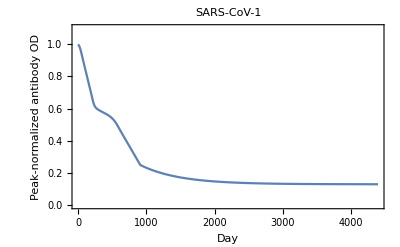

```mathematica
ListLinePlot[sarscov1antibodytimecourseplusexp,
PlotRange->{0, 1.1},
PlotLabel->"SARS-CoV-1",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["SARS-CoV-1_nOD-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov1antibodytimecourseplusexp, PlotRange->{0, 1.1}, PlotLabel->"SARS-CoV-1", Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Peak-normalized antibody OD"}]
]
```

SARS-CoV-1_nOD-by-Day_21Jan2021.pdf

### SARS-CoV-1 Probability of Infection | Antibody OD

```mathematica
sarscov1probinfgivenaod[aod_]:=1/(1+Exp[-(-5.024982+-12.70282*aod)])
```

These values for a and b come from the ancestral and descendent states analysis to determine them for the zoonotic coronaviruses given baselines and declines for all viruses, and a’s and b’s for the “seasonal” coronaviruses.

```mathematica
sarscov1probinfgivenaod[aod]
```

1/(1+ⅇ^(5.02498+12.7028 aod))

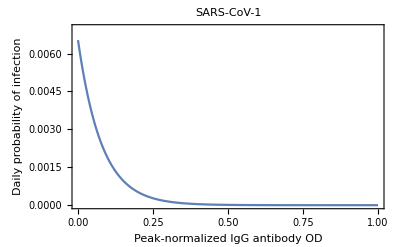

```mathematica
Plot[sarscov1probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.007},
PlotLabel->"SARS-CoV-1",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["SARS-CoV-1_PrInf-by-nOD_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Plot[sarscov1probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.008},
PlotLabel->"SARS-CoV-1",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
]
```

SARS-CoV-1_PrInf-by-nOD_21Jan2021.pdf

```mathematica
sarscov1probinfgivenall[a_, b_, aod_]:=1/(1+Exp[-(a+b*aod)])
```

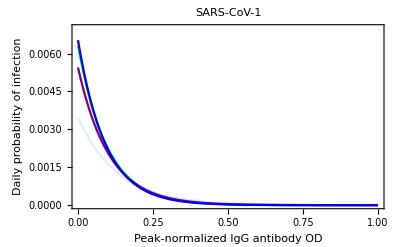

```mathematica
Plot[
{arscov1probinfgivenall[-5.581518, -7.711708, x],
sarscov1probinfgivenall[-5.060224, -10.38432, x], 
sarscov1probinfgivenall[-5.662774,-7.580834, x],
sarscov1probinfgivenall[-5.206379,-9.739482, x],
sarscov1probinfgivenall[-5.024982, -10.91119, x]},
{x,0,1},
PlotStyle->{Red, Green, LightBlue, Purple, Blue},
 PlotRange->{0,0.007},
PlotLabel->"SARS-CoV-1",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
```

The alternate values for a and b above come from our results using different approaches toward building the molecular evolutionary tree of the coronaviruses and toward building the time tree of the coronaviruses (see Supplement).

-Graphics-

This panel goes into a supplementary figure.

```mathematica
Export[
StringJoin["SARS-CoV-1_PrInfs-by-nOD_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Plot[
{sarscov1probinfgivenall[-5.581518, -7.711708, x],
sarscov1probinfgivenall[-5.060224, -10.38432, x], 
sarscov1probinfgivenall[-5.662774,-7.580834, x],
sarscov1probinfgivenall[-5.206379,-9.739482, x],
sarscov1probinfgivenall[-5.024982, -10.91119, x]},
{x,0,1},
PlotStyle->{Red, Green, LightBlue, Purple, Blue},
 PlotRange->{0,0.008},
PlotLabel->"SARS-CoV-1",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
]
```

SARS-CoV-1_PrInfs-by-nOD_21Jan2021.pdf

### SARS-CoV-1 Probability of No Reinfection Time Course

```mathematica
sarscov1probnoreinfectiontimecourse={1};
day=1;
AppendTo[sarscov1probnoreinfectiontimecourse, 
sarscov1probnoreinfectiontimecourse[[day]]*(1-sarscov1probinfgivenaod[sarscov1antibodytimecourseplusexp[[day+1]]])
];

While[day<4393,
Increment[day];
AppendTo[sarscov1probnoreinfectiontimecourse, 
If[day<Length[sarscov1antibodytimecourse],
sarscov1probnoreinfectiontimecourse[[day]]*(1-sarscov1probinfgivenaod[sarscov1antibodytimecourseplusexp[[day+1]] ]),
sarscov1probnoreinfectiontimecourse[[day]]*(1-sarscov1probinfgivenaod[sarscov1antibodytimecourseplusexp[[lengthabtc]]])
]
]
];

sarscov1probnoreinfectiontimecourse
```

{1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999996,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999995,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999994,0.999993,0.999993,0.999993,0.999993,0.999993,0.999993,0.999992,0.999992,0.999992,0.999992,0.999992,0.999992,0.999991,0.999991,0.999991,0.999991,0.99999,0.99999,0.99999,0.99999,0.99999,0.999989,0.999989,0.999989,0.999988,0.999988,0.999988,0.999988,0.999987,0.999987,0.999987,0.999986,0.999986,0.999986,0.999986,0.999985,0.999985,0.999984,0.999984,0.999984,0.999983,0.999983,0.999983,0.999982,0.999982,0.999981,0.999981,0.99998,0.99998,0.99998,0.999979,0.999979,0.999978,0.999978,0.999977,0.999977,0.999976,0.999976,0.999975,0.999974,0.999974,0.999973,0.999973,0.999972,0.999971,0.999971,0.99997,0.999969,0.999969,0.999968,0.999967,0.999966,0.999966,0.999965,0.999964,0.999963,0.999962,0.999962,0.999961,0.99996,0.999959,0.999958,0.999957,0.999956,0.999955,0.999954,0.999953,0.999952,0.999951,0.99995,0.999949,0.999947,0.999946,0.999945,0.999944,0.999942,0.999941,0.99994,0.999938,0.999937,0.999936,0.999934,0.999933,0.999931,0.99993,0.999928,0.999926,0.999925,0.999923,0.999921,0.999919,0.999917,0.999916,0.999914,0.999912,0.99991,0.999908,0.999906,0.999904,0.999901,0.999899,0.999897,0.999895,0.999893,0.99989,0.999888,0.999886,0.999883,0.999881,0.999878,0.999876,0.999873,0.999871,0.999868,0.999866,0.999863,0.99986,0.999858,0.999855,0.999852,0.99985,0.999847,0.999844,0.999841,0.999838,0.999835,0.999833,0.99983,0.999827,0.999824,0.999821,0.999818,0.999815,0.999812,0.999809,0.999806,0.999803,0.9998,0.999797,0.999793,0.99979,0.999787,0.999784,0.999781,0.999778,0.999774,0.999771,0.999768,0.999765,0.999762,0.999758,0.999755,0.999752,0.999748,0.999745,0.999742,0.999738,0.999735,0.999732,0.999728,0.999725,0.999721,0.999718,0.999715,0.999711,0.999708,0.999704,0.999701,0.999697,0.999694,0.99969,0.999687,0.999683,0.99968,0.999676,0.999672,0.999669,0.999665,0.999662,0.999658,0.999654,0.999651,0.999647,0.999643,0.99964,0.999636,0.999632,0.999628,0.999625,0.999621,0.999617,0.999613,0.99961,0.999606,0.999602,0.999598,0.999594,0.999591,0.999587,0.999583,0.999579,0.999575,0.999571,0.999567,0.999563,0.999559,0.999555,0.999551,0.999547,0.999544,0.99954,0.999536,0.999532,0.999527,0.999523,0.999519,0.999515,0.999511,0.999507,0.999503,0.999499,0.999495,0.999491,0.999487,0.999482,0.999478,0.999474,0.99947,0.999466,0.999461,0.999457,0.999453,0.999449,0.999445,0.99944,0.999436,0.999432,0.999427,0.999423,0.999419,0.999414,0.99941,0.999406,0.999401,0.999397,0.999392,0.999388,0.999384,0.999379,0.999375,0.99937,0.999366,0.999361,0.999357,0.999352,0.999348,0.999343,0.999339,0.999334,0.999329,0.999325,0.99932,0.999316,0.999311,0.999306,0.999302,0.999297,0.999292,0.999288,0.999283,0.999278,0.999273,0.999269,0.999264,0.999259,0.999254,0.999249,0.999245,0.99924,0.999235,0.99923,0.999225,0.99922,0.999215,0.99921,0.999205,0.9992,0.999196,0.999191,0.999186,0.99918,0.999175,0.99917,0.999165,0.99916,0.999155,0.99915,0.999145,0.99914,0.999135,0.999129,0.999124,0.999119,0.999114,0.999108,0.999103,0.999098,0.999093,0.999087,0.999082,0.999076,0.999071,0.999066,0.99906,0.999055,0.999049,0.999044,0.999038,0.999033,0.999027,0.999022,0.999016,0.999011,0.999005,0.998999,0.998994,0.998988,0.998982,0.998977,0.998971,0.998965,0.998959,0.998953,0.998948,0.998942,0.998936,0.99893,0.998924,0.998918,0.998912,0.998906,0.9989,0.998894,0.998888,0.998882,0.998876,0.998869,0.998863,0.998857,0.998851,0.998844,0.998838,0.998832,0.998825,0.998819,0.998813,0.998806,0.9988,0.998793,0.998787,0.99878,0.998774,0.998767,0.99876,0.998754,0.998747,0.99874,0.998733,0.998726,0.99872,0.998713,0.998706,0.998699,0.998692,0.998685,0.998678,0.99867,0.998663,0.998656,0.998649,0.998642,0.998634,0.998627,0.998619,0.998612,0.998604,0.998597,0.998589,0.998582,0.998574,0.998566,0.998559,0.998551,0.998543,0.998535,0.998527,0.998519,0.998511,0.998503,0.998495,0.998486,0.998478,0.99847,0.998461,0.998453,0.998444,0.998436,0.998427,0.998418,0.99841,0.998401,0.998392,0.998383,0.998374,0.998365,0.998356,0.998347,0.998337,0.998328,0.998318,0.998309,0.998299,0.99829,0.99828,0.99827,0.99826,0.99825,0.99824,0.99823,0.99822,0.99821,0.998199,0.998189,0.998178,0.998167,0.998157,0.998146,0.998135,0.998124,0.998112,0.998101,0.99809,0.998078,0.998067,0.998055,0.998043,0.998031,0.998019,0.998007,0.997995,0.997982,0.99797,0.997957,0.997945,0.997932,0.997919,0.997906,0.997892,0.997879,0.997866,0.997852,0.997838,0.997824,0.99781,0.997796,0.997782,0.997768,0.997753,0.997738,0.997723,0.997708,0.997693,0.997678,0.997663,0.997647,0.997631,0.997616,0.997599,0.997583,0.997567,0.99755,0.997534,0.997517,0.9975,0.997483,0.997466,0.997448,0.997431,0.997413,0.997395,0.997377,0.997358,0.99734,0.997321,0.997302,0.997283,0.997264,0.997245,0.997225,0.997205,0.997185,0.997165,0.997145,0.997125,0.997104,0.997083,0.997062,0.997041,0.997019,0.996997,0.996976,0.996953,0.996931,0.996909,0.996886,0.996863,0.99684,0.996817,0.996793,0.996769,0.996745,0.996721,0.996697,0.996672,0.996647,0.996622,0.996596,0.996571,0.996545,0.996519,0.996492,0.996466,0.996439,0.996412,0.996385,0.996357,0.996329,0.996301,0.996273,0.996244,0.996215,0.996186,0.996157,0.996127,0.996097,0.996067,0.996036,0.996005,0.995974,0.995943,0.995911,0.995879,0.995847,0.995814,0.995781,0.995748,0.995715,0.995681,0.995647,0.995612,0.995577,0.995542,0.995507,0.995471,0.995435,0.995399,0.995362,0.995325,0.995287,0.995249,0.995211,0.995173,0.995134,0.995095,0.995055,0.995015,0.994975,0.994934,0.994893,0.994852,0.99481,0.994768,0.994725,0.994682,0.994639,0.994595,0.99455,0.994506,0.994461,0.994415,0.994369,0.994323,0.994276,0.994229,0.994181,0.994133,0.994085,0.994036,0.993987,0.993937,0.993886,0.993835,0.993784,0.993732,0.99368,0.993627,0.993574,0.993521,0.993466,0.993412,0.993356,0.993301,0.993244,0.993188,0.99313,0.993073,0.993014,0.992955,0.992896,0.992836,0.992775,0.992714,0.992652,0.99259,0.992527,0.992464,0.9924,0.992335,0.99227,0.992204,0.992138,0.992071,0.992003,0.991935,0.991866,0.991797,0.991726,0.991655,0.991584,0.991512,0.991439,0.991365,0.991291,0.991216,0.991141,0.991065,0.990988,0.99091,0.990832,0.990752,0.990673,0.990592,0.990511,0.990429,0.990346,0.990262,0.990178,0.990093,0.990007,0.98992,0.989832,0.989744,0.989655,0.989565,0.989474,0.989382,0.98929,0.989196,0.989102,0.989007,0.988911,0.988814,0.988716,0.988618,0.988518,0.988417,0.988316,0.988214,0.98811,0.988006,0.987901,0.987795,0.987687,0.987579,0.98747,0.98736,0.987249,0.987136,0.987023,0.986909,0.986793,0.986677,0.98656,0.986441,0.986321,0.986201,0.986079,0.985956,0.985832,0.985706,0.98558,0.985452,0.985323,0.985194,0.985062,0.98493,0.984796,0.984662,0.984526,0.984388,0.98425,0.98411,0.983969,0.983826,0.983683,0.983538,0.983391,0.983244,0.983094,0.982944,0.982792,0.982639,0.982484,0.982328,0.982171,0.982012,0.981852,0.98169,0.981526,0.981362,0.981195,0.981027,0.980858,0.980687,0.980514,0.98034,0.980165,0.979987,0.979808,0.979628,0.979446,0.979262,0.979076,0.978889,0.9787,0.978509,0.978317,0.978123,0.977927,0.977729,0.977529,0.977328,0.977125,0.97692,0.976713,0.976504,0.976293,0.976081,0.975866,0.975649,0.975431,0.97521,0.974988,0.974763,0.974537,0.974308,0.974077,0.973845,0.97361,0.973373,0.973133,0.972892,0.972648,0.972402,0.972154,0.971904,0.971652,0.971397,0.97114,0.97088,0.970618,0.970354,0.970087,0.969452,0.968818,0.968184,0.96755,0.966916,0.966283,0.965651,0.965019,0.964387,0.963756,0.963125,0.962494,0.961864,0.961235,0.960605,0.959977,0.959348,0.95872,0.958093,0.957465,0.956839,0.956212,0.955586,0.954961,0.954336,0.953711,0.953087,0.952463,0.951839,0.951216,0.950593,0.949971,0.949349,0.948728,0.948107,0.947486,0.946866,0.946246,0.945627,0.945008,0.944389,0.943771,0.943153,0.942536,0.941919,0.941302,0.940686,0.94007,0.939455,0.93884,0.938225,0.937611,0.936997,0.936384,0.935771,0.935158,0.934546,0.933934,0.933323,0.932712,0.932102,0.931491,0.930882,0.930272,0.929663,0.929055,0.928447,0.927839,0.927231,0.926624,0.926018,0.925412,0.924806,0.9242,0.923595,0.922991,0.922387,0.921783,0.921179,0.920576,0.919974,0.919372,0.91877,0.918168,0.917567,0.916967,0.916366,0.915767,0.915167,0.914568,0.913969,0.913371,0.912773,0.912176,0.911578,0.910982,0.910385,0.909789,0.909194,0.908599,0.908004,0.90741,0.906816,0.906222,0.905629,0.905036,0.904443,0.903851,0.90326,0.902668,0.902077,0.901487,0.900897,0.900307,0.899718,0.899129,0.89854,0.897952,0.897364,0.896777,0.89619,0.895603,0.895017,0.894431,0.893845,0.89326,0.892676,0.892091,0.891507,0.890924,0.89034,0.889758,0.889175,0.888593,0.888011,0.88743,0.886849,0.886269,0.885688,0.885109,0.884529,0.88395,0.883372,0.882793,0.882215,0.881638,0.881061,0.880484,0.879908,0.879332,0.878756,0.878181,0.877606,0.877032,0.876457,0.875884,0.87531,0.874737,0.874165,0.873592,0.873021,0.872449,0.871878,0.871307,0.870737,0.870167,0.869597,0.869028,0.868459,0.867891,0.867322,0.866755,0.866187,0.86562,0.865054,0.864487,0.863922,0.863356,0.862791,0.862226,0.861662,0.861098,0.860534,0.859971,0.859408,0.858845,0.858283,0.857721,0.857159,0.856598,0.856038,0.855477,0.854917,0.854358,0.853798,0.853239,0.852681,0.852123,0.851565,0.851007,0.85045,0.849894,0.849337,0.848781,0.848226,0.84767,0.847116,0.846561,0.846007,0.845453,0.8449,0.844347,0.843794,0.843241,0.842689,0.842138,0.841587,0.841036,0.840485,0.839935,0.839385,0.838836,0.838287,0.837738,0.837189,0.836641,0.836094,0.835546,0.834999,0.834453,0.833907,0.833361,0.832815,0.83227,0.831725,0.831181,0.830637,0.830093,0.829549,0.829006,0.828464,0.827921,0.827379,0.826838,0.826297,0.825756,0.825215,0.824675,0.824135,0.823596,0.823056,0.822518,0.821979,0.821441,0.820903,0.820366,0.819829,0.819292,0.818756,0.81822,0.817684,0.817149,0.816614,0.81608,0.815546,0.815012,0.814478,0.813945,0.813412,0.81288,0.812348,0.811816,0.811284,0.810753,0.810223,0.809692,0.809162,0.808632,0.808103,0.807574,0.807045,0.806517,0.805989,0.805462,0.804934,0.804407,0.803881,0.803355,0.802829,0.802303,0.801778,0.801253,0.800729,0.800204,0.799681,0.799157,0.798634,0.798111,0.797589,0.797067,0.796545,0.796023,0.795502,0.794982,0.794461,0.793941,0.793421,0.792902,0.792383,0.791864,0.791346,0.790828,0.79031,0.789793,0.789276,0.788759,0.788243,0.787727,0.787211,0.786696,0.786181,0.785666,0.785152,0.784638,0.784124,0.783611,0.783098,0.782586,0.782073,0.781561,0.78105,0.780538,0.780027,0.779517,0.779007,0.778497,0.777987,0.777478,0.776969,0.77646,0.775952,0.775444,0.774936,0.774429,0.773922,0.773415,0.772909,0.772403,0.771898,0.771392,0.770887,0.770383,0.769878,0.769374,0.768871,0.768367,0.767864,0.767362,0.766859,0.766358,0.765856,0.765354,0.764853,0.764353,0.763852,0.763352,0.762853,0.762353,0.761854,0.761356,0.760857,0.760359,0.759861,0.759364,0.758867,0.75837,0.757874,0.757378,0.756882,0.756386,0.755891,0.755396,0.754902,0.754408,0.753914,0.75342,0.752927,0.752434,0.751942,0.751449,0.750958,0.750466,0.749975,0.749484,0.748993,0.748503,0.748013,0.747523,0.747034,0.746545,0.746056,0.745568,0.74508,0.744592,0.744105,0.743617,0.743131,0.742644,0.742158,0.741672,0.741187,0.740702,0.740217,0.739732,0.739248,0.738764,0.73828,0.737797,0.737314,0.736831,0.736349,0.735867,0.735385,0.734904,0.734423,0.733942,0.733462,0.732982,0.732502,0.732022,0.731543,0.731064,0.730586,0.730107,0.729629,0.729152,0.728675,0.728198,0.727721,0.727244,0.726768,0.726293,0.725817,0.725342,0.724867,0.724393,0.723919,0.723445,0.722971,0.722498,0.722025,0.721552,0.72108,0.720608,0.720136,0.719665,0.719194,0.718723,0.718252,0.717782,0.717312,0.716843,0.716374,0.715905,0.715436,0.714968,0.7145,0.714032,0.713564,0.713097,0.712631,0.712164,0.711698,0.711232,0.710766,0.710301,0.709836,0.709371,0.708907,0.708443,0.707979,0.707516,0.707053,0.70659,0.706127,0.705665,0.705203,0.704741,0.70428,0.703819,0.703358,0.702898,0.702438,0.701978,0.701519,0.701059,0.7006,0.700142,0.699683,0.699225,0.698768,0.69831,0.697853,0.697396,0.69694,0.696484,0.696028,0.695572,0.695117,0.694662,0.694207,0.693752,0.693298,0.692844,0.692391,0.691938,0.691485,0.691032,0.69058,0.690128,0.689676,0.689224,0.688773,0.688322,0.687872,0.687422,0.686972,0.686522,0.686072,0.685623,0.685174,0.684726,0.684278,0.68383,0.683382,0.682935,0.682488,0.682041,0.681595,0.681148,0.680702,0.680257,0.679812,0.679367,0.678922,0.678477,0.678033,0.677589,0.677146,0.676703,0.67626,0.675817,0.675375,0.674932,0.674491,0.674049,0.673608,0.673167,0.672726,0.672286,0.671846,0.671406,0.670966,0.670527,0.670088,0.66965,0.669211,0.668773,0.668335,0.667898,0.667461,0.667024,0.666587,0.666151,0.665715,0.665279,0.664843,0.664408,0.663973,0.663539,0.663104,0.66267,0.662236,0.661803,0.66137,0.660937,0.660504,0.660072,0.65964,0.659208,0.658776,0.658345,0.657914,0.657483,0.657053,0.656623,0.656193,0.655763,0.655334,0.654905,0.654477,0.654048,0.65362,0.653192,0.652764,0.652337,0.65191,0.651483,0.651057,0.650631,0.650205,0.649779,0.649354,0.648929,0.648504,0.648079,0.647655,0.647231,0.646808,0.646384,0.645961,0.645538,0.645116,0.644693,0.644271,0.64385,0.643428,0.643007,0.642586,0.642165,0.641745,0.641325,0.640905,0.640485,0.640066,0.639647,0.639229,0.63881,0.638392,0.637974,0.637556,0.637139,0.636722,0.636305,0.635889,0.635472,0.635056,0.634641,0.634225,0.63381,0.633395,0.63298,0.632566,0.632152,0.631738,0.631325,0.630911,0.630498,0.630086,0.629673,0.629261,0.628849,0.628437,0.628026,0.627615,0.627204,0.626794,0.626383,0.625973,0.625563,0.625154,0.624745,0.624336,0.623927,0.623519,0.62311,0.622703,0.622295,0.621888,0.62148,0.621074,0.620667,0.620261,0.619855,0.619449,0.619043,0.618638,0.618233,0.617829,0.617424,0.61702,0.616616,0.616212,0.615809,0.615406,0.615003,0.6146,0.614198,0.613796,0.613394,0.612993,0.612591,0.61219,0.61179,0.611389,0.610989,0.610589,0.610189,0.60979,0.609391,0.608992,0.608593,0.608195,0.607797,0.607399,0.607001,0.606604,0.606207,0.60581,0.605413,0.605017,0.604621,0.604225,0.60383,0.603434,0.603039,0.602645,0.60225,0.601856,0.601462,0.601068,0.600675,0.600281,0.599889,0.599496,0.599103,0.598711,0.598319,0.597928,0.597536,0.597145,0.596754,0.596364,0.595973,0.595583,0.595193,0.594804,0.594414,0.594025,0.593636,0.593248,0.592859,0.592471,0.592083,0.591696,0.591308,0.590921,0.590534,0.590148,0.589762,0.589376,0.58899,0.588604,0.588219,0.587834,0.587449,0.587064,0.58668,0.586296,0.585912,0.585529,0.585145,0.584762,0.58438,0.583997,0.583615,0.583233,0.582851,0.582469,0.582088,0.581707,0.581326,0.580946,0.580565,0.580185,0.579806,0.579426,0.579047,0.578668,0.578289,0.57791,0.577532,0.577154,0.576776,0.576399,0.576021,0.575644,0.575267,0.574891,0.574515,0.574138,0.573763,0.573387,0.573012,0.572637,0.572262,0.571887,0.571513,0.571139,0.570765,0.570391,0.570018,0.569645,0.569272,0.568899,0.568527,0.568154,0.567783,0.567411,0.567039,0.566668,0.566297,0.565927,0.565556,0.565186,0.564816,0.564446,0.564077,0.563707,0.563338,0.56297,0.562601,0.562233,0.561865,0.561497,0.561129,0.560762,0.560395,0.560028,0.559662,0.559295,0.558929,0.558563,0.558198,0.557832,0.557467,0.557102,0.556737,0.556373,0.556009,0.555645,0.555281,0.554918,0.554554,0.554191,0.553829,0.553466,0.553104,0.552742,0.55238,0.552018,0.551657,0.551296,0.550935,0.550574,0.550214,0.549854,0.549494,0.549134,0.548774,0.548415,0.548056,0.547697,0.547339,0.546981,0.546623,0.546265,0.545907,0.54555,0.545193,0.544836,0.544479,0.544123,0.543767,0.543411,0.543055,0.542699,0.542344,0.541989,0.541634,0.54128,0.540925,0.540571,0.540217,0.539864,0.53951,0.539157,0.538804,0.538452,0.538099,0.537747,0.537395,0.537043,0.536692,0.53634,0.535989,0.535638,0.535288,0.534937,0.534587,0.534237,0.533887,0.533538,0.533189,0.53284,0.532491,0.532142,0.531794,0.531446,0.531098,0.53075,0.530403,0.530056,0.529709,0.529362,0.529015,0.528669,0.528323,0.527977,0.527631,0.527286,0.526941,0.526596,0.526251,0.525907,0.525562,0.525218,0.524875,0.524531,0.524188,0.523845,0.523502,0.523159,0.522816,0.522474,0.522132,0.52179,0.521449,0.521107,0.520766,0.520425,0.520085,0.519744,0.519404,0.519064,0.518724,0.518385,0.518045,0.517706,0.517367,0.517029,0.51669,0.516352,0.516014,0.515676,0.515339,0.515001,0.514664,0.514327,0.513991,0.513654,0.513318,0.512982,0.512646,0.51231,0.511975,0.51164,0.511305,0.51097,0.510636,0.510302,0.509968,0.509634,0.5093,0.508967,0.508634,0.508301,0.507968,0.507635,0.507303,0.506971,0.506639,0.506307,0.505976,0.505645,0.505314,0.504983,0.504652,0.504322,0.503992,0.503662,0.503332,0.503003,0.502674,0.502344,0.502016,0.501687,0.501359,0.50103,0.500702,0.500375,0.500047,0.49972,0.499393,0.499066,0.498739,0.498413,0.498086,0.49776,0.497434,0.497109,0.496783,0.496458,0.496133,0.495808,0.495484,0.495159,0.494835,0.494511,0.494188,0.493864,0.493541,0.493218,0.492895,0.492572,0.49225,0.491928,0.491606,0.491284,0.490962,0.490641,0.49032,0.489999,0.489678,0.489357,0.489037,0.488717,0.488397,0.488077,0.487758,0.487438,0.487119,0.486801,0.486482,0.486163,0.485845,0.485527,0.485209,0.484892,0.484574,0.484257,0.48394,0.483623,0.483307,0.48299,0.482674,0.482358,0.482042,0.481727,0.481411,0.481096,0.480781,0.480467,0.480152,0.479838,0.479524,0.47921,0.478896,0.478583,0.478269,0.477956,0.477643,0.477331,0.477018,0.476706,0.476394,0.476082,0.47577,0.475459,0.475148,0.474837,0.474526,0.474215,0.473905,0.473595,0.473285,0.472975,0.472665,0.472356,0.472047,0.471738,0.471429,0.47112,0.470812,0.470504,0.470196,0.469888,0.46958,0.469273,0.468966,0.468659,0.468352,0.468045,0.467739,0.467433,0.467127,0.466821,0.466515,0.46621,0.465905,0.4656,0.465295,0.46499,0.464686,0.464382,0.464078,0.463774,0.46347,0.463167,0.462864,0.462561,0.462258,0.461955,0.461653,0.461351,0.461049,0.460747,0.460445,0.460144,0.459843,0.459542,0.459241,0.45894,0.45864,0.45834,0.45804,0.45774,0.45744,0.457141,0.456841,0.456542,0.456243,0.455945,0.455646,0.455348,0.45505,0.454752,0.454454,0.454157,0.45386,0.453563,0.453266,0.452969,0.452672,0.452376,0.45208,0.451784,0.451488,0.451193,0.450897,0.450602,0.450307,0.450012,0.449718,0.449423,0.449129,0.448835,0.448541,0.448248,0.447954,0.447661,0.447368,0.447075,0.446783,0.44649,0.446198,0.445906,0.445614,0.445322,0.445031,0.444739,0.444448,0.444157,0.443867,0.443576,0.443286,0.442995,0.442705,0.442416,0.442126,0.441837,0.441547,0.441258,0.440969,0.440681,0.440392,0.440104,0.439816,0.439528,0.43924,0.438953,0.438665,0.438378,0.438091,0.437805,0.437518,0.437232,0.436945,0.436659,0.436373,0.436088,0.435802,0.435517,0.435232,0.434947,0.434662,0.434378,0.434093,0.433809,0.433525,0.433242,0.432958,0.432675,0.432391,0.432108,0.431825,0.431543,0.43126,0.430978,0.430696,0.430414,0.430132,0.42985,0.429569,0.429288,0.429007,0.428726,0.428445,0.428165,0.427885,0.427605,0.427325,0.427045,0.426765,0.426486,0.426207,0.425928,0.425649,0.42537,0.425092,0.424814,0.424536,0.424258,0.42398,0.423702,0.423425,0.423148,0.422871,0.422594,0.422317,0.422041,0.421765,0.421489,0.421213,0.420937,0.420661,0.420386,0.420111,0.419836,0.419561,0.419286,0.419012,0.418738,0.418463,0.41819,0.417916,0.417642,0.417369,0.417096,0.416823,0.41655,0.416277,0.416005,0.415732,0.41546,0.415188,0.414916,0.414645,0.414373,0.414102,0.413831,0.41356,0.413289,0.413019,0.412748,0.412478,0.412208,0.411938,0.411669,0.411399,0.41113,0.410861,0.410592,0.410323,0.410054,0.409786,0.409518,0.40925,0.408982,0.408714,0.408447,0.408179,0.407912,0.407645,0.407378,0.407111,0.406845,0.406579,0.406312,0.406046,0.405781,0.405515,0.40525,0.404984,0.404719,0.404454,0.404189,0.403925,0.40366,0.403396,0.403132,0.402868,0.402605,0.402341,0.402078,0.401814,0.401551,0.401289,0.401026,0.400763,0.400501,0.400239,0.399977,0.399715,0.399453,0.399192,0.398931,0.398669,0.398408,0.398148,0.397887,0.397627,0.397366,0.397106,0.396846,0.396586,0.396327,0.396067,0.395808,0.395549,0.39529,0.395031,0.394773,0.394514,0.394256,0.393998,0.39374,0.393482,0.393225,0.392967,0.39271,0.392453,0.392196,0.391939,0.391683,0.391426,0.39117,0.390914,0.390658,0.390402,0.390147,0.389891,0.389636,0.389381,0.389126,0.388872,0.388617,0.388363,0.388108,0.387854,0.3876,0.387347,0.387093,0.38684,0.386587,0.386333,0.386081,0.385828,0.385575,0.385323,0.385071,0.384819,0.384567,0.384315,0.384063,0.383812,0.383561,0.38331,0.383059,0.382808,0.382557,0.382307,0.382057,0.381807,0.381557,0.381307,0.381057,0.380808,0.380558,0.380309,0.38006,0.379812,0.379563,0.379315,0.379066,0.378818,0.37857,0.378322,0.378075,0.377827,0.37758,0.377333,0.377086,0.376839,0.376592,0.376346,0.376099,0.375853,0.375607,0.375361,0.375115,0.37487,0.374624,0.374379,0.374134,0.373889,0.373644,0.3734,0.373155,0.372911,0.372667,0.372423,0.372179,0.371936,0.371692,0.371449,0.371206,0.370963,0.37072,0.370477,0.370235,0.369992,0.36975,0.369508,0.369266,0.369024,0.368783,0.368542,0.3683,0.368059,0.367818,0.367577,0.367337,0.367096,0.366856,0.366616,0.366376,0.366136,0.365896,0.365657,0.365418,0.365178,0.364939,0.3647,0.364462,0.364223,0.363985,0.363746,0.363508,0.36327,0.363033,0.362795,0.362557,0.36232,0.362083,0.361846,0.361609,0.361372,0.361136,0.360899,0.360663,0.360427,0.360191,0.359955,0.35972,0.359484,0.359249,0.359014,0.358779,0.358544,0.358309,0.358074,0.35784,0.357606,0.357372,0.357138,0.356904,0.35667,0.356437,0.356204,0.35597,0.355737,0.355505,0.355272,0.355039,0.354807,0.354575,0.354342,0.35411,0.353879,0.353647,0.353416,0.353184,0.352953,0.352722,0.352491,0.35226,0.35203,0.351799,0.351569,0.351339,0.351109,0.350879,0.350649,0.35042,0.35019,0.349961,0.349732,0.349503,0.349274,0.349046,0.348817,0.348589,0.348361,0.348133,0.347905,0.347677,0.347449,0.347222,0.346995,0.346768,0.346541,0.346314,0.346087,0.34586,0.345634,0.345408,0.345182,0.344956,0.34473,0.344504,0.344279,0.344053,0.343828,0.343603,0.343378,0.343153,0.342929,0.342704,0.34248,0.342256,0.342032,0.341808,0.341584,0.34136,0.341137,0.340914,0.34069,0.340467,0.340245,0.340022,0.339799,0.339577,0.339355,0.339132,0.33891,0.338689,0.338467,0.338245,0.338024,0.337803,0.337581,0.33736,0.33714,0.336919,0.336698,0.336478,0.336258,0.336038,0.335818,0.335598,0.335378,0.335159,0.334939,0.33472,0.334501,0.334282,0.334063,0.333844,0.333626,0.333407,0.333189,0.332971,0.332753,0.332535,0.332318,0.3321,0.331883,0.331665,0.331448,0.331231,0.331014,0.330798,0.330581,0.330365,0.330149,0.329932,0.329716,0.329501,0.329285,0.329069,0.328854,0.328639,0.328424,0.328209,0.327994,0.327779,0.327564,0.32735,0.327136,0.326922,0.326708,0.326494,0.32628,0.326066,0.325853,0.32564,0.325426,0.325213,0.325001,0.324788,0.324575,0.324363,0.32415,0.323938,0.323726,0.323514,0.323302,0.323091,0.322879,0.322668,0.322457,0.322246,0.322035,0.321824,0.321613,0.321403,0.321192,0.320982,0.320772,0.320562,0.320352,0.320142,0.319933,0.319723,0.319514,0.319305,0.319096,0.318887,0.318678,0.31847,0.318261,0.318053,0.317845,0.317637,0.317429,0.317221,0.317013,0.316806,0.316598,0.316391,0.316184,0.315977,0.31577,0.315563,0.315357,0.31515,0.314944,0.314738,0.314532,0.314326,0.31412,0.313915,0.313709,0.313504,0.313299,0.313093,0.312888,0.312684,0.312479,0.312274,0.31207,0.311866,0.311662,0.311458,0.311254,0.31105,0.310846,0.310643,0.310439,0.310236,0.310033,0.30983,0.309627,0.309425,0.309222,0.30902,0.308817,0.308615,0.308413,0.308211,0.30801,0.307808,0.307607,0.307405,0.307204,0.307003,0.306802,0.306601,0.3064,0.3062,0.305999,0.305799,0.305599,0.305399,0.305199,0.304999,0.304799,0.3046,0.3044,0.304201,0.304002,0.303803,0.303604,0.303405,0.303207,0.303008,0.30281,0.302612,0.302414,0.302216,0.302018,0.30182,0.301623,0.301425,0.301228,0.301031,0.300834,0.300637,0.30044,0.300243,0.300047,0.29985,0.299654,0.299458,0.299262,0.299066,0.29887,0.298674,0.298479,0.298284,0.298088,0.297893,0.297698,0.297503,0.297309,0.297114,0.296919,0.296725,0.296531,0.296337,0.296143,0.295949,0.295755,0.295562,0.295368,0.295175,0.294981,0.294788,0.294595,0.294403,0.29421,0.294017,0.293825,0.293632,0.29344,0.293248,0.293056,0.292864,0.292673,0.292481,0.29229,0.292098,0.291907,0.291716,0.291525,0.291334,0.291143,0.290953,0.290762,0.290572,0.290382,0.290192,0.290002,0.289812,0.289622,0.289433,0.289243,0.289054,0.288865,0.288676,0.288487,0.288298,0.288109,0.28792,0.287732,0.287544,0.287355,0.287167,0.286979,0.286791,0.286604,0.286416,0.286229,0.286041,0.285854,0.285667,0.28548,0.285293,0.285106,0.28492,0.284733,0.284547,0.28436,0.284174,0.283988,0.283802,0.283617,0.283431,0.283245,0.28306,0.282875,0.282689,0.282504,0.282319,0.282135,0.28195,0.281765,0.281581,0.281397,0.281212,0.281028,0.280844,0.280661,0.280477,0.280293,0.28011,0.279926,0.279743,0.27956,0.279377,0.279194,0.279011,0.278829,0.278646,0.278464,0.278281,0.278099,0.277917,0.277735,0.277554,0.277372,0.27719,0.277009,0.276827,0.276646,0.276465,0.276284,0.276103,0.275923,0.275742,0.275561,0.275381,0.275201,0.275021,0.274841,0.274661,0.274481,0.274301,0.274122,0.273942,0.273763,0.273584,0.273405,0.273226,0.273047,0.272868,0.272689,0.272511,0.272333,0.272154,0.271976,0.271798,0.27162,0.271442,0.271265,0.271087,0.27091,0.270732,0.270555,0.270378,0.270201,0.270024,0.269847,0.269671,0.269494,0.269318,0.269141,0.268965,0.268789,0.268613,0.268437,0.268262,0.268086,0.267911,0.267735,0.26756,0.267385,0.26721,0.267035,0.26686,0.266685,0.266511,0.266336,0.266162,0.265988,0.265814,0.26564,0.265466,0.265292,0.265118,0.264945,0.264771,0.264598,0.264425,0.264252,0.264079,0.263906,0.263733,0.26356,0.263388,0.263215,0.263043,0.262871,0.262699,0.262527,0.262355,0.262183,0.262012,0.26184,0.261669,0.261497,0.261326,0.261155,0.260984,0.260813,0.260643,0.260472,0.260302,0.260131,0.259961,0.259791,0.259621,0.259451,0.259281,0.259111,0.258942,0.258772,0.258603,0.258433,0.258264,0.258095,0.257926,0.257757,0.257589,0.25742,0.257251,0.257083,0.256915,0.256747,0.256578,0.256411,0.256243,0.256075,0.255907,0.25574,0.255572,0.255405,0.255238,0.255071,0.254904,0.254737,0.25457,0.254404,0.254237,0.254071,0.253904,0.253738,0.253572,0.253406,0.25324,0.253074,0.252909,0.252743,0.252578,0.252412,0.252247,0.252082,0.251917,0.251752,0.251587,0.251423,0.251258,0.251093,0.250929,0.250765,0.250601,0.250437,0.250273,0.250109,0.249945,0.249782,0.249618,0.249455,0.249291,0.249128,0.248965,0.248802,0.248639,0.248476,0.248314,0.248151,0.247989,0.247826,0.247664,0.247502,0.24734,0.247178,0.247016,0.246855,0.246693,0.246532,0.24637,0.246209,0.246048,0.245887,0.245726,0.245565,0.245404,0.245244,0.245083,0.244923,0.244762,0.244602,0.244442,0.244282,0.244122,0.243962,0.243802,0.243643,0.243483,0.243324,0.243165,0.243005,0.242846,0.242687,0.242529,0.24237,0.242211,0.242053,0.241894,0.241736,0.241578,0.241419,0.241261,0.241103,0.240946,0.240788,0.24063,0.240473,0.240315,0.240158,0.240001,0.239844,0.239687,0.23953,0.239373,0.239216,0.23906,0.238903,0.238747,0.238591,0.238434,0.238278,0.238122,0.237966,0.237811,0.237655,0.237499,0.237344,0.237189,0.237033,0.236878,0.236723,0.236568,0.236413,0.236259,0.236104,0.235949,0.235795,0.23564,0.235486,0.235332,0.235178,0.235024,0.23487,0.234716,0.234563,0.234409,0.234256,0.234102,0.233949,0.233796,0.233643,0.23349,0.233337,0.233185,0.233032,0.232879,0.232727,0.232575,0.232422,0.23227,0.232118,0.231966,0.231814,0.231663,0.231511,0.231359,0.231208,0.231057,0.230905,0.230754,0.230603,0.230452,0.230301,0.230151,0.23,0.229849,0.229699,0.229548,0.229398,0.229248,0.229098,0.228948,0.228798,0.228648,0.228499,0.228349,0.2282,0.22805,0.227901,0.227752,0.227603,0.227454,0.227305,0.227156,0.227007,0.226859,0.22671,0.226562,0.226413,0.226265,0.226117,0.225969,0.225821,0.225673,0.225526,0.225378,0.22523,0.225083,0.224936,0.224788,0.224641,0.224494,0.224347,0.2242,0.224054,0.223907,0.22376,0.223614,0.223468,0.223321,0.223175,0.223029,0.222883,0.222737,0.222591,0.222446,0.2223,0.222154,0.222009,0.221864,0.221718,0.221573,0.221428,0.221283,0.221138,0.220994,0.220849,0.220704,0.22056,0.220416,0.220271,0.220127,0.219983,0.219839,0.219695,0.219551,0.219408,0.219264,0.21912,0.218977,0.218834,0.21869,0.218547,0.218404,0.218261,0.218118,0.217976,0.217833,0.21769,0.217548,0.217405,0.217263,0.217121,0.216979,0.216837,0.216695,0.216553,0.216411,0.216269,0.216128,0.215986,0.215845,0.215704,0.215563,0.215421,0.21528,0.215139,0.214999,0.214858,0.214717,0.214577,0.214436,0.214296,0.214156,0.214015,0.213875,0.213735,0.213595,0.213456,0.213316,0.213176,0.213037,0.212897,0.212758,0.212619,0.212479,0.21234,0.212201,0.212062,0.211924,0.211785,0.211646,0.211508,0.211369,0.211231,0.211093,0.210954,0.210816,0.210678,0.21054,0.210402,0.210265,0.210127,0.20999,0.209852,0.209715,0.209577,0.20944,0.209303,0.209166,0.209029,0.208892,0.208756,0.208619,0.208482,0.208346,0.20821,0.208073,0.207937,0.207801,0.207665,0.207529,0.207393,0.207257,0.207122,0.206986,0.206851,0.206715,0.20658,0.206445,0.20631,0.206174,0.20604,0.205905,0.20577,0.205635,0.205501,0.205366,0.205232,0.205097,0.204963,0.204829,0.204695,0.204561,0.204427,0.204293,0.204159,0.204026,0.203892,0.203759,0.203625,0.203492,0.203359,0.203226,0.203093,0.20296,0.202827,0.202694,0.202561,0.202429,0.202296,0.202164,0.202031,0.201899,0.201767,0.201635,0.201503,0.201371,0.201239,0.201107,0.200976,0.200844,0.200713,0.200581,0.20045,0.200319,0.200188,0.200057,0.199926,0.199795,0.199664,0.199533,0.199403,0.199272,0.199142,0.199011,0.198881,0.198751,0.198621,0.198491,0.198361,0.198231,0.198101,0.197972,0.197842,0.197712,0.197583,0.197454,0.197324,0.197195,0.197066,0.196937,0.196808,0.196679,0.196551,0.196422,0.196293,0.196165,0.196037,0.195908,0.19578,0.195652,0.195524,0.195396,0.195268,0.19514,0.195012,0.194885,0.194757,0.19463,0.194502,0.194375,0.194248,0.19412,0.193993,0.193866,0.193739,0.193613,0.193486,0.193359,0.193233,0.193106,0.19298,0.192853,0.192727,0.192601,0.192475,0.192349,0.192223,0.192097,0.191971,0.191846,0.19172,0.191595,0.191469,0.191344,0.191219,0.191094,0.190968,0.190843,0.190718,0.190594,0.190469,0.190344,0.19022,0.190095,0.189971,0.189846,0.189722,0.189598,0.189474,0.18935,0.189226,0.189102,0.188978,0.188854,0.188731,0.188607,0.188484,0.18836,0.188237,0.188114,0.187991,0.187868,0.187745,0.187622,0.187499,0.187376,0.187254,0.187131,0.187008,0.186886,0.186764,0.186641,0.186519,0.186397,0.186275,0.186153,0.186031,0.18591,0.185788,0.185666,0.185545,0.185423,0.185302,0.185181,0.185059,0.184938,0.184817,0.184696,0.184575,0.184454,0.184334,0.184213,0.184092,0.183972,0.183851,0.183731,0.183611,0.183491,0.183371,0.183251,0.183131,0.183011,0.182891,0.182771,0.182651,0.182532,0.182412,0.182293,0.182174,0.182054,0.181935,0.181816,0.181697,0.181578,0.181459,0.181341,0.181222,0.181103,0.180985,0.180866,0.180748,0.180629,0.180511,0.180393,0.180275,0.180157,0.180039,0.179921,0.179803,0.179686,0.179568,0.179451,0.179333,0.179216,0.179098,0.178981,0.178864,0.178747,0.17863,0.178513,0.178396,0.178279,0.178163,0.178046,0.177929,0.177813,0.177697,0.17758,0.177464,0.177348,0.177232,0.177116,0.177,0.176884,0.176768,0.176652,0.176537,0.176421,0.176306,0.17619,0.176075,0.17596,0.175844,0.175729,0.175614,0.175499,0.175385,0.17527,0.175155,0.17504,0.174926,0.174811,0.174697,0.174582,0.174468,0.174354,0.17424,0.174126,0.174012,0.173898,0.173784,0.17367,0.173557,0.173443,0.173329,0.173216,0.173103,0.172989,0.172876,0.172763,0.17265,0.172537,0.172424,0.172311,0.172198,0.172085,0.171973,0.17186,0.171748,0.171635,0.171523,0.171411,0.171298,0.171186,0.171074,0.170962,0.17085,0.170738,0.170627,0.170515,0.170403,0.170292,0.17018,0.170069,0.169958,0.169846,0.169735,0.169624,0.169513,0.169402,0.169291,0.16918,0.16907,0.168959,0.168848,0.168738,0.168627,0.168517,0.168407,0.168296,0.168186,0.168076,0.167966,0.167856,0.167746,0.167636,0.167527,0.167417,0.167307,0.167198,0.167089,0.166979,0.16687,0.166761,0.166651,0.166542,0.166433,0.166324,0.166215,0.166107,0.165998,0.165889,0.165781,0.165672,0.165564,0.165455,0.165347,0.165239,0.165131,0.165023,0.164914,0.164807,0.164699,0.164591,0.164483,0.164375,0.164268,0.16416,0.164053,0.163945,0.163838,0.163731,0.163624,0.163517,0.16341,0.163303,0.163196,0.163089,0.162982,0.162875,0.162769,0.162662,0.162556,0.162449,0.162343,0.162237,0.162131,0.162024,0.161918,0.161812,0.161706,0.161601,0.161495,0.161389,0.161283,0.161178,0.161072,0.160967,0.160861,0.160756,0.160651,0.160546,0.160441,0.160336,0.160231,0.160126,0.160021,0.159916,0.159812,0.159707,0.159602,0.159498,0.159394,0.159289,0.159185,0.159081,0.158977,0.158873,0.158769,0.158665,0.158561,0.158457,0.158353,0.15825,0.158146,0.158042,0.157939,0.157836,0.157732,0.157629,0.157526,0.157423,0.15732,0.157217,0.157114,0.157011,0.156908,0.156805,0.156703,0.1566,0.156498,0.156395,0.156293,0.156191,0.156088,0.155986,0.155884,0.155782,0.15568,0.155578,0.155476,0.155374,0.155273,0.155171,0.15507,0.154968,0.154867,0.154765,0.154664,0.154563,0.154461,0.15436,0.154259,0.154158,0.154057,0.153957,0.153856,0.153755,0.153654,0.153554,0.153453,0.153353,0.153252,0.153152,0.153052,0.152952,0.152852,0.152752,0.152652,0.152552,0.152452,0.152352,0.152252,0.152153,0.152053,0.151953,0.151854,0.151755,0.151655,0.151556,0.151457,0.151358,0.151258,0.151159,0.151061,0.150962,0.150863,0.150764,0.150665,0.150567,0.150468,0.15037,0.150271,0.150173,0.150075,0.149976,0.149878,0.14978,0.149682,0.149584,0.149486,0.149388,0.14929,0.149193,0.149095,0.148997,0.1489,0.148802,0.148705,0.148608,0.14851,0.148413,0.148316,0.148219,0.148122,0.148025,0.147928,0.147831,0.147734,0.147638,0.147541,0.147445,0.147348,0.147252,0.147155,0.147059,0.146963,0.146866,0.14677,0.146674,0.146578,0.146482,0.146386,0.14629,0.146195,0.146099,0.146003,0.145908,0.145812,0.145717,0.145621,0.145526,0.145431,0.145336,0.14524,0.145145,0.14505,0.144955,0.144861,0.144766,0.144671,0.144576,0.144482,0.144387,0.144293,0.144198,0.144104,0.144009,0.143915,0.143821,0.143727,0.143633,0.143539,0.143445,0.143351,0.143257,0.143163,0.143069,0.142976,0.142882,0.142789,0.142695,0.142602,0.142508,0.142415,0.142322,0.142229,0.142136,0.142043,0.14195,0.141857,0.141764,0.141671,0.141578,0.141486,0.141393,0.1413,0.141208,0.141115,0.141023,0.140931,0.140839,0.140746,0.140654,0.140562,0.14047,0.140378,0.140286,0.140194,0.140103,0.140011,0.139919,0.139828,0.139736,0.139645,0.139553,0.139462,0.139371,0.139279,0.139188,0.139097,0.139006,0.138915,0.138824,0.138733,0.138642,0.138552,0.138461,0.13837,0.13828,0.138189,0.138099,0.138008,0.137918,0.137828,0.137738,0.137647,0.137557,0.137467,0.137377,0.137287,0.137197,0.137108,0.137018,0.136928,0.136839,0.136749,0.136659,0.13657,0.136481,0.136391,0.136302,0.136213,0.136124,0.136034,0.135945,0.135856,0.135767,0.135679,0.13559,0.135501,0.135412,0.135324,0.135235,0.135147,0.135058,0.13497,0.134881,0.134793,0.134705,0.134617,0.134529,0.13444,0.134352,0.134265,0.134177,0.134089,0.134001,0.133913,0.133826,0.133738,0.13365,0.133563,0.133476,0.133388,0.133301,0.133214,0.133126,0.133039,0.132952,0.132865,0.132778,0.132691,0.132604,0.132518,0.132431,0.132344,0.132257,0.132171,0.132084,0.131998,0.131912,0.131825,0.131739,0.131653,0.131566,0.13148,0.131394,0.131308,0.131222,0.131136,0.131051,0.130965,0.130879,0.130793,0.130708,0.130622,0.130537,0.130451,0.130366,0.13028,0.130195,0.13011,0.130025,0.12994,0.129855,0.12977,0.129685,0.1296,0.129515,0.12943,0.129345,0.129261,0.129176,0.129092,0.129007,0.128923,0.128838,0.128754,0.12867,0.128585,0.128501,0.128417,0.128333,0.128249,0.128165,0.128081,0.127997,0.127914,0.12783,0.127746,0.127663,0.127579,0.127495,0.127412,0.127329,0.127245,0.127162,0.127079,0.126995,0.126912,0.126829,0.126746,0.126663,0.12658,0.126498,0.126415,0.126332,0.126249,0.126167,0.126084,0.126001,0.125919,0.125837,0.125754,0.125672,0.12559,0.125507,0.125425,0.125343,0.125261,0.125179,0.125097,0.125015,0.124933,0.124852,0.12477,0.124688,0.124607,0.124525,0.124444,0.124362,0.124281,0.124199,0.124118,0.124037,0.123956,0.123874,0.123793,0.123712,0.123631,0.12355,0.123469,0.123389,0.123308,0.123227,0.123147,0.123066,0.122985,0.122905,0.122824,0.122744,0.122664,0.122583,0.122503,0.122423,0.122343,0.122263,0.122183,0.122103,0.122023,0.121943,0.121863,0.121783,0.121704,0.121624,0.121544,0.121465,0.121385,0.121306,0.121226,0.121147,0.121068,0.120988,0.120909,0.12083,0.120751,0.120672,0.120593,0.120514,0.120435,0.120356,0.120277,0.120199,0.12012,0.120041,0.119963,0.119884,0.119806,0.119727,0.119649,0.119571,0.119492,0.119414,0.119336,0.119258,0.11918,0.119102,0.119024,0.118946,0.118868,0.11879,0.118712,0.118635,0.118557,0.11848,0.118402,0.118324,0.118247,0.11817,0.118092,0.118015,0.117938,0.11786,0.117783,0.117706,0.117629,0.117552,0.117475,0.117398,0.117321,0.117245,0.117168,0.117091,0.117015,0.116938,0.116861,0.116785,0.116708,0.116632,0.116556,0.116479,0.116403,0.116327,0.116251,0.116175,0.116099,0.116023,0.115947,0.115871,0.115795,0.115719,0.115643,0.115568,0.115492,0.115416,0.115341,0.115265,0.11519,0.115115,0.115039,0.114964,0.114889,0.114813,0.114738,0.114663,0.114588,0.114513,0.114438,0.114363,0.114288,0.114214,0.114139,0.114064,0.113989,0.113915,0.11384,0.113766,0.113691,0.113617,0.113542,0.113468,0.113394,0.11332,0.113245,0.113171,0.113097,0.113023,0.112949,0.112875,0.112801,0.112727,0.112654,0.11258,0.112506,0.112433,0.112359,0.112285,0.112212,0.112138,0.112065,0.111992,0.111918,0.111845,0.111772,0.111699,0.111626,0.111553,0.11148,0.111407,0.111334,0.111261,0.111188,0.111115,0.111042,0.11097,0.110897,0.110824,0.110752,0.110679,0.110607,0.110535,0.110462,0.11039,0.110318,0.110245,0.110173,0.110101,0.110029,0.109957,0.109885,0.109813,0.109741,0.109669,0.109598,0.109526,0.109454,0.109383,0.109311,0.109239,0.109168,0.109096,0.109025,0.108954,0.108882,0.108811,0.10874,0.108669,0.108597,0.108526,0.108455,0.108384,0.108313,0.108242,0.108172,0.108101,0.10803,0.107959,0.107889,0.107818,0.107747,0.107677,0.107606,0.107536,0.107466,0.107395,0.107325,0.107255,0.107184,0.107114,0.107044,0.106974,0.106904,0.106834,0.106764,0.106694,0.106624,0.106555,0.106485,0.106415,0.106346,0.106276,0.106206,0.106137,0.106067,0.105998,0.105929,0.105859,0.10579,0.105721,0.105651,0.105582,0.105513,0.105444,0.105375,0.105306,0.105237,0.105168,0.105099,0.105031,0.104962,0.104893,0.104825,0.104756,0.104687,0.104619,0.10455,0.104482,0.104413,0.104345,0.104277,0.104209,0.10414,0.104072,0.104004,0.103936,0.103868,0.1038,0.103732,0.103664,0.103596,0.103528,0.103461,0.103393,0.103325,0.103258,0.10319,0.103122,0.103055,0.102987,0.10292,0.102853,0.102785,0.102718,0.102651,0.102584,0.102516,0.102449,0.102382,0.102315,0.102248,0.102181,0.102114,0.102048,0.101981,0.101914,0.101847,0.101781,0.101714,0.101647,0.101581,0.101514,0.101448,0.101382,0.101315,0.101249,0.101183,0.101116,0.10105,0.100984,0.100918,0.100852,0.100786,0.10072,0.100654,0.100588,0.100522,0.100456,0.100391,0.100325,0.100259,0.100194,0.100128,0.100062,0.099997,0.0999315,0.0998661,0.0998007,0.0997354,0.0996701,0.0996049,0.0995397,0.0994745,0.0994094,0.0993443,0.0992793,0.0992143}

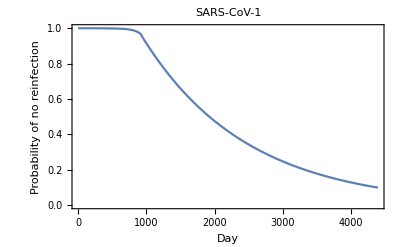

```mathematica
ListLinePlot[sarscov1probnoreinfectiontimecourse,
PlotRange->{0,1},
PlotLabel->"SARS-CoV-1",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability of no reinfection"}]
```

```mathematica
sarscov1continuousprobnoreinfection=Interpolation[sarscov1probnoreinfectiontimecourse]
```

InterpolatingFunction[…]

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov1continuousprobnoreinfection[x]-0.95],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{943.954,31.4651,2.58617}

These are the 5% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.FindMinimum[{Abs[sarscov1continuousprobnoreinfection[x]-0.50],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{1924.14,64.1381,5.27163}

These are the 50% quantiles (medians) for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.FindMinimum[{Abs[sarscov1continuousprobnoreinfection[x]-0.05],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{4390.,146.333,12.0274}

These are the 95% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
sarscov1probreinfectiondensity={};
day=0;
While[day<4393,
Increment[day];
AppendTo[sarscov1probreinfectiondensity, 
If[day<lengthabtc,
sarscov1probinfgivenaod[sarscov1antibodytimecourseplusexp[[day]]]*sarscov1probnoreinfectiontimecourse[[day]],
sarscov1probinfgivenaod[sarscov1antibodytimecourseplusexp[[lengthabtc]]]*sarscov1probnoreinfectiontimecourse[[day]]
]
]
];
```

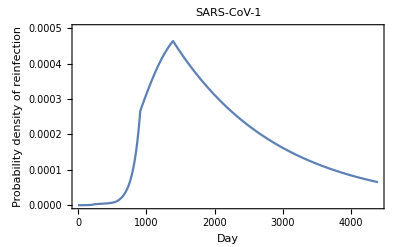

```mathematica
ListLinePlot[sarscov1probreinfectiondensity,
PlotRange->{0,0.0005},
 PlotLabel->"SARS-CoV-1",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability density of reinfection"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["SARS-CoV-1_PrInf-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov1probreinfectiondensity,
PlotRange->{0,0.0006},
PlotLabel->"SARS-CoV-1",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability density of reinfection"}]
]
```

SARS-CoV-1_PrInf-by-Day_21Jan2021.pdf

## SARS-CoV-2

Input Data: Average peak-normalized ELIZA ODs for SARS-CoV-2 S IgG antibodies from Gudbjartsson et al. 20XX, “”, Italics.

days : 34, 48, 70, 94, 109
OD : 1.6, 1.55, 1.43, 1.19, 1.22

```mathematica
sarscov2data={
{1,34, SARSCoV2,1.6/1.6,  TRUE,NA, NA},
{2,48, SARSCoV2,1.55/1.6, FALSE, (48-34), (1.55/1.6-1.6/1.6)/(48-34)},
{3, 70, SARSCoV2,1.43/1.6,  FALSE,(70-48), (1.43/1.6-1.55/1.6)/(70-48)},
{4, 94, SARSCoV2,1.19/1.6, FALSE,(94-70),  (1.19/1.6-1.43/1.6)/(94-70)}
}
```

{{1,34,SARSCoV2,1.,TRUE,NA,NA},{2,48,SARSCoV2,0.96875,FALSE,14,-0.00223214},{3,70,SARSCoV2,0.89375,FALSE,22,-0.00340909},{4,94,SARSCoV2,0.74375,FALSE,24,-0.00625}}

### SARS-CoV-2 Waning of Antibody OD

```mathematica
sarscov2datalength=Length[sarscov2data]
```

4

```mathematica
Table[
{aod,
Table[
If [
Or[
sarscov2data[[index-1, 4]]≥aod≥sarscov2data[[index, 4]],
sarscov2data[[index-1, 4]]≤aod≤sarscov2data[[index, 4]]],
sarscov2data[[index, 7]],
Nothing],
{index, 2, sarscov2datalength}
]
}
, {aod, 0,1.6, 0.05}]
```

{{0.,{}},{0.05,{}},{0.1,{}},{0.15,{}},{0.2,{}},{0.25,{}},{0.3,{}},{0.35,{}},{0.4,{}},{0.45,{}},{0.5,{}},{0.55,{}},{0.6,{}},{0.65,{}},{0.7,{}},{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}},{1.05,{}},{1.1,{}},{1.15,{}},{1.2,{}},{1.25,{}},{1.3,{}},{1.35,{}},{1.4,{}},{1.45,{}},{1.5,{}},{1.55,{}},{1.6,{}}}

```mathematica
sarscov2paddedmeanwaning=Table[
{aod,
Table[
If [
Or[
sarscov2data[[index-1, 4]]≥aod≥sarscov2data[[index, 4]],
sarscov2data[[index-1, 4]]≤aod≤sarscov2data[[index, 4]]],
sarscov2data[[index, 7]],
Nothing],
{index, 2, sarscov2datalength}
]
}
, {aod, 0.75,1, 0.05}]
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}}}

```mathematica
sarscov2meanwaning={{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.0034090909090909124}},{0.95,{-0.0034090909090909124}},{1.,{-0.002232142857142857}},{1.7/1.6,{ -0.00833333} } }
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}},{1.0625,{-0.00833333}}}

```mathematica
TableForm[sarscov2meanwaning]
```

0.75 | -0.00625
0.8 | -0.00625
0.85 | -0.00625
0.9 | -0.00340909
0.95 | -0.00340909
1. | -0.00223214
1.0625 | -0.00833333

```mathematica
sarscov2antibodywaning=Interpolation[sarscov2meanwaning]
```

InterpolatingFunction[…]

```mathematica
sarscov2antibodytimecourse={1.0};
day=1;
While[sarscov2antibodytimecourse[[day]]≥0.75,
sarscov2antibodytimecourse=Append[sarscov2antibodytimecourse, sarscov2antibodytimecourse[[day]]+sarscov2antibodywaning[sarscov2antibodytimecourse[[day]]]];
sarscov2antibodytimecourse=Flatten[sarscov2antibodytimecourse];
Increment[day];
];
sarscov2antibodytimecourse
```

{1.,0.997768,0.995542,0.993314,0.991075,0.988816,0.986529,0.984208,0.981845,0.979431,0.976961,0.974426,0.97182,0.969137,0.966369,0.963511,0.960556,0.957501,0.954342,0.951075,0.947701,0.944297,0.940904,0.937525,0.934162,0.930817,0.927487,0.924173,0.920871,0.917576,0.914284,0.91099,0.907684,0.904359,0.901005,0.897611,0.894085,0.890378,0.886467,0.882332,0.877951,0.873303,0.868369,0.863133,0.857586,0.851725,0.845558,0.839235,0.832842,0.826415,0.819985,0.813576,0.807207,0.80089,0.794631,0.788432,0.782285,0.776182,0.770106,0.764038,0.757953,0.751819,0.745602}

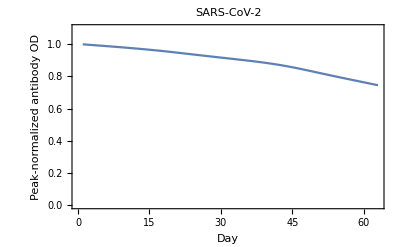

```mathematica
ListLinePlot[sarscov2antibodytimecourse, PlotRange->{0,1.1}, PlotLabel->"SARS-CoV-2", Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Peak-normalized antibody OD"}]
```

```mathematica
Export["SARS-CoV-2-Antibody-Time-Course.csv", sarscov2antibodytimecourse]
```

SARS-CoV-2-Antibody-Time-Course.csv

```mathematica
sarscov2baseline=0.1298892
```

0.129889

This baseline peak-normalized S IgG antibody level for SARS-CoV-1 comes from the ancestral and descendent states analysis that used the baselines for the human “seasonal” coronaviruses to estimate the baselines for the zoonotic coronaviruses.

```mathematica
sarscov2lsfuncwfixedbaseline=Sum[(sarscov2antibodytimecourse[[index]]-(sarscov2baseline+(1-sarscov2baseline)*Exp[-lambda*index]))^2, {index, 1, Length[sarscov2antibodytimecourse]}]
```

(0.615713-0.870111 ⅇ^(-63 lambda))^2+(0.62193-0.870111 ⅇ^(-62 lambda))^2+(0.628063-0.870111 ⅇ^(-61 lambda))^2+(0.634149-0.870111 ⅇ^(-60 lambda))^2+(0.640217-0.870111 ⅇ^(-59 lambda))^2+(0.646293-0.870111 ⅇ^(-58 lambda))^2+(0.652396-0.870111 ⅇ^(-57 lambda))^2+(0.658542-0.870111 ⅇ^(-56 lambda))^2+(0.664742-0.870111 ⅇ^(-55 lambda))^2+(0.671001-0.870111 ⅇ^(-54 lambda))^2+(0.677317-0.870111 ⅇ^(-53 lambda))^2+(0.683687-0.870111 ⅇ^(-52 lambda))^2+(0.690096-0.870111 ⅇ^(-51 lambda))^2+(0.696526-0.870111 ⅇ^(-50 lambda))^2+(0.702953-0.870111 ⅇ^(-49 lambda))^2+(0.709345-0.870111 ⅇ^(-48 lambda))^2+(0.715669-0.870111 ⅇ^(-47 lambda))^2+(0.721835-0.870111 ⅇ^(-46 lambda))^2+(0.727697-0.870111 ⅇ^(-45 lambda))^2+(0.733244-0.870111 ⅇ^(-44 lambda))^2+(0.73848-0.870111 ⅇ^(-43 lambda))^2+(0.743414-0.870111 ⅇ^(-42 lambda))^2+(0.748062-0.870111 ⅇ^(-41 lambda))^2+(0.752443-0.870111 ⅇ^(-40 lambda))^2+(0.756578-0.870111 ⅇ^(-39 lambda))^2+(0.760489-0.870111 ⅇ^(-38 lambda))^2+(0.764196-0.870111 ⅇ^(-37 lambda))^2+(0.767721-0.870111 ⅇ^(-36 lambda))^2+(0.771116-0.870111 ⅇ^(-35 lambda))^2+(0.77447-0.870111 ⅇ^(-34 lambda))^2+(0.777795-0.870111 ⅇ^(-33 lambda))^2+(0.7811-0.870111 ⅇ^(-32 lambda))^2+(0.784395-0.870111 ⅇ^(-31 lambda))^2+(0.787687-0.870111 ⅇ^(-30 lambda))^2+(0.790981-0.870111 ⅇ^(-29 lambda))^2+(0.794284-0.870111 ⅇ^(-28 lambda))^2+(0.797598-0.870111 ⅇ^(-27 lambda))^2+(0.800927-0.870111 ⅇ^(-26 lambda))^2+(0.804273-0.870111 ⅇ^(-25 lambda))^2+(0.807636-0.870111 ⅇ^(-24 lambda))^2+(0.811014-0.870111 ⅇ^(-23 lambda))^2+(0.814408-0.870111 ⅇ^(-22 lambda))^2+(0.817812-0.870111 ⅇ^(-21 lambda))^2+(0.821186-0.870111 ⅇ^(-20 lambda))^2+(0.824453-0.870111 ⅇ^(-19 lambda))^2+(0.827612-0.870111 ⅇ^(-18 lambda))^2+(0.830667-0.870111 ⅇ^(-17 lambda))^2+(0.833622-0.870111 ⅇ^(-16 lambda))^2+(0.83648-0.870111 ⅇ^(-15 lambda))^2+(0.839248-0.870111 ⅇ^(-14 lambda))^2+(0.841931-0.870111 ⅇ^(-13 lambda))^2+(0.844537-0.870111 ⅇ^(-12 lambda))^2+(0.847072-0.870111 ⅇ^(-11 lambda))^2+(0.849542-0.870111 ⅇ^(-10 lambda))^2+(0.851955-0.870111 ⅇ^(-9 lambda))^2+(0.854319-0.870111 ⅇ^(-8 lambda))^2+(0.85664-0.870111 ⅇ^(-7 lambda))^2+(0.858927-0.870111 ⅇ^(-6 lambda))^2+(0.861185-0.870111 ⅇ^(-5 lambda))^2+(0.863425-0.870111 ⅇ^(-4 lambda))^2+(0.865653-0.870111 ⅇ^(-3 lambda))^2+(0.867879-0.870111 ⅇ^(-2 lambda))^2+(0.870111-0.870111 ⅇ^-lambda)^2

```mathematica
FindMinimum[{sarscov2lsfuncwfixedbaseline, lambda >0}, {lambda, 0.002}]
```

{0.02921,{lambda→0.00426663}}

This value of lambda goes into the ancestral and descendent states analysis estimating a and b for the zoonotic coronaviruses.

```mathematica
sarscov2halflife=Log[2]/ lambda /.lambda->0.004266634824871021
```

162.458

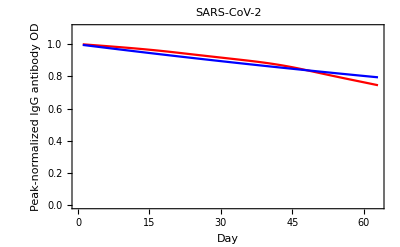

```mathematica
Show[ListLinePlot[sarscov2antibodytimecourse,PlotStyle->Red, PlotRange->{0,1.1}],Plot[sarscov2baseline+(1-sarscov2baseline)*Exp[-lambda days]/.lambda->0.004266634824871021,{days,1,Length[sarscov2antibodytimecourse]}, PlotStyle->Blue, PlotRange->{0, 1.1}],
 PlotLabel->"SARS-CoV-2", Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Peak-normalized IgG antibody OD"}]
```

```mathematica
Length[sarscov2antibodytimecourse]
```

63

```mathematica
sarscov2antibodytimecourseplusexp=sarscov2antibodytimecourse;
day=Length[sarscov2antibodytimecourse];
While[day<4393,
Increment[day];
AppendTo[sarscov2antibodytimecourseplusexp, sarscov1baseline+(sarscov2antibodytimecourseplusexp[[day-1]]- sarscov1baseline)*Exp[-0.004266634824871021]]
]
```

```mathematica
sarscov2antibodytimecourseplusexp
```

{1.,0.997768,0.995542,0.993314,0.991075,0.988816,0.986529,0.984208,0.981845,0.979431,0.976961,0.974426,0.97182,0.969137,0.966369,0.963511,0.960556,0.957501,0.954342,0.951075,0.947701,0.944297,0.940904,0.937525,0.934162,0.930817,0.927487,0.924173,0.920871,0.917576,0.914284,0.91099,0.907684,0.904359,0.901005,0.897611,0.894085,0.890378,0.886467,0.882332,0.877951,0.873303,0.868369,0.863133,0.857586,0.851725,0.845558,0.839235,0.832842,0.826415,0.819985,0.813576,0.807207,0.80089,0.794631,0.788432,0.782285,0.776182,0.770106,0.764038,0.757953,0.751819,0.745602,0.74298,0.74037,0.737771,0.735183,0.732606,0.73004,0.727485,0.72494,0.722407,0.719884,0.717372,0.714871,0.71238,0.7099,0.707431,0.704972,0.702524,0.700086,0.697658,0.695241,0.692834,0.690437,0.68805,0.685674,0.683308,0.680951,0.678605,0.676269,0.673943,0.671627,0.66932,0.667023,0.664737,0.662459,0.660192,0.657934,0.655686,0.653447,0.651218,0.648999,0.646789,0.644588,0.642397,0.640215,0.638042,0.635878,0.633724,0.631579,0.629443,0.627316,0.625198,0.623089,0.62099,0.618899,0.616817,0.614744,0.612679,0.610624,0.608577,0.606539,0.60451,0.602489,0.600477,0.598473,0.596478,0.594492,0.592514,0.590544,0.588583,0.58663,0.584685,0.582749,0.580821,0.578901,0.576989,0.575086,0.57319,0.571303,0.569424,0.567552,0.565689,0.563834,0.561986,0.560146,0.558315,0.55649,0.554674,0.552866,0.551065,0.549272,0.547486,0.545708,0.543938,0.542175,0.54042,0.538672,0.536931,0.535198,0.533473,0.531754,0.530044,0.52834,0.526643,0.524954,0.523272,0.521597,0.51993,0.518269,0.516615,0.514969,0.513329,0.511697,0.510071,0.508453,0.506841,0.505236,0.503638,0.502047,0.500462,0.498885,0.497314,0.495749,0.494192,0.492641,0.491096,0.489558,0.488027,0.486502,0.484984,0.483472,0.481967,0.480468,0.478975,0.477489,0.476009,0.474535,0.473068,0.471607,0.470152,0.468703,0.467261,0.465824,0.464394,0.46297,0.461552,0.46014,0.458734,0.457334,0.45594,0.454551,0.453169,0.451793,0.450422,0.449058,0.447699,0.446346,0.444998,0.443657,0.442321,0.440991,0.439666,0.438347,0.437034,0.435726,0.434424,0.433128,0.431836,0.430551,0.429271,0.427996,0.426727,0.425463,0.424205,0.422952,0.421704,0.420462,0.419224,0.417993,0.416766,0.415545,0.414328,0.413117,0.411912,0.410711,0.409515,0.408325,0.407139,0.405959,0.404783,0.403613,0.402448,0.401287,0.400132,0.398981,0.397835,0.396695,0.395559,0.394428,0.393301,0.39218,0.391063,0.389951,0.388844,0.387741,0.386644,0.385551,0.384462,0.383378,0.382299,0.381224,0.380154,0.379089,0.378028,0.376971,0.375919,0.374872,0.373829,0.37279,0.371756,0.370726,0.369701,0.36868,0.367663,0.366651,0.365643,0.364639,0.36364,0.362644,0.361654,0.360667,0.359684,0.358706,0.357732,0.356762,0.355796,0.354834,0.353876,0.352923,0.351973,0.351027,0.350086,0.349148,0.348215,0.347285,0.34636,0.345438,0.34452,0.343607,0.342697,0.341791,0.340889,0.33999,0.339096,0.338205,0.337318,0.336435,0.335556,0.33468,0.333808,0.33294,0.332075,0.331215,0.330357,0.329504,0.328654,0.327808,0.326965,0.326126,0.325291,0.324459,0.32363,0.322805,0.321984,0.321166,0.320352,0.319541,0.318733,0.317929,0.317129,0.316332,0.315538,0.314747,0.31396,0.313177,0.312396,0.311619,0.310846,0.310075,0.309308,0.308544,0.307784,0.307026,0.306272,0.305521,0.304773,0.304029,0.303287,0.302549,0.301814,0.301082,0.300353,0.299627,0.298905,0.298185,0.297469,0.296755,0.296045,0.295337,0.294633,0.293931,0.293233,0.292538,0.291845,0.291155,0.290469,0.289785,0.289104,0.288427,0.287752,0.28708,0.28641,0.285744,0.28508,0.28442,0.283762,0.283107,0.282454,0.281805,0.281158,0.280514,0.279873,0.279234,0.278598,0.277965,0.277335,0.276707,0.276082,0.275459,0.27484,0.274222,0.273608,0.272996,0.272387,0.27178,0.271176,0.270574,0.269975,0.269379,0.268785,0.268194,0.267605,0.267019,0.266435,0.265853,0.265275,0.264698,0.264124,0.263553,0.262984,0.262417,0.261853,0.261291,0.260731,0.260174,0.25962,0.259067,0.258517,0.25797,0.257424,0.256881,0.256341,0.255802,0.255266,0.254732,0.254201,0.253672,0.253145,0.25262,0.252097,0.251577,0.251059,0.250543,0.250029,0.249518,0.249009,0.248501,0.247996,0.247494,0.246993,0.246494,0.245998,0.245503,0.245011,0.244521,0.244033,0.243547,0.243063,0.242581,0.242102,0.241624,0.241148,0.240674,0.240203,0.239733,0.239265,0.2388,0.238336,0.237874,0.237415,0.236957,0.236501,0.236047,0.235595,0.235145,0.234697,0.234251,0.233806,0.233364,0.232923,0.232485,0.232048,0.231613,0.23118,0.230749,0.230319,0.229892,0.229466,0.229042,0.22862,0.228199,0.227781,0.227364,0.226949,0.226536,0.226124,0.225715,0.225307,0.2249,0.224496,0.224093,0.223692,0.223293,0.222895,0.222499,0.222105,0.221712,0.221321,0.220932,0.220544,0.220158,0.219774,0.219391,0.21901,0.218631,0.218253,0.217877,0.217502,0.217129,0.216758,0.216388,0.21602,0.215653,0.215288,0.214924,0.214562,0.214202,0.213843,0.213485,0.213129,0.212775,0.212422,0.212071,0.211721,0.211372,0.211025,0.21068,0.210336,0.209993,0.209652,0.209313,0.208975,0.208638,0.208303,0.207969,0.207636,0.207305,0.206976,0.206648,0.206321,0.205995,0.205671,0.205349,0.205027,0.204708,0.204389,0.204072,0.203756,0.203441,0.203128,0.202816,0.202506,0.202197,0.201889,0.201582,0.201277,0.200973,0.200671,0.200369,0.200069,0.19977,0.199473,0.199177,0.198882,0.198588,0.198295,0.198004,0.197714,0.197425,0.197138,0.196852,0.196566,0.196283,0.196,0.195718,0.195438,0.195159,0.194881,0.194604,0.194329,0.194055,0.193781,0.193509,0.193239,0.192969,0.1927,0.192433,0.192167,0.191901,0.191637,0.191374,0.191113,0.190852,0.190592,0.190334,0.190077,0.18982,0.189565,0.189311,0.189058,0.188806,0.188555,0.188306,0.188057,0.187809,0.187563,0.187317,0.187073,0.186829,0.186587,0.186345,0.186105,0.185866,0.185627,0.18539,0.185154,0.184918,0.184684,0.184451,0.184219,0.183987,0.183757,0.183528,0.183299,0.183072,0.182845,0.18262,0.182395,0.182172,0.181949,0.181728,0.181507,0.181287,0.181068,0.18085,0.180633,0.180417,0.180202,0.179988,0.179775,0.179562,0.179351,0.17914,0.178931,0.178722,0.178514,0.178307,0.178101,0.177896,0.177691,0.177488,0.177285,0.177083,0.176882,0.176682,0.176483,0.176285,0.176087,0.17589,0.175694,0.175499,0.175305,0.175112,0.174919,0.174728,0.174537,0.174347,0.174157,0.173969,0.173781,0.173594,0.173408,0.173223,0.173039,0.172855,0.172672,0.17249,0.172308,0.172128,0.171948,0.171769,0.171591,0.171413,0.171236,0.17106,0.170885,0.17071,0.170537,0.170364,0.170191,0.17002,0.169849,0.169679,0.169509,0.169341,0.169173,0.169005,0.168839,0.168673,0.168508,0.168343,0.16818,0.168017,0.167854,0.167693,0.167532,0.167371,0.167212,0.167053,0.166895,0.166737,0.16658,0.166424,0.166269,0.166114,0.165959,0.165806,0.165653,0.165501,0.165349,0.165198,0.165048,0.164898,0.164749,0.164601,0.164453,0.164306,0.164159,0.164013,0.163868,0.163723,0.163579,0.163436,0.163293,0.163151,0.163009,0.162868,0.162728,0.162588,0.162449,0.16231,0.162172,0.162035,0.161898,0.161761,0.161626,0.161491,0.161356,0.161222,0.161089,0.160956,0.160824,0.160692,0.160561,0.16043,0.1603,0.160171,0.160042,0.159913,0.159786,0.159658,0.159532,0.159405,0.15928,0.159155,0.15903,0.158906,0.158782,0.158659,0.158537,0.158415,0.158293,0.158172,0.158052,0.157932,0.157813,0.157694,0.157575,0.157458,0.15734,0.157223,0.157107,0.156991,0.156876,0.156761,0.156646,0.156532,0.156419,0.156306,0.156194,0.156082,0.15597,0.155859,0.155749,0.155638,0.155529,0.15542,0.155311,0.155203,0.155095,0.154988,0.154881,0.154774,0.154668,0.154563,0.154458,0.154353,0.154249,0.154145,0.154042,0.153939,0.153837,0.153735,0.153633,0.153532,0.153432,0.153331,0.153232,0.153132,0.153033,0.152935,0.152837,0.152739,0.152642,0.152545,0.152448,0.152352,0.152257,0.152161,0.152067,0.151972,0.151878,0.151784,0.151691,0.151598,0.151506,0.151414,0.151322,0.151231,0.15114,0.15105,0.15096,0.15087,0.150781,0.150692,0.150603,0.150515,0.150427,0.15034,0.150253,0.150166,0.15008,0.149994,0.149908,0.149823,0.149738,0.149653,0.149569,0.149485,0.149402,0.149319,0.149236,0.149154,0.149072,0.14899,0.148909,0.148828,0.148747,0.148667,0.148587,0.148507,0.148428,0.148349,0.148271,0.148192,0.148114,0.148037,0.14796,0.147883,0.147806,0.14773,0.147654,0.147578,0.147503,0.147428,0.147353,0.147279,0.147205,0.147131,0.147058,0.146985,0.146912,0.146839,0.146767,0.146695,0.146624,0.146552,0.146482,0.146411,0.146341,0.146271,0.146201,0.146131,0.146062,0.145993,0.145925,0.145856,0.145788,0.145721,0.145653,0.145586,0.145519,0.145453,0.145387,0.145321,0.145255,0.14519,0.145124,0.14506,0.144995,0.144931,0.144867,0.144803,0.144739,0.144676,0.144613,0.14455,0.144488,0.144426,0.144364,0.144302,0.144241,0.14418,0.144119,0.144058,0.143998,0.143938,0.143878,0.143819,0.143759,0.1437,0.143642,0.143583,0.143525,0.143467,0.143409,0.143351,0.143294,0.143237,0.14318,0.143123,0.143067,0.143011,0.142955,0.1429,0.142844,0.142789,0.142734,0.142679,0.142625,0.142571,0.142517,0.142463,0.142409,0.142356,0.142303,0.14225,0.142198,0.142145,0.142093,0.142041,0.141989,0.141938,0.141886,0.141835,0.141784,0.141734,0.141683,0.141633,0.141583,0.141533,0.141484,0.141434,0.141385,0.141336,0.141288,0.141239,0.141191,0.141143,0.141095,0.141047,0.141,0.140952,0.140905,0.140858,0.140812,0.140765,0.140719,0.140673,0.140627,0.140581,0.140535,0.14049,0.140445,0.1404,0.140355,0.140311,0.140266,0.140222,0.140178,0.140134,0.140091,0.140047,0.140004,0.139961,0.139918,0.139875,0.139833,0.139791,0.139748,0.139706,0.139665,0.139623,0.139582,0.13954,0.139499,0.139458,0.139418,0.139377,0.139337,0.139296,0.139256,0.139216,0.139177,0.139137,0.139098,0.139059,0.13902,0.138981,0.138942,0.138903,0.138865,0.138827,0.138789,0.138751,0.138713,0.138676,0.138638,0.138601,0.138564,0.138527,0.13849,0.138454,0.138417,0.138381,0.138345,0.138309,0.138273,0.138237,0.138202,0.138166,0.138131,0.138096,0.138061,0.138026,0.137991,0.137957,0.137923,0.137888,0.137854,0.13782,0.137787,0.137753,0.13772,0.137686,0.137653,0.13762,0.137587,0.137554,0.137522,0.137489,0.137457,0.137425,0.137393,0.137361,0.137329,0.137297,0.137266,0.137234,0.137203,0.137172,0.137141,0.13711,0.137079,0.137049,0.137018,0.136988,0.136957,0.136927,0.136897,0.136868,0.136838,0.136808,0.136779,0.136749,0.13672,0.136691,0.136662,0.136633,0.136605,0.136576,0.136548,0.136519,0.136491,0.136463,0.136435,0.136407,0.136379,0.136352,0.136324,0.136297,0.136269,0.136242,0.136215,0.136188,0.136162,0.136135,0.136108,0.136082,0.136055,0.136029,0.136003,0.135977,0.135951,0.135925,0.1359,0.135874,0.135848,0.135823,0.135798,0.135773,0.135748,0.135723,0.135698,0.135673,0.135648,0.135624,0.1356,0.135575,0.135551,0.135527,0.135503,0.135479,0.135455,0.135432,0.135408,0.135384,0.135361,0.135338,0.135315,0.135291,0.135268,0.135246,0.135223,0.1352,0.135177,0.135155,0.135132,0.13511,0.135088,0.135066,0.135044,0.135022,0.135,0.134978,0.134957,0.134935,0.134913,0.134892,0.134871,0.13485,0.134828,0.134807,0.134786,0.134766,0.134745,0.134724,0.134704,0.134683,0.134663,0.134642,0.134622,0.134602,0.134582,0.134562,0.134542,0.134522,0.134503,0.134483,0.134463,0.134444,0.134424,0.134405,0.134386,0.134367,0.134348,0.134329,0.13431,0.134291,0.134272,0.134254,0.134235,0.134217,0.134198,0.13418,0.134161,0.134143,0.134125,0.134107,0.134089,0.134071,0.134054,0.134036,0.134018,0.134001,0.133983,0.133966,0.133948,0.133931,0.133914,0.133897,0.13388,0.133863,0.133846,0.133829,0.133812,0.133795,0.133779,0.133762,0.133746,0.133729,0.133713,0.133697,0.13368,0.133664,0.133648,0.133632,0.133616,0.1336,0.133585,0.133569,0.133553,0.133538,0.133522,0.133507,0.133491,0.133476,0.133461,0.133445,0.13343,0.133415,0.1334,0.133385,0.13337,0.133355,0.133341,0.133326,0.133311,0.133297,0.133282,0.133268,0.133253,0.133239,0.133225,0.133211,0.133197,0.133182,0.133168,0.133155,0.133141,0.133127,0.133113,0.133099,0.133086,0.133072,0.133058,0.133045,0.133031,0.133018,0.133005,0.132992,0.132978,0.132965,0.132952,0.132939,0.132926,0.132913,0.1329,0.132887,0.132875,0.132862,0.132849,0.132837,0.132824,0.132812,0.132799,0.132787,0.132774,0.132762,0.13275,0.132738,0.132726,0.132714,0.132702,0.13269,0.132678,0.132666,0.132654,0.132642,0.13263,0.132619,0.132607,0.132596,0.132584,0.132573,0.132561,0.13255,0.132538,0.132527,0.132516,0.132505,0.132494,0.132483,0.132472,0.132461,0.13245,0.132439,0.132428,0.132417,0.132406,0.132396,0.132385,0.132374,0.132364,0.132353,0.132343,0.132332,0.132322,0.132311,0.132301,0.132291,0.132281,0.13227,0.13226,0.13225,0.13224,0.13223,0.13222,0.13221,0.1322,0.132191,0.132181,0.132171,0.132161,0.132152,0.132142,0.132132,0.132123,0.132113,0.132104,0.132094,0.132085,0.132076,0.132066,0.132057,0.132048,0.132039,0.13203,0.13202,0.132011,0.132002,0.131993,0.131984,0.131975,0.131967,0.131958,0.131949,0.13194,0.131931,0.131923,0.131914,0.131905,0.131897,0.131888,0.13188,0.131871,0.131863,0.131854,0.131846,0.131838,0.131829,0.131821,0.131813,0.131805,0.131797,0.131789,0.13178,0.131772,0.131764,0.131756,0.131748,0.131741,0.131733,0.131725,0.131717,0.131709,0.131701,0.131694,0.131686,0.131678,0.131671,0.131663,0.131656,0.131648,0.131641,0.131633,0.131626,0.131618,0.131611,0.131604,0.131596,0.131589,0.131582,0.131575,0.131567,0.13156,0.131553,0.131546,0.131539,0.131532,0.131525,0.131518,0.131511,0.131504,0.131497,0.131491,0.131484,0.131477,0.13147,0.131463,0.131457,0.13145,0.131443,0.131437,0.13143,0.131424,0.131417,0.131411,0.131404,0.131398,0.131391,0.131385,0.131378,0.131372,0.131366,0.13136,0.131353,0.131347,0.131341,0.131335,0.131329,0.131322,0.131316,0.13131,0.131304,0.131298,0.131292,0.131286,0.13128,0.131274,0.131268,0.131263,0.131257,0.131251,0.131245,0.131239,0.131234,0.131228,0.131222,0.131216,0.131211,0.131205,0.1312,0.131194,0.131188,0.131183,0.131177,0.131172,0.131166,0.131161,0.131156,0.13115,0.131145,0.131139,0.131134,0.131129,0.131124,0.131118,0.131113,0.131108,0.131103,0.131098,0.131092,0.131087,0.131082,0.131077,0.131072,0.131067,0.131062,0.131057,0.131052,0.131047,0.131042,0.131037,0.131032,0.131027,0.131023,0.131018,0.131013,0.131008,0.131003,0.130999,0.130994,0.130989,0.130985,0.13098,0.130975,0.130971,0.130966,0.130961,0.130957,0.130952,0.130948,0.130943,0.130939,0.130934,0.13093,0.130925,0.130921,0.130917,0.130912,0.130908,0.130904,0.130899,0.130895,0.130891,0.130886,0.130882,0.130878,0.130874,0.13087,0.130865,0.130861,0.130857,0.130853,0.130849,0.130845,0.130841,0.130837,0.130833,0.130829,0.130825,0.130821,0.130817,0.130813,0.130809,0.130805,0.130801,0.130797,0.130793,0.130789,0.130786,0.130782,0.130778,0.130774,0.13077,0.130767,0.130763,0.130759,0.130755,0.130752,0.130748,0.130744,0.130741,0.130737,0.130734,0.13073,0.130726,0.130723,0.130719,0.130716,0.130712,0.130709,0.130705,0.130702,0.130698,0.130695,0.130691,0.130688,0.130685,0.130681,0.130678,0.130674,0.130671,0.130668,0.130665,0.130661,0.130658,0.130655,0.130651,0.130648,0.130645,0.130642,0.130638,0.130635,0.130632,0.130629,0.130626,0.130623,0.13062,0.130616,0.130613,0.13061,0.130607,0.130604,0.130601,0.130598,0.130595,0.130592,0.130589,0.130586,0.130583,0.13058,0.130577,0.130574,0.130571,0.130568,0.130566,0.130563,0.13056,0.130557,0.130554,0.130551,0.130548,0.130546,0.130543,0.13054,0.130537,0.130535,0.130532,0.130529,0.130526,0.130524,0.130521,0.130518,0.130516,0.130513,0.13051,0.130508,0.130505,0.130502,0.1305,0.130497,0.130495,0.130492,0.130489,0.130487,0.130484,0.130482,0.130479,0.130477,0.130474,0.130472,0.130469,0.130467,0.130464,0.130462,0.130459,0.130457,0.130455,0.130452,0.13045,0.130447,0.130445,0.130443,0.13044,0.130438,0.130436,0.130433,0.130431,0.130429,0.130426,0.130424,0.130422,0.13042,0.130417,0.130415,0.130413,0.130411,0.130408,0.130406,0.130404,0.130402,0.1304,0.130397,0.130395,0.130393,0.130391,0.130389,0.130387,0.130385,0.130382,0.13038,0.130378,0.130376,0.130374,0.130372,0.13037,0.130368,0.130366,0.130364,0.130362,0.13036,0.130358,0.130356,0.130354,0.130352,0.13035,0.130348,0.130346,0.130344,0.130342,0.13034,0.130338,0.130336,0.130334,0.130333,0.130331,0.130329,0.130327,0.130325,0.130323,0.130321,0.130319,0.130318,0.130316,0.130314,0.130312,0.13031,0.130309,0.130307,0.130305,0.130303,0.130302,0.1303,0.130298,0.130296,0.130295,0.130293,0.130291,0.130289,0.130288,0.130286,0.130284,0.130283,0.130281,0.130279,0.130278,0.130276,0.130274,0.130273,0.130271,0.130269,0.130268,0.130266,0.130265,0.130263,0.130261,0.13026,0.130258,0.130257,0.130255,0.130254,0.130252,0.13025,0.130249,0.130247,0.130246,0.130244,0.130243,0.130241,0.13024,0.130238,0.130237,0.130235,0.130234,0.130232,0.130231,0.130229,0.130228,0.130227,0.130225,0.130224,0.130222,0.130221,0.130219,0.130218,0.130217,0.130215,0.130214,0.130213,0.130211,0.13021,0.130208,0.130207,0.130206,0.130204,0.130203,0.130202,0.1302,0.130199,0.130198,0.130196,0.130195,0.130194,0.130192,0.130191,0.13019,0.130189,0.130187,0.130186,0.130185,0.130184,0.130182,0.130181,0.13018,0.130179,0.130177,0.130176,0.130175,0.130174,0.130172,0.130171,0.13017,0.130169,0.130168,0.130166,0.130165,0.130164,0.130163,0.130162,0.130161,0.130159,0.130158,0.130157,0.130156,0.130155,0.130154,0.130153,0.130152,0.13015,0.130149,0.130148,0.130147,0.130146,0.130145,0.130144,0.130143,0.130142,0.130141,0.130139,0.130138,0.130137,0.130136,0.130135,0.130134,0.130133,0.130132,0.130131,0.13013,0.130129,0.130128,0.130127,0.130126,0.130125,0.130124,0.130123,0.130122,0.130121,0.13012,0.130119,0.130118,0.130117,0.130116,0.130115,0.130114,0.130113,0.130112,0.130111,0.13011,0.130109,0.130108,0.130108,0.130107,0.130106,0.130105,0.130104,0.130103,0.130102,0.130101,0.1301,0.130099,0.130098,0.130098,0.130097,0.130096,0.130095,0.130094,0.130093,0.130092,0.130091,0.130091,0.13009,0.130089,0.130088,0.130087,0.130086,0.130085,0.130085,0.130084,0.130083,0.130082,0.130081,0.13008,0.13008,0.130079,0.130078,0.130077,0.130076,0.130076,0.130075,0.130074,0.130073,0.130073,0.130072,0.130071,0.13007,0.130069,0.130069,0.130068,0.130067,0.130066,0.130066,0.130065,0.130064,0.130063,0.130063,0.130062,0.130061,0.13006,0.13006,0.130059,0.130058,0.130058,0.130057,0.130056,0.130055,0.130055,0.130054,0.130053,0.130053,0.130052,0.130051,0.13005,0.13005,0.130049,0.130048,0.130048,0.130047,0.130046,0.130046,0.130045,0.130044,0.130044,0.130043,0.130042,0.130042,0.130041,0.13004,0.13004,0.130039,0.130039,0.130038,0.130037,0.130037,0.130036,0.130035,0.130035,0.130034,0.130034,0.130033,0.130032,0.130032,0.130031,0.13003,0.13003,0.130029,0.130029,0.130028,0.130028,0.130027,0.130026,0.130026,0.130025,0.130025,0.130024,0.130023,0.130023,0.130022,0.130022,0.130021,0.130021,0.13002,0.130019,0.130019,0.130018,0.130018,0.130017,0.130017,0.130016,0.130016,0.130015,0.130015,0.130014,0.130014,0.130013,0.130012,0.130012,0.130011,0.130011,0.13001,0.13001,0.130009,0.130009,0.130008,0.130008,0.130007,0.130007,0.130006,0.130006,0.130005,0.130005,0.130004,0.130004,0.130003,0.130003,0.130002,0.130002,0.130001,0.130001,0.13,0.13,0.13,0.129999,0.129999,0.129998,0.129998,0.129997,0.129997,0.129996,0.129996,0.129995,0.129995,0.129994,0.129994,0.129994,0.129993,0.129993,0.129992,0.129992,0.129991,0.129991,0.12999,0.12999,0.12999,0.129989,0.129989,0.129988,0.129988,0.129988,0.129987,0.129987,0.129986,0.129986,0.129985,0.129985,0.129985,0.129984,0.129984,0.129983,0.129983,0.129983,0.129982,0.129982,0.129981,0.129981,0.129981,0.12998,0.12998,0.129979,0.129979,0.129979,0.129978,0.129978,0.129978,0.129977,0.129977,0.129976,0.129976,0.129976,0.129975,0.129975,0.129975,0.129974,0.129974,0.129974,0.129973,0.129973,0.129972,0.129972,0.129972,0.129971,0.129971,0.129971,0.12997,0.12997,0.12997,0.129969,0.129969,0.129969,0.129968,0.129968,0.129968,0.129967,0.129967,0.129967,0.129966,0.129966,0.129966,0.129965,0.129965,0.129965,0.129964,0.129964,0.129964,0.129963,0.129963,0.129963,0.129962,0.129962,0.129962,0.129962,0.129961,0.129961,0.129961,0.12996,0.12996,0.12996,0.129959,0.129959,0.129959,0.129958,0.129958,0.129958,0.129958,0.129957,0.129957,0.129957,0.129956,0.129956,0.129956,0.129956,0.129955,0.129955,0.129955,0.129954,0.129954,0.129954,0.129954,0.129953,0.129953,0.129953,0.129953,0.129952,0.129952,0.129952,0.129951,0.129951,0.129951,0.129951,0.12995,0.12995,0.12995,0.12995,0.129949,0.129949,0.129949,0.129949,0.129948,0.129948,0.129948,0.129948,0.129947,0.129947,0.129947,0.129947,0.129946,0.129946,0.129946,0.129946,0.129945,0.129945,0.129945,0.129945,0.129944,0.129944,0.129944,0.129944,0.129944,0.129943,0.129943,0.129943,0.129943,0.129942,0.129942,0.129942,0.129942,0.129941,0.129941,0.129941,0.129941,0.129941,0.12994,0.12994,0.12994,0.12994,0.12994,0.129939,0.129939,0.129939,0.129939,0.129938,0.129938,0.129938,0.129938,0.129938,0.129937,0.129937,0.129937,0.129937,0.129937,0.129936,0.129936,0.129936,0.129936,0.129936,0.129935,0.129935,0.129935,0.129935,0.129935,0.129934,0.129934,0.129934,0.129934,0.129934,0.129933,0.129933,0.129933,0.129933,0.129933,0.129933,0.129932,0.129932,0.129932,0.129932,0.129932,0.129931,0.129931,0.129931,0.129931,0.129931,0.129931,0.12993,0.12993,0.12993,0.12993,0.12993,0.12993,0.129929,0.129929,0.129929,0.129929,0.129929,0.129928,0.129928,0.129928,0.129928,0.129928,0.129928,0.129927,0.129927,0.129927,0.129927,0.129927,0.129927,0.129927,0.129926,0.129926,0.129926,0.129926,0.129926,0.129926,0.129925,0.129925,0.129925,0.129925,0.129925,0.129925,0.129925,0.129924,0.129924,0.129924,0.129924,0.129924,0.129924,0.129923,0.129923,0.129923,0.129923,0.129923,0.129923,0.129923,0.129922,0.129922,0.129922,0.129922,0.129922,0.129922,0.129922,0.129921,0.129921,0.129921,0.129921,0.129921,0.129921,0.129921,0.129921,0.12992,0.12992,0.12992,0.12992,0.12992,0.12992,0.12992,0.129919,0.129919,0.129919,0.129919,0.129919,0.129919,0.129919,0.129919,0.129918,0.129918,0.129918,0.129918,0.129918,0.129918,0.129918,0.129918,0.129917,0.129917,0.129917,0.129917,0.129917,0.129917,0.129917,0.129917,0.129917,0.129916,0.129916,0.129916,0.129916,0.129916,0.129916,0.129916,0.129916,0.129916,0.129915,0.129915,0.129915,0.129915,0.129915,0.129915,0.129915,0.129915,0.129915,0.129914,0.129914,0.129914,0.129914,0.129914,0.129914,0.129914,0.129914,0.129914,0.129913,0.129913,0.129913,0.129913,0.129913,0.129913,0.129913,0.129913,0.129913,0.129913,0.129912,0.129912,0.129912,0.129912,0.129912,0.129912,0.129912,0.129912,0.129912,0.129912,0.129911,0.129911,0.129911,0.129911,0.129911,0.129911,0.129911,0.129911,0.129911,0.129911,0.129911,0.12991,0.12991,0.12991,0.12991,0.12991,0.12991,0.12991,0.12991,0.12991,0.12991,0.12991,0.129909,0.129909,0.129909,0.129909,0.129909,0.129909,0.129909,0.129909,0.129909,0.129909,0.129909,0.129909,0.129908,0.129908,0.129908,0.129908,0.129908,0.129908,0.129908,0.129908,0.129908,0.129908,0.129908,0.129908,0.129908,0.129907,0.129907,0.129907,0.129907,0.129907,0.129907,0.129907,0.129907,0.129907,0.129907,0.129907,0.129907,0.129907,0.129906,0.129906,0.129906,0.129906,0.129906,0.129906,0.129906,0.129906,0.129906,0.129906,0.129906,0.129906,0.129906,0.129906,0.129905,0.129905,0.129905,0.129905,0.129905,0.129905,0.129905,0.129905,0.129905,0.129905,0.129905,0.129905,0.129905,0.129905,0.129905,0.129904,0.129904,0.129904,0.129904,0.129904,0.129904,0.129904,0.129904,0.129904,0.129904,0.129904,0.129904,0.129904,0.129904,0.129904,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129903,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129902,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.129901,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.1299,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129899,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129898,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129897,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129896,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129895,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129894,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129893,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129892,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.129891,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.12989,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889,0.129889}

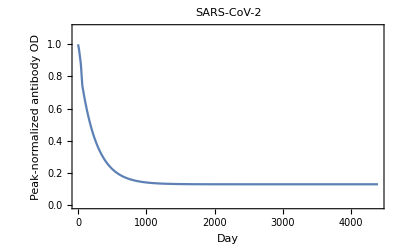

```mathematica
ListLinePlot[sarscov2antibodytimecourseplusexp,
PlotRange->{0, 1.1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["SARS-CoV-2_nOD-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2antibodytimecourseplusexp,
PlotRange->{0, 1.1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
]
```

SARS-CoV-2_nOD-by-Day_21Jan2021.pdf

### SARS-CoV-2 Probability of Infection | Antibody OD

```mathematica
sarscov2probinfgivenaod[aod_]:=1/(1+Exp[-(-4.941497+-11.38309*aod)])
```

These values for a and b come from the ancestral and descendent states analysis to determine them for the zoonotic coronaviruses given baselines and declines for all viruses, and a’s and b’s for the “seasonal” coronaviruses.

```mathematica
sarscov2probinfgivenaod[aod]
```

1/(1+ⅇ^(4.9415+11.3831 aod))

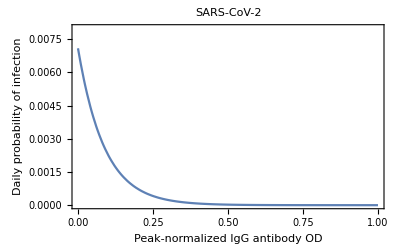

```mathematica
Plot[sarscov2probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.008},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["SARS-CoV-2_PrInf-by-nOD_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Plot[sarscov2probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.008},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
]
```

SARS-CoV-2_PrInf-by-nOD_21Jan2021.pdf

```mathematica
sarscov2probinfgivenall[a_, b_, aod_]:=1/(1+Exp[-(a+b*aod)])
```

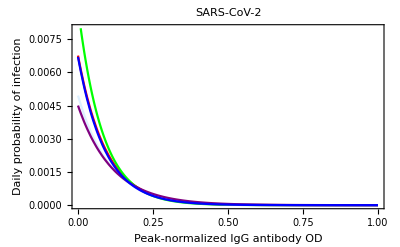

```mathematica
Plot[
{ sarscov1probinfgivenall[-4.989473, -10.80564, x],
sarscov1probinfgivenall[-4.710598, -12.28719, x], 
sarscov1probinfgivenall[-5.302204,-9.463756, x],
sarscov1probinfgivenall[-5.398463,-8.737778, x],
sarscov1probinfgivenall[-4.998047, -11.11046, x]},
{x,0,1},
PlotStyle->{Red, Green, LightBlue, Purple, Blue},
 PlotRange->{0,0.008},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
```

The alternate values for a and b above come from our results using different approaches toward building the molecular evolutionary tree of the coronaviruses and toward building the time tree of the coronaviruses (see Supplement).

-Graphics-

This panel is part of a supplementary figure.

```mathematica
Export[
StringJoin["SARS-CoV-2_PrInfs-by-nOD_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Plot[
{ sarscov2probinfgivenall[-4.978764, -10.8201, x],
sarscov2probinfgivenall[-4.616656, -12.75654, x], 
sarscov2probinfgivenall[-4.743178,-12.366944, x],
sarscov2probinfgivenall[-4.497106,-13.4316, x],
sarscov2probinfgivenall[-4.932034, -11.42871, x]},
{x,0,1},
PlotStyle->{Red, Green, LightBlue, Purple, Blue},
 PlotRange->{0,0.008},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
]
```

SARS-CoV-2_PrInfs-by-nOD_21Jan2021.pdf

### SARS-CoV-2 Probability of No Reinfection Time Course

```mathematica
sarscov2probnoreinfectiontimecourse={1};
day=1;
AppendTo[sarscov2probnoreinfectiontimecourse, 
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseplusexp[[day+1]]])
];

While[day<4393,
Increment[day];
AppendTo[sarscov2probnoreinfectiontimecourse, 
If[day<Length[sarscov2antibodytimecourse],
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseplusexp[[day+1]] ]),
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseplusexp[[lengthabtc]]])
]
]
];

sarscov2probnoreinfectiontimecourse
```

{1,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999998,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999996,0.999996,0.999996,0.999996,0.999996,0.999995,0.999995,0.999995,0.999994,0.999994,0.999994,0.999994,0.999993,0.999993,0.999993,0.999992,0.999992,0.999991,0.999991,0.99999,0.99999,0.999989,0.999989,0.999988,0.999987,0.999986,0.999986,0.999985,0.999984,0.999983,0.999982,0.99998,0.999979,0.999978,0.999976,0.998389,0.996804,0.995222,0.993643,0.992066,0.990491,0.988919,0.987349,0.985782,0.984217,0.982655,0.981096,0.979538,0.977984,0.976431,0.974882,0.973334,0.971789,0.970247,0.968707,0.967169,0.965634,0.964102,0.962572,0.961044,0.959518,0.957995,0.956475,0.954957,0.953441,0.951928,0.950417,0.948908,0.947402,0.945898,0.944397,0.942898,0.941402,0.939907,0.938416,0.936926,0.935439,0.933954,0.932472,0.930992,0.929514,0.928039,0.926566,0.925095,0.923627,0.922161,0.920697,0.919236,0.917777,0.91632,0.914866,0.913414,0.911964,0.910517,0.909071,0.907629,0.906188,0.90475,0.903314,0.90188,0.900448,0.899019,0.897592,0.896168,0.894745,0.893325,0.891907,0.890492,0.889078,0.887667,0.886258,0.884851,0.883447,0.882045,0.880645,0.879247,0.877852,0.876458,0.875067,0.873678,0.872291,0.870907,0.869525,0.868145,0.866767,0.865391,0.864017,0.862646,0.861277,0.85991,0.858545,0.857182,0.855822,0.854463,0.853107,0.851753,0.850401,0.849051,0.847704,0.846358,0.845015,0.843674,0.842335,0.840998,0.839663,0.83833,0.837,0.835671,0.834345,0.83302,0.831698,0.830378,0.82906,0.827744,0.826431,0.825119,0.823809,0.822502,0.821196,0.819893,0.818591,0.817292,0.815995,0.8147,0.813407,0.812116,0.810827,0.80954,0.808255,0.806972,0.805691,0.804412,0.803136,0.801861,0.800588,0.799317,0.798049,0.796782,0.795517,0.794255,0.792994,0.791736,0.790479,0.789224,0.787972,0.786721,0.785472,0.784225,0.782981,0.781738,0.780497,0.779258,0.778022,0.776787,0.775554,0.774323,0.773094,0.771867,0.770642,0.769419,0.768197,0.766978,0.765761,0.764545,0.763332,0.76212,0.760911,0.759703,0.758497,0.757293,0.756091,0.754891,0.753693,0.752497,0.751302,0.75011,0.748919,0.747731,0.746544,0.745359,0.744176,0.742995,0.741815,0.740638,0.739462,0.738289,0.737117,0.735947,0.734779,0.733613,0.732448,0.731286,0.730125,0.728966,0.727809,0.726654,0.725501,0.724349,0.723199,0.722052,0.720905,0.719761,0.718619,0.717478,0.716339,0.715203,0.714067,0.712934,0.711802,0.710673,0.709545,0.708418,0.707294,0.706171,0.705051,0.703932,0.702814,0.701699,0.700585,0.699473,0.698363,0.697254,0.696148,0.695043,0.69394,0.692838,0.691739,0.690641,0.689544,0.68845,0.687357,0.686266,0.685177,0.68409,0.683004,0.68192,0.680837,0.679757,0.678678,0.677601,0.676525,0.675451,0.674379,0.673309,0.67224,0.671173,0.670108,0.669044,0.667982,0.666922,0.665864,0.664807,0.663752,0.662698,0.661646,0.660596,0.659548,0.658501,0.657456,0.656412,0.65537,0.65433,0.653291,0.652255,0.651219,0.650186,0.649154,0.648123,0.647095,0.646068,0.645042,0.644018,0.642996,0.641976,0.640957,0.639939,0.638924,0.637909,0.636897,0.635886,0.634877,0.633869,0.632863,0.631859,0.630856,0.629854,0.628855,0.627857,0.62686,0.625865,0.624872,0.62388,0.62289,0.621901,0.620914,0.619928,0.618944,0.617962,0.616981,0.616002,0.615024,0.614048,0.613073,0.6121,0.611129,0.610159,0.60919,0.608224,0.607258,0.606294,0.605332,0.604371,0.603412,0.602454,0.601498,0.600543,0.59959,0.598638,0.597688,0.59674,0.595793,0.594847,0.593903,0.59296,0.592019,0.591079,0.590141,0.589204,0.588269,0.587336,0.586403,0.585473,0.584543,0.583616,0.582689,0.581764,0.580841,0.579919,0.578999,0.57808,0.577162,0.576246,0.575331,0.574418,0.573507,0.572596,0.571687,0.57078,0.569874,0.56897,0.568067,0.567165,0.566265,0.565366,0.564469,0.563573,0.562678,0.561785,0.560893,0.560003,0.559114,0.558227,0.557341,0.556456,0.555573,0.554691,0.553811,0.552932,0.552054,0.551178,0.550303,0.54943,0.548558,0.547687,0.546818,0.54595,0.545083,0.544218,0.543354,0.542492,0.541631,0.540771,0.539913,0.539056,0.5382,0.537346,0.536493,0.535642,0.534792,0.533943,0.533095,0.532249,0.531404,0.530561,0.529719,0.528878,0.528039,0.5272,0.526364,0.525528,0.524694,0.523861,0.52303,0.5222,0.521371,0.520543,0.519717,0.518892,0.518069,0.517246,0.516425,0.515606,0.514787,0.51397,0.513154,0.51234,0.511527,0.510715,0.509904,0.509095,0.508287,0.50748,0.506675,0.505871,0.505068,0.504266,0.503466,0.502666,0.501869,0.501072,0.500277,0.499483,0.49869,0.497898,0.497108,0.496319,0.495531,0.494745,0.49396,0.493176,0.492393,0.491611,0.490831,0.490052,0.489274,0.488498,0.487722,0.486948,0.486175,0.485404,0.484633,0.483864,0.483096,0.482329,0.481564,0.480799,0.480036,0.479274,0.478514,0.477754,0.476996,0.476239,0.475483,0.474728,0.473975,0.473222,0.472471,0.471721,0.470973,0.470225,0.469479,0.468734,0.46799,0.467247,0.466505,0.465765,0.465025,0.464287,0.46355,0.462815,0.46208,0.461347,0.460614,0.459883,0.459153,0.458425,0.457697,0.456971,0.456245,0.455521,0.454798,0.454076,0.453356,0.452636,0.451918,0.4512,0.450484,0.449769,0.449055,0.448343,0.447631,0.44692,0.446211,0.445503,0.444796,0.44409,0.443385,0.442681,0.441979,0.441277,0.440577,0.439877,0.439179,0.438482,0.437786,0.437091,0.436398,0.435705,0.435013,0.434323,0.433634,0.432945,0.432258,0.431572,0.430887,0.430203,0.42952,0.428839,0.428158,0.427478,0.4268,0.426122,0.425446,0.424771,0.424097,0.423424,0.422751,0.42208,0.421411,0.420742,0.420074,0.419407,0.418741,0.418077,0.417413,0.416751,0.416089,0.415429,0.414769,0.414111,0.413454,0.412798,0.412142,0.411488,0.410835,0.410183,0.409532,0.408882,0.408233,0.407585,0.406938,0.406292,0.405647,0.405004,0.404361,0.403719,0.403078,0.402438,0.4018,0.401162,0.400525,0.399889,0.399255,0.398621,0.397988,0.397357,0.396726,0.396096,0.395468,0.39484,0.394213,0.393588,0.392963,0.392339,0.391716,0.391095,0.390474,0.389854,0.389235,0.388618,0.388001,0.387385,0.38677,0.386156,0.385543,0.384931,0.38432,0.38371,0.383101,0.382493,0.381886,0.38128,0.380675,0.380071,0.379467,0.378865,0.378264,0.377663,0.377064,0.376466,0.375868,0.375271,0.374676,0.374081,0.373487,0.372895,0.372303,0.371712,0.371122,0.370533,0.369945,0.369358,0.368771,0.368186,0.367602,0.367018,0.366436,0.365854,0.365273,0.364694,0.364115,0.363537,0.36296,0.362384,0.361808,0.361234,0.360661,0.360088,0.359517,0.358946,0.358377,0.357808,0.35724,0.356673,0.356107,0.355541,0.354977,0.354414,0.353851,0.35329,0.352729,0.352169,0.35161,0.351052,0.350495,0.349938,0.349383,0.348828,0.348275,0.347722,0.34717,0.346619,0.346069,0.34552,0.344971,0.344424,0.343877,0.343331,0.342786,0.342242,0.341699,0.341157,0.340615,0.340075,0.339535,0.338996,0.338458,0.337921,0.337384,0.336849,0.336314,0.33578,0.335247,0.334715,0.334184,0.333654,0.333124,0.332595,0.332067,0.33154,0.331014,0.330489,0.329964,0.32944,0.328918,0.328396,0.327874,0.327354,0.326834,0.326316,0.325798,0.325281,0.324764,0.324249,0.323734,0.32322,0.322707,0.322195,0.321684,0.321173,0.320663,0.320154,0.319646,0.319139,0.318632,0.318127,0.317622,0.317118,0.316614,0.316112,0.31561,0.315109,0.314609,0.31411,0.313611,0.313113,0.312616,0.31212,0.311625,0.31113,0.310636,0.310143,0.309651,0.309159,0.308669,0.308179,0.30769,0.307201,0.306714,0.306227,0.305741,0.305256,0.304771,0.304287,0.303804,0.303322,0.302841,0.30236,0.30188,0.301401,0.300923,0.300445,0.299968,0.299492,0.299017,0.298542,0.298068,0.297595,0.297123,0.296651,0.29618,0.29571,0.295241,0.294772,0.294304,0.293837,0.293371,0.292905,0.29244,0.291976,0.291513,0.29105,0.290588,0.290127,0.289666,0.289207,0.288748,0.288289,0.287832,0.287375,0.286919,0.286463,0.286009,0.285555,0.285102,0.284649,0.284197,0.283746,0.283296,0.282846,0.282397,0.281949,0.281502,0.281055,0.280609,0.280163,0.279719,0.279275,0.278831,0.278389,0.277947,0.277506,0.277065,0.276626,0.276186,0.275748,0.27531,0.274873,0.274437,0.274002,0.273567,0.273132,0.272699,0.272266,0.271834,0.271403,0.270972,0.270542,0.270112,0.269684,0.269256,0.268828,0.268401,0.267975,0.26755,0.267125,0.266702,0.266278,0.265856,0.265434,0.265012,0.264592,0.264172,0.263752,0.263334,0.262916,0.262499,0.262082,0.261666,0.261251,0.260836,0.260422,0.260009,0.259596,0.259184,0.258772,0.258362,0.257952,0.257542,0.257133,0.256725,0.256318,0.255911,0.255505,0.255099,0.254694,0.25429,0.253887,0.253484,0.253081,0.25268,0.252279,0.251878,0.251478,0.251079,0.250681,0.250283,0.249886,0.249489,0.249093,0.248698,0.248303,0.247909,0.247515,0.247122,0.24673,0.246339,0.245948,0.245557,0.245167,0.244778,0.24439,0.244002,0.243615,0.243228,0.242842,0.242456,0.242072,0.241687,0.241304,0.240921,0.240538,0.240157,0.239775,0.239395,0.239015,0.238636,0.238257,0.237879,0.237501,0.237124,0.236748,0.236372,0.235997,0.235622,0.235248,0.234875,0.234502,0.23413,0.233758,0.233387,0.233017,0.232647,0.232278,0.231909,0.231541,0.231173,0.230807,0.23044,0.230074,0.229709,0.229345,0.228981,0.228617,0.228254,0.227892,0.22753,0.227169,0.226809,0.226449,0.226089,0.22573,0.225372,0.225014,0.224657,0.224301,0.223945,0.223589,0.223234,0.22288,0.222526,0.222173,0.22182,0.221468,0.221117,0.220766,0.220416,0.220066,0.219716,0.219368,0.219019,0.218672,0.218325,0.217978,0.217632,0.217287,0.216942,0.216598,0.216254,0.215911,0.215568,0.215226,0.214884,0.214543,0.214203,0.213863,0.213523,0.213184,0.212846,0.212508,0.212171,0.211834,0.211498,0.211162,0.210827,0.210492,0.210158,0.209825,0.209492,0.209159,0.208827,0.208496,0.208165,0.207834,0.207504,0.207175,0.206846,0.206518,0.20619,0.205863,0.205536,0.20521,0.204884,0.204559,0.204234,0.20391,0.203587,0.203263,0.202941,0.202619,0.202297,0.201976,0.201655,0.201335,0.201016,0.200697,0.200378,0.20006,0.199743,0.199426,0.199109,0.198793,0.198478,0.198163,0.197848,0.197534,0.19722,0.196907,0.196595,0.196283,0.195971,0.19566,0.19535,0.19504,0.19473,0.194421,0.194112,0.193804,0.193497,0.19319,0.192883,0.192577,0.192271,0.191966,0.191661,0.191357,0.191053,0.19075,0.190447,0.190145,0.189843,0.189542,0.189241,0.188941,0.188641,0.188341,0.188043,0.187744,0.187446,0.187149,0.186852,0.186555,0.186259,0.185963,0.185668,0.185373,0.185079,0.184785,0.184492,0.184199,0.183907,0.183615,0.183324,0.183033,0.182742,0.182452,0.182162,0.181873,0.181585,0.181296,0.181009,0.180721,0.180435,0.180148,0.179862,0.179577,0.179292,0.179007,0.178723,0.178439,0.178156,0.177873,0.177591,0.177309,0.177028,0.176747,0.176466,0.176186,0.175907,0.175627,0.175349,0.17507,0.174792,0.174515,0.174238,0.173961,0.173685,0.17341,0.173134,0.17286,0.172585,0.172311,0.172038,0.171765,0.171492,0.17122,0.170948,0.170677,0.170406,0.170135,0.169865,0.169596,0.169327,0.169058,0.16879,0.168522,0.168254,0.167987,0.16772,0.167454,0.167188,0.166923,0.166658,0.166394,0.16613,0.165866,0.165603,0.16534,0.165077,0.164815,0.164554,0.164293,0.164032,0.163771,0.163512,0.163252,0.162993,0.162734,0.162476,0.162218,0.161961,0.161703,0.161447,0.161191,0.160935,0.160679,0.160424,0.16017,0.159915,0.159662,0.159408,0.159155,0.158903,0.15865,0.158399,0.158147,0.157896,0.157645,0.157395,0.157145,0.156896,0.156647,0.156398,0.15615,0.155902,0.155655,0.155408,0.155161,0.154915,0.154669,0.154423,0.154178,0.153934,0.153689,0.153445,0.153202,0.152959,0.152716,0.152474,0.152232,0.15199,0.151749,0.151508,0.151267,0.151027,0.150788,0.150548,0.150309,0.150071,0.149832,0.149595,0.149357,0.14912,0.148883,0.148647,0.148411,0.148176,0.147941,0.147706,0.147471,0.147237,0.147003,0.14677,0.146537,0.146305,0.146072,0.145841,0.145609,0.145378,0.145147,0.144917,0.144687,0.144457,0.144228,0.143999,0.14377,0.143542,0.143314,0.143087,0.14286,0.142633,0.142407,0.142181,0.141955,0.14173,0.141505,0.14128,0.141056,0.140832,0.140608,0.140385,0.140162,0.13994,0.139718,0.139496,0.139275,0.139054,0.138833,0.138613,0.138393,0.138173,0.137954,0.137735,0.137516,0.137298,0.13708,0.136862,0.136645,0.136428,0.136212,0.135995,0.13578,0.135564,0.135349,0.135134,0.13492,0.134705,0.134492,0.134278,0.134065,0.133852,0.13364,0.133428,0.133216,0.133005,0.132793,0.132583,0.132372,0.132162,0.131952,0.131743,0.131534,0.131325,0.131117,0.130908,0.130701,0.130493,0.130286,0.130079,0.129873,0.129667,0.129461,0.129255,0.12905,0.128845,0.128641,0.128437,0.128233,0.128029,0.127826,0.127623,0.127421,0.127219,0.127017,0.126815,0.126614,0.126413,0.126212,0.126012,0.125812,0.125612,0.125413,0.125214,0.125015,0.124816,0.124618,0.124421,0.124223,0.124026,0.123829,0.123633,0.123436,0.12324,0.123045,0.122849,0.122655,0.12246,0.122265,0.122071,0.121878,0.121684,0.121491,0.121298,0.121106,0.120913,0.120722,0.12053,0.120339,0.120148,0.119957,0.119767,0.119576,0.119387,0.119197,0.119008,0.118819,0.118631,0.118442,0.118254,0.118067,0.117879,0.117692,0.117505,0.117319,0.117133,0.116947,0.116761,0.116576,0.116391,0.116206,0.116021,0.115837,0.115653,0.11547,0.115287,0.115104,0.114921,0.114739,0.114556,0.114375,0.114193,0.114012,0.113831,0.11365,0.11347,0.11329,0.11311,0.11293,0.112751,0.112572,0.112393,0.112215,0.112037,0.111859,0.111682,0.111504,0.111327,0.111151,0.110974,0.110798,0.110622,0.110447,0.110271,0.110096,0.109922,0.109747,0.109573,0.109399,0.109225,0.109052,0.108879,0.108706,0.108534,0.108361,0.108189,0.108018,0.107846,0.107675,0.107504,0.107333,0.107163,0.106993,0.106823,0.106654,0.106484,0.106315,0.106147,0.105978,0.10581,0.105642,0.105474,0.105307,0.10514,0.104973,0.104806,0.10464,0.104474,0.104308,0.104142,0.103977,0.103812,0.103647,0.103483,0.103319,0.103155,0.102991,0.102827,0.102664,0.102501,0.102339,0.102176,0.102014,0.101852,0.10169,0.101529,0.101368,0.101207,0.101046,0.100886,0.100726,0.100566,0.100406,0.100247,0.100088,0.099929,0.0997704,0.099612,0.0994539,0.0992961,0.0991385,0.0989811,0.098824,0.0986672,0.0985105,0.0983542,0.0981981,0.0980422,0.0978866,0.0977312,0.0975761,0.0974213,0.0972666,0.0971122,0.0969581,0.0968042,0.0966506,0.0964972,0.096344,0.0961911,0.0960384,0.095886,0.0957338,0.0955818,0.0954301,0.0952787,0.0951274,0.0949764,0.0948257,0.0946752,0.0945249,0.0943749,0.0942251,0.0940755,0.0939262,0.0937772,0.0936283,0.0934797,0.0933313,0.0931832,0.0930353,0.0928876,0.0927402,0.092593,0.092446,0.0922993,0.0921528,0.0920065,0.0918605,0.0917147,0.0915691,0.0914238,0.0912787,0.0911338,0.0909892,0.0908447,0.0907006,0.0905566,0.0904129,0.0902694,0.0901261,0.089983,0.0898402,0.0896976,0.0895553,0.0894131,0.0892712,0.0891295,0.088988,0.0888468,0.0887058,0.088565,0.0884244,0.0882841,0.0881439,0.088004,0.0878644,0.0877249,0.0875857,0.0874466,0.0873079,0.0871693,0.0870309,0.0868928,0.0867549,0.0866172,0.0864797,0.0863424,0.0862054,0.0860686,0.085932,0.0857956,0.0856594,0.0855234,0.0853877,0.0852522,0.0851168,0.0849817,0.0848469,0.0847122,0.0845777,0.0844435,0.0843095,0.0841757,0.0840421,0.0839087,0.0837755,0.0836425,0.0835098,0.0833772,0.0832449,0.0831127,0.0829808,0.0828491,0.0827176,0.0825863,0.0824553,0.0823244,0.0821937,0.0820633,0.081933,0.081803,0.0816731,0.0815435,0.0814141,0.0812848,0.0811558,0.081027,0.0808984,0.08077,0.0806418,0.0805138,0.080386,0.0802584,0.080131,0.0800039,0.0798769,0.0797501,0.0796235,0.0794971,0.079371,0.079245,0.0791192,0.0789936,0.0788683,0.0787431,0.0786181,0.0784933,0.0783687,0.0782443,0.0781201,0.0779962,0.0778724,0.0777488,0.0776254,0.0775021,0.0773791,0.0772563,0.0771337,0.0770113,0.076889,0.076767,0.0766452,0.0765235,0.076402,0.0762808,0.0761597,0.0760388,0.0759181,0.0757976,0.0756773,0.0755572,0.0754373,0.0753176,0.075198,0.0750787,0.0749595,0.0748405,0.0747217,0.0746031,0.0744847,0.0743665,0.0742485,0.0741306,0.074013,0.0738955,0.0737782,0.0736611,0.0735442,0.0734275,0.0733109,0.0731946,0.0730784,0.0729624,0.0728466,0.072731,0.0726155,0.0725003,0.0723852,0.0722703,0.0721556,0.0720411,0.0719267,0.0718126,0.0716986,0.0715848,0.0714712,0.0713577,0.0712445,0.0711314,0.0710185,0.0709058,0.0707932,0.0706809,0.0705687,0.0704567,0.0703448,0.0702332,0.0701217,0.0700104,0.0698993,0.0697883,0.0696776,0.069567,0.0694566,0.0693463,0.0692363,0.0691264,0.0690167,0.0689071,0.0687977,0.0686885,0.0685795,0.0684707,0.068362,0.0682535,0.0681452,0.068037,0.067929,0.0678212,0.0677135,0.0676061,0.0674988,0.0673916,0.0672847,0.0671779,0.0670713,0.0669648,0.0668585,0.0667524,0.0666464,0.0665407,0.066435,0.0663296,0.0662243,0.0661192,0.0660143,0.0659095,0.0658049,0.0657004,0.0655962,0.065492,0.0653881,0.0652843,0.0651807,0.0650772,0.0649739,0.0648708,0.0647678,0.064665,0.0645624,0.0644599,0.0643576,0.0642555,0.0641535,0.0640517,0.06395,0.0638485,0.0637472,0.063646,0.063545,0.0634441,0.0633434,0.0632429,0.0631425,0.0630423,0.0629422,0.0628423,0.0627426,0.062643,0.0625436,0.0624443,0.0623452,0.0622462,0.0621474,0.0620488,0.0619503,0.061852,0.0617538,0.0616558,0.0615579,0.0614602,0.0613627,0.0612653,0.061168,0.0610709,0.060974,0.0608772,0.0607806,0.0606841,0.0605878,0.0604917,0.0603956,0.0602998,0.0602041,0.0601085,0.0600131,0.0599179,0.0598228,0.0597278,0.059633,0.0595384,0.0594439,0.0593495,0.0592553,0.0591613,0.0590674,0.0589736,0.05888,0.0587865,0.0586932,0.0586001,0.0585071,0.0584142,0.0583215,0.0582289,0.0581365,0.0580442,0.0579521,0.0578601,0.0577683,0.0576766,0.0575851,0.0574937,0.0574024,0.0573113,0.0572203,0.0571295,0.0570388,0.0569483,0.0568579,0.0567677,0.0566776,0.0565876,0.0564978,0.0564081,0.0563186,0.0562292,0.0561399,0.0560508,0.0559619,0.0558731,0.0557844,0.0556958,0.0556074,0.0555192,0.0554311,0.0553431,0.0552552,0.0551675,0.05508,0.0549925,0.0549053,0.0548181,0.0547311,0.0546442,0.0545575,0.0544709,0.0543845,0.0542981,0.054212,0.0541259,0.05404,0.0539542,0.0538686,0.0537831,0.0536977,0.0536125,0.0535274,0.0534424,0.0533576,0.0532729,0.0531884,0.053104,0.0530197,0.0529355,0.0528515,0.0527676,0.0526839,0.0526002,0.0525167,0.0524334,0.0523502,0.0522671,0.0521841,0.0521013,0.0520186,0.051936,0.0518536,0.0517713,0.0516891,0.0516071,0.0515252,0.0514434,0.0513617,0.0512802,0.0511988,0.0511176,0.0510364,0.0509554,0.0508746,0.0507938,0.0507132,0.0506327,0.0505523,0.0504721,0.050392,0.050312,0.0502321,0.0501524,0.0500728,0.0499933,0.049914,0.0498348,0.0497557,0.0496767,0.0495979,0.0495191,0.0494405,0.0493621,0.0492837,0.0492055,0.0491274,0.0490494,0.0489716,0.0488938,0.0488162,0.0487387,0.0486614,0.0485842,0.048507,0.0484301,0.0483532,0.0482764,0.0481998,0.0481233,0.0480469,0.0479707,0.0478945,0.0478185,0.0477426,0.0476668,0.0475912,0.0475156,0.0474402,0.0473649,0.0472898,0.0472147,0.0471398,0.0470649,0.0469902,0.0469156,0.0468412,0.0467668,0.0466926,0.0466185,0.0465445,0.0464706,0.0463969,0.0463232,0.0462497,0.0461763,0.046103,0.0460298,0.0459568,0.0458838,0.045811,0.0457383,0.0456657,0.0455932,0.0455209,0.0454486,0.0453765,0.0453044,0.0452325,0.0451607,0.0450891,0.0450175,0.044946,0.0448747,0.0448035,0.0447324,0.0446614,0.0445905,0.0445197,0.044449,0.0443785,0.0443081,0.0442377,0.0441675,0.0440974,0.0440274,0.0439575,0.0438878,0.0438181,0.0437486,0.0436791,0.0436098,0.0435406,0.0434715,0.0434025,0.0433336,0.0432648,0.0431961,0.0431276,0.0430591,0.0429908,0.0429226,0.0428544,0.0427864,0.0427185,0.0426507,0.042583,0.0425154,0.0424479,0.0423806,0.0423133,0.0422461,0.0421791,0.0421121,0.0420453,0.0419786,0.0419119,0.0418454,0.041779,0.0417127,0.0416465,0.0415804,0.0415144,0.0414485,0.0413827,0.041317,0.0412514,0.041186,0.0411206,0.0410553,0.0409902,0.0409251,0.0408601,0.0407953,0.0407305,0.0406659,0.0406013,0.0405369,0.0404726,0.0404083,0.0403442,0.0402802,0.0402162,0.0401524,0.0400887,0.040025,0.0399615,0.0398981,0.0398347,0.0397715,0.0397084,0.0396454,0.0395824,0.0395196,0.0394569,0.0393943,0.0393317,0.0392693,0.039207,0.0391448,0.0390826,0.0390206,0.0389587,0.0388968,0.0388351,0.0387734,0.0387119,0.0386505,0.0385891,0.0385279,0.0384667,0.0384057,0.0383447,0.0382838,0.0382231,0.0381624,0.0381018,0.0380414,0.037981,0.0379207,0.0378605,0.0378004,0.0377404,0.0376805,0.0376207,0.037561,0.0375014,0.0374419,0.0373824,0.0373231,0.0372639,0.0372047,0.0371457,0.0370867,0.0370278,0.0369691,0.0369104,0.0368518,0.0367933,0.0367349,0.0366766,0.0366184,0.0365603,0.0365023,0.0364443,0.0363865,0.0363287,0.0362711,0.0362135,0.036156,0.0360986,0.0360413,0.0359841,0.035927,0.03587,0.0358131,0.0357562,0.0356995,0.0356428,0.0355862,0.0355297,0.0354734,0.035417,0.0353608,0.0353047,0.0352487,0.0351927,0.0351369,0.0350811,0.0350254,0.0349698,0.0349143,0.0348589,0.0348036,0.0347483,0.0346932,0.0346381,0.0345831,0.0345283,0.0344734,0.0344187,0.0343641,0.0343096,0.0342551,0.0342007,0.0341464,0.0340923,0.0340381,0.0339841,0.0339302,0.0338763,0.0338226,0.0337689,0.0337153,0.0336618,0.0336083,0.033555,0.0335017,0.0334486,0.0333955,0.0333425,0.0332895,0.0332367,0.0331839,0.0331313,0.0330787,0.0330262,0.0329738,0.0329214,0.0328692,0.032817,0.0327649,0.0327129,0.032661,0.0326092,0.0325574,0.0325057,0.0324541,0.0324026,0.0323512,0.0322998,0.0322486,0.0321974,0.0321463,0.0320953,0.0320443,0.0319935,0.0319427,0.031892,0.0318414,0.0317908,0.0317404,0.03169,0.0316397,0.0315895,0.0315393,0.0314893,0.0314393,0.0313894,0.0313396,0.0312898,0.0312402,0.0311906,0.0311411,0.0310916,0.0310423,0.030993,0.0309438,0.0308947,0.0308457,0.0307967,0.0307478,0.030699,0.0306503,0.0306017,0.0305531,0.0305046,0.0304562,0.0304079,0.0303596,0.0303114,0.0302633,0.0302153,0.0301673,0.0301194,0.0300716,0.0300239,0.0299762,0.0299286,0.0298811,0.0298337,0.0297864,0.0297391,0.0296919,0.0296448,0.0295977,0.0295507,0.0295038,0.029457,0.0294102,0.0293636,0.029317,0.0292704,0.029224,0.0291776,0.0291313,0.029085,0.0290389,0.0289928,0.0289468,0.0289008,0.0288549,0.0288092,0.0287634,0.0287178,0.0286722,0.0286267,0.0285812,0.0285359,0.0284906,0.0284454,0.0284002,0.0283551,0.0283101,0.0282652,0.0282203,0.0281755,0.0281308,0.0280862,0.0280416,0.0279971,0.0279527,0.0279083,0.027864,0.0278198,0.0277756,0.0277315,0.0276875,0.0276436,0.0275997,0.0275559,0.0275121,0.0274685,0.0274249,0.0273814,0.0273379,0.0272945,0.0272512,0.0272079,0.0271647,0.0271216,0.0270786,0.0270356,0.0269927,0.0269498,0.0269071,0.0268644,0.0268217,0.0267792,0.0267367,0.0266942,0.0266518,0.0266095,0.0265673,0.0265251,0.026483,0.026441,0.026399,0.0263571,0.0263153,0.0262735,0.0262318,0.0261902,0.0261486,0.0261071,0.0260657,0.0260243,0.025983,0.0259418,0.0259006,0.0258595,0.0258184,0.0257775,0.0257366,0.0256957,0.0256549,0.0256142,0.0255735,0.025533,0.0254924,0.025452,0.0254116,0.0253712,0.025331,0.0252908,0.0252506,0.0252105,0.0251705,0.0251306,0.0250907,0.0250509,0.0250111,0.0249714,0.0249318,0.0248922,0.0248527,0.0248132,0.0247739,0.0247345,0.0246953,0.0246561,0.0246169,0.0245779,0.0245389,0.0244999,0.024461,0.0244222,0.0243834,0.0243447,0.0243061,0.0242675,0.024229,0.0241906,0.0241522,0.0241138,0.0240755,0.0240373,0.0239992,0.0239611,0.0239231,0.0238851,0.0238472,0.0238093,0.0237715,0.0237338,0.0236961,0.0236585,0.023621,0.0235835,0.0235461,0.0235087,0.0234714,0.0234341,0.0233969,0.0233598,0.0233227,0.0232857,0.0232487,0.0232118,0.023175,0.0231382,0.0231015,0.0230648,0.0230282,0.0229917,0.0229552,0.0229187,0.0228824,0.022846,0.0228098,0.0227736,0.0227374,0.0227013,0.0226653,0.0226293,0.0225934,0.0225575,0.0225217,0.022486,0.0224503,0.0224147,0.0223791,0.0223436,0.0223081,0.0222727,0.0222374,0.0222021,0.0221668,0.0221316,0.0220965,0.0220614,0.0220264,0.0219915,0.0219566,0.0219217,0.0218869,0.0218522,0.0218175,0.0217829,0.0217483,0.0217138,0.0216793,0.0216449,0.0216105,0.0215762,0.021542,0.0215078,0.0214737,0.0214396,0.0214056,0.0213716,0.0213377,0.0213038,0.02127,0.0212362,0.0212025,0.0211689,0.0211353,0.0211017,0.0210682,0.0210348,0.0210014,0.0209681,0.0209348,0.0209016,0.0208684,0.0208353,0.0208022,0.0207692,0.0207362,0.0207033,0.0206704,0.0206376,0.0206049,0.0205722,0.0205395,0.0205069,0.0204744,0.0204419,0.0204094,0.020377,0.0203447,0.0203124,0.0202802,0.020248,0.0202158,0.0201837,0.0201517,0.0201197,0.0200878,0.0200559,0.0200241,0.0199923,0.0199606,0.0199289,0.0198972,0.0198657,0.0198341,0.0198026,0.0197712,0.0197398,0.0197085,0.0196772,0.019646,0.0196148,0.0195837,0.0195526,0.0195216,0.0194906,0.0194596,0.0194288,0.0193979,0.0193671,0.0193364,0.0193057,0.0192751,0.0192445,0.0192139,0.0191834,0.019153,0.0191226,0.0190922,0.0190619,0.0190317,0.0190015,0.0189713,0.0189412,0.0189111,0.0188811,0.0188511,0.0188212,0.0187913,0.0187615,0.0187317,0.018702,0.0186723,0.0186427,0.0186131,0.0185836,0.0185541,0.0185246,0.0184952,0.0184659,0.0184365,0.0184073,0.0183781,0.0183489,0.0183198,0.0182907,0.0182617,0.0182327,0.0182037,0.0181748,0.018146,0.0181172,0.0180884,0.0180597,0.0180311,0.0180025,0.0179739,0.0179453,0.0179169,0.0178884,0.01786,0.0178317,0.0178034,0.0177751,0.0177469,0.0177187,0.0176906,0.0176625,0.0176345,0.0176065,0.0175786,0.0175507,0.0175228,0.017495,0.0174672,0.0174395,0.0174118,0.0173842,0.0173566,0.0173291,0.0173016,0.0172741,0.0172467,0.0172193,0.017192,0.0171647,0.0171374,0.0171102,0.0170831,0.017056,0.0170289,0.0170019,0.0169749,0.0169479,0.016921,0.0168942,0.0168674,0.0168406,0.0168139,0.0167872,0.0167605,0.0167339,0.0167074,0.0166809,0.0166544,0.0166279,0.0166016,0.0165752,0.0165489,0.0165226,0.0164964,0.0164702,0.0164441,0.016418,0.0163919,0.0163659,0.0163399,0.016314,0.0162881,0.0162622,0.0162364,0.0162107,0.0161849,0.0161592,0.0161336,0.016108,0.0160824,0.0160569,0.0160314,0.016006,0.0159806,0.0159552,0.0159299,0.0159046,0.0158793,0.0158541,0.015829,0.0158039,0.0157788,0.0157537,0.0157287,0.0157038,0.0156788,0.0156539,0.0156291,0.0156043,0.0155795,0.0155548,0.0155301,0.0155055,0.0154809,0.0154563,0.0154317,0.0154073,0.0153828,0.0153584,0.015334,0.0153097,0.0152854,0.0152611,0.0152369,0.0152127,0.0151886,0.0151645,0.0151404,0.0151164,0.0150924,0.0150684,0.0150445,0.0150206,0.0149968,0.014973,0.0149492,0.0149255,0.0149018,0.0148781,0.0148545,0.0148309,0.0148074,0.0147839,0.0147604,0.014737,0.0147136,0.0146903,0.0146669,0.0146437,0.0146204,0.0145972,0.014574,0.0145509,0.0145278,0.0145048,0.0144817,0.0144588,0.0144358,0.0144129,0.01439,0.0143672,0.0143444,0.0143216,0.0142989,0.0142762,0.0142535,0.0142309,0.0142083,0.0141858,0.0141632,0.0141408,0.0141183,0.0140959,0.0140735,0.0140512,0.0140289,0.0140066,0.0139844,0.0139622,0.01394,0.0139179,0.0138958,0.0138738,0.0138517,0.0138298,0.0138078,0.0137859,0.013764,0.0137422,0.0137204,0.0136986,0.0136768,0.0136551,0.0136335,0.0136118,0.0135902,0.0135686,0.0135471,0.0135256,0.0135041,0.0134827,0.0134613,0.0134399,0.0134186,0.0133973,0.013376,0.0133548,0.0133336,0.0133125,0.0132913,0.0132702,0.0132492,0.0132281,0.0132071,0.0131862,0.0131652,0.0131444,0.0131235,0.0131027,0.0130819,0.0130611,0.0130404,0.0130197,0.012999,0.0129784,0.0129578,0.0129372,0.0129167,0.0128962,0.0128757,0.0128553,0.0128349,0.0128145,0.0127942,0.0127738,0.0127536,0.0127333,0.0127131,0.0126929,0.0126728,0.0126527,0.0126326,0.0126125,0.0125925,0.0125725,0.0125526,0.0125327,0.0125128,0.0124929,0.0124731,0.0124533,0.0124335,0.0124138,0.0123941,0.0123744,0.0123548,0.0123352,0.0123156,0.012296,0.0122765,0.012257,0.0122376,0.0122182,0.0121988,0.0121794,0.0121601,0.0121408,0.0121215,0.0121023,0.0120831,0.0120639,0.0120447,0.0120256,0.0120065,0.0119875,0.0119684,0.0119494,0.0119305,0.0119115,0.0118926,0.0118738,0.0118549,0.0118361,0.0118173,0.0117986,0.0117798,0.0117611,0.0117425,0.0117238,0.0117052,0.0116866,0.0116681,0.0116496,0.0116311,0.0116126,0.0115942,0.0115758,0.0115574,0.0115391,0.0115208,0.0115025,0.0114842,0.011466,0.0114478,0.0114296,0.0114115,0.0113934,0.0113753,0.0113572,0.0113392,0.0113212,0.0113032,0.0112853,0.0112674,0.0112495,0.0112316,0.0112138,0.011196,0.0111782,0.0111605,0.0111428,0.0111251,0.0111074,0.0110898,0.0110722,0.0110546,0.0110371,0.0110196,0.0110021,0.0109846,0.0109672,0.0109498,0.0109324,0.010915,0.0108977,0.0108804,0.0108632,0.0108459,0.0108287,0.0108115,0.0107943,0.0107772,0.0107601,0.010743,0.010726,0.010709,0.010692,0.010675,0.010658,0.0106411,0.0106242,0.0106074,0.0105905,0.0105737,0.0105569,0.0105402,0.0105235,0.0105068,0.0104901,0.0104734,0.0104568,0.0104402,0.0104236,0.0104071,0.0103906,0.0103741,0.0103576,0.0103412,0.0103248,0.0103084,0.010292,0.0102757,0.0102594,0.0102431,0.0102268,0.0102106,0.0101944,0.0101782,0.0101621,0.0101459,0.0101298,0.0101137,0.0100977,0.0100817,0.0100657,0.0100497,0.0100337,0.0100178,0.0100019,0.00998604,0.00997019,0.00995437,0.00993857,0.00992279,0.00990704,0.00989132,0.00987562,0.00985994,0.00984429,0.00982867,0.00981307,0.00979749,0.00978194,0.00976642,0.00975092,0.00973544,0.00971999,0.00970456,0.00968916,0.00967378,0.00965842,0.00964309,0.00962779,0.00961251,0.00959725,0.00958202,0.00956681,0.00955162,0.00953646,0.00952133,0.00950621,0.00949113,0.00947606,0.00946102,0.009446,0.00943101,0.00941604,0.0094011,0.00938618,0.00937128,0.0093564,0.00934155,0.00932673,0.00931192,0.00929714,0.00928239,0.00926765,0.00925294,0.00923826,0.0092236,0.00920896,0.00919434,0.00917975,0.00916518,0.00915063,0.0091361,0.0091216,0.00910713,0.00909267,0.00907824,0.00906383,0.00904944,0.00903508,0.00902074,0.00900642,0.00899213,0.00897786,0.00896361,0.00894938,0.00893517,0.00892099,0.00890683,0.0088927,0.00887858,0.00886449,0.00885042,0.00883637,0.00882235,0.00880834,0.00879436,0.00878041,0.00876647,0.00875255,0.00873866,0.00872479,0.00871094,0.00869712,0.00868331,0.00866953,0.00865577,0.00864203,0.00862832,0.00861462,0.00860095,0.0085873,0.00857367,0.00856006,0.00854647,0.00853291,0.00851936,0.00850584,0.00849234,0.00847886,0.00846541,0.00845197,0.00843855,0.00842516,0.00841179,0.00839844,0.00838511,0.0083718,0.00835851,0.00834524,0.008332,0.00831877,0.00830557,0.00829239,0.00827923,0.00826608,0.00825296,0.00823987,0.00822679,0.00821373,0.00820069,0.00818768,0.00817468,0.00816171,0.00814875,0.00813582,0.00812291,0.00811001,0.00809714,0.00808429,0.00807146,0.00805865,0.00804586,0.00803308,0.00802033,0.0080076,0.0079949,0.00798221,0.00796954,0.00795689,0.00794426,0.00793165,0.00791906,0.00790649,0.00789394,0.00788141,0.0078689,0.00785641,0.00784394,0.00783149,0.00781906,0.00780665,0.00779426,0.00778189,0.00776954,0.00775721,0.0077449,0.0077326,0.00772033,0.00770808,0.00769584,0.00768363,0.00767143,0.00765925,0.0076471,0.00763496,0.00762284,0.00761074,0.00759866,0.0075866,0.00757456,0.00756254,0.00755054,0.00753855,0.00752659,0.00751464,0.00750271,0.0074908,0.00747892,0.00746704,0.00745519,0.00744336,0.00743155,0.00741975,0.00740797,0.00739622,0.00738448,0.00737276,0.00736105,0.00734937,0.00733771,0.00732606,0.00731443,0.00730282,0.00729123,0.00727966,0.0072681,0.00725657,0.00724505,0.00723355,0.00722207,0.00721061,0.00719916,0.00718774,0.00717633,0.00716494,0.00715356,0.00714221,0.00713087,0.00711956,0.00710826,0.00709697,0.00708571,0.00707446,0.00706323,0.00705202,0.00704083,0.00702966,0.0070185,0.00700736,0.00699624,0.00698513,0.00697404,0.00696298,0.00695192,0.00694089,0.00692987,0.00691887,0.00690789,0.00689693,0.00688598,0.00687505,0.00686414,0.00685325,0.00684237,0.00683151,0.00682066,0.00680984,0.00679903,0.00678824,0.00677746,0.00676671,0.00675597,0.00674524,0.00673454,0.00672385,0.00671318,0.00670252,0.00669188,0.00668126,0.00667066,0.00666007,0.0066495,0.00663894,0.00662841,0.00661789,0.00660738,0.0065969,0.00658642,0.00657597,0.00656553,0.00655511,0.00654471,0.00653432,0.00652395,0.00651359,0.00650326,0.00649293,0.00648263,0.00647234,0.00646207,0.00645181,0.00644157,0.00643135,0.00642114,0.00641095,0.00640077,0.00639061,0.00638047,0.00637034,0.00636023,0.00635013,0.00634006,0.00632999,0.00631995,0.00630991,0.0062999,0.0062899,0.00627992,0.00626995,0.00626,0.00625006,0.00624014,0.00623024,0.00622035,0.00621048,0.00620062,0.00619078,0.00618095,0.00617114,0.00616135,0.00615157,0.0061418,0.00613205,0.00612232,0.0061126,0.0061029,0.00609322,0.00608354,0.00607389,0.00606425,0.00605462,0.00604501,0.00603542,0.00602584,0.00601628,0.00600673,0.00599719,0.00598767,0.00597817,0.00596868,0.00595921,0.00594975,0.00594031,0.00593088,0.00592146,0.00591207,0.00590268,0.00589331,0.00588396,0.00587462,0.0058653,0.00585599,0.00584669,0.00583741,0.00582815,0.0058189,0.00580966,0.00580044,0.00579123,0.00578204,0.00577286,0.0057637,0.00575455,0.00574542,0.0057363,0.0057272,0.00571811,0.00570903,0.00569997,0.00569092,0.00568189,0.00567287,0.00566387,0.00565488,0.0056459,0.00563694,0.00562799,0.00561906,0.00561014,0.00560124,0.00559235,0.00558347,0.00557461,0.00556576,0.00555693,0.00554811,0.0055393,0.00553051,0.00552173,0.00551297,0.00550422,0.00549548,0.00548676,0.00547805,0.00546935,0.00546067,0.00545201,0.00544335,0.00543471,0.00542609,0.00541747,0.00540888,0.00540029,0.00539172,0.00538316,0.00537462,0.00536609,0.00535757,0.00534907,0.00534058,0.0053321,0.00532364,0.00531519,0.00530675,0.00529833,0.00528992,0.00528152,0.00527314,0.00526477,0.00525641,0.00524807,0.00523974,0.00523142,0.00522312,0.00521483,0.00520655,0.00519829,0.00519004,0.0051818,0.00517358,0.00516537,0.00515717,0.00514898,0.00514081,0.00513265,0.0051245,0.00511637,0.00510825,0.00510014,0.00509205,0.00508396,0.00507589,0.00506784,0.00505979,0.00505176,0.00504375,0.00503574,0.00502775,0.00501977,0.0050118,0.00500384,0.0049959,0.00498797,0.00498006,0.00497215,0.00496426,0.00495638,0.00494851,0.00494066,0.00493282,0.00492499,0.00491717,0.00490937,0.00490157,0.0048938,0.00488603,0.00487827,0.00487053,0.0048628,0.00485508,0.00484737,0.00483968,0.004832,0.00482433,0.00481667,0.00480903,0.0048014,0.00479377,0.00478617,0.00477857,0.00477098,0.00476341,0.00475585,0.0047483,0.00474077,0.00473324,0.00472573,0.00471823,0.00471074,0.00470326,0.0046958,0.00468834,0.0046809,0.00467347,0.00466606,0.00465865,0.00465126,0.00464387,0.0046365,0.00462914,0.0046218,0.00461446,0.00460714,0.00459982,0.00459252,0.00458523,0.00457796,0.00457069,0.00456344,0.00455619,0.00454896,0.00454174,0.00453453,0.00452733,0.00452015,0.00451297,0.00450581,0.00449866,0.00449152,0.00448439,0.00447727,0.00447017,0.00446307,0.00445599,0.00444892,0.00444185,0.0044348,0.00442776,0.00442074,0.00441372,0.00440671,0.00439972,0.00439274,0.00438577,0.0043788,0.00437185,0.00436492,0.00435799,0.00435107,0.00434416,0.00433727,0.00433038,0.00432351,0.00431665,0.0043098,0.00430296,0.00429613,0.00428931,0.0042825,0.0042757,0.00426892,0.00426214,0.00425538,0.00424862,0.00424188,0.00423515,0.00422842,0.00422171,0.00421501,0.00420832,0.00420164,0.00419497,0.00418832,0.00418167,0.00417503,0.0041684,0.00416179,0.00415518,0.00414859,0.004142,0.00413543,0.00412886,0.00412231,0.00411577,0.00410924,0.00410271,0.0040962,0.0040897,0.00408321,0.00407673,0.00407026,0.0040638,0.00405735,0.00405091,0.00404448,0.00403806,0.00403165,0.00402525,0.00401886,0.00401248,0.00400611,0.00399976,0.00399341,0.00398707,0.00398074,0.00397442,0.00396811,0.00396182,0.00395553,0.00394925,0.00394298,0.00393672,0.00393047,0.00392424,0.00391801,0.00391179,0.00390558,0.00389938,0.00389319,0.00388701,0.00388084,0.00387468,0.00386853,0.00386239,0.00385626,0.00385014,0.00384403,0.00383793,0.00383184,0.00382576,0.00381968,0.00381362,0.00380757,0.00380153,0.00379549,0.00378947,0.00378345,0.00377745,0.00377145,0.00376547,0.00375949,0.00375352,0.00374756,0.00374162,0.00373568,0.00372975,0.00372383,0.00371792,0.00371202,0.00370613,0.00370024,0.00369437,0.00368851,0.00368265,0.00367681,0.00367097,0.00366514,0.00365933,0.00365352,0.00364772,0.00364193,0.00363615,0.00363038,0.00362462,0.00361886,0.00361312,0.00360739,0.00360166,0.00359594,0.00359024,0.00358454,0.00357885,0.00357317,0.0035675,0.00356183,0.00355618,0.00355054,0.0035449,0.00353927,0.00353366,0.00352805,0.00352245,0.00351686,0.00351128,0.0035057,0.00350014,0.00349458,0.00348904,0.0034835,0.00347797,0.00347245,0.00346694,0.00346143,0.00345594,0.00345046,0.00344498,0.00343951,0.00343405,0.0034286,0.00342316,0.00341773,0.0034123,0.00340689,0.00340148,0.00339608,0.00339069,0.00338531,0.00337993,0.00337457,0.00336921,0.00336387,0.00335853,0.0033532,0.00334787,0.00334256,0.00333725,0.00333196,0.00332667,0.00332139,0.00331612,0.00331085,0.0033056,0.00330035,0.00329511,0.00328988,0.00328466,0.00327945,0.00327424,0.00326905,0.00326386,0.00325868,0.00325351,0.00324834,0.00324319,0.00323804,0.0032329,0.00322777,0.00322264,0.00321753,0.00321242,0.00320732,0.00320223,0.00319715,0.00319208,0.00318701,0.00318195,0.0031769,0.00317186,0.00316682,0.0031618,0.00315678,0.00315177,0.00314677,0.00314177,0.00313678,0.00313181,0.00312684,0.00312187,0.00311692,0.00311197,0.00310703,0.0031021,0.00309718,0.00309226,0.00308735,0.00308245,0.00307756,0.00307267,0.0030678,0.00306293,0.00305807,0.00305321,0.00304837,0.00304353,0.0030387,0.00303387,0.00302906,0.00302425,0.00301945,0.00301466,0.00300987,0.0030051,0.00300033,0.00299557,0.00299081,0.00298606,0.00298132,0.00297659,0.00297187,0.00296715,0.00296244,0.00295774,0.00295304,0.00294836,0.00294368,0.00293901,0.00293434,0.00292968,0.00292503,0.00292039,0.00291576,0.00291113,0.00290651,0.00290189,0.00289729,0.00289269,0.0028881,0.00288351,0.00287894,0.00287437,0.00286981,0.00286525,0.0028607,0.00285616,0.00285163,0.0028471,0.00284258,0.00283807,0.00283357,0.00282907,0.00282458,0.0028201,0.00281562,0.00281115,0.00280669,0.00280224,0.00279779,0.00279335,0.00278891,0.00278449,0.00278007,0.00277565,0.00277125,0.00276685,0.00276246,0.00275807,0.0027537,0.00274933,0.00274496,0.00274061,0.00273626,0.00273191,0.00272758,0.00272325,0.00271893,0.00271461,0.0027103,0.002706,0.0027017,0.00269742,0.00269313,0.00268886,0.00268459,0.00268033,0.00267608,0.00267183,0.00266759,0.00266336,0.00265913,0.00265491,0.00265069,0.00264649,0.00264229,0.00263809,0.0026339,0.00262972,0.00262555,0.00262138,0.00261722,0.00261307,0.00260892,0.00260478,0.00260065,0.00259652,0.0025924,0.00258828,0.00258417,0.00258007,0.00257598,0.00257189,0.00256781,0.00256373,0.00255966,0.0025556,0.00255154,0.00254749,0.00254345,0.00253941,0.00253538,0.00253136,0.00252734,0.00252333,0.00251932,0.00251532,0.00251133,0.00250735,0.00250337,0.00249939,0.00249543,0.00249147,0.00248751,0.00248356,0.00247962,0.00247569,0.00247176,0.00246783,0.00246392,0.00246001,0.0024561,0.0024522,0.00244831,0.00244442,0.00244054,0.00243667,0.0024328,0.00242894,0.00242509,0.00242124,0.00241739,0.00241356,0.00240973,0.0024059,0.00240208,0.00239827,0.00239446,0.00239066,0.00238687,0.00238308,0.0023793,0.00237552,0.00237175,0.00236799,0.00236423,0.00236048,0.00235673,0.00235299,0.00234925,0.00234553,0.0023418,0.00233809,0.00233438,0.00233067,0.00232697,0.00232328,0.00231959,0.00231591,0.00231223,0.00230856,0.0023049,0.00230124,0.00229759,0.00229394,0.0022903,0.00228666,0.00228304,0.00227941,0.00227579,0.00227218,0.00226857,0.00226497,0.00226138,0.00225779,0.00225421,0.00225063,0.00224706,0.00224349,0.00223993,0.00223637,0.00223282,0.00222928,0.00222574,0.00222221,0.00221868,0.00221516,0.00221164,0.00220813,0.00220463,0.00220113,0.00219764,0.00219415,0.00219067,0.00218719,0.00218372,0.00218025,0.00217679,0.00217334,0.00216989,0.00216644,0.002163,0.00215957,0.00215614,0.00215272,0.0021493,0.00214589,0.00214249,0.00213909,0.00213569,0.0021323,0.00212892,0.00212554,0.00212216,0.0021188,0.00211543,0.00211208,0.00210872,0.00210538,0.00210203,0.0020987,0.00209537,0.00209204,0.00208872,0.00208541,0.0020821,0.00207879,0.00207549,0.0020722,0.00206891,0.00206562,0.00206235,0.00205907,0.0020558,0.00205254,0.00204928,0.00204603,0.00204278,0.00203954,0.0020363,0.00203307,0.00202985,0.00202662,0.00202341,0.0020202,0.00201699,0.00201379,0.00201059,0.0020074,0.00200421,0.00200103,0.00199786,0.00199469,0.00199152,0.00198836,0.0019852,0.00198205,0.00197891,0.00197576,0.00197263,0.0019695,0.00196637,0.00196325,0.00196013,0.00195702,0.00195392,0.00195082,0.00194772,0.00194463,0.00194154,0.00193846,0.00193538,0.00193231,0.00192924,0.00192618,0.00192313,0.00192007,0.00191703,0.00191398,0.00191094,0.00190791,0.00190488,0.00190186,0.00189884,0.00189583,0.00189282,0.00188981,0.00188681,0.00188382,0.00188083,0.00187784,0.00187486,0.00187189,0.00186892,0.00186595,0.00186299,0.00186003,0.00185708,0.00185413,0.00185119,0.00184825,0.00184532,0.00184239,0.00183946,0.00183655,0.00183363,0.00183072,0.00182781,0.00182491,0.00182202,0.00181912,0.00181624,0.00181335,0.00181048,0.0018076,0.00180473,0.00180187,0.00179901,0.00179615,0.0017933,0.00179046,0.00178762,0.00178478,0.00178194,0.00177912,0.00177629,0.00177347,0.00177066,0.00176785,0.00176504,0.00176224,0.00175944,0.00175665,0.00175386,0.00175108,0.0017483,0.00174553,0.00174275,0.00173999,0.00173723,0.00173447,0.00173172,0.00172897,0.00172622,0.00172348,0.00172075,0.00171802,0.00171529,0.00171257,0.00170985,0.00170714,0.00170443,0.00170172,0.00169902,0.00169632,0.00169363,0.00169094,0.00168826,0.00168558,0.0016829,0.00168023,0.00167757,0.0016749,0.00167224,0.00166959,0.00166694,0.00166429,0.00166165,0.00165902,0.00165638,0.00165375,0.00165113,0.00164851,0.00164589,0.00164328,0.00164067,0.00163807,0.00163547,0.00163287,0.00163028,0.00162769,0.00162511,0.00162253,0.00161995,0.00161738,0.00161482,0.00161225,0.00160969,0.00160714,0.00160459,0.00160204,0.0015995,0.00159696,0.00159442,0.00159189,0.00158937,0.00158684,0.00158433,0.00158181,0.0015793,0.00157679,0.00157429,0.00157179,0.0015693,0.00156681,0.00156432,0.00156184,0.00155936,0.00155688,0.00155441,0.00155195,0.00154948,0.00154702,0.00154457,0.00154212,0.00153967,0.00153722,0.00153478,0.00153235,0.00152992,0.00152749,0.00152506,0.00152264,0.00152023,0.00151781,0.0015154,0.001513,0.0015106,0.0015082,0.00150581,0.00150342,0.00150103,0.00149865,0.00149627,0.00149389,0.00149152,0.00148916,0.00148679,0.00148443,0.00148208,0.00147972,0.00147737,0.00147503,0.00147269,0.00147035,0.00146802,0.00146569,0.00146336,0.00146104,0.00145872,0.0014564,0.00145409,0.00145178,0.00144948,0.00144718,0.00144488,0.00144259,0.0014403,0.00143801,0.00143573,0.00143345,0.00143118,0.00142891,0.00142664,0.00142437,0.00142211,0.00141986,0.0014176,0.00141535,0.00141311,0.00141086,0.00140862,0.00140639,0.00140416,0.00140193,0.0013997,0.00139748,0.00139526,0.00139305,0.00139084,0.00138863,0.00138642,0.00138422,0.00138203,0.00137983,0.00137764,0.00137546,0.00137327,0.00137109,0.00136892,0.00136675,0.00136458,0.00136241,0.00136025,0.00135809,0.00135593,0.00135378,0.00135163,0.00134949,0.00134734,0.00134521,0.00134307,0.00134094,0.00133881,0.00133669,0.00133456,0.00133245,0.00133033,0.00132822,0.00132611,0.00132401,0.00132191,0.00131981,0.00131771,0.00131562,0.00131353,0.00131145,0.00130937,0.00130729,0.00130521,0.00130314,0.00130107,0.00129901,0.00129695,0.00129489,0.00129283,0.00129078,0.00128873,0.00128669,0.00128464,0.00128261,0.00128057,0.00127854,0.00127651,0.00127448,0.00127246,0.00127044,0.00126842,0.00126641,0.0012644,0.00126239,0.00126039,0.00125839,0.00125639,0.0012544,0.00125241,0.00125042,0.00124843,0.00124645,0.00124447,0.0012425,0.00124053,0.00123856,0.00123659,0.00123463,0.00123267,0.00123071,0.00122876,0.00122681,0.00122486,0.00122292,0.00122098,0.00121904,0.0012171,0.00121517,0.00121324,0.00121132,0.0012094,0.00120748,0.00120556,0.00120365,0.00120174,0.00119983,0.00119792,0.00119602,0.00119412,0.00119223,0.00119034,0.00118845,0.00118656,0.00118468,0.0011828,0.00118092,0.00117905,0.00117717,0.00117531,0.00117344,0.00117158,0.00116972,0.00116786,0.00116601,0.00116416,0.00116231,0.00116046,0.00115862,0.00115678,0.00115495,0.00115311,0.00115128,0.00114946,0.00114763,0.00114581,0.00114399,0.00114218,0.00114036,0.00113855,0.00113675,0.00113494,0.00113314,0.00113134,0.00112955,0.00112775,0.00112596,0.00112418,0.00112239,0.00112061,0.00111883,0.00111706,0.00111528,0.00111351,0.00111175,0.00110998,0.00110822,0.00110646,0.0011047,0.00110295,0.0011012,0.00109945,0.00109771,0.00109597,0.00109423,0.00109249,0.00109076,0.00108902,0.0010873,0.00108557,0.00108385,0.00108213,0.00108041,0.00107869,0.00107698,0.00107527,0.00107357,0.00107186,0.00107016,0.00106846,0.00106677,0.00106507,0.00106338,0.00106169,0.00106001,0.00105833,0.00105665,0.00105497,0.0010533,0.00105162,0.00104995,0.00104829,0.00104662,0.00104496,0.0010433,0.00104165,0.00104,0.00103834,0.0010367,0.00103505,0.00103341,0.00103177,0.00103013,0.0010285}

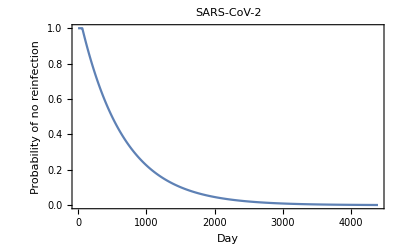

```mathematica
ListLinePlot[sarscov2probnoreinfectiontimecourse,
PlotRange->{0,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability of no reinfection"}]
```

```mathematica
sarscov2continuousprobnoreinfection=Interpolation[sarscov2probnoreinfectiontimecourse]
```

InterpolatingFunction[…]

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.95],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{95.2762,3.17587,0.261031}

These are the 5% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.50],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{499.348,16.6449,1.36808}

These are the 50% quantiles (medians) for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.05],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{1948.92,64.9639,5.3395}

These are the 95% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
sarscov2probreinfectiondensity={};
day=0;
While[day<4393,
Increment[day];
AppendTo[sarscov2probreinfectiondensity, 
If[day<lengthabtc,
sarscov2probinfgivenaod[sarscov2antibodytimecourseplusexp[[day]]]*sarscov2probnoreinfectiontimecourse[[day]],
sarscov2probinfgivenaod[sarscov2antibodytimecourseplusexp[[lengthabtc]]]*sarscov2probnoreinfectiontimecourse[[day]]
]
]
];
```

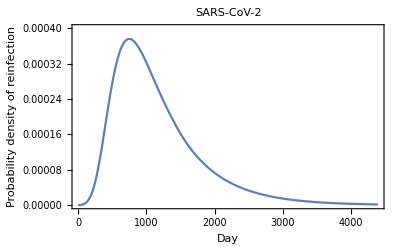

```mathematica
ListLinePlot[sarscov2probreinfectiondensity,
 PlotLabel->"SARS-CoV-2",
PlotRange->{0, 0.0004},
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability density of reinfection"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["SARS-CoV-2_PrInf-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2probreinfectiondensity,
 PlotLabel->"SARS-CoV-2",
PlotRange->{0, 0.0004},
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability density of reinfection"}]
]
```

SARS-CoV-2_PrInf-by-Day_21Jan2021.pdf